# Triangular Orbits in Elliptic Billiards

#### © Dan S. Reznik, Ronaldo Garcia, Jair Koiller, May 2019

## Idéias

To do intelligencer: show ellipse, conservation, open path, closed trajectory

Add cosine circle to p5.js

create p5.js w/ open trajectories and caustics

## Utils

```mathematica
SetDirectory["C:\\Users\\drezn\\Dropbox\\Mathematica\\Billiards"];
newCentersFromFile=Get["data/x0001_0100-no-hold.m"]; 
(*//Drop[#,{30}]&;*)(*EULER INFINITY POINT*)
```

```mathematica
toDeg[r_]:=180.*r/π;
toRad[d_]:=π*d/180.;
Clear@negl;negl[v_]:=Abs[v]<10^-9;
Clear@safeDiv;
safeDiv[num_,denom_]:=If[negl[denom],0,num/denom];
magn2[v_]:=v.v;
magn[v_]:=Sqrt[magn2[v]];
flipY[{x_,y_}]:={x,-y};
flipX[{x_,y_}]:={-x,y};
perp[{x_,y_}]:={-y,x};
perpNeg[{x_,y_}]:={y,-x};
crossProduct[{x1_,y1_},{x2_,y2_}]:=-x2 y1 + x1 *y2;
refl[v_,n_]:=2(v.n)n/magn2[n]-v;
norm[v_]:=v/magn[v];
clamp[v_,max_:100]:=If[v>max,max,If[v<-max,-max,v]];
ray[p0_,phat_,d_]:=p0+phat*d;
Clear@rot;
rot[p_,st_,ct_]:=Module[{m},
m={{ct,-st},{st,ct}};
m.p];
rot[p_,t_]:=rot[p,Sin@t,Cos@t];
rotRel[p_,t_,p0_]:=p0+rot[p-p0,t];
getEquilateral[th_]:=Module[{s=Sin[2π/3.],c=Cos[2π/3.]},
NestList[rot[#,s,c]&,rot[{1.,0.},Sin@th,Cos@th],2]];
```

```mathematica
subscriptTxt[prefix_,sub_]:=ToString[Subscript[prefix,sub],StandardForm];
subscriptTxtClr[prefix_,sub_,clr_]:=ToString[Style[Subscript[prefix,sub],clr],StandardForm];
padZ[v_,n_:4]:=ToString@NumberForm[v,{n,0},NumberPadding->{"0",""},NumberPoint->""];
```

```mathematica
closestPerp[p_,l1_,l2_]:=Module[{dl=l2-l1,s},
s=safeDiv[(p-l1).dl,dl.dl];
ray[l1,dl,s]];
```

```mathematica
Clear@quadRoots;
quadRoots[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
If[det<0,Print["quadRoots fail: {a,b,c}="<>ToString@{a,b,c}];False,
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)]];
Clear@interRays;
interRays[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose[{n1,n2}];(*{{nx1,-nx2},{ny1,-ny2}};*)
If[negl[Det[m]],p1,
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]]
];
interRaysIllConditioned[n1_,n2_]:=negl@Det@Transpose@{n1,n2};
interRaysUnprot[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose@{n1,n2};(*{{nx1,-nx2},{ny1,-ny2}};*)
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]
];
```

```mathematica
Second[l_]:=l[[2]];
Third[l_]:=l[[3]];
Fourth[l_]:=l[[4]];
Fifth[l_]:=l[[5]];
Sixth[l_]:=l[[6]];
Seventh[l_]:=l[[7]];
Eighth[l_]:=l[[8]];
Nineth[l_]:=l[[9]];
```

```mathematica
signedArea[poly_]:=(1/2)Total@MapThread[(#1[[1]]#2[[2]]-#2[[1]]#1[[2]])&,{poly,RotateLeft@poly}];
```

#### Triangles

```mathematica
Clear@s;
```

```mathematica
cosHalfAngle[cosAngle_]:=Sqrt[(1.+cosAngle)/2];(* careful: plus or minus *)
sinHalfAngle[cosAngle_]:=Sqrt[(1.-cosAngle)/2];
tanHalfAngle[sinAngle_,cosAngle_]:=sinAngle/(1+cosAngle);
(* careful: plus or minus *)
cosDoubleAngle[cosAngle_]:=2*cosAngle*cosAngle-1.; (* cA^2-sA^2 = 2 cA^2-1 *)
sinDoubleAngle[sinAngle_]:=2*sinAngle*Sqrt[1.-sinAngle^2];(* 2 sA cA *)
sinDoubleAngle[sinAngle_,cosAngle_]:=2*sinAngle*cosAngle;(* 2 sA cA *)
(* gives cos(A) *)
lawOfCosines[a_,b_,c_]:=(b^2+c^2-a^2)/(2.b c);
lawOfCosines3[a_,b_,c_]:={lawOfCosines[a,b,c],lawOfCosines[b,c,a],lawOfCosines[c,a,b]};
getSin[theCos_]:=Sqrt[1.-theCos^2];
lawOfCosinesSymbol[a_,b_,c_]:=(b^2+c^2-a^2)/(2b c);
getSinSymbol[theCos_]:=Sqrt[1-theCos^2];
(* cos(3t) = cos(2t+t) = c2 c - s2t s; *)
(* sin(3t) = sin(2t+t) = s2 c + s c2 *)
sinCosTripleAngle[s_,c_,s2_,c2_]:=Module[{s3,c3},
c3=c2 c-s2 s;
s3=s2 c+s c2;
{s3,c3}];
cosTripleAngle[c_]:=4c^3-3c;
getSinCosApB[sa_,sb_,ca_,cb_]:={sa cb + sb ca ,ca cb - sa sb};
getSinCosAmB[sa_,sb_,ca_,cb_]:= {sa cb - sb ca,ca cb + sa sb};
getSinApmB[sa_,sb_,ca_,cb_]:= {sa cb + sb ca,sa cb - sb ca};
```

```mathematica
testCosTriple[t_]:=Module[{c,s3,c3,c3a,s,c2,s2},
{c,s}={Cos@t,Sin@t};
c3a=cosTripleAngle[c];
c2=cosDoubleAngle[c];
s2=sinDoubleAngle[s,c];
{s3,c3}=sinCosTripleAngle[s,c,s2,c2];
{c3a,c3}];
```

```mathematica
(*Plot[testCosTriple[t],{t,0,2π}]*)
```

```mathematica
cosDiffAngle[sa_,ca_,sb_,cb_]:=ca cb+sa sb;
cosSumAngle[sa_,ca_,sb_,cb_]:=ca cb-sa sb;
(* compute sin^2(A/2), by passing cosA *)
sin2HalfAngle[cosAngle_]:=(1-cosAngle)/2;(* sinHalfAngle[cos]^2 *)
cos2HalfAngle[cosAngle_]:=(1+cosAngle)/2;(* cosHalfAngle[cos]^2 *)
```

```mathematica
Clear@cosThird;
cosThird[cos_]:=Chop@N@Re[Module[{sin=Sqrt[1-cos^2]},
((cos+I sin)^(-1/3)+(cos+I sin)^(1/3))/2]];
```

```mathematica
Clear@getBisector;
getBisector[vbase_,v1_,v2_]:=Module[{v01,v02},
v01=norm[v1-vbase];
v02=norm[v2-vbase];
norm[v01+v02]];
```

```mathematica
Clear@getTriBisectors;
getTriBisectors[p1_,p2_,p3_]:=Module[{u12,u23,u31},
u12=norm[p2-p1];
u23=norm[p3-p2];
u31=norm[p1-p3];
{
norm[u12-u31],
norm[u23-u12],
norm[u31-u23]
}
];
```

```mathematica
export3[name_,plot_]:=Module[{subdir="pics/"},
Export[subdir<>name<>".pdf",plot];
Export[subdir<>name<>".eps",plot];
Export[subdir<>name<>".png",plot];
];
```

```mathematica
export4[name_,plot_]:=Module[{subdir="pics/"},
Export[subdir<>name<>".pdf",plot];
Export[subdir<>name<>".eps",plot];
Export[subdir<>name<>".png",plot];
Export[subdir<>name<>".svg",plot];
];
```

#### Circle

-Graphics-

```mathematica
Clear@circleInter;
circleInter[c1_,r1_,c2_,r2_]:=Module[{d,x,y,chat},
d=magn[c2-c1];
chat=(c2-c1)/d;
x=(d^2-r2^2+r1^2)/(2d);
y=Sqrt[r1^2-x^2];
{c1+x chat+y perp[chat],c1+x chat-y perp[chat]}];
```

```mathematica
Manipulate[Module[{is},
is=circleInter[c1,1,c2,1.5];
Graphics[{Circle[c1,1],Circle[c2,1.5],Red,PointSize@Large,Point@is},PlotRange->{{-2,2},{-2,2}}]],
{{c1,{-1,-.5}},Locator},
{{c2,{1.25,.25}},Locator}]
```

#### Ellipse

```mathematica
Solve[(x/a)^2+(y/b)^2==1 ,y]//FullSimplify[#,a>0]&
```

{{y→-(b √((a-x) (a+x)))/a},{y→(b √((a-x) (a+x)))/a}}

```mathematica
ellEqn[a_,x_,y_]:=(x/a)^2+y^2-1;
ellEqnb[a_,b_,x_,y_]:=(x/a)^2+(y/b)^2-1;
ellGrad[a_,x_,y_]:=-{x,y a^2};(* (x/a)^2+y^2==1 *)
ellGradb[a_,b_,x_,y_]:=-2{x/a^2,y/b^2};(* (x/a)^2+y^2==1 *)
ellY[a_,x_]:=Sqrt[1-(x/a)^2];
ellYb[a_,b_,x_]:=b Sqrt[1-(x/a)^2];(*(x/a)^2+(y/b)^2==1 *);
ellError[a_,b_,{x_,y_}]:=(x/a)^2+(y/b)^2-1;
Clear@eccentricity;eccentricity[a_,b_]:=Sqrt[1-(b/a)^2];
ellPerimeterRamanujan2[a_,b_]:=Module[{h=((a-b)/(a+b))^2},
π(a+b)(1+3h/(10+Sqrt[4-3h]))];
ellPerimeterRamanujan[a_,b_]:=π(3(a+b)-Sqrt[(3a+b)(a+3b)]);
ellPerimeter[a_,b_]:=Module[{ecc=eccentricity[a,b]},4*a*EllipticE[ecc^2]];
ellArea[a_,b_]:=π a b;
focalDistance[a_,b_]:=Sqrt[a^2-b^2];
Clear@getFoci;getFoci[a_]:=Module[{c},If[a<1,c=Sqrt[1-a^2];{{0,c},{0,-c}},c=Sqrt[a^2-1];{{-c,0},{c,0}}]];
getFocib[a_,b_]:=b*getFoci[a/b];
```

```mathematica
(*ellRayCoeffs=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqn[a,r[[1]],r[[2]]],Assumptions->a>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
FullSimplify[a^2 CoefficientList[eqn,s],a>0]]*)
```

```mathematica
Clear@ellInterRay;
ellInterRay[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRoots[c2,c1,c0];
If[ListQ[ss],
ray[{x,y},{nx,ny},#]&/@ss,
{{0,0},{0,0}}]
];
```

Used for Proofs

```mathematica
quadRootsUnprot[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)];Clear@ellInterRayUnprot;

ellInterRayUnprot[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];
```

```mathematica
(*ellRayCoeffsB=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqnb[a,b,r[[1]],r[[2]]],Assumptions->a>0&&b>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
Together/@FullSimplify[CoefficientList[eqn,s],a>0&&b>0]]*)
```

```mathematica
ellInterRaybUnprot[a_,b_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=b^2 nx^2+a^2 ny^2;
c1=2 (b^2 nx x+a^2 ny y);
c0=-a^2 b^2+b^2 x^2+a^2 y^2;
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];
```

```mathematica
Clear@ellInterRaybUnprotAny;
ellInterRaybUnprotAny[a_,b_,ctr_,axisA_,axisB_,p_,dir_]:=Module[{m,p0,dir0,inter0},
m={axisA,axisB};
p0=m.(p-ctr);
dir0=m.dir;
inter0=ellInterRaybUnprot[a,b,p0,dir0];
(Transpose[m].#+ctr)&/@inter0];
```

```mathematica
DynamicModule[{gr,xmax=2,ymax=2,axis1,axis2,t,interP1P2,lgt=.33},
Manipulate[
t=toRad@tDeg;
axis1={Cos@t,Sin@t};
axis2=perp@axis1;
interP1P2=ellInterRaybUnprotAny[a,b,ctr,axis1,axis2,p1,p2-p1];
gr=Graphics[{PointSize@Medium,
{Arrowheads@Medium,Arrow@{ctr,ctr+lgt axis1},Arrow@{ctr,ctr+lgt axis2}},
{Rotate[{Circle[ctr,{a,b}],Dashed,Line@{{-a,0},{a,0}},Line@{{0,-b},{0,b}}},t]},
{PointSize@Large,Blue,Point@interP1P2[[1]],Red,Point@interP1P2[[2]],Black,Line@interP1P2}
}];
Show[{gr},PlotRange->{{-xmax,xmax},{-ymax,ymax}}],
{{a,1.5},.5,2,.1,Appearance->"Labeled"},
{{b,1},.5,2,.1,Appearance->"Labeled"},
{{tDeg,30,"θ"},-180,180,.1,Appearance->"Labeled"},
{{ctr,{0,0}},Locator},
{{p1,{.5,.75}},Locator},
{{p2,{-.5,.25}},Locator}]]
```

```mathematica
(* works for circle: a==1 *)
Clear@ellTangents;
ellTangents[a_,p_]:=Module[{a2,px,py,px2,px3,py2,radicand,numFact,denomx,denomy},
{px,py}=p;
a2=a*a;
px2=px*px;py2=py*py;
px3=px*px2;
denomx=px3+a2 px py2;
denomy=px2+a2 py2;
radicand=px2+a2(py2-1);
numFact=Sqrt[radicand]*Abs[px];
(*["radicand=",radicand,", numFact=",numFact,", dx=",denomx,", dy=",denomy];*)
(* NOTE: the first one is Clockwise, the 2nd one is CCW *)
{{a2 safeDiv[px2+py numFact,denomx],safeDiv[a2 py-numFact,denomy]},
{a2 safeDiv[px2-py numFact,denomx],safeDiv[a2 py+numFact,denomy]}}
];
```

```mathematica
(* hack *)
(*tangsToCirc[ctr_,r_,p_]:=(ctr+r#)&/@ ellTangents[1.,(p-ctr)/r];*)
```

```mathematica
Clear@ellTangentsb;
ellTangentsb[a_,b_,p_]:=
Module[{a2,b2,px,py,px2,px3,py2,py3,radicand,numFact,denomx,denomy},
{px,py}=p;
a2=a*a;
b2=b*b;
px2=px*px;py2=py*py;
px3=px*px2;py3=py*py2;
denomx=b2 px2 +a2 py2;
denomy=b2 px2 py+a2 py3;
radicand= b2 px2+a2(py2-b2);
numFact=Sqrt[radicand]*Abs[py];
(*Print["radicand=",radicand,", numFact=",numFact,", dx=",denomx,", dy=",denomy];*)
(* NOTE: Reverse[] so first one is Clockwise, the 2nd one is CCW *)
Reverse@{{a2 safeDiv[b2 px- numFact,denomx],b2 safeDiv[a2 py2+px numFact,denomy]},
{a2 safeDiv[b2 px+ numFact,denomx],b2 safeDiv[a2 py2-px numFact,denomy]}}
];
```

-Graphics--Graphics-

```mathematica
Clear@tangsToCirc;
tangsToCirc[ctr_,R_,P_]:=Module[{d,t1,t2,xhat,yhat},
d=magn[P-ctr];
xhat=(P-ctr)/d;
yhat=perp[xhat];
If[d<R,t1=ctr+R xhat;{t1,t1},
t1={R,Sqrt[d^2-R^2]}/d;
t2=flipY@t1;
(ctr+R#.{xhat,yhat})&/@{t1,t2}]];
```

```mathematica
DynamicModule[{ts,gr},
Manipulate[
ts=tangsToCirc[ctr,R,P];
gr=Graphics[{PointSize@Large,Thick,
{Circle[ctr,R],Point@ctr,Point@P,Line@{ctr,P}},
{Red,Point@ts,Dashed,Line@{P,#}&/@ts,Line@ts},
MapThread[Text[Style[#1,20],#2,{-1.5,-1.5}]&,{{"O","P"},{ctr,P}}]}];
Show[{gr},PlotRange->{{-1.1,3},{-2,2}}],
{{R,1},.1,2,.01},
{{ctr,{0,0}},Locator},
{{P,{2,0}},Locator}]]
```

#### Hyperbola

```mathematica
hypC[a_,b_]:=a^2+b^2;
hypEqn[a_,b_,{x_,y_}]:=(x/a)^2-(y/b)^2==1;
hypErr[a_,b_,{x_,y_}]:=(x/a)^2-(y/b)^2-1;
hypGrad[a_,b_,{x_,y_}]:=-{x b^2,-y a^2};
```

```mathematica
hypParam[a_,b_,t_]:=Module[{x,y},
x=a Cosh[t];
y=b Sinh[t];
{{x,y},{-x,-y}}];
```

#### Triangles

```mathematica
Clear@triSides;triSides[vs_]:=MapThread[(#1-#2)&,{vs,RotateLeft@vs}];
Clear@triLengths;triLengths[vs_]:=magn/@triSides[vs];
Clear@triLengthsRL;triLengthsRL[vs_]:=RotateLeft@triLengths@vs;
triPer[tri_]:=Total[triLengths@tri];
(* a,b,c are side lengths *)
Clear@triAreaHeron;triAreaHeron[{a_,b_,c_}]:=Module[{s},
s=(a+b+c)/2;(* semi perimeter *)
Sqrt[s*(s-a)*(s-b)*(s-c)]];
(* order by oposition to vertices *)
getMedians[t1_,t2_,t3_]:={t2+t3,t1+t3,t1+t2}/2;
getMediansV[vs_]:=.5(vs+RotateLeft@vs);
```

```mathematica
Clear@getInradius;getInradius[{a_,b_,c_}]:=Module[{num1,num2,num3,denom},
num1=b+c-a;
num2=c+a-b;
num3=a+b-c;
denom=a+b+c;
Sqrt[num1*num2*num3/denom]/2];
```

```mathematica
getCircumradius[{a_,b_,c_}]:=Module[{s,num,denom1,denom2,denom3},
s=(a+b+c)/2;
num=a*b*c;
denom1=(a+b-s);
denom2=(a+c-s);
denom3=(b+c-s);
num/(4*Sqrt[s*denom1*denom2*denom3])];
```

```mathematica
getNinepointCircleRadius[sides_]:=getCircumradius[sides]/2;
```

```mathematica
getTriData[tri_]:=Module[{sides,perimeter,inc,inradius,circumradius,cosines,bisectors,area},
sides=RotateLeft@triLengths@tri;
perimeter=Total@sides;
inradius=getInradius[sides];
circumradius=getCircumradius[sides];
cosines=getTriCosines[tri];
bisectors=getTriBisectors@@tri;
area=inradius*perimeter/2;
{"sides"->sides,
"perimeter"->perimeter,
"inradius"->inradius,
"circumradius"->circumradius,
"rOvR"->inradius/circumradius,
"cosines"->cosines,
"area"->area,
"bisectors"->bisectors}];
```

```mathematica
getSubtriData[tri_]:=Module[{sides,inc,tps,incR,npc,npcR},
sides=triLengthsRL@tri;
inc=getIncenterTrilin[tri,sides];
(* the intouchpoints of this guy is on the billiard, needs to draw them *)
tps=intouchTriangle[tri,sides];
incR=getInradius[sides];
npc=getNinepointCenterTrilin[tri,sides];
npcR=getNinepointCircleRadius[sides];
<|"tri"->tri,"sides"->sides,"inc"->inc,"incR"->incR,"npc"->npc,"npcR"->npcR,"tps"->tps|>];
```

```mathematica
Clear@getAnticomplData;
getAnticomplData[orbit_,sides_]:=
getSubtriData@anticomplementaryTriangle[orbit,sides];
```

```mathematica
Clear@getMedialData;
getMedialData[orbit_,sides_]:=
getSubtriData@medialTriangle[orbit,sides];
```

```mathematica
getIncenterAxes[a_]:=Module[{δ,a1,b1},
δ=Sqrt[a^4-a^2+1];
a1=(δ-1)/a;b1=(a^2-δ);
{a1,b1}];
```

```mathematica
getExcenterAxes[a_]:=Module[{δ,ae,be},
δ=Sqrt[a^4-a^2+1];
ae=(δ+1)/a;be=(a^2+δ);
{ae,be}];
```

```mathematica
Clear@getCircularity;
getCircularity[locus_]:=Module[{rads,ctr,mean,sd},
(* assume it's zero since points may not be evenly distributed so "mean" won't work and RegionCentroid is too slow *)
ctr={0,0};
rads=magn[#-ctr]&/@locus;
mean=Mean@rads;
sd=StandardDeviation@rads;
{
"n"->Length@locus,
"ctr"->ctr,
"min"->Min@rads,
"max"->Max@rads,
"mean"->mean,
"sd"->sd,
"zscore"->sd/mean
}];
```

```mathematica
Clear@txtSubscript;
txtSubscript[txt_,subscr_,style_,where_,offset_:{0,0}]:=Text[Style[Subscript[txt,subscr],style],where,offset];
Clear@txtSuperSub;
txtSuperSub[txt_,superscr_,subscr_,style_,where_,offset_:{0,0}]:=Text[Style[Subsuperscript[txt,subscr,superscr],style],where,offset];
Clear@txtSubscriptSuffix;
txtSubscriptSuffix[txt_,subscr_,suffix_,style_,where_,offset_:{0,0}]:=Text[Style[ToString[Subscript[txt,subscr],FormatType->StandardForm]<>suffix,style],where,offset];
```

```mathematica
Clear@ellLabel;
Options@ellLabel={inward->False};
ellLabel[a_,p_,lgt_,OptionsPattern[]]:=p+If[OptionValue@inward,lgt,-lgt]*norm[ellGrad[a,Sequence@@p]];
Clear@ellLabelb;
Options@ellLabelb={inward->False};
ellLabelb[a_,b_,p_,lgt_,OptionsPattern[]]:=p+If[OptionValue@inward,lgt,-lgt]*norm@ellGradb[a,b,Sequence@@p];
Clear@ellLabelTxt;
Options@ellLabelTxtb={inward->False};
ellLabelTxtb[a_,b_,p_,txt_,lgt_,opts:OptionsPattern[]]:=Text[txt,ellLabelb[a,b,p,lgt,{opts}]];
Clear@ellLabelTxt;
Options@ellLabelTxt={inward->False};
ellLabelTxt[a_,p_,txt_,lgt_,opts:OptionsPattern[]]:=Text[txt,ellLabel[a,p,lgt,{opts}],{0,0}];
```

```mathematica
Clear@labelPoints;labelPoints[pts_,prefix_,style_,offset_:{0,0}]:=MapThread[txtSubscript[prefix,#1,style,#2,offset]&,{Range@Length@pts,pts}];
Clear@ellLabelPoints;
ellLabelPoints[a_,pts_,prefix_,style_,lgt_:.33]:=MapThread[txtSubscript[prefix,#1,style,ellLabel[a,#2,lgt]]&,{Range@Length@pts,pts}];
ellLabelPointsSuperSub[a_,pts_,prefix_,super_,style_,lgt_:.33]:=MapThread[txtSuperSub[prefix,super,#1,style,ellLabel[a,#2,lgt]]&,{Range@Length@pts,pts}];
ellLabelPointsSuffix[a_,pts_,prefix_,suffixes_,style_,lgt_:.33]:=MapThread[txtSubscriptSuffix[prefix,#1,#3,style,ellLabel[a,#2,lgt]]&,{Range@Length@pts,pts,suffixes}];
Clear@ellLabelPointsSuffixb;ellLabelPointsSuffixb[a_,b_,pts_,prefix_,suffixes_,style_,lgt_:.33]:=MapThread[txtSubscriptSuffix[prefix,#1,#3,style,ellLabelb[a,b,#2,lgt]]&,{Range@Length@pts,pts,suffixes}];
Clear@ellLabelPointsb;
ellLabelPointsb[a_,b_,pts_,prefix_,style_,lgt_:.33]:=MapThread[txtSubscript[prefix,#1,style,ellLabelb[a,b,#2,lgt]]&,{Range@Length@pts,pts}];
Clear@ellLabelPointsbInward;
ellLabelPointsbInward[a_,b_,pts_,prefix_,style_,lgt_:.33]:=MapThread[txtSubscript[prefix,#1,style,ellLabelb[a,b,#2,lgt,inward->True]]&,{Range@Length@pts,pts}];
```

```mathematica
Clear@getStats;
Options@getStats={label->""};
getStats[vals_,OptionsPattern[]]:=Module[{mean,sd,z},
mean=Mean@vals;
sd=StandardDeviation@vals;
z=safeDiv[sd,mean];
<|"n"->Length@vals,"mean"->mean,"sd"->sd,"z"->z,"min"->Min@vals,"max"->Max@vals,"median"->Median@vals,"label"->OptionValue@label|>];
```

Formatting

```mathematica
nfn[v_,n_]:=ToString@NumberForm[v,{n+2,n}];
nf[v_]:=ToString@NumberForm[v,{3,2}];
nf1[v_]:=ToString@NumberForm[v,{3,1}];
nf0[v_]:=ToString@IntegerPart[v];
padZ[v_,n_:4]:=ToString@NumberForm[v,{n,0},NumberPadding->{"0",""},NumberPoint->""];
```

```mathematica
Clear@getBilliardAngle;
getBilliardAngle[a_,b_,{px_,py_}]:=
ArcTan[px/a,py/b];
```

-Graphics-

```mathematica
stereographicProj[x_,y_]:=Module[{c=x*x+y*y},
{2x,2y,c-1}/(c+1)];
```

#### imagine point at (x0, y0, 1), on plane tangent and above sphere x^2+y^2+z^2=1. line from center to point: p(t) = t (x0,y0,1) p(t) on sphere ⇔ t^2 (x0^2+y0^2+1) = 1 ⇒ t^2=1/(...) ⇒ p = (x0,y0,1)/sqrt(x0^2+y0^2+1) = (x0,y0,1)/α

-Graphics-

### r = 1, z=1/α ⇒ θ = arccos(1/α) y/x=tan[ϕ] ⇒ ϕ = arctan[y/x] = arctan[y0/x0]

```mathematica
sphereProj[x0_,y0_]:=Module[{α=Sqrt[x0^2+y0^2+1]},
{1/α,y0/x0}]
```

```mathematica
sphereProj2[x0_,y0_]:=Module[{α=x0^2+y0^2},
{x0,y0}/α]
```

```mathematica
sphereProj3[x0_,y0_]:=Module[{α=x0^2+y0^2},
{x0,y0}/Sqrt@α]
```

```mathematica
logProj[x0_,y0_]:=Module[{α=Log[1+x0^2+y0^2]},
{x0,y0}/α]
```

```mathematica
Clear@makeMovie;
makeMovie[fname_,frames_,repeats_:3]:=Module[{framesConcat},
framesConcat=Flatten@ConstantArray[frames,repeats];
Print["Exporting "<>ToString@Length[framesConcat]<>" frames to "<>fname];
Export[fname,framesConcat,"VideoEncoding"->"MPEG-4 Video"];
];
```

#### Envelope Aux [most code on companion envelopes.nb]

```mathematica
Clear@getEnvelope;(* via intersection *)
Options@getEnvelope={epsDeg->.001,tDeg2Phase->0};
getEnvelope[a_?NumericQ,tDeg_?NumericQ,trilfn1_,trilfn2_,OptionsPattern[]]:=Module[{ons,onsPhase,p1,q1,p2,q2},
ons=orbitNormals[a,toRad@(tDeg-.5OptionValue@epsDeg)];
{p1,q1}=If[OptionValue@tDeg2Phase>0,
onsPhase=orbitNormals[a,toRad@(tDeg-.5OptionValue@epsDeg+OptionValue@tDeg2Phase)];
{trilfn1[ons[[1]],ons[[3]]],trilfn1[onsPhase[[1]],onsPhase[[3]]]},
#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2}
];
ons=orbitNormals[a,toRad@(tDeg+.5OptionValue@epsDeg)];
{p2,q2}=If[OptionValue@tDeg2Phase>0,
onsPhase=orbitNormals[a,toRad@(tDeg+.5OptionValue@epsDeg+OptionValue@tDeg2Phase)];
{trilfn1[ons[[1]],ons[[3]]],trilfn1[onsPhase[[1]],onsPhase[[3]]]},
#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2}
];
interRaysUnprot[p1,(q1-p1),p2,(q2-p2)]];
```

```mathematica
Clear@getEnvelopeb;
getEnvelopeb[a_?NumericQ,b_?NumericQ,tDeg_?NumericQ,trilfn1_,trilfn2_,epsDeg_:.001]:=Module[{ons,p1,q1,p2,q2},
ons=orbitNormalsb[a,b,toRad@tDeg];{p1,q1}=#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2};
ons=orbitNormalsb[a,b,toRad@(tDeg+epsDeg)];{p2,q2}=#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2};
interRaysUnprot[p1,(q1-p1),p2,(q2-p2)]];
```

```mathematica
(* new *)Clear@getEnvelopeLocus;
Options@getEnvelopeLocus=Options@getEnvelope;
getEnvelopeLocus[a_,trilinFn1_,trilinFn2_,ps_,opts:OptionsPattern[]]:=Module[{pp,ons},
pp=Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg];getEnvelope[a,tDeg,trilinFn1,trilinFn2,FilterRules[{opts},Options@getEnvelope]],{tDeg,0,360},
PerformanceGoal->"Speed",PlotStyle->ps]];
```

```mathematica
rayCircTs=Normal/@(t/.FullSimplify[Solve[magn2[{x0,y0}+{xhat,yhat} t-{ox,oy}]==R^2,t,Reals]])
```

{-(-ox xhat+x0 xhat-oy yhat+y0 yhat+√(-oy^2 xhat^2+2 oy xhat (xhat y0+(ox-x0) yhat)-(xhat y0+(ox-x0) yhat)^2+R^2 (xhat^2+yhat^2)))/(xhat^2+yhat^2),(ox xhat-x0 xhat+oy yhat-y0 yhat+√(-oy^2 xhat^2+2 oy xhat (xhat y0+(ox-x0) yhat)-(xhat y0+(ox-x0) yhat)^2+R^2 (xhat^2+yhat^2)))/(xhat^2+yhat^2)}

```mathematica
interRayCircTs[{x0_,y0_},{xhat_,yhat_},{ox_,oy_},R_]=rayCircTs;
```

```mathematica
interRayCirc[r0_,rhat_,ctr_,R_]:=Module[{ts},
ts=interRayCircTs[r0,rhat,ctr,R];
ray[r0,rhat,#]&/@ts];
```

```mathematica
colorStr[str_,clr_]:=ToString[Style[str,clr],StandardForm]
```

```mathematica
(* for organizing buttons in manipulate UI *)
makeCtrlCol[ctrls_]:=Column[{Style[First@ctrls,Bold,Medium],Sequence@@Rest[ctrls]},Alignment->Right,BaselinePosition->1];
```

## Ellipse Inversion, Isogonal and Isotomic Conjugates

-Graphics-
https://arxiv.org/pdf/1309.6378.pdf

```mathematica
Clear@ellInversion;
ellInversion[a_,p_]:=Module[{q,w,p2},
q=ellInterRayUnprot[a,{0,0},p][[2]];
w=q.q;
p2=p.p;
{p*w/p2,q}]
```

```mathematica
ellInversion[1.5,{.5,.5}]
```

{{1.38462,1.38462},{0.83205,0.83205}}

```mathematica
Manipulate[
DynamicModule[{a=1.5,ell,pinv,q,fs,gr},
{ell,fs}={plotEll[a],getFoci[a]};
Dynamic[{pinv,q}=ellInversion[a,p];
gr=Graphics[{PointSize@Large,Point@fs,Red,Point@pinv,Dashed,Line[{p,pinv}],Blue,Point@q}];
Show[{ell,gr},Frame->True,PlotRange->{{-2a,2a},{-2,2}},
PlotLabel->(Style["Inversion with Respect to Ellipse",{Black,Medium}])]]],
{{p,{.5,.5}},Locator},SaveDefinitions->True]
```

```mathematica
(*CloudDeploy[%,"inversion with respect to ellipse",Permissions->"Public"]*)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
Clear@isogonalConjugate;
isogonalConjugate[p_,tri_,bisectors_]:=Module[{refla,reflb,inter},
refla=refl[p-First@tri,First@bisectors];
reflb=refl[p-Second@tri,Second@bisectors];
inter=interRaysUnprot[First@tri,refla,Second@tri,reflb];
inter];
```

```mathematica
(* could use cevianTriangle, but needs conversion from cartesian to trilinear *)
```

```mathematica
Clear@isotomicConjugate;
isotomicConjugate[p_,tri_]:=Module[{inters,meds,isos,n1,n2,n3,isoConj},
inters=MapThread[interRays[#1,p-#1,#2,#3-#2]&,{tri,RotateLeft@tri,RotateRight@tri}];
meds=getMedians@@tri;
isos=MapThread[(2#1-#2)&,{meds,inters}];
n1=isos[[1]]-tri[[1]];
n2=isos[[2]]-tri[[2]];
n3=isos[[3]]-tri[[3]];
isoConj=Which[
!interRaysIllConditioned[n1,n2],interRaysUnprot[tri[[1]],n1,tri[[2]],n2],
!interRaysIllConditioned[n1,n3],interRaysUnprot[tri[[1]],n1,tri[[3]],n3],
True,interRaysUnprot[tri[[2]],n2,tri[[3]],n3]];
<|"p"->p,"tri"->tri,"pconj"->isoConj,"inters"->inters,"meds"->meds,"isos"->isos|>];
```

```mathematica
Clear@showIsotomicConjugate;
Options@showIsotomicConjugate={drGr->False,"drLines"->False,drLabels->False,drLogQprime->False,drPs->True};
showIsotomicConjugate[p_,tri_,OptionsPattern[]]:=Module[{isoData,gr,grLines,grLabels,txtD=-1.25},
isoData=isotomicConjugate[p,tri];
gr=If[OptionValue@drGr,{
{FaceForm@None,PointSize@Large,
{Blue,Point@p},
If[OptionValue@drPs,{Blue,Text[Style["Q",16],p,{txtD,txtD}]},{}],
{EdgeForm@Black,Polygon@tri,Point@tri,labelPoints[tri,"P",16,{-2,0}]},
{Purple,Point@isoData["meds"]},
{Blue,Point@isoData["inters"]},
{Darker@Green,Point@isoData["isos"],Point@isoData["pconj"]},
If[OptionValue@drPs,Text[Style["Q'",16],isoData["pconj"],{txtD,txtD}],{}],
If[OptionValue@drLogQprime,Module[{isoConjLog},isoConjLog=isoData["pconj"]@Log[1+norm@isoData["pconj"]];
{Darker@Green,Point@isoConjLog,Text[Style["log[Q']",16],isoConjLog,{txtD,txtD}]}],{}]}
},{}];
grLines=If[OptionValue@"drLines",{Dashed,
{Blue,MapThread[Line[{#1,#2}]&,{tri,isoData["inters"]}]},
{Darker@Green,MapThread[Line[{#1,#2}]&,{tri,isoData["isos"]}]}},{}];
grLabels=If[OptionValue@drLabels,{
{Red,labelPoints[isoData["meds"],"m",16,{txtD,0}]},
{Blue,labelPoints[isoData["inters"],"i",16,{txtD,0}]},
{Darker@Green,labelPoints[isoData["isos"],"iso",16,{txtD,0}]}},{}];
{isoData["pconj"],Graphics/@{gr,grLines,grLabels}}];
```

```mathematica
Manipulate[
DynamicModule[{tri,actData,isoGr,actGr},
tri={{0,0},p2,p3};
isoGr=showIsotomicConjugate[p0,tri,drGr->True,"drLines"->drLines0,drLabels->drLabels0,drLogQprime->drLogQprime0][[2]];
actGr=If[drACT,
actData=getAnticomplData[tri,triLengthsRL@tri];
Graphics@{FaceForm@None,EdgeForm@{Blue,Dashed},Polygon@actData["tri"],Darker@Green,Circle[actData["inc"],actData["incR"]],PointSize@Medium,Point@actData["tps"]},
{}];
Show[{isoGr,actGr},
ImageSize->Large,
Frame->True,PlotRange->{{-5,5},{-5,5}},PlotLabel->Style["Isotomic Conjugate: Move Q or P_3",{Black,Medium}]]],
{{p0,{.75,.5}},Locator},
{{p2,{1,0}},Locator},
{{p3,{2,2}},Locator},
{{drLines0,False,"isotomic lines"},{True,False}},
{{drLabels0,False,"label points"},{True,False}},
{{drLogQprime0,False,"log Q'"},{True,False}},
{{drACT,False,"anticompl"},{True,False}}]
```

```mathematica
(*DeleteFile[isotApp]*)
```

```mathematica
(*isotApp=CloudDeploy[%,"isotomic conjugate",Permissions->"Public"]*)
```

```mathematica
DynamicModule[{p1={0,0},p2={1,0},gr,tri,bis,isogConj,isotConj,p0star,inc,bar,lgt=.2,lgtLine=3},
Manipulate[
tri={p1,p2,p3};
inc=getIncenter[tri];
bis=getTriBisectors@@tri;
p0star=isogonalConjugate[p0,tri,bis];
(*isoConj=showIsotomicConjugate[p0,tri][[1]];*)
isotConj=showIsotomicConjugate[p0,tri,drGr->True,"drLines"->drLinesIsot,"drLabels"->False,drPs->False];
gr=Graphics[{PointSize@Large,FaceForm@None,Arrowheads@Medium,
EdgeForm@{Thick,Black},Blue,Point@tri,Polygon@tri,Red,Point@p0star,Darker@Green,Point@isotConj[[1]],
{Blue,MapThread[Arrow@{#1,#1+lgt*#2}&,{tri,bis}]},
If[drLinesIsog,
{Gray,Line@{#,ray[#,norm[p0-#],lgtLine]}&/@tri,Red,Line@{#,ray[#,norm[p0star-#],lgtLine]}&/@tri},{}]}];
Show[{gr,
If[drLinesIsot,isotConj[[2]],{}]},Frame->False,ImageSize->Large,
PlotLabel->(Style["Isogonal and Isotomic Conjugates",{Medium,Black}]),
PlotRange->{{-.25,1.5},{-.25,1}}],
{{p3,{1.25,.75}},Locator},
{{p0,{.75,.1}},Locator},
{{drLinesIsog,False,"isogonal lines"},{True,False}},
{{drLinesIsot,False,"isotomic lines"},{True,False}},
SaveDefinitions->True]]
```

```mathematica
(*DeleteFile[isogApp]*)
```

```mathematica
(*isogApp=CloudDeploy[%,"isogonal conjugate",Permissions->"Public"]*)
```

## Cyclic Quadrilaterals

```mathematica
Clear@orderVertices;
orderVertices[vs_,ctr_]:=Module[{vs0,atans},
vs0=(#-ctr)&/@vs;
atans=ArcTan@@@vs0;
vs[[Ordering[atans]]]];
```

```mathematica
Pick[{a,b,c},{True,False,True}]
```

{a,c}

```mathematica
(* assume ordered *)
Clear@getMaltitudes;getMaltitudes[vs_]:=Module[{ls,vsNonDegen,meds,feet,lines},
ls=MapThread[magn2[#1-#2]&,{vs,RotateLeft@vs}];
vsNonDegen=Pick[vs,Not/@(negl/@ls)];
meds=MapThread[.5(#1+#2)&,{vsNonDegen,RotateLeft@vsNonDegen}];
feet=MapThread[closestPerp[#1,#2,#3]&,{meds,RotateLeft[vsNonDegen,2],RotateLeft[vsNonDegen,3]}];
lines=MapThread[{#1,#2}&,{meds,feet}];
<|"meds"->meds,"feet"->feet,"lines"->lines|>];
```

```mathematica
Manipulate[DynamicModule[{quad,gr,malts},
quad={p1,p2,p3,p4};
malts=getMaltitudes[quad];
gr=Graphics[{FaceForm@None,
{EdgeForm@Blue,Polygon@quad},
{Red,Dashed,Line/@malts["lines"]},
{PointSize@Large,Red,Point@malts["meds"]},
{PointSize@Large,Blue,Point@malts["feet"]}}];
Show[{gr},PlotRange->{{-1,1},{-1,1}}]],
{{p1,{-.5,-.5}},Locator},
{{p2,{.5,-.5}},Locator},
{{p3,{.5,.5}},Locator},
{{p4,{-.5,.5}},Locator}]
```

## Triangular Orbits

#### Ellipse Invariants

#### Constant Perimeter (Gaston Darboux, 1917)

#### -Graphics- Jean-Gaston Darboux (1842-1917)

```mathematica
deltaA[a_]:=Sqrt[a^4-a^2 +1];
```

```mathematica
Clear[darbouxP];
darbouxP[a_,b_:1]:=Module[{a2,b2,delta,per},
a2=a^2;
b2=b^2;
delta=Sqrt[a2^2-a2 b2+b2^2];
per=2Sqrt[2delta-a2-b2](a2+b2+delta)/(a2-b2);
per
];
```

#### Exit angle at x_1 which creates triangular orbit (Garcia, 2019)

-Graphics-

```mathematica
Clear@cosAlpha;cosAlpha[a_,x_]:=Module[{x2,a2,a4,c2,denom},
x2=x^2;
a2=a^2;
a4=a2^2;
c2=a2-1;
denom=c2 Sqrt[a4-c2 x2];
a2 Sqrt[-a2-1+2Sqrt[a4-c2]]/denom];
```

```mathematica
cosAlpha[a,x]//TeXForm
```

\frac{a^2 \sqrt{-a^2+2 \sqrt{a^4-a^2+1}-1}}{\left(a^2-1\right) \sqrt{a^4-\left(a^2-1\right) x^2}}

#### Can I find an expression for the next orbit point P_2 in terms of “a” and x_1

```mathematica
Clear@getP2;getP2[a_,x1_]:=Module[{y,p1,norm,ca,sa,p2,normRot,normRotNeg,p2Neg},
y=-ellY[a,x1];
p1={x1,y};
ca=cosAlpha[a,x1]/.{Sqrt[1-a^2+a^4]->d}/.{-1-a^2+2 d->d2};(* to simplify *)
sa=Sqrt[1-ca^2];
norm=ellGrad[a,x1,y];
normRot=rot[norm,sa,ca];
normRotNeg=rot[norm,-sa,ca];
p2=ellInterRayUnprot[a,p1,normRot][[2]]; (* get 2nd solution *)
p2Neg=ellInterRayUnprot[a,p1,normRotNeg][[2]]; 
{p2,p2Neg}];
```

```mathematica
Clear@getReflData;getReflData [a_,p0_,normal_,sinAlpha_,cosAlpha_]:=Module[{nRot,inter,interNorm,interRefl,nextInter,nextInterNorm},
nRot=rot[normal,sinAlpha,cosAlpha];
inter=ellInterRay[a,p0,nRot][[2]];
interNorm=norm[ellGrad[a,inter[[1]],inter[[2]]]];
interRefl=refl[norm[p0-inter],interNorm];
nextInter=ellInterRay[a,inter,interRefl][[2]];
nextInterNorm=norm[ellGrad[a,nextInter[[1]],nextInter[[2]]]];
{ (* returns an "object" *)
"nRot"->nRot,
"inter"->inter,
"interNorm"->interNorm,
"interRefl"->interRefl,
"nextInter"->nextInter,
"nextInterNorm"->nextInterNorm
}];
```

```mathematica
Clear@getReflDatab;getReflDatab [a_,b_,p0_,normal_,sinAlpha_,cosAlpha_]:=Module[{nRot,inter,interNorm,interRefl,nextInter,nextInterNorm},
nRot=rot[normal,sinAlpha,cosAlpha];
inter=ellInterRaybUnprot[a,b,p0,nRot][[2]];
interNorm=norm[ellGradb[a,b,inter[[1]],inter[[2]]]];
interRefl=refl[norm[p0-inter],interNorm];
nextInter=ellInterRaybUnprot[a,b,inter,interRefl][[2]];
nextInterNorm=norm[ellGradb[a,b,nextInter[[1]],nextInter[[2]]]];
{ (* returns an "object" *)
"nRot"->nRot,
"inter"->inter,
"interNorm"->interNorm,
"interRefl"->interRefl,
"nextInter"->nextInter,
"nextInterNorm"->nextInterNorm
}];
```

```mathematica
Clear@getOrbitData;
Options@getOrbitData={posY->False};getOrbitData[a_,x_,OptionsPattern[]]:=Module[{y,o1,n1,ca,sa,sa2,ca2,halfAlpha,pos,neg,orbit,sides},
y=-ellY[a,x];
If[OptionValue@posY,y=-y];
o1={x,y};
n1=norm[ellGrad[a,x,y]];
ca=cosAlpha[a,x];
sa=Sqrt[1-ca^2];
pos=getReflData[a,o1,n1,sa,ca];
neg=getReflData[a,o1,n1,-sa,ca];(* orbit at -α *)
(* half-angle to display α at bisector *)
sa2=Sqrt[(1-ca)/2];
ca2=Sqrt[(1+ca)/2];
halfAlpha=rot[n1,sa2,ca2];
orbit={o1,"inter"/.pos,"nextInter"/.pos};
sides=triLengthsRL@orbit;
{
"ca"->ca,
"sa"->sa,
"halfAlpha"->halfAlpha,
"nRot"->("nRot"/.pos),
"interRefl"->("interRefl"/.pos),
"orbit"->orbit,
"sides"->sides,
"normals"->{n1,"interNorm"/.pos,"nextInterNorm"/.pos},
"nRotNeg"->("nRot"/.neg),
"interReflNeg"->("interRefl"/.neg),
"orbitNeg"->{o1,"inter"/.neg,"nextInter"/.neg},
"normalsNeg"->{n1,"interNorm"/.neg,"nextInterNorm"/.neg}
}
];
```

```mathematica
Clear@getOrbitDatab;
Options@getOrbitDatab={posY->False};getOrbitDatab[a_,b_,x_,OptionsPattern[]]:=Module[{y,o1,n1,ca,sa,sa2,ca2,halfAlpha,pos,neg,orbit,sides},
y=-ellYb[a,b,x];
If[OptionValue@posY,y=-y];
o1={x,y};
n1=norm[ellGradb[a,b,x,y]];
ca=cosAlpha[a/b,x/b];
sa=Sqrt[1-ca^2];
pos=getReflDatab[a,b,o1,n1,sa,ca];
neg=getReflDatab[a,b,o1,n1,-sa,ca];(* orbit at -α *)
(* half-angle to display α at bisector *)
sa2=Sqrt[(1-ca)/2];
ca2=Sqrt[(1+ca)/2];
halfAlpha=rot[n1,sa2,ca2];
orbit={o1,"inter"/.pos,"nextInter"/.pos};
sides=triLengthsRL@orbit;
{
"ca"->ca,
"sa"->sa,
"halfAlpha"->halfAlpha,
"nRot"->("nRot"/.pos),
"interRefl"->("interRefl"/.pos),
"orbit"->orbit,
"sides"->sides,
"normals"->{n1,"interNorm"/.pos,"nextInterNorm"/.pos},
"nRotNeg"->("nRot"/.neg),
"interReflNeg"->("interRefl"/.neg),
"orbitNeg"->{o1,"inter"/.neg,"nextInter"/.neg},
"normalsNeg"->{n1,"interNorm"/.neg,"nextInterNorm"/.neg}
}
];
```

```mathematica
getOrbitData[2.,1.,posY->False]//ColumnForm
```

ca→0.549885
sa→0.835241
halfAlpha→{-0.699945,0.714197}
nRot→{-0.954984,0.296658}
interRefl→{0.999046,0.0436602}
orbit→{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}}
sides→{3.94273,1.45108,3.13704}
normals→{{-0.27735,0.960769},{0.991722,-0.128403},{-0.898933,-0.438085}}
nRotNeg→{0.649963,0.759966}
interReflNeg→{-0.999046,-0.0436602}
orbitNeg→{{1.,-0.866025},{1.94314,0.236743},{-1.99582,0.0646022}}
normalsNeg→{{-0.27735,0.960769},{-0.898933,-0.438085},{0.991722,-0.128403}}

```mathematica
{"orbit","sides"}/.getOrbitData[2.,1.,posY->False]
```

{{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}},{3.94273,1.45108,3.13704}}

```mathematica
Clear@orbitDataT;
orbitDataT[a_,t_]:=Module[{ellP},
ellP=N@{a  Cos@t,Sin@t};
getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)]
];
```

```mathematica
Clear@orbitNormals;
orbitNormals[a_,t_]:=Module[{ellP,orbitData},
ellP={N@a * Cos[N@t],Sin[N@t]};
orbitData=getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)];
{"orbit","normals","sides"}/.orbitData
];
```

```mathematica
Clear@orbitNormalsb;
orbitNormalsb[a_,b_,t_]:=Module[{ellP,orbitData},
ellP={a  Cos@t,b Sin@t};
orbitData=getOrbitDatab[a,b,ellP[[1]],posY->(ellP[[2]]>0)];
{"orbit","normals","sides"}/.orbitData
];
```

```mathematica
getTriCosines[tri_]:=Module[{u12,u23,u31},
u12=norm[tri[[2]]-tri[[1]]];
u23=norm[tri[[3]]-tri[[2]]];
u31=norm[tri[[1]]-tri[[3]]];
{
-u12.u31,
-u23.u12,
-u31.u23
}];
```

```mathematica
getTriDoubleCosineSum[tri_]:=Total[cosDoubleAngle/@getTriCosines@tri];
```

```mathematica
getOrbitCosines[a_,t_]:=Module[{orbit,normals,sides},
{orbit,normals,sides}=orbitNormals[a,t];
getTriCosines[orbit]];
```

```mathematica
Clear@getTriCausticParams;
getTriCausticParams[a_]:=Module[{px,qy,delta},
delta=Sqrt[a^4-a^2+1];
px=a^3/(delta+1);
qy=1/(a^2+delta);
{px,qy}];
```

```mathematica
getTriAreaRatioHelman[a_]:=Module[{ts,tris},
ts=Table[toRad@t,{t,0,359,1}];
tris=orbitNormals[a,#]&/@ts;
MapThread[{#1,Area[Polygon@First[#2]]/Sqrt@Apply[Times,Third@#2]}&,{ts,tris}]];
```

```mathematica
Clear@getGammaL;
getGammaL[a_,b_]:=Module[{δ,c2,γ,L,a2,b2},
a2=a^2;
b2=b^2;
δ=Sqrt@(a2^2-a2 b2+b2^2);
c2=a2-b2;
γ=Sqrt@(2δ-a2-b2)/c2;
L=2(δ+a2+b2)γ;
{γ,L}];
(* robust for contour plot *)
Clear@getGammaLsym;
getGammaLsym[a_?NumericQ,b_?NumericQ]:=Module[{eps=10^-6},If[a>=b,getGammaL[a+eps,b],getGammaL[b+eps,a]]];
```

```mathematica
getOrthocenterAxes[a_,b_]:=Module[{a2=a*a,b2=b*b,delta,k4,c2},
delta=Sqrt[a2^2-a2 b2+b2^2];
c2=a2-b2;
k4=((a2+b2)delta-2(a2 b2))/c2;
{k4/a,k4/b}];
```

```mathematica
getCausticAxes[a_,b_]:=Module[{a2=a^2,b2=b^2,delta,c2,ac,bc},
delta=Sqrt[a2^2-a2 b2+b2^2];
c2=a2-b2;
ac=a(delta-b2)/c2;
bc=b(a2-delta)/c2;
{ac,bc}];
```

```mathematica
getDelta[a_,b_]:=Sqrt[a^4-a^2 b^2+b^4];
```

```mathematica
rOvR[a_]:=Module[{δ=getDelta[a,1]},
2(δ-1)/((a^2-1)(a^2+δ))]
```

```mathematica
Clear@getJoachimsthal;
getJoachimsthal[a_,b_]:=Module[{δ,a2=a*a,b2=b*b,c2},
c2=a2-b2;
δ=Sqrt[a2^2-a2 b2+b2^2];
Sqrt[2δ-a2-b2]/c2];
```

```mathematica
isoscelesP2[a_,b_]:=Module[{J=getJoachimsthal[a,b],p1,costpp,sintpp,p2,p3},
costpp=J a;
sintpp=Sqrt[1-costpp^2];
p1={0,-b};
p2=FullSimplify[{a costpp,b sintpp},a>b>0];
p3=flipX@p2;
{p1,p2,p3}]
```

```mathematica
isoscelesP2[1.5,1]
```

{{0,-1},{1.45692,0.23795},{-1.45692,0.23795}}

```mathematica
getOrbitAxes[a_,trilinFn_]:=Module[{ons0,ons90},
ons0=orbitNormals[a,0.];
ons90=orbitNormals[a,π/2.];
Abs/@{trilinFn[ons0[[1]],ons0[[3]]][[1]],trilinFn[ons90[[1]],ons90[[3]]][[2]]}];
```

## Trilinears & Barycentrics

-Graphics-

```mathematica
getBarycentrics[{x_,y_},{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=Module[{detT,l1,l2,l3},
detT=(x1-x3)(y2-y3)-(x2-x3)(y1-y3);
l1=((y2-y3)(x-x3)+(x3-x2)(y-y3))/detT;
l2=((y3-y1)(x-x3)+(x1-x3)(y-y3))/detT;
l3=1-l1-l2;
{l1,l2,l3}];
```

Trilinears x : y : z convert via triangle vertices A, B, C  and sides a, b, c :

```mathematica
(* from barycentrics *)
getTrilinears[p_,tri_,sides_]:=Module[{bs},
MapThread[#1/#2&,{getBarycentrics[p,tri],sides}]]
```

```mathematica
Clear@trilinearToCartesianUnsafe;
trilinearToCartesianUnsafe[
{A_,B_,C_},(* vertices *)
{a_,b_,c_},(* side lengths *)
{x_,y_,z_} (* trilinears *)
]:=Module[{(*a,b,c,*)denom},
(* may not need *)
(*a=magn[C-B];b=magn[A-C];c=magn[B-A];*)
denom={a,b,c}.{x,y,z};
(#/denom)&/@(a x A+b y B+c z C)];
```

```mathematica
Clear@trilinearToCartesian;
trilinearToCartesian[
{A_,B_,C_},(* vertices *)
{a_,b_,c_},(* side lengths *)
{x_,y_,z_} (* trilinears *)
]:=Module[{(*a,b,c,*)denom},
(* may not need *)
(*a=magn[C-B];b=magn[A-C];c=magn[B-A];*)
denom={a,b,c}.{x,y,z};
safeDiv[#,denom]&/@(a x A+b y B+c z C)];
```

```mathematica
rotateSym[fabc_]:={fabc,fabc/.{a->b,b->c,c->a},fabc/.{a->c,b->a,c->b}}
```

```mathematica
(* trilinears: a:b:c *)
getIncenterTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,{1,1,1}];
getIncenterTrilinUnsafe[orbit_,sides_]:=trilinearToCartesianUnsafe[orbit,sides,{1,1,1}];
getCircumcenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},trilinearToCartesian[orbit,{a,b,c},{a(b2+c2-a2),b(c2+a2-b2),c(a2+b2-c2)}]];
getOrthocenterTrilin[orbit_,sides_]:=Module[{cs},
cs=getTriCosines[orbit];
trilinearToCartesian[orbit,sides,1/cs]
];
getCentroidTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c,c a,a b}];
getFeuerbachTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{b c(b+c-a)(b-c)^2,
c a(c+a-b)(c-a)^2,
a b(a+b-c)(a-b)^2}];
getNinepointCenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},trilinearToCartesian[orbit,{a,b,c},
{b c(a2(b2+c2)-(b2-c2)^2),
c a(b2(c2+a2)-(c2-a2)^2),
a b(c2(a2+b2)-(a2-b2)^2)}]];
getFirstIsodynamicTrilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,sqrt3=Sqrt[3]},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
trilinearToCartesian[orbit,{a,b,c},
{3 cosA+sqrt3 sinA,
3 cosB+sqrt3 sinB,
3 cosC+sqrt3 sinC}]];
```

```mathematica
getX9OrthicTrilin[o_,s_]:=Module[{ort,ortSides},
ort=orthicTriangle[o,s];
ortSides=triLengthsRL@ort;
getMittenTrilin[ort,ortSides]];
(* the incenter of the extouch is not currently catalogued *)
getExtouchX1Trilin[vs_,sides_]:=Module[{ext},
ext=extouchTriangle[vs,sides];
getIncenterTrilin[ext,triLengthsRL@ext]];
getX9ExtouchTrilin[o_,s_]:=Module[{ext,extSides},
ext=extouchTriangle[o,s];
extSides=triLengthsRL@ext;
getMittenTrilin[ext,extSides]];
```

```mathematica
(* X(356) *)
getFirstMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,
{c3[[1]]+2c3[[2]] c3[[3]],
c3[[2]]+2c3[[3]] c3[[1]],
c3[[3]]+2c3[[1]] c3[[2]]}]
];
(* X(357) *)
getSecondMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,1/c3]
];
(* X(358) *)
getThirdMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,c3]
];
getSymmedianTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,sides];
getMittenTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-a,c+a-b,a+b-c}];
getBarycenterTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{a,b,c}];
getGergonneTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b*c/(b+c-a),c*a/(c+a-b),a*b/(a+b-c)}];
getNagelTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c}, {(b+c-a)/a,(c+a-b)/b,(a+b-c)/c}];
getSpiekerTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c(b+c),c a(c+a),a b (a+b)}];
(* X40 *)
getBevanTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{
b/(c+a-b)+c/(a+b-c)-a/(b+c-a),
c/(a+b-c)+a/(b+c-a)-b/(c+a-b),
a/(b+c-a)+b/(c+a-b)-c/(a+b-c)}];
```

```mathematica
getX12Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{
b c(b+c)^2/(b+c-a),
c a(c+a)^2/(c+a-b),
a b(a+b)^2/(a+b-c)
}];
```

```mathematica
(* (csc A)(-1+cos B+cos C)[sin 2B+sin 2C+2(-1+cos A)(sin B+sin C)]*)
Clear@getX119Trilin;
getX119Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
Module[{cosA,cosB,cosC,sinA,sinB,sinC,sin2A,sin2B,sin2C},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{sin2A,sin2B,sin2C}=MapThread[sinDoubleAngle[#1,#2]&,{{sinA,sinB,sinC},{cosA,cosB,cosC}}];
{(1/sinA)(cosB+cosC-1)(sin2B+sin2C+2(cosA-1)(sinB+sinC)),
(1/sinB)(cosC+cosA-1)(sin2C+sin2A+2(cosB-1)(sinC+sinA)),
(1/sinC)(cosA+cosB-1)(sin2A+sin2B+2(cosC-1)(sinA+sinB))
}
]];
```

```mathematica
getX119Trilin[Sequence@@Part[orbitNormals[1.5,toRad@10.],{1,3}]]
```

{0.0927717,-1.15536}

```mathematica
getX142Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{b+c-((b-c)^2)/a,
c+a-((c-a)^2)/b,
a+b-((a-b)^2)/c}];
```

```mathematica
(* X214 *)
getX214Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},
{(b+c-2a)(b2+c2-a2-b c),
(c+a-2b)(c2+a2-b2-c a),
(a+b-2c)(a2+b2-c2-a b)
}]];
```

```mathematica
(* bc(b2+c2-a2)(b2-c2)2 *)
```

```mathematica
(* X69: bc(b2+c2-a2)*)
getX69Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},
{b c(b2+c2-a2),
c a(c2+a2-b2),
a b(a2+b2-c2)
}]];
```

```mathematica
getX125Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},
{b c(b2+c2-a2)(b2-c2)^2,
c a(c2+a2-b2)(c2-a2)^2,
a b(a2+b2-c2)(a2-b2)^2}]];
```

```mathematica
(* X264: 1/[a3(a2-b2-c2)] *)
getX264Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},
1/{a a2(a2-b2-c2),b b2(b2-c2-a2),c c2(c2-a2-b2)}]];
```

```mathematica
(* X284 a (b+c-a)/(b+c) *)
getX284Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{a (b+c-a)/(b+c),
b(c+a-b)/(c+a),
c(a+b-c)/(a+b)}];
```

```mathematica
(* X(442) COMPLEMENT OF SCHIFFLER POINT
Trilinears bc(v+w):ca(w+u):ab(u+v),where
u:v:w=X(284);e.g.,u(A,B,C)=(sin A)/(cos B+cos C) *)
getX442Trilin[orbit_,{a_,b_,c_}]:=Module[{u,v,w},
{u,v,w}={a (b+c-a)/(b+c),
b(c+a-b)/(c+a),
c(a+b-c)/(a+b)};
trilinearToCartesian[orbit,{a,b,c},{b c(v+w),c a(w+u),a b(u+v)}
]];
```

```mathematica
(* X264 of excentral *)
getX1742Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c,a3=a*a*a,b3=b*b*b,c3=c*c*c},
trilinearToCartesian[orbit,{a,b,c},
{(a3 b-2 a2 b2+a b3+a3 c+a2 b c-a b2 c-b3 c-2 a2 c2-a b c2+2 b2 c2+a c3-b c3),
(b3 c-2 b2 c2+b c3+b3 a+b2 c a-b c2 a-c3 a-2 b2 a2-b c a2+2 c2 a2+b a3-c a3),
(c3 a-2 c2 a2+c a3+c3 b+c2 a b-c a2 b-a3 b-2 c2 b2-c a b2+2 a2 b2+c b3-a b3)}]];
```

```mathematica
(* X600: a(bc+2S)[abc(b+c-a)+2(b2+c2-a2)S]:: *)
```

```mathematica
getX600Trilin[orbit_,{a_,b_,c_}]:=Module[{abc=a b c,a2=a*a,b2=b*b,c2=c*c,S},
S=2triAreaHeron@{a,b,c};
trilinearToCartesian[orbit,{a,b,c},
{a(b c+2S)(abc(b+c-a)+2(b2+c2-a2)S),
b(c a+2S)(abc(c+a-b)+2(c2+a2-b2)S),
c(a b+2S)(abc(a+b-c)+2(a2+b2-c2)S)
}]];
```

#### Geogebra is wrong about X600

{(2 √2 (2-√2) (1+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2))))+(√2+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))) (2+4 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))))/(2 √2 (2-√2) (1+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2))))+2 (√2+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))) (2+4 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2))))),((√2+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))) (2+4 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))))/(2 √2 (2-√2) (1+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2))))+2 (√2+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))) (2+4 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))))}

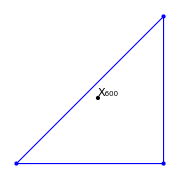

```mathematica
Module[{tri,sides,x},
tri={{0,0},{1,0},{1,1}};
sides=triLengthsRL@tri;
x=getX600Trilin[tri,sides];
Print@x;
Graphics[{FaceForm@None,PointSize@Medium,drawPoly[tri,Blue],Point@x,Text["X_600",x,{-1,-1}]},ImageSize->Small]]
```

```mathematica
(* X(1145) bc(b+c-2a)[2abc-(b+c)(a2-(b-c)2)] *)
getX1145Trilin[orbit_,{a_,b_,c_}]:=Module[{abc=a b c},
trilinearToCartesian[orbit,{a,b,c},
{b c(b+c-2a)(2abc-(b+c)(a^2-(b-c)^2)),
c a(c+a-2b)(2abc-(c+a)(b^2-(c-a)^2)),
a b(a+b-2c)(2abc-(a+b)(c^2-(a-b)^2))}
]]
```

```mathematica
(* de Longchamps Point *)
getX20Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
trilinearToCartesian[orbit,{a,b,c},{
cosA-cosB cosC,
cosB-cosC cosA,
cosC-cosA cosB}]];
```

```mathematica
(* 1/(cos B+cos C) *)
getX21Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
trilinearToCartesian[orbit,{a,b,c},1/{cosB+cosC,cosC+cosA,cosA+cosB}]];
```

```mathematica
(*cos3A,cos3B,cos3C*)
Clear@getX49Trilin;getX49Trilin[orbit_,{a_,b_,c_}]:=Module[{coss,cos3s},
coss=lawOfCosines3[a,b,c];
cos3s=cosTripleAngle/@coss;
trilinearToCartesian[orbit,{a,b,c},cos3s]];
```

```mathematica
Clear@getX59Trilin;getX59Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,cosBC,cosCA,cosAB},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
cosBC=cosB*cosC+sinB*sinC;
cosCA=cosC*cosA+sinC*sinA;
cosAB=cosA*cosB+sinA*sinB;
trilinearToCartesian[orbit,{a,b,c},{
1/(1-cosBC),
1/(1-cosCA),
1/(1-cosAB)}]];
```

```mathematica
Clear@getX144Trilin;getX144Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,tanAov2,tanBov2,tanCov2},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
tanAov2=tanHalfAngle[sinA,cosA];
tanBov2=tanHalfAngle[sinB,cosB];tanCov2=tanHalfAngle[sinC,cosC];
(* (csc A)(tan B/2+tan C/2-tan A/2) *)
trilinearToCartesian[orbit,{a,b,c},{
(tanBov2+tanCov2-tanAov2)/sinA,
(tanCov2+tanAov2-tanBov2)/sinB,
(tanAov2+tanBov2-tanCov2)/sinC}]];

(* intersection of feuerbach hyp w/ billiard *)
Clear@getX1156Trilin;
getX1156Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{
(b-c)^2 + a(b+c-2a),
(c-a)^2 + b(c+a-2b),
(a-b)^2 + c(a+b-2c)
}];
```

```mathematica
Clear@getX1155Trilin;
getX1155Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{
(b-c)^2 + a(b+c-2a),
(c-a)^2 + b(c+a-2b),
(a-b)^2 + c(a+b-2c)
}];
```

```mathematica
(* a(b^2 Cos[2B]+ c^2 Cos[2C] - a^2 Cos[2A]) *)
getX26Trilin[orbit_,{a_,b_,c_}]:=
Module[{cosA,cosB,cosC,cos2A,cos2B,cos2C,a2=a*a,b2=b*b,c2=c*c},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
cos2A=2 cosA^2-1;
cos2B=2 cosB^2-1;
cos2C=2 cosC^2-1;
trilinearToCartesian[orbit,{a,b,c},
{a(b2 cos2B+ c2 cos2C - a2 cos2A),
b(c2 cos2C+ a2 cos2A - b2 cos2B),
c(a2 cos2A+ b2 cos2B - c2 cos2C)}
]];
```

```mathematica
getX359[orbit_,{a_,b_,c_}]:=
Module[{cosA,cosB,cosC,A,B,C},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
A=ArcCos[cosA];
B=ArcCos[cosB];
C=ArcCos[cosC];
trilinearToCartesian[orbit,{a,b,c},
{a/A,b/B,c/C}
]];
```

```mathematica
getX360[orbit_,{a_,b_,c_}]:=
Module[{cosA,cosB,cosC,A,B,C},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
A=ArcCos[cosA];
B=ArcCos[cosB];
C=ArcCos[cosC];
trilinearToCartesian[orbit,{a,b,c},
{A/a,B/b,C/c}
]];
```

```mathematica
getX364[orbit_,{a_,b_,c_}]:=Module[{ah=Sqrt@a,bh=Sqrt@b,ch=Sqrt@c},
trilinearToCartesian[orbit,{a,b,c},
{bh+ch-ah,ch+ah-bh,ah+bh-ch}
]];
```

```mathematica
getX365[orbit_,{a_,b_,c_}]:=
trilinearToCartesian[orbit,{a,b,c},
{Sqrt@a,Sqrt@b,Sqrt@c}
];
```

```mathematica
getX366[orbit_,{a_,b_,c_}]:=
trilinearToCartesian[orbit,{a,b,c},
1/{Sqrt@a,Sqrt@b,Sqrt@c}
];
```

```mathematica
getX367[orbit_,{a_,b_,c_}]:=Module[{ah=Sqrt@a,bh=Sqrt@b,ch=Sqrt@c},
trilinearToCartesian[orbit,{a,b,c},
1/{bh+ch,ch+ah,ah+bh}
]];
```

```mathematica
Module[{ons},
ons=orbitNormals[1.5,toRad@10.];
getX360[ons[[1]],ons[[3]]]]
```

{-0.266377,-0.414822}

```mathematica
(* incenter of excentral triangle *)
getX164Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinAov2,sinBov2,sinCov2},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinAov2,sinBov2,sinCov2}=sinHalfAngle/@{cosA,cosB,cosC};
trilinearToCartesian[orbit,{a,b,c},{
sinBov2+sinCov2-sinAov2,
sinCov2+sinAov2-sinBov2,
sinAov2+sinBov2-sinCov2
}]];
```

```mathematica
(* barycenter of excentral triangle *)
getX165Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
trilinearToCartesian[orbit,{a,b,c},{
3a2-2a(b+c)-(b-c)^2,
3b2-2b(c+a)-(c-a)^2,
3c2-2c(a+b)-(a-b)^2
}]];
```

```mathematica
(* mittenpunkt of excentral triangle *)
getX168Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinAov2,sinBov2,sinCov2},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinAov2,sinBov2,sinCov2}=sinHalfAngle/@{cosA,cosB,cosC};
trilinearToCartesian[orbit,{a,b,c},{
b/(1-sinBov2)+c/(1-sinCov2)-a/(1-sinAov2),
c/(1-sinCov2)+a/(1-sinAov2)-b/(1-sinBov2),
a/(1-sinAov2)+b/(1-sinBov2)-c/(1-sinCov2)}]];
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,1.1];
getOrthocenterTrilin[o,s]]
```

{0.696532,1.04352}

```mathematica
Module[{o,n,s,cirs,incs},
{o,n,s}=orbitNormals[1.5,1.1];
cirs={getCircumcenterTrilin[o,s],getCircumcenter@@o};
incs={getIncenterTrilin[o,s],getIncenter[o[[1]],n[[1]],o[[2]],n[[2]]]};
{cirs,incs}//MatrixForm]
```

({-0.0701496,-0.336575} | getCircumcenter[{0.680394,0.891207},{1.3669,-0.41182},{-1.49106,-0.109019}]
{0.449317,0.210191} | getIncenter[{0.680394,0.891207},{-0.321319,-0.946971},{1.3669,-0.41182},{-0.827741,0.561111}])

#### Generate Billiard as Locus

```mathematica
(* isog conj of X9 *)
getX57Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b+c-a,c+a-b,a+b-c}];
```

```mathematica
getX100Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b-c,c-a,a-b}];
getX513Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b-c,c-a,a-b}];
getX649Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{a(b-c),b(c-a),c(a-b)}];
getX101Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{safeDiv[a,b-c],safeDiv[b,c-a],safeDiv[c,a-b]}];
(* vtx of Yff parabola *)
getX3234Trilin[orbit_,{a_,b_,c_}]:=Module[{a2,b2,c2,a3,b3,c3,trils},
a2=a*a;b2=b*b;c2=c*c;
a3=a2*a;b3=b2*b;c3=c2*c;
trils={
((a-b) (a-c) (2a3-a2 b-b3-a2 c+b2 c+b c2-c3)^2)/a,
((b-c) (b-a) (2b3-b2 c-c3-b2 a+c2 a+c a2-a3)^2)/b,
((c-a) (c-b) (2c3-c2 a-a3-c2 b+a2 b+a b2-b3)^2)/c};
trilinearToCartesian[orbit,{a,b,c},trils]
];


getX88Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b+c-2a,c+a-2b,a+b-2c}];
getX162Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},Module[{a2=a*a,b2=b*b,c2=c*c},
1/{(b2-c2)(b2+c2-a2),(c2-a2)(c2+a2-b2),(a2-b2)(a2+b2-c2)}]];
(* isogonal conjugate of X88, therefore all are inverted *)
getX36Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
trilinearToCartesian[orbit,{a,b,c},{
a(b2+c2-a2-b c),
b(c2+a2-b2-c a),
c(a2+b2-c2-a b)}]
];
getX44Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-2a,c+a-2b,a+b-2c}];
getX693Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{(b-c)/a^2,(c-a)/b^2,(a-b)/c^2}];
```

```mathematica
(* X(230) bc[a2(2a2-b2-c2)+(b2-c2)2] *)
getX230Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
trilinearToCartesian[orbit,{a,b,c},{
b c(a2(2a2-b2-c2)+(b2-c2)^2),
c a(b2(2b2-c2-a2)+(c2-a2)^2),
a b(c2(2c2-a2-b2)+(a2-b2)^2)
}]];
```

```mathematica
(* YFF PARABOLIC POINT *)
getX190Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c/(b-c),c a/(c-a),a b/(a-b)}];
(* X650 is both on the anti-orthic axis and on L55 Gergonne of ACT, i.e., L(31) of billiard, meaning *both* its isotomic and isogonal conjugates lie on the EB, i.e., the E9-centered circumellipse *)
(* X(650)=isogonal conjugate of X(651)
X(650)=isotomic conjugate of X(4554)
*) 
getX650Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{(b-c)(b+c-a),
(c-a)(c+a-b),
(a-b)(a+b-c)}];
(*bc/[a(b-c)(b+c-a)] = 1/[a^2(b-c)(b+c-a)] *)
getX4554Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
1/{a^2(b-c)(b+c-a),b^2(c-a)(c+a-b),c^2(a-b)(a+b-c)}];
getX652Trilin[orbit_,{a_,b_,c_}]:=Module[{secA,secB,secC},
{secA,secB,secC}=1/lawOfCosines3[a,b,c];trilinearToCartesian[orbit,{a,b,c},{secB-secC,secC-secA,secA-secB}]];
getX655Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,cosAmB,cosBmC,cosCmA},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=Sqrt[1-#^2]&/@{cosA,cosB,cosC};
(* f(A,B,C):f(B,C,A):f(C,A,B),where f(A,B,C)=1/[cos(A-B)-cos(C-A)] *)
cosAmB=cosA cosB+sinA sinB;
cosBmC=cosB cosC+sinB sinC;
cosCmA=cosC cosA+sinC sinA;
trilinearToCartesian[orbit,{a,b,c},
1/{cosAmB-cosCmA,cosBmC-cosAmB,cosCmA-cosBmC}]
];
getX656Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{(b2-c2)(b2+c2-a2),(c2-a2)(c2+a2-b2),(a2-b2)(a2+b2-c2)}]];
getX798Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{a2(b2-c2),b2(c2-a2),c2(a2-b2)}]];
getX823Trilin[orbit_,{a_,b_,c_}]:=Module[{secA2,secB2,secC2},
{secA2,secB2,secC2}=1/{lawOfCosines[a,b,c]^2,lawOfCosines[b,a,c]^2,lawOfCosines[c,a,b]^2};
trilinearToCartesian[orbit,{a,b,c},1/{
secB2-secC2,
secC2-secA2,
secA2-secB2}]];
(* TRILINEAR POLE OF LINE X(1)X(3) *)
getX651Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{(b-c)(b+c-a),(c-a)(c+a-b),(a-b)(a+b-c)}];
```

```mathematica
(* sec(A-π/6)=1/[cosA cosPi6+ sinA sinPi6] *)
getX13Trilin[orbit_,{a_,b_,c_}]:=Module[{coss,cosPi6=Cos[π/6],sinPi6=Sin[π/6],sins,cosABCmPi6},
coss=lawOfCosines3[a,b,c];
cosABCmPi6=cosDiffAngle[#,Sqrt[1-#^2],cosPi6,sinPi6]&/@coss;
trilinearToCartesian[orbit,{a,b,c},1/cosABCmPi6]];
```

```mathematica
(* (b-c)/a *) getX514Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{(b-c)/a,(c-a)/b,(a-b)/c}
];
```

```mathematica
(* Peter Moses: Perspector of the Inner Conway Triangle, vertices on the EB *)
(* (a^2+(b-c)^2)(a^3-(b+c)*a^2+(b+c)^2*a-(b+c)(b^2+c^2)): *)
fnX11677[a_,b_,c_]:=Module[{a2=a a,b2=b b,c2=c c},(a2 + (b - c)^2) (a a2 - (b + c)a2 + a(b + c)^2 - (b + c) (b2 + c2))/a] ;
getX11677[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{fnX11677[a,b,c],fnX11677[b,c,a],fnX11677[c,a,b]}]];
```

#### Novo resultado : X661 é o unico ponto no plano q esta simultaneamente no eixo antiortico e no [L(55) do anticomplementar] L(31) do de referencia. É o unico ponto no plano tal que seus conjugados isogonal e o isotomico caem (em pontos diferentes: 662 e 799) no bilhar.

```mathematica
(* b^2-c^2 *) 
getX661Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{b2-c2,c2-a2,a2-b2}]];
(* X(661)=isogonal conjugate of X(662)
X(661)=isotomic conjugate of X(799) *)
(* x662 is isog conj of x661 *)
getX662Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},1/{b2-c2,c2-a2,a2-b2}]];
(* x799 is isot conj of x661 *)
getX663Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{a(b-c)(b+c-a),b(c-a)(c+a-b),c(a-b)(a+b-c)}]];
getX664Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},1/{a(b-c)(b+c-a),b(c-a)(c+a-b),c(a-b)(a+b-c)}]];
getX664TestTrilin[orbit_,{a_,b_,c_}]:=
trilinearToCartesian[orbit,{a,b,c},
{(a-b) (a-c) (a+b-c) (a+c-b)/a,
(b-c) (b-a) (b+c-a) (b+a-c)/b,
(c-a) (c-b) (c+a-b) (c+b-a)/c}];
getX799Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},1/{a2(b2-c2),b2(c2-a2),c2(a2-b2)}]];
```

```mathematica
(* X(908)= POINT ACUBENS = (cosB+cosC-1)/a *)
getX908Trilin[orbit_,{a_,b_,c_}]:=Module[{cA,cB,cC},
{cA,cB,cC}=lawOfCosines3[a,b,c];
trilinearToCartesian[orbit,{a,b,c},
{(cB+cC-1)/a,
(cC+cA-1)/b,
(cA+cB-1)/c}
]];
```

```mathematica
(* X(857)= INTERCEPT OF EULER LINE AND TRILINEAR POLAR OF X(75)
X(857)= sinC^2 sin2B sin(C-A) + sinB^2 sin2C sin(B-A) *)
getX857Trilin[orbit_,{a_,b_,c_}]:=Module[{cA,cB,cC,sA2,sB2,sC2,sA,sB,sC,sAmC,sAmB,sBmC,s2A,s2B,s2C},
{cA,cB,cC}=lawOfCosines3[a,b,c];
{sA2,sB2,sC2}=(1-#^2)&/@{cA,cB,cC};
{sA,sB,sC}=Sqrt/@{sA2,sB2,sC2};
{s2A,s2B,s2C}=MapThread[sinDoubleAngle,{{sA,sB,sC},{cA,cB,cC}}];
sAmB=sA cB-cA sB;
sAmC=sA cC-cA sC;
sBmC=sB cC-cB sC;
trilinearToCartesian[orbit,{a,b,c},{
-sC2 s2B sAmC-sB2 s2C sAmB,
sA2 s2C sAmB-sC2 s2A sBmC,
sB2 s2A sBmC+sA2 s2B sAmC}]];
```

```mathematica
(* X(2590)=X(2)-ISOCONJUGATE OF X(1381) *)
(* a/f(a,b,c):b/f(b,c,a):c/f(c,a,b),where f(a,b,c) is as at X(1381) *)
(* X(1381)=1st INTERCEPT OF LINE X(1)X(3) AND CIRCUMCIRCLE
Trilinears f(a,b,c):f(b,c,a):f(c,a,b),where f(a,b,c)=r+(|OI|-R) cos A *)
getX2590Trilin[orbit_,{a_,b_,c_}]:=Module[{cA,cB,cC,r,x3,x1,R,k},
{cA,cB,cC}=lawOfCosines3[a,b,c];
x1=getIncenterTrilin[orbit,{a,b,c}];
x3=getCircumcenterTrilin[orbit,{a,b,c}];
r=getInradius[{a,b,c}];
R=getCircumradius[{a,b,c}];
k=magn[x1-x3]-R;
trilinearToCartesian[orbit,{a,b,c},{
a/(r+k cA),b/(r+k cB),c/(r+k cC)
}]
];
```

```mathematica
getX2590Trilin@@Part[orbitNormals[1.2,toRad@0.],{1,3}]
```

{-6.21306,9.50995×10^-15}

```mathematica
getX101Trilin@@Part[orbitNormals[2,toRad@40.],{1,3}]
```

{-1.41096,1.00183}

```mathematica
getX4554Trilin@@Part[orbitNormals[2,toRad@40.],{1,3}]
```

{-1.70288,0.167823}

```mathematica
Chop[getMittenTrilin@@Part[orbitNormals[2,toRad@10.],{1,3}]]
```

{0,0}

#### Barycentrics (does not appear to work!)

-Graphics-

```mathematica
barycentricToCartesian[orbit_,lambdas0_]:=Module[{x,y,area,lambdas},
(*area=Area[Polygon@orbit];*)
lambdas=lambdas0/Total@lambdas0;
x=Total@MapThread[(#1*#2)&,{First/@orbit,lambdas}];
y=Total@MapThread[(#1*#2)&,{Second/@orbit,lambdas}];
{x,y}];
```

```mathematica
Clear@X10405;X10405[orbit_,{a_,b_,c_}]:=barycentricToCartesian[orbit,
1/{3a^2-2a b-2a c-(b-c)^2,
3b^2-2b c-2b a-(c-a)^2,
3c^2-2c a-2c b-(a-b)^2}];
```

```mathematica
(* perpector of anticomplementary on extouch: http://mathworld.wolfram.com/Perspector.html  *)
```

```mathematica
X144b[orbit_,{a_,b_,c_}]:=barycentricToCartesian[orbit,
{1/(a-b-c)+1/(a-b+c)+1/(a+b-c),
1/(b-c-a)+1/(b-c+a)+1/(b+c-a),
1/(c-a-b)+1/(c-a+b)+1/(c+a-b)}];
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,.1];
{getX144Trilin[o,s],X144b[o,s]}
]
```

{{0.59009,0.346298},{0.59009,0.346298}}

```mathematica
equiError[tri_]:=Module[{s,bar,inc,savg},
s=triLengthsRL@tri;
savg=Total@s/Length@s;
bar=getBarycenterTrilin[tri,s];
inc=getIncenterTrilin[tri,s];
magn2[bar-inc]/savg]
```

```mathematica
isEqui[tri_]:=equiError[tri]<10^-6;
```

```mathematica
drawPoly[poly_,clr_]:={EdgeForm@{clr,Thick},Polygon@poly,clr,Point@poly};
drawPolyThick[poly_,clr_]:={EdgeForm@{clr,AbsoluteThickness@3},Polygon@poly,clr,Point@poly};
```

## Triangles form Trilinear Matrices

```mathematica
trilinearMatrixToCartesian[orbit_,sides_,tryM_]:=trilinearToCartesian[orbit,sides,#]&/@tryM;
trilinearMatrixToCartesianUnsafe[orbit_,sides_,tryM_]:=trilinearToCartesianUnsafe[orbit,sides,#]&/@tryM;
```

to do : anticomplementary, external tangents triangle.

```mathematica
intouchTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,(a c)/(a-b+c),(a b)/(a+b-c)},
{(b c)/(-a+b+c),0,(a b)/(a+b-c)},
{(b c)/(-a+b+c),(a c)/(a-b+c),0}}];
```

```mathematica
intouchTriangleUnsafe[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesianUnsafe[orbit,{a,b,c},
{{0,(a c)/(a-b+c),(a b)/(a+b-c)},
{(b c)/(-a+b+c),0,(a b)/(a+b-c)},
{(b c)/(-a+b+c),(a c)/(a-b+c),0}}];
```

```mathematica
extouchTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,(a-b+c)/b,(a+b-c)/c},
{(-a+b+c)/a,0,(a+b-c)/c},
{(-a+b+c)/a,(a-b+c)/b,0}}];
```

```mathematica
Clear@incentralTriangle;
incentralTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,1,1},
{1,0,1},
{1,1,0}}];
```

```mathematica
Clear@excentralTriangle;
excentralTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,1,1},
{1,-1,1},
{1,1,-1}}];
```

```mathematica
Clear@medialTriangle;
medialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,a c,a b},{b c,0,a b},{b c,a c,0}}];
```

```mathematica
Clear@yffTriangle;
yffTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,safeDiv[a c,c-a],safeDiv[a b,a-b]},(* error in mathworld http://mathworld.wolfram.com/YffContactTriangle.html which shows this as {0,ac/(c-a),ab/(b-a)}*)
{safeDiv[b c,b-c],0,safeDiv[a b,a-b]},
{safeDiv[b c,b-c],safeDiv[a c,c-a],0}}];
```

```mathematica
Module[{tri={{0,0},{1,0},{1,1}}},
medialTriangle[tri,triLengthsRL@tri]]
```

{{1,1/2},{1/2,1/2},{1/2,0}}

```mathematica
Clear@orthicTriangle;
orthicTriangle[orbit_,sides_]:=Module[{secA,secB,secC},
{secA,secB,secC}=1./getTriCosines[orbit];trilinearMatrixToCartesian[orbit,sides,{{0,secB,secC},{secA,0,secC},{secA,secB,0}}]];
```

```mathematica
Clear@eulerTriangle;
eulerTriangle[orbit_,{a_,b_,c_}]:=Module[{cA,cB,cC,sA,sB,sC,tA,tB,tC},
{cA,cB,cC}={
lawOfCosines[a,b,c],
lawOfCosines[b,a,c],
lawOfCosines[c,a,b]};
{sA,sB,sC}=getSin/@{cA,cB,cC};
{tA,tB,tC}={sA/cA,sB/cB,sC/cC};
trilinearMatrixToCartesian[orbit,{a,b,c},
{{2 tA+tB+tC,sA/cB,sA/cC},
{sB/cA,tA+2tB+tC,sB/cC},
{sC/cA,sC/cB,tA+tB+2tC}}]];
```

```mathematica
(* https://faculty.evansville.edu/ck6/encyclopedia/gemini.html *)
(* (a^2+b*c)/a:(-a*b-c*a)/b:(-a*b-c*a)/c *)
(* remember to rotate rows *)
gemini90Triangle[orbit_,{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
trilinearMatrixToCartesian[orbit,{a,b,c},
{{(a2+b c)/a , (-a b-c a)/b , (-a b-c a)/c},
{ (-b c-a b)/a,(b2+c a)/b , (-b c-a b)/c },
{ (-c a-b c)/a,(-c a-b c)/b,(c2+a b)/c }}]];
```

```mathematica
gemini2Triangle[orbit_,{a_,b_,c_}]:=
trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,(b+c)/b,(b+c)/c},
{(c+a)/a,-1,(c+a)/c},
{(a+b)/a,(a+b)/b,-1}}];
```

```mathematica
gemini30Triangle[orbit_,{a_,b_,c_}]:=
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,(c-b)/b,(b-c)/c},
{(c-a)/a,1,(a-c)/c},
{(b-a)/a,(a-b)/b,1}}];
```

```mathematica
honsbergerVtxA[a_,b_,c_]:={(a-b+c)(a+b-c),(a+b-c)((b-c)^2-a(b+c))/b,(a-b+c)((b-c)^2-a(b+c))/c};
```

```mathematica
honsbergerTriangle[orbit_,{a_,b_,c_}]:=
trilinearMatrixToCartesian[orbit,{a,b,c},
{honsbergerVtxA[a,b,c],RotateRight[honsbergerVtxA[b,c,a],1],RotateRight[honsbergerVtxA[c,a,b],2]}];
```

```mathematica
(* intouch of ACT on the EB *)
innerConwayTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{b c,(c-b)c,(b-c)b},
{(c-a)c,c a,(a-c)a},
{(b-a)b,(a-b)a,a b}}];
```

```mathematica
(* http://mathworld.wolfram.com/TangentialTriangle.html *)
tangentialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{-a,b,c},{a,-b,c},{a,b,-c}}];
anticomplementaryTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{1/{-a,b,c},1/{a,-b,c},1/{a,b,-c}}];
externaltangentsTriangle[orbit_,sides_]:=Module[{x,y,z},
{x,y,z}=getTriCosines[orbit];
trilinearMatrixToCartesian[orbit,sides,
{{-(x+1),x+z,x+y},
{y+z,-(y+1),y+x},
{z+y,z+x,-(z+1)}
}]];
```

```mathematica
hexylTriangle[orbit_,{a_,b_,c_}]:=Module[{x,y,z,diag},
{x,y,z}=lawOfCosines3[a,b,c];
diag=x+y+z+1;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{diag,x+y-z-1,x-y+z-1},
{x+y-z-1,diag,-x+y+z-1},
{x-y+z-1,-x+y+z-1,diag}}]];
```

```mathematica
outerNapoleonTriangle[orbit_,{a_,b_,c_}]:=Module[{
cosA,cosB,cosC,sinA,sinB,sinC,
cPi6,sPi6,
sApPi6,sBpPi6,sCpPi6,sAmPi6,sBmPi6,sCmPi6},
cPi6=Cos[π/6.];
sPi6=Sin[π/6.];
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{sApPi6,sAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sBpPi6,sBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sCpPi6,sCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,2sCpPi6,2sBpPi6},
{2sCpPi6,-1,2sApPi6},
{2sBpPi6,2sApPi6,-1}}]];
```

```mathematica
firstMorleyTriangle[orbit_,{a_,b_,c_}]:=Module[{cs,cs3},
cs=lawOfCosines3[a,b,c];
cs3=cosThird/@cs;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,2cs3[[3]],2cs3[[2]]},
{2cs3[[3]],1,2cs3[[1]]},
{2cs3[[2]],2cs3[[1]],1}}]];
```

-Graphics-

```mathematica
secondMorleyTriangle[orbit_,{a_,b_,c_}]:=Module[{cs,cs3,ss3,s2p3,c2p3,a12,a13,a23},
cs=lawOfCosines3[a,b,c];
cs3=cosThird/@cs;
ss3=Sqrt[1-#^2]&/@cs3;
c2p3=-1/2;(*Cos[2π/3.];*)
s2p3=Sqrt[3]/2;(*Sin[2π/3.];*)
a12=cs3[[3]] c2p3+ss3[[3]] s2p3;
a13=cs3[[2]] c2p3+ss3[[2]] s2p3;
a23=cs3[[1]] c2p3+ss3[[1]] s2p3;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,2a12,2a13},
{2a12,1,2a23},
{2a13,2a23,1}}]];
```

-Graphics-

```mathematica
Sin[4π/3]
```

-(√3)/2

```mathematica
thirdMorleyTriangle[orbit_,{a_,b_,c_}]:=Module[{cs,cs3,ss3,s4p3,c4p3,a12,a13,a23},
cs=lawOfCosines3[a,b,c];
cs3=cosThird/@cs;
ss3=Sqrt[1-#^2]&/@cs3;
c4p3=-1/2;(*Cos[4π/3.];*)
s4p3=-Sqrt[3]/2;(*Sin[4π/3.];*)
a12=cs3[[3]] c4p3+ss3[[3]] s4p3;
a13=cs3[[2]] c4p3+ss3[[2]] s4p3;
a23=cs3[[1]] c4p3+ss3[[1]] s4p3;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,2a12,2a13},
{2a12,1,2a23},
{2a13,2a23,1}}]];
```

```mathematica
cevianTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{0,t2,t3},{t1,0,t3},{t1,t2,0}}];antiCevianTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{-t1,t2,t3},{t1,-t2,t3},{t1,t2,-t3}}];
```

```mathematica
pedalTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=Module[{cA,cB,cC},
{cA,cB,cC}=lawOfCosines3[a,b,c];
trilinearMatrixToCartesian[orbit,{a,b,c},{
{0,t2+t1 cC,t3+t1 cB},
{t1+t2 cC,0,t3+t2 cA},
{t1+t3 cB,t2+t3 cA,0}
}]];
```

-Graphics-

```mathematica
antipedalTriangle[orbit_,{a_,b_,c_},{α_,β_,γ_}]:=Module[{cA,cB,cC},
{cA,cB,cC}=lawOfCosines3[a,b,c];
trilinearMatrixToCartesian[orbit,{a,b,c},{
{-(β+α cC)(γ+α cB),(γ+α cB)(α+β cC),(β+α cC)(α+γ cB)},
{(γ+β cA)(β+α cC),-(γ+β cA)(α+β cC),(α+β cC)(β+γ cA)},
{(β+γ cA)(γ+α cB),(α+γ cB)(γ+β cA),-(α+γ cB)(β+γ cA)}
}]];
```

```mathematica
trilinearCoords[tri_,p_]:=
RotateLeft@MapThread[magn[closestPerp[p,#1,#2]-p]&,
(* needs this crossed rotation so trilinears come out in the usual way *)
{tri,RotateLeft@tri}]
```

```mathematica
Module[{o,n,s,p,tril},
{o,n,s}=orbitNormals[1.5,toRad@35.];
p=getSymmedianTrilin[o,s];
tril=trilinearCoords[o,p];
tril
(*Print@(s/s[[1]]);
tril/tril[[1]]*)]
```

{0.551909,0.580316,0.273465}

```mathematica
symmedialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{0,b,c},{a,0,c},{a,b,0}}];
```

```mathematica
Clear@feuerbachTriangle;
feuerbachTriangle[orbit_,{a_,b_,c_}]:=Module[{
sinA,sinB,sinC,
cosA,cosB,cosC,
cosBmC,cosCmA,cosAmB,
c2haAmB,c2haBmC,c2haCmA,
m},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
cosBmC=cosDiffAngle[sinB,cosB,sinC,cosC];
cosCmA=cosDiffAngle[sinC,cosC,sinA,cosA];
cosAmB=cosDiffAngle[sinA,cosA,sinB,cosB];
c2haAmB=cos2HalfAngle[cosAmB];
c2haBmC=cos2HalfAngle[cosBmC];
c2haCmA=cos2HalfAngle[cosCmA];
m={
{-sin2HalfAngle[cosBmC],c2haCmA,c2haAmB},
{c2haBmC,-sin2HalfAngle[cosCmA],c2haAmB},
{c2haBmC,c2haCmA,-sin2HalfAngle[cosAmB]}
};trilinearMatrixToCartesian[orbit,{a,b,c},m]];
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,.1];
feuerbachTriangle[o,s]]
```

{{-1.04832,-0.369712},{-0.112968,0.352287},{0.256211,-0.740368}}

#### The first point in the extouch triangle flows on caustic at the exact same parametric than P1

```mathematica
Manipulate[Module[{o,ett,ell,a=1.5,gr,ca,cb},
o=orbitNormals[a,t][[1]];
{ca,cb}=getTriCausticParams[a];
ett=extouchTriangle[o,triLengthsRL@o];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@{Blue,Thick},Polygon@o,Red,Point@First@o,Blue,Circle[First@o,.05]},
{EdgeForm@Darker@Green,Polygon@ett},
{Darker@Green,Circle[ett[[1]],.05]},
{Red,Point[{-ca Cos[t],-cb Sin[t]}]}}];
Show[{plotEll[a],plotEllb[ca,cb,Brown],gr},AspectRatio->Automatic,Frame->True]],{t,0,2π,π/360.}]
```

#### Anticomplementary triangle seems like the more stable, more useful to produce higher order points.

```mathematica
DynamicModule[{cc,vs,sides,cir,cirRad,tt,ac,et,ortTril,ortCev,clrs,ort,ortAntiCev,hexyl},
Manipulate[
vs={{-1,0},{1,0},p1}; (*N@{{0,0},{1,-.6},{.7,.5}};*)
sides=triLengthsRL@vs;
cir=getCircumcenterTrilin[vs,sides];
cirRad=magn[vs[[1]]-cir];
tt=tangentialTriangle[vs,sides];
ac=anticomplementaryTriangle[vs,sides];
et=externaltangentsTriangle[vs,sides];
hexyl=hexylTriangle[vs,sides];
ortTril=1/getTriCosines[vs];
ort=trilinearToCartesian[vs,sides,ortTril];
ortCev=cevianTriangle[vs,sides,ortTril];
ortAntiCev=antiCevianTriangle[vs,sides,ortTril];
clrs={Black,Red,Green,Blue,Purple,Cyan,Pink};
Legended[Graphics[{PointSize@Medium,Black,FaceForm@None,
MapThread[{EdgeForm@#1,#1,Polygon@#2,Point@#2}&,{clrs,{vs,tt,ac,et,ortCev,ortAntiCev,hexyl}}],
{Circle[cir,cirRad],Point@cir},
{Orange,Point@ort}},ImageSize->Medium,Frame->True,PlotRange->{{-5,5},{-5,5}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"reference","tangential","anticomplementary","external tangents","ortho cevian = orthic","ortho anticevian","hexyl"}]],
{{p1,{0,2}},Locator},SaveDefinitions->True]]
```

```mathematica
DynamicModule[{cc,vs,normals,sides,ell,cir,cirRad,tt,ac,et,ortTril,ortCev,clrs,ort,ortAntiCev,hexyl,gr,xmax=3,ymax=3},Manipulate[
ell=plotEll[a];
{vs,normals,sides}=orbitNormals[a,toRad@tDeg];
sides=triLengthsRL@vs;
cir=getCircumcenterTrilin[vs,sides];
cirRad=magn[vs[[1]]-cir];
tt=tangentialTriangle[vs,sides];
ac=anticomplementaryTriangle[vs,sides];
et=externaltangentsTriangle[vs,sides];
hexyl=hexylTriangle[vs,sides];
ortTril=1/getTriCosines[vs];
ort=trilinearToCartesian[vs,sides,ortTril];
ortCev=cevianTriangle[vs,sides,ortTril];
ortAntiCev=antiCevianTriangle[vs,sides,ortTril];
clrs={Black,Red,Green,Blue,Purple,Cyan,Pink};
gr=Legended[Graphics[{PointSize@Medium,Black,FaceForm@None,
MapThread[{EdgeForm@#1,#1,Polygon@#2,Point@#2}&,{clrs,{vs,tt,ac,et,ortCev,ortAntiCev,hexyl}}],
{Circle[cir,cirRad],Point@cir},
{Orange,Point@ort}},ImageSize->Medium,Frame->True,PlotRange->{{-5,5},{-5,5}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"reference","tangential","anticomplementary","external tangents","ortho cevian = orthic","ortho anticevian","hexyl"}]];
Show[{ell,gr},PlotRange->{{-xmax,xmax},{-ymax,ymax}}],
{{a,1.5},1.01,3,.05},
{{tDeg,0},-360,360,.1},SaveDefinitions->True]]
```

## Major Triangular Centers (Notables)

#### Linha de Euler: bari, ortho, circum, 9-pc all lie on a line (but not incenter)

-Graphics-

```mathematica
getAltBases[p1_,p2_,p3_]:=Module[{sides},
sides={{p2,p3},{p3,p1},{p1,p2}};
MapThread[closestPerp[#1,#2[[1]],#2[[2]]]&,{{p1,p2,p3},sides}]];
```

```mathematica
getIncenter[p1_,n1_,p2_,n2_]:=interRays[p1,n1,p2,n2];
Clear@getBaricenter;getBaricenter[p1_,p2_,p3_]:=Module[{medians},(*(p1+p2+p3)/3;*)
medians=getMedians[p1,p2,p3];
interRays[p1,medians[[1]](*23*)-p1,p2,medians[[2]](*31*)-p2]
];
getOrthocenter[p1_,p2_,p3_]:=Module[{altBases},
altBases=getAltBases[p1,p2,p3];
interRays[p1,altBases[[1]]-p1,p2,altBases[[2]]-p2]
];
getCircumcenter[p1_,p2_,p3_]:=Module[{medians,medianPerps},
medians=getMedians[p1,p2,p3];
medianPerps={
medians[[1]]+norm[perp[p2-p3]],
medians[[2]]+norm[perp[p3-p1]],
medians[[3]]+norm[perp[p1-p2]]
};
interRays[medians[[1]](*2+3*),perp[p2-p3],medians[[2]](*3+1*),perp[p1-p3]]
];
```

#### Nine Point Circle: its center is the circumcenter of the medians, and is tangent to incircle (at Feuerbach point) and all 3 excircles

-Graphics--Graphics-

```mathematica
getNinepointcenter[p1_,p2_,p3_]:=Module[{medians},
medians=getMedians[p1,p2,p3];
getCircumcenter@@medians
];
```

```mathematica
Clear@inRadius0;
inRadius0[incenter_,p1_,p2_]:=Module[{ctr,foot},
foot=closestPerp[incenter,p1,p2];
magn[incenter-foot]];
```

```mathematica
circumRadius0[circumcenter_,p1_]:=magn[circumcenter-p1];
```

```mathematica
(* shoot ray from incenter *)
getFeuerbachpoint[npc_,incenter_,inradius_]:=Module[{inter},
ray[incenter,norm[incenter-npc],inradius]
];
```

```mathematica
getExcenters[orbit_,normals_]:=Module[{perps,perpsNeg,exc},
perps=perp/@normals;
perpsNeg=perpNeg/@normals;
exc=MapThread[interRays[#1,#2,#3,#4]&,{orbit,perps,RotateLeft@orbit,RotateLeft@perpsNeg}];
exc];
```

#### Gergonne Point: perspector of ABC and its contact triangle Ta, Tb, Tc

## Get Triangular Center (Notable) Info

```mathematica
Clear@getTouchPts;getTouchPts[orbit_,normals_]:=Module[{inc,tps},
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
tps=MapThread[closestPerp[inc,#1,#2]&,{orbit,RotateLeft@orbit}];
tps];
```

```mathematica
getAntiComplement[p_,bar_]:=bar-2(p-bar);
```

```mathematica
Clear@getNotables;
getNotables[orbit_,normals_]:=Module[{inc,inradius,cir,circumradius,npc,exc,tps,ort,medians,npcradius,sides,bar,feu,antifeu,x88,perimeter},
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
inradius=inRadius0[inc,orbit[[1]],orbit[[2]]];
tps=MapThread[closestPerp[inc,#1,#2]&,{orbit,RotateLeft@orbit}];
medians=getMedians@@orbit;
cir=getCircumcenter@@orbit;
circumradius=circumRadius0[cir,orbit[[1]]];
npc=getNinepointcenter@@orbit;
npcradius=magn[npc-medians[[1]]];
exc=getExcenters[orbit,normals];
sides=triLengthsRL@orbit;
feu=getFeuerbachpoint[npc,inc,inradius];
bar=getBaricenter@@orbit;
antifeu=getAntiComplement[feu,bar];(* anticomplement *)
x88=getX88Trilin[orbit,sides];
ort=getOrthocenter@@orbit;
perimeter=Total@sides;
(* we think this is constant for excentral triangle *)
{
"inc"->inc,
"bar"->bar,(* also: getCentroid[orbit,sides] *)
"ort"->ort,
"cir"->cir,
"npc"->npc,
"exc"->exc,
"ex12"->exc[[1]],
"ex23"->exc[[2]],
"ex31"->exc[[3]],
"feu"->feu,
"antifeu"->antifeu,
"x88"->x88,
(* all thru trilinears, each computing sides unnecessarily *)
"mit"->getMittenTrilin[orbit,sides],
"sym"->getSymmedianTrilin[orbit,sides],
"ger"->getGergonneTrilin[orbit,sides],
"nag"->getNagelTrilin[orbit,sides],
"spi"->getSpiekerTrilin[orbit,sides],
(* not really notables, aux info *)
"incRadius"->inradius,
"tps"-> tps,
"medians"->medians,
"cirRadius"->circumradius,
"npcRadius"->npcradius,
"sides"->sides,
"perimeter"->perimeter,
"area"->triAreaHeron@sides
}];
```

#### Orthic and orthic of orthic (similar to reference triangle?)

```mathematica
Clear@getOrthicData;getOrthicData[orbit_]:=Module[{feet,inc,sides,ort,
intouch,intouchSides,inradius,(* intouchInc = inc *)
intouchOrt,intouchOrtSides,intouchOrtInc,
intouchAnticompl,intouchAnticomplSides,
intouchAnticomplOrt,intouchAnticomplOrtSides,intouchAnticomplOrtInc,
orthic,orthicSides,orthicInc,
orthicAnticompl,orthicAnticomplSides,orthicAnticomplInc
},
(* orthic *)
feet=getAltBases@@orbit;
sides=triLengthsRL@feet;
inc=getIncenterTrilin[feet,sides];
ort=getOrthocenterTrilin[feet,sides];
(* intouch *)
intouch=intouchTriangle[feet,sides];
intouchSides=triLengthsRL@intouch;
inradius=magn[intouch[[1]]-inc];
intouchOrt=getAltBases@@intouch;
intouchOrtSides=triLengthsRL@intouchOrt;
intouchOrtInc=getIncenterTrilin[intouchOrt,intouchOrtSides];
(* anticomplement of intouch *)
intouchAnticompl=anticomplementaryTriangle[intouch,intouchSides];
intouchAnticomplSides=triLengthsRL@intouchAnticompl;
intouchAnticomplOrt=getAltBases@@intouchAnticompl;
intouchAnticomplOrtSides=triLengthsRL@intouchAnticomplOrt;
intouchAnticomplOrtInc=getIncenterTrilin[intouchAnticomplOrt,intouchAnticomplOrtSides];
(* orthic *)
orthic=getAltBases@@feet;
orthicSides=triLengthsRL@orthic;
orthicInc=getIncenterTrilin[orthic,orthicSides];
orthicAnticompl=anticomplementaryTriangle[orthic,orthicSides];
orthicAnticomplSides=triLengthsRL@orthicAnticompl;
orthicAnticomplInc=getIncenterTrilin[orthicAnticompl,orthicAnticomplSides];
{
(* orthic *)
"feet"->feet,
"sides"->sides,
"inc"->inc,
"ort"->ort,
(* intouch of orthic, we think similar to orbit *)
"intouch"->intouch,
"intouchSides"->intouchSides,
"inradius"->inradius,
(* orthic of intouch *)
"intouchOrt"->intouchOrt,
"intouchOrtSides"->intouchOrtSides,
"intouchOrtInc"->intouchOrtInc,
(* anticomplement of intouch of orthic, upside down orbit? *)
"intouchAnticompl"->intouchAnticompl,
"intouchAnticomplSides"->intouchAnticomplSides,
(*"intouchAnticomplInc"->intouchAnticomplInc,*)
(* orthic of anticomplement of intouch *)
"intouchAnticomplOrt"->intouchAnticompl,
"intouchAnticomplOrtSides"->intouchAnticomplOrtSides,
"intouchAnticomplOrtInc"->intouchAnticomplOrtInc,
(* orthic of orthic *)
"orthic"->orthic,
"orthicSides"->orthicSides,
"orthicInc"->orthicInc,
(* anticomplement of orthic's orthic *)
"orthicAnticompl"->orthicAnticompl;
"orthicAnticomplSides"->orthicAnticomplSides,
"orthicAnticomplInc"->orthicAnticomplInc
}];
```

#### Excenters and Excircles

```mathematica
Clear@showBisectors;showBisectors[vs_]:=Module[{bs},
bs=getTriBisectors@@vs;
Graphics[{FaceForm[None],EdgeForm[Black],Black,PointSize[Medium],
Polygon[vs],
Point[vs],
MapThread[Text[#1,#2,{1.5,0}]&,{{"P_1","P_2","P_3"},vs}],
MapThread[Arrow[{#1,ray[#1,#2,.25]}]&,{vs,bs}]},
ImageSize->Small]
];
```

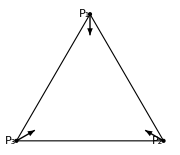

```mathematica
(* show bisectors computed from vertices for equilateral *)
showBisectors[Table[{Sin[a],Cos[a]},{a,0,2π-π/3,2π/3}]]
```

#### Nagel Point

```mathematica
getExtouchPoints[orbit_,exc_]:=MapThread[closestPerp[#1,#2,#3]&,{exc,orbit,RotateLeft[orbit]}];
```

```mathematica
Clear@getExcircleData;
getExcircleData[orbit_,exc_(*12,23,31*),npc_]:=Module[{excFeet,altLengths,tps,radii,feus,nagel,medians,mitten,mittenPedals,
mittenFeet,sides,cosABC,cosSum,cosProd,sideProd,altLengthsProd,feusCir,feusCirR,mittenFeetCir,mittenFeetCirR},
(* side touch points to sides: 12,23,31 *)
tps=getExtouchPoints[orbit,exc];
excFeet=getAltBases@@exc;
altLengths=MapThread[magn[#1-#2]&,{exc,excFeet}];
radii=MapThread[magn[#1-#2]&,{exc,tps}];
feus=MapThread[ray[#1,norm[npc-#1],#2]&,{exc,radii}];
feusCir=getCircumcenter@@feus;
feusCirR=magn[feus[[1]]-feusCir];
medians=getMedians@@orbit;
mitten=interRays[exc[[1]],medians[[3]]-exc[[1]],exc[[2]],medians[[1]]-exc[[2]]];
mittenPedals=MapThread[closestPerp[mitten,#1,#2]&,{orbit,RotateLeft@orbit}];
(* symmedian triangle *)
mittenFeet=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{exc,RotateRight@medians,RotateLeft@exc,RotateRight@exc}];
mittenFeetCir=getCircumcenter@@mittenFeet;
mittenFeetCirR=magn[mittenFeet[[1]]-mittenFeetCir];
sides=triLengthsRL@exc;
cosABC=getTriCosines[exc];
cosSum=Total[cosABC];
cosProd=cosABC[[1]]*cosABC[[2]]*cosABC[[3]];
sideProd=sides[[1]]*sides[[2]]*sides[[3]];
altLengthsProd=altLengths[[1]]*altLengths[[2]]*altLengths[[3]];
{
"sides"->sides,
"perimeter"->Total[sides],
"cosABC"->cosABC,
"excFeet"->excFeet,
"altLengths"->altLengths,
"sumAltLengths"->Total@altLengths,
"prodAltLengths"->altLengthsProd,
"sumInvAltLengths"->Total[(1/#)&/@altLengths],
"cosSum"->cosSum,
"cosProd"->cosProd,
"sideProd"->sideProd,
"tps"->tps,(* extouchpoints*)
"radii"->radii,
"sumRadiiSqr"->Total[#^2&/@radii],
"sumInvRadiiSqr"->Total[(1/#^2)&/@radii],
"sumRadii"->Total@radii,
"sumInvRadii"->Total[(1/#)&/@radii],
"feus"->feus,
"feusCir"->feusCir,
"feusCirR"->feusCirR,
"mitten"->mitten,
"mittenPedals"->mittenPedals,
"mittenFeet"-> mittenFeet, (* BAD choice: intersecao do segm Vi-MITTEN com o lado oposto do extriangulo *)
"mittenFeetCir"->mittenFeetCir,
"mittenFeetCirR"->mittenFeetCirR
}
];
```

```mathematica
Module[{ons,exc,exc2,npc,ecd},
ons=orbitNormals[1.5,toRad@10.];
exc=excentralTriangle[ons[[1]],ons[[3]]];(* 23 31 12 *)
npc=getNinepointCenterTrilin[ons[[1]],ons[[3]]];
ecd=getExcircleData[ons[[1]],RotateRight@exc(*12,23,31*),npc]
]
```

{sides→{5.38027,5.59396,3.85271},perimeter→14.8269,cosABC→{0.39877,0.301474,0.754166},excFeet→{{-1.42507,0.312101},{1.47721,0.173648},{-0.335064,-0.974732}},altLengths→{3.67346,3.53314,5.12995},sumAltLengths→12.3365,prodAltLengths→66.5808,sumInvAltLengths→0.750191,cosSum→1.45441,cosProd→0.0906649,sideProd→115.955,tps→{{1.08598,-0.0742645},{-1.12571,-0.0413196},{0.255336,0.231938}},radii→{1.46487,1.06515,3.86883},sumRadiiSqr→18.2482,sumInvRadiiSqr→1.41424,sumRadii→6.39885,sumInvRadii→1.87997,feus→{{0.517722,-0.748564},{-0.88478,-0.573954},{-0.0638536,0.260452}},feusCir→{-0.159304,-0.466676},feusCirR→0.733365,mitten→{2.22045×10^-16,-4.44089×10^-16},mittenPedals→{{0.344705,-0.543984},{-0.675817,-0.572449},{0.0116192,0.243564}},mittenFeet→{{-1.17334,0.822961},{1.38521,0.521485},{-0.108342,-1.00937}},mittenFeetCir→{0.0640189,0.316477},mittenFeetCirR→1.337}

## Trilinears: X(1)~X(100), no hold

```mathematica
Clear@getNewCenters;
getNewCenters[tri_,sides_,singles_:{}]:=Block[{a,b,c,trils,
cosA,cosB,cosC,sinA,sinB,sinC,
secA,secB,secC,cscA,cscB,cscC,
tanA,tanB,tanC,cotA,cotB,cotC,
cos2A,cos2B,cos2C,sin2A,sin2B,sin2C,
sec2A,sec2B,sec2C,csc2A,csc2B,csc2C,
cos3A,sin3A,cos3B,sin3B,cos3C,sin3C,
sec3A,sec3B,sec3C,csc3A,csc3B,csc3C,
cPi3=Cos[π/3.],sPi3=Sin[π/3.],cPi6=Cos[π/6.],sPi6=Sin[π/6.],
sinApPi3,sinBpPi3,sinCpPi3,sinAmPi3,sinBmPi3,sinCmPi3,
sinApPi6,sinBpPi6,sinCpPi6,sinAmPi6,sinBmPi6,sinCmPi6,
cscApPi3,cscBpPi3,cscCpPi3,cscAmPi3,cscBmPi3,cscCmPi3,
cscApPi6,cscBpPi6,cscCpPi6,cscAmPi6,cscBmPi6,cscCmPi6},
{a,b,c}=sides;
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{secA,secB,secC}=1./{cosA,cosB,cosC};
{cscA,cscB,cscC}=1./{sinA,sinB,sinC};
{tanA,tanB,tanC}={sinA,sinB,sinC}/{cosA,cosB,cosC};
{cotA,cotB,cotC}=1./{tanA,tanB,tanC};
{cos2A,cos2B,cos2C}=cosDoubleAngle/@{cosA,cosB,cosC};
{sec2A,sec2B,sec2C}=1./{cos2A,cos2B,cos2C};
(* getSin/@{cos2A,cos2B,cos2C};*)
{sin2A,sin2B,sin2C}=MapThread[sinDoubleAngle,{{sinA,sinB,sinC},{cosA,cosB,cosC}}];
{csc2A,csc2B,csc2C}=1./{sin2A,sin2B,sin2C};
{sin3A,cos3A}=sinCosTripleAngle[sinA,cosA,sin2A,cos2A];
{sin3B,cos3B}=sinCosTripleAngle[sinB,cosB,sin2B,cos2B];
{sin3C,cos3C}=sinCosTripleAngle[sinC,cosC,sin2C,cos2C];
{sec3A,sec3B,sec3C}=1./{cos3A,cos3B,cos3C};
{csc3A,csc3B,csc3C}=1./{sin3A,sin3B,sin3C};
{sinApPi3,sinAmPi3}=getSinApmB[sinA,sPi3,cosA,cPi3];
{sinBpPi3,sinBmPi3}=getSinApmB[sinB,sPi3,cosB,cPi3];
{sinCpPi3,sinCmPi3}=getSinApmB[sinC,sPi3,cosC,cPi3];
{sinApPi6,sinAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sinBpPi6,sinBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sinCpPi6,sinCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
{cscApPi3,cscBpPi3,cscCpPi3}=1./{sinApPi3,sinBpPi3,sinCpPi3};
{cscAmPi3,cscBmPi3,cscCmPi3}=1./{sinAmPi3,sinBmPi3,sinCmPi3};
{cscApPi6,cscBpPi6,cscCpPi6}=1./{sinApPi6,sinBpPi6,sinCpPi6};
{cscAmPi6,cscBmPi6,cscCmPi6}=1./{sinAmPi6,sinBmPi6,sinCmPi6};
Chop[(trils=N@#[[2]];{
#[[1]],#[[3]],
trilinearToCartesian[tri,{a,b,c},trils],trils})&/@
(* if singles ≠ {}, use the list to only evaluate requested indices *)
If[Length[singles]>0,newCentersFromFile[[singles]],newCentersFromFile]]
];
```

```mathematica
newCentersFromFile[[{49}]]
```

{{X(49),{cos3A,cos3B,cos3C},CENTER OF SINE-TRIPLE-ANGLE CIRCLE}}

```mathematica
newCentersFromFile//Grid
```

X(1) | {1,1,1} | INCENTER
X(2) | {b c,a c,a b} | CENTROID
X(3) | {cosA,cosB,cosC} | CIRCUMCENTER
X(4) | {secA,secB,secC} | ORTHOCENTER
X(5) | {cosB cosC+sinB sinC,cosA cosC+sinA sinC,cosA cosB+sinA sinB} | NINE-POINT CENTER
X(6) | {a,b,c} | SYMMEDIAN / LEMOINE / GREBE POINT
X(7) | {(b c)/(-a+b+c),(a c)/(a-b+c),(a b)/(a+b-c)} | GERGONNE POINT
X(8) | {(-a+b+c)/a,(a-b+c)/b,(a+b-c)/c} | NAGEL POINT
X(9) | {-a+b+c,a-b+c,a+b-c} | MITTENPUNKT
X(10) | {b c (b+c),a c (a+c),a b (a+b)} | SPIEKER CENTER
X(11) | {1-cosB cosC-sinB sinC,1-cosA cosC-sinA sinC,1-cosA cosB-sinA sinB} | FEUERBACH POINT
X(12) | {1+cosB cosC+sinB sinC,1+cosA cosC+sinA sinC,1+cosA cosB+sinA sinB} | {X(1),X(5)}-HARMONIC CONJUGATE OF X(11)
X(13) | {cscApPi3,cscBpPi3,cscCpPi3} | 1st ISOGONIC CENTER (FERMAT / TORRICELLI POINT)
X(14) | {cscAmPi3,cscBmPi3,cscCmPi3} | 2nd ISOGONIC CENTER
X(15) | {sinApPi3,sinBpPi3,sinCpPi3} | 1st ISODYNAMIC POINT
X(16) | {sinAmPi3,sinBmPi3,sinCmPi3} | 2nd ISODYNAMIC POINT
X(17) | {cscApPi6,cscBpPi6,cscCpPi6} | 1st NAPOLEON POINT
X(18) | {cscAmPi6,cscBmPi6,cscCmPi6} | 2nd NAPOLEON POINT
X(19) | {1/(-a^2+b^2+c^2),1/(a^2-b^2+c^2),1/(a^2+b^2-c^2)} | CLAWSON POINT
X(20) | {cosA-cosB cosC,cosB-cosA cosC,-cosA cosB+cosC} | DE LONGCHAMPS POINT
X(21) | {(-a+b+c)/(b+c),(a-b+c)/(a+c),(a+b-c)/(a+b)} | SCHIFFLER POINT
X(22) | {a (-a^4+b^4+c^4),b (a^4-b^4+c^4),c (a^4+b^4-c^4)} | EXETER POINT
X(23) | {a (-a^4+b^4-b^2 c^2+c^4),b (a^4-b^4-a^2 c^2+c^4),c (a^4-a^2 b^2+b^4-c^4)} | FAR-OUT POINT
X(24) | {cos2A secA,cos2B secB,cos2C secC} | PERSPECTOR OF ABC AND ORTHIC-OF-ORTHIC TRIANGLE
X(25) | {a/(-a^2+b^2+c^2),b/(a^2-b^2+c^2),c/(a^2+b^2-c^2)} | HOMOTHETIC CENTER OF ORTHIC AND TANGENTIAL TRIANGLES
X(26) | {a (-a^2 cos2A+b^2 cos2B+c^2 cos2C),b (a^2 cos2A-b^2 cos2B+c^2 cos2C),c (a^2 cos2A+b^2 cos2B-c^2 cos2C)} | CIRCUMCENTER OF THE TANGENTIAL TRIANGLE
X(27) | {secA/(b+c),secB/(a+c),secC/(a+b)} | CEVAPOINT OF ORTHOCENTER AND CLAWSON CENTER
X(28) | {tanA/(b+c),tanB/(a+c),tanC/(a+b)} | CEVAPOINT OF X(19) AND X(25)
X(29) | {secA/(cosB+cosC),secB/(cosA+cosC),secC/(cosA+cosB)} | CEVAPOINT OF INCENTER AND ORTHOCENTER
X(30) | {-a+b+c,a-b+c,a+b-c} | EULER INFINITY POINT
X(31) | {a^2,b^2,c^2} | 2nd POWER POINT
X(32) | {a^3,b^3,c^3} | 3rd POWER POINT
X(33) | {1+secA,1+secB,1+secC} | PERSPECTOR OF THE ORTHIC AND INTANGENTS TRIANGLES
X(34) | {1-secA,1-secB,1-secC} | X(4)-BETH CONJUGATE OF X(4)
X(35) | {1+2 cosA,1+2 cosB,1+2 cosC} | {X(1),X(3)}-HARMONIC CONJUGATE OF X(36)
X(36) | {1-2 cosA,1-2 cosB,1-2 cosC} | INVERSE-IN-CIRCUMCIRCLE OF INCENTER
X(37) | {b+c,a+c,a+b} | CROSSPOINT OF INCENTER AND CENTROID
X(38) | {b^2+c^2,a^2+c^2,a^2+b^2} | CROSSPOINT OF X(1) AND X(75)
X(39) | {a (b^2+c^2),b (a^2+c^2),(a^2+b^2) c} | BROCARD MIDPOINT
X(40) | {-1-cosA+cosB+cosC,-1+cosA-cosB+cosC,-1+cosA+cosB-cosC} | BEVAN POINT
X(41) | {a^2 (-a+b+c),b^2 (a-b+c),(a+b-c) c^2} | X(6)-CEVA CONJUGATE OF X(31)
X(42) | {a (b+c),b (a+c),(a+b) c} | CROSSPOINT OF INCENTER AND SYMMEDIAN POINT
X(43) | {a b+a c-b c,a b-a c+b c,-a b+a c+b c} | X(6)-CEVA CONJUGATE OF X(1)
X(44) | {-2 a+b+c,a-2 b+c,a+b-2 c} | X(6)-LINE CONJUGATE OF X(1)
X(45) | {-a+2 b+2 c,2 a-b+2 c,2 a+2 b-c} | X(9)-BETH CONJUGATE OF X(1)
X(46) | {-cosA+cosB+cosC,cosA-cosB+cosC,cosA+cosB-cosC} | X(4)-CEVA CONJUGATE OF X(1)
X(47) | {cos2A,cos2B,cos2C} | X(110)-BETH CONJUGATE OF X(34)
X(48) | {tanB+tanC,tanA+tanC,tanA+tanB} | CROSSPOINT OF X(1) AND X(63)
X(49) | {cos3A,cos3B,cos3C} | CENTER OF SINE-TRIPLE-ANGLE CIRCLE
X(50) | {sin3A,sin3B,sin3C} | X(74)-CEVA CONJUGATE OF X(184)
X(51) | {a^2 (cosB cosC+sinB sinC),b^2 (cosA cosC+sinA sinC),c^2 (cosA cosB+sinA sinB)} | CENTROID OF ORTHIC TRIANGLE
X(52) | {cos2A (cosB cosC+sinB sinC),cos2B (cosA cosC+sinA sinC),cos2C (cosA cosB+sinA sinB)} | ORTHOCENTER OF ORTHIC TRIANGLE
X(53) | {(cosB cosC+sinB sinC) tanA,(cosA cosC+sinA sinC) tanB,(cosA cosB+sinA sinB) tanC} | SYMMEDIAN POINT OF ORTHIC TRIANGLE
X(54) | {1/(cosB cosC+sinB sinC),1/(cosA cosC+sinA sinC),1/(cosA cosB+sinA sinB)} | KOSNITA POINT
X(55) | {a (-a+b+c),b (a-b+c),(a+b-c) c} | INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
X(56) | {a/(-a+b+c),b/(a-b+c),c/(a+b-c)} | EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
X(57) | {1/(-a+b+c),1/(a-b+c),1/(a+b-c)} | ISOGONAL CONJUGATE OF X(9)
X(58) | {a/(b+c),b/(a+c),c/(a+b)} | ISOGONAL CONJUGATE OF X(10)
X(59) | {1/(1-cosB cosC-sinB sinC),1/(1-cosA cosC-sinA sinC),1/(1-cosA cosB-sinA sinB)} | ISOGONAL CONJUGATE OF X(11)
X(60) | {1/(1+cosB cosC+sinB sinC),1/(1+cosA cosC+sinA sinC),1/(1+cosA cosB+sinA sinB)} | ISOGONAL CONJUGATE OF X(12)
X(61) | {cPi6 sinA+cosA sPi6,cPi6 sinB+cosB sPi6,cPi6 sinC+cosC sPi6} | ISOGONAL CONJUGATE OF X(17)
X(62) | {cPi6 sinA-cosA sPi6,cPi6 sinB-cosB sPi6,cPi6 sinC-cosC sPi6} | ISOGONAL CONJUGATE OF X(18)
X(63) | {cotA,cotB,cotC} | ISOGONAL CONJUGATE OF X(19)
X(64) | {1/(cosA-cosB cosC),1/(cosB-cosA cosC),1/(-cosA cosB+cosC)} | ISOGONAL CONJUGATE OF X(20)
X(65) | {cosB+cosC,cosA+cosC,cosA+cosB} | ORTHOCENTER OF THE INTOUCH TRIANGLE
X(66) | {(b c)/(-a^4+b^4+c^4),(a c)/(a^4-b^4+c^4),(a b)/(a^4+b^4-c^4)} | ISOGONAL CONJUGATE OF X(22)
X(67) | {(b c)/(-a^4+b^4-b^2 c^2+c^4),(a c)/(a^4-b^4-a^2 c^2+c^4),(a b)/(a^4-a^2 b^2+b^4-c^4)} | ISOGONAL CONJUGATE OF X(23)
X(68) | {cosA sec2A,cosB sec2B,cosC sec2C} | PRASOLOV POINT
X(69) | {cosA/a^2,cosB/b^2,cosC/c^2} | SYMMEDIAN POINT OF THE ANTICOMPLEMENTARY TRIANGLE
X(70) | {(b c)/(-a^2 cos2A+b^2 cos2B+c^2 cos2C),(a c)/(a^2 cos2A-b^2 cos2B+c^2 cos2C),(a b)/(a^2 cos2A+b^2 cos2B-c^2 cos2C)} | ISOGONAL CONJUGATE OF X(26)
X(71) | {(b+c) cosA,(a+c) cosB,(a+b) cosC} | ISOGONAL CONJUGATE OF X(27)
X(72) | {(b+c) cotA,(a+c) cotB,(a+b) cotC} | ISOGONAL CONJUGATE OF X(28)
X(73) | {secB+secC,secA+secC,secA+secB} | CROSSPOINT OF INCENTER AND CIRCUMCENTER
X(74) | {1/(cosA-2 cosB cosC),1/(cosB-2 cosA cosC),1/(-2 cosA cosB+cosC)} | ISOGONAL CONJUGATE OF EULER INFINITY POINT
X(75) | {1/a^2,1/b^2,1/c^2} | ISOTOMIC CONJUGATE OF INCENTER
X(76) | {1/a^3,1/b^3,1/c^3} | 3rd BROCARD POINT
X(77) | {1/(1+secA),1/(1+secB),1/(1+secC)} | ISOGONAL CONJUGATE OF X(33)
X(78) | {1/(1-secA),1/(1-secB),1/(1-secC)} | ISOGONAL CONJUGATE OF X(34)
X(79) | {1/(1+2 cosA),1/(1+2 cosB),1/(1+2 cosC)} | ISOGONAL CONJUGATE OF X(35)
X(80) | {1/(1-2 cosA),1/(1-2 cosB),1/(1-2 cosC)} | REFLECTION OF INCENTER IN FEUERBACH POINT
X(81) | {1/(b+c),1/(a+c),1/(a+b)} | CEVAPOINT OF INCENTER AND SYMMEDIAN POINT
X(82) | {1/(b^2+c^2),1/(a^2+c^2),1/(a^2+b^2)} | ISOGONAL CONJUGATE OF X(38)
X(83) | {(b c)/(b^2+c^2),(a c)/(a^2+c^2),(a b)/(a^2+b^2)} | CEVAPOINT OF CENTROID AND SYMMEDIAN POINT
X(84) | {1/(-1-cosA+cosB+cosC),1/(-1+cosA-cosB+cosC),1/(-1+cosA+cosB-cosC)} | ISOGONAL CONJUGATE OF X(40)
X(85) | {(b^2 c^2)/(-a+b+c),(a^2 c^2)/(a-b+c),(a^2 b^2)/(a+b-c)} | ISOTOMIC CONJUGATE OF X(9)
X(86) | {(b c)/(b+c),(a c)/(a+c),(a b)/(a+b)} | CEVAPOINT OF INCENTER AND CENTROID
X(87) | {1/(a b+a c-b c),1/(a b-a c+b c),1/(-a b+a c+b c)} | X(2)-CROSS CONJUGATE OF X(1)
X(88) | {1/(-2 a+b+c),1/(a-2 b+c),1/(a+b-2 c)} | ISOGONAL CONJUGATE OF X(44)
X(89) | {1/(-a+2 b+2 c),1/(2 a-b+2 c),1/(2 a+2 b-c)} | ISOGONAL CONJUGATE OF X(45)
X(90) | {1/(-cosA+cosB+cosC),1/(cosA-cosB+cosC),1/(cosA+cosB-cosC)} | X(3)-CROSS CONJUGATE OF X(1)
X(91) | {sec2A,sec2B,sec2C} | ISOGONAL CONJUGATE OF X(47)
X(92) | {csc2A,csc2B,csc2C} | CEVAPOINT OF INCENTER AND CLAWSON POINT
X(93) | {sec3A,sec3B,sec3C} | ISOGONAL CONJUGATE OF X(49)
X(94) | {csc3A,csc3B,csc3C} | ISOGONAL CONJUGATE OF X(50)
X(95) | {(b^2 c^2)/(cosB cosC+sinB sinC),(a^2 c^2)/(cosA cosC+sinA sinC),(a^2 b^2)/(cosA cosB+sinA sinB)} | CEVAPOINT OF CENTROID AND CIRCUMCENTER
X(96) | {sec2A/(cosB cosC+sinB sinC),sec2B/(cosA cosC+sinA sinC),sec2C/(cosA cosB+sinA sinB)} | ISOGONAL CONJUGATE OF X(52)
X(97) | {cotA/(cosB cosC+sinB sinC),cotB/(cosA cosC+sinA sinC),cotC/(cosA cosB+sinA sinB)} | ISOGONAL CONJUGATE OF X(53)
X(98) | {(b c)/(-a^2 b^2+b^4-a^2 c^2+c^4),(a c)/(a^4-a^2 b^2-b^2 c^2+c^4),(a b)/(a^4+b^4-a^2 c^2-b^2 c^2)} | TARRY POINT
X(99) | {(b c)/(b^2-c^2),(a c)/(-a^2+c^2),(a b)/(a^2-b^2)} | STEINER POINT
X(100) | {1/(b-c),1/(-a+c),1/(a-b)} | ANTICOMPLEMENT OF FEUERBACH POINT

```mathematica
centerEqns=TraditionalForm@First@First@#&/@List@@@((Second@#)&/@Get["data/x0001_0100.m"]);
centerNames=(#[[1]]<>": "<>#[[2]])&/@Quiet@getNewCenters[{{0,0},{1,0},{1,1}},RotateLeft@{1,1,Sqrt[2.]}];
```

```mathematica
Clear@newCentersLow;
newCentersLow[tri_,sides_,singles_:{}]:=Module[{o,n,s},
(*o=Reverse@o;*)
(*sides=triLengthsRL@orbit;*)
getNewCenters[tri,sides,singles]
];
```

```mathematica
Clear@newCenters;newCenters[a_,t_,singles_:{}]:=Module[{o,n,s},
{o,n,s}=orbitNormals[a,t];
(*o=Reverse@o;*)
(*sides=triLengthsRL@orbit;*)
getNewCenters[o,s,singles]
];
```

```mathematica
newCenters[1.5,10.,{9}]
```

{{X(9),MITTENPUNKT,{0,0},{1.51939,1.13313,4.08499}}}

## Drawing Notables & Clrs

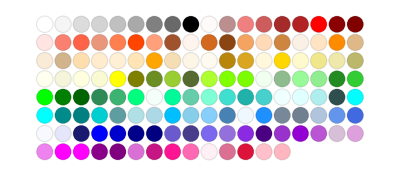

```mathematica
ColorData["HTML","Panel"]
```

```mathematica
ptClrs={
"ell"->Black,
"med"->Darker@Red,
"bar"->Brown,
"inc"->Darker@Green,
"ort"->Orange,
"cir"->Purple,
"npc"->ColorData["HTML","PaleVioletRed"],
"exc"->Darker@Green,
"ex12"->Darker@Green,
"ex23"->Darker@Green,
"ex31"->Darker@Green,
"dar"->ColorData["HTML","Navy"],
"x144"->ColorData["HTML","Navy"],
"x59"->ColorData["HTML","OrangeRed"],
"feu"-> ColorData["HTML","DarkKhaki"],
"antifeu"->ColorData["HTML","SlateGray"],
"anticompl"->Blue,
"steiner"->Brown,
"steinerinell"->Brown,
"x88"->Darker@Cyan,
"x100"->ColorData["HTML","SlateGray"],
"nag"->ColorData["HTML","MediumAquamarine"],
"mit"->Red(*Lighter@Blue*),
"sym"->ColorData["HTML","DodgerBlue"],
"bev"->Lighter@Purple,
"ger"->Darker@Cyan,
"spi"->ColorData["HTML","SpringGreen"],
"nap"->Red,
"hex"->Pink,
(* overrides *)
"red"->Red,
"green"->Green,
"blue"->Blue
};
```

```mathematica
ptClrs
```

{ell→-Graphics-,med→-Graphics-,bar→-Graphics-,inc→-Graphics-,ort→-Graphics-,cir→-Graphics-,npc→-Graphics-,exc→-Graphics-,ex12→-Graphics-,ex23→-Graphics-,ex31→-Graphics-,dar→-Graphics-,x144→-Graphics-,x59→-Graphics-,feu→-Graphics-,antifeu→-Graphics-,anticompl→-Graphics-,steiner→-Graphics-,steinerinell→-Graphics-,x88→-Graphics-,x100→-Graphics-,nag→-Graphics-,mit→-Graphics-,sym→-Graphics-,bev→-Graphics-,ger→-Graphics-,spi→-Graphics-,nap→-Graphics-,hex→-Graphics-,red→-Graphics-,green→-Graphics-,blue→-Graphics-}

```mathematica
Clear@plotEllb;
plotEllb[a_,b_,clr_:("ell"/.ptClrs)]:=Graphics[{
If[SameQ[clr,None],{},{If[ListQ@clr,Sequence@@clr,clr],Circle[{0,0},{a,b}]}]}];
Clear@plotEll;
plotEll[a_,clr_:("ell"/.ptClrs)]:=plotEllb[a,1,clr];
```

```mathematica
Clear@plotEllbAxesLow;
plotEllbAxesLow[a_,b_]:=Graphics@{Dashed,Gray,Thickness@Medium,{Line@{{-a,0},{a,0}},Line@{{0,-b},{0,b}}}};
```

```mathematica
Clear@plotEllAxesLow;
plotEllAxesLow[a_]:=plotEllbAxesLow[a,1];
```

```mathematica
Clear@plotEllAxes;plotEllAxes[a_,clr_:("ell"/.ptClrs)]:=Graphics@@Show[{plotEll[a,clr],plotEllAxesLow[a]}]
Clear@plotEllbAxes;
plotEllbAxes[a_,b_,clr_:("ell"/.ptClrs)]:=Graphics@@Show[{plotEllb[a,b,clr],plotEllbAxesLow[a,b]}]
```

```mathematica
Clear@plotEllFillb;
plotEllFillb[a_,b_,clrFill_,clr_:("ell"/.ptClrs)]:=Graphics[{
If[SameQ[clrFill,None],{},{If[ListQ@clrFill,Sequence@@clrFill,clrFill],Disk[{0,0},{a,b}]}],
If[SameQ[clr,None],{},{If[ListQ@clr,Sequence@@clr,clr],Circle[{0,0},{a,b}]}]
}];
Clear@plotEllFill;plotEllFill[a_,clrFill_,clr_:("ell"/.ptClrs)]:=plotEllFillb[a,1,clrFill,clr];
```

```mathematica
(*Clear@plotEll;
plotEll[a_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];
plotEllFill[a_,clrFill_,clr_:("ell"/.ptClrs)]:=Module[{int,ext},
int=ParametricPlot[r{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},{r,0,1},
PlotStyle->clrFill,PerformanceGoal->"Quality"];
ext=plotEll[a,clr];
Show[{int,ext}]];
plotEllb[a_,b_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],N[b]Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];*)
```

```mathematica
drawArrow[p0_,phat_,l_]:=Arrow[{p0,ray[p0,phat,l]}];
```

```mathematica
Clear@drawOrbit;
Options@drawOrbit={lgt->.25,drNormals->True,pSize->16,drVtxLabels->True,clr->{Thick,Darker@Blue}};
drawOrbit[orbitData_,OptionsPattern[](*lgt_:.25,drawNormals_:True,psize_:16*)]:=Module[{normals,orbit,halfAlpha},
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
halfAlpha="halfAlpha"/.orbitData;
Graphics[{
PointSize[Large],Arrowheads[Medium],
{OptionValue@clr,Point@orbit},
{FaceForm[GrayLevel@.9],EdgeForm@OptionValue@clr,Polygon@orbit},
If[OptionValue@drNormals,
{Black,
MapThread[drawArrow[#1,#2,OptionValue@lgt]&,{orbit,normals}],
Dashed,
drawArrow[orbit[[1]],"nRot"/.orbitData,OptionValue@lgt],
drawArrow[orbit[[1]],"nRotNeg"/.orbitData,OptionValue@lgt],
Text["α",ray[orbit[[1]],halfAlpha ,.33OptionValue@lgt]]},{}],
If[OptionValue@drVtxLabels,MapThread[txtSubscript["P",ToString@#1,OptionValue@pSize,ray[#2,-#3,.33OptionValue@lgt]]&,
{{1,2,3},orbit,normals}],{}]}]
];
```

```mathematica
Clear@drawOneNotable;drawOneNotable[clr_,at_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Point@at,Text[Style[txt,fntSize],at,{dx,dy}]};
circOneNotable[clr_,at_,rad_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Circle[at,rad],Text[Style[txt,fntSize],at,{dx,dy}]};
Clear@drawNotableLines;drawNotableLines[notables_]:=Graphics@{Darker[Gray],Dashed,
(* euler line: cir,bar,npc,ort *)
Line[{"cir","ort"}/.notables],
(* npc to feuerbach: npc,inc,feu *)
Line[{"npc","feu"}/.notables],
(* mittenpunkt to symmedian: mit,inc,sym *)
Line[{"mit","sym"}/.notables],
(* gergonne to mit: ger,bar,mit *)
Line[{"mit","ger"}/.notables],
(* nagel line: nag,bar,spi,inc *)
Line[{"nag","inc"}/.notables]};
Clear@drawNotables;
drawNotables[notables_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
drawNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotables;
circNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotablesSingleClr;
circNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@drawSomeNotables;
drawSomeNotables[notables_,nots_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@nots}];
Clear@drawBasicNotables;
drawBasicNotables[notables_,prefix_:""]:=drawSomeNotables[notables,{"inc","bar","ort","cir","npc","mit","feu","ger"},prefix];
Clear@drawBasicNotablesSingleClr;
drawBasicNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotables;
circBasicNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotablesSingleClr;
circBasicNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
```

## ManipX: Visualize the locus of a few centers

```mathematica
Clear@manipX;
Options@manipX={clr->Darker@Red,n->-1,slackX->.2,slackY->.2,perfGoal->"Speed"};
manipX[a_,trilinFn_,OptionsPattern[]]:=
DynamicModule[{ell,ons,gr,pl,x,xlab,pr,lab},
Manipulate[
ell=plotEllAxes[a,{Thick,Black}];
pl=Quiet@ParametricPlot[
ons=orbitNormals[a,toRad@tDeg2];
trilinFn[ons[[1]],ons[[3]]],{tDeg2,0,180},PlotStyle->OptionValue@clr,PerformanceGoal->OptionValue@perfGoal];
xlab=ToString[Subscript["X",OptionValue@n],StandardForm];
lab="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1];
pr={{-a-OptionValue@slackX,a+OptionValue@slackX},{-1-OptionValue@slackY,1+OptionValue@slackY}};
Dynamic[
ons=orbitNormals[a,toRad@tDeg];
x=trilinFn[ons[[1]],ons[[3]]];
gr=Graphics[{FaceForm@None,PointSize@Large,
drawPoly[ons[[1]],Blue],
{Darker@Red,Point@x,If[OptionValue@n>0,Text[Style[xlab,16],x,{-1.25,-1.25}],{}]}}];
Show[{ell,pl,gr},PlotLabel->Style[lab,{Black,16}],PlotRange->pr]],
{{tDeg,10.},-180,180,.1,Appearance->"Labeled"}],SaveDefinitions->True];
```

```mathematica
manipX[1.5,getX661Trilin,n->661,slackX->50,slackY->50]
```

```mathematica
manipX[1.45,getX49Trilin,n->49]
```

## Locus X661 and major-axis-bound X2590

```mathematica
DynamicModule[{a=3,ell,ons,gr,pl,x,xlab,pr,pr2,lab,slackX=50,slackY=50,slackX2=5,slackY2=.2,n=661,x662,x799,x2590,gr2,clr=Purple},
Manipulate[
ell=plotEllAxes[a,{Thick,Black}];
pl=Quiet@ParametricPlot[
ons=orbitNormals[a,toRad@tDeg2];
getX661Trilin[ons[[1]],ons[[3]]],{tDeg2,1,13},PlotStyle->clr,PerformanceGoal->"Speed"];
xlab=ToString[Subscript["X",n],StandardForm];
lab="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1];
pr={{-a-slackX,a+slackX},{-1-slackY,1+slackY}};
pr2={{-a-slackX2,a+slackX2},{-1-slackY2,1+slackY2}};
Dynamic[
ons=orbitNormals[a,toRad@tDeg];
x=getX661Trilin[ons[[1]],ons[[3]]];
x662=getX662Trilin[ons[[1]],ons[[3]]];
x799=getX799Trilin[ons[[1]],ons[[3]]];
x2590=getX2590Trilin[ons[[1]],ons[[3]]];
gr=Graphics[{FaceForm@None,PointSize@Large,
drawPoly[ons[[1]],Blue],
{Darker@Red,Point@x,If[n>0,Text[Style[xlab,16],x,{-1.25,-1.25}],{}]}}];
gr2=Graphics[{PointSize@Large,Point@x662,Point@x799,Red,Point@x2590}];
Grid[{{Show[{ell,pl,gr},PlotRange->pr,ImageSize->400],Show[{ell,gr,gr2},PlotRange->pr2,ImageSize->400]}}]],
{{tDeg,10.},-180,180,.1,Appearance->"Labeled"}],SaveDefinitions->True]
```

## Orbit and Derived Triangles

```mathematica
(* {"billiard","caustic",
"orbit","medial","orthic","intouch","excentral","extouch","anticompl","exfeuer"} *)
```

```mathematica
Clear@showDerivedTris;
Options@showDerivedTris={drLegends->True,drCaustic->True};
showDerivedTris[a_,tDeg_,OptionsPattern[]]:=Module[{caustic,ell,ca,cb,ellCaustic,clrs,orbit,normals,sides,tris,gr,maxX=2,maxY=2},
{ca,cb}=getTriCausticParams[a];
ell=plotEllAxes[a,{Thick,Black}];
ellCaustic=If[OptionValue@drCaustic,plotEllb[ca,cb,{Thick,Dashed,"feu"/.ptClrs}],{}];
clrs=If[OptionValue@drCaustic,
{Black,{Dashed,"feu"/.ptClrs},Blue,Darker@Red,"ort"/.ptClrs,{Dashed,"inc"/.ptClrs},"inc"/.ptClrs,{Dashed,Orange},{Dashed,Blue},"feu"/.ptClrs},
{Black,Blue,Darker@Red,"ort"/.ptClrs,{Dashed,"inc"/.ptClrs},"inc"/.ptClrs,{Dashed,Orange},{Dashed,Blue},"feu"/.ptClrs}];
{orbit,normals,sides}=orbitNormals[a,toRad@tDeg];
tris=(#[orbit,sides]&)/@{medialTriangle,orthicTriangle,intouchTriangle,
excentralTriangle,extouchTriangle,anticomplementaryTriangle,feuerbachTriangle};
gr=Graphics[{FaceForm@None,Dotted,Black,MapThread[{EdgeForm@{Thick,If[ListQ@#1,Sequence@@#1,#1]},Polygon@#2,If[ListQ@#1,Sequence@@#1,#1],Point@#2}&,
{Drop[clrs,If[OptionValue@drCaustic,2,1]],Prepend[tris,orbit]}]}];
If[OptionValue@drLegends,
Legended[Show[{ell,ellCaustic,gr},
Frame->True,ImageSize->Large,PlotLabel->Style["Orbit and Derived Triangles",Directive[{Black,14}]],PlotRange->{{-maxX,maxX},{-maxY,maxY}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
Style[#,20]&/@{"billiard",Sequence@@If[OptionValue@drCaustic,{"caustic"},{}],"orbit",
"medial","orthic","intouch","excentral","extouch","anticompl","feuerbach"}]],
Show[{ell,ellCaustic,gr},
Frame->True,ImageSize->Large,PlotLabel->Style["Orbit and Derived Triangles",Directive[{Black,14}]],PlotRange->{{-maxX,maxX},{-maxY,maxY}}]]
];
```

```mathematica
Manipulate[showDerivedTris[a,tDeg,drCaustic->False],
{{a,1.5},1.01,3.0,Appearance->"Labeled"},
{{tDeg,31},-180,180,1,Appearance->"Labeled"}]
```

```mathematica
(*DeleteFile[trisObj]*)
```

```mathematica
(*trisObj=CloudDeploy[%,"orbit and its derived triangles v1",Permissions->"Public"]*)
```

## Study of the Extouch Triangle: any points = X(9) ?

```mathematica
getExtouchPoints[a_,t_]:=Module[{ons,ext,extSides,mit,ctrs,ctrsToMit},
ons=orbitNormals[a,t];
mit=getMittenTrilin[ons[[1]],ons[[3]]];
ext=extouchTriangle[ons[[1]],ons[[3]]];
extSides=triLengthsRL@ext;
ctrs=getNewCenters[ext,extSides];
ctrsToMit=magn2[#[[3]]-mit]&/@ctrs;
Sort@ctrsToMit]
```

```mathematica
getExtouchPoints[1.5,.1]
```

{0.00140619,0.00457608,0.00457608,0.0207108,0.022654,0.0232223,0.0267117,0.0467858,0.0586188,0.0962077,0.096821,0.103379,0.104146,0.122968,0.130548,0.154313,0.164142,0.184458,0.200487,0.204133,0.205721,0.216355,0.225408,0.242849,0.256882,0.258647,0.275037,0.279787,0.284132,0.288281,0.294566,0.296662,0.300255,0.331179,0.332252,0.333042,0.337916,0.344519,0.345533,0.352323,0.353809,0.356862,0.361385,0.366049,0.367539,0.369718,0.37123,0.383186,0.39267,0.395929,0.412919,0.414113,0.416296,0.423888,0.431846,0.438208,0.440798,0.443402,0.450844,0.45223,0.456533,0.462625,0.477643,0.485082,0.487902,0.497456,0.5077,0.507861,0.536038,0.541244,0.561221,0.568369,0.583466,0.595836,0.614775,0.694969,0.746749,0.757866,0.766652,0.852882,0.865221,0.876889,0.890853,1.03576,1.12231,1.29198,1.31104,1.75313,1.75868,1.83376,1.89985,3.5784,6.97489,7.82759,7.85532,8.20022,8.93595,29.5711,47.6771,3539.4}

## Draw Orbits: Parametrize by x_1

```mathematica
Clear@drawSim;
Options@drawSim=Join[Options@getOrbitData,Options@drawOrbit,{drNotables->True,drLines->False,drTh->False,drVtxLabels->True,lgt->.5}];
drawSim[a_,x_,opts:OptionsPattern[]]:=Module[{ellPlot,orbitData,orbit,normals,notables,lab},
ellPlot=plotEll[a,{Thick,Black}];
orbitData=getOrbitData[N[a],N[x], FilterRules[{opts}, Options@getOrbitData]];(* N for speed *)
(* half-angle to display α at bisector *)
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
notables=getNotables[orbit,normals];
Show[{
ellPlot,
drawOrbit[orbitData,FilterRules[{opts},Options@drawOrbit]],
If[OptionValue@drNotables,drawNotables[notables],{}],
If[OptionValue@drLines,drawNotableLines[notables],{}]
},
ImageSize->Large,
AspectRatio->Automatic,
PlotRange->{{-2,2},{-1.1,1.1}},Frame->True,AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style["a="<>nf@a<>"; x="<>nf@x,20]]];
```

```mathematica
Clear@drawSimT;
Options@drawSimT=Options@drawSim;
drawSimT[a_,t_,opts:OptionsPattern[]]:=Module[{x,y},
x=a Cos@t;
y=Sin@t;
drawSim[a,x,{opts,posY->y>0}]];
```

```mathematica
Manipulate[
drawSim[a,clamp[x1,a],drLines->drLines0,posY->(!negY),drNotables->drNotables0],
{{a,1.5,"a/b"},1.01,3,.01,Appearance->"Labeled"},
{{x1,.5,"x_1"},-2,2,.01,Appearance->"Labeled"},
{{negY,False,"y_1<0"},{False,True}},
{{drNotables0,True,"show notables"},{False,True}},
{{drLines0,False,"show lines"},{False,True}},
SaveDefinitions->True]
```

## Ellipticity: which loci are elliptic w/ least squares (findEllParams)

```mathematica
Clear@findEllParams;
findEllParams[a_,i_,locus_,name_]:=Module[{m,b,c2,lsc2,causticC,ls,lsa,lsb,err,causticA,causticB,abRatio,causticRatio,lsRatio},
abRatio=a;
c2=Abs[a^2-1];
m=(#^2)&/@locus;(* { {x1^2,y1^2}, {x2^2,y2^2}, ... } *)
b=ConstantArray[1,Length@locus];
ls=LeastSquares[m,b];
{lsa,lsb}=Sqrt[1/#]&/@ls;
lsRatio=lsa/lsb;
lsc2=Abs[lsa^2-lsb^2];
err=Norm[m.ls-b];
{causticA,causticB}=getTriCausticParams[a];
causticRatio=causticA/causticB;
causticC=Sqrt@Abs[causticA^2-causticB^2];
<|"i"->i,
"name"->name,
"errNegl"->(Abs[err]<10^-6),
"ellSim"->negl[abRatio-lsRatio],
"ellSimInv"->negl[abRatio-1/lsRatio],
"ellEq"->(negl[a-lsa]&&negl[1-lsb]),
"ellEqInv"->(negl[1-lsa]&&negl[a-lsb]),
"causticSim"->negl[causticRatio-lsRatio],
"causticSimInv"->negl[causticRatio-1/lsRatio],
"causticEq"->(negl[causticA-lsa]&&negl[causticB-lsb]),
"causticEqInv"->(negl[causticB-lsa]&&negl[causticA-lsb]),
"confocal"->negl[c2-lsc2],
"err"->err,
"a"->a,"b"->1,"a/b"->abRatio,"b/a"->(1/abRatio),
"c2"->c2,"lsc2"->lsc2,
"lsA"->lsa,"lsB"->lsb,"lsA/lsB"->lsRatio,"lsB/lsA"->(1/lsRatio),
"caustic_a"->causticA,"caustic_b"->causticB,"caustic_a/b"->causticRatio,"caustic_b/a"->(1/causticRatio),
"caustic_c"->causticC
|>];
```

```mathematica
Clear@getLociTable;
getLociTable[a_,ctrFn_,tmax_:π,step_:toRad[.1]]:=Module[{nc,pts,loci},
loci=Table[
nc=ctrFn[a,t]//Quiet;
pts=(#[[3]]&/@nc);
{t,pts},
{t,.5*step,tmax,step}];
Transpose[#[[2]]&/@loci]];
```

```mathematica
findEllParamsSingle[a_,n_]:=Module[{locus},
(* locus of single center *)
locus=getLociTable[a,newCenters[#1,#2,{n}]&];
findEllParams[a,1,locus[[1]],centerNames[[n]]]]
```

```mathematica
Clear@findEllParamsFn;
Options@findEllParamsFn={minDeg->0,maxDeg->359,degStep->1.};
findEllParamsFn[a_,getFn_,OptionsPattern[]]:=Module[{locus,ons},
(* locus of single center *)
locus=Table[ons=orbitNormals[a,toRad@t];getFn[ons[[1]],ons[[3]]],{t,OptionValue@minDeg,OptionValue@maxDeg,OptionValue@degStep}];
findEllParams[a,-1,locus,"n/a"]]
```

## [slow] Draw Loci: w/ and without lobes

```mathematica
Clear@medialLocus;
medialLocus[a_,tmax_,ps_:("med"/.ptClrs)]:=Module[{orbit,normals,sides,meds},
Quiet@ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
meds=getMedians@@orbit;
meds[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@orthicVertexLocus;
orthicVertexLocus[a_,tmax_,ps_:("ort"/.ptClrs)]:=Module[{orbit,normals,sides,meds},
Quiet@ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthicTriangle[orbit,sides][[1]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@symmedianLocus;
symmedianLocus[a_,tmax_,ps_:("sym"/.ptClrs),psExc_:("exc"/.ptClrs)]:=Module[{o,n,s,ppOrbit,ppExc,exc,syms},
ppOrbit=Quiet@ParametricPlot[
{o,n,s}=Evaluate[orbitNormals[a,t]];
syms=symmedialTriangle[o,s];
syms[[1]],
{t,0,tmax},PlotStyle->ps];
ppExc=Quiet@ParametricPlot[
{o,n,s}=Evaluate[orbitNormals[a,t]];
exc=excentralTriangle[o,s];
syms=symmedialTriangle[exc,triLengthsRL@exc];
syms[[1]],
{t,0,tmax},PlotStyle->psExc];
Show[{ppOrbit,ppExc},PlotRange->All]
];
```

```mathematica
Clear@incenterLocus;
incenterLocus[a_,tmax_,ps_:("inc"/.ptClrs)]:=Module[{ons},
Quiet@ParametricPlot[
ons=Evaluate[orbitNormals[a,t]];
getIncenterTrilin[ons[[1]],ons[[3]]],
{t,0,tmax},PerformanceGoal->"Speed",PlotStyle->ps]
];
```

```mathematica
Clear@baricenterLocus;
baricenterLocus[a_,tmax_,ps_:("bar"/.ptClrs)]:=Module[{orbit,normals,sides},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
(*getCentroid[orbit,triLengths@orbit]*)
getBaricenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@orthocenterLocus;
orthocenterLocus[a_,tmax_,ps_:("ort"/.ptClrs)]:=Module[{orbit,normals,sides},
Quiet@ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getOrthocenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@circumcenterLocus;
circumcenterLocus[a_,tmax_,ps_:("cir"/.ptClrs)]:=Module[{orbit,normals,sides},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getCircumcenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@ninepointcenterLocus;
ninepointcenterLocus[a_,tmax_,ps_:("npc"/.ptClrs)]:=Module[{orbit,normals,sides},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getNinepointcenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@excenterLocus;
excenterLocus[a_,tmax_,ps_:("exc"/.ptClrs)]:=Module[{orbit,normals,sides},
Quiet@ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getExcenters[orbit,normals][[1]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
(*Module[{a=1.5,o,n,s,tDeg=35.,gr,inc},
{o,n,s}=orbitNormals[a,toRad@tDeg];
inc=getIncenterTrilin[o,s];
gr=Graphics[{FaceForm@None,
{EdgeForm@{Thick,Blue},Polygon@o,EdgeForm@{Thick,Darker@Green,Dashed}},
{PointSize@Large,Darker@Green,Point@inc},
{Dashed,Black,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}}}];
Show[{plotEll[a,{Thick,Black}],gr,incenterLocus[a,π/1.2,Darker@Green]},Frame->True,PlotRange->All,ImageSize->Large]]*)
```

```mathematica
(*Module[{a=1.25,o,n,s,tDeg=30.,gr,exc,inc},
{o,n,s}=orbitNormals[a,toRad@tDeg];
inc=getIncenterTrilin[o,s];
exc=excentralTriangle[o,s];
gr=Graphics[{FaceForm@None,EdgeForm@{Thick,Blue},Polygon@o,EdgeForm@{Thick,Darker@Green,Dashed},Polygon@exc,PointSize@Large,Darker@Green,Point@exc,Point@inc}];
Show[{plotEll[a,{Thick,Black}],gr,incenterLocus[a,π/1.2,Darker@Green],excenterLocus[a,2π,Darker@Green]},Frame->True,PlotRange->All,ImageSize->Large]]*)
```

```mathematica
Clear@exFeuerbachcenterLocus;
exFeuerbachcenterLocus[a_,tmax_,ps_:("feu"/.ptClrs)]:=Module[{ons,eps=.01},
Quiet@ParametricPlot[
ons=orbitNormals[a,t+eps];
feuerbachTriangle[ons[[1]],ons[[3]]][[1]],
{t,0,tmax},PlotStyle->ps]]
```

```mathematica
Clear@feuerbachcenterLocus;
feuerbachcenterLocus[a_,tmax_,ps_:("feu"/.ptClrs)]:=Module[{orbit,normals,sides,npc,inc,inradius,feu},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
npc=getNinepointcenter@@orbit;
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
inradius=inRadius0[inc,orbit[[1]],orbit[[2]]];
getFeuerbachpoint[npc,inc,inradius],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
(*GraphicsRow[{
incenterLocus[2,π/1.2]//Quiet,
baricenterLocus[2,π/1.2]//Quiet,
orthocenterLocus[2,π/1.2]//Quiet,
circumcenterLocus[2,π/1.2]//Quiet,
ninepointcenterLocus[2,π/1.2]//Quiet,
excenterLocus[2,π]//Quiet,
feuerbachcenterLocus[2,π/1.2]//Quiet}
]*)
```

```mathematica
Clear@intouchLocus;
intouchLocus[a_,tmax_,ps_:("exc"/.ptClrs)]:=Module[{orbit,normals,sides,tps},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
tps=intouchTriangle[orbit,sides];
tps[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
(*Show[intouchLocus[1.5,2π]//Quiet,ImageSize->Small]*)
```

```mathematica
Clear@getFeuLoci;getFeuLoci[a_,showExFeu_:False]:=Show[{
plotEll[a],
feuerbachcenterLocus[a,π/1.2]//Quiet,
If[showExFeu,exFeuerbachcenterLocus[a,2π]//Quiet,{}]}];
```

```mathematica
Clear@getDashedFeuLoci;
getDashedFeuLoci[a_]:=feuerbachcenterLocus[a,π/1.2,{Dashed,"feu"/.ptClrs}]//Quiet
```

```mathematica
Clear@getAntiComplementaryVertexLocus;
getAntiComplementaryVertexLocus[a_,tmax_:2π,ps_:{Dashed,Blue}]:=Module[{orbit,normals,sides,act},
Quiet@ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
act=anticomplementaryTriangle[orbit,triLengthsRL@orbit];
act[[1]],
{t,0,tmax},PlotStyle->ps]];
```

```mathematica
(*getAntiComplementaryVertexLocus[1.5]*)
```

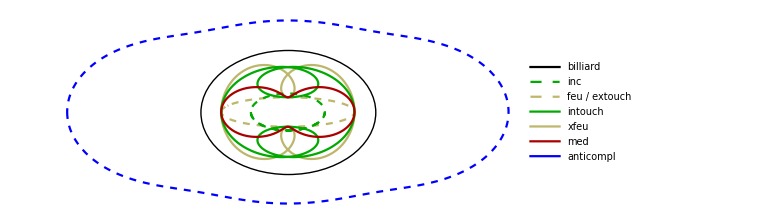

```mathematica
Module[{a=1.5,orbitData,lgt=.2},
orbitData=getOrbitData[a,toRad[30.]];
Legended[Show[{
(*drawOrbit[orbitData,lgt],*)
plotEll[a],
feuerbachcenterLocus[a,π/1.2,{Dashed,"feu"/.ptClrs}],
exFeuerbachcenterLocus[a,2π],
intouchLocus[a,2π],
incenterLocus[a,π,{Dashed,"exc"/.ptClrs}],
medialLocus[a,2π],
getAntiComplementaryVertexLocus[a]
}, PlotRange->All,ImageSize->Large],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell","inc","feu","inc","feu","med","anticompl"},
{{},Dashed,Dashed,{},{},{},{}}}],
{"billiard","inc","feu / extouch","intouch","xfeu","med","anticompl"}]]]//Quiet
```

```mathematica
nonEllipticPlot=Module[{a=1.5,orbitData,lgt=.2,thick=.0075},
orbitData=getOrbitData[a,toRad[30.]];
Legended[Show[{
(*drawOrbit[orbitData,lgt],*)
plotEll[a,{Thickness@thick,Black}],
(*feuerbachcenterLocus[a,π/1.2,{"bar"/.ptClrs}],*)
feuerbachcenterLocus[a,π/1.2,Directive["feu"/.ptClrs,Thickness@thick]],
exFeuerbachcenterLocus[a,2π,Directive["sym"/.ptClrs,Thickness@thick]],
intouchLocus[a,2π,Directive["inc"/.ptClrs,Thickness@thick]],
medialLocus[a,2π,Directive["med"/.ptClrs,Thickness@thick]]
}, PlotRange->All,ImageSize->Large],
LineLegend[MapThread[
Directive[{Thickness@.015,#2,#1/.ptClrs}]&,
{{"ell","feu",(*"bar",*)"inc","sym","med"},
{{},{},(*{},*){},{},{}}}],
Style[#,20]&/@{"Billiard & X_100",(*"Feuerbach Point",*)"Extouch Triangle & X_11","Intouch Triangle","Feuerbach Triangle","Medial Triangle"}]]]//Quiet;
```

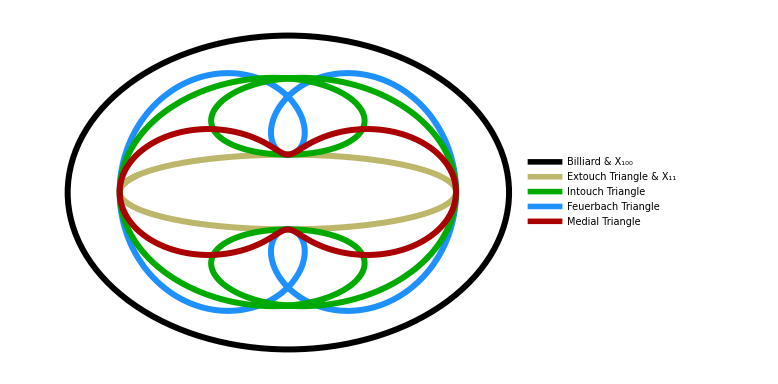

```mathematica
nonEllipticPlot
```

```mathematica
(*export3["0040_non_elliptic",nonEllipticPlot]*)
```

```mathematica
(*Module[{a=1.5,orbitData,lgt=.2},
orbitData=getOrbitData[a,toRad[30.]];
Legended[Show[{
(*drawOrbit[orbitData,lgt],*)
plotEll[a],
intouchLocus[a,2π],
medialLocus[a,2π,"med"/.ptClrs],
getAntiComplementaryVertexLocus[a]
}, PlotRange->All,ImageSize->Large],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell","inc","med","anticompl"},
{{},{},{},Dashed}}],
{"billiard","intouch vertex","medial vertex","anticompl vertex"}]]]//Quiet*)
```

#### The locus of the Outer Napoleon Point is not particularly interesting

```mathematica
Clear@outerNapoleonLocus;
outerNapoleonLocus[a_,tmax_,ps_:("nap"/.ptClrs)]:=Module[{orbit,normals,sides,nap},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
nap=outerNapoleonTriangle[orbit,sides];
nap[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
(*outerNapoleonLocus[1.5,2π]//Quiet*)
```

#### Path of First Morley Center Just outside Incenter' s

```mathematica
Clear@morleyIncenterLocus;
morleyIncenterLocus[a_,tmax_]:=Module[{orbit,normals,sides,mor1,mor2,mor3,inc},
ListLinePlot[Transpose@Table[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
mor1=getFirstMorleyTrilin[orbit,sides];
mor2=getSecondMorleyTrilin[orbit,sides];
mor3=getThirdMorleyTrilin[orbit,sides];
inc=getIncenterTrilin[orbit,sides];
{inc,mor1,mor2,mor3},
{t,0,tmax,tmax/100}],PlotStyle->{Darker@Green,Automatic,Automatic,Automatic},
PlotLegends->{"inc","morley 1","morley 2","morley 3"},ImageSize->Large]
];
```

```mathematica
(*Quiet@morleyIncenterLocus[1.5,π/1.27]*)
```

```mathematica
Clear@orthicIncenterLocus;
orthicIncenterLocus[a_,tmax_,ps_:("inc"/.ptClrs)]:=Module[{orbit,normals,sides,feet,ortInc,ortSides},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
feet=getAltBases@@orbit;
ortSides=triLengthsRL@feet;
ortInc=getIncenterTrilin[feet,ortSides];
ortInc,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
(*Show[orthicIncenterLocus[1.5,π/1.2]//Quiet,ImageSize->Small]*)
```

```mathematica
(* using anticomplementary triangle, but needs higher frequency *)
Clear@orthicIntouchTriangleIncenterLocus;
orthicIntouchTriangleIncenterLocus[a_,tmax_,ps_:Red]:=Module[{orbit,normals,sides,orthic},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"intouchAnticomplOrtInc"/.orthic,
{t,0,tmax},PlotStyle->ps]
];
```

#### Shows orthic' s orthocenter (dashed) too

```mathematica
getOrthicIncOrt[a_,t_]:=Module[{orbit,normals,sides,orthic,ort,inc},
{orbit,normals,sides}=orbitNormals[a,t];
orthic=getOrthicData@orbit;
inc="orthicInc"/.orthic;
ort="ort"/.orthic;
{inc,ort}];
```

```mathematica
Clear@orthicsOrthicIncenterLocus2;
orthicsOrthicIncenterLocus2[a_,tmax_:π/1.2,ps_:Blue]:=
ParametricPlot[
Evaluate@List@@getOrthicIncOrt[a,t],{t,0,tmax},
PlotStyle->({ps,{Dashed,ps}}),
PlotRange->All];
```

```mathematica
(*orthicsOrthicIncenterLocus2[1.5]//Quiet*)
```

```mathematica
Clear@orthicsOrthicIncenterLocus;
orthicsOrthicIncenterLocus[a_,tmaxInc_:π/1.2,tmaxOrt_:π/1.2,psOrthicOrt_:{Dashed,Blue},psOrtOrtInc_:Blue]:=Module[{orbit,normals,sides,orthic,ppInc,ppOrt,mr=8},
ppInc=ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"orthicInc"/.orthic,
{t,0,tmaxInc},PlotStyle->Directive[Thick,psOrtOrtInc],PerformanceGoal->"Quality",MaxRecursion->mr];
ppOrt=ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"ort"/.orthic,
{t,0,tmaxOrt},PlotStyle->psOrthicOrt,PerformanceGoal->"Quality",MaxRecursion->mr];
Show[{ppOrt,ppInc},PlotRange->All]
];
```

```mathematica
Clear@orthicsOrthicAnticomplIncenterLocus;
orthicsOrthicAnticomplIncenterLocus[a_,tmax_,ps_:Pink]:=Module[{orbit,normals,sides,orthic},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"orthicAnticomplInc"/.orthic,
{t,0,tmax},PlotStyle->ps]
];
```

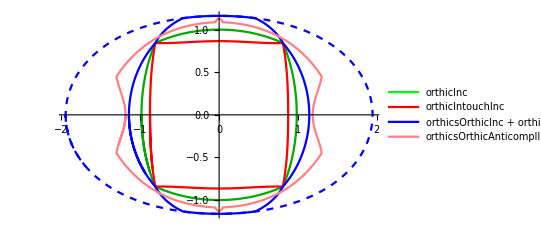

```mathematica
Legended[Show[{
orthicIncenterLocus[1.5,π/1.2],
orthicIntouchTriangleIncenterLocus[1.5,π/1.2],
orthicsOrthicIncenterLocus[1.5,π/1.2],
orthicsOrthicAnticomplIncenterLocus[1.5,π/1.2]},PlotRange->All
]//Quiet,
LineLegend[Directive[{Thickness@Large,#}]&/@{Green,Red,Blue,Pink},
{"orthicInc","orthicIntouchInc","orthicsOrthicInc + orthicOrthocenter (dashed)","orthicsOrthicAnticomplInc"}]]
```

## [slow] Test Ellipticity of Actual Centers

### A few irrationals, showing finite least-squares error, i.e., their locus isn't an ellipse

```mathematica
findEllParamsFn[1.5,#]["err"]&/@{getX359,getX360,getX364,getX365,getX367}
```

{0.031202,0.011047,0.0107786,0.00526853,0.000503454}

#### Locus of Excentral's Mittenpunkt isn' t elliptic

```mathematica
findEllParamsFn[1.5,getX168Trilin]["err"]
```

0.00972225

#### Locus of Excentral's Incenter X164 isn' t elliptic

```mathematica
findEllParamsFn[1.5,getX164Trilin]["err"]
```

0.0107592

#### Locus of Excentral' s Barycenter X164 *is* elliptic

```mathematica
findEllParamsFn[1.5,getX165Trilin]["err"]
```

6.48792×10^-14

#### Locus of Extouch Incenter X1’’ is ??? elliptic

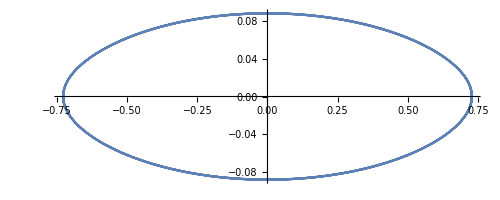

```mathematica
Module[{a=1.5,ons},
Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg];getExtouchX1Trilin[ons[[1]],ons[[3]]],{tDeg,0,360}]]
```

```mathematica
findEllParamsFn[1.5,getExtouchX1Trilin]["err"]
```

0.230694

#### Locus of ACT' s Mittenpunkt X7 is elliptic. Locus of Medial' s Mitenpunkt X142 is elliptic.

```mathematica
findEllParamsFn[1.5,getX142Trilin]["err"]
```

9.03514×10^-14

```mathematica
findEllParamsFn[1.98,getX9OrthicTrilin,minDeg->80,maxDeg->100]["err"]
```

0.000086822

### Compare w/ error of Symmedian

```mathematica
findEllParamsFn[1.5,getSymmedianTrilin]["err"]
```

0.00303499

```mathematica
doLociTables2=False;
Module[{fname="data/loci15t2.m"},
If[doLociTables2,
loci125t=getLociTable[1.25,newCenters];
loci15t=getLociTable[1.5,newCenters];
loci20t=getLociTable[2.0,newCenters];
loci25t=getLociTable[2.5,newCenters];
loci30t=getLociTable[3.0,newCenters];
Print@"saving..." ;
Save[fname,{loci125t,loci15t,loci20t,loci25t,loci30t}],
Print@"loading...";Get[fname]]];
```

loading...

```mathematica
ellParams125=Quiet@Table[findEllParams[1.25,i,loci125t[[i]],centerNames[[i]]],{i,Length@loci125t}]//Sort[#,#1["err"]<#2["err"]&]&;
ellParams15=Quiet@Table[findEllParams[1.5,i,loci15t[[i]],centerNames[[i]]],{i,Length@loci15t}]//Sort[#,#1["err"]<#2["err"]&]&;
ellParams20=Quiet@Table[findEllParams[2.,i,loci20t[[i]],centerNames[[i]]],{i,Length@loci20t}]//Sort[#,#1["err"]<#2["err"]&]&;
ellParams25=Quiet@Table[findEllParams[2.5,i,loci25t[[i]],centerNames[[i]]],{i,Length@loci25t}]//Sort[#,#1["err"]<#2["err"]&]&;
ellParams30=Quiet@Table[findEllParams[3.,i,loci30t[[i]],centerNames[[i]]],{i,Length@loci30t}]//Sort[#,#1["err"]<#2["err"]&]&;
```

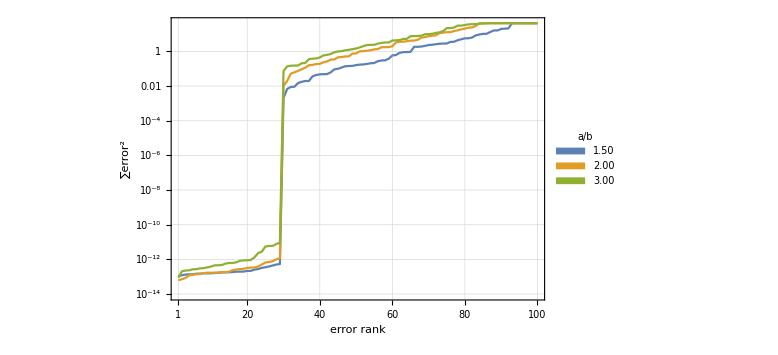

```mathematica
leastSquaresErrorPlot=ListLogPlot[{
#["err"]&/@Take[ellParams15,100],
#["err"]&/@Take[ellParams20,100],
#["err"]&/@Take[ellParams30,100]}
,Frame->True,GridLines->Automatic,PlotRange->{{1,100},All},FrameStyle->16,FrameTicks->{{Automatic,None},{Prepend[Range[10,100,10],1],None}},FrameLabel->(Style[#,{Black,16}]&/@{"error rank","∑error^2"}),PlotStyle->Thick,ImageSize->Large,Joined->True,PlotLegends->SwatchLegend[Style[nfn[#,2],{Black,20}]&/@{1.5,2.,3},LegendFunction->"Frame",LegendLabel->Style["a/b",{Black,20}]]]
```

```mathematica
(*export3["1100_least_squares_error",leastSquaresErrorPlot]*)
```

```mathematica
tabErrs15=Prepend[MapIndexed[{First@#2,#1["i"],Sequence@@If[#1["errNegl"],{nfn[#1["lsA"],2],nfn[#1["lsB"],2]},{"--","--"}],ScientificForm[N@#1["err"],2]}&,ellParams15],{"rank","center","a","b","∑err^2"}];
```

```mathematica
Grid[tabErrs15,Alignment->Right]
```

rank | center | a | b | ∑err^2
1 | 100 | 1.50 | 1.00 | 1.×10^-13
2 | 80 | 1.65 | 0.77 | 1.2×10^-13
3 | 46 | 1.47 | 1.18 | 1.3×10^-13
4 | 20 | 1.18 | 2.43 | 1.4×10^-13
5 | 63 | 0.58 | 0.38 | 1.4×10^-13
6 | 72 | 0.75 | 0.35 | 1.5×10^-13
7 | 40 | 0.83 | 1.25 | 1.5×10^-13
8 | 36 | 2.57 | 2.34 | 1.6×10^-13
9 | 57 | 0.96 | 0.64 | 1.6×10^-13
10 | 56 | 1.05 | 0.74 | 1.6×10^-13
11 | 4 | 0.98 | 1.48 | 1.6×10^-13
12 | 78 | 1.12 | 0.28 | 1.7×10^-13
13 | 79 | 0.85 | 0.68 | 1.8×10^-13
14 | 7 | 0.79 | 0.52 | 1.8×10^-13
15 | 65 | 0.90 | 0.58 | 1.8×10^-13
16 | 88 | 1.50 | 1.00 | 1.9×10^-13
17 | 11 | 1.14 | 0.24 | 1.9×10^-13
18 | 84 | 1.09 | 5.25 | 2.×10^-13
19 | 5 | 0.44 | 0.50 | 2.×10^-13
20 | 12 | 0.55 | 0.38 | 2.2×10^-13
21 | 1 | 0.64 | 0.30 | 2.2×10^-13
22 | 2 | 0.26 | 0.17 | 2.6×10^-13
23 | 3 | 0.10 | 0.48 | 2.8×10^-13
24 | 55 | 0.44 | 0.09 | 3.2×10^-13
25 | 8 | 0.48 | 0.07 | 3.5×10^-13
26 | 10 | 0.08 | 0.11 | 3.9×10^-13
27 | 90 | 3.93 | 0.34 | 4.4×10^-13
28 | 21 | 0.19 | 0.05 | 5.1×10^-13
29 | 35 | 0.33 | 0.03 | 5.3×10^-13
30 | 37 | -- | -- | 2.1×10^-3
31 | 6 | -- | -- | 6.8×10^-3
32 | 45 | -- | -- | 8.9×10^-3
33 | 60 | -- | -- | 9.2×10^-3
34 | 86 | -- | -- | 1.5×10^-2
35 | 71 | -- | -- | 1.8×10^-2
36 | 41 | -- | -- | 2.×10^-2
37 | 81 | -- | -- | 2.×10^-2
38 | 58 | -- | -- | 3.6×10^-2
39 | 62 | -- | -- | 4.4×10^-2
40 | 31 | -- | -- | 4.7×10^-2
41 | 89 | -- | -- | 4.8×10^-2
42 | 42 | -- | -- | 4.9×10^-2
43 | 17 | -- | -- | 6.2×10^-2
44 | 13 | -- | -- | 9.2×10^-2
45 | 83 | -- | -- | 9.9×10^-2
46 | 48 | -- | -- | 1.2×10^-1
47 | 32 | -- | -- | 1.4×10^-1
48 | 61 | -- | -- | 1.4×10^-1
49 | 82 | -- | -- | 1.5×10^-1
50 | 43 | -- | -- | 1.6×10^-1
51 | 51 | -- | -- | 1.7×10^-1
52 | 85 | -- | -- | 1.8×10^-1
53 | 19 | -- | -- | 1.9×10^-1
54 | 27 | -- | -- | 2.1×10^-1
55 | 69 | -- | -- | 2.1×10^-1
56 | 47 | -- | -- | 2.7×10^-1
57 | 39 | -- | -- | 3.×10^-1
58 | 38 | -- | -- | 3.1×10^-1
59 | 16 | -- | -- | 3.8×10^-1
60 | 52 | -- | -- | 5.8×10^-1
61 | 28 | -- | -- | 6.2×10^-1
62 | 25 | -- | -- | 8.3×10^-1
63 | 99 | -- | -- | 9.×10^-1
64 | 14 | -- | -- | 9.1×10^-1
65 | 98 | -- | -- | 9.3×10^-1
66 | 44 | -- | -- | 1.8
67 | 22 | -- | -- | 1.8
68 | 34 | -- | -- | 1.9
69 | 75 | -- | -- | 2.1
70 | 54 | -- | -- | 2.3
71 | 53 | -- | -- | 2.4
72 | 29 | -- | -- | 2.6
73 | 15 | -- | -- | 2.8
74 | 33 | -- | -- | 2.8
75 | 24 | -- | -- | 2.9
76 | 74 | -- | -- | 3.5
77 | 97 | -- | -- | 3.6
78 | 67 | -- | -- | 4.4
79 | 23 | -- | -- | 5.
80 | 96 | -- | -- | 5.7
81 | 91 | -- | -- | 5.7
82 | 76 | -- | -- | 6.4
83 | 18 | -- | -- | 8.3
84 | 73 | -- | -- | 9.4
85 | 70 | -- | -- | 1.×10^1
86 | 94 | -- | -- | 1.×10^1
87 | 92 | -- | -- | 1.3×10^1
88 | 77 | -- | -- | 1.6×10^1
89 | 95 | -- | -- | 1.6×10^1
90 | 49 | -- | -- | 2.×10^1
91 | 87 | -- | -- | 2.×10^1
92 | 59 | -- | -- | 2.1×10^1
93 | 64 | -- | -- | 4.2×10^1
94 | 68 | -- | -- | 4.2×10^1
95 | 26 | -- | -- | 4.2×10^1
96 | 66 | -- | -- | 4.2×10^1
97 | 50 | -- | -- | 4.2×10^1
98 | 93 | -- | -- | 4.2×10^1
99 | 30 | -- | -- | 4.2×10^1
100 | 9 | -- | -- | 4.2×10^1

```mathematica
Grid[Take[tabErrs15,29],Alignment->Right]//TeXForm
```

\begin{array}{rrrrr}
 \text{rank} & \text{center} & \text{a} & \text{b} & \text{$\sum $err${}^{\wedge}$2} \\
 1 & 100 & 1.50 & 1.00 & 1.\times 10^{-13} \\
 2 & 80 & 1.65 & 0.77 & 1.2\times 10^{-13} \\
 3 & 46 & 1.47 & 1.18 & 1.3\times 10^{-13} \\
 4 & 20 & 1.18 & 2.43 & 1.4\times 10^{-13} \\
 5 & 63 & 0.58 & 0.38 & 1.4\times 10^{-13} \\
 6 & 72 & 0.75 & 0.35 & 1.5\times 10^{-13} \\
 7 & 40 & 0.83 & 1.25 & 1.5\times 10^{-13} \\
 8 & 36 & 2.57 & 2.34 & 1.6\times 10^{-13} \\
 9 & 57 & 0.96 & 0.64 & 1.6\times 10^{-13} \\
 10 & 56 & 1.05 & 0.74 & 1.6\times 10^{-13} \\
 11 & 4 & 0.98 & 1.48 & 1.6\times 10^{-13} \\
 12 & 78 & 1.12 & 0.28 & 1.7\times 10^{-13} \\
 13 & 79 & 0.85 & 0.68 & 1.8\times 10^{-13} \\
 14 & 7 & 0.79 & 0.52 & 1.8\times 10^{-13} \\
 15 & 65 & 0.90 & 0.58 & 1.8\times 10^{-13} \\
 16 & 88 & 1.50 & 1.00 & 1.9\times 10^{-13} \\
 17 & 11 & 1.14 & 0.24 & 1.9\times 10^{-13} \\
 18 & 84 & 1.09 & 5.25 & 2.\times 10^{-13} \\
 19 & 5 & 0.44 & 0.50 & 2.\times 10^{-13} \\
 20 & 12 & 0.55 & 0.38 & 2.2\times 10^{-13} \\
 21 & 1 & 0.64 & 0.30 & 2.2\times 10^{-13} \\
 22 & 2 & 0.26 & 0.17 & 2.6\times 10^{-13} \\
 23 & 3 & 0.10 & 0.48 & 2.8\times 10^{-13} \\
 24 & 55 & 0.44 & 0.09 & 3.2\times 10^{-13} \\
 25 & 8 & 0.48 & 0.07 & 3.5\times 10^{-13} \\
 26 & 10 & 0.08 & 0.11 & 3.9\times 10^{-13} \\
 27 & 90 & 3.93 & 0.34 & 4.4\times 10^{-13} \\
 28 & 21 & 0.19 & 0.05 & 5.1\times 10^{-13} \\
\end{array}

```mathematica
Grid[Drop[#,{3,4}]&/@Drop[tabErrs15,{2,30}],Alignment->Right]//TeXForm
```

\begin{array}{rrr}
 \text{rank} & \text{center} & \text{$\sum $err${}^{\wedge}$2} \\
 30 & 37 & 2.1\times 10^{-3} \\
 31 & 6 & 6.8\times 10^{-3} \\
 32 & 45 & 8.9\times 10^{-3} \\
 33 & 60 & 9.2\times 10^{-3} \\
 34 & 86 & 1.5\times 10^{-2} \\
 35 & 71 & 1.8\times 10^{-2} \\
 36 & 41 & 2.\times 10^{-2} \\
 37 & 81 & 2.\times 10^{-2} \\
 38 & 58 & 3.6\times 10^{-2} \\
 39 & 62 & 4.4\times 10^{-2} \\
 40 & 31 & 4.7\times 10^{-2} \\
 41 & 89 & 4.8\times 10^{-2} \\
 42 & 42 & 4.9\times 10^{-2} \\
 43 & 17 & 6.2\times 10^{-2} \\
 44 & 13 & 9.2\times 10^{-2} \\
 45 & 83 & 9.9\times 10^{-2} \\
 46 & 48 & 1.2\times 10^{-1} \\
 47 & 32 & 1.4\times 10^{-1} \\
 48 & 61 & 1.4\times 10^{-1} \\
 49 & 82 & 1.5\times 10^{-1} \\
 50 & 43 & 1.6\times 10^{-1} \\
 51 & 51 & 1.7\times 10^{-1} \\
 52 & 85 & 1.8\times 10^{-1} \\
 53 & 19 & 1.9\times 10^{-1} \\
 54 & 27 & 2.1\times 10^{-1} \\
 55 & 69 & 2.1\times 10^{-1} \\
 56 & 47 & 2.7\times 10^{-1} \\
 57 & 39 & 3.\times 10^{-1} \\
 58 & 38 & 3.1\times 10^{-1} \\
 59 & 16 & 3.8\times 10^{-1} \\
 60 & 52 & 5.8\times 10^{-1} \\
 61 & 28 & 6.2\times 10^{-1} \\
 62 & 25 & 8.3\times 10^{-1} \\
 63 & 99 & 9.\times 10^{-1} \\
 64 & 14 & 9.1\times 10^{-1} \\
 65 & 98 & 9.3\times 10^{-1} \\
 66 & 44 & 1.8 \\
 67 & 22 & 1.8 \\
 68 & 34 & 1.9 \\
 69 & 75 & 2.1 \\
 70 & 54 & 2.3 \\
 71 & 53 & 2.4 \\
 72 & 29 & 2.6 \\
 73 & 15 & 2.8 \\
 74 & 33 & 2.8 \\
 75 & 24 & 2.9 \\
 76 & 74 & 3.5 \\
 77 & 97 & 3.6 \\
 78 & 67 & 4.4 \\
 79 & 23 & 5. \\
 80 & 96 & 5.7 \\
 81 & 91 & 5.7 \\
 82 & 76 & 6.4 \\
 83 & 18 & 8.3 \\
 84 & 73 & 9.4 \\
 85 & 70 & 1.\times 10^1 \\
 86 & 94 & 1.\times 10^1 \\
 87 & 92 & 1.3\times 10^1 \\
 88 & 77 & 1.6\times 10^1 \\
 89 & 95 & 1.6\times 10^1 \\
 90 & 49 & 2.\times 10^1 \\
 91 & 87 & 2.\times 10^1 \\
 92 & 59 & 2.1\times 10^1 \\
 93 & 64 & 4.2\times 10^1 \\
 94 & 68 & 4.2\times 10^1 \\
 95 & 26 & 4.2\times 10^1 \\
 96 & 66 & 4.2\times 10^1 \\
 97 & 50 & 4.2\times 10^1 \\
 98 & 93 & 4.2\times 10^1 \\
 99 & 30 & 4.2\times 10^1 \\
 100 & 9 & 4.2\times 10^1 \\
\end{array}

```mathematica
ellParamsSorted=Sort[Select[ellParams15,(#["errNegl"])&],#1["i"]<#2["i"]&];
```

#### Which are ellipses?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,ellParamsSorted]//TableForm
```

1 | X(1): INCENTER
2 | X(2): CENTROID
3 | X(3): CIRCUMCENTER
4 | X(4): ORTHOCENTER
5 | X(5): NINE-POINT CENTER
6 | X(7): GERGONNE POINT
7 | X(8): NAGEL POINT
8 | X(10): SPIEKER CENTER
9 | X(11): FEUERBACH POINT
10 | X(12): {X(1),X(5)}-HARMONIC CONJUGATE OF X(11)
11 | X(20): DE LONGCHAMPS POINT
12 | X(21): SCHIFFLER POINT
13 | X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36)
14 | X(36): INVERSE-IN-CIRCUMCIRCLE OF INCENTER
15 | X(40): BEVAN POINT
16 | X(46): X(4)-CEVA CONJUGATE OF X(1)
17 | X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
18 | X(56): EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
19 | X(57): ISOGONAL CONJUGATE OF X(9)
20 | X(63): ISOGONAL CONJUGATE OF X(19)
21 | X(65): ORTHOCENTER OF THE INTOUCH TRIANGLE
22 | X(72): ISOGONAL CONJUGATE OF X(28)
23 | X(78): ISOGONAL CONJUGATE OF X(34)
24 | X(79): ISOGONAL CONJUGATE OF X(35)
25 | X(80): REFLECTION OF INCENTER IN FEUERBACH POINT
26 | X(84): ISOGONAL CONJUGATE OF X(40)
27 | X(88): ISOGONAL CONJUGATE OF X(44)
28 | X(90): X(3)-CROSS CONJUGATE OF X(1)
29 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

#### What are their trilinears

```mathematica
centerEqns//Length
```

100

```mathematica
centerEqns[[7]]
```

(b c)/(-a+b+c)

```mathematica
Module[{ell,notEll,both},
notEll=Sort[Select[ellParams15,(!#["errNegl"])&],#1["i"]<#2["i"]&];
ell=Sort[Select[ellParams15,(#["errNegl"])&],#1["i"]<#2["i"]&];
both=Join[ell,notEll];
(*Print[both[[6]]];*)
Grid[Append[#,centerEqns[[#[[3]]]]]&/@MapIndexed[{First@#2,#1["name"],#1["i"]}&,both],ItemStyle->{Automatic,Join[ConstantArray[Blue,Length@ell],ConstantArray[Red,Length@notEll]]}, Alignment->Left]]
```

1 | X(1): INCENTER | 1 | 1
2 | X(2): CENTROID | 2 | b c
3 | X(3): CIRCUMCENTER | 3 | cosA
4 | X(4): ORTHOCENTER | 4 | secA
5 | X(5): NINE-POINT CENTER | 5 | cosB cosC+sinB sinC
6 | X(7): GERGONNE POINT | 7 | (b c)/(-a+b+c)
7 | X(8): NAGEL POINT | 8 | (-a+b+c)/a
8 | X(10): SPIEKER CENTER | 10 | b c (b+c)
9 | X(11): FEUERBACH POINT | 11 | -cosB cosC-sinB sinC+1
10 | X(12): {X(1),X(5)}-HARMONIC CONJUGATE OF X(11) | 12 | cosB cosC+sinB sinC+1
11 | X(20): DE LONGCHAMPS POINT | 20 | cosA-cosB cosC
12 | X(21): SCHIFFLER POINT | 21 | (-a+b+c)/(b+c)
13 | X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36) | 35 | 2 cosA+1
14 | X(36): INVERSE-IN-CIRCUMCIRCLE OF INCENTER | 36 | 1-2 cosA
15 | X(40): BEVAN POINT | 40 | -cosA+cosB+cosC-1
16 | X(46): X(4)-CEVA CONJUGATE OF X(1) | 46 | -cosA+cosB+cosC
17 | X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE) | 55 | a (-a+b+c)
18 | X(56): EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE) | 56 | a/(-a+b+c)
19 | X(57): ISOGONAL CONJUGATE OF X(9) | 57 | 1/(-a+b+c)
20 | X(63): ISOGONAL CONJUGATE OF X(19) | 63 | cotA
21 | X(65): ORTHOCENTER OF THE INTOUCH TRIANGLE | 65 | cosB+cosC
22 | X(72): ISOGONAL CONJUGATE OF X(28) | 72 | cotA (b+c)
23 | X(78): ISOGONAL CONJUGATE OF X(34) | 78 | 1/(1-secA)
24 | X(79): ISOGONAL CONJUGATE OF X(35) | 79 | 1/(2 cosA+1)
25 | X(80): REFLECTION OF INCENTER IN FEUERBACH POINT | 80 | 1/(1-2 cosA)
26 | X(84): ISOGONAL CONJUGATE OF X(40) | 84 | 1/(-cosA+cosB+cosC-1)
27 | X(88): ISOGONAL CONJUGATE OF X(44) | 88 | 1/(-2 a+b+c)
28 | X(90): X(3)-CROSS CONJUGATE OF X(1) | 90 | 1/(-cosA+cosB+cosC)
29 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT | 100 | 1/(b-c)
30 | X(6): SYMMEDIAN / LEMOINE / GREBE POINT | 6 | a
31 | X(9): MITTENPUNKT | 9 | -a+b+c
32 | X(13): 1st ISOGONIC CENTER (FERMAT / TORRICELLI POINT) | 13 | cscApPi3
33 | X(14): 2nd ISOGONIC CENTER | 14 | cscAmPi3
34 | X(15): 1st ISODYNAMIC POINT | 15 | sinApPi3
35 | X(16): 2nd ISODYNAMIC POINT | 16 | sinAmPi3
36 | X(17): 1st NAPOLEON POINT | 17 | cscApPi6
37 | X(18): 2nd NAPOLEON POINT | 18 | cscAmPi6
38 | X(19): CLAWSON POINT | 19 | 1/(-a^2+b^2+c^2)
39 | X(22): EXETER POINT | 22 | a (-a^4+b^4+c^4)
40 | X(23): FAR-OUT POINT | 23 | a (-a^4+b^4-b^2 c^2+c^4)
41 | X(24): PERSPECTOR OF ABC AND ORTHIC-OF-ORTHIC TRIANGLE | 24 | cos2A secA
42 | X(25): HOMOTHETIC CENTER OF ORTHIC AND TANGENTIAL TRIANGLES | 25 | a/(-a^2+b^2+c^2)
43 | X(26): CIRCUMCENTER OF THE TANGENTIAL TRIANGLE | 26 | a (a^2 (-cos2A)+b^2 cos2B+c^2 cos2C)
44 | X(27): CEVAPOINT OF ORTHOCENTER AND CLAWSON CENTER | 27 | secA/(b+c)
45 | X(28): CEVAPOINT OF X(19) AND X(25) | 28 | tanA/(b+c)
46 | X(29): CEVAPOINT OF INCENTER AND ORTHOCENTER | 29 | secA/(cosB+cosC)
47 | X(30): EULER INFINITY POINT | 30 | -a+b+c
48 | X(31): 2nd POWER POINT | 31 | a^2
49 | X(32): 3rd POWER POINT | 32 | a^3
50 | X(33): PERSPECTOR OF THE ORTHIC AND INTANGENTS TRIANGLES | 33 | secA+1
51 | X(34): X(4)-BETH CONJUGATE OF X(4) | 34 | 1-secA
52 | X(37): CROSSPOINT OF INCENTER AND CENTROID | 37 | b+c
53 | X(38): CROSSPOINT OF X(1) AND X(75) | 38 | b^2+c^2
54 | X(39): BROCARD MIDPOINT | 39 | a (b^2+c^2)
55 | X(41): X(6)-CEVA CONJUGATE OF X(31) | 41 | a^2 (-a+b+c)
56 | X(42): CROSSPOINT OF INCENTER AND SYMMEDIAN POINT | 42 | a (b+c)
57 | X(43): X(6)-CEVA CONJUGATE OF X(1) | 43 | a b+a c-b c
58 | X(44): X(6)-LINE CONJUGATE OF X(1) | 44 | -2 a+b+c
59 | X(45): X(9)-BETH CONJUGATE OF X(1) | 45 | -a+2 b+2 c
60 | X(47): X(110)-BETH CONJUGATE OF X(34) | 47 | cos2A
61 | X(48): CROSSPOINT OF X(1) AND X(63) | 48 | tanB+tanC
62 | X(49): CENTER OF SINE-TRIPLE-ANGLE CIRCLE | 49 | cos3A
63 | X(50): X(74)-CEVA CONJUGATE OF X(184) | 50 | sin3A
64 | X(51): CENTROID OF ORTHIC TRIANGLE | 51 | a^2 (cosB cosC+sinB sinC)
65 | X(52): ORTHOCENTER OF ORTHIC TRIANGLE | 52 | cos2A (cosB cosC+sinB sinC)
66 | X(53): SYMMEDIAN POINT OF ORTHIC TRIANGLE | 53 | tanA (cosB cosC+sinB sinC)
67 | X(54): KOSNITA POINT | 54 | 1/(cosB cosC+sinB sinC)
68 | X(58): ISOGONAL CONJUGATE OF X(10) | 58 | a/(b+c)
69 | X(59): ISOGONAL CONJUGATE OF X(11) | 59 | 1/(-cosB cosC-sinB sinC+1)
70 | X(60): ISOGONAL CONJUGATE OF X(12) | 60 | 1/(cosB cosC+sinB sinC+1)
71 | X(61): ISOGONAL CONJUGATE OF X(17) | 61 | cosA sPi6+cPi6 sinA
72 | X(62): ISOGONAL CONJUGATE OF X(18) | 62 | cPi6 sinA-cosA sPi6
73 | X(64): ISOGONAL CONJUGATE OF X(20) | 64 | 1/(cosA-cosB cosC)
74 | X(66): ISOGONAL CONJUGATE OF X(22) | 66 | (b c)/(-a^4+b^4+c^4)
75 | X(67): ISOGONAL CONJUGATE OF X(23) | 67 | (b c)/(-a^4+b^4-b^2 c^2+c^4)
76 | X(68): PRASOLOV POINT | 68 | cosA sec2A
77 | X(69): SYMMEDIAN POINT OF THE ANTICOMPLEMENTARY TRIANGLE | 69 | cosA/a^2
78 | X(70): ISOGONAL CONJUGATE OF X(26) | 70 | (b c)/(a^2 (-cos2A)+b^2 cos2B+c^2 cos2C)
79 | X(71): ISOGONAL CONJUGATE OF X(27) | 71 | cosA (b+c)
80 | X(73): CROSSPOINT OF INCENTER AND CIRCUMCENTER | 73 | secB+secC
81 | X(74): ISOGONAL CONJUGATE OF EULER INFINITY POINT | 74 | 1/(cosA-2 cosB cosC)
82 | X(75): ISOTOMIC CONJUGATE OF INCENTER | 75 | 1/a^2
83 | X(76): 3rd BROCARD POINT | 76 | 1/a^3
84 | X(77): ISOGONAL CONJUGATE OF X(33) | 77 | 1/(secA+1)
85 | X(81): CEVAPOINT OF INCENTER AND SYMMEDIAN POINT | 81 | 1/(b+c)
86 | X(82): ISOGONAL CONJUGATE OF X(38) | 82 | 1/(b^2+c^2)
87 | X(83): CEVAPOINT OF CENTROID AND SYMMEDIAN POINT | 83 | (b c)/(b^2+c^2)
88 | X(85): ISOTOMIC CONJUGATE OF X(9) | 85 | (b^2 c^2)/(-a+b+c)
89 | X(86): CEVAPOINT OF INCENTER AND CENTROID | 86 | (b c)/(b+c)
90 | X(87): X(2)-CROSS CONJUGATE OF X(1) | 87 | 1/(a b+a c-b c)
91 | X(89): ISOGONAL CONJUGATE OF X(45) | 89 | 1/(-a+2 b+2 c)
92 | X(91): ISOGONAL CONJUGATE OF X(47) | 91 | sec2A
93 | X(92): CEVAPOINT OF INCENTER AND CLAWSON POINT | 92 | csc2A
94 | X(93): ISOGONAL CONJUGATE OF X(49) | 93 | sec3A
95 | X(94): ISOGONAL CONJUGATE OF X(50) | 94 | csc3A
96 | X(95): CEVAPOINT OF CENTROID AND CIRCUMCENTER | 95 | (b^2 c^2)/(cosB cosC+sinB sinC)
97 | X(96): ISOGONAL CONJUGATE OF X(52) | 96 | sec2A/(cosB cosC+sinB sinC)
98 | X(97): ISOGONAL CONJUGATE OF X(53) | 97 | cotA/(cosB cosC+sinB sinC)
99 | X(98): TARRY POINT | 98 | (b c)/(-a^2 b^2-a^2 c^2+b^4+c^4)
100 | X(99): STEINER POINT | 99 | (b c)/(b^2-c^2)

#### Which are similar to the billiard?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["ellSim"])&]]//TableForm
```

1 | X(2): CENTROID
2 | X(7): GERGONNE POINT
3 | X(57): ISOGONAL CONJUGATE OF X(9)
4 | X(63): ISOGONAL CONJUGATE OF X(19)
5 | X(88): ISOGONAL CONJUGATE OF X(44)
6 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

#### Which are similar to rotated billiard?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["ellSimInv"])&]]//TableForm
```

1 | X(4): ORTHOCENTER
2 | X(10): SPIEKER CENTER
3 | X(40): BEVAN POINT

#### Which are identical to the billiard?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["ellEq"]||#["ellEqInv"])&]]//TableForm
```

1 | X(88): ISOGONAL CONJUGATE OF X(44)
2 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

#### Which are similar to the caustic?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["causticSim"])&]]//TableForm
```

1 | X(11): FEUERBACH POINT
2 | X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)

#### Which are similar to rotated caustic?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["causticSimInv"])&]]//TableForm
```

1 | X(3): CIRCUMCENTER
2 | X(84): ISOGONAL CONJUGATE OF X(40)

#### Which are identical to the caustic?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["causticEq"]||#["causticEqInv"])&]]//TableForm
```

1 | X(11): FEUERBACH POINT

#### Which are confocal?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["confocal"])&]]//TableForm
```

1 | X(11): FEUERBACH POINT
2 | X(88): ISOGONAL CONJUGATE OF X(44)
3 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

```mathematica
Clear@tab2TeX;tab2TeX[ellParams_,test_]:=TeXForm@MapIndexed[{First@#2,#1["name"]}&,Select[ellParams,test]];
```

```mathematica
allTeXtables=Module[{texEll,texBilSim,texBilEq,texCauSim,texCauEq,texConf},
MapThread[{#1,tab2TeX[ellParamsSorted,#2]}&,
Transpose@{
{"00_ell",True&},
{"11_simBill",(#["ellSim"])&},
{"12_simBillRot",(#["ellSimInv"])&},
{"13_eqBill",(#["ellEq"]||#["ellEqInv"])&},
{"21_simCaus",(#["causticSim"])&},
{"21_simCausRot",(#["causticSimInv"])&},
{"23_causEq",(#["causticEq"]||#["causticEqInv"])&},
{"31_confoc",(#["confocal"])&}
}]];
```

```mathematica
(*Export["tex/tex_"<>#[[1]]<>".txt",#[[2]]]&/@allTeXtables*)
```

#### Export to XLS

```mathematica
(*Export["ellParams.xlsx",{Keys[findEllParams[[1]]],
Sequence@@(Values/@Sort[Select[findEllParams,#["errNegl"]&],#1["i"]<#2["i"]&])}]*)
```

## Precomp Loci

```mathematica
Clear@precompLoci;
precompLoci[a_]:=Module[{ell,tmax=π/1.2},
Show[{
incenterLocus[a,tmax]//Quiet,
baricenterLocus[a,tmax]//Quiet,
orthocenterLocus[a,tmax]//Quiet,
circumcenterLocus[a,tmax]//Quiet,
ninepointcenterLocus[a,tmax]//Quiet,
(* note excenters require full 2π *)
excenterLocus[a,2π]//Quiet,
feuerbachcenterLocus[a,tmax]//Quiet
}]];
```

```mathematica
precompLociBasic[a_]:=Module[{ell,tmax=π/1.2},
Show[{
incenterLocus[a,tmax]//Quiet,
baricenterLocus[a,tmax]//Quiet,
orthocenterLocus[a,tmax]//Quiet,
circumcenterLocus[a,tmax]//Quiet,
ninepointcenterLocus[a,tmax]//Quiet
}]];
```

```mathematica
precompLociNonEll[a_]:=Module[{ell,tmax=π/1.2},
Quiet@Show[{
exFeuerbachcenterLocus[a,2π],
intouchLocus[a,2π,{Dashed,"inc"/.ptClrs}],
medialLocus[a,2π,{Dashed,"npc"/.ptClrs}]
}]];
```

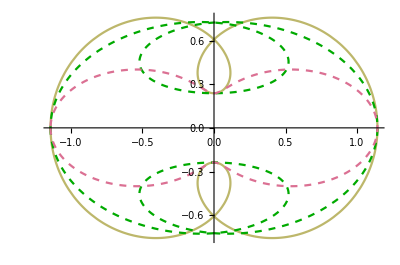

```mathematica
Show[precompLociNonEll[1.5],PlotRange->All]
```

## Load Loci Tables for X(1) ~ X(100) [[or generate/save]]

```mathematica
Directory[]
```

C:\Users\drezn\Dropbox\Mathematica\Billiards

```mathematica
(*loci15t=getLociTable[1.5,newCenters];*)
```

```mathematica
doLociTables=False;
Module[{a=1.5,fname="data/loci15t.m"},
If[doLociTables,
loci15t=getLociTable[a,newCenters];
lociOrt15t=getLociTable[a,newCentersOrthic];
lociMed15t=getLociTable[a,newCentersMedial];
lociExc15t=getLociTable[a,newCentersExc,π/1.28];
lociIntouch15t=getLociTable[a,newCentersIntouch,π/1.2];
lociExtouch15t=getLociTable[a,newCentersExtouch,π/1.27];
lociAnticompl15t=getLociTable[a,newCentersAnticompl,π/1.28];
lociExfeuerbach15t=getLociTable[a,newCentersExfeuer];
Print@"saving..." ;
Save[fname,{loci15t,lociOrt15t,lociMed15t,lociExc15t,lociIntouch15t,lociExtouch15t,lociAnticompl15t,lociExfeuerbach15t}],
Print@"loading...";Get[fname]]];
```

loading...

```mathematica
newCenters[2.,t,{1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

{{X(1),INCENTER,{If[2. √Abs[1+3. Cos[t]^2]<1/1000000000,0,0/(0+2. √(1+3. Cos[t]^2))],If[2. √Abs[1+3. Cos[t]^2]<1/1000000000,0,0/(0+2. √(1+3. Cos[t]^2))]},{1.,1.,1.}}}

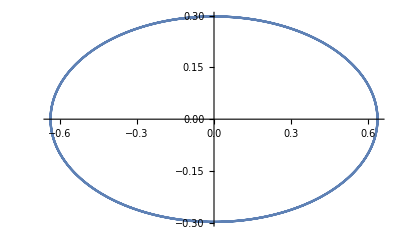

```mathematica
ListLinePlot[Table[newCenters[1.5,t+.001,{1}][[1,3]],{t,0,2π,π/1000}]]
```

*** GENERATES BILLIARD
X(100)  ANTICOMPLEMENT OF FEUERBACH POINT IS THE BILLIARD

*** GENERATES BILLIARD
X(88) = ISOGONAL CONJUGATE OF X(44)

X(44) = X(6)-LINE CONJUGATE OF X(1)
*** X(44) lies on these lines:
Trilinears       b + c - 2a : c + a - 2b : a + b - 2c
Barycentrics  a(b + c - 2a) : b(c + a - 2b) : c(a + b - 2c)
X(44) = (3r2 + 6rR + s2)*X(1) - 18rR*X(2) - 6r2*X(3)    (Peter Moses, April 2, 2013)

LINE-CONJUGATE: (looked up glossary)
Let P = p : q : r, U = u : v : w
The P-line conjugate of U is the point of intersection of line PU and the trilinear polar of the isogonal conjugate of U.

I.e., intersect line X(6)X(1) with the trilinear polar (TP) of the isog conjugate of X(1) which is X(1) itself.

The TP of X(1) is L1, the antiorthic axis, i.e., the orthic axis of the excentral triangle.

the orthic axis of a triangle are give by points (Oa, Ob,Oc) where each side of the orthic triangle meet the triangle sides (Oa, Ob, Oc)

-Graphics-
*** to summarize:

1) to get X(44) intersect the line connecting the incenter X(1) and the symmedian point X(6) with the orthic axis of the extriangle.
2) to get X(88) which generates the billiard, get the isogonal conjugate of X(44).

```mathematica
DynamicModule[{a=1.5,o,n,s,gr,ell,o2,o3,locus2,exc,exc2,locusExc2,causticAB,ellCaustic},
ell=plotEll[a,{Thick,Black}];
locus2=Table[Module[{o2a,n2a,s2a},
{o2a,n2a,s2a}=orbitNormals[a,toRad@tDeg2+.01];
{o2a[[1,1]]/a,o2a[[1,2]]}],{tDeg2,0,359,1}];
locusExc2=Table[Module[{o2a,n2a,s2a,exc2a},
{o2a,n2a,s2a}=orbitNormals[a,toRad@tDeg2+.01];
exc2a=excentralTriangle[o2a,s2a];
{exc2a[[1,1]]/a,exc2a[[1,2]]}],{tDeg2,0,359,1}];
causticAB=getTriCausticParams[a];
ellCaustic=plotEllb[Sequence@@causticAB,{Thick,Brown}];
Manipulate[
{o,n,s}=orbitNormals[a,toRad@tDeg+.01];
exc=excentralTriangle[o,s];
o2={#[[1]]a/ causticAB[[1]],#[[2]]/causticAB[[2]]}&/@o;
exc2={#[[1]]/a,#[[2]]}&/@exc;
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@o,Blue,Point@o},
{EdgeForm@{Thick,Dashed,Blue},Polygon@o2,Blue,Point@o2}
(*,{EdgeForm@{Thick,Darker@Green},Polygon@exc,Darker@Green,Point@exc},
{EdgeForm@{Thick,Dashed,Darker@Green},Polygon@exc2,Darker@Green,Point@exc2},
{Blue,Line@locus2},
{Darker@Green,Line@locusExc2}*)
}];
Show[{ell,ellCaustic,gr},PlotRange->{{-3,3},{-3,3}}],
{{tDeg,30},-180,180,1}]]
```

#### Order - Dependent has to change that

```mathematica
Clear@showLoci;
showLoci[locus_,a_,lociList_,
auto_,range_,imgSize_:400]:=Module[{ell,ellCaustic,ca,cb,name,lociMaxX,maxX,lociMaxY,maxY,pts,clrs,ncs,lls},
ell=plotEll[a,Black];
{ca,cb}=getTriCausticParams[a];
ellCaustic=plotEllb[ca,cb,{Dashed,Black}];
ncs=#[[locus]]&/@lociList;
clrs={
Black(* billiard *),
{Dashed,Black}(*caustic*),
Blue,(* orbit *)
Red,(* medial *)
"ort"/.ptClrs,(* orthic *)
"inc"/.ptClrs,(* intouch *)
{Dashed,Blue},(* excentral *)
{Dashed,"inc"/.ptClrs},(* extouch *)
{Dashed,Red},(* anticompl *)
"feu"/.ptClrs (* feuer *)
};
pts={PointSize@Medium,MapThread[{If[ListQ@#1,Second@#1,#1],Point@#2[[1]]}&,{Drop[clrs,2],ncs}]};
name=centerNames[[locus]];
(* NEED NOT DO THIS FOR ALL LOCI!!! *)
lociMaxX=clamp[#,10]&/@Table[Max[Select[Join[{a},Sequence@@((First/@(#[[l]]))&/@lociList)],NumberQ]],
{l,1,Length@lociList[[1]]}];
lociMaxY=clamp[#,10]&/@Table[Max[Select[Join[{1},(* b = 1 *) Sequence@@((Second/@(#[[l]]))&/@lociList)],NumberQ]],
{l,1,Length@lociList[[1]]}];
lls=MapThread[ListLinePlot[#1[[locus]],ClippingStyle->None,PlotStyle->#2]&,{lociList,Drop[clrs,2]}];
{maxX,maxY}=If[auto,
1.1{lociMaxX[[locus]],lociMaxY[[locus]]},
{range,range}];
Legended[Show[{ell,ellCaustic,Sequence@lls,Graphics@pts},
ImageSize->{imgSize,imgSize},
Axes->True,
PlotLabel->Style[name,Directive[{Black,14}]],
PlotRange->{{-maxX,maxX},{-maxY,maxY}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"billiard","caustic","orbit",
"medial","orthic","intouch","excentral","extouch","anticompl","feuerbach"}]]];
```

```mathematica
lociList15t={loci15t,lociMed15t,lociOrt15t,lociIntouch15t,lociExc15t,lociExtouch15t,lociAnticompl15t,lociExfeuerbach15t};
```

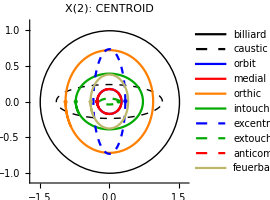

```mathematica
showLoci[2,1.5,lociList15t, True,2,200]
```

#### Feuerbach point of anticomplementary triangle sweeps the billiard just like the anticomplement of feuerbach of reference triangle.

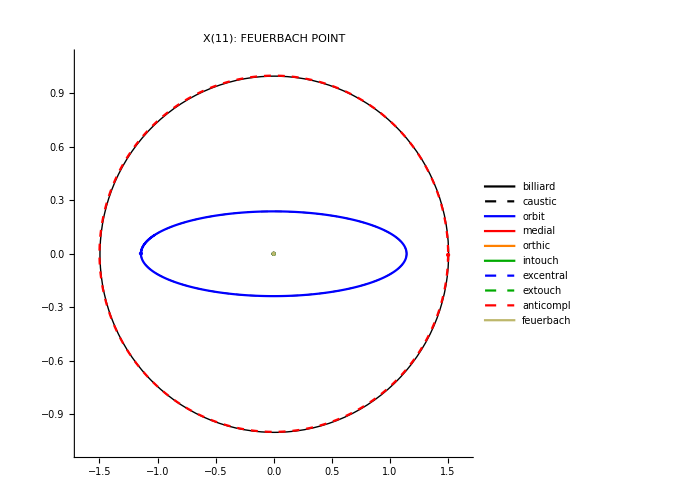

```mathematica
Module[{d=.001,loci0},
(* fake other empty loci *)
loci0=ConstantArray[{{-d,-d/2},{d,-d/2},{0,d/2}},100];
showLoci[11,1.5,{loci15t,loci0,loci0,loci0,loci0,loci0,lociAnticompl15t,loci0},
True,2,500]]
```

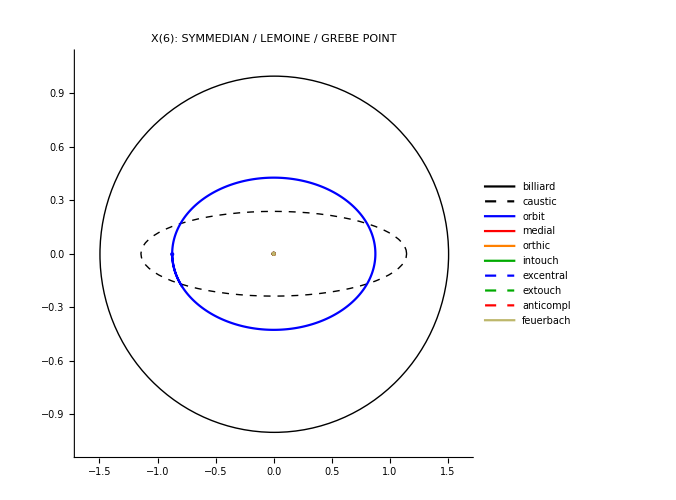

```mathematica
Module[{d=.001,loci0},
(* fake other empty loci *)
loci0=ConstantArray[{{-d,-d/2},{d,-d/2},{0,d/2}},100];
showLoci[6,1.5,{loci15t,loci0,loci0,loci0,loci0,loci0,loci0,loci0},
True,2,500]]
```

```mathematica
showAllLoci=False;
If[showAllLoci,
Manipulate[showLoci[locus,1.5,lociList15t,
auto,range,500],
{{locus,1},1,Length@loci15t,1,Appearance->"Open"},
{{auto,True},{True,False}},
{{range,2},{1,2,4,8,16}},SaveDefinitions->True]];
```

## Save Loci Frames to File

```mathematica
createLociFrames=False;
If[createLociFrames,showLociFrames=Table[Print@locus;showLoci[locus,1.5,lociList15t,
True,2,500],{locus,1,Length@loci15t,1}]; 
Length@showLociFrames];
```

```mathematica
Directory[]
```

C:\Users\drezn\Dropbox\Mathematica\Billiards

```mathematica
getLocusFname[i_]:="loci/locus_"<>padZ[i]<>".png";
```

```mathematica
createLociFrames=False;If[createLociFrames,
If[!DirectoryQ["loci"],CreateDirectory["loci"]];
MapIndexed[Export[getLocusFname[First[#2]],#1]&,showLociFrames]];
```

## Napoleon Summits and Loci

```mathematica
getOuterNapoleonInfoLow[orbit_,sides_]:=Module[{sqrt3ov2=.5Sqrt@3.,meds,naps,napGs,side,area,centroid,tri},
meds=getMedians@@orbit;
naps=MapThread[#1+#2sqrt3ov2 perp[norm@(#4-#3)]&,{meds,sides,RotateLeft@orbit,RotateRight@orbit}];
napGs=MapThread[#1+(#2-#1)/3&,{meds,naps}];
side=magn[napGs[[2]]-napGs[[1]]];
area=.5sqrt3ov2*(side^2);
centroid=Total[napGs]/3;
<|"summits"->naps,"tri"->napGs,"side"->side,"area"->area,"meds"->meds,"centroid"->centroid,"orbit"->orbit|>];
```

```mathematica
Clear@getOuterNapoleonSummits;
getOuterNapoleonSummits[a_,t_]:=Module[{sqrt3ov2=.5Sqrt@3.,o,n,s},
{o,n,s}=orbitNormals[a,t];
getOuterNapoleonInfoLow[o,s]];
```

```mathematica
Clear@getOuterNapoleonExcSummits;
getOuterNapoleonExcSummits[a_,t_]:=Module[{sqrt3ov2=.5Sqrt@3.,o,n,s,exc,excSides},
{o,n,s}=orbitNormals[a,t];
exc=excentralTriangle[o,s];
excSides=triLengthsRL@exc;
Join[getOuterNapoleonInfoLow[exc,excSides],<|"baseOrbit"->o,"baseSides"->s|>]];
```

```mathematica
Clear@makeOneNapoleonFrame;
makeOneNapoleonFrame[a_,ell_,napPts_,tDeg_]:=Module[{ons,gr,aequi,lab},
ons=getOuterNapoleonSummits[a,toRad@tDeg];
gr=Graphics[{FaceForm@None,PointSize@Large,Point@{0,0},ellLabelPoints[a,ons["orbit"],"P",14,.15],
{EdgeForm@{Blue,Thick},Polygon@ons["orbit"],Blue,Point@ons["meds"]},{Darker@Green,MapThread[{{Dashed,Line@{#1,#2}},{Thick,Line@{#3,#2},Line@{#4,#2}},Point@#2}&,{ons["meds"],ons["summits"],RotateLeft@ons["orbit"],RotateRight@ons["orbit"]}]},
{EdgeForm@{Thick,Purple},FaceForm@{Purple,Opacity@.1},Polygon@ons["tri"],Purple,Point@ons["tri"],Point@ons["centroid"]},
(* loci *)
{{EdgeForm@{Thick,Dashed,Blue},Polygon@(First[#@"meds"]&/@napPts)},
{EdgeForm@{Thick,Dashed,Darker@Green},Polygon@(First[#@"summits"]&/@napPts)},
{EdgeForm@{Thick,Dashed,Purple},Polygon@(First[#@"tri"]&/@napPts)},
{EdgeForm@{Purple},Polygon@(#["centroid"]&/@napPts)}}}];
lab="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°, L_equi="<>nfn[ons["side"],3]<>", A_equi="<>nfn[ons["area"],3];
Show[{gr,ell},PlotRange->{{-3,3},{-3,3}},PlotLabel->Style[lab,{20,Black}],ImageSize->Large,Frame->True]];
```

```mathematica
DynamicModule[{ell,ons,gr,napPts},
Manipulate[
ell=plotEll[a,{Black,Thick}];
napPts=Table[getOuterNapoleonSummits[a,toRad@tDeg0],{tDeg0,0,359,1}];
Dynamic@makeOneNapoleonFrame[a,ell,napPts,tDeg],
{{a,1.5},1.01,3,.1,Appearance->"Open"},
{{tDeg,30},-360,360,1,Appearance->"Open"},SaveDefinitions->True]]
```

```mathematica
Clear@makeOneNapoleonFrameExc;
makeOneNapoleonFrameExc[a_,ell_,napPts_,tDeg_]:=Module[{ons,gr,aequi,lab,o},
ons=getOuterNapoleonExcSummits[a,toRad@tDeg];
o=orbitNormals[a,toRad@tDeg][[1]];
gr=Graphics[{FaceForm@None,PointSize@Large,Point@{0,0},ellLabelPoints[a,ons["orbit"],"P",14,.15],
{EdgeForm@{Black},Polygon@o},
{EdgeForm@{Blue,Thick},Polygon@ons["orbit"],Blue,Point@ons["meds"]},{Darker@Green,MapThread[{{Dashed,Line@{#1,#2}},{Thick,Line@{#3,#2},Line@{#4,#2}},Point@#2}&,{ons["meds"],ons["summits"],RotateLeft@ons["orbit"],RotateRight@ons["orbit"]}]},
{EdgeForm@{Thick,Purple},FaceForm@{Purple,Opacity@.1},Polygon@ons["tri"],Purple,Point@ons["tri"],Point@ons["centroid"]},
(* loci *)
{{EdgeForm@{Thick,Dashed,Blue},Polygon@(First[#@"meds"]&/@napPts)},
{EdgeForm@{Thick,Dashed,Darker@Green},Polygon@(First[#@"summits"]&/@napPts)},
{EdgeForm@{Thick,Dashed,Purple},Polygon@(First[#@"tri"]&/@napPts)},
{EdgeForm@{Purple},Polygon@(#["centroid"]&/@napPts)}}}];
lab="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°, L_equi="<>nfn[ons["side"],3]<>", A_equi="<>nfn[ons["area"],3];
Show[{gr,ell},PlotRange->{{-8,8},{-5,5}},PlotLabel->Style[lab,{20,Black}],ImageSize->Large,Frame->True]];
```

```mathematica
DynamicModule[{ell,ons,gr,napPts},
Manipulate[
ell=plotEll[a,{Black,Thick}];
napPts=Table[getOuterNapoleonExcSummits[a,toRad@tDeg0],{tDeg0,0,359,1}];
Dynamic@makeOneNapoleonFrameExc[a,ell,napPts,tDeg],
{{a,1.5},1.01,3,.1,Appearance->"Open"},
{{tDeg,30},-360,360,1,Appearance->"Open"},SaveDefinitions->True]]
```

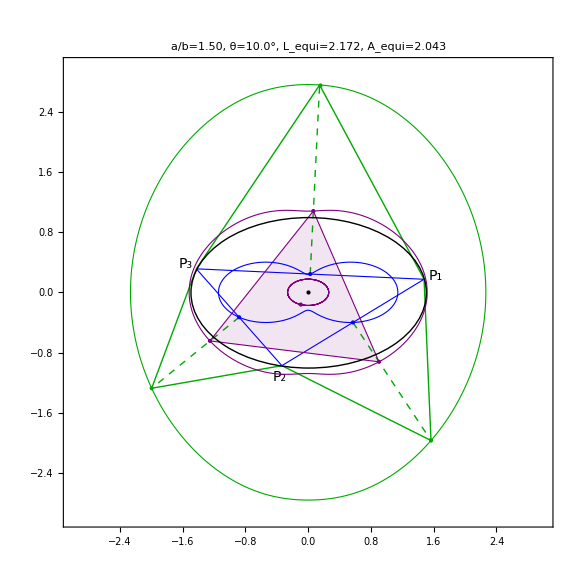

```mathematica
Module[{a=1.5,ell,ons,gr,napPts,tDeg=10.},
ell=plotEll[a,{Black,Thick}];
napPts=Table[getOuterNapoleonSummits[a,toRad@tDeg0],{tDeg0,0,359,.5}];
makeOneNapoleonFrame[a,ell,napPts,tDeg]]
```

```mathematica
(*DeleteFile[napApp];*)
```

```mathematica
(*napApp=CloudDeploy[%,"napoleon summits v1",Permissions->"Public"]*)
```

#### Outer locus is *not* elliptic

```mathematica
Module[{a=2.,napPts,outerEllPars,centroidEllPars,summitLocus,centroidLocus},
napPts=Table[getOuterNapoleonSummits[a,toRad@tDeg0],{tDeg0,0,359,1}];
summitLocus=First[#@"summits"]&/@napPts;
centroidLocus=#["centroid"]&/@napPts;
centroidEllPars=findEllParams[a,1,centroidLocus,"centroid"];
outerEllPars=findEllParams[a,1,summitLocus,"outer"];
<|"centroidEllErr"->centroidEllPars["err"],"outerEllErr"->outerEllPars["err"]|>]
```

<|centroidEllErr→1.37509×10^-13,outerEllErr→0.268304|>

## Circumbilliard (using linear algebra)

```mathematica
ellExtremum[{mx_,my_},{vx_,vy_},{c1_,c2_,c3_,c4_,c5_},t_]=Module[{xt,yt},
xt=mx+t vx;
yt=my+t vy;
Collect[1+c1 xt+c2 yt+c3 xt yt+c4 xt^2+c5 yt^2,t]]
```

1+c1 mx+c4 mx^2+c2 my+c3 mx my+c5 my^2+t (c1 vx+2 c4 mx vx+c3 my vx+c2 vy+c3 mx vy+2 c5 my vy)+t^2 (c4 vx^2+c3 vx vy+c5 vy^2)

```mathematica
(* by symmetry, b=0 of the quadratic*)
Clear@ellExtremumSym;
ellExtremumSym[{mx_,my_},{vx_,vy_},{c1_,c2_,c3_,c4_,c5_}]:=Module[{a,c,d,sqrtd,sol},
a=c4 vx^2+c3 vx vy+c5 vy^2;
(* b=c1 vx+2 c4 mx vx+c3 my vx+c2 vy+c3 mx vy+2 c5 my vy; *)
c=1+c1 mx+c4 mx^2+c2 my+c3 mx my+c5 my^2;
(*(-b + sqrt(b2-4ac)/(2a)) => sqrt(-4ac)/(2a) => sqrt(-ac)/a*)  
sol=Sqrt[-c/a];(*Sqrt[-a*c]/a;*)(* sqrt(-a)*sqrt(c)/a => sqrt(c/a) *)
{sol,-sol}];
```

```mathematica
(* grad = { c1 + c3 y + 2 c4 x, c2 + c3 x + 2 c5 y *)
Clear@circumTangent;circumTangent[{c1_,c2_,c3_,c4_,c5_},{x_,y_}]:=Module[{grad,tang},
grad={c1+c3 y+2c4 x,c2+c3 x+2c5 y};
tang=perp@grad;
tang];
```

```mathematica
Clear@getHessianDet;
getHessianDet[tri_,ctr_]:=Module[{mtx123,mtx45,mtx,rhs,ls,hess},
(* c1 x + c2 y + c3 x y + c4 x^2 + c5 y^2 == -1 *)
(* grad = { c1 + c3 y + 2 c4 x, c2 + c3 x + 2 c5 y *)
mtx123={#[[1]],#[[2]],#[[1]]*#[[2]],#[[1]]^2,#[[2]]^2}&/@tri;
mtx45={
{1,0,ctr[[2]],2ctr[[1]],0},
{0,1,ctr[[1]],0,2ctr[[2]]}};
mtx=Join[mtx123,mtx45];
rhs={-1,-1,-1,0,0};
ls=LinearSolve[mtx,rhs];
hess={{2ls[[4]],ls[[3]]},{ls[[3]],2ls[[5]]}};
Det[hess]];
```

```mathematica
Clear@getCircumAny;
getCircumAny[orbit_,ctr_]:=Module[{mtx123,mtx45,mtx,rhs,ls,hess,vals,vects,lengths,lgt1,lgt2,vertices,valsMinMax,orbitTangents,area,major,minor,c,fs},
(* c1 x + c2 y + c3 x y + c4 x^2 + c5 y^2 == -1 *)
(* grad = { c1 + c3 y + 2 c4 x, c2 + c3 x + 2 c5 y *)
mtx123={#[[1]],#[[2]],#[[1]]*#[[2]],#[[1]]^2,#[[2]]^2}&/@orbit;
mtx45={
{1,0,ctr[[2]],2ctr[[1]],0},
{0,1,ctr[[1]],0,2ctr[[2]]}};
mtx=Join[mtx123,mtx45];
rhs={-1,-1,-1,0,0};
ls=LinearSolve[mtx,rhs];
hess={{2ls[[4]],ls[[3]]},{ls[[3]],2ls[[5]]}};
{vals,vects}=Eigensystem@hess;
lgt1=Abs[First@ellExtremumSym[ctr,vects[[1]],ls]];
lgt2=lgt1*Sqrt[vals[[1]]/vals[[2]]];
lengths={lgt1,lgt2};
valsMinMax=If[Abs@vals[[1]]<Abs@vals[[2]],{vals[[1]],vals[[2]]},{vals[[2]],vals[[1]]}];
major=If[Abs@vals[[1]]<Abs@vals[[2]],vects[[1]],vects[[2]]];
minor=If[Abs@vals[[1]]<Abs@vals[[2]],vects[[2]],vects[[1]]];
c=Sqrt[Abs[lgt2^2-lgt1^2]];
fs={ctr+Sign[valsMinMax[[1]]]major c,ctr-Sign[valsMinMax[[1]]]major c};
orbitTangents=circumTangent[ls,#]&/@orbit;
vertices=MapThread[(ctr+#1*#2)&,{lengths,vects}];
area=π*lengths[[1]]*lengths[[2]];
<|"ctr"->ctr,"coeffs"->Chop@ls,"vals"->Chop@vals,"valsMinMax"->valsMinMax,"axes"->Chop@vects,"major"->major,"minor"->minor,"minorVal"->valsMinMax[[1]],"majorVal"->valsMinMax[[2]],"lengths"->lengths,"ratio"->safeDiv[lgt1,lgt2],"prod"->lgt1*lgt2,"vertices"->Chop@vertices,"foci"->fs,"c"->c,
"orbit"->orbit,"orbitTangents"->orbitTangents,"area"->area|>];
```

```mathematica
-Graphics-
-Graphics-
```

```mathematica
Clear@getEll5ctr;
getEll5ctr[ctrs5_]:=Module[{mtx,rhs,ls,discr,x0,y0},
(* A x^2 + B x y + C y^2 + D x + E y == -1 *)
mtx={#[[1]]^2,#[[1]]*#[[2]],#[[2]]^2,#[[1]],#[[2]]}&/@ctrs5;
rhs={-1,-1,-1,-1,-1};
ls=LinearSolve[mtx,rhs];
discr=ls[[2]]^2-4ls[[1]]ls[[3]];
x0=(2*ls[[3]]*ls[[4]]-ls[[2]]ls[[5]])/discr;
y0=(2*ls[[1]]*ls[[5]]-ls[[2]]ls[[4]])/discr;
{x0,y0}];
```

```mathematica
Module[{a=1.5,ps},
ps=Table[N@{a Cos[t]+5,Sin[t]+7},{t,0,2π,2π/7}];
getEll5ctr[Take[ps,5]]]
```

{5.,7.}

```mathematica
Clear@getCircumMit;
getCircumMit[orbit_]:=Module[{ctr},
ctr=getMittenTrilin[orbit,triLengthsRL@orbit];
getCircumAny[orbit,ctr]];
(* Steiner Circumellipse *)
Clear@getCircumBar;getCircumBar[orbit_]:=getCircumAny[orbit,getBaricenter@@orbit];
```

```mathematica
getCircumMit[orbitNormals[1.5,π/3.][[1]]]
```

<|ctr→{0.,-6.24567×10^-16},coeffs→{0,0,0,-0.444444,-1.},vals→{-2.,-0.888889},valsMinMax→{-0.888889,-2.},axes→{{0,1.},{-1.,0}},major→{-1.,-4.91566×10^-16},minor→{-4.91566×10^-16,1.},minorVal→-0.888889,majorVal→-2.,lengths→{1.,1.5},ratio→0.666667,prod→1.5,vertices→{{0,1.},{-1.5,0}},foci→{{1.11803,-7.49793×10^-17},{-1.11803,-1.17415×10^-15}},c→1.11803,orbit→{{0.75,0.866025},{1.34925,-0.436921},{-1.49317,-0.0953041}},orbitTangents→{{1.73205,-0.666667},{-0.873842,-1.19933},{-0.190608,1.32726}},area→4.71239|>

```mathematica
(* {ctrLab->"*",drTri->False,drOrbitTangents->False,ps->-Graphics-,drVertices->False,drLgl->0.2,labClr->-Graphics-,labPos->{-1.25,-1.25},labSize->20} *)
```

```mathematica
Clear@drawCircumAnyLow;
Options@drawCircumAnyLow={ctrLab->"*",drAxes->True,drTri->False,drOrbitTangents->False,ps->Black,drVertices->False,drFoci->False,drLgl->.2,labClr->Darker@Red,labPos->{-1.25,-1.25},labSize->20};
drawCircumAnyLow[cII_,tri_,OptionsPattern[]]:=Module[{o,vl,v,ul,u,pp,ax1,ax2,gr,grTri,grGrads,ps2},
o=cII["ctr"];
vl=cII["lengths"][[1]];
v=cII["axes"][[1]];
ul=cII["lengths"][[2]];
u=cII["axes"][[2]];
pp=ParametricPlot[o+vl Cos[t]v+ul Sin[t] u,{t,0,2π},PlotStyle->OptionValue@ps];
ax1=Graphics[{Dashed,OptionValue@ps,Line@{o-vl v,o+vl v}}];
(*ParametricPlot[(o+vl v)t+(o-vl v)(1-t),{t,0,1},PlotStyle->{Dashed,OptionValue@ps}];*)
ax2=Graphics[{Dashed,OptionValue@ps,Line@{o-ul u,o+ul u}}];(*ParametricPlot[(o+ul u)t+(o-ul u)(1-t),{t,0,1},PlotStyle->{Dashed,OptionValue@ps}];*)
grTri=If[OptionValue@drTri,{FaceForm@{OptionValue@ps,Opacity@.1},EdgeForm@OptionValue@ps,EdgeForm@{Thick,Blue},Polygon@tri},{}];
grGrads=If[OptionValue@drOrbitTangents,{Arrowheads@Medium,OptionValue@ps,MapThread[Arrow@{#1,#2}&,{cII["orbit"],cII["orbit"]+.5norm/@cII["orbitTangents"]}]},{}];
ps2=OptionValue@ps;
gr={
If[OptionValue@drVertices,{PointSize@Large,Black,Point@tri,ellLabelPoints[1,tri,"P",16,OptionValue@drLgl]},{}],
If[ListQ@ps2,Sequence@@ps2,ps2],
If[OptionValue@drFoci,{Directive[OptionValue@ps],PointSize@Medium,Point@cII["foci"]},{}],
{PointSize@Large,OptionValue@labClr,Point@o,Text[Style[OptionValue@ctrLab,OptionValue@labSize],o,OptionValue@labPos]}
};
Show[{If[OptionValue@drAxes,{ax1,ax2},{}],pp,Graphics/@{grTri,gr,grGrads}}]];
```

```mathematica
Clear@drawCircumAny;
Options@drawCircumAny=Options@drawCircumAnyLow;
drawCircumAny[tri_,ctr_,opts:OptionsPattern[]]:=drawCircumAnyLow[getCircumAny[tri,ctr],tri,{opts}];
```

```mathematica
Clear@drawCircumMit;
Options@drawCircumMit=Options@drawCircumAnyLow;drawCircumMit[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getMittenTrilin[tri,triLengthsRL@tri],{opts}];
(* Steiner Circumellipse *)
Clear@drawCircumBar;
Options@drawCircumBar=Options@drawCircumAnyLow;
drawCircumBar[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getBaricenter@@tri,{opts}];
```

```mathematica
Clear@drawSteinerInellipse;
drawSteinerInellipse[tri_,opts:OptionsPattern[]]:=Module[{meds},
meds=getMedians@@tri;
drawCircumAny[meds,getBaricenter@@tri,{opts}]
];
Clear@drawCircumExc;drawCircumExc[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getMittenTrilin[tri,triLengthsRL@tri],{opts}];
Clear@drawCircumInc;drawCircumInc[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getIncenterTrilin[tri,triLengthsRL@tri],{opts}];
```

## Conic Coeffs

```mathematica
(* A x^2 + B x y + C y^2 + D x + E y + F = 0 *) 
(* axx x^2 + 2 axy x y + ayy y^2 + 2 bx x + 2by y + C = 0 *) 

(* A=axx, B=2 axy, C = ayy, D = 2 bx,E = 2 by *)
```

```mathematica
Clear@getConicCoeffs;
getConicCoeffs[fivePs_]:=Module[{mtx,rhs,coeffs,det,isHyp,hess,evals,evecs,majorAxis,S,a,b,ctr,c2,c,foci,errs,err2sum},
mtx={
(* A *) #[[1]]^2,
(* B *)#[[1]]*#[[2]],
(* C *) #[[2]]^2,
(* D *) #[[1]],
(* E *)#[[2]]
}&/@fivePs;
(*Print["m=",MatrixForm@mtx,"; det=",Det[mtx]];*)
rhs=ConstantArray[-1,5];
coeffs=LinearSolve[mtx,rhs];
errs=Chop[(coeffs[[1]]#[[1]]^2+
coeffs[[2]]#[[1]]#[[2]]+
coeffs[[3]]#[[2]]^2+
coeffs[[4]]#[[1]]+
coeffs[[5]]#[[2]]+1)&/@fivePs];
err2sum=Total[errs^2];
det=coeffs[[1]]*coeffs[[3]]-coeffs[[2]]coeffs[[2]]/4;
isHyp=det<0;
(* xc=-(bx*ayy-axy*by)/det;
yc=-(axx*by-axy*bx)/det; *)
ctr={2 coeffs[[3]]coeffs[[4]]-coeffs[[2]]coeffs[[5]],2 coeffs[[1]]coeffs[[5]]-coeffs[[2]]coeffs[[4]]}/(-4 det);

hess={{coeffs[[1]],coeffs[[2]]/2},{coeffs[[2]]/2,coeffs[[3]]}};
{evals,evecs}=Eigensystem@hess;
majorAxis=If[evals[[1]]<evals[[2]],evecs[[1]],evecs[[2]]];
(* axx * ayy - axy^2 *)
(* it will be zero if hyp wrt tr *)
S=Det[{
{coeffs[[1]],coeffs[[2]]/2,coeffs[[4]]/2},
{coeffs[[2]]/2,coeffs[[3]],coeffs[[5]]/2},
{coeffs[[4]]/2,coeffs[[5]]/2,1}}];
a=Sqrt@Abs[S/(Min[evals[[1]],evals[[2]]]det)];
b=Sqrt@Abs[S/(Max[evals[[1]],evals[[2]]]det)];

c2=If[isHyp,a^2+b^2,a^2-b^2];
c=Sqrt@c2;
foci={ctr+c majorAxis,ctr-c majorAxis };
<|"fivePs"->fivePs,"discr"->S,"det"->det,"isHyp"->isHyp,
"ctr"->ctr,"foci"->foci,"a"->a,"b"->b,"c"->c,"c2"->c2,"coeffs"->coeffs,"majorAxis"->majorAxis,"errs"->errs,"err2sum"->err2sum|>];
```

```mathematica
(* https://en.wikipedia.org/wiki/Hyperbola *)
(* axx x^2 + 2 axy x y + ayy y^2 + 2 bx x + 2by y + C = 0 *) 
Clear@getConicCoeffsOld;
getConicCoeffsOld[fivePs_]:=Module[{mtx,rhs,axx,ayy,axy,bx,by,discr,det,xc,yc,ctr,a,b,c,r1,r2,l1,l2,c2,hess,eigenvals,eigenvecs,majorAxis,foci},
mtx={
(* axx *) #[[1]]^2,
(* ayy *) #[[2]]^2,
(* 2 axy *) 2#[[1]]*#[[2]],
(* 2 bx *) 2#[[1]],
(* 2 by *) 2#[[2]]
}&/@fivePs;
(*Print["m=",MatrixForm@mtx,"; det=",Det[mtx]];*)
rhs=ConstantArray[-1,5];
{axx,ayy,axy,bx,by}=LinearSolve[mtx,rhs];
discr=Det[{
{axx,axy,bx},
{axy,ayy,by},
{bx,by,1}}];
det=axx*ayy-axy^2;
hess={{axx,axy},{axy,ayy}};
{eigenvals,eigenvecs}=Eigensystem@hess;
majorAxis=If[eigenvals[[1]]<eigenvals[[2]],eigenvecs[[1]],eigenvecs[[2]]];
(* axx * ayy - axy^2 *)
(* it will be zero if hyp wrt tr *)
xc=-(bx*ayy-axy*by)/det;
yc=-(axx*by-axy*bx)/det;
ctr={xc,yc};
(*tan2phi=(2axy)/(axx-ayy);*)
(*sin2phi=axy;
cos2phi=(axx-ayy)/2;
phi=ArcTan[cos2phi,sin2phi]/2;*)
(* ronaldo: considerar quadrante do par ordenado (c2p,s2p) *)
(* (c,s) = coseno e seno do angulo normal *)
(*  Q1:c>0,s>0; Q2:c>0,s>0; Q3:c<0,s>0; Q4:c<0,s>0 *)
(* ou seja, seno sempre positivo, coseno negativo se em Q2 ou Q3, i.e., cos2phi < 0 *)
{r1,r2}=quadRootsUnprot[1,-axx-ayy,det];
(* ronaldo: trocar a por b *)
l1=Min[Abs/@{r1,r2}];
l2=Max[Abs/@{r1,r2}];
(*{l1,l2}=quadRootsUnprot[1,-axx-ayy,det];*)
a=Sqrt@Abs[discr/(l1 det)];
b=Sqrt@Abs[discr/(l2 det)];
c2=If[det<0,a^2+b^2,a^2-b^2];
c=Sqrt@c2;
foci={ctr+c majorAxis,ctr-c majorAxis };
<|"fivePs"->fivePs,"discr"->discr,"det"->det,"isHyp"->(det<0),
"ctr"->ctr,"foci"->foci,"l1"->l1,"l2"->l2,"a"->a,"b"->b,"c"->c,"c2"->c2,"coeffs"->{axx,ayy,axy,bx,by},"majorAxis"->majorAxis|>];
```

```mathematica
Clear@drawConic;
Options@drawConic={ctrLab->"",ps->Directive[Thick,Darker@Red],lgt->.1,showFoci->False,psAxes->Directive[Dashed,Black],maxX->2,maxY->2};
drawConic[conic_,OptionsPattern[]]:=Module[{o,a,v,b,u,ctr,fs,pp,ax,gr,foci,maxT=π,cp,sp,ell},
o=conic["ctr"];
a=conic["a"];
b=conic["b"];
(* major axis *)
v=conic["majorAxis"];
u=perp@v;
foci=conic["foci"];
{pp,ax}=If[conic["isHyp"],
{ParametricPlot[{o+a Cosh[t]v+b Sinh[t] u,o-a Cosh[t]v-b Sinh[t] u},{t,-maxT,maxT},PlotStyle->OptionValue@ps],Graphics[{OptionValue@psAxes,Line@{o-OptionValue@maxX(v+u (b/a)),o+OptionValue@maxX(v+u (b/a))},Line@{o-OptionValue@maxY(v-u (b/a)),o+OptionValue@maxY(v-u (b/a))}}]},
{ParametricPlot[o+a v Cos@t+b u Sin@t,{t,0,2π},PlotStyle->OptionValue@ps],
Graphics[{OptionValue@psAxes,Line@{o-a v,o+a v},Line@{o-b u,o+b u}}]}];
fs=Graphics@If[OptionValue@showFoci,{PointSize@Medium,First@Cases[OptionValue@ps,_RGBColor],Point@foci,Thick,Line@foci,Text[Style["f",20],#,{0,-1}]&/@foci},{}];
gr=Graphics[{First@Cases[OptionValue@ps,_RGBColor],PointSize@Large,Point@o,If[OptionValue@ctrLab!="",ellLabelTxt[conic["ellA"],o,Style[OptionValue@ctrLab,20],OptionValue@lgt],{}]}];
Show[{fs,ax,pp,gr}]];
```

```mathematica
Clear@x;Clear@y;
```

```mathematica
Clear@drawConicImplicit;
Options@drawConicImplicit={ctrLab->"",ps->Directive[Thick,Darker@Red],lgt->.1,showFoci->False,psAxes->Directive[Dashed,Black],maxX->2,maxY->2};
drawConicImplicit[conic_,OptionsPattern[]]:=Module[{coeffs,cp,gr},
coeffs=conic["coeffs"];
gr=Graphics[{PointSize@Large,OptionValue@ps,Point@conic["ctr"]}];
cp=ContourPlot[coeffs[[1]]x^2+coeffs[[2]]x y +coeffs[[3]]y^2+coeffs[[4]]x+coeffs[[5]]y+1==0,{x,-OptionValue@maxX,OptionValue@maxX},{y,-OptionValue@maxY,OptionValue@maxY},ContourStyle->OptionValue@ps];
Show[{cp,gr}]];
```

## Five Point Hyperbola, Feuerbach, and Excentral Jerabek

```mathematica
(* https://en.wikipedia.org/wiki/Hyperbola *)
(* axx x^2 + 2 axy x y + ayy y^2 + 2 bx x + 2by y + C = 0 *) Clear@getHypCoeffs5b;
Clear@getHypCoeffs5b;
getHypCoeffs5b[fivePs_,tr_]:=Module[{mtx,rhs,axx,ayy,axy,bx,by,discr,det,xc,yc,ctr,a,b,c,l1,l2,c2,hess,eigenvals,eigenvecs,majorAxis,foci,fiveErrs},
mtx={
(* axx *) #[[1]]^2,
(* ayy *) #[[2]]^2,
(* 2 axy *) 2#[[1]]*#[[2]],
(* 2 bx *) 2#[[1]],
(* 2 by *) 2#[[2]]
}&/@((#-tr)&/@fivePs);(* trick to remove ill-conditioning on origin-centered conics *)
(*Print["m=",MatrixForm@mtx,"; det=",Det[mtx]];*)
rhs=ConstantArray[-1,5];
{axx,ayy,axy,bx,by}=LinearSolve[mtx,rhs];
fiveErrs=(axx #[[1]]^2 + 2 axy #[[1]]#[[2]] + ayy #[[2]]^2 + 2 bx #[[1]] + 2by #[[2]]+1)&/@((#-tr)&/@fivePs);
hess={{axx,axy},{axy,ayy}};
{eigenvals,eigenvecs}=Eigensystem@hess;
majorAxis=If[eigenvals[[1]]<eigenvals[[2]],eigenvecs[[1]],eigenvecs[[2]]];
(* axx * ayy - axy^2 *)
discr=Det[{
{axx,axy,bx},
{axy,ayy,by},
{bx,by,1}}];
det=axx*ayy-axy^2;
(* it will be zero if hyp wrt tr *)
xc=-(bx*ayy-axy*by)/det;
yc=-(axx*by-axy*bx)/det;
ctr={xc,yc}+tr;
(*tan2phi=(2axy)/(axx-ayy);*)
(*sin2phi=axy;
cos2phi=(axx-ayy)/2;
phi=ArcTan[cos2phi,sin2phi]/2;*)
{l1,l2}=quadRootsUnprot[1,-axx-ayy,det];
a=Sqrt@Abs[-discr/(l1 det)];
b=Sqrt@Abs[-discr/(l2 det)];
c2=a^2+b^2;
c=Sqrt@c2;
foci={ctr+c majorAxis,ctr-c majorAxis };
<|"fivePs"->fivePs,"fiveErrs"->fiveErrs,"discr"->discr,"det"->det,"isHyp"->(det<0),
"ctr"->ctr,"foci"->foci,"l1"->l1,"l2"->l2,"a"->a,"b"->b,"c"->c,"c2"->c2,"coeffs"->{axx,ayy,axy,bx,by},"majorAxis"->majorAxis|>];
```

```mathematica
(* https://en.wikipedia.org/wiki/Hyperbola *)
(* axx x^2 + 2 axy x y + ayy y^2 + 2 bx x + 2by y + C = 0 *)
```

```mathematica
Clear@d;
Module[{l,d,h},
d=getDelta[a,1];
l=(a^2/(a^2-1)) Sqrt[2d-a^2-1];
h=(a^2+d+1)/(a^2+d);
Solve[h/l==Sqrt[3]/3,a,Reals]]
```

{{a→-√(-3+4 √3)},{a→√(-3+4 √3)}}

```mathematica
Clear@getHypCoeffs5bNoTr;
getHypCoeffs5bNoTr[fivePs_]:=Module[{randCtr,mtx,rhs,axx,ayy,axy,bx,by,fiveErrs,discr,det,xc,yc,ctr,hess,eigenvals,eigenvecs,majorAxis,
l1,l2,a,b,c2,c,r1,r2,foci},
randCtr=RandomReal[{-1,1},2];
mtx={
(* axx *) #[[1]]^2,
(* ayy *) #[[2]]^2,
(* 2 axy *) 2#[[1]]*#[[2]],
(* 2 bx *) 2#[[1]],
(* 2 by *) 2#[[2]]
}&/@((#-randCtr)&/@fivePs);
(* trick to remove ill conditioning on origin-centered *)
(*Print["m=",MatrixForm@mtx,"; det=",Det[mtx]];*)
rhs=ConstantArray[-1,5];
{axx,ayy,axy,bx,by}=LinearSolve[mtx,rhs];
fiveErrs=(axx #[[1]]^2 + 2 axy #[[1]]#[[2]] + ayy #[[2]]^2 + 2 bx #[[1]] + 2by #[[2]]+1)&/@fivePs;
(* axx * ayy - axy^2 *)
discr=Det[{
{axx,axy,bx},
{axy,ayy,by},
{bx,by,1}}];
det=axx*ayy-axy^2;
(* restores to center *)
xc=-(bx*ayy-axy*by)/det;
yc=-(axx*by-axy*bx)/det;
(* add random center back *)
ctr={xc,yc}+randCtr;
hess={{axx,axy},{axy,ayy}};
{eigenvals,eigenvecs}=Eigensystem@hess;
majorAxis=If[eigenvals[[1]]<eigenvals[[2]],eigenvecs[[1]],eigenvecs[[2]]];
(* ronaldo: considerar quadrante do par ordenado (c2p,s2p) *)
(* (c,s) = coseno e seno do angulo normal *)
(*  Q1:c>0,s>0; Q2:c>0,s>0; Q3:c<0,s>0; Q4:c<0,s>0 *)
(* ou seja, seno sempre positivo, coseno negativo se em Q2 ou Q3, i.e., cos2phi < 0 *)
{r1,r2}=quadRootsUnprot[1,-axx-ayy,det];
(* ronaldo: trocar a por b *)
l1=Min[Abs/@{r1,r2}];
l2=Max[Abs/@{r1,r2}];
a=Sqrt@Abs[-discr/(l1 det)];
b=Sqrt@Abs[-discr/(l2 det)];
c2=a^2+b^2;
c=Sqrt@c2;
foci={ctr+c majorAxis,ctr-c majorAxis};
<|"fivePs"->fivePs,"fiveErrs"->fiveErrs,"discr"->discr,"det"->det,"isHyp"->(det<0),
"ctr"->ctr,"foci"->foci,"l1"->l1,"l2"->l2,"a"->a,"b"->b,"c"->c,"c2"->c2,"coeffs"->{axx,ayy,axy,bx,by},"eigenvals"->eigenvals,"eigenvecs"->eigenvecs,"majorAxis"->majorAxis|>];
```

```mathematica
Clear@drawHyp5b;
Options@drawHyp5b={ctrLab->"",ps->{Darker@Red},lgt->.1,showFoci->False,psAxes->Directive[Dashed,Black],fntSize->16};
drawHyp5b[hyp5_,OptionsPattern[]]:=Module[{o,a,v,b,u,ctr,fs,pp1,pp2,ax1,ax2,gr,foci,maxAsymptT=3,maxT=π,cp,sp},
o=hyp5["ctr"];
a=hyp5["a"];
b=hyp5["b"];
(* major axis *)
v=hyp5["majorAxis"];
u=perp@v;
foci=hyp5["foci"];
pp1=ParametricPlot[o+a Cosh[t]v+b Sinh[t] u,{t,-maxT,maxT},PlotStyle->OptionValue@ps];
pp2=ParametricPlot[o-a Cosh[t]v-b Sinh[t] u,{t,-maxT,maxT},PlotStyle->OptionValue@ps];
(* axes could be lines Line@{} *)
(*ax1=ParametricPlot[o+v t+u (b/a)t,{t,-maxAsymptT,maxAsymptT},PlotStyle->{Dashed,OptionValue@psAxes}];
ax2=ParametricPlot[o+v t-u (b/a)t,{t,-maxAsymptT,maxAsymptT},PlotStyle->{Dashed,OptionValue@psAxes}];*)
ax1=Graphics[{OptionValue@psAxes,Line@{o-maxAsymptT(v+u (b/a)),o+maxAsymptT(v+u (b/a))}}];
ax2=Graphics[{OptionValue@psAxes,Line@{o-maxAsymptT(v-u (b/a)),o+maxAsymptT(v-u (b/a))}}];
fs=Graphics@If[OptionValue@showFoci,{PointSize@Medium,First@Cases[OptionValue@ps,_RGBColor],Point@foci,Thick,Line@foci,Text[Style["F",OptionValue@fntSize],#,{0,-1}]&/@foci},{}];
gr=Graphics[{First@Cases[OptionValue@ps,_RGBColor],PointSize@Large,Point@o,If[OptionValue@ctrLab!="",ellLabelTxt[hyp5["ellA"],o,Style[OptionValue@ctrLab,20],OptionValue@lgt],{}]}];
Show[{fs,pp1,pp2,ax1,ax2,gr}]];
```

https://mathworld.wolfram.com/JerabekHyperbola.html
Jerabek Hyp goes thru:
3, 4 , 6 , 54, 64, 65, 66, 67, 68, 69, 70, 71, 72, 73, 74, 248, 265, 290, 695, 879, 895, 1173, 1175, 1176, 1177, 1242, 1243, 1244, 1245, 1246, 1439, 1798, 1903, 1942, 1987, 2213, 2435, 2574, 2575, 2992, 2993.

```mathematica
Clear@getJerabekHyp;
getJerabekHyp[tri_,sides_]:=Module[{fivePs,hyp5,ctr},
fivePs={Sequence@@tri,getOrthocenterTrilin[tri,sides],getSymmedianTrilin[tri,sides]};
ctr=getX125Trilin[tri,sides];
(* displace origin to avoid ill-conditioning, since mit=0 *)
(* ronaldo: quando ela passa pela origem, constant term -> 0 *)
hyp5=getHypCoeffs5b[fivePs,ctr]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->tri,"sides"->sides,"ctr"->ctr,"ellA"->0,
"labels"->{"P_1","P_2","P_3","X_4","X_6"},
"ctrLabel"->"X_125",
"colors"->({"orbit","orbit","orbit","ort","sym"}/.ptClrs)|>]
];
```

```mathematica
Clear@getFeuerbachHyp;
getFeuerbachHyp[tri_,sides_]:=Module[{fivePs,hyp5,ctr},
fivePs={Sequence@@tri,getIncenterTrilin[tri,sides],getOrthocenterTrilin[tri,sides]};
ctr=getFeuerbachTrilin[tri,sides];
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,ctr]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->tri,"sides"->sides,"ctr"->ctr,"ellA"->0,
"labels"->{"P_1","P_2","P_3","X_1","X_4"},
"ctrLabel"->"X_11",
"colors"->({"orbit","orbit","orbit","ort","sym"}/.ptClrs)|>]
];
```

```mathematica
Clear@getFeuerbachHypMitten;
getFeuerbachHypMitten[tri_,sides_]:=Module[{fivePs,hyp5,ctr},
fivePs={Sequence@@tri,getIncenterTrilin[tri,sides],getMittenTrilin[tri,sides]};
ctr=getFeuerbachTrilin[tri,sides];
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,ctr]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->tri,"sides"->sides,"ctr"->ctr,"ellA"->0,
"labels"->{"P_1","P_2","P_3","X_1","X_9"},
"ctrLabel"->"X_11",
"colors"->({"orbit","orbit","orbit","ort","sym"}/.ptClrs)|>]
];
```

```mathematica
Clear@getJerabekHypExc;
getJerabekHypExc[tri_,sides_]:=Module[{exc,excSides},
exc=excentralTriangle[tri,sides];
excSides=triLengthsRL@exc;
getJerabekHyp[exc,excSides]];
```

```mathematica
Clear@getHypX100;
getHypX100[a_,tDeg_]:=Module[{o,n,s,exc,inc,mit,x100,fivePs,hyp5},
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
inc=getIncenterTrilin[o,s];
mit=getMittenTrilin[o,s];
x100=getX100Trilin[o,s];
fivePs={inc,Sequence@@exc,mit};
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,x100]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->o,"sides"->s,"ctr"->x100,"ellA"->a,
"labels"->{"X_1","E_12","E_23","E_31","X_9"},
"ctrLabel"->"X_100",
"colors"->({"inc","inc","inc","inc","mit"}/.ptClrs)|>]
];
```

```mathematica
Clear@getHypFeuerbach;
getHypFeuerbach[a_,tDeg_]:=Module[{o,n,s,inc,ort,feu,fivePs,hyp5},
{o,n,s}=orbitNormals[a,toRad@tDeg];
inc=getIncenterTrilin[o,s];
ort=getOrthocenterTrilin[o,s];
feu=getFeuerbachTrilin[o,s];
fivePs={Sequence@@o,inc,ort};
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,feu]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->o,"sides"->s,"ctr"->feu,"ellA"->a,
"labels"->{"","","","X_1","X_4"},
"ctrLabel"->"X_11",
"colors"->({"ell","ell","ell","inc","ort"}/.ptClrs)|>]
];
```

## CB pictures

```mathematica
DynamicModule[{tri,act},
Manipulate[
tri={P1,P2,P3};
act=If[showAnticompl,anticomplementaryTriangle[tri,triLengthsRL@tri],{}];
Show[{
drawCircumMit[tri,drTri->True,ctrLab->"M",drOrbitTangents->drOrbitTangents0,drFoci->True],
If[showSteiner,drawCircumBar[tri,ctrLab->"G",ps->Darker@Pink,drOrbitTangents->drOrbitTangents0],{}],
If[showInc,drawCircumInc[tri,ctrLab->"I",ps->Darker@Green,drOrbitTangents->drOrbitTangents0],{}],
If[showAnticompl,drawCircumMit[act,drTri->True,ctrLab->"X_7",ps->Blue,drOrbitTangents->drOrbitTangents0],{}],
If[showSteinerInell,drawSteinerInellipse[tri,drTri->True,ctrLab->"G",ps->Purple,drOrbitTangents->drOrbitTangents0],{}]
},PlotLabel->(Style["Circumbilliard of N=3 Orbit and\nits Anticomplementary Triangle",{Black,Medium}]),
Frame->True,ImageSize->Large,GridLines->Automatic,PlotRange->{{-2,3},{-2,3}}],
{{P1,{0.0,0.001}},Locator},
{{P2,{1,0}},Locator},
{{P3,{1.5,1.5}},Locator},
{{showInc,False,"incenter circumell"},{True,False}},
{{showSteiner,False,"steiner circumell"},{True,False}},
{{showSteinerInell,False,"steiner inellipse"},{True,False}},
{{showAnticompl,False,"anticomplementary"},{True,False}},
{{drOrbitTangents0,False,"orbit tangents"},{True,False}}
]]
```

```mathematica
(*DeleteFile[circumApp]*)
```

```mathematica
(*circumApp=CloudDeploy[%,"circumbilliard and anticomplementary",Permissions->"Public"]*)
```

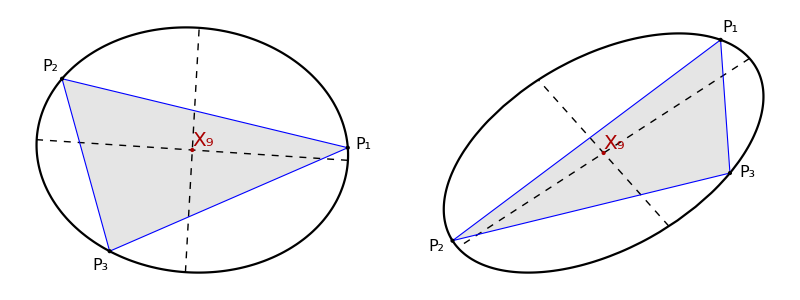

```mathematica
circumPlot=
Grid[{Show[#,Axes->False,PlotRange->All,ImageSize->400]&/@{drawCircumMit[{{3,.5},{-1.5,1.5},{-.75,-1}},drTri->True,ctrLab->"X_9",drVertices->True,drLgl->.25],
drawCircumMit[rot[#,toRad@30]&/@{{5,2.5},{-5,.5},{3,-1.5}},drTri->True,ctrLab->"X_9",drVertices->True,drLgl->.5]
}},Spacings->0]
```

```mathematica
export3["0056_circumplot",circumPlot]
```

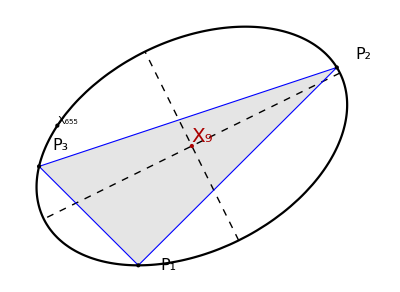

```mathematica
Module[{c,x655,vs,ls,gr},
vs={{1,0},{2,1},{.5,.5}};
ls=triLengthsRL@vs;
x655=getX655Trilin[vs,ls];
gr=Graphics[{PointSize@Large,Point@x655,Text[Style["X_655",Large],x655,{-1,-1}]}];
c=drawCircumMit[vs,drTri->True,ctrLab->"X_9",drVertices->True,drLgl->.15];
Show[{c,gr},PlotRange->All]]
```

```mathematica
DynamicModule[{ons,a=1.5,x655,ell,gr,slack=.1},
ell=plotEllAxes[a,{Thick,Black}];
Manipulate[
ons=orbitNormals[a,toRad@tDeg];
x655=getX655Trilin[ons[[1]],ons[[3]]];
gr=Graphics[{PointSize@Large,FaceForm@None,
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{Red,Point@x655,Text[Style["X_655",20],x655,{-1,-1}]}}];
Show[{ell,gr},PlotRange->{{-a-slack,a+slack},{-1-slack,1+slack}}],
{{tDeg,10.},-180,180,.1}]]
```

## Hyp Stats & Figures

```mathematica
Clear@getHyps;
getHyps[a_,tDeg_]:=Module[{hfeu,hjer},
hfeu=getHypFeuerbach[a,tDeg];
hjer=getHypX100[a,tDeg];
{hfeu,hjer}]
```

```mathematica
getHypsTab[a_,tDeg_]:=Module[{hyps,fields={"discr","det","phi","l1","l2","a","b","c","c2"}},
hyps=getHyps[a,tDeg];
Prepend[(fields/.#)&/@hyps,fields]]
```

#### Phi (axis angle) is 45° for both, as expected

```mathematica
getHypsTab[1.5,10.]//TableForm
```

discr | det | phi | l1 | l2 | a | b | c | c2
-29.9726 | -29.9726 | phi | -5.47473 | 5.47473 | 0.427385 | 0.427385 | 0.604413 | 0.365315
-0.985515 | -0.985515 | phi | -0.992731 | 0.992731 | 1.00365 | 1.00365 | 1.41938 | 2.01464

```mathematica
getHypsTab[1.5,20.]//TableForm
```

discr | det | phi | l1 | l2 | a | b | c | c2
-19.0051 | -19.0051 | phi | -4.35948 | 4.35948 | 0.478941 | 0.478941 | 0.677326 | 0.45877
-0.624897 | -0.624897 | phi | -0.790505 | 0.790505 | 1.12473 | 1.12473 | 1.59061 | 2.53003

```mathematica
Clear@getHypsRatios;
getHypsRatios[a_,tDeg_,field_]:=Module[{hyp11,hyp100,fields={"discr","det","phi","l1","l2","a","b","c"}},
{hyp11,hyp100}=getHyps[a,tDeg];
hyp11[[field]]/hyp100[[field]]]
```

#### Ratios of is constant! (though a11=b11, and a100=b100 change)

```mathematica
{(1.59061/.677326),(1.41938/.604413)}
```

{2.34837,2.34836}

```mathematica
getStats[Table[getHypsRatios[1.5,tDeg,"c"],{tDeg,1,89}]]
```

<|n→89,mean→0.425828,sd→9.54059×10^-16,z→2.24048×10^-15,min→0.425828,max→0.425828,median→0.425828,label→|>

```mathematica
getStats[Table[getHypsRatios[2.,tDeg,"c"],{tDeg,1,89}]]
```

<|n→89,mean→0.337928,sd→1.05753×10^-15,z→3.12946×10^-15,min→0.337928,max→0.337928,median→0.337928,label→|>

#### Ratios of det=axx*ayy-axy^2; seems constant!

```mathematica
getStats[Table[getHypsRatios[1.5,tDeg,"det"],{tDeg,1,89}]]
```

<|n→89,mean→30.4132,sd→2.52444×10^-13,z→8.30049×10^-15,min→30.4132,max→30.4132,median→30.4132,label→|>

```mathematica
getStats[Table[getHypsRatios[2.,tDeg,"det"],{tDeg,1,89}]]
```

<|n→89,mean→76.684,sd→9.12826×10^-13,z→1.19037×10^-14,min→76.684,max→76.684,median→76.684,label→|>

```mathematica
Clear@showHyp5vizapp;
Options@showHyp5vizapp=Options@drawHyp5b;
showHyp5vizapp[a_,tDeg_,hypFn_,opts:OptionsPattern[]]:=Module[{hyp5,gr,drHyp},
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=hypFn[a,tDeg];
gr=Graphics[{PointSize@Large,FaceForm@None,
MapThread[{#1,Point@#2,Text[Style[#3,20],#2,{-1.25,-1.25}]}&,
{hyp5["colors"],
hyp5["fivePs"],
hyp5["labels"]}]}];
drHyp=drawHyp5b[hyp5,FilterRules[{opts,ctrLab->hyp5["ctrLabel"]},Options@drawHyp5b]];
Show[{drHyp,gr}]];
```

```mathematica
(* for movie *)
Clear@showOneHyp5;
Options@showOneHyp5=Join[Options@drawHyp5b,{showExc->False,showEll->True}];
showOneHyp5[a_,tDeg_,hypFn_,opts:OptionsPattern[]]:=Module[{ell,hyp5b,grHyp5,gr,maxX=3,maxY=3,exc},
ell=plotEllAxes[a,{Thick,Black}];
hyp5b=hypFn[a,tDeg];
exc=excentralTriangle[hyp5b[["orbit"]],hyp5b[["sides"]]];
gr=Graphics[{PointSize@Large,FaceForm@None,
MapThread[{#1,Point@#2,Text[Style[#3,20],#2,{-1.25,-1.25}]}&,
{hyp5b["colors"],
hyp5b["fivePs"],
hyp5b["labels"]}],
{EdgeForm@{Thick,Blue},Polygon@hyp5b["orbit"]},
If[OptionValue@showExc,{EdgeForm@{Thick,Darker@Green},Polygon@exc,Darker@Green,Point@exc},{}]}];
grHyp5=drawHyp5b[hyp5b,FilterRules[{opts},Options@drawHyp5b]];
Show[{If[OptionValue@showEll,ell,{}],grHyp5,gr},
PlotRange->{{-maxX,maxX},{-maxY,maxY}},Frame->True,ImageSize->800]];
```

-Graphics-

```mathematica
getCausticAxes[1.5,1]
```

{1.14307,0.23795}

```mathematica
Clear@showHypsImg;
Options@showHypsImg={drMoses->True,drMosesIsot->False,thickness->.005,drCaustic->True,lgt->.2};
showHypsImg[a_,tDeg_,OptionsPattern[]]:=Module[{hypX100,feuClr=Purple,x100Clr=Orange,hypFeu,grCaustic,gr,grMoses,grMosesIsot,ons,x1156,causticAB},
hypX100=showOneHyp5[a,tDeg,getHypX100,
ps->{Thickness@OptionValue@thickness,feuClr},psAxes->Directive[Dashed,feuClr,Thick],
lgt->.2,ctrLab->"X_100",showFoci->True,showExc->True];
hypFeu=showOneHyp5[a,tDeg,getHypFeuerbach,
ps->{Thickness@OptionValue@thickness,x100Clr},psAxes->Directive[Dashed,x100Clr,Thick],
lgt->.2,ctrLab->"X_11",showFoci->True,showEll->False];
ons=orbitNormals[a,toRad@tDeg];
x1156=getX1156Trilin[ons[[1]],ons[[3]]];
causticAB=getCausticAxes[a,1];
grCaustic=If[OptionValue@drCaustic,Graphics@{Brown,Thick,Circle[{0,0},causticAB]},{}];
gr=Graphics@{PointSize@Large,x100Clr,Point@x1156,ellLabelTxt[a,x1156,Style["X_1156",{x100Clr,20}],OptionValue@lgt]};
grMoses=If[OptionValue@drMoses,
Module[{moses},
moses=getMosesCartesians[ons[[1]],ons[[3]]];
Graphics[{PointSize@Medium,Point[Third/@moses],MapThread[ellLabelTxt[a,#1,Subscript["X",#2],.1]&,{Third/@moses,First/@moses}]}]],{}];
grMosesIsot=If[OptionValue@drMosesIsot,
Module[{mosesIsot},
(* Range@carts,Second/@Rest@trils,carts,Fifth/@Rest@trils} *)
mosesIsot=getMosesIsotCartesians[ons[[1]],ons[[3]]];
Graphics[{PointSize@Medium,Point[Third/@mosesIsot],MapThread[ellLabelTxt[a,#1,Subscript["X",#2],.1]&,{Third/@mosesIsot,Second/@mosesIsot}]}]],{}];
Show[{grCaustic,hypX100,hypFeu,gr,grMoses,grMosesIsot},PlotRange->{{-3,3},{-3,3}},ImageSize->800]];
```

```mathematica
getCausticAxes[a,b]
```

{(a (-b^2+√(a^4-a^2 b^2+b^4)))/(a^2-b^2),(b (a^2-√(a^4-a^2 b^2+b^4)))/(a^2-b^2)}

```mathematica
Manipulate[
showHypsImg[a,tDeg,drMoses->drMoses0,drMosesIsot->drMosesIsot0],
{{a,1.5},1.01,3,.1,Appearance->"Labeled"},
{{tDeg,30},-360,360,.1,Appearance->"Labeled"},
{{drMoses0,False},{True,False}},
{{drMosesIsot0,False},{True,False}},ControlPlacement->Left
(* not working *)
(*,{{useSinCos0,False,"use sin/cos"},{True,False}}*)
]
```

^2

```mathematica
(*DeleteFile[hypObj]*)
```

```mathematica
(*hypObj=CloudDeploy[%,"Feuerbach and Jerabek Hyperbolae v1",Permissions->"Public"]*)
```

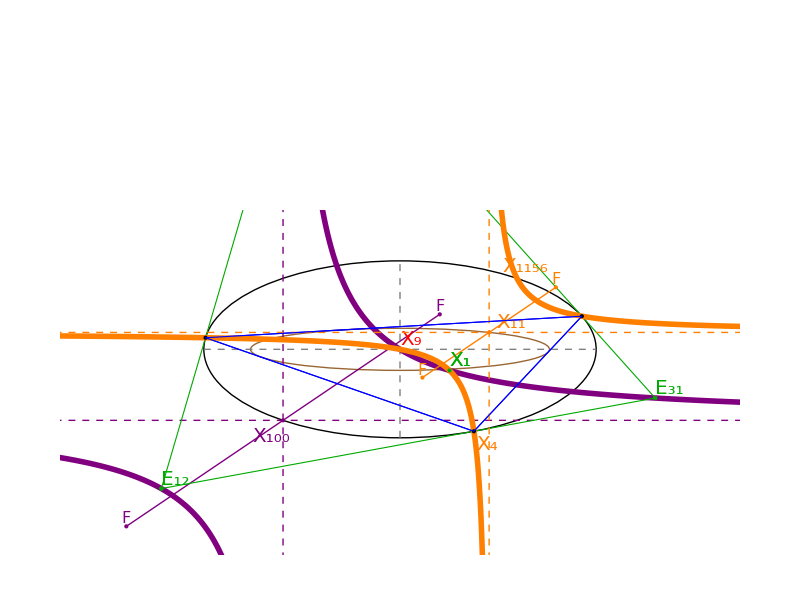

```mathematica
circumHypsPlot=Show[showHypsImg[1.5,22,drMoses->False,lgt->.15],Frame->None,PlotRange->{{-2.5,2.5},{-2.25,1.5}}]
```

```mathematica
export3["0060_circumhyps",circumHypsPlot]
```

## X6 Quartic

```mathematica
Clear@x6quarticEqn;
x6quarticEqn[x_,y_,c1_,c2_,c3_,c4_,c5_]:=c1 x^4+c2 y^4+c3 x^2 y^2+c4 x^2+c5 y^2;
```

```mathematica
x6quarticCoeffs[a_,b_]:=Module[{c1,C2,c3,c4,c5,a6,b6,delta,delta2,a2,b2,a2b2,a4,b4,c2},
a2=a a;b2=b b;a2b2=a2 b2;
c2=a2-b2;
a4=a2 a2;b4=b2 b2;
delta2=a4-a2b2+b4;
delta=Sqrt@delta2;
c1=b4 (5delta2-4c2 delta-a2b2);
C2=a4(5delta2+4c2 delta-a2b2);
c3=2 a2b2(a2b2+3delta2);
c4=a2 b4(3b4+2(2 a2-b2)delta-5delta2);
c5=a4 b2(3a4+2(2 b2-a2)delta-5delta2);
{c1,C2,c3,c4,c5}
];
```

```mathematica
onX6quartic[a_,b_,x_,y_]:=Module[{c1,c2,c3,c4,c5},
{c1,c2,c3,c4,c5}=x6quarticCoeffs[a,b];
x6quarticEqn[x,y,c1,c2,c3,c4,c5]]
```

```mathematica
onX6quartic[1.5,1,1,1]
```

173.234

```mathematica
x6idealOld[a_,b_]:=Module[{a6,b6,δ,denom},
δ=Sqrt[a^4-a^2 b^2+b^4];
denom=(3*a^4-2*a^2*b^2+3*b^4);
a6=(-b^4-a^2*b^2-δ*b^2+3*δ*a^2)*a/denom;
b6=(a^4+b^2*a^2+δ*a^2-3*δ*b^2)*b/denom;
{a6,b6}]
```

```mathematica
x6ideal[a_,b_]:=Module[{a6,b6,delta,delta2,a2,b2,a4,b4},
a2=a a;b2 =b b;
a4=a2 a2;b4=b2 b2;
delta2=a4-a2 b2+b4;
delta=Sqrt@delta2;
a6=((3a2-b2)delta-(a2+b2)b2)a/(a4+b4+2delta2);
b6=((a2-3b2)delta+(a2+b2)a2)b/(a4+b4+2delta2);
{a6,b6}
];
```

```mathematica
x6quarticCoeffsNormC3[a_,b_]:=Module[{c1,c2,c3,c4,c5,a6,b6,delta,delta2},
delta2=a^4-a^2 b^2+b^4;
delta=Sqrt@delta2;
c1=b^4 (5delta2-4(a^2-b^2)delta-a^2 b^2);
c2=a^4(5delta2+4(a^2-b^2)delta-a^2b^2);
c3=2 a^2 b^2(a^2 b^2+3delta2);
c4=a^2 b^4(3 b^4+2(2 a^2-b^2)delta-5delta2);
c5=a^4 b^2(3 a^4+2(2 b^2-a^2)delta-5delta2);
{c1,c2,c4,c5}/c3
]
```

```mathematica
x6ideal[1.5,1]
```

{0.874217,0.427257}

```mathematica
x6quarticCoeffs[1.5,1]
```

{7.04969,134.538,61.5938,-5.38777,-24.5596}

```mathematica
x6errors=findEllParamsFn[#,getSymmedianTrilin]["err"]&/@{1.25,1.5,2.,3.}
```

{findEllParamsFn[1.25,getSymmedianTrilin][err],findEllParamsFn[1.5,getSymmedianTrilin][err],findEllParamsFn[2.,getSymmedianTrilin][err],findEllParamsFn[3.,getSymmedianTrilin][err]}

```mathematica
x6coeffs=Map[nfn[#,3]&,{#,Sequence@@x6ideal[#,1],Sequence@@x6quarticCoeffsNormC3[#,1]}&/@{1.25,1.5,2.,3.},{2}]
```

{{1.250,0.433,0.282,0.211,1.185,-0.040,-0.095},{1.500,0.874,0.427,0.114,2.184,-0.087,-0.399},{2.000,1.612,0.549,0.052,4.850,-0.134,-1.461},{3.000,2.791,0.620,0.020,12.423,-0.157,-4.769}}

```mathematica
areaX6quartic[a_,b_]:=Module[{c1,c2,c3,c4,c5},
{c1,c2,c3,c4,c5}=x6quarticCoeffs[a,b];
Area[ImplicitRegion[x6quarticEqn[x,y,c1,c2,c3,c4,c5]<0,{x,y}]]]
```

```mathematica
areaX6quartic[1.5,1]
```

1.1737

```mathematica
areaX6ideal[a_,b_]:=Module[{a6,b6},
{a6,b6}=x6ideal[a,b];
π a6*b6]
```

```mathematica
areaX6ideal[1.5,1]
```

1.17343

```mathematica
areaRatioX6[a_,b_]:=areaX6ideal[a,b]/areaX6quartic[a,b]
```

```mathematica
areaRatioX6[3.,1]
```

0.994913

```mathematica
areaRatiosX6=areaRatioX6[#,1]&/@{1.25,1.5,2.,3.}
```

{0.999989,0.999774,0.998277,0.994913}

```mathematica
x6coeffsGrid=Grid[Prepend[Transpose@Append[Transpose@x6coeffs,nfn[#,5]&/@areaRatiosX6],{"a/b","a_6","b_6","c_1/c_3","c_2/c_3","c_4/c_3","c_5/c_3","AE_6/AX_6"}]]
```

a/b | a_6 | b_6 | c_1/c_3 | c_2/c_3 | c_4/c_3 | c_5/c_3 | AE_6/AX_6
1.250 | 0.433 | 0.282 | 0.211 | 1.185 | -0.040 | -0.095 | 0.99999
1.500 | 0.874 | 0.427 | 0.114 | 2.184 | -0.087 | -0.399 | 0.99977
2.000 | 1.612 | 0.549 | 0.052 | 4.850 | -0.134 | -1.461 | 0.99828
3.000 | 2.791 | 0.620 | 0.020 | 12.423 | -0.157 | -4.769 | 0.99491

```mathematica
TeXForm[x6coeffsGrid]
```

\begin{array}{cccccccc}
 \text{a/b} & a_6 & b_6 & c_1/c_3 & c_2/c_3 & c_4/c_3 & c_5/c_3 & \text{AE}_6/\text{AX}_6 \\
 1.250 & 0.433 & 0.282 & 0.211 & 1.185 & -0.040 & -0.095 & 0.99999 \\
 1.500 & 0.874 & 0.427 & 0.114 & 2.184 & -0.087 & -0.399 & 0.99977 \\
 2.000 & 1.612 & 0.549 & 0.052 & 4.850 & -0.134 & -1.461 & 0.99828 \\
 3.000 & 2.791 & 0.620 & 0.020 & 12.423 & -0.157 & -4.769 & 0.99491 \\
\end{array}

```mathematica
FullSimplify@x6quarticCoeffs[3/2,1]
```

{269/16-(5 √61)/4,81/256 (269+20 √61),1971/32,9/64 (-257+28 √61),-81/128 (31+√61)}

```mathematica
drawX6[a_,b_]:=Module[{c1,c2,c3,c4,c5,a6,b6,a6old,b6old,quartic,ell,ellOld,locus,ons,eps=.0001},
{a6,b6}=x6ideal[a,b];
{a6old,b6old}=x6idealOld[a,b];
{c1,c2,c3,c4,c5}=x6quarticCoeffs[a,b];
locus=Quiet@ParametricPlot[ons=orbitNormals[a/b,t+eps];getSymmedianTrilin[ons[[1]],ons[[3]]],{t,0,π},PlotStyle->Darker@Green,AspectRatio->Automatic];
quartic=ContourPlot[x6quarticEqn[x,y,c1,c2,c3,c4,c5]==0,{x,-a,a},{y,-b,b},ContourStyle->Red,AspectRatio->Automatic];
ell=ContourPlot[(x/a6)^2+(y/b6)^2-1==0,{x,-a,a},{y,-b,b},ContourStyle->{Dashed,Blue},AspectRatio->Automatic];
(*ellOld=ContourPlot[(x/a6old)^2+(y/b6old)^2-1==0,{x,-a,a},{y,-b,b},ContourStyle->Blue];*)
ellOld=ParametricPlot[{a6old Cos@t,b6old Sin@t},{t,0,2π},PlotStyle->Blue,AspectRatio->Automatic];
Show[{quartic,ell,ellOld,locus},AspectRatio->Automatic]]
```

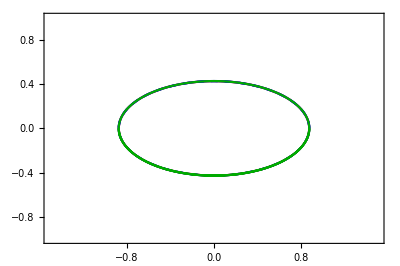

```mathematica
drawX6[1.5,1]
```

```mathematica
Clear@showSymmErrTest;
showSymmErrTest[a_,b_]:=Module[{x6s,o,n,s,δ,denom,a6,b6,ell6,gr,err=.025},
x6s=Table[{o,n,s}=orbitNormals[a,t];getSymmedianTrilin[o,s],{t,0,2π,π/180}];
δ=Sqrt[a^4-a^2*b^2+b^4];
denom=(3*a^4-2*a^2*b^2+3*b^4);
a6=(-b^4-a^2*b^2-δ*b^2+3*δ*a^2)*a/denom;
b6=(a^4+b^2*a^2+δ*a^2-3*δ*b^2)*b/denom;
Print@{a6,b6};
ell6=Table[{a6 Cos@t,b6 Sin@t+err},{t,0,2π,π/180}];
gr=Graphics[{Thick,
{Blue,Line@x6s},
{Darker@Green,Line@ell6}}];
Show[{plotEllb[a,b,{Thick,Black}],gr},Frame->True,GridLines->Automatic,PlotRange->{{-1.6,1.6},{-1.1,1.1}},ImageSize->800]];
```

{0.874217,0.427257}

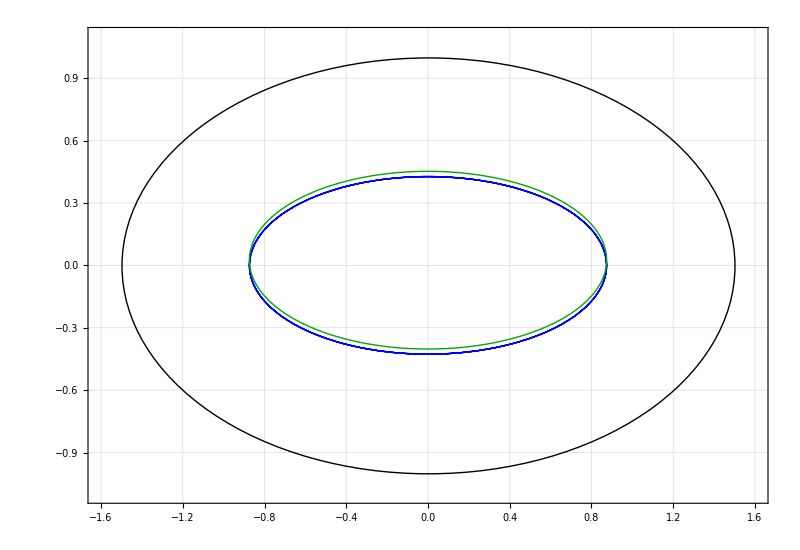

```mathematica
showSymmErrTest[1.5,1]
```

#### Zariski Closure Test X2

X2=100*x^2+ 225 y^2+ 52*sqrt(61)−413

```mathematica
x2ab15=Module[{a=1.5,b=1,delta,c2,k2,a2,b2,c2z,a2z,b2z,ons,x2l,x2t,eps=10^-6},
delta=Sqrt[a^4-a^2 b^2+b^4];
c2=a^2-b^2;
k2=(2delta-a^2-b^2)/(3c2);
{a2,b2}=k2{a,b};
c2z=-52Sqrt@61+413;
a2z=Sqrt[c2z/100];
b2z=Sqrt[c2z/225];
x2l=(ons=orbitNormals[a,0+eps];getBarycenterTrilin[ons[[1]],ons[[3]]]);
x2t=(ons=orbitNormals[a,π/2+eps];getBarycenterTrilin[ons[[1]],ons[[3]]]);
N/@<|"a2z"->a2z,"b2z"->b2z,"a2"->a2,"b2"->b2,
"x2l"->Abs[x2l[[1]]],"x2t"->Abs[x2t[[2]]]|>]
```

<|a2z→0.26205,b2z→0.1747,a2→0.26205,b2→0.1747,x2l→0.26205,x2t→0.1747|>

-Graphics-

X3: 5832 x^2 + (320 Sqrt@61 − 2752) y^2 + 729 Sqrt@61 - 5751

```mathematica
N[320 Sqrt@61 − 2752]
```

-252.72

```mathematica
N[−729 Sqrt@61+5751]
```

57.328

```mathematica
x3ab15=Module[{a=1.5,b=1,delta,k3,a3,b3,c3z,a3z,b3z,ons,x3l,x3t,eps=10^-6},
delta=Sqrt[a^4-a^2 b^2+b^4];
{a3,b3}={(a^2-delta)/(2a),(delta-b^2)/(2b)};
c3z=-729 Sqrt@61+5751;
a3z=Sqrt[c3z/5832];
b3z=Sqrt[c3z/(2752-320 Sqrt@61)];
x3l=(ons=orbitNormals[a,0+eps];getCircumcenterTrilin[ons[[1]],ons[[3]]]);
x3t=(ons=orbitNormals[a,π/2+eps];getCircumcenterTrilin[ons[[1]],ons[[3]]]);
N/@<|"a3z"->a3z,"b3z"->b3z,"a3"->a3,"b3"->b3,
"x3l"->Abs[x3l[[1]]],"x3t"->Abs[x3t[[2]]]|>]
```

<|a3z→0.0991459,b3z→0.476281,a3→0.0991459,b3→0.476281,x3l→0.0991459,x3t→0.476281|>

-Graphics-

```mathematica
N[-3969 Sqrt@61+22761]
```

-8237.88

```mathematica
x1ab15=Module[{a=1.5,b=1,delta,a1,b1,c1z,a1z,b1z,ons,x1l,x1t,eps=10^-6,L,Lsym},
delta=Sqrt[a^4-a^2 b^2+b^4];
{a1,b1}={(delta-b^2)/a,(a^2-delta)/b};
x1l=(ons=orbitNormals[a,0+eps];getIncenterTrilin[ons[[1]],ons[[3]]]);
L=Total@ons[[3]];
Lsym=FullSimplify@getGammaL[3/2,1][[2]];
Print@{L,Lsym,N@Lsym,FullSimplify[Lsym^2]};
(* 450 L^2 x^2 (125 sqrt@61+1075)L^2 y^2 + 22761 - 3969 sqrt@61 *)
c1z=3969Sqrt@61-22761;
b1z=Sqrt[c1z/(125Sqrt@61+1075)]/L;
a1z=Sqrt[c1z/450]/L;
x1l=(ons=orbitNormals[a,0+eps];getIncenterTrilin[ons[[1]],ons[[3]]]);
x1t=(ons=orbitNormals[a,π/2+eps];getIncenterTrilin[ons[[1]],ons[[3]]]);
N/@<|"a1z"->a1z,"b1z"->b1z,"a1"->a1,"b1"->b1,
"x1l"->Abs[x1l[[1]]],"x1t"->Abs[x1t[[2]]]|>]
```

{6.73751,1/5 √(2 (91+61 √61)),6.73751,2/25 (91+61 √61)}

<|a1z→0.635042,b1z→0.297438,a1→0.635042,b1→0.297438,x1l→0.635042,x1t→0.297438|>

```mathematica
N[3969Sqrt@61-22761]
```

8237.88

```mathematica
Module[{L2=2/25 (91+61 √61),c=3969Sqrt@61-22761},
FullSimplify[450 L2]x^2+FullSimplify[(125 Sqrt@61+1075) L2]y^2-c]
```

{1702.26,200970.,200951.}

## [*** paper 04] CBs of Excentral, ACT, Medial & Orthic

```mathematica
Clear@showAnyLocus;
showAnyLocus[a_,trilinFn_,clr_]:=Module[{o,n,s,x,xps},
Quiet@ParametricPlot[{o,n,s}=orbitNormals[a,toRad@tDeg];
x=trilinFn[o,s];
x,{tDeg,0,180},PlotStyle->clr,PerformanceGoal->"Quality"]]
```

```mathematica
Clear@showX168Locus;
showX168Locus[a_,ps_:Darker@Red]:=Module[{o,n,s,x168,x168ps},
Quiet@ParametricPlot[{o,n,s}=orbitNormals[a,toRad@tDeg];
x168=getX168Trilin[o,s];
x168,{tDeg,0,360},PlotStyle->ps,PerformanceGoal->"Speed"]]
```

#### Length of Excentral Circumbilliard Axes: their ratio is *not* constant

```mathematica
plotExcCircAxes[a_]:=
ListLinePlot[
Transpose@Module[{o,n,s,exc,excCirc,lgts},
Table[{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
excCirc=getCircumMit[exc];
lgts=excCirc["lengths"];
Join[lgts,{lgts[[1]]/lgts[[2]],lgts[[1]]lgts[[2]],lgts[[1]]+lgts[[2]],lgts[[1]]-lgts[[2]]}],
{tDeg,0,360,1}]],PlotStyle->Automatic,
PlotLegends->{"circumA","circumB","circumA/circumB","circumA*circumB","A+B","A-B"},Frame->True,GridLines->Automatic,ImageSize->Large]
```

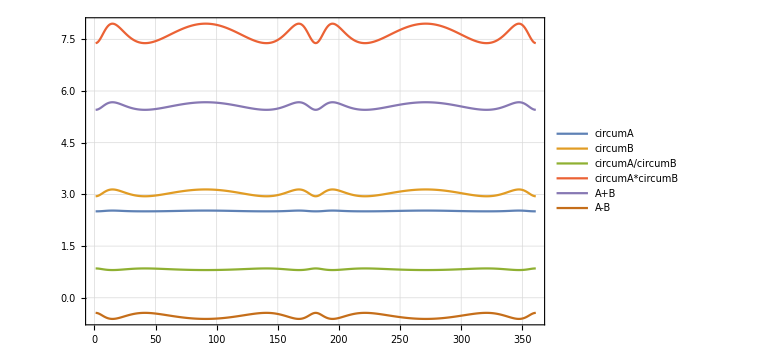

```mathematica
plotExcCircAxes[1.5]
```

#### a/b for which locus of X168 touches the EB top vertex

```mathematica
Clear@getX168Y;getX168Y[a_?NumericQ]:=Module[{ons,x168},
ons=orbitNormals[a,-π/2];
getX168Trilin[ons[[1]],ons[[3]]][[2]]];
```

```mathematica
Quiet@FindMinimum[(getX168Y[a]-1)^2,{a,1.2}]
```

{1.87478×10^-27,{a→1.47785}}

#### a/b for which X9* of orthic touches EB top vertex (orthic is equilateral)

```mathematica
Clear@getX9ortY;getX9ortY[a_?NumericQ]:=Module[{x9ort,ons},
ons=orbitNormals[a,π/2];
x9ort=getX9OrthicTrilin[ons[[1]],ons[[3]]];
x9ort[[2]]];
```

```mathematica
FindMinimum[(getX9ortY[a]-1)^2,{a,2.}]
```

{1.2326×10^-32,{a→1.98197}}

#### ronaldo: este número é raiz de quartica

```mathematica
Solve[a^4+6 a^2 -39==0,a]
```

{{a→-√(-3+4 √3)},{a→√(-3+4 √3)},{a→-ⅈ √(3+4 √3)},{a→ⅈ √(3+4 √3)}}

```mathematica
N@%
```

{{a→-1.98197},{a→1.98197},{a→0.-3.15091 ⅈ},{a→0.+3.15091 ⅈ}}

```mathematica
aEquiOrt=√(4 √3-3);
N@aEquiOrt
```

1.98197

```mathematica
aEquiOrt//TeXForm
```

\sqrt{4 \sqrt{3}-3}

```mathematica
isoscelesP2[1.5,1]
```

{{0,-1},{1.45692,0.23795},{-1.45692,0.23795}}

```mathematica
isoscelesP2[aEquiOrt,1]
```

{{0,-1},{-3/2+2 √3,1-(√3)/2},{3/2-2 √3,1-(√3)/2}}

```mathematica
N@%
```

{{0.,-1.},{1.9641,0.133975},{-1.9641,0.133975}}

```mathematica
equiOrtP2y=-isoscelesP2[aEquiOrt,1][[2,2]]
```

-1+(√3)/2

```mathematica
equiOrtSide=FullSimplify[magn[{0,1}+isoscelesP2[aEquiOrt,1][[2]]]]
```

4-√3

```mathematica
N@equiOrtSide
```

2.26795

```mathematica
equiOrtP2x=-isoscelesP2[aEquiOrt,1][[2,1]]
```

3/2-2 √3

```mathematica
equiOrtBase=FullSimplify[-2*equiOrtP2x]
```

-3+4 √3

```mathematica
equiOrtHeight=1-equiOrtP2y
```

2-(√3)/2

```mathematica
N@%
```

1.13397

```mathematica
equiOrtBaseToHeight=FullSimplify[equiOrtBase/equiOrtHeight]
```

2 √3

```mathematica
N@1/equiOrtBaseToHeight
```

0.288675

```mathematica
FullSimplify[equiOrtHeight*equiOrtBase/2]
```

-6+(19 √3)/4

```mathematica
N@%
```

2.22724

```mathematica
N@equiOrtP2y
```

-0.133975

#### Radius of circumcircle (and CB) of orthic equi: goes from (0,1) to (0,equiP2y) = 1-equiP2y

```mathematica
equiOrtR=1-equiOrtP2y
```

2-(√3)/2

```mathematica
N@equiOrtR
```

1.13397

#### Side of equilateral : radius x Sqrt[3]

```mathematica
equiOrtSide=FullSimplify[equiOrtR Sqrt[3]]
```

-3/2+2 √3

```mathematica
N@equiOrtSide
```

1.9641

```mathematica
FullSimplify[equiOrtHeight=equiOrtSide*Sqrt[3]/2]
```

3-(3 √3)/4

#### Is the intersection of the equi circle with the P2P1 segment on the quartic?

-Graphics-

```mathematica
N@isoscelesP2[aEquiOrt,1]
```

{{0.,-1.},{1.9641,0.133975},{-1.9641,0.133975}}

```mathematica
equiOrbitP2=(-isoscelesP2[aEquiOrt,1][[2]]);N@isoP2
```

isoP2

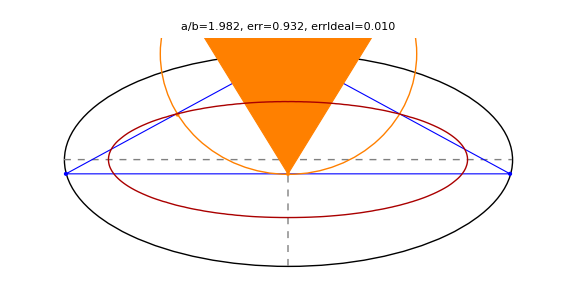

```mathematica
Module[{a=aEquiOrt,intCirc,ons,ell,gr,err,p1={0,1},cs,cp,pl,slack=.1,axesIdeal,errIdeal,equiBot,equi},
cs=x6quarticCoeffs[a,1];
ons=orbitNormals[a,π/2];
intCirc=FullSimplify[p1+equiOrtR norm[(equiOrbitP2-p1)]];
err=FullSimplify@onX6quartic[a,1,Sequence@@intCirc];
axesIdeal=x6ideal[a,1];
errIdeal=FullSimplify@ellError[Sequence@@axesIdeal,intCirc];
(*Print@ FullSimplify[onX6quartic[a,1,axesIdeal[[1]],0]];
Print@ FullSimplify[onX6quartic[a,1,0,axesIdeal[[2]]]];*)
equiBot={0,equiOrbitP2[[2]]};
equi={equiBot,rotRel[equiBot,2π/3,p1],rotRel[equiBot,-2π/3,p1]};
ell=plotEllAxes[a,{Thick,Black}];
gr=Graphics[{PointSize@Large,Thick,FaceForm@None,
drawPoly[ons[[1]],Blue],
{Orange,Circle[p1,equiOrtR],Point@intCirc,drawPoly[equi,Orange]}}];
cp=ContourPlot[x6quarticEqn[x,y,Sequence@@cs]==0,{x,-a,a},{y,-1,1},ContourStyle->Directive[Thick,Darker@Red]];
pl="a/b="<>nfn[N@a,3]<>", err="<>nfn[N@err,3]<>", errIdeal="<>nfn[N@errIdeal,3];
Show[{ell,gr,cp},ImageSize->Large,PlotRange->{{-a-slack,a+slack},{-1-slack,1+slack}},PlotLabel->Style[pl,{Black,16}]]]
```

```mathematica
DynamicModule[{a=1.5,trilFn1=getIncenterTrilin,n1=1,x1,trilFn2=getCircumcenterTrilin,n2=3,
ons,ell,exc,gr,pr,slackX=.5,slackY=2,sides1,preTris,pl,preTrisAreas,preTrisPers,preTris1s,equiErr},
Manipulate[
ell=plotEllAxes[a,{Thick,Black}];
Dynamic[
ons=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[ons[[1]],ons[[3]]];
x1=trilFn1[ons[[1]],ons[[3]]];
(* pre tris: 3 sutriangles forrmed by sides of exc and x1 *)
preTris=MapThread[{#1,x1,#2}&,{ons[[1]],RotateLeft@ons[[1]]}];
preTrisAreas=signedArea/@preTris;
preTrisPers=triPer/@preTris;
(* pretris1: triangle formed by trilFn2 centers of each in preTris *)
preTris1s=trilFn2[#,triLengthsRL@#]&/@preTris;
(*preTrisX3s=getCircumcenterTrilin[#,triLengthsRL@#]&/@preTris;*)
equiErr=equiError[preTris1s];
(*sides1=triLengthsRL@preTris1s;
central1=trilFn1[preTris1s,sides1];
central2=trilFn2[preTris1s,sides1];*)
gr=Graphics[{FaceForm@None,PointSize@Large,Thick,
drawPoly[ons[[1]],Blue],drawPoly[exc,Darker@Green],
{Darker@Green,Point@x1,Text[Style[ToString[Subscript["X",n1],StandardForm],16],x1,{-1,-1}]},
MapThread[{#3,Point@#2,drawPoly[#1,#3]}&,{preTris,preTris1s,{Red,Purple,Cyan}}],
{drawPoly[preTris1s,Black](*,Circle[central1,.1],Circle[central2,.1]*)}}];
pl="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°\n"<>"areas: "<>(nfn[#,3]<>", "&/@preTrisAreas)<>"\npers: "<>(nfn[#,3]<>", "&/@preTrisPers)<>" ∑="<>nfn[Total@preTrisPers,2]<>"\nequiErr="<>nfn[equiErr,3];
pr={{-a-slackX,a+slackX},{-1-slackY,1+slackY}};
Show[{ell,gr},PlotRange->pr,ImageSize->Large,PlotLabel->Style[pl,{Black,16}]]],{{tDeg,10.},-180,180,.1}]]
```

#### ronaldo: x6 of right triangle, points of detachment, midpoint of right tris altitude?

```mathematica
rightTriangleX6[a_,b_]:=Module[{delta=getDelta[a,b],x6,y6,c=Sqrt[a^2-b^2]},
x6=-(-a^6-2a^2b^4-b^6+3a^2b^2delta+b^4delta)Sqrt@(a^4+3b^4-4b^2delta)a^2/c^9; y6=(-a^6-2a^4b^2-b^6+a^4delta+3a^2b^2delta)Sqrt@(-3a^4-b^4+4a^2delta)b^2/c^9;
{x6,y6}]
```

```mathematica
rightTriangleX6[a,b]
```

{(a^2 √(a^4+3 b^4-4 b^2 √(a^4-a^2 b^2+b^4)) (a^6+2 a^2 b^4+b^6-3 a^2 b^2 √(a^4-a^2 b^2+b^4)-b^4 √(a^4-a^2 b^2+b^4)))/((a^2-b^2)^(9/2)),(b^2 √(-3 a^4-b^4+4 a^2 √(a^4-a^2 b^2+b^4)) (-a^6-2 a^4 b^2-b^6+a^4 √(a^4-a^2 b^2+b^4)+3 a^2 b^2 √(a^4-a^2 b^2+b^4)))/((a^2-b^2)^(9/2))}

```mathematica
rightTriangleX6simple=Module[{x6,y6},
x6=-(-a^6-2a^2b^4-b^6+3a^2b^2δ+b^4δ)Sqrt@(a^4+3b^4-4b^2δ)a^2/c^9; y6=(-a^6-2a^4b^2-b^6+a^4δ+3a^2b^2δ)Sqrt@(-3a^4-b^4+4a^2δ)b^2/c^9;
{x6,y6}]
```

{(a^2 √(a^4+3 b^4-4 b^2 δ) (a^6+2 a^2 b^4+b^6-3 a^2 b^2 δ-b^4 δ))/c^9,(b^2 √(-3 a^4-b^4+4 a^2 δ) (-a^6-2 a^4 b^2-b^6+a^4 δ+3 a^2 b^2 δ))/c^9}

```mathematica
rightTriangleX6simple//TeXForm
```

\left\{\frac{a^2 \sqrt{a^4+3 b^4-4 b^2 \delta } \left(a^6+2 a^2 b^4-3 a^2 b^2 \delta +b^6-b^4 \delta \right)}{c^9},\frac{b^2 \sqrt{-3 a^4+4 a^2
   \delta -b^4} \left(-a^6-2 a^4 b^2+a^4 \delta +3 a^2 b^2 \delta -b^6\right)}{c^9}\right\}

```mathematica
rightTriangleX6[1.5,1]
```

{0.727927,0.236758}

#### What is the point on the EB such that the orbit is a right triangle

```mathematica
rightTriangleOnBilliard[a_,b_]:=Module[{δ=Sqrt[a^4-a^2 b^2+b^4],c=Sqrt[a^2-b^2]},
{a^2 Sqrt[a^4+3 b^4-4 δ b^2],b^2 Sqrt[-b^4-3 a^4+4δ a^2]}/c^3];
```

```mathematica
rtonEBsimple={a^2 Sqrt[a^4+3 b^4-4 δ b^2],b^2 Sqrt[-b^4-3 a^4+4δ a^2]}/c^3
```

{(a^2 √(a^4+3 b^4-4 b^2 δ))/c^3,(b^2 √(-3 a^4-b^4+4 a^2 δ))/c^3}

```mathematica
showRectZones[a_,tDeg1_,tDeg2_]:=Module[{ell,ons1,ons2,pperp,pperps,gr,tMin,tMax,zoneTop,zoneBot,cAB,causticEll},
ell=plotEllAxes[a,{Black,Thick}];
pperp=rightTriangleOnBilliard[a,1];
cAB=getCausticAxes[a,1];
causticEll=plotEllb[Sequence@@cAB,{Thick,Brown}];
pperps={pperp,flipX@pperp,-pperp,flipY@pperp};
{ons1,ons2}=orbitNormals[a,toRad@#]&/@{tDeg1,tDeg2};
(* a Cos@t, b Sin@t *)
tMin=ArcTan[pperp[[1]]/a,pperp[[2]]];
tMax= ArcTan[-pperp[[1]]/a,pperp[[2]]];
zoneTop=ParametricPlot[{a Cos@t,Sin@t},{t,tMin,tMax},PlotStyle->Directive[AbsoluteThickness@3,Red]];
zoneBot=ParametricPlot[{a Cos@t,-Sin@t},{t,tMin,tMax},PlotStyle->Directive[AbsoluteThickness@3,Red]];
gr=Graphics[{PointSize@Large,FaceForm@None,
{Point@pperps,ellLabelPointsSuperSub[a,pperps,"P","⊥",20,.1]},
{drawPoly[ons1[[1]],Blue],drawPoly[ons2[[1]],Directive[Dashed,Blue]]}}];
Show[{ell,causticEll,zoneTop,zoneBot,gr},ImageSize->800]];
```

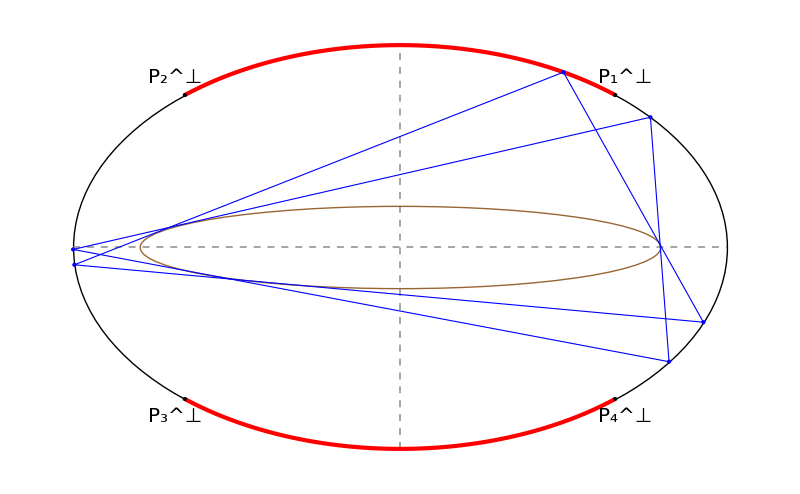

```mathematica
rectZonePlot=showRectZones[1.618,40.,60.]
```

```mathematica
export3["0080_rect_zones",rectZonePlot]
```

```mathematica
rtonEBsimple//TeXForm
```

\left\{\frac{a^2 \sqrt{a^4+3 b^4-4 b^2 \delta }}{c^3},\frac{b^2 \sqrt{-3 a^4+4 a^2 \delta -b^4}}{c^3}\right\}

#### Note : the argument of sqrt becomes zero at the a/b~1.35219 which only contains one right - triangle

```mathematica
Solve[a^4+3 -4 Sqrt[a^4-a^2+1]==0,a]
```

{{a→-1},{a→1},{a→-√(-1+2 √2)},{a→√(-1+2 √2)},{a→-ⅈ √(1+2 √2)},{a→ⅈ √(1+2 √2)}}

```mathematica
N@%
```

{{a→-1.},{a→1.},{a→-1.35219},{a→1.35219},{a→0.-1.95664 ⅈ},{a→0.+1.95664 ⅈ}}

```mathematica
rightTriangleCosine[a_,b_]:=Module[{δ=Sqrt[a^4-a^2 b^2+b^4],c=Sqrt[a^2-b^2]},
a Sqrt[a^4+3 b^4-4 δ b^2]/c^3];
```

```mathematica
rightTriangleSine[a_,b_]:=Module[{δ=Sqrt[a^4-a^2b^2+b^4],c=Sqrt[a^2-b^2]},
b Sqrt[-3a^4-b^4+4a^2 δ]/c^3]
```

```mathematica
rightTriangleT[a_]=FullSimplify[ArcTan[rightTriangleCosine[a,1],rightTriangleSine[a,1]],a>1]
```

ArcTan[a √(3+a^4-4 √(1-a^2+a^4)),√(-1-3 a^4+4 a^2 √(1-a^2+a^4))]

```mathematica
rightTriangleT[1.5]
```

1.00147

#### What is the a/b such that the box of the right triangle points on the billiard is tangent to the side vertices of the X6 (quartic) locus

```mathematica
N@Solve[15a^8-56 a^6+58 a^4-40 a^2+7==0,a]
```

{{a→-0.805085+0.460339 ⅈ},{a→0.805085-0.460339 ⅈ},{a→-0.805085-0.460339 ⅈ},{a→0.805085+0.460339 ⅈ},{a→-0.490696},{a→0.490696},{a→-1.61866},{a→1.61866}}

```mathematica
1/.4907
```

2.03791

```mathematica
Clear@getCBVizObjs;
Options@getCBVizObjs={clrOrt->{Dashed,Thick,Orange}};
getCBVizObjs[a_,OptionsPattern[]]:=Module[{ell,loci,excLocus,medLocus,extLocus,actLocus,ortLocus,ra,ras,rX6,rX6s,x6axes},
ell=plotEllAxes[a,{Thick,Black}];
loci=MapThread[showAnyLocus[a,#1,#2]&,
Transpose@{
{getX168Trilin,{Thick,Darker@Red}},
{getGergonneTrilin,{Thick,Darker@Red}},
{getX142Trilin,{Thick,Darker@Red}},
{getX9OrthicTrilin,{Thick,Darker@Red}},
{getSymmedianTrilin,{Thick,Lighter@Blue}},
{getX9ExtouchTrilin,{Thick,Brown}}}];
ra=rightTriangleOnBilliard[a,1];
ras={ra,flipX@ra,-ra,flipY@ra};
rX6=rightTriangleX6[a,1];
rX6s={rX6,flipX@rX6,-rX6,flipY@rX6};
x6axes=x6ideal[a,1];
(* Darker@Green,Blue,ColorData["HTML","Teal"],Orange,Brown *)
excLocus=plotEllb[Sequence@@getExcenterAxes[a],{Dashed,Thick,Darker@Green}];
actLocus=getAntiComplementaryVertexLocus[a,2π,{Dashed,Thick,Lighter@Blue}];
medLocus=medialLocus[a,2π,{Dashed,Thick,ColorData["HTML","Teal"]}];
ortLocus=orthicVertexLocus[a,2π,OptionValue@clrOrt];
extLocus=plotEllb[Sequence@@getCausticAxes[a,1],{Dashed,Thick,Brown}];
<|"a"->a,"ell"->ell,"loci"->loci,
"excLocus"->excLocus,
"extLocus"->extLocus,
"medLocus"->medLocus,
"ortLocus"->ortLocus,
"actLocus"->actLocus,
"ras"->ras,
"rX6s"->rX6s,
"x6axes"->x6axes|>];
```

```mathematica
Clear@drCBVizObjs;
drCBVizObjs[a_,tDeg_,objs_,ui_]:=Module[{o,n,s,tris,exc,act,med,ort,ext,ortExc,
drCB,CBs,x168,ortX9,x6,x7,x4,gr,pl},
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
act=anticomplementaryTriangle[o,s];
med=medialTriangle[o,s];
ort=orthicTriangle[o,s];
ext=extouchTriangle[o,s];
tris={exc,act,med,ort,ext};
ortExc=excentralTriangle[ort,triLengthsRL@ort];
drCB=Lookup[ui,{"drExcCB","drActCB","drMedCB","drOrtCB","drExtCB"}];
CBs=If[Count[drCB,True]==0,{},getCircumMit/@Pick[tris,drCB]];(*{drExcCB,drActCB,drMedCB,drOrtCB,drExtCB} *)
(* mitten of excentral *)
x168=getX168Trilin[o,s];
(*ortX9=getMittenTrilin[ort,triLengthsRL@ort];*)
ortX9=getSymmedianTrilin[ortExc,triLengths@ortExc];
x6=getSymmedianTrilin[o,s];
x7=getGergonneTrilin[o,s];
x4=getOrthocenterTrilin[o,s];
gr=Graphics[{FaceForm@None, PointSize@Large,
{
{drawPoly[o,Black],If[ui["drPs"],ellLabelPoints[a,o,"P",16,.1],{}]},
MapThread[drawPoly[#1,#2]&,
Pick[#,drCB]&/@
Transpose@{{exc,Darker@Green},
{act,Blue},
{med,ColorData["HTML","Teal"]},
{ort,Orange},
{ext,Brown}}],
{Point@{0.,0.},Text[Style["X_9",20],{0.,0.},{-1.25,-1.25}]},
If[ui["drRas"],{Black,Point@objs["ras"],ellLabelPointsSuperSub[a,objs["ras"],"P","⊥",20,.1]},{}],
If[ui["drRasPoly"],drawPoly[objs["ras"],Directive[Thickness@Small,Dashed,Black]],{}],
(*,{Orange,Text["tX_168",x168ic,{-1.5,-1.5}],Point@x168ic}*),
If[ui["drX9X7"],{Black,Text[Style["X_7",16],x7,{1.25,1.25}],Dashed,Line@{{0,0},x7},PointSize@Medium,Point@x7},{}],
If[ui["drOrtExc"],{(*Dashed,Line@{x4,ortX9},*)(*Orange,Point@x4,*)drawPoly[ortExc,Directive[Dashed,Orange]],
{Orange,Point@x4,Text[Style["X_4",20],x4,ui["x4pos" ]]},
{Lighter@Blue,Point@x6,ellLabelTxtb[Sequence@@objs["x6axes"],x6,Style["X_6",20] ,.1,inward->True],Point@objs["rX6s"],ellLabelPointsb[Sequence@@objs["x6axes"],objs["rX6s"],"Q",16,.075]}},{}]}}];
pl="a/b="<>nfn[a,ui["adigs"]]<>", θ="<>nfn[tDeg,1]<>"°";
(* If[drActCB,drawCircumAnyLow[actCB,act,ctrLab->"X_7",ps->Blue,labClr->Blue],{}], *)
Show[{objs["ell"],
If[ui["drVtxLoci"],
{If[ui["drExcCB"],objs["excLocus"],{}],
If[ui["drActCB"],objs["actLocus"],{}],
If[ui["drMedCB"],objs["medLocus"],{}],
If[ui["drOrtCB"],objs["ortLocus"],{}]},{}],
If[Count[drCB,True]>0,
MapThread[drawCircumAnyLow[#1,#2,ctrLab->Subsuperscript["X",#3,#4],ps->#5,labClr->#6,labPos->{-1,-1}]&,
{CBs,Sequence@@(Pick[#,drCB]&/@{tris,
{168,7,142,6,9},
{"","","","*","**"},
{Darker@Green,Blue,ColorData["HTML","Teal"],Orange,Brown},
{Darker@Red,Darker@Red,Darker@Red,Darker@Red,Brown}})}],{}]},
If[ui["drLoci"],Pick[objs["loci"],Lookup[ui,{"drExcCB","drActCB","drMedCB","drOrtCB","drOrtCB","drExtCB"}]],{}],
gr,
PlotRange->{{ui["minX"],ui["maxX"]},{ui["minY"],ui["maxY"]}},
GridLines->None,If[ui["pl"],PlotLabel->Style[pl,{Black,16}],{}],ImageSize->ui["imgSize"]]];
```

```mathematica
rightTriangleOnBilliard[1.4,1]
```

{0.472834,0.94124}

```mathematica
rightTriangleSine[a_,b_]:=Module[{δ=Sqrt[a^4-a^2*b^2+b^4],c=Sqrt[a^2-b^2]},
b Sqrt[-3*a^4-b^4+4a^2 δ]/c^3]
```

```mathematica
rightTriangleCosine[1.5,1]
```

0.539066

```mathematica
DynamicModule[{objs,ui,vals=Range[1,10,.25]},
Manipulate[
objs=getCBVizObjs[a,clrOrt->{Thick,Darker@Green}];
Dynamic[
ui=<|
"a"->a,
"tDeg"->tDeg,
"drLoci"->drLoci,
"drExcCB"->drExcCB,
"drActCB"->drActCB,
"drMedCB"->drMedCB,
"drOrtCB"->drOrtCB,
"drExtCB"->drExtCB,
"drOrtExc"->drOrtExc,
"minX"->minX,
"maxX"->maxX,
"minY"->minY,
"maxY"->maxY,
"imgSize"->imgSize,
"drRas"->drRas,
"drRasPoly"->False,
"pl"->drPl,
"drX9X7"->drX9X7,
"drVtxLoci"->drVtxLoci,
"x4pos"->{-1.25,-1.25},
"adigs"->3,
"drPs"->True
|>;
drCBVizObjs[a,tDeg,objs,ui]
],
{{a,1.5},1.3522,3.,.001},
{{tDeg,120.},-360,360,.1},
{{drLoci,True},{True,False}},
{{drExcCB,False},{True,False}},
{{drActCB,False},{True,False}},
{{drMedCB,False},{True,False}},
{{drOrtCB,True},{True,False}},
{{drOrtExc,False},{True,False}},
{{drExtCB,False},{True,False}},
{{drVtxLoci,True},{True,False}},
{{drPl,True},{True,False}},
{{drX9X7,False},{True,False}},
Row[{Control[{{minX,-2},-vals}],Control[{{maxX,2},vals}]}],
Row[{Control[{{minY,-2},-vals}],Control[{{maxY,2},vals}]}],
{{imgSize,600},{400,600,800,1200}},
Row[{Control[{{drRas,False,"right tri pts"},{True,False}}],Button["right tri",tDeg=toDeg@(rightTriangleT[a]+.00001),ImageSize->Medium],
Button["equi tri",a=N@aEquiOrt;tDeg=90.,ImageSize->Medium],
Button["print ui",Print@ui,ImageSize->Medium]}],
ControlPlacement->Left]]
```

```mathematica
Clear@oneCBPrintObjs;oneCBPrintObjs[objs_,ui_]:=drCBVizObjs[ui["a"],ui["tDeg"],objs,ui];
```

```mathematica
Clear@oneCBPrint;
oneCBPrint[ui_]:=Module[{objs},
objs=getCBVizObjs@ui["a"];
oneCBPrintObjs[objs,ui]];
```

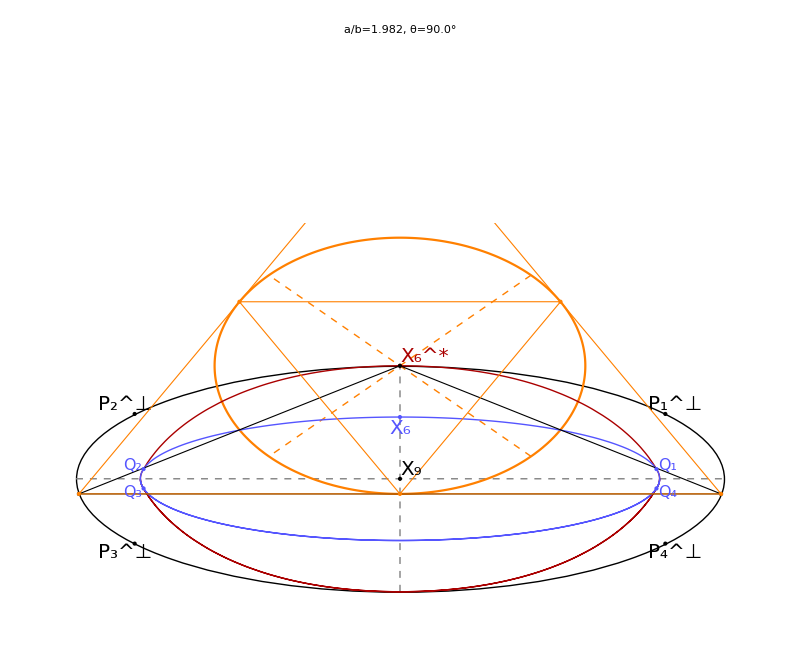

```mathematica
orthicEquiPlot=oneCBPrint[<|"a"->1.981969533135035,
"tDeg"->90.01,
"drLoci"->True,
"drExcCB"->False,
"drActCB"->False,
"drMedCB"->False,
"drOrtCB"->True,
"drExtCB"->False,
"drOrtExc"->True,
"minX"->-2,
"maxX"->2,
"minY"->-1.1,
"maxY"->2.2,
"imgSize"->800,
"drRas"->True,
"drRasPoly"->False,
"pl"->True,
"drX9X7"->False,
"drVtxLoci"->False,
"x4pos"->{-1.25,-1.25},
"adigs"->3,
"drPs"->False|>]
```

```mathematica
export3["0040_cb_ort_equi",orthicEquiPlot]
```

```mathematica
orthicPositions=Module[{a=1.5,sz=800,objs,horiz,equi,scalene,right,minY=-1.1,maxY=1.6,maxX=1.7},
objs=getCBVizObjs[a];
horiz=oneCBPrintObjs[objs,<|"a"->a,"tDeg"->180.,"drLoci"->True,"drExcCB"->False,"drActCB"->False,"drMedCB"->False,"drOrtCB"->True,"drExtCB"->False,"drOrtExc"->True,"minX"->-maxX,"maxX"->maxX,"minY"->minY,"maxY"->1.1,"imgSize"->sz,"drRas"->True,"drRasPoly"->False,"pl"->True,"drX9X7"->False,"drVtxLoci"->False,"x4pos"->{-1.25,-1.25},"adigs"->3,"drPs"->False|>];
right=oneCBPrintObjs[objs,<|"a"->a,"tDeg"->57.38,"drLoci"->True,"drExcCB"->False,"drActCB"->False,"drMedCB"->False,"drOrtCB"->True,"drExtCB"->False,"drOrtExc"->False,"minX"->-maxX,"maxX"->maxX,"minY"->minY,"maxY"->1.1,"imgSize"->sz,"drRas"->True,"drRasPoly"->False,"pl"->True,"drX9X7"->False,"drVtxLoci"->False,"x4pos"->{-1.25,-1.25},"adigs"->3,"drPs"->False|>];
scalene=oneCBPrintObjs[objs,<|"a"->a,"tDeg"->68.6,"drLoci"->True,"drExcCB"->False,"drActCB"->False,"drMedCB"->False,"drOrtCB"->True,"drExtCB"->False,"drOrtExc"->True,"minX"->-maxX,"maxX"->maxX,"minY"->minY,"maxY"->maxY,"imgSize"->sz,"drRas"->True,"drRasPoly"->False,"pl"->True,"drX9X7"->False,"drVtxLoci"->False,"x4pos"->{-1.25,-1.25},"adigs"->3,"drPs"->False|>];
equi=oneCBPrintObjs[objs,<|"a"->a,"tDeg"->90.,"drLoci"->True,"drExcCB"->False,"drActCB"->False,"drMedCB"->False,"drOrtCB"->True,"drExtCB"->False,"drOrtExc"->True,"minX"->-maxX,"maxX"->maxX,"minY"->minY,"maxY"->maxY,"imgSize"->sz,"drRas"->True,"drRasPoly"->False,"pl"->True,"drX9X7"->False,"drVtxLoci"->False,"x4pos"->{-1.25,-1.25},"adigs"->3,"drPs"->False|>];
{horiz,right,scalene,equi}];
```

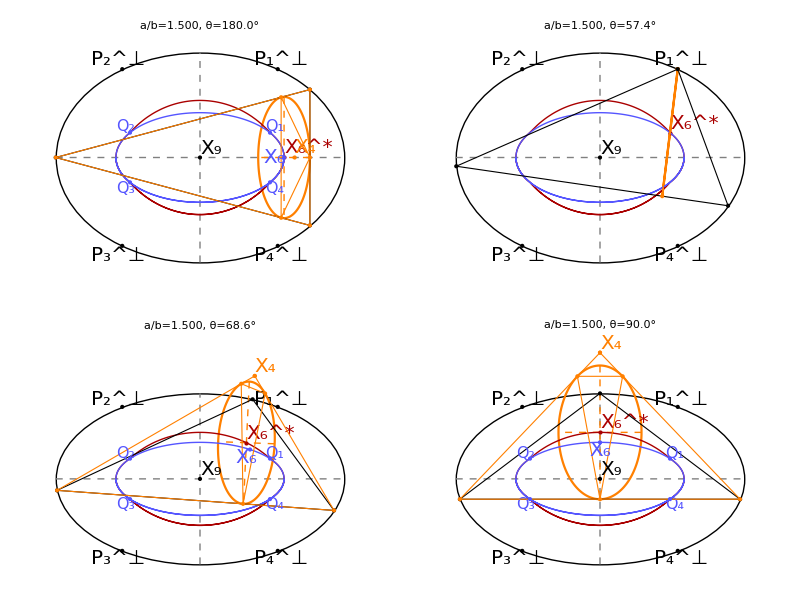

```mathematica
ortX6plot=Grid[Partition[orthicPositions,2],Frame->All]
```

```mathematica
export3["0030_cb_ort",ortX6plot]
```

```mathematica
Clear@oneCBPrintObjs;oneCBPrintObjs[ui_,objs_]:=drCBVizObjs[ui["a"],ui["tDeg"],objs,ui];
```

```mathematica
Clear@drawOneCBtrio;drawOneCBtrio[a_,tDeg_]:=Module[{objs,uiExc,uiAct,uiMed,cbExc},
objs=getCBVizObjs[a];
uiExc=<|"a"->a,"tDeg"->tDeg,"drLoci"->True,"drExcCB"->True,"drActCB"->False,"drMedCB"->False,"drOrtCB"->False,"drExtCB"->False,"drOrtExc"->False,"minX"->-3.,"maxX"->3.5,"minY"->-2.5,"maxY"->5.,"imgSize"->640,"drRas"->False,"drRasPoly"->False,"pl"->False,"drX9X7"->False,"drVtxLoci"->True,"x4pos"->{-1.25,-1.25},"adigs"->3,"drPs"->False|>;
cbExc=oneCBPrintObjs[objs,uiExc];
uiAct=<|"a"->a,"tDeg"->tDeg,"drLoci"->True,"drExcCB"->False,"drActCB"->True,"drMedCB"->False,"drOrtCB"->False,"drExtCB"->False,"drOrtExc"->False,"minX"->-4.,"maxX"->3.,"minY"->-2.75,"maxY"->1.75,"imgSize"->600,"drRas"->False,"drRasPoly"->False,"pl"->False,"drX9X7"->False,"drVtxLoci"->True,"x4pos"->{-1.25,-1.25},"adigs"->3,"drPs"->False|>;
uiMed=<|"a"->a,"tDeg"->tDeg,"drLoci"->True,"drExcCB"->False,"drActCB"->False,"drMedCB"->True,"drOrtCB"->False,"drExtCB"->False,"drOrtExc"->False,"minX"->-2.,"maxX"->2.,"minY"->-1.25,"maxY"->1.125,"imgSize"->600,"drRas"->False,"drRasPoly"->False,"pl"->False,"drX9X7"->True,"drVtxLoci"->True,"x4pos"->{-1.25,-1.25},"adigs"->3,"drPs"->False|>;
Grid[{{Style["a/b="<>nfn[a,3]<>", θ="<>nfn[tDeg,1]<>"°",{Black,30}],SpanFromLeft},{cbExc,Grid[{{oneCBPrintObjs[objs,uiAct]},{oneCBPrintObjs[objs,uiMed]}},Spacings->0,Dividers->{None,{False,True}}]}},Spacings->0,Frame->All,Alignment->Top]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

CompiledFunction::cfsa: Argument 2\ √1 + 1.61792\ Cos[0.0174533\ Missing[« 2 »]]^2 at position 2 should be a "machine-size real number".

CompiledFunction::cfsa: Argument Indeterminate at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

Pick::incomp: Expressions {{{If[2\ √Abs[« 1 »] < 1/1000000000, 0, 0./2\ Power[« 2 »]], If[2\ √Abs[« 1 »] < 1/1000000000, 0, 0/2\ Power[« 2 »]]}, {0., 0.}, {0., 0.}}, « 3 », {{0., 0.}, {If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate], If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate]}, {If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate], If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate]}}} and {Missing["KeyAbsent", "drExcCB"], Missing["KeyAbsent", "drActCB"], Missing["KeyAbsent", "drMedCB"], Missing["KeyAbsent", "drOrtCB"], Missing["KeyAbsent", "drExtCB"]} have incompatible shapes.

Pick::incomp: Expressions … and {Missing["KeyAbsent", "drExcCB"], Missing["KeyAbsent", "drActCB"], Missing["KeyAbsent", "drMedCB"], Missing["KeyAbsent", "drOrtCB"], Missing["KeyAbsent", "drExtCB"]} have incompatible shapes.

MapThread::mptd: Object Pick[{{{If[2\ Power[« 2 »] < 1/1000000000, 0, 0./Times[« 2 »]], If[2\ Power[« 2 »] < 1/1000000000, 0, 0/Times[« 2 »]]}, {0., 0.}, {0., 0.}}, « 3 », {{0., 0.}, {If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate], If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate]}, {If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate], If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate]}}}, {Missing["KeyAbsent", "drExcCB"], Missing["KeyAbsent", "drActCB"], Missing["KeyAbsent", "drMedCB"], Missing["KeyAbsent", "drOrtCB"], Missing["KeyAbsent", "drExtCB"]}] at position {2, 1} in … has only 0 of required 1 dimensions.

NumberForm::iprf: Formatting specification {2 + Missing["KeyAbsent", "adigs"], Missing["KeyAbsent", "adigs"]} should be a positive integer or a pair of positive integers.

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

Pick::incomp: Expressions {{{If[2\ √Abs[« 1 »] < 1/1000000000, 0, 0./2\ Power[« 2 »]], If[2\ √Abs[« 1 »] < 1/1000000000, 0, 0/2\ Power[« 2 »]]}, {0., 0.}, {0., 0.}}, « 3 », {{0., 0.}, {If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate], If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate]}, {If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate], If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate]}}} and {Missing["KeyAbsent", "drExcCB"], Missing["KeyAbsent", "drActCB"], Missing["KeyAbsent", "drMedCB"], Missing["KeyAbsent", "drOrtCB"], Missing["KeyAbsent", "drExtCB"]} have incompatible shapes.

General::stop: Further output of Pick :: incomp will be suppressed during this calculation.

MapThread::mptd: Object Pick[{{{If[2\ Power[« 2 »] < 1/1000000000, 0, 0./Times[« 2 »]], If[2\ Power[« 2 »] < 1/1000000000, 0, 0/Times[« 2 »]]}, {0., 0.}, {0., 0.}}, « 3 », {{0., 0.}, {If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate], If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate]}, {If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate], If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate]}}}, {Missing["KeyAbsent", "drExcCB"], Missing["KeyAbsent", "drActCB"], Missing["KeyAbsent", "drMedCB"], Missing["KeyAbsent", "drOrtCB"], Missing["KeyAbsent", "drExtCB"]}] at position {2, 1} in … has only 0 of required 1 dimensions.

NumberForm::iprf: Formatting specification {2 + Missing["KeyAbsent", "adigs"], Missing["KeyAbsent", "adigs"]} should be a positive integer or a pair of positive integers.

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

MapThread::mptd: Object Pick[{{{If[2\ Power[« 2 »] < 1/1000000000, 0, 0./Times[« 2 »]], If[2\ Power[« 2 »] < 1/1000000000, 0, 0/Times[« 2 »]]}, {0., 0.}, {0., 0.}}, « 3 », {{0., 0.}, {If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate], If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate]}, {If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate], If[Indeterminate < 1/1000000000, 0, Indeterminate/Indeterminate]}}}, {Missing["KeyAbsent", "drExcCB"], Missing["KeyAbsent", "drActCB"], Missing["KeyAbsent", "drMedCB"], Missing["KeyAbsent", "drOrtCB"], Missing["KeyAbsent", "drExtCB"]}] at position {2, 1} in … has only 0 of required 1 dimensions.

General::stop: Further output of MapThread :: mptd will be suppressed during this calculation.

NumberForm::iprf: Formatting specification {2 + Missing["KeyAbsent", "adigs"], Missing["KeyAbsent", "adigs"]} should be a positive integer or a pair of positive integers.

General::stop: Further output of NumberForm :: iprf will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

General::stop: Further output of Show :: gcomb will be suppressed during this calculation.

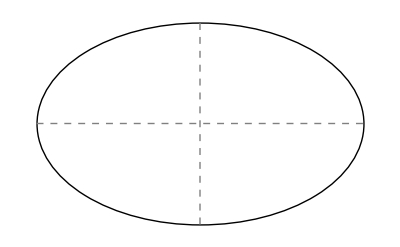
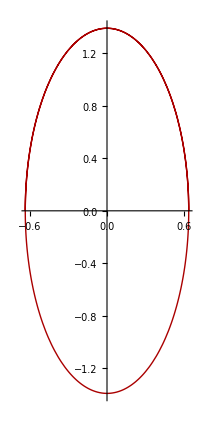
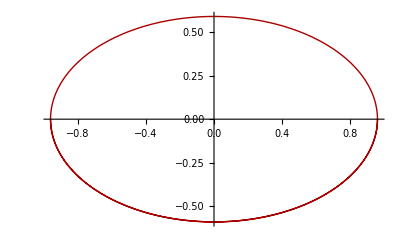
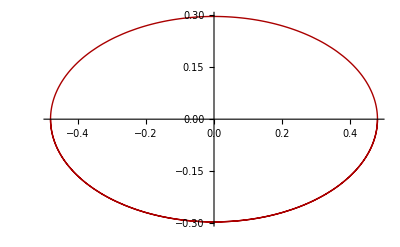
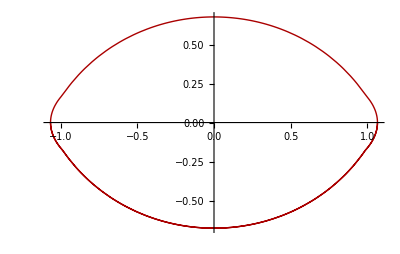
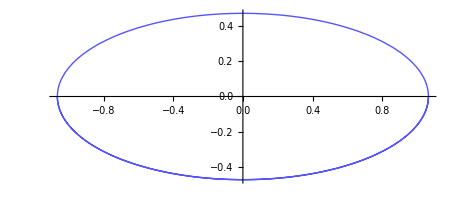
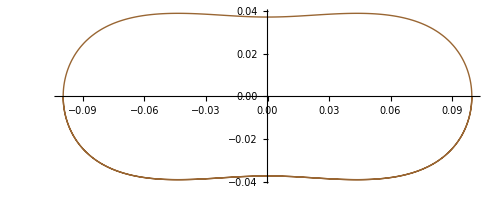
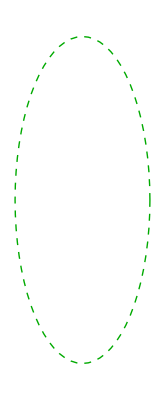
a/b=1.618, θ=7.0° | 
Show[{Missing[KeyAbsent,ell],If[Missing[KeyAbsent,drVtxLoci],{If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drExcCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→True,drActCB→False,drMedCB→False,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-3.,maxX→3.5,minY→-2.5,maxY→5.,imgSize→640,drRas→False,drRasPoly→False,pl→False,drX9X7→False,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[excLocus],{}],If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drActCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→True,drActCB→False,drMedCB→False,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-3.,maxX→3.5,minY→-2.5,maxY→5.,imgSize→640,drRas→False,drRasPoly→False,pl→False,drX9X7→False,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[actLocus],{}],If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drMedCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→True,drActCB→False,drMedCB→False,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-3.,maxX→3.5,minY→-2.5,maxY→5.,imgSize→640,drRas→False,drRasPoly→False,pl→False,drX9X7→False,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[medLocus],{}],If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drOrtCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→True,drActCB→False,drMedCB→False,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-3.,maxX→3.5,minY→-2.5,maxY→5.,imgSize→640,drRas→False,drRasPoly→False,pl→False,drX9X7→False,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[ortLocus],{}]},{}],{}},If[Missing[KeyAbsent,drLoci],Pick[<|a→1.618,tDeg→7.,drLoci→True,drExcCB→True,drActCB→False,drMedCB→False,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-3.,maxX→3.5,minY→-2.5,maxY→5.,imgSize→640,drRas→False,drRasPoly→False,pl→False,drX9X7→False,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[loci],Lookup[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>,{drExcCB,drActCB,drMedCB,drOrtCB,drOrtCB,drExtCB}]],{}],-Graphics-,PlotRange→{{Missing[KeyAbsent,minX],Missing[KeyAbsent,maxX]},{Missing[KeyAbsent,minY],Missing[KeyAbsent,maxY]}},GridLines→None,If[Missing[KeyAbsent,pl],PlotLabel→Style[pl$4401095,{Black,16}],{}],ImageSize→Missing[KeyAbsent,imgSize]] | Show[{Missing[KeyAbsent,ell],If[Missing[KeyAbsent,drVtxLoci],{If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drExcCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→False,drActCB→True,drMedCB→False,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-4.,maxX→3.,minY→-2.75,maxY→1.75,imgSize→600,drRas→False,drRasPoly→False,pl→False,drX9X7→False,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[excLocus],{}],If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drActCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→False,drActCB→True,drMedCB→False,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-4.,maxX→3.,minY→-2.75,maxY→1.75,imgSize→600,drRas→False,drRasPoly→False,pl→False,drX9X7→False,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[actLocus],{}],If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drMedCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→False,drActCB→True,drMedCB→False,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-4.,maxX→3.,minY→-2.75,maxY→1.75,imgSize→600,drRas→False,drRasPoly→False,pl→False,drX9X7→False,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[medLocus],{}],If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drOrtCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→False,drActCB→True,drMedCB→False,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-4.,maxX→3.,minY→-2.75,maxY→1.75,imgSize→600,drRas→False,drRasPoly→False,pl→False,drX9X7→False,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[ortLocus],{}]},{}],{}},If[Missing[KeyAbsent,drLoci],Pick[<|a→1.618,tDeg→7.,drLoci→True,drExcCB→False,drActCB→True,drMedCB→False,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-4.,maxX→3.,minY→-2.75,maxY→1.75,imgSize→600,drRas→False,drRasPoly→False,pl→False,drX9X7→False,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[loci],Lookup[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>,{drExcCB,drActCB,drMedCB,drOrtCB,drOrtCB,drExtCB}]],{}],-Graphics-,PlotRange→{{Missing[KeyAbsent,minX],Missing[KeyAbsent,maxX]},{Missing[KeyAbsent,minY],Missing[KeyAbsent,maxY]}},GridLines→None,If[Missing[KeyAbsent,pl],PlotLabel→Style[pl$4405562,{Black,16}],{}],ImageSize→Missing[KeyAbsent,imgSize]]
Show[{Missing[KeyAbsent,ell],If[Missing[KeyAbsent,drVtxLoci],{If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drExcCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→False,drActCB→False,drMedCB→True,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-2.,maxX→2.,minY→-1.25,maxY→1.125,imgSize→600,drRas→False,drRasPoly→False,pl→False,drX9X7→True,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[excLocus],{}],If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drActCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→False,drActCB→False,drMedCB→True,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-2.,maxX→2.,minY→-1.25,maxY→1.125,imgSize→600,drRas→False,drRasPoly→False,pl→False,drX9X7→True,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[actLocus],{}],If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drMedCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→False,drActCB→False,drMedCB→True,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-2.,maxX→2.,minY→-1.25,maxY→1.125,imgSize→600,drRas→False,drRasPoly→False,pl→False,drX9X7→True,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[medLocus],{}],If[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>[drOrtCB],<|a→1.618,tDeg→7.,drLoci→True,drExcCB→False,drActCB→False,drMedCB→True,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-2.,maxX→2.,minY→-1.25,maxY→1.125,imgSize→600,drRas→False,drRasPoly→False,pl→False,drX9X7→True,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[ortLocus],{}]},{}],{}},If[Missing[KeyAbsent,drLoci],Pick[<|a→1.618,tDeg→7.,drLoci→True,drExcCB→False,drActCB→False,drMedCB→True,drOrtCB→False,drExtCB→False,drOrtExc→False,minX→-2.,maxX→2.,minY→-1.25,maxY→1.125,imgSize→600,drRas→False,drRasPoly→False,pl→False,drX9X7→True,drVtxLoci→True,x4pos→{-1.25,-1.25},adigs→3,drPs→False|>[loci],Lookup[<|a→1.618,ell→-Graphics-,loci→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},excLocus→-Graphics-,extLocus→-Graphics-,medLocus→-Graphics-,ortLocus→-Graphics-,actLocus→-Graphics-,ras→{{1.06503,0.752807},{-1.06503,0.752807},{-1.06503,-0.752807},{1.06503,-0.752807}},rX6s→{{0.985557,0.178345},{-0.985557,0.178345},{-0.985557,-0.178345},{0.985557,-0.178345}},x6axes→{1.06525,0.469159}|>,{drExcCB,drActCB,drMedCB,drOrtCB,drOrtCB,drExtCB}]],{}],-Graphics-,PlotRange→{{Missing[KeyAbsent,minX],Missing[KeyAbsent,maxX]},{Missing[KeyAbsent,minY],Missing[KeyAbsent,maxY]}},GridLines→None,If[Missing[KeyAbsent,pl],PlotLabel→Style[pl$4406757,{Black,16}],{}],ImageSize→Missing[KeyAbsent,imgSize]]

```mathematica
plotCBtrio=drawOneCBtrio[1.618,7.]
```

```mathematica
export3["0020_cb_trio",plotCBtrio]
```

## [*** paper 04] Study Various Circumconics and Midline Limits

```mathematica
Options@drawCircumAnyLow
```

{ctrLab→*,drTri→False,drOrbitTangents→False,ps→-Graphics-,drVertices→False,drLgl→0.2}

```mathematica
(* drawCircumAny[tri_,ctr_,opts:OptionsPattern[]]:=drawCircumAnyLow[getCircumAny[tri,ctr],tri,{opts}];*)
```

```mathematica
Clear@showCircuparabolaLimits;
Clear@slackX;Clear@slackY;
Options@showCircuparabolaLimits={slackX-> 1,slackY->1,addGr->None,
drExc->True,drMed->True,drExcMed->True,
circumFn-> getGergonneTrilin,circumN-> 7,circumClr->Pink,
circumFn2->(Function[{o,s},o[[1]]]),circumN2->-1,circumClr2->Darker@Green,
circumFn3->(Function[{o,s},o[[1]]]),circumN3->-1,circumClr3->Purple};
showCircuparabolaLimits[a_,tDeg_,OptionsPattern[]]:=Module[{rayL=5,
ons,med,exc,excMed,medLines,excLines,
xs,is,
ell,ellCaustic,gr,cp,pr,pl,
circumData,circumX,ratio,
circumData2,circumX2,ratio2,
circumData3,circumX3,ratio3},
ell=plotEllAxes[a,{Thick,Black}];
ellCaustic=plotEllbAxes[Sequence@@getCausticAxes[a,1],{Thick,Dashed,Black}];
ons=orbitNormals[a,toRad@tDeg];
med=medialTriangle[ons[[1]],ons[[3]]];
exc=excentralTriangle[ons[[1]],ons[[3]]];
is={1,9,11,100(*,650,4554*)};
xs=#[ons[[1]],ons[[3]]]&/@{getIncenterTrilin,getMittenTrilin,getFeuerbachTrilin,getX100Trilin(*,getX650Trilin,getX4554Trilin*)};
circumData=getCircumAny[ons[[1]],(OptionValue@circumFn)[ons[[1]],ons[[3]]]];
circumX=drawCircumAnyLow[circumData,ons[[1]],labClr->OptionValue@circumClr,ctrLab->ToString[Subscript["X",OptionValue@circumN],StandardForm],ps->OptionValue@circumClr];
circumX2=If[OptionValue@circumN2>0,
circumData2=getCircumAny[ons[[1]],(OptionValue@circumFn2)[ons[[1]],ons[[3]]]];
drawCircumAnyLow[circumData2,ons[[1]],labClr->OptionValue@circumClr2,ctrLab->ToString[Subscript["X",OptionValue@circumN2],StandardForm],ps->OptionValue@circumClr2],{}];
circumX3=If[OptionValue@circumN3>0,
circumData3=getCircumAny[ons[[1]],(OptionValue@circumFn3)[ons[[1]],ons[[3]]]];
drawCircumAnyLow[circumData3,ons[[1]],labClr->OptionValue@circumClr3,ctrLab->ToString[Subscript["X",OptionValue@circumN3],StandardForm],ps->OptionValue@circumClr3],{}];
excMed=medialTriangle[exc,triLengthsRL@exc];
medLines=Join[MapThread[{#1,ray[#2,norm[#2-#1],rayL]}&,{med,RotateLeft@med}],
MapThread[{#2,ray[#1,norm[#1-#2],rayL]}&,{med,RotateLeft@med}]];
excLines=MapThread[{#1,#2}&,{ons[[1]],exc}];
gr=Graphics[{PointSize@Large,FaceForm@None,
{drawPoly[ons[[1]],Blue],
If[OptionValue@drExc,drawPoly[exc,Darker@Green],{}],
If[OptionValue@drMed,{drawPoly[med,Darker@Red],{Red,Line/@medLines}},{}],
If[OptionValue@drExcMed,{drawPoly[excMed,Directive[Dashed,Red]],{Darker@Green,Thick,Dashed,Line/@excLines}},{}]},
MapThread[{Black,Point@#1,Text[Style[ToString[Subscript["X",#2],StandardForm],16],#1,{-1.25,-1.25}]}&,
{xs,is}]}];
(* won't calculate cp, as we have seen it is the medial and the extensions of its sides *)
(*cp=ContourPlot[N@getHessianDet[ons[[1]],{x,y}]==0,{x,-a-slackX,a+slackX},{y,-1-slackY,1+slackY},ContourStyle->Red,ContourLabels->None,PerformanceGoal->"Quality"];*)
pr={{-a-OptionValue@slackX,a+OptionValue@slackX},{-1-OptionValue@slackY,1+OptionValue@slackY}};
pl="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°"<>"\nn1="<>nfn[circumData["lengths"][[1]],3]<>", n2="<>nfn[circumData["lengths"][[2]],3]<>", n2/n1="<>nfn[1/circumData["ratio"],3]<>If[OptionValue@circumN2>0,", n1'/n2'="<>nfn[circumData2["ratio"],2],""];
Show[{ell,ellCaustic,OptionValue@addGr,gr,circumX,circumX2,circumX3},PlotRange->pr,PlotLabel->Style[pl,{Black,16}],ImageSize->600]]
```

```mathematica
(* lemma0: o locus de hessiana = 0 é o tri medial e as extensoes de seus lados. *)
(* lemma1: x1,x2,x9 sempre interior ao medial ; x3: interior ao medial qdo tri é agudo (exterior e hiperbolico qdo é obtuso). x40 sempre interior ao medial do excentral, ja q este é sempre agudo. *)
```

```mathematica
(* outra propriedade: a circumconic is a parabola if and only if its perspector is on the Steiner inellipse *)
```

#### Circumellipses for X1(*), X2, X9(*), X10(*), X12, X21,...? (*) means parallel axes and constant ratio of semiaxes! X(100): common intersection of E1,E3 (circumcircle), E9, E10 to do: draw circumcircle which also passes thru X(100)

Peter Moses 3/19/2020: E(n) has parallel axes if X(n) is on the Feuerbach circumhyperbola of the medial triangle ... i=
tested: i = 1, 3, 9, 10, 142, 442, 600,

tested axis aligned hyperbolas 119(hyp), 214(hyp), 1145 (hyp)

to do 2092, 3126, 3307, 3308, 3647, 5507, 6184, 6260, 6594, 6600, 10427, 10472, 11517, 11530, 12631, 12639, 12640, 12864, 13089, 15346, 15347, 15348, 17057, 17060, 18258, 18642, 19557, 19584, 22754, 34261, 35204}

```mathematica
DynamicModule[{x650locus,a=1.5},
Manipulate[
(*x650locus=showAnyLocus[a,getX650Trilin,Pink];*)
Dynamic@showCircuparabolaLimits[a,tDeg,slackX->.4,slackY->.5,
circumFn->getIncenterTrilin,circumN->1,circumClr->Darker@Green,
addGr->(*x650locus*){},
drMed->False,
drExc->False,
drExcMed->False],{{tDeg,10.},-180,180,-.1},ControlPlacement->Left]]
```

```mathematica
DynamicModule[{x650locus,a=1.5},
Manipulate[
(*x650locus=showAnyLocus[a,getX650Trilin,Pink];*)
Dynamic@showCircuparabolaLimits[a,tDeg,slackX->.4,slackY->.5,
circumFn->getX142Trilin,circumN->142,circumClr->Red,
addGr->(*x650locus*){},
drMed->False,
drExc->False,
drExcMed->False],{{tDeg,10.},-180,180,-.1},ControlPlacement->Left]]
```

```mathematica
DynamicModule[{x650locus,a=1.5},
Manipulate[
(*x650locus=showAnyLocus[a,getX650Trilin,Pink];*)
Dynamic@showCircuparabolaLimits[a,tDeg,slackX->.5,slackY->.5,
circumFn->getSpiekerTrilin,circumN->10,circumClr->Red,
addGr->(*x650locus*){},
drExc->False,
drMed->True,
drExcMed->False,
circumN2->1,circumFn2->getIncenterTrilin,circumClr2->Darker@Green,
circumN3->600,circumFn3->getX600Trilin,circumClr3->Lighter@Purple],{{tDeg,10.},-180,180,-.1},ControlPlacement->Left]]
```

Moses Centers which lie on the Feuerbach Hyp of the Medial : Xi, i:
 1, 3, 9, 10, 119, 142, 214, 442, 600, 1145, 2092, 3126, 3307, 3308, 3647, 5507, 6184, 6260, 6594, 6600, 10427, 10472, 11517, 11530, 12631, 12639, 12640, 12864, 13089, 15346, 15347, 15348, 17057, 17060, 18258, 18642, 19557, 19584, 22754, 34261, 35204.

```mathematica
Clear@showCircumPencil;
Options@showCircumPencil={slackX-> 1,slackY->1,addGr->None,
drExc->True,drMed->False,drMedLines->False,drExcMed->False,drEllRegions->False,circumClrs->{},labPoss->{},
drX100->True,lgt->.1,
circumFns->{},circumNs->{},rayL->1};
showCircumPencil[a_,tDeg_,OptionsPattern[]]:=Module[{
ons,med,exc,excMed,medLines,excLines,
xs,ell,ellCaustic,gr,cp,pr,pl,
circumXs,ratio,x100},
ell=plotEllAxes[a,{Thick,Black}];
ellCaustic=plotEllbAxes[Sequence@@getCausticAxes[a,1],{Thick,Dashed,Black}];
ons=orbitNormals[a,toRad@tDeg];
med=medialTriangle[ons[[1]],ons[[3]]];
exc=excentralTriangle[ons[[1]],ons[[3]]];
excMed=medialTriangle[exc,triLengthsRL@exc];
medLines=Riffle[
MapThread[{#1,ray[#1,norm[#1-#2],OptionValue@rayL]}&,{med,RotateLeft@med}],
MapThread[{#1,ray[#1,norm[#1-#2],OptionValue@rayL]}&,{med,RotateRight@med}]
];
excLines=MapThread[{#1,#2}&,{ons[[1]],exc}];
x100=getX100Trilin[ons[[1]],ons[[3]]];
xs=#[ons[[1]],ons[[3]]]&/@OptionValue@circumFns;
circumXs=Module[{circumData},
MapThread[
(circumData=getCircumAny[ons[[1]],#1[ons[[1]],ons[[3]]]];
drawCircumAnyLow[circumData,ons[[1]],labClr->#3,labPos->#4,ctrLab->ToString[Subscript["X",#2],StandardForm],ps->#3])&,{OptionValue@circumFns,OptionValue@circumNs,OptionValue@circumClrs,OptionValue@labPoss}]];
gr=Graphics[{PointSize@Large,FaceForm@None,
{drawPoly[ons[[1]],Blue],
(* ellLabelTxt[a,#[[3]],Subscript["X",#[[1]]],OptionValue@labelDist] *)

If[OptionValue@drExc,drawPoly[exc,Darker@Green],{}],
If[OptionValue@drMed,drawPoly[med,Darker@Red],{}],
If[OptionValue@drMedLines,{Red,Line/@medLines},{}],
If[OptionValue@drEllRegions,{FaceForm@{Opacity@.1,Red},EdgeForm@None,Polygon[{#[[1,1]],#[[1,2]],#[[2,2]]}&/@Partition[medLines,2]],Polygon@med},{}],
If[OptionValue@drExcMed,{drawPoly[excMed,Directive[Dashed,Red]],{Darker@Green,Thick,Dashed,Line/@excLines}},{}],
If[OptionValue@drX100,{Point@x100,ellLabelTxt[a,x100,Style["X_100",20],OptionValue@lgt]},{}]}
(*,MapThread[{Black,Point@#1,Text[Style[ToString[Subscript["X",#2],StandardForm],16],#1,{-1.25,-1.25}]}&,
{xs,is)]*)}];
(* won't calculate cp, as we have seen it is the medial and the extensions of its sides *)
(*cp=ContourPlot[N@getHessianDet[ons[[1]],{x,y}]==0,{x,-a-slackX,a+slackX},{y,-1-slackY,1+slackY},ContourStyle->Red,ContourLabels->None,PerformanceGoal->"Quality"];*)
pr={{-a-OptionValue@slackX,a+OptionValue@slackX},{-1-OptionValue@slackY,1+OptionValue@slackY}};
pl="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°";
Show[{circumXs,gr},PlotRange->pr,PlotLabel->Style[pl,{Black,16}],ImageSize->600]]
```

```mathematica
ceX100plot=showCircumPencil[1.5,20.,drExc->False,drMed->True,
circumFns->{getIncenterTrilin,getCircumcenterTrilin,getMittenTrilin, getSpiekerTrilin, getX142Trilin},
circumNs->{1,3,9,10,142},
circumClrs->{Darker@Green,Purple,Black,Orange,Pink},
labPoss->{{-1.5,1},{1.5,0},{-1.2,-1.2},{1,.75},{-1,-1}}]//Show[#,Axes->None,PlotRange->All,ImageSize->800]&
```

OptionValue::nodef: Unknown option "labClr" for drawCircumAnyLow.

OptionValue::nodef: Unknown option "labPos" for drawCircumAnyLow.

OptionValue::nodef: Unknown option "labClr" for drawCircumAnyLow.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

-Graphics-

```mathematica
Clear@getHypMedFeuerbach;
getHypMedFeuerbach[a_,tDeg_]:=Module[{o,n,s,med,medSides,inc,ort,feu,fivePs,hyp5},
{o,n,s}=orbitNormals[a,toRad@tDeg];
med=medialTriangle[o,s];
medSides=triLengthsRL@med;
feu=getFeuerbachTrilin[med,medSides];
inc=getIncenterTrilin[med,medSides];
ort=getOrthocenterTrilin[med,medSides];
fivePs={Sequence@@med,inc,ort};
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,feu]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->o,"sides"->s,"ctr"->feu,"ellA"->a,
"labels"->{"","","","X_1","X_4"},
"ctrLabel"->"X_11",
"colors"->({"ell","ell","ell","inc","ort"}/.ptClrs)|>]
];
```

```mathematica
cex100plotHyp=Module[{hf},
hf=getHypMedFeuerbach[1.5,20.];
(*Options@drawHyp5b={ctrLab->"",ps->Darker@Red,useSinCos->False,lgt->.1,showFoci->False,psAxes->{Dashed,Black,Thick}};*)
Show[{drawHyp5b[hf,ps->{Darker@Red},ctrLab->"X_3035",psAxes->Darker@Red,lgt->.05],ceX100plot},PlotRange->{{-1.6,1.6},{-1.2,1.1}},ImageSize->800]]
```

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[List[List[], List[], List[], List[RGBColor[NCache[Rational[2, 3], 0.6666666666666666`], 0, 0], LineBox[List[List[Skeleton[2]], List[Skeleton[2]]]]], List[RGBColor[NCache[Rational[2, 3], 0.6666666666666666`], 0, 0], LineBox[List[List[Skeleton[2]], List[Skeleton[2]]]]], List[RGBColor[NCache[Rational[2, 3], 0.6666666666666666`], 0, 0], PointSize[Large], PointBox[List[-0.08583146799265191`, -0.33406299839742576`]], InsetBox[FormBox[StyleBox[.

Show[{-Graphics-,ceX100plot},PlotRange→{{-1.6,1.6},{-1.2,1.1}},ImageSize→800]

```mathematica
export3["0050_ce_x100",cex100plotHyp]
```

```mathematica
ceMidlinesplot=Module[{hf},
hf=drawHyp5b[getHypFeuerbach[1.5,20.],ps->{Purple},ctrLab->"X_11",psAxes->Purple,lgt->.15];
showCircumPencil[1.5,20.,drExc->False,drMed->True,drMedLines->True,rayL->2,drEllRegions->True,
circumFns->{getIncenterTrilin,getMittenTrilin},
circumNs->{1,9},
circumClrs->{Darker@Green,Black},
labPoss->{{-1.5,1},{1.5,0}}]//Show[{hf,#},Axes->None,PlotRange->{{-2,2.5},{-1.25,1.25}},ImageSize->800]&]
```

-Graphics-

```mathematica
export3["0070_medial_midlines",ceMidlinesplot]
```

## [*** paper 04] Circuminvariants over 3-Periodics: Ratio of Focal Lengths, Hessians, Discriminants

```mathematica
Clear@getFJexcHypCoeffs;
getFJexcHypCoeffs[a_?NumericQ,tDeg_?NumericQ]:=Module[{tri,norms,triL,exc,excL,F,Jexc,cF,cJexc},
{tri,norms,triL}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[tri,triL];
excL=triLengthsRL@exc;
F=getFeuerbachHypMitten[tri,triL];
cF=Chop@F["coeffs"];
Jexc=getJerabekHyp[exc,excL];
cJexc=Chop@Jexc["coeffs"];
{cF,cJexc,MapThread[safeDiv[#1,#2]&,{cF,cJexc}]}]
```

```mathematica
getFJexcHypCoeffs[2,70]//TableForm
```

0 | 0 | 5.51044 | 0 | 0
0 | 0 | 0.629265 | 0 | 0
0. | 0. | 8.75694 | 0. | 0.

```mathematica
getFJexcHypCoeffs[1.5,57.38]//TableForm
```

0 | 0 | 3.92372 | 0 | 0
0 | 0 | 0.711488 | 0 | 0
0. | 0. | 5.51481 | 0. | 0.

```mathematica
Module[{a=1.5,pperp},
pperp=rightTriangleOnBilliard[a,1];
toDeg@ArcTan[pperp[[1]]/a,pperp[[2]]]]
```

57.3799

```mathematica
orbitNormals[1.5,toRad@57.38][[1]]
```

{{0.808597,0.842264},{1.33191,-0.459963},{-1.49478,-0.0833622}}

```mathematica
getIncenterTrilin[Sequence@@Part[orbitNormals[1.5,toRad@57.38],{1,3}]]
```

{0.521609,0.169654}

```mathematica
Ronaldo: constancia em Subscript[c, 3] e determinante da hessiana pois a hiperbole foi normalizada (centro na origem) e constante 1.
```

Ronaldo:1. a centro constancia constante da determinante e^2 em foi hessiana hiperbole na normalizada origem pois c_3

```mathematica
(* 2 Subscript[c, 3] x y + 1 = 0 => eixo: 1/(Sqrt[2 Subscript[c, 3]])*)
```

```mathematica
Clear@showZeroHyps;
Options@showZeroHyps={slackX->.1,slackY->.1,sz->600,eps->.001,lgt->.125,drFCircs->True,drLegend->True,drCxy->True};showZeroHyps[a_,tDeg_,OptionsPattern[]]:=Module[{ell,ellC,ons,exc,excSides,F,Jexc,c3F,c3Jexc,x1,x3,x4,x11,x40,x100,x1156,gr,cps,cpsZero,fociF,fociJexc,halfFocalDistF,halfFocalDistJexc,pl,pr,toShow},
ell=plotEllAxes[a,{AbsoluteThickness@3,Black}];
ellC=plotEllb[Sequence@@getCausticAxes[a,1],{AbsoluteThickness@3,Brown}];
ons=orbitNormals[a,toRad@(tDeg+OptionValue@eps)];
exc=excentralTriangle[ons[[1]],ons[[3]]];
excSides=triLengthsRL@exc;
F=getFeuerbachHypMitten[ons[[1]],ons[[3]]];
Jexc=getJerabekHyp[exc,excSides];
c3F=F["coeffs"][[3]];
c3Jexc=Jexc["coeffs"][[3]];
x1=getIncenterTrilin[ons[[1]],ons[[3]]];
(*x3=getCircumcenterTrilin[ons[[1]],ons[[3]]];*)
x4=getOrthocenterTrilin[ons[[1]],ons[[3]]];
x11=getFeuerbachTrilin[ons[[1]],ons[[3]]];
x40=getBevanTrilin[ons[[1]],ons[[3]]];
x100=getX100Trilin[ons[[1]],ons[[3]]];
x1156=getX1156Trilin[ons[[1]],ons[[3]]];
fociF=(#-x11)&/@F["foci"];
fociJexc=(#-x100)&/@Jexc["foci"];
halfFocalDistJexc=Sqrt[2./Abs@c3Jexc];
halfFocalDistF=Sqrt[2./Abs@c3F];
pr={{-a-OptionValue@slackX,a+OptionValue@slackX},{-1-OptionValue@slackY,1+OptionValue@slackY}};
gr=Graphics[{FaceForm@None,PointSize@Large,drawPoly[exc,Darker@Green],drawPoly[ons[[1]],Blue],
MapThread[{Point@#1,Text[Style[Subscript["X",#2],20],#1,(1+OptionValue@lgt){-1,1}]}&,{{x1,(*x3,*)x4,{0,0},x11,x40,x100,x1156},{1,(*3,*)4,9,11,40,100,1156}}],
(*{Orange,Point@x11,Point@-x11,Purple,Point@x100,Point@-x100},*)
{Dashed,Thick,Line@fociJexc,Blue,Point@fociF,Text[Style["f",16],#,{-1.25,-1.25}]&/@fociF,Darker@Green,Point@fociJexc,Text[Style["f'",16],#,{-1.25,-1.25}]&/@fociJexc},
If[OptionValue@drFCircs,{Dashed,Darker@Green,Circle[{0,0},halfFocalDistJexc],Blue,Circle[{0,0},halfFocalDistF]},{}]},PlotRange->pr];
cps=ContourPlot[{2 c3F (x-x11[[1]]) (y-x11[[2]])+1==0,2 c3Jexc (x-x100[[1]])(y-x100[[2]])+1==0},{x,-a-OptionValue@slackX,a+OptionValue@slackX},{y,-1-OptionValue@slackY,1+OptionValue@slackY},ContourStyle->{Directive[AbsoluteThickness@3,,Blue],Directive[AbsoluteThickness@3,,Darker@Green]},PerformanceGoal->"Quality"];
cpsZero=ContourPlot[{2 c3F x y+1==0,2 c3Jexc x y+1==0},{x,-a-OptionValue@slackX,a+OptionValue@slackX},{y,-1-OptionValue@slackY,1+OptionValue@slackY},ContourStyle->{Directive[AbsoluteThickness@3,Dashed,Blue],Directive[AbsoluteThickness@3,Dashed,Darker@Green]},PerformanceGoal->"Quality"];

pl="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°\n"<>If[OptionValue@drCxy,"1/a_xy="<>nfn[1/c3F,3]<>", 1/a_xy'="<>nfn[1/c3Jexc,3]<>", a_xy/a_xy'="<>nfn[c3F/c3Jexc,3]<>"\n",""]<>"λ="<>nfn[2halfFocalDistF,3]<>", λ'="<>nfn[2halfFocalDistJexc,3]<>", λ'/λ="<>nfn[halfFocalDistJexc/halfFocalDistF,3];
toShow=Show[{ell,ellC,cps,cpsZero,gr},PlotLabel->Style[pl,{Black,20},Background->White],PlotRange->pr,ImageSize->OptionValue@sz];
If[OptionValue@drLegend,Legended[toShow,
LineLegend[Directive[AbsoluteThickness@3,#]&/@{Black,Brown,Blue,{Dashed,Blue},Darker@Green,{Dashed,Darker@Green}},
Style[#,{Black,20}]&/@{"EB","Caustic","F","F-X_11","J_exc","J_exc-X_100"}]],toShow]];
```

#### Ronaldo: if hyperbola equation is: a_xy x y + 1 = 0 half focal length = Sqrt[2/|a_xy|]

```mathematica
Manipulate[
showZeroHyps[1.5,tDeg,slackX->1,slackY->1,drFCircs->drFCircs0,sz->800],
{{drFCircs0,True},{True,False}},
{{tDeg,10.},-180,180,.1},
ControlPlacement->Left]
```

```mathematica
Module[{hc},Quiet@Plot[Evaluate[
hc=getFJexcHypCoeffs[1.5,tDeg];1/{hc[[1,3]],hc[[2,3]],safeDiv[hc[[1,3]],hc[[2,3]]]}],{tDeg,0,180},PlotStyle->{Red,Green,Blue},PlotLegends->(Style[#,20]&/@{"1/c_3","1/c_3'","c_3'/c_3" }),Frame->True,GridLines->Automatic,FrameStyle->Directive[Black,16],FrameLabel->(Style[#,20]&/@{"t (degrees)","coeff"}),ImageSize->800]]
```

-Graphics-

```mathematica
Clear@getFJexcHypFocals;
getFJexcHypFocals[a_?NumericQ,tDeg_?NumericQ]:=Module[{tri,norms,triL,exc,excL,F,Jexc,cF,cJexc,focalDistJexc,focalDistF},
{tri,norms,triL}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[tri,triL];
excL=triLengthsRL@exc;
F=getFeuerbachHypMitten[tri,triL];
cF=Chop@F["coeffs"];
Jexc=getJerabekHyp[exc,excL];
cJexc=Chop@Jexc["coeffs"];
focalDistJexc=2Sqrt[2./Abs@cJexc[[3]]];
focalDistF=2Sqrt[2./Abs@cF[[3]]];
{focalDistF,focalDistJexc,safeDiv[focalDistJexc,focalDistF]}];
```

```mathematica
getFJexcHypFocals[1.4,10.]
```

{1.38509,3.1076,2.24362}

```mathematica
hypFocalsPlot=Module[{a1=1.5,a2=1.3,fs,eps=.001,pl,p1,p2,clrs0={Red,Darker@Green,Blue},clrs,clrsDashed,clrsAT,clrsDashedAT,rhos,toShow},
clrs=Directive[Thick,#]&/@clrs0;
clrsDashed=Directive[Thick,Dotted,#]&/@clrs0;
clrsAT=Directive[AbsoluteThickness@3,#]&/@clrs0;
clrsDashedAT=Directive[AbsoluteThickness@3,Dashed,#]&/@clrs0;
pl="a/b="<>nfn[a1,1]<>" (solid), a/b="<>nfn[a2,1]<>" (dashed)";
p1=Quiet@ListLinePlot[
Transpose@Table[fs=getFJexcHypFocals[a1,tDeg+eps];
{tDeg,#}&/@fs,
{tDeg,0,90,.05}],
PlotStyle->clrs,Frame->True,FrameStyle->Directive[Black,16],
FrameLabel->(Style[#,20]&/@{"t (degrees)","coeff"})];
p2=Quiet@ListLinePlot[
Transpose@Table[fs=getFJexcHypFocals[a2,tDeg+eps];{tDeg,#}&/@fs,
{tDeg,0,90,.05}],PlotStyle->clrsDashed,Frame->True,
FrameStyle->Directive[Black,16],FrameLabel->(Style[#,20]&/@{"t (degrees)","coeff"})];
rhos={"λ","λ'","λ'/λ"};
toShow=Show[{p1,p2},AspectRatio->.4,PlotRange->All,Frame->True,GridLines->Automatic,ImageSize->800];
Legended[toShow,
LineLegend[Join[clrsAT,clrsDashedAT],Style[#,{Black,20}]&/@Join[#<>", a="<>nfn[a1,1]&/@rhos,#<>", a="<>nfn[a2,1]&/@rhos]]]
]
```

-Graphics-

```mathematica
getFJexcHypFocals[1.5,20.]
```

{1.35465,3.18121,2.34836}

```mathematica
export3["0110_hyp_focals",hypFocalsPlot]
```

```mathematica
zeroHypPlot=Grid[
{MapThread[showZeroHyps[1.5,#1,slackX->.66,slackY->.8,drFCircs->False,sz->800,drLegend->#2,drCxy->False]&,{{10.1,6.2},{False,False}}],
{LineLegend[Directive[AbsoluteThickness@3,#]&/@{Black,Brown,Blue,Darker@Green,{Dashed,Blue},{Dashed,Darker@Green}},
Style[#,{Black,20}]&/@{"EB","Caustic","F","J_exc","F'=transl[F,-X_11]",ToString[Subscript["J'","exc"],StandardForm]<>"=transl[J_exc,-X_100]"},LegendLayout->{"Row",1}],SpanFromLeft}},Frame->All,FrameStyle->Thick]
```

-Graphics- | -Graphics-
 |

```mathematica
export3["0100_zero_hyps",zeroHypPlot]
```

```mathematica
Clear@getOrbitHyps;
Options@getOrbitHyps={addHeader->False};
getOrbitHyps[ellA_,tDeg_,OptionsPattern[]]:=Module[{tri,norms,triL,exc,excL,hyps,as,bs,cs,ellAs,tDegs,names,dets,discr,header,mas,ns,vals},
{tri,norms,triL}=orbitNormals[ellA,toRad@tDeg];
exc=excentralTriangle[tri,triL];
excL=triLengthsRL@exc;
names={"F","J","F_exc","J_exc"};
hyps={
getFeuerbachHyp[tri,triL],
getJerabekHyp[tri,triL],
getFeuerbachHyp[exc,excL],
getJerabekHyp[exc,excL]};
as=#["a"]&/@hyps;
bs=#["b"]&/@hyps;
cs=#["c"]&/@hyps;
dets=#["det"]&/@hyps;
discr=#["discr"]&/@hyps;
mas=#["majorAxis"]&/@hyps;
ns=magn/@mas;
ellAs=ConstantArray[ellA,Length@hyps];
tDegs=ConstantArray[tDeg,Length@hyps];
header={"ellA","tDeg","name","a","b","c","det","discr","majorAxis","norm"};
vals=Transpose@{ellAs,tDegs,names,as,bs,cs,dets,discr,mas,ns};
If[OptionValue@addHeader,Prepend[vals,header],vals]];
```

```mathematica
Clear@ratioFocalAllOrbits;
ratioFocalAllOrbits[a_]:=Module[{ss,hyp,names},
names={"F","J","F_exc","J_exc"};
ss=Subsets[Range@4,{2}];
getStats[Table[
hyp=getOrbitHyps[a,tDeg];
hyp[[#[[1]],6]]/hyp[[#[[2]],6]],{tDeg,1,81,1}],label->Part[names,#]]&/@ss]
```

```mathematica
Clear@ratioDetsAllOrbits;
ratioDetsAllOrbits[a_]:=Module[{ss,hyp,names},
names={"F","J","F_exc","J_exc"};
ss=Subsets[Range@4,{2}];
getStats[Table[
hyp=getOrbitHyps[a,tDeg];
hyp[[#[[1]],7]]/hyp[[#[[2]],7]],{tDeg,1,81,1}],label->Part[names,#]]&/@ss]
```

```mathematica
Clear@dotAxesAllOrbits;dotAxesAllOrbits[a_]:=Module[{ss,hyp,names},
names={"F","J","F_exc","J_exc"};
ss=Subsets[Range@4,{2}];
getStats[Table[
hyp=getOrbitHyps[a,tDeg];
hyp[[#[[1]],9]].perp[hyp[[#[[2]],9]]],{tDeg,1,81,1}],label->Part[names,#]]&/@ss]
```

```mathematica
ratioFocalAllOrbits[1.5]//TableForm
```

<|n→81,mean→1.71162,sd→0.999174,z→0.58376,min→0.79688,max→6.37914,median→1.43818,label→{F,J}|>
<|n→81,mean→0.402559,sd→0.0611824,z→0.151984,min→0.317695,max→0.499583,median→0.401704,label→{F,F_exc}|>
<|n→81,mean→0.425828,sd→2.65197×10^-15,z→6.2278×10^-15,min→0.425828,max→0.425828,median→0.425828,label→{F,J_exc}|>
<|n→81,mean→0.2796,sd→0.0891631,z→0.318896,min→0.0593994,max→0.398674,median→0.302665,label→{J,F_exc}|>
<|n→81,mean→0.302756,sd→0.115705,z→0.382171,min→0.0667533,max→0.53437,median→0.296087,label→{J,J_exc}|>
<|n→81,mean→1.08253,sd→0.165794,z→0.153154,min→0.852368,max→1.34037,median→1.06006,label→{F_exc,J_exc}|>

```mathematica
1/.425828
```

2.34837

```mathematica
Sqrt[5.515]
```

2.3484

```mathematica
ratioDetsAllOrbits[1.5]//TableForm
```

<|n→81,mean→0.509426,sd→0.700158,z→1.37441,min→0.000603882,max→2.47987,median→0.233745,label→{F,J}|>
<|n→81,mean→47.711,sd→27.9301,z→0.5854,min→16.0535,max→98.1655,median→38.4041,label→{F,F_exc}|>
<|n→81,mean→30.4132,sd→7.579×10^-13,z→2.49201×10^-14,min→30.4132,max→30.4132,median→30.4132,label→{F,J_exc}|>
<|n→81,mean→2465.72,sd→10132.,z→4.10913,min→39.585,max→80328.8,median→119.166,label→{J,F_exc}|>
<|n→81,mean→1620.17,sd→6438.77,z→3.97413,min→12.264,max→50362.7,median→130.113,label→{J,J_exc}|>
<|n→81,mean→0.909508,sd→0.518398,z→0.569976,min→0.309815,max→1.89448,median→0.791925,label→{F_exc,J_exc}|>

```mathematica
dotAxesAllOrbits[1.5]//TableForm
```

<|n→81,mean→-0.367532,sd→0.669971,z→-1.82289,min→-0.999904,max→0.999991,median→-0.128733,label→{F,J}|>
<|n→81,mean→-0.00430214,sd→0.0495931,z→-11.5275,min→-0.066859,max→0.0668698,median→-0.0166269,label→{F,F_exc}|>
<|n→81,mean→-1.35694×10^-16,sd→1.17642×10^-15,z→0.,min→-6.05072×10^-15,max→5.82867×10^-15,median→-1.11022×10^-16,label→{F,J_exc}|>
<|n→81,mean→-0.0945028,sd→0.760441,z→-8.04676,min→-0.999998,max→0.999957,median→-0.051703,label→{J,F_exc}|>
<|n→81,mean→0.27832,sd→0.71218,z→2.55885,min→-0.999991,max→0.999904,median→0.109035,label→{J,J_exc}|>
<|n→81,mean→-0.00217759,sd→0.0497334,z→-22.8387,min→-0.0668698,max→0.0664096,median→0.00237922,label→{F_exc,J_exc}|>

```mathematica
Clear@getOrbitHypsCoeffs;
Options@getOrbitHypsCoeffs={addHeader->False};
getOrbitHypsCoeffs[ellA_,tDeg_,OptionsPattern[]]:=Module[{tri,norms,triL,exc,excL,hyps,as,bs,cs,ellAs,tDegs,names,dets,discr,header,mas,ns,vals},
{tri,norms,triL}=orbitNormals[ellA,toRad@tDeg];
exc=excentralTriangle[tri,triL];
excL=triLengthsRL@exc;
names={"F","J","F_exc","J_exc"};
hyps={
getFeuerbachHyp[tri,triL],
getJerabekHyp[tri,triL],
getFeuerbachHyp[exc,excL],
getJerabekHyp[exc,excL]};
(* {axx,ayy,axy,bx,by} *)
names={"coeff","F","J","F_exc","J_exc"};
Prepend[Transpose@Prepend[Chop[#["coeffs"]]&/@hyps,{"axx","ayy","axy","bx","by"}],names]];
```

```mathematica
getDelta[1.5,1]
```

1.95256

```mathematica
hessianDetRatio[a_,b_]:=Module[{δ=getDelta[a,b]},
((b^2-δ)/(a^2-b^2))^2];
```

```mathematica
1/hessianDetRatio[1.5,1]
```

1.722

```mathematica
Limit[hessianDetRatio[a,1],a->1]
```

1/4

```mathematica
Plot[{hessianDetRatio[a,1],Sqrt@hessianDetRatio[a,1]},{a,.1,3},PlotLegends->{"hessDet","c3'/c3"}]
```

-Graphics-

#### Ronaldo has provided a closed form to the focal length

```mathematica
focalLengthRatio[a_,b_]:=Module[{δ=getDelta[a,b]},
(a^4+b^4+δ (a^2+b^2))/(a b)^2]
```

```mathematica
focalLengthRatio[1,1]
```

4

```mathematica
Plot[focalLengthRatio[a,1],{a,.1,2}]
```

-Graphics-

```mathematica
focalLengthRatio[a,b]//TeXForm
```

\frac{a^4+\left(a^2+b^2\right) \sqrt{a^4-a^2 b^2+b^4}+b^4}{a^2 b^2}

```mathematica
showOneCircumHypInvariantTable[a_,tDeg_]:=Module[{coeffs,axyRatio,rhoRatio},
coeffs=getOrbitHypsCoeffs[a,tDeg];
axyRatio=coeffs[[4,2]]/coeffs[[4,5]];
rhoRatio=focalLengthRatio[a,1];
Grid[Prepend[coeffs,{"a="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°, axyRatio="<>nfn[axyRatio,3]<>", ρ/ρ'="<>nfn[rhoRatio,3],SpanFromLeft}],Alignment->Left,Dividers->{All,{True,True,True,False,False,False,False,True}}]]
```

```mathematica
showOneCircumHypInvariantTable[1.2,50.]
```

a=1.20, θ=50.0°, axyRatio=4.300, ρ/ρ'=4.300 |  |  |  | 
coeff | F | J | F_exc | J_exc
axx | 0 | 0.413119 | 0.0471051 | 0
ayy | 0 | -0.413119 | -0.0471051 | 0
axy | -49.8761 | -37.5773 | -9.18136 | -11.5987
bx | 0 | 0 | 0 | 0
by | 0 | 0 | 0 | 0

```mathematica
showOneCircumHypInvariantTable[2.,20.]
```

a=2.00, θ=20.0°, axyRatio=8.757, ρ/ρ'=8.757 |  |  |  | 
coeff | F | J | F_exc | J_exc
axx | 0 | -0.682366 | 0.0603897 | 0
ayy | 0 | 0.682366 | -0.0603897 | 0
axy | -5.68776 | 1.74838 | -0.332799 | -0.649514
bx | 0 | 0 | 0 | 0
by | 0 | 0 | 0 | 0

```mathematica
showOneCircumHypInvariantTable[1.5,30.]
```

a=1.50, θ=30.0°, axyRatio=5.515, ρ/ρ'=5.515 |  |  |  | 
coeff | F | J | F_exc | J_exc
axx | 0 | 3.38463 | 0.069318 | 0
ayy | 0 | -3.38463 | -0.069318 | 0
axy | -4.56633 | -13.2887 | -0.580744 | -0.828012
bx | 0 | 0 | 0 | 0
by | 0 | 0 | 0 | 0

```mathematica
showOneCircumHypInvariantTable[2.,10.]
```

a=2.00, θ=10.0°, axyRatio=8.757, ρ/ρ'=8.757 |  |  |  | 
coeff | F | J | F_exc | J_exc
axx | 0 | -0.352809 | 0.0999974 | 0
ayy | 0 | 0.352809 | -0.0999974 | 0
axy | -7.20762 | 2.42796 | -1.15223 | -0.823076
bx | 0 | 0 | 0 | 0
by | 0 | 0 | 0 | 0

```mathematica
showOneCircumHypInvariantTable[2,20.]
```

a=2.00, θ=20.0°, axyRatio=8.757, ρ/ρ'=17.000 + 5.000 Sqrt[13.000]
---------------------------
           4.000 |  |  |  | 
coeff | F | J | F_exc | J_exc
axx | 0 | -0.682366 | 0.0603897 | 0
ayy | 0 | 0.682366 | -0.0603897 | 0
axy | -5.68776 | 1.74838 | -0.332799 | -0.649514
bx | 0 | 0 | 0 | 0
by | 0 | 0 | 0 | 0

```mathematica
Module[{coeffs},
Plot[coeffs=getOrbitHypsCoeffs[a,11.];
coeffs[[4,2]]/coeffs[[4,5]],{a,1.1,3},Frame->True,FrameLabel->(Style[#,{Black,16}]&/@{"a/b","ratio: c_xy"})]]
```

-Graphics-

```mathematica
(* axy x y + bx x + by y + C = 0 *)
```

## Isogonal and Isotomic of Foci

#### Locus of Gemini90 triangle vertex: clearly non-elliptic

```mathematica
ellGrad[1.,1,0]
```

{-1,0.}

```mathematica
(* with respect to X9, the center of the EB *)
getBilliardPolar[a_,tri_]:=Module[{tangs},
tangs=perp[ellGrad[a,#[[1]],#[[2]]]]&/@tri;
MapThread[interRaysUnprot[#1,#2,#3,#4]&,{tri,tangs,RotateLeft@tri,RotateLeft@tangs}]];
```

#### Test: Polar of 3-periodic should be equal to excentral

```mathematica
getBilliardPolar[1.5,orbitNormals[1.5,toRad@10.][[1]]]
```

{{1.87005,-1.31163},{-1.93847,-0.729767},{0.439688,4.09637}}

```mathematica
excentralTriangle[Sequence@@Part[orbitNormals[1.5,toRad@10.],{1,3}]]
```

{{-1.93847,-0.729767},{0.439688,4.09637},{1.87005,-1.31163}}

```mathematica
Clear@showGeminiLocus;
Options@showGeminiLocus={pp->{},drExc->False,drG90->False,yslack->.5,xslack->.25,drInnerConwayPolar->False,drG2Polar->False,drTrio->False,drG2PolarA->False};
Clear@showGeminiLocus;
showGeminiLocus[a_,tDeg1_,OptionsPattern[]]:=Module[{ons,ons1,g90,g2,g30,honsberger,innerConway(* intouch tri of ACT *),innerConwayPolar,exc,δ,excAxes,pr,fs,pl,causticAxes,gr,ell,oliveClr,g2Polar},
pr={{-a-OptionValue@xslack,a+OptionValue@xslack},{-1-OptionValue@yslack,1+OptionValue@yslack}};
fs=getFoci[a];
ons1=orbitNormals[a,toRad@tDeg1];
exc=excentralTriangle[Sequence@@Part[ons1,{1,3}]];
δ=getDelta[a,1.];
excAxes={(δ+1.)/a,δ+a^2};
causticAxes=getCausticAxes[a,1];
ell=plotEllAxes[a,{Thick,Black}];
g90=gemini90Triangle[Sequence@@Part[ons1,{1,3}]];
g2=gemini2Triangle[Sequence@@Part[ons1,{1,3}]];
g2Polar=getBilliardPolar[a,g2];
g30=(*{.01,0}+#&/@*)gemini30Triangle[Sequence@@Part[ons1,{1,3}]];
honsberger=honsbergerTriangle[Sequence@@Part[ons1,{1,3}]];
innerConway=(*RandomReal[{-.05,.05},3]+*)innerConwayTriangle[Sequence@@Part[ons1,{1,3}]];
innerConwayPolar=getBilliardPolar[a,innerConway];
oliveClr=ColorData["HTML","OliveDrab"];
pl="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg1,2]<>", L="<>nfn[triPer[ons1[[1]]],2]<>If[OptionValue@drG2PolarA,"\nA_G2="<>nfn[signedArea@g2,3]<>", A_G2'="<>nfn[signedArea@g2Polar,3]<>", A_G2'A_G2="<>nfn[signedArea@g2Polar signedArea@g2,3]<>", A_G2'/A_G2="<>nfn[signedArea@g2Polar/signedArea@g2,3],""]<>"\n";
gr=Graphics@{FaceForm@None,EdgeForm@{Thick,Purple},PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@ons1[[1]],Blue,Point@ons1[[1]],Point@{0,0},Text[Style["X_9",{Blue,16}],{0,0},{0,1.5}]},
If[OptionValue@drG90,{EdgeForm@{Thick,Purple},Polygon@g90,Purple,Point@g90},{}],
{EdgeForm@{Thick,Orange},Polygon@g2},
If[OptionValue@drTrio,{{EdgeForm@{Thick,oliveClr},Polygon@innerConway},
{EdgeForm@Directive[Thick,Dashed,Orange],Polygon@g30},
{EdgeForm@{Thick,Red},Polygon@honsberger}},{}],
If[OptionValue@drExc,{EdgeForm@{Thick,Darker@Green},Polygon@exc,Darker@Green,Point@exc,Thick,Dashed,Circle[{0,0},excAxes]},{}],
If[OptionValue@drInnerConwayPolar,{EdgeForm@{Thick,oliveClr},Polygon@innerConwayPolar,oliveClr,Point@innerConwayPolar},{}],
If[OptionValue@drG2Polar,{EdgeForm@{Thick,Orange},Polygon@g2Polar,Orange,Point@g2Polar},{}],
{Brown,Thick,Circle[{0,0},causticAxes]},
{Black,PointSize@Medium,Point@fs}};
Legended[Show[{ell,If[OptionValue@drG90,OptionValue@pp,{}],gr},PlotLabel->Style[pl,{Black,20}],ImageSize->600,Frame->True,PlotRange->pr,PlotRangeClipping->True],Placed[LineLegend[{Black,Brown,Blue,Darker@Green,Purple,Orange,{Dashed,Orange},Red,oliveClr},Style[#,16]&/@{"EB","Caustic","3-Per","Exc","Gem90","Gem2","Gem30","Honsberger","Inner Conway"},LegendLayout->"Column"],Right]]];
```

```mathematica
DynamicModule[{pp2,pp90,ons,eps=.01},
pp90=Graphics[{Thick,Dashed,Purple,Line@Table[
ons=orbitNormals[1.5,toRad@(tDeg+eps)];
gemini90Triangle[ons[[1]],ons[[3]]][[1]],
{tDeg,0,360,1}]}];
pp2=Graphics[{Thick,Dashed,Orange,Line@Table[
ons=orbitNormals[1.5,toRad@(tDeg+eps)];
getBilliardPolar[1.5,gemini2Triangle[ons[[1]],ons[[3]]]][[1]],
{tDeg,0,360,1}]}];
Manipulate[
showGeminiLocus[a,tDeg1,
pp->{pp2,pp90},
drExc->drExc0,
drG90->drG90a,
xslack->xslack0,
yslack->yslack0,
drInnerConwayPolar->drInnerConwayPolar0,
drG2Polar->drG2Polar0,
drTrio->drTrio0],
Style["Elliptic Billiard 3-Periodics:",{Darker@Red,20}],
Style["The Gemini 90 Triangle",{Darker@Red,20}],
Style["D. Reznik, April 2020",{Blue,14}],
Delimiter,
{{a,1.5},1.01,3,.01,Appearance->"Labeled"},
{{tDeg1,10.},-180.,180.,.5,Appearance->"Labeled"},
{{xslack0,.5},{.5,1,2,4,8}},
{{yslack0,.5},{.5,1,2,4,8}},
{{drExc0,False},{True,False}},
{{drG90a,False},{True,False}},
{{drTrio0,True},{True,False}},
{{drInnerConwayPolar0,False},{True,False}},
{{drG2Polar0,False},{True,False}},
ControlPlacement->Left]]
```

```mathematica
Clear@focusIsotIsog;
focusIsotIsog[a_?NumericQ,tDeg_?NumberQ]:=Module[{ons,fs,isot,isog,isogExc,isotExc,isogExt,exc,ext,excL},
fs=getFoci[a];
ons=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[ons[[1]],ons[[3]]];
ext=extouchTriangle[ons[[1]],ons[[3]]];
excL=triLengthsRL@exc;
isog=isogonalConjugate[fs[[1]],ons[[1]],ons[[2]]];
isogExc=isogonalConjugate[fs[[1]],exc,getTriBisectors@@exc];
isogExt=isogonalConjugate[fs[[1]],ext,getTriBisectors@@ext];
isot=isotomicConjugate[fs[[1]],ons[[1]]]["pconj"];
isotExc=isotomicConjugate[fs[[1]],exc]["pconj"];
{isog,isot,isogExc,isotExc,isogExt}]
```

```mathematica
focusIsotIsog[1.5,0.]
```

{{1.11803,0.},{1.4026,-1.47279×10^-16},{1.11803,-1.12199×10^-15},{1.23952,4.32236×10^-15},{0.870933,-2.39002×10^-14}}

#### Isogonal of F1 wrt tri is F2

```mathematica
getStats[Table[focusIsotIsog[1.5,tDeg][[1,1]],{tDeg,0,360}]]
```

<|n→361,mean→1.11803,sd→4.8307×10^-15,z→4.32071×10^-15,min→1.11803,max→1.11803,median→1.11803,label→|>

```mathematica
getStats[Table[focusIsotIsog[1.5,tDeg][[5,1]],{tDeg,0,360}]]
```

<|n→361,mean→2.17239,sd→40.4576,z→18.6236,min→-17.116,max→541.55,median→-1.03373,label→|>

```mathematica
getStats[Table[focusIsotIsog[1.5,tDeg][[5,2]],{tDeg,0,360}]]
```

<|n→361,mean→5.37759×10^-11,sd→31.474,z→0,min→-420.814,max→420.814,median→-2.39002×10^-14,label→|>

#### Isogonal of F1 wrt excentral is F2

```mathematica
getStats[Table[focusIsotIsog[1.5,tDeg][[3,1]],{tDeg,0,360}]]
```

<|n→361,mean→1.11803,sd→5.19623×10^-15,z→4.64765×10^-15,min→1.11803,max→1.11803,median→1.11803,label→|>

#### Isot of F1 wrt tri is green oval, and wrt to exc is purple oval

```mathematica
Clear@getFocusConjugateTable;
getFocusConjugateTable[a_,maxDeg_:360]:=Table[Delete[focusIsotIsog[a,tDeg2],3],{tDeg2,0,maxDeg}];
```

```mathematica
Clear@showFocusConjugate;
Options@showFocusConjugate={isogLines->False,isogExcLines->False,isotLoci->False,isogLines->False,isogLinesExc->False,isogLinesExt->False,isogLinesGemini90->False,drExc->False,drExt->False,xmin->-.5,xmax->.5,ymin->-1,ymax->1,drX9->True,drTriIncs->False,drCircumX1->False,drGemini90->False,drXs->False};
showFocusConjugate[a_,tDeg_,conjTable_,OptionsPattern[]]:=Module[{ell,ellCaustic,lp,pl,pr,ons,exc,ext,x1,x164,f1,f2,gr,x1ext,triIncs,triIncsA,circumX1,circumX1f1,circumX1f1isog,extIsog,extIsogX9,extIsogX1,gemini90,gemini90sides,gemini90x,gemini90Isog,x1g90},
ons=orbitNormals[a,toRad@tDeg];
gemini90=gemini90Triangle[ons[[1]],ons[[3]]];
gemini90sides=triLengthsRL@gemini90;
gemini90x=If[OptionValue@drXs,getNewCenters[gemini90,gemini90sides],{}];
x1=getIncenterTrilin[ons[[1]],ons[[3]]];
x164=getX164Trilin[ons[[1]],ons[[3]]];
exc=excentralTriangle[ons[[1]],ons[[3]]];
ext=extouchTriangle[ons[[1]],ons[[3]]];
x1ext=getIncenterTrilin[ext,triLengthsRL@ext];
x1g90=getIncenterTrilin[gemini90,gemini90sides];
triIncs={x1,x164,x1ext};
triIncsA=Abs@signedArea@triIncs;
ell=plotEllAxes[a,{Thick,Black}];
ellCaustic=plotEllb[Sequence@@getCausticAxes[a,1],{Thick,Brown}];
circumX1=getCircumAny[ons[[1]],x1];
circumX1f1=circumX1["foci"][[1]];
circumX1f1isog=isogonalConjugate[circumX1f1,ons[[1]],ons[[2]]];
{f1,f2}=getFoci[a];
gemini90Isog=isogonalConjugate[f1,gemini90,getTriBisectors@@gemini90];
extIsog=isogonalConjugate[f1,ext,getTriBisectors@@ext];
extIsogX9=isogonalConjugate[{0,0},ext,getTriBisectors@@ext];
extIsogX1=isogonalConjugate[x1,ext,getTriBisectors@@ext];
pl="a/b="<>nfn[a,3]<>", θ="<>nfn[tDeg,1]<>"°"<>If[OptionValue@drTriIncs,", A_3="<>nfn[triIncsA,3],""];
pr={{-a+OptionValue@xmin,a+OptionValue@xmax},{-1+OptionValue@ymin,1+OptionValue@ymax}};
lp=If[OptionValue@isotLoci,ListLinePlot[Transpose[conjTable],PlotStyle->{Red,Blue,Darker@Green}],{}];
gr=Graphics@{PointSize@Medium,FaceForm@None,
drawPoly[ons[[1]],Blue],If[OptionValue@drExc,drawPoly[exc,Darker@Green],{}],If[OptionValue@drExt,{drawPoly[ext,Darker@Red],Darker@Red,Point@extIsog,Text[Style["isog[f_1,T'']",12],extIsog,{0,1.5}](*,Purple,Point@extIsogX9,Point@extIsogX1*)},{}],
If[OptionValue@isogLinesExc,{Darker@Green,Point@x164,Dashed,Line@{x164,#}&/@exc,Text[Style["X_164",16],x164,{0,1.5}],Black,Dashed,Line@{f1,#}&/@exc,Line@{f2,#}&/@exc},{}],
If[OptionValue@isogLinesGemini90,{Purple,Point@x1g90,Dashed,Line@{x1g90,#}&/@gemini90,Text[Style["X_1[G_90]",16],x1g90,{0,1.5}],Black,Dashed,Line@{f1,#}&/@gemini90,Line@{f2,#}&/@gemini90},{}],
If[OptionValue@isogLinesExt,{Darker@Red,Point@x1ext,Dashed,Line@{x1ext,#}&/@ext,Text[Style["X_1''",16],x1ext,{0,1.5}],Black,Dashed,Line@{f1,#}&/@ext,Line@{f2,#}&/@ext},{}],
If[OptionValue@isogLines,{Blue,Point@x1,Dashed,Line@{x1,#}&/@ons[[1]],Text[Style["X_1",16],x1,{0,1.5}],Black,Dashed,Line@{f1,#}&/@ons[[1]],Line@{f2,#}&/@ons[[1]]},{}],
{Black,Point@{f1,f2},MapThread[{#3,Text[Style[Subscript["f",#2],16],#1,{0,1.5}]}&,{{f1,f2},{1,2},{Black,Black}}]},
If[OptionValue@drTriIncs,drawPoly[triIncs,Orange],{}],
If[OptionValue@isotLoci,
{Red,Point@conjTable[[1,1]],
Blue,Point@conjTable[[1,2]],Darker@Green,Point@conjTable[[1,3]]},{}],
If[OptionValue@drCircumX1,{Darker@Green,Circle[circumX1f1,.05],Purple,Circle[circumX1f1isog,.05]},{}],
If[OptionValue@drGemini90,{drawPoly[gemini90,Purple],Purple,Point@gemini90Isog,If[OptionValue@drXs,{Orange,MapThread[Tooltip[Point@#1,#2]&,{Third/@gemini90x,First/@gemini90x}]},{}]},{}],
If[OptionValue@drX9,{Blue,Point@{0,0},Text[Style["X_9",16],{0,0},{0,1.5}]},{}]};
Show[{lp,ell,ellCaustic,gr,If[OptionValue@drCircumX1,drawCircumAnyLow[circumX1,ons[[1]],ctrLab->"X_1",labSize->16,labClr->Darker@Green,ps->Darker@Green,drFoci->True],{}]},PlotLabel->Style[pl,{Black,16}],PlotRange->pr,
AspectRatio->Automatic,ImageSize->800,Axes->False,Frame->True]]
```

#### Peter Moses : 1) X1 of the extouch triangle is (a - b - c)*(Sqrt[a*c*(a*b^2*c - S^2)] + Sqrt[a*b*(a*b*c^2 - S^2)]) :: 2) Two foci are isogonal conjugates for triangles ABC, excentral and Gemini 90. The (E9) foci are also on cubics K040, K351, K352, K710, K716, K1060. List of Gemini Triangles: https://faculty.evansville.edu/ck6/encyclopedia/gemini.html Gemini 90: (a^2+b*c)/a : (-a*b-c*a)/b : (-a*b-c*a)/c

```mathematica
DynamicModule[{isoTable},
Manipulate[
isoTable=If[isotLoci0,getFocusConjugateTable[a],getFocusConjugateTable[a,1]];
Dynamic@showFocusConjugate[a,tDeg,{},drExc->drExc0,drExt->drExt0,isotLoci->isotLoci0,isogLines->isogLines0,isogLinesExc->isogLinesExc0,isogLinesExt->isogLinesExt0,isogLinesGemini90->isogLinesG90a,
drTriIncs->drTriIncs0,drCircumX1->drCircumX1a,
xmin->xmin0,xmax->xmax0,ymin->ymin0,ymax->ymax0,drGemini90->drGemini90a],
Style["Elliptic Billiard 3-Periodics:",{Darker@Red,20}],
Style["When are the foci isogonal conjugates?",{Darker@Red,16}],
Style["D. Reznik, April 2020",{Blue,14}],
Delimiter,
{{a,1.33,"a/b"},1.01,2,.01},
{{tDeg,10.,"θ"},-180.,180,.1},
{{xmin0,-.5,"x_min"},{-0.1,-.5,-1,-2,-4}},
{{xmax0,.5,"x_max"},{0.1,.5,1,2,4}},
{{ymin0,-.5,"y_min"},{-0.1,-.5,-1,-2,-4}},
{{ymax0,.5,"y_max"},{0.1,.5,1,2,4}},
{{drExc0,False,"excentral"},{True,False}},
{{drGemini90a,False,"gemini 90"},{True,False}},
{{drExt0,False,"extouch"},{True,False}},
{{isogLines0,False,"isog. lines"},{True,False}},
{{isogLinesExc0,False,"exc isog. lines"},{True,False}},
{{isogLinesG90a,False,"g90 isog. lines"},{True,False}},
{{isogLinesExt0,False,"ext isog. lines"},{True,False}},
{{isotLoci0,False,"isotomic"},{True,False}},
{{drTriIncs0,False,"tri X_1,X_164,X_1''"},{True,False}},
{{drCircumX1a,False,"circum X_1"},{True,False}},
ControlPlacement->Left]]
```

```mathematica
showFocusIsogonalTriple[a_,tDeg_]:=Module[{plOrb,plExc,plExt},
plOrb=showFocusConjugate[a,tDeg,{},
drExc->False,drExt->False,
isogLines->True,isogLinesExc->False,isogLinesExt->False,
xmin->-.25,xmax->.25,ymin->-.25,ymax->.25];
plExc=showFocusConjugate[a,tDeg,{},
drExc->True,drExt->False,
isogLines->False,isogLinesExc->True,isogLinesExt->False,
xmin->-.25,xmax->.25,ymin->-.75,ymax->2.5];
plExt=showFocusConjugate[a,tDeg,{},
drExc->False,drExt->True,
isogLines->False,isogLinesExc->False,isogLinesExt->True,
xmin->-.25,xmax->.25,ymin->-.25,ymax->.25];
Grid[{{Grid[{{plOrb},{plExt}},Alignment->Top],plExc}},Alignment->Top]];
```

```mathematica
showFocusIsogonalTriple[1.5,20.]
```

-Graphics-
-Graphics- | -Graphics-

## Invariants: Orbit, Antipedal and Pedal Areas

#### Three new area invariants : - A*pedalX9 - antipedX9/A - corollary1: pedalX9*antipedX9 invariant - corollary2: A*ped9/(aped9/A) = inv = A^2 (ped9/aped9) => (aped9/ped9)/A^2 is inv - corollary 3: A ped9 (A’/A) = ped9 A’ = inv - corollary 4: aped9/A (A/A’) = aped9/A’ = inv - corollary 5: ped9 A’ / (aped9/A’) = inv = (ped9/aped9) A’^2

```mathematica
pedalAntipedalAreas[a_,tDeg_]:=Module[{ons,exc,x1,apedx1,x9trils,apedx9,orbitArea,pedx9,pedx9area,apedx9area},
ons=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[ons[[1]],ons[[3]]];
x1=getIncenterTrilin[ons[[1]],ons[[3]]];
apedx1=antipedalTriangle[ons[[1]],ons[[3]],{1,1,1}];
x9trils={ons[[3,2]]+ons[[3,3]]-ons[[3,1]],ons[[3,3]]+ons[[3,1]]-ons[[3,2]],ons[[3,1]]+ons[[3,2]]-ons[[3,3]]};
apedx9=antipedalTriangle[ons[[1]],ons[[3]],x9trils];
pedx9=pedalTriangle[ons[[1]],ons[[3]],x9trils];
orbitArea=Abs@signedArea[ons[[1]]];
apedx9area=Abs@signedArea[apedx9];
pedx9area=Abs@signedArea[pedx9];
<|"A"->orbitArea,"A^2"->orbitArea^2,"apedx9area"->apedx9area,"apedx9areaOvA"->apedx9area/orbitArea,"apedx9areaTimesA"->apedx9area orbitArea,"pedx9area"->pedx9area,"pedx9areaOvA"->pedx9area/orbitArea,"pedx9areaTimesA"->pedx9area orbitArea,"pedx9Timesantipedx9Area"->pedx9area apedx9area,"prodx9OvA"->pedx9area apedx9area/orbitArea,"prodx9OvA2"->pedx9area apedx9area/orbitArea^2,"ratiox9areaOvA2"->(apedx9area /pedx9area)/orbitArea^2,"apedOvpedx9A"->apedx9area/pedx9area,
"orbit"->ons[[1]],"apedx9"->apedx9,"pedx9"->pedx9|>]
```

```mathematica
pedalAntipedalAreas[1.5,10.]
```

<|A→1.79192,A^2→3.21098,apedx9area→16.7447,apedx9areaOvA→9.34454,apedx9areaTimesA→30.0052,pedx9area→0.406596,pedx9areaOvA→0.226905,pedx9areaTimesA→0.728588,pedx9Timesantipedx9Area→6.80832,prodx9OvA→3.79945,prodx9OvA2→2.12032,ratiox9areaOvA2→12.8255,apedOvpedx9A→41.1826,orbit→{{1.47721,0.173648},{-0.335064,-0.974732},{-1.42507,0.312101}},apedx9→{{-1.61085,-0.53618},{0.452927,8.88716},{1.6942,-1.67229}},pedx9→{{-0.675817,-0.572449},{0.0116192,0.243564},{0.344705,-0.543984}}|>

```mathematica
0
```

```mathematica
pedalAntipedalAreas[1.5,20.]
```

<|A→1.7827,A^2→3.17801,apedx9area→16.6585,apedx9areaOvA→9.34454,apedx9areaTimesA→29.6971,pedx9area→0.4087,pedx9areaOvA→0.229259,pedx9areaTimesA→0.728588,pedx9Timesantipedx9Area→6.80832,prodx9OvA→3.81911,prodx9OvA2→2.14232,ratiox9areaOvA2→12.8255,apedOvpedx9A→40.7597,orbit→{{1.40954,0.34202},{0.451087,-0.953711},{-1.48253,0.152187}},apedx9→{{-1.70052,-1.97138},{-0.609056,8.66109},{1.5929,-0.413655}},pedx9→{{-0.299829,-0.524237},{-0.0163067,0.248429},{0.747531,-0.552948}}|>

```mathematica
Module[{a=1.5,tDeg=10.,ons,exc,x1,apx1,apx9},
ons=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[ons[[1]],ons[[3]]];
x1=getIncenterTrilin[ons[[1]],ons[[3]]];
apx1=antipedalTriangle[ons[[1]],ons[[3]],{1,1,1}];
getTrilinears[]
apx9=antipedalTriangle[ons[[1]],ons[[3]],{1,1,1}];
{exc,apx1}]//Grid
```

```mathematica
pedalAntipedalAreas[1.5,10.]//Keys
```

{A,A^2,apedx9area,apedx9areaOvA,apedx9areaTimesA,pedx9area,pedx9areaOvA,pedx9areaTimesA,pedx9Timesantipedx9Area,prodx9OvA,prodx9OvA2,ratiox9areaOvA2,apedOvpedx9A,orbit,apedx9,pedx9}

```mathematica
getCausticAxes[1.5,1]
```

{1.14307,0.23795}

```mathematica
Clear@showPedalAntipedal;
Options@showPedalAntipedal={xmin->-2,xmax->2,ymin->-3,ymax->3,drInc->False,drCir->False,drExc->False,drPedal->False,drAntipedal->False,drMittenLines->False,drX9->False};
showPedalAntipedal[a_,tDeg_,OptionsPattern[]]:=Module[{ell,cAB,ellCaustic,pl,ons,exc,excA,pr,f1,f2,gr,pedData,x1,r,x3,R},
ons=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[ons[[1]],ons[[3]]];
excA=Abs@signedArea[exc];
cAB=getCausticAxes[a,1];
ell=plotEllAxes[a,{Thick,Black}];
ellCaustic=plotEllb[Sequence@@cAB,{Thick,Brown}];
pedData=pedalAntipedalAreas[a,tDeg];
{f1,f2}=getFoci[a];
x1=getIncenterTrilin[ons[[1]],ons[[3]]];
r=getInradius[ons[[3]]];
x3=getCircumcenterTrilin[ons[[1]],ons[[3]]];
R=magn[ons[[1,1]]-x3];
pr={{-a+OptionValue@xmin,a+OptionValue@xmax},{-1+OptionValue@ymin,1+OptionValue@ymax}};
pl="a/b="<>nfn[a,3]<>", θ="<>nfn[tDeg,1]<>"°"<>", L="<>nfn[triPer[ons[[1]]],3]<>If[OptionValue@drInc||OptionValue@drCir,"\nr="<>nfn[r,3]<>", R="<>nfn[R,3]<>", r/R="<>nfn[r/R,3],""]<>
If[OptionValue@drExc,"\n"<>
colorStr["A="<>nfn[pedData["A"],3],Blue]<>", "<>colorStr["A'="<>nfn[excA,3],Darker@Green]<>", "<>colorStr["A'",Darker@Green]<>"/"<>colorStr["A",Blue]<>"="<>nfn[excA/pedData["A"],3],""]<>
If[OptionValue@drPedal,
"\n"<>colorStr["A_9="<>nfn[pedData["pedx9area"],3],Orange]<>", "<>colorStr["A_9",Orange]<>colorStr["A'",Darker@Green]<>"="<>nfn[pedData["pedx9area"]excA,3],""]<>
If[OptionValue@drAntipedal,
"\n"<>colorStr["A_9'="<>nfn[pedData["apedx9area"],3],Red]<>
", "<>colorStr["A_9'",Red]<>"/"<>colorStr["A'",Darker@Green]<>"="<>nfn[pedData["apedx9area"]/excA,3],""]<>
If[OptionValue@drPedal&&OptionValue@drAntipedal,
"\n"<>colorStr["A_9",Orange]<>colorStr["A_9'",Red]<>"="<>nfn[pedData["pedx9area"]pedData["apedx9area"],3]<>
", ("<>colorStr["A_9'",Red]<>"/"<>colorStr["A_9",Orange]<>")/"<>colorStr["A^2",Blue]<>"="<>nfn[pedData["ratiox9areaOvA2"],3]<>
", ("<>colorStr["A_9",Orange]<>"/"<>colorStr["A_9'",Red]<>")"<>colorStr["(A')^2",Darker@Green]<>"="<>nfn[(excA^2)/pedData["apedOvpedx9A"],3],""];
gr=Graphics[{FaceForm@None,Thick,PointSize@Medium,
If[OptionValue@drInc,{Darker@Green,Point@x1,Circle[x1,r],Text[Style["X_1",16],x1,{0,-1.5}]},{}],
If[OptionValue@drCir,{Purple,Point@x3,Circle[x3,R],Text[Style["X_3",16],x3,{0,-1.5}]},{}],
FaceForm@None,drawPoly[ons[[1]],Blue],
If[OptionValue@drExc,drawPoly[exc,Darker@Green],{}],
If[OptionValue@drMittenLines,{Darker@Green,Dashed,Line@{#,{0,0}}&/@exc,Blue,Point@medialTriangle[ons[[1]],ons[[3]]],},{}],
{Black,Point@{f1,f2}(*,MapThread[{#3,Text[Style[Subscript["f",#2],16],#1,{0,1.5}]}&,{{f1,f2},{1,2},{Black,Black}}]*)},
If[OptionValue@drAntipedal,{FaceForm@Red,Opacity@.05,drawPoly[pedData["apedx9"],Red]},{}],
If[OptionValue@drPedal,{FaceForm@Orange,Opacity@.05,drawPoly[pedData["pedx9"],Orange]},{}],
If[OptionValue@drX9,{Blue,Point@{0,0},Text[Style["X_9",16],{0,0},{0,1.5}]},{}]
}];
Legended[Show[{ell,ellCaustic,gr},PlotLabel->Style[pl,{Black,16}],PlotRange->pr,AspectRatio->Automatic,
ImageSize->700,Axes->False,Frame->True],SwatchLegend[{Black,Blue,Darker@Green,Orange,Red},Style[#,16]&/@{"billiard","3-periodic","excentral","X_9 pedal","X_9 antipedal"}]]];
```

```mathematica
pedalManip=Manipulate[
showPedalAntipedal[a,tDeg,xmin->xmin0,xmax->xmax0,ymin->ymin0,ymax->ymax0,drInc->drInc0,drCir->drCir0,drExc->drExc0,drPedal->drPedal0,drAntipedal->drAntipedal0,drMittenLines->drMittenLines0,drX9->drX9a],
Style["Elliptic Billiard 3-Periodics:",{Darker@Red,20}],
Style["Pedal and Antipedal Invariants",{Darker@Red,20}],
Style["D. Reznik, R. Garcia, J. Koiller, 2019-2020",{Blue,12}],
Delimiter,
{{a,1.33},1.01,2,.01,Appearance->"Labeled"},
{{tDeg,10.},-180.,180,.1,Appearance->"Labeled"},
{{xmin0,-1,"x_min"},{-.5,-1,-2,-4,-8}},
{{xmax0,1,"x_max"},{.5,1,2,4,8}},
{{ymin0,-1,"y_min"},{-.5,-1,-2,-4,-8}},
{{ymax0,1,"y_max"},{.5,1,2,4,8}},
{{drX9a,False,"X_9"},{True,False}},
{{drExc0,False,"excentral"},{True,False}},
{{drMittenLines0,False,"X_9 constr"},{True,False}},
{{drInc0,False,"incircle"},{True,False}},
{{drCir0,False,"circumcircle"},{True,False}},
{{drPedal0,False,"X_9 pedal"},{True,False}},
{{drAntipedal0,False,"X_9 antipedal"},{True,False}},
ControlPlacement->Left,SaveDefinitions->True];
```

```mathematica
pedalManip
```

## Isotomic and Isogonal Axes (to get X44)

#### Iosogonal / Antiorthic

```mathematica
Clear@getAntiOrthicAxis;
getAntiOrthicAxis[tri_,exc_]:=Module[{inters},
inters=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{tri,RotateLeft@tri,exc,RotateLeft@exc}];
inters];
```

```mathematica
Clear@drawAntiOrthicAxis;
Options@drawAntiOrthicAxis={"clr"->("inc"/.ptClrs),"drConstr"->False};
drawAntiOrthicAxis[orbit_,exc_,OptionsPattern[]]:=Module[{aoa,gr},
aoa=getAntiOrthicAxis[orbit,exc];
gr=Graphics[{FaceForm@None,PointSize@Large,
(*{MapThread[Text[#1,#2,{-1.5,-1.5}]&,{{"P_1","P_2","P_3"},orbit}]},
{MapThread[Text[#1,#2,{-1.5,-1.5}]&,{{"X_1","X_2","X_3"},exc}]},*)
{OptionValue@"clr",Point@aoa,Thick,Line[Part[aoa,{1,2,3}]]},
If[OptionValue@"drConstr",{
{"inc"/.ptClrs,Dashed,MapThread[Line@{#1,#2}&,{exc,aoa}]},
{"ell"/.ptClrs,Dashed,MapThread[Line@{#1,#2}&,{orbit,aoa}]}},{}]}]];
```

```mathematica
Clear@getOrthicAxisFoot;getOrthicAxisFoot[a_,pt_,t_]:=Module[{o,n,s,exc,aoa,oaFoot},
{o,n,s}=orbitNormals[a,t];
exc=excentralTriangle[o,s];
aoa=getAntiOrthicAxis[o,exc];
oaFoot=closestPerp[pt,First@aoa,Second@aoa];
oaFoot];
```

```mathematica
Clear@getIsotomicAxisLow;
getIsotomicAxisLow[tri_,sides_,actData_]:=Module[{axisPts},
(*<|"tri"->tri,"sides"->sides,"inc"->inc,"incR"->incR,"npc"->npc,"npcR"->npcR,"tps"->tps|>];*)
axisPts=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{actData["tri"],RotateLeft@actData["tri"],actData["tps"],RotateLeft@actData["tps"]}];
axisPts];
```

#### Isotomic (should contain X(693) =X’(100), e os conj. isot dos pes dos incirculo do ACT)

#### Also: X (100) = trilinear pole of line X(1)X (6) (and PU (28)) (van Aubel line of excentral triangle)

```mathematica
(*CloudDeploy[%,"isotomic axis",Permissions->"Public"]*)
```

#### Isotomic Conjugate: L(31) of orbit. L(55) of ACT

```mathematica
Clear@drawIsotomicAxis;
Options@drawIsotomicAxis={"clr"->("anticompl"/.ptClrs),"drConstr"->False};
drawIsotomicAxis[tri_,sides_,actData_,OptionsPattern[]]:=Module[{isoAxis,gr},
isoAxis=getIsotomicAxisLow[tri,sides,actData];
gr=Graphics[{FaceForm@None,PointSize@Large,
{OptionValue@"clr",PointSize@Large,Point@isoAxis,Thick,Line[Part[isoAxis,{1,2,3}]]},
If[OptionValue@"drConstr",{
{"anticompl"/.ptClrs,Dashed,MapThread[Line@{#1,#2}&,{actData["tri"],isoAxis}]},
{"anticompl"/.ptClrs,Dashed,MapThread[Line@{#1,#2}&,{actData["tps"],isoAxis}]}},{}]}];
gr];
```

```mathematica
Clear@getIsotomicAxis;
getIsotomicAxis[tri_]:=Module[{sides,actData,x100,x693,x693trilin,
(*actTpsIsotConj*)
actTpsIsogConj,axisPts,noise},
sides=triLengthsRL@tri;
(*<|"tri"->tri,"sides"->sides,"inc"->inc,"incR"->incR,"npc"->npc,"npcR"->npcR,"tps"->tps|>];*)
actData=getAnticomplData[tri,sides];
x100=getX100Trilin[tri,sides];
x693=showIsotomicConjugate[x100,tri][[1]];
x693trilin=getX693Trilin[tri,sides];
axisPts=getIsotomicAxisLow[tri,sides,actData];
actTpsIsogConj=isogonalConjugate[#,tri,getTriBisectors@@tri]&/@(actData["tps"]);
(*noise=RandomReal[{-1,1},2]*10^-6;
actTpsIsotConj=(showIsotomicConjugate[#+noise,tri][[1]])&/@(actData["tps"]);
*)
<|"x100"->x100,
"x693"->x693,
"x693trilin"->x693trilin,
"act"->actData["tri"],
"actTps"->actData["tps"],
"actInc"->actData["inc"],
"actIncR"->actData["incR"],
"axisPts"->axisPts,
"actTpsIsogConj"->actTpsIsogConj
(*,"actTpsIsotConj"->actTpsIsotConj*)|>];
```

```mathematica
getIsotomicAxis[{{0,0},{1.,0},{2,2}}]
```

<|x100→{2.05725,1.22621},x693→{7.66134,5.5968},x693trilin→{7.66134,5.5968},act→{{3.,2.},{1.,2.},{-1.,-2.}},actTps→{{0.817697,1.63539},{1.87403,0.874032},{1.40764,2.}},actInc→{1.40764,1.34042},actIncR→0.659577,axisPts→{{0.311835,2.},{1.22295,2.44589},{5.57649,4.57649}},actTpsIsogConj→{{2.06078,-0.686928},{-10.9078,-3.96926},{2.83069,-0.492066}}|>

## Peter Moses' 33 Billiard Points [requires previous 2 Circum sections]

```mathematica
Length@{88,100,162,190,651,653,655,658,660,662,673,771,799,823,897,1156,1492,1821,2349,2580,2581,3257,4598,4599,4604,4606,4607,8052,20332,23707,24624,27834,32680}
```

33

```mathematica
(* thomson cubic *)
Length@{1,2,3,4,6,9,57,223,28,1073,1249,3341,3342,3343,3344,3349,3350,3351,3352,3356,14481}
```

21

```mathematica
Clear@getMosesCartesians;
Options@getMosesCartesians={doIsog->False};
getMosesCartesians[tri_,{a_,b_,c_},OptionsPattern[]]:=Module[{ctrs,
sinA,sinB,sinC,
cosA,cosB,cosC,
cosA2,cosB2,cosC2,(*squared*)
cosA3,cosB3,cosC3,(*cubed*)
secA,secB,secC,
a2,b2,c2,a3,b3,c3,a4,b4,c4,
cirR,cir,ort,d34},
a2=a*a;b2=b*b;c2=c*c;
a3=a2*a;b3=b2*b;c3=c2*c;
a4=a2*a2;b4=b2*b2;c4=c2*c2;
cirR=getCircumradius[{a,b,c}];
cir=getCircumcenter@@tri;
ort=getOrthocenter@@tri;
d34=magn[cir-ort];
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{secA,secB,secC}=1./{cosA,cosB,cosC};
{cosA2,cosB2,cosC2}=(#^2)&/@{cosA,cosB,cosC};
{cosA3,cosB3,cosC3}=(#^3)&/@{cosA,cosB,cosC};
ctrs={
{"X","name","trilinears"},
{88,"ISOGONAL CONJUGATE OF X(44)",{1/(b+c-2 a),1/(c+a-2 b),1/(a+b-2 c)}},
{100,"ANTICOMPLEMENT OF FEUERBACH POINT",{1/(b-c),1/(c-a),1/(a-b)}},
(* new! *)
{162,"CEVAPOINT OF X(108) AND X(109)",1/{(b2-c2)(b2+c2-a2),(c2-a2)(c2+a2-b2),(a2-b2)(a2+b2-c2)}},
{190,"YFF PARABOLIC POINT",{b c/(b-c),c a/(c-a),a b/(a-b)}},
{651,"TRILINEAR POLE OF LINE X(1)X(3)",1/{(b-c)(b+c-a),(c-a)(c+a-b),(a-b)(a+b-c)}},
{653,"TRILINEAR POLE OF LINE X(1)X(4)",1/{(secB - secC),(secC - secA),(secA - secB)}},
(* 1/[cos(A-B)-cos(C-A)] *)
{655,"TRILINEAR POLE OF LINE X(1)X(5)",1/{
cosA cosB+sinA sinB-cosC cosA-sinA sinB,
cosB cosC+sinB sinC-cosA cosB-sinB sinC,
cosC cosA+sinC sinA-cosB cosC-sinC sinA}
},
{658,"TRILINEAR POLE OF LINE X(1)X(7)",1/{
(1+cosA)(cosB-cosC),
(1+cosB)(cosC-cosA),
(1+cosC)(cosA-cosB)}
},
{660,"TRILINEAR POLE OF LINE X(1)X(39)",1/{
(a2-b c)(b-c),
(b2-c a)(c-a),
(c2-a b)(a-b)}},
{662,"TRILINEAR POLE OF LINE X(1)X(21)",1/{b2-c2,c2-a2,a2-b2}},
{673,"TRILINEAR POLE OF LINE X(1)X(514)",{
(b c)/(b2+c2-a(b+c)),
(c a)/(c2+a2-b(c+a)),
(a b)/(a2+b2-c(a+b))}
},
{771,"ISOGONAL CONJUGATE OF X(770)", 1/{cosB3-cosC3,cosC3-cosA3,cosA3-cosB3}},
{799,"ISOGONAL CONJUGATE OF X(798)",{(b c)/(a(b2-c2)),(c a)/(b(c2-a2)),(a b)/(c(a2-b2))}},
{823,"ISOGONAL CONJUGATE OF X(822)",{
b2 c2/((b2-c2)(b2+c2-a2)^2),
c2 a2/((c2-a2)(c2+a2-b2)^2),
a2 b2/((a2-b2)(a2+b2-c2)^2)}},
{897,"ISOGONAL CONJUGATE OF X(896)",1/{2a2-b2-c2,2 b2-c2-a2,2c2-a2-b2}},
{1156,"ISOGONAL CONJUGATE OF X(1155)",1/{
(b-c)^2 + a(b+c-2a),
(c-a)^2 + b(c+a-2b),
(a-b)^2 + c(a+b-2c)
}
},
{1492,"COLUMBUS POINT",1/{b3-c3,c3-a3,a3-b3}},
{1821,"ISOGONAL CONJUGATE OF MIMOSA TRANSFORM OF X(287)", 1/{
a2(a2 b2+a2 c2-b4-c4),
b2(b2 c2+b2 a2-c4-a4),
c2(c2 a2+c2 b2-a4-b4)}
},
{2349,"X(2)-ISOCONJUGATE OF X(1495)",1/{
(b2-c2)^2+a2(b2+c2-2a2),
(c2-a2)^2+b2(c2+a2-2b2),
(a2-b2)^2+c2(a2+b2-2c2)}
},
(* X(1113)=1st EULER-LINE-CIRCUMCIRCLE INTERSECTION
Trilinears (R-d) cosA - 2R cosB cosC,where R=circumradius,d=distance|OH|between X(3) and X(4).(Joe Goggins,2002)*)
{2580,"X(6)-ISOCONJUGATE OF X(2574)",{
((cirR-d34)cosA-2cirR cosB cosC)/a,
((cirR-d34)cosB-2cirR cosC cosA)/b,
((cirR-d34)cosC-2cirR cosA cosB)/c
}
},
(* Trilinears (1/a)f(a,b,c):(1/b)f(b,c,a):(1/c)/f(c,a,b),where f(a,b,c) is as at X(1114):
Trilinears (R+d) cosA - 2R cosB cosC *)
{2581,"X(6)-ISOCONJUGATE OF X(2575)",{
((cirR+d34)cosA-2cirR cosB cosC)/a,
((cirR+d34)cosB-2cirR cosC cosA)/b,
((cirR+d34)cosC-2cirR cosA cosB)/c}
},
{3257,"ISOGONAL CONJUGATE OF X(1635)",1/{
(b-c)(b+c-2a),
(c-a)(c+a -2b),
(a-b)(a+b -2c)}
},
(*Barycentrics: 1/[(b - c)(ab + ac - bc)]*)
{4598,"TRILINEAR POLE OF THE LINE X(1)X(87)",1/{
a(b-c)(a b+a c-b c),
b(c-a)(b c+b a-c a),
c(a-b)(c a+c b-a b)}
},
(* Barycentrics: a/(b4 - c4)*) 
{4599,"TRILINEAR POLE OF THE LINE X(1)X(82)",1/
{b4-c4,
c4-a4,
a4-b4}},
(* Barycentrics: a/[(b - c)(2b+2c-a)]*)
{4604,"TRILINEAR POLE OF THE LINE X(1)X(89)",1/{
(b-c)(2b+2c-a),
(c-a)(2c+2a-b),
(a-b)(2a+2b-c)
}},
{4606,"TRILINEAR POLE OF THE LINE X(1)X(210)",1/{
(b-c)(3a+b+c),
(c-a)(3b+c+a),
(a-b)(3c+a+b)
}},
(* Barycentrics: 1/[(b - c)(ab + ac - 2bc)] *)
{4607,"TRILINEAR POLE OF THE LINE X(1)X(190)",1/{
a(b-c)(a b+a c-2b c),
b(c-a)(b c+b a-2c a),
c(a-b)(c a+c b-2a b)
}
},
(* Barycentrics: 1/[(b - c)(a^3 + b^3 + c^3 + abc + 2b^2 c + 2bc^2)] *)
{8052,"ISOTOMIC CONJUGATE OF X(8045)",1/{
a(b-c)(a3+b3+c3 + a b c + 2b2 c + 2b c2),
b(c-a)(b3+c3+a3 + a b c + 2c2 a + 2c a2),
c(a-b)(c3+a3+b3 + a b c + 2a2 b + 2a b2)}
},
(* Barycentrics: a/(a b^2 + a c^2 - b^2 c - b c^2) *)
{20332,"(name pending)",1/{
a b2+a c2-b2 c-b c2,
b c2+b a2-c2 a-c a2,
c a2+c b2-a2 b-a b2}
},
(* not working *)
{23707,"ISOGONAL CONJUGATE OF X(2635)", 1/{
2 secA-secB-secC,
2 secB-secC-secA,
2 secC-secA-secB}
},
(* Barycentrics: a/[(b - c)(3a + b + c)] *)
(* 1/(sin(A-B)+sin(A-C)) *)
{24624,"(A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2",1/{
sinA cosB-sinB cosA+sinA cosC-sinC cosA,
sinB cosC-sinC cosB+sinB cosA-sinA cosB,
sinC cosA-sinA cosC+sinC cosB-sinB cosC
}
},
(* Barycentrics: a (a - b) (a + b - 3 c) (a - c) (a - 3 b + c) *)
{27834,"(A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71",{(a-b) (a+b-3c)(a-c)(a-3 b+c) ,
(b-c) (b+c-3a)(b-a)(b-3 c+a) ,
(c-a) (c+a-3b)(c-b)(c-3 a+b) }
},
(* Barycentrics: b c/((b^2-c^2) ((a^2-b^2-c^2)^2-b^2 c^2)) *)
{32680,"TRILINEAR PRODUCT X(2)*X(476)",{
b c/((b2-c2) ((a2-b2-c2)^2-b2 c2))/a,
c a/((c2-a2) ((b2-c2-a2)^2-c2 a2))/b,
a b/((a2-b2) ((c2-a2-b2)^2-a2 b2))/c}}
};
{#[[1]],#[[2]],trilinearToCartesian[tri,{a,b,c},If[OptionValue@doIsog,1/#[[3]],#[[3]]]]}&/@Select[Rest@ctrs,Length@#[[3]]==3&]];
```

#### Test it

```mathematica
Module[{o,n,s,mosesCtrs},
{o,n,s}=orbitNormals[1.5,.1];
mosesCtrs=getMosesCartesians[o,s];
("X("<>ToString@#<>")")&/@First/@mosesCtrs]
```

{X(88),X(100),X(162),X(190),X(651),X(653),X(655),X(658),X(660),X(662),X(673),X(771),X(799),X(823),X(897),X(1156),X(1492),X(1821),X(2349),X(2580),X(2581),X(3257),X(4598),X(4599),X(4604),X(4606),X(4607),X(8052),X(20332),X(23707),X(24624),X(27834),X(32680)}

```mathematica
Module[{o,n,s,mosesCtrs},
{o,n,s}=orbitNormals[1.5,.1];
mosesCtrs=getMosesCartesians[o,s];
MapIndexed[Prepend[#1,First@#2]&,mosesCtrs]]//Grid[#,Alignment->Left]&
```

1 | 88 | ISOGONAL CONJUGATE OF X(44) | {-1.49281,0.0978123}
2 | 100 | ANTICOMPLEMENT OF FEUERBACH POINT | {1.12591,-0.660748}
3 | 162 | CEVAPOINT OF X(108) AND X(109) | {-0.782524,-0.853139}
4 | 190 | YFF PARABOLIC POINT | {1.38967,-0.376432}
5 | 651 | TRILINEAR POLE OF LINE X(1)X(3) | {0.129019,-0.996294}
6 | 653 | TRILINEAR POLE OF LINE X(1)X(4) | {-0.766378,-0.859629}
7 | 655 | TRILINEAR POLE OF LINE X(1)X(5) | {-0.766378,-0.859629}
8 | 658 | TRILINEAR POLE OF LINE X(1)X(7) | {-0.249697,-0.986047}
9 | 660 | TRILINEAR POLE OF LINE X(1)X(39) | {0.115533,0.997029}
10 | 662 | TRILINEAR POLE OF LINE X(1)X(21) | {0.926486,-0.786448}
11 | 673 | TRILINEAR POLE OF LINE X(1)X(514) | {-1.38967,0.376432}
12 | 771 | ISOGONAL CONJUGATE OF X(770) | {1.29874,-0.500345}
13 | 799 | ISOGONAL CONJUGATE OF X(798) | {1.45241,-0.249894}
14 | 823 | ISOGONAL CONJUGATE OF X(822) | {-0.722758,-0.87626}
15 | 897 | ISOGONAL CONJUGATE OF X(896) | {-1.46377,0.218467}
16 | 1156 | ISOGONAL CONJUGATE OF X(1155) | {-1.12591,0.660748}
17 | 1492 | COLUMBUS POINT | {0.703777,-0.8831}
18 | 1821 | ISOGONAL CONJUGATE OF MIMOSA TRANSFORM OF X(287) | {-0.780268,0.854057}
19 | 2349 | X(2)-ISOCONJUGATE OF X(1495) | {0.0800296,0.998576}
20 | 2580 | X(6)-ISOCONJUGATE OF X(2574) | {-0.667218,-0.895624}
21 | 2581 | X(6)-ISOCONJUGATE OF X(2575) | {0.937082,0.780848}
22 | 3257 | ISOGONAL CONJUGATE OF X(1635) | {-0.383844,0.966704}
23 | 4598 | TRILINEAR POLE OF THE LINE X(1)X(87) | {1.49828,0.0478784}
24 | 4599 | TRILINEAR POLE OF THE LINE X(1)X(82) | {0.48072,-0.947255}
25 | 4604 | TRILINEAR POLE OF THE LINE X(1)X(89) | {0.686489,-0.889128}
26 | 4606 | TRILINEAR POLE OF THE LINE X(1)X(210) | {1.25297,-0.549769}
27 | 4607 | TRILINEAR POLE OF THE LINE X(1)X(190) | {0.643039,0.90345}
28 | 8052 | ISOTOMIC CONJUGATE OF X(8045) | {1.23517,-0.567397}
29 | 20332 | (name pending) | {-1.4573,-0.236892}
30 | 23707 | ISOGONAL CONJUGATE OF X(2635) | {0.0458986,0.999532}
31 | 24624 | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2 | {-1.27381,0.52806}
32 | 27834 | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71 | {1.41399,0.333757}
33 | 32680 | TRILINEAR PRODUCT X(2)*X(476) | {-1.48265,0.151654}

```mathematica
Clear@showMosesPts;
Options@showMosesPts={drPeterMoses1k->True,drPeterMosesAbove1k->False,drPeterMosesAbove4k->False,labelDist->.1};
showMosesPts[a_,mosesCtrs_,OptionsPattern[]]:=Module[{pmCtrs},
{
{If[OptionValue@drPeterMoses1k,
pmCtrs=Select[mosesCtrs,#[[1]]<=1000&];
{Point[Third/@pmCtrs],ellLabelTxt[a,#[[3]],Subscript["X",#[[1]]],OptionValue@labelDist]&/@pmCtrs},{}],
If[OptionValue@drPeterMosesAbove1k,
pmCtrs=Select[mosesCtrs,(#[[1]]>1000&&#[[1]]<=4000)&];
{Red,Point[Third/@pmCtrs],ellLabelTxt[a,#[[3]],Subscript["X",#[[1]]],OptionValue@labelDist]&/@pmCtrs},{}],
If[OptionValue@drPeterMosesAbove4k,
pmCtrs=Select[mosesCtrs,(#[[1]]>4000)&];
{Blue,Point[Third/@pmCtrs],ellLabelTxt[a,#[[3]],Subscript["X",#[[1]]],OptionValue@labelDist,inward->True]&/@pmCtrs},{}]
}
}];
```

#### Find where tangents to incenter circumellipse fall

```mathematica
Manipulate[
DynamicModule[{ell,orbit,normals,sides,grMoses,grOrbit,x100,x190,x651,
barCircum,bar,grBarCircum,barX190tang,barX190tangInter,
incCircum,inc,grIncCircum,incX100tang,incX100tangInter,incTangsInters,incTangsIntersFarther,
grTangs,gr100,gr651,gr190},
ell=plotEll[a];
Dynamic[
{orbit,normals,sides}=orbitNormals[a,toRad@tDeg];
grMoses=If[moses1k||moses4k||mosesAbove4k,Module[{mosesPts},
mosesPts=getMosesCartesians[orbit,sides];
Graphics[{PointSize@Medium,showMosesPts[a,mosesPts,
drPeterMoses1k->moses1k,
drPeterMosesAbove1k->moses4k,
drPeterMosesAbove4k->mosesAbove4k]}]],{}];
x100=getX100Trilin[orbit,sides];
x190=getX190Trilin[orbit,sides];
x651=getX651Trilin[orbit,sides];
grOrbit=Graphics[{FaceForm@None,EdgeForm@{Thick,Blue},Polygon@orbit,"mit"/.ptClrs,PointSize@Large,Point@{0,0},Text[Style["X_9",16],{0,0},{-1.5,-1.5}]}];
inc=getIncenterTrilin[orbit,sides];
incCircum=getCircumAny[orbit,inc];
incX100tang=circumTangent[incCircum["coeffs"],x100];
incX100tangInter=First@Select[ellInterRay[a,x100,incX100tang],!negl[magn[x100-#]]&];
(* to the vertices *)
incTangsInters=MapThread[ellInterRay[a,#1,#2]&,{orbit,incCircum["orbitTangents"]}];
incTangsIntersFarther=MapThread[Function[{vtx,tangs},First@Select[tangs,!negl[magn[vtx-#]]&]],{orbit,incTangsInters}];

bar=getBaricenter@@orbit;
barCircum=getCircumAny[orbit,bar];
barX190tang=circumTangent[barCircum["coeffs"],x190];
barX190tangInter=First@Select[ellInterRay[a,x190,barX190tang],!negl[magn[x190-#]]&];

grTangs=Graphics@{PointSize@Medium,Red,Dashed,MapThread[Line@{#1,#2}&,{orbit,incTangsIntersFarther}],Point@incTangsIntersFarther};
gr100=Graphics@{Black,PointSize@Large,Point@x100,ellLabelTxt[a,x100,Style[Subscript["X","100"],Medium],.1]};
gr651=Graphics@{Darker@Green,PointSize@Large,Point@x651,ellLabelTxt[a,x651,Style[Subscript["X","651"],Medium],.1]};
gr190=Graphics@{Darker@Pink,PointSize@Large,Point@x190,ellLabelTxt[a,x190,Style[Subscript["X","190"],Medium],.1]};
grIncCircum=If[drX1,Show[{drawCircumAnyLow[incCircum,orbit,ctrLab->"X_1",ps->Darker@Green,drOrbitTangents->showVtxInters],Graphics@{Thick,Darker@Green,Dashed,Line@{2x100-incX100tangInter,incX100tangInter},Point@incX100tangInter}}],{}];
grBarCircum=If[drSteiner,Show[{drawCircumAnyLow[barCircum,orbit,ctrLab->"X_2",ps->Darker@Pink,drOrbitTangents->showVtxInters],Graphics@{Thick,Darker@Pink,Dashed,Line@{x190-2(barX190tangInter-x190),x190+3(barX190tangInter-x190)},Point@barX190tangInter}}],{}];
Show[{ell,grOrbit,grMoses,grIncCircum,grBarCircum,If[showVtxInters,grTangs,{}](*,gr100,gr651,gr190*)},Frame->True,ImageSize->800,PlotRange->{{-2,2},{-1.2,1.2}}]]],
{{a,1.5},1.01,3,.1},
{{tDeg,30},-360,360,1},
{{drX1,True,"incenter circumell"},{False,True}},
{{drSteiner,False,"steiner circumell"},{False,True}},
{{moses1k,False},{False,True}},
{{moses4k,False},{False,True}},
{{mosesAbove4k,False},{False,True}},
{{showVtxInters,False},{False,True}}
]
```

```mathematica
(*DeleteFile[mosesApp];
mosesApp=CloudDeploy[%,"moses billiard points v1",Permissions->"Public"]*)
```

## Peter Moses’ Points on L(31) whose isotomics are on E(9)

Peter Moses, July 2 and 3, 2019: The X(9)-centered circumellipse E is the:

isogonal conjugate of the antiorthic axis, [X(44),X(513)], with barycentric equation x + y + z = 0, 
isotomic conjugate L(31) = [X(514),X(661)], with barycentric equation a x + b y + c z = 0.

L(31) is the perspectrix of the anticomplementary triangle and the inner Conway triangle (which is the intouch triangle of the anticomplementary triangle).

Points lying on L(55) include X(i) for i = 514 [at infinity], 661, 693, 857, 908, 914, 1577, 1959, 2084, 2582, 2583, 3239, 3250, 3762, 3766, 3835, 3904, 3912, 3936, 3948, 4129, 4358, 4391, 4462, 4468, 4486, 4728, 4766, 4776, 4789, 4791, 4801, 4823, 4978, 5074, 5179, 6332, 6381, 6590, 8045, 14206, 14207, 14208, 14209, 14210, 14281, 14349, 14350, 14963, 18669, 18715, 24018, 30565, 30566, 30804, 30806, 32679

S6 = S(6) = a6 + b6 + c6;
S24 = a2 b4 + a2 c4 + b2 c4 + b2 a4 + c2 a4 + c2 b4;
J =  Sqrt[S6 - S24 + 3 a2 b2 c2]/(a b c);
X1113 = (1-J) cosA - 2 cosB cosC;
X1114 = (1+J) cosA - 2 cosB cosC;

```mathematica
mosesIsotomics={
{"index","center","description","trilin","isotomic","in pm list"},
{01,514,"ISOGONAL CONJUGATE OF X(101)",(b-c)/a,190,True},
{02,661,"CROSSDIFFERENCE OF X(1) AND X(21)",b2-c2,799,True},
{03,693,"ISOTOMIC CONJUGATE OF X(100)",(b-c)/a2,100,True},
(* sinC^2 sin2B sin(C-A)+sinB^2 sin2C sin(B-A) *)
{04,857,"INTERCEPT OF EULER LINE AND TRILINEAR POLAR OF X(75)",sinC^2 sin2B (sinC cosA-cosC sinA)+sinB^2 sin2C (sinB cosA-cosB sinA),Null,False},
{05,908,"POINT ACUBENS",(cosB+cosC-1)/a,34234,True},
(* u:v:w as in X4 *)
(* u: cosA-sinB sinC, v: cosB-sinC sinA, w: cosC-sinA sinB *)
{06,914,"ISOGONAL CONJUGATE OF X(913)",(((cosC-sinA sinB) b+(cosB-sinC sinA) c)/a-(cosB-sinC sinA)-(cosC-sinA sinB))/a,Null,False},
{07,1577,"ISOGONAL CONJUGATE OF X(163)",b2 c2(b2-c2),662,True},
{08,1959,"CROSSDIFFERENCE OF PU(23)",b4+c4-a2 b2-a2 c2,1821,True},
{09,2084,"PK-TRANSFORM OF X(31)",a2(b4-c4),Null,False},
{10,2582,"X(6)-ISOCONJUGATE OF X(1113)",b c/((1-J) cosA-2 cosB cosC),2580,True},
{11,2583,"X(2)-ISOCONJUGATE OF X(2575)",b c/((1+J)cosA-2 cosB cosC),2581,True},(* a X1114(a,b,c) *)
{12,3239,"ISOGONAL CONJUGATE OF X(1461)",b c(b-c)(b+c-a)^2,658,True},
{13,3250,"INTERSECTION OF X(37)X(513) AND X(187)X(237)",a(b3-c3),Null,False},
{14,3762,"X(1491)com[T(bc, c2)]",b c(b-c)(b+c-2a)/a,3257,True},
{15,3766,"X(3250)com[T(bc, c2)]",b c(b-c)(b c-a2)/a,660,True},
{16,3835,"X(693)com(3rd EULER TRIANGLE)",(b-c)(a b+a c-b c)/a,4598,True},
{17,3904,"X(3716)com[INVERSE(n(4th EULER TRIANGLE))]",(b-c)(b+c-a)(b2+c2-a2-b c)/a,655,True},(* &&& *)
{18,3912,"X(3747)com[INTOUCH TRIANGLE))]",(b2+c2-a b-a c)/a,673,True},
{19,3936,"X(902)com[INVERSE(n(INCENTRAL TRIANGLE))]",(b+c)(b2+c2-a2-b c)/a,24624,True},
(* debug *)
{20,3948,"X(3009)com[INVERSE(n(INCENTRAL TRIANGLE))]",b c(b+c)(b c-a2)/a,Null,False},
{21,4129,"X(667)com[INVERSE(n(INCENTRAL TRIANGLE))]",(b2-c2)(a2+a b+a c-b c)/a,Null,False},
{22,4358,"X(244)com[T(a, c)]",b c(b+c-2a)/a,88,True},
{23,4391,"X(1769)com[INVERSE(nT(a, c))]",b c(b-c)(b+c-a)/a,651,True},
{24,4462,"X(663)com[T(a, c - b)]",b c(b-c)(b+c-3a)/a,27834,True},
{25,4468,"X(650)com[T(a, c - b)]",(b-c)(a2+b2+c2-2a b-2a c)/a,Null,False},
{26,4486,"X(1491)com[T(a, c)]",(b-c)(a2-b c)(b2+c2+b c)/a,Null,False},
{27,4728,"X(659)com[INVERSE(nT(-a, a + b))]",(b-c)(a b+a c-2b c)/a,4607,True},
{28,4766,"X(2243)com[INVERSE(nT(-a, a + b))]",(b4+c4-a3 b-a3 c)/a,Null,False},
{29,4776,"X(649)com[INVERSE(nT(-a, a + b))]",(b-c)(2a b+2a c-b c)/a,Null,False},
{30,4789,"X(661)com[INVERSE(nT(-a, a + b))]",(b-c)(a2+b2+c2+3b c)/a,Null,False},
{31,4791,"X(650)com[INVERSE(nT(-a, b + c))]",b c(b-c)(2b+2c-a)/a,4604,True},
{32,4801,"X(663)com[INVERSE(nT(a, a + b))]",b c(b-c)(3a+b+c)/a,4606,False},
{33,4823,"X(905)com[INVERSE(nT(a, a + c))]",b c(b-c)(a+2b+2c)/a,Null,False},
{34,4978,"X(4391)com[INVERSE(nT(b + c, a))]",b c(b-c)(b+c+2a)/a,Null,False},
{35,5074,"INVERSE-IN-CIRCUMCIRCLE OF X(1631)",(a3 b+a3 c-2a2 b c-b4+b3 c+b c3-c4)/a,Null,False},
(* debug: not working *)
{36,5179,"INVERSE-IN-POLAR-CIRCLE OF X(19)",
(a3 b-a2 b2+a b3-b4+a3 c-a b2 c-a2 c2-a b c2+2b2 c2+a c3-c4)/a
(*(a3 b2+a3 c2
-a2 (b2+c2)
+a(b3+c3)
-a(b2 c+b c2)
-b4-c4
+2b2 c2)/a*),Null,False},
(* falling on 655, weird *)
(* alternate baryc: (1/cosB-1/cosC)/a *)
{37,6332,"ISOTOMIC CONJUGATE OF X(653)",(1/cosB-1/cosC)/a^2(*(a-b-c) (b-c) (a2-b2-c2)/a*),653,False},
{38,6381,"SS(a → bc) OF X(44)",b c(2b c-a b-a c)/a,Null,False},
{39,6590,"X(6590) [name pending]",b c(b-c)(a2+(b+c)^2),Null,False},
{40,8045," FARHANGI-CYCLOCEVIAN IMAGE OF X(75)",(b-c) (a3+b3+a b c+2 b2 c+2 b c2+c3)/a,8052,True}, 
{41,14206,"NGUYEN IMAGE OF X(511)",(cosA-2 cosB cosC)/a,2349,True},
{42,14207,"NGUYEN IMAGE OF X(512)",b c (b2-c2) (-5 a2+b2+c2)/a,Null,False},
{43,14208,"NGUYEN IMAGE OF X(520)",b c (b2-c2) (-a2+b2+c2)/a,162,True},
{44,14209,"NGUYEN IMAGE OF X(525)",(a2-b2-c2) (b2-c2) (a4-b4+4 b2 c2-c4),Null,False},
{45,14210,"NGUYEN IMAGE OF X(9027)",b c (-2 a2+b2+c2)/a,897(*1/(2 a2-b2-c2) *),True},
{46,14281,"TRIAXIAL POINT OF THESE TRIANGLES: ABC, 2nd CONWAY, HUTSON EXTOUCH",(b-c)(a3+(b+c)a2-(5b2+6b c+5c2)a+3(b2-c2)(b-c))(3a3-5(b+c)a2+(b-c)^2a+(b2-c2)(b-c))/a,Null,False},
{47,14349,"TRIAXIAL POINT OF THESE TRIANGLES: ABC, 2nd CIRCUMPERP, 4th CONWAY",(b-c)((b+c)a+b2+b c+c2),Null,False},
{48,14350,"TRIAXIAL POINT OF THESE TRIANGLES: ABC, 4th CONWAY, EXCENTERS-MIDPOINTS",(b-c)(a-3b-3c)*(3a-b-c)/a,Null,False},
{49,14963,"BROCARD(P(169),U(169))-HARMONIC CONJUGATE OF X(386)",a (b+c) (a2 b2-b4-a2 b c+b3 c+a2 c2-b2 c2+b c3-c4),Null,False},
{50,18669,"(A',B',C',X(1); A,B,C,X(2)) COLLINEATION INVERSE-IMAGE OF X(23), WHERE A'B'C' = INCENTRAL TRIANGLE",(b2+c2)a4-2b2 c2 a2-(b4-c4)(b2-c2),Null,False},
{51,18715,"(A',B',C',X(1); A,B,C,X(2)) COLLINEATION INVERSE-IMAGE OF X(23), WHERE A'B'C' = ANTICEVIAN TRIANGLE OF X(75)",(b2+c2)*(a4-b4+b2 c2-c4),Null,False},
{52,24018,"X(6)-ISOCONJUGATE OF X(107)",(b2-c2) (b2+c2-a2)^2,823,True},
{53,30565,"CENTROID OF SIDE-TRIANGLE OF GEMINI TRIANGLES 2 AND 30",(b-c) (a2+b2+c2-2 a b-2 a c+b c)/a,Null,False},
{54,30566,"CENTROID OF CROSS-TRIANGLE OF GEMINI TRIANGLES 2 AND 30",a (b+c)-4  b c-(b+c) (b2-3 b c+c2)/a,Null,False},
{55,30804,"X(30804) [name pending]",b c (b-c) (3a2+b2+c2-2 b c)/a,Null,False},
{56,30806,"X(30806) [name pending]",b c (-2 a2+b2+c2-2 b c+a b+a c)/a,1156,True},
(* a/(2 a^3-a^2 (b+c)-(b-c)^2 (b+c)) *)
(*{56,30807,"X(30807) [name pending]",
(2 a3-a2 (b+c)-(b-c)(b2-c2))/a3,
36101,True},*)
(*{56,30807,"X(30807) [name pending]",
b c (-2 a3+b3+c3+a2 b+a2 c-b2 c-b c2),
36101,True},*)
{57,32679,"ISOGONAL CONJUGATE OF X(32678)", (b2-c2) ((a2-b2-c2)^2-b2 c2),32680,True}
};
```

```mathematica
Second/@Rest@mosesIsotomics
```

{514,661,693,857,908,914,1577,1959,2084,2582,2583,3239,3250,3762,3766,3835,3904,3912,3936,3948,4129,4358,4391,4462,4468,4486,4728,4766,4776,4789,4791,4801,4823,4978,5074,5179,6332,6381,6590,8045,14206,14207,14208,14209,14210,14281,14349,14350,14963,18669,18715,24018,30565,30566,30804,30806,32679}

```mathematica
Length@Rest[Second/@mosesIsotomics]
```

57

```mathematica
(* this is helpful to use to see if all subs have been made *)
replCycle0[expr_]:=expr/.{
a->X,b->X,c->X,
a2->X,b2->X,c2->X,
a3->X,b3->X,c3->X,
a4->X,b4->X,c4->X,
a6->X,b6->X,c6->X,
sinA->X,sinB->X,sinC->X,
cosA->X,cosB->X,cosC->X,
sin2A->X,sin2B->X,sin2C->X};
```

```mathematica
replCycle[expr_]:=expr/.{
a->b,b->c,c->a,
a2->b2,b2->c2,c2->a2,
a3->b3,b3->c3,c3->a3,
a4->b4,b4->c4,c4->a4,
a6->b6,b6->c6,c6->a6,
sinA->sinB,sinB->sinC,sinC->sinA,
cosA->cosB,cosB->cosC,cosC->cosA,
sin2A->sin2B,sin2B->sin2C,sin2C->sin2A};
```

### converts to trilinears (from isotomics) and generate triple: f (a, b, c) : f (b, c, a) : f (c, a, b)

```mathematica
mosesIsotomicsTrils=Module[{trils1,trils2,trils3,trils123},
(* invert and divide by a^2 to apply isotomic conjug -- https://en.wikipedia.org/wiki/Isotomic_conjugate *)
trils1=(1/(#[[4]]a2))&/@Rest@mosesIsotomics;
(*trils1=(#/.{(a a2)->a3})&/@trils1;*)
trils2=replCycle/@trils1;
trils3=replCycle/@trils2;
trils123=Transpose@{trils1,trils2,trils3};
Prepend[MapThread[ReplacePart[#1,4->#2]&,{Rest@mosesIsotomics,trils123}],First@mosesIsotomics]];
```

```mathematica
Save["mosesIsotTrils.m",mosesIsotomicsTrils]
```

```mathematica
mosesIsotomicsTrils[[2]]
```

{1,514,ISOGONAL CONJUGATE OF X(101),{a/(a2 (b-c)),b/(b2 (-a+c)),c/((a-b) c2)},190,True}

#### No Isotomics

```mathematica
mosesOrigsTrils=Module[{trils1,trils2,trils3,trils123},
(* invert and divide by a^2 to apply isotomic conjug -- https://en.wikipedia.org/wiki/Isotomic_conjugate *)
trils1=(#[[4]])&/@Rest@mosesIsotomics;
(*trils1=(#/.{(a a2)->a3})&/@trils1;*)
trils2=replCycle/@trils1;
trils3=replCycle/@trils2;
trils123=Transpose@{trils1,trils2,trils3};
Prepend[MapThread[ReplacePart[#1,4->#2]&,{Rest@mosesIsotomics,trils123}],First@mosesIsotomics]];
```

```mathematica
Clear@getMosesIsotomics;
getMosesIsotomics[sides_,ctrs_]:=Block[{a,b,c,
sinA,sinB,sinC,sin2A,sin2B,sin2C,(*sinBmA,sinCmA,*)
cosA,cosB,cosC,(*cos2A,cos2B,cos2C,*)
(*cosA2,cosB2,cosC2,*)
(*cosA3,cosB3,cosC3,*)(*cubed*)
secA,secB,secC,
a2,b2,c2,a3,b3,c3,a4,b4,c4,a6,b6,c6,S6,S24,J(*,X1113,X1114*)},
(*{o,n,s}=orbitNormals[theA,t];*)
{a,b,c}=sides;
a2=a*a;b2=b*b;c2=c*c;
a3=a2*a;b3=b2*b;c3=c2*c;
a4=a2*a2;b4=b2*b2;c4=c2*c2;
a6=a4*a2;b6=b4*b2;c6=c4*c2;
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
(*sinBmA=sinB cosA-sinA cosB;sinCmA=sinC cosA-sinA cosC;*)
{secA,secB,secC}=1./{cosA,cosB,cosC};
(* sinDoubleAngle[sinAngle_,cosAngle_] *)
{sin2A,sin2B,sin2C}=MapThread[sinDoubleAngle,{{sinA,sinB,sinC},{cosA,cosB,cosC}}];
(*{cos2A,cos2B,cos2C}=cosDoubleAngle/@{cosA,cosB,cosC};*)
(*{cosA2,cosB2,cosC2}=(#^2)&/@{cosA,cosB,cosC};
{cosA3,cosB3,cosC3}=(#^3)&/@{cosA,cosB,cosC};*)

S6=a6+b6+c6;
S24=a2 b4+a2 c4+b2 c4+b2 a4+c2 a4+c2 b4;
J=Sqrt[S6-S24+3 a2 b2 c2]/(a b c);
(*X1113=(1-J)cosA-2 cosB cosC;*)
(*X1114=(1+J)cosA-2 cosB cosC;*)
Part[#,{1,2,4,6,5}]&/@ctrs];
```

```mathematica
(*mosesIso=Take[getMosesIsotomics[ons[[3]],If[OptionValue@noIsot,mosesOrigsTrils,mosesIsotomicsTrils]],{min,max+1}];
mosesIsoCart=trilinearToCartesian[
ons[[1]],(* vertices *)
ons[[3]],(* side lengths *)
#[[3]] (* trilinears *)]&/@Rest@mosesIso;*)
```

```mathematica
(* for envelope calculation *)
```

```mathematica
Clear@getOneMosesIsotomicTrils;
(* ns must be list of integers between 1 and Length@mostesIsotomicsTrils-1 *)
getOneMosesIsotomicTrils[sides_,ns_]:=
getMosesIsotomics[sides,mosesIsotomicsTrils[[ns+1]]]
```

```mathematica
Part[#,{1,2,5,6}]&/@mosesIsotomicsTrils//TableForm
```

index | center | isotomic | in pm list
1 | 514 | 190 | True
2 | 661 | 799 | True
3 | 693 | 100 | True
4 | 857 | Null | False
5 | 908 | 34234 | True
6 | 914 | Null | False
7 | 1577 | 662 | True
8 | 1959 | 1821 | True
9 | 2084 | Null | False
10 | 2582 | 2580 | True
11 | 2583 | 2581 | True
12 | 3239 | 658 | True
13 | 3250 | Null | False
14 | 3762 | 3257 | True
15 | 3766 | 660 | True
16 | 3835 | 4598 | True
17 | 3904 | 655 | True
18 | 3912 | 673 | True
19 | 3936 | 24624 | True
20 | 3948 | Null | False
21 | 4129 | Null | False
22 | 4358 | 88 | True
23 | 4391 | 651 | True
24 | 4462 | 27834 | True
25 | 4468 | Null | False
26 | 4486 | Null | False
27 | 4728 | 4607 | True
28 | 4766 | Null | False
29 | 4776 | Null | False
30 | 4789 | Null | False
31 | 4791 | 4604 | True
32 | 4801 | 4606 | False
33 | 4823 | Null | False
34 | 4978 | Null | False
35 | 5074 | Null | False
36 | 5179 | Null | False
37 | 6332 | 653 | False
38 | 6381 | Null | False
39 | 6590 | Null | False
40 | 8045 | 8052 | True
41 | 14206 | 2349 | True
42 | 14207 | Null | False
43 | 14208 | 162 | True
44 | 14209 | Null | False
45 | 14210 | 897 | True
46 | 14281 | Null | False
47 | 14349 | Null | False
48 | 14350 | Null | False
49 | 14963 | Null | False
50 | 18669 | Null | False
51 | 18715 | Null | False
52 | 24018 | 823 | True
53 | 30565 | Null | False
54 | 30566 | Null | False
55 | 30804 | Null | False
56 | 30806 | 1156 | True
57 | 32679 | 32680 | True

```mathematica
Clear@getOneMosesIsotomic;
(* ns must be list of integers between 1 and Length@mostesIsotomicsTrils-1 *)
getOneMosesIsotomic[a_,tDeg_,ns_]:=Module[{ons,trils,carts},
ons=orbitNormals[a,toRad@tDeg];
trils=getOneMosesIsotomicTrils[ons[[3]],ns];
carts=trilinearToCartesian[
ons[[1]],(* vertices *)
ons[[3]],(* side lengths *)
#[[3]] (* trilinears *)
]&/@trils;
carts];
```

```mathematica
Clear@getOneMosesIsotomicTrilin;
(* n must be integer between 1 and Length@mostesIsotomicsTrils-1 *)
getOneMosesIsotomicTrilin[orbit_,sides_,n_]:=Module[{ons,tril,cart},
tril=First@getOneMosesIsotomicTrils[sides,{n}];
cart=trilinearToCartesian[
orbit,(* vertices *)
sides,(* side lengths *)
tril[[3]] (* trilinears *)
];
cart];
```

```mathematica
getOneMosesIsotomicTrilin[Sequence@@Part[orbitNormals[1.5,toRad@10.],{1,3}],1]
```

{0.891048,-0.804441}

```mathematica
getOneMosesIsotomic[2,30.,Range@57]
```

{{-1.99999,0.00226379},{-2.,0.000502484},{-1.99989,0.010722},{1.91056,-0.29571},{1.9983,-0.041199},{1.99855,0.0380787},{-1.9997,0.017418},{1.99883,-0.0341627},{-2.,-0.000591871},{1.99832,0.041009},{-1.99967,-0.0182963},{-1.98294,0.130327},{-2.,-0.000284383},{-1.99944,-0.0237059},{-1.99977,-0.0152491},{-2.,-0.00218524},{-1.9907,-0.0963007},{1.99999,-0.00226379},{1.99996,-0.00631934},{1.99998,0.00392501},{-2.,-0.00172204},{1.99999,0.00285843},{-1.99438,0.0749355},{-1.99992,-0.0087561},{-1.99994,-0.00747556},{-1.99991,-0.00933921},{-1.99995,-0.00679107},{1.99988,-0.0109647},{-2.,-0.000685204},{-1.99998,0.00459868},{-1.99925,0.0273455},{-1.99995,0.00675388},{-1.99983,0.0131206},{-1.99993,0.0081299},{1.94436,-0.23423},{1.95961,-0.199943},{-1.71394,0.515367},{1.99998,0.00464422},{-1.99998,0.00397813},{-1.99997,0.00568185},{1.98966,-0.101555},{-1.99993,-0.00840262},{-1.75919,0.475728},{-1.93431,0.254195},{2.,0.00144448},{-2.,0.000680542},{-2.,0.000323995},{-1.99997,-0.00508323},{1.98093,-0.137752},{1.11815,-0.829116},{1.99545,-0.0674079},{-1.23379,0.787046},{-1.99897,-0.0321609},{1.99965,0.0185848},{-2.,-0.0000823951},{1.99989,-0.010722},{-1.99708,-0.0540016}}

```mathematica
Take[getMosesIsotomics[orbitNormals[1.5,.0001][[3]],mosesIsotomicsTrils],10]//Grid
```

index | center | trilin | in pm list | isotomic
1 | 514 | {1752.91,0.257683,-0.257645} | True | 190
2 | 661 | {248.703,0.0235768,-0.0235746} | True | 799
3 | 693 | {2270.08,0.701273,-0.701056} | True | 100
4 | 857 | {0.910009,-1.80449,-1.83582} | False | 
5 | 908 | {-1.47334,2.93889,2.95453} | True | 34234
6 | 914 | {-1.66149,3.32668,3.3193} | False | 
7 | 1577 | {4.53541,0.00189871,-0.00189792} | True | 662
8 | 1959 | {0.00702862,-0.0140261,-0.0140885} | True | 1821
9 | 2084 | {10.0128,0.000350547,-0.000350535} | False |

```mathematica
Take[getMosesIsotomics[orbitNormals[1.5,.0001][[3]],mosesOrigsTrils],10]//Grid
```

index | center | trilin | in pm list | isotomic
1 | 514 | {0.000340154,0.523976,-0.524223} | True | 190
2 | 661 | {0.00239748,5.72681,-5.7292} | True | 799
3 | 693 | {0.00026266,0.192535,-0.192657} | True | 100
4 | 857 | {0.655224,-0.0748244,-0.0735712} | False | 
5 | 908 | {-0.404699,0.0459425,0.0457141} | True | 34234
6 | 914 | {-0.35887,0.0405869,0.0406904} | False | 
7 | 1577 | {0.131468,71.1113,-71.1641} | True | 662
8 | 1959 | {84.8332,-9.62631,-9.58678} | True | 1821
9 | 2084 | {0.0595499,385.169,-385.307} | False |

```mathematica
Clear@getMosesIsotCartesians;
Options@getMosesIsotCartesians={noIsot->False};
getMosesIsotCartesians[orbit_,sides_,OptionsPattern[]]:=Module[{trils,carts,rest},
trils=getMosesIsotomics[sides,If[OptionValue@noIsot,mosesOrigsTrils,mosesIsotomicsTrils]];
rest=Rest@trils;
carts=trilinearToCartesian[
orbit,(* vertices *)
sides,(* side lengths *)
#[[3]] (* trilinears *)]&/@rest;
Transpose@{Range@carts,Second/@rest,carts,Fifth/@rest}]
```

```mathematica
Length/@{mosesOrigsTrils,mosesIsotomicsTrils}
```

{58,58}

```mathematica
Length[(Rest@mosesOrigsTrils)]
```

57

#### The point common to both the L_1 and L_31 X(661), corresponding to a very special point on E9: X(799) X(661) = isotomic conjugate of X(799): X(661) = isogonal conjugate of X(662)

```mathematica
DynamicModule[{a=1.5,ell,ons,ps,exc,aoa,actData,l55,gr,inter,noise={.1,1},is,maxX=10,maxY=10,pl,x661,x799,x662},
ell=plotEll[a,{Thick,Black}];
Manipulate[
ons=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[ons[[1]],ons[[3]]];
aoa=getAntiOrthicAxis[ons[[1]],exc];
actData=getAnticomplData[ons[[1]],ons[[3]]];
l55=getIsotomicAxisLow[ons[[1]],ons[[3]],actData];
ps=getMosesIsotCartesians[ons[[1]],ons[[3]],noIsot->True];
is=Second/@(Rest@mosesOrigsTrils);
inter=interRays[aoa[[1]],aoa[[2]]-aoa[[1]],l55[[1]],l55[[2]]-l55[[1]]];
x661=getX661Trilin[ons[[1]],ons[[3]]];
(* isot of x661 *)
x799=getX799Trilin[ons[[1]],ons[[3]]];
(* isog of x662 *)
x662=getX662Trilin[ons[[1]],ons[[3]]];
pl="err[X_661,inter]="<>nfn[Chop@magn[inter-x661],2]<> "\n"<>"err[X_799,X_662]="<>nfn[Chop@magn[x662-x799],2];
gr=Graphics[{PointSize@Medium,Thick,
{Darker@Green,Line@aoa,Lighter@Blue,Line@l55},
{Black,Point[Third/@ps],Red,Point[inter+noise]},
MapThread[Text[ToString[Subscript["X",#1],StandardForm],#2,{-1,-1}]&,{is,Third/@ps}]}];
Show[{ell,gr},PlotLabel->pl,ImageSize->800,PlotRange->{{-maxX,maxX},{-maxY,maxY}}],{{tDeg,5.},-180,180,.1}]]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[mosesOrigsTrils].

Part::partd: Part specification mosesOrigsTrils ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of noIsot → True does not exist.

MapThread::mptd: Object 2 at position {2, 1} in MapThread[Text[ToString["X"_#1, StandardForm], #2, {-1, -1}] &, {2, getMosesIsotCartesians[{-1.2732, 0.52871}, 2.58873, (noIsot → True) ⟦ 3 ⟧]}] has only 0 of required 1 dimensions.

Rest::normal: Nonatomic expression expected at position 1 in Rest[mosesOrigsTrils].

Part::partd: Part specification mosesOrigsTrils ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of noIsot → True does not exist.

MapThread::mptd: Object 2 at position {2, 1} in MapThread[Text[ToString["X"_#1, StandardForm], #2, {-1, -1}] &, {2, getMosesIsotCartesians[{-1.2732, 0.52871}, 2.58873, (noIsot → True) ⟦ 3 ⟧]}] has only 0 of required 1 dimensions.

Rest::normal: Nonatomic expression expected at position 1 in Rest[mosesOrigsTrils].

Part::partd: Part specification mosesOrigsTrils ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of noIsot → True does not exist.

MapThread::mptd: Object 2 at position {2, 1} in MapThread[Text[ToString["X"_#1, StandardForm], #2, {-1, -1}] &, {2, getMosesIsotCartesians[{-1.2732, 0.52871}, 2.58873, (noIsot → True) ⟦ 3 ⟧]}] has only 0 of required 1 dimensions.

Rest::normal: Nonatomic expression expected at position 1 in Rest[mosesOrigsTrils].

Part::partd: Part specification mosesOrigsTrils ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of noIsot → True does not exist.

MapThread::mptd: Object 2 at position {2, 1} in MapThread[Text[ToString["X"_#1, StandardForm], #2, {-1, -1}] &, {2, getMosesIsotCartesians[{-1.2732, 0.52871}, 2.58873, (noIsot → True) ⟦ 3 ⟧]}] has only 0 of required 1 dimensions.

Rest::normal: Nonatomic expression expected at position 1 in Rest[mosesOrigsTrils].

Part::partd: Part specification mosesOrigsTrils ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of noIsot → True does not exist.

MapThread::mptd: Object 2 at position {2, 1} in MapThread[Text[ToString["X"_#1, StandardForm], #2, {-1, -1}] &, {2, getMosesIsotCartesians[{-1.2732, 0.52871}, 2.58873, (noIsot → True) ⟦ 3 ⟧]}] has only 0 of required 1 dimensions.

Rest::normal: Nonatomic expression expected at position 1 in Rest[mosesOrigsTrils].

Part::partd: Part specification mosesOrigsTrils ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of noIsot → True does not exist.

MapThread::mptd: Object 2 at position {2, 1} in MapThread[Text[ToString["X"_#1, StandardForm], #2, {-1, -1}] &, {2, getMosesIsotCartesians[{-1.2732, 0.52871}, 2.58873, (noIsot → True) ⟦ 3 ⟧]}] has only 0 of required 1 dimensions.

Rest::normal: Nonatomic expression expected at position 1 in Rest[mosesOrigsTrils].

Part::partd: Part specification mosesOrigsTrils ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of noIsot → True does not exist.

MapThread::mptd: Object 2 at position {2, 1} in MapThread[Text[ToString["X"_#1, StandardForm], #2, {-1, -1}] &, {2, getMosesIsotCartesians[{-1.2732, 0.52871}, 2.58873, (noIsot → True) ⟦ 3 ⟧]}] has only 0 of required 1 dimensions.

Rest::normal: Nonatomic expression expected at position 1 in Rest[mosesOrigsTrils].

Part::partd: Part specification mosesOrigsTrils ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of noIsot → True does not exist.

MapThread::mptd: Object 2 at position {2, 1} in MapThread[Text[ToString["X"_#1, StandardForm], #2, {-1, -1}] &, {2, getMosesIsotCartesians[{-1.2732, 0.52871}, 2.58873, (noIsot → True) ⟦ 3 ⟧]}] has only 0 of required 1 dimensions.

Rest::normal: Nonatomic expression expected at position 1 in Rest[mosesOrigsTrils].

Part::partd: Part specification mosesOrigsTrils ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of noIsot → True does not exist.

MapThread::mptd: Object 2 at position {2, 1} in MapThread[Text[ToString["X"_#1, StandardForm], #2, {-1, -1}] &, {2, getMosesIsotCartesians[{-1.2732, 0.52871}, 2.58873, (noIsot → True) ⟦ 3 ⟧]}] has only 0 of required 1 dimensions.

Rest::normal: Nonatomic expression expected at position 1 in Rest[mosesOrigsTrils].

Part::partd: Part specification mosesOrigsTrils ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of noIsot → True does not exist.

MapThread::mptd: Object 2 at position {2, 1} in MapThread[Text[ToString["X"_#1, StandardForm], #2, {-1, -1}] &, {2, getMosesIsotCartesians[{-1.2732, 0.52871}, 2.58873, (noIsot → True) ⟦ 3 ⟧]}] has only 0 of required 1 dimensions.

```mathematica
DynamicModule[{a=2,ons,x799,x662,pl,pr,ell,gr,slack=.5},
Manipulate[
ell=plotEllAxes[a,{Thick,Black}];
Dynamic[
ons=orbitNormals[a,toRad@tDeg];
(* isot of x661 *)
x799=getX799Trilin[ons[[1]],ons[[3]]];
(* isog of x662 *)
x662=getX662Trilin[ons[[1]],ons[[3]]];
pl="a/b="<>nfn[a,2];
gr=Graphics[{PointSize@Medium,Thick,
MapThread[{Point@#2,Text[ToString[Subscript["X",#1],StandardForm],#2,{-1,-1}]}&,{{799,662},{x799,x662}}]}];
pr={{-a-slack,a+slack},{-1-slack,1+slack}};
Show[{ell,gr},PlotLabel->pl,ImageSize->800,PlotRange->pr]],{{tDeg,5.},-180,180,.1}]]
```

```mathematica
Clear@showMosesIsot;
Options@showMosesIsot={noIsot->False};
showMosesIsot[a_,tDeg_,min_,max_,OptionsPattern[]]:=Module[{ons,mosesIso,mosesIsoCart,gr,ell,origList,errs,errLabs,probs,lab},
ell=plotEll[a,{Black,Thick}];
ons=orbitNormals[a,toRad@tDeg];
mosesIso=Take[getMosesIsotomics[ons[[3]],If[OptionValue@noIsot,mosesOrigsTrils,mosesIsotomicsTrils]],{min,max+1}];
mosesIsoCart=trilinearToCartesian[
ons[[1]],(* vertices *)
ons[[3]],(* side lengths *)
#[[3]] (* trilinears *)]&/@Rest@mosesIso;
errLabs="X("<>ToString@#<>")"&/@(Second/@Rest@mosesIso);
errs=ellError[a,1,#]^2&/@mosesIsoCart;
probs=Select[Transpose@{Range[min,max],errLabs,errs},!negl[#[[3]]]&];
lab="a/b="<>nfn[a,2]<>If[Length@probs>0,", Probs: " <>ToString@probs,""];
gr=Graphics[{FaceForm@None,PointSize@Large,Thick,
{Gray,Dashed,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{EdgeForm@{Thick,Blue},Polygon@ons[[1]]},
{Darker@Green,,Point@Pick[mosesIsoCart,Fourth/@Rest@mosesIso],Red,Point@Pick[mosesIsoCart,Not/@Fourth/@Rest@mosesIso]},
(* ellLabelTxt[hyp5["ellA"],o,Style[OptionValue@ctrLab,20],OptionValue@lgt] *)
{MapThread[ellLabelTxt[a,#2,Style[Subscript["X",#1],16],.075]&,{Second/@Rest@mosesIso,mosesIsoCart}]}}];
Show[{ell,gr},PlotLabel->Style[lab,{Black,Large}],PlotRange->{{-a,a}1.1,{-1.2,1.2}},ImageSize->800]];
```

```mathematica
Manipulate[showMosesIsot[1.5,tDeg,1,Length@mosesIsotomics-1,noIsot->noIsot0],{{tDeg,10.},-180,180,.1},{{noIsot0,False},{True,False}}]
```

```mathematica
(*DeleteFile[mosesApp2];*)
(*osesApp2=CloudDeploy[%,"moses billiard isotomics v1",Permissions->"Public"]*)
```

#### There’s a consistency problem: - the isot[X(6332)] is matching X(655), though X(655) = isot[X(3904)] - however isot[X(6332)] = X(653) Also: looks like {{4604,4791},{4606,4801}} are new isotomic pairs!

```mathematica
(*note: the isotomic conjugate of 6332 is matching the cartesians of 655, and but X(6332) is the isot conj of 653, not appearing on the list.... *)
```

```mathematica
moses15=Module[{ons=orbitNormals[1.5,toRad@30.],mosesOrigRaw,mosesOrigCodes,mosesOrigCart,mosesIsotRaw,mosesIsotCodes,mosesIsotCart,mosesIsotShould},
mosesOrigRaw=getMosesCartesians[ons[[1]],ons[[3]]];
mosesOrigCodes=First/@mosesOrigRaw;
mosesOrigCart=Third/@mosesOrigRaw;
mosesIsotRaw=getMosesIsotCartesians[ons[[1]],ons[[3]]];
mosesIsotCodes=Second/@mosesIsotRaw;
mosesIsotCart=Third/@mosesIsotRaw;
mosesIsotShould=Fourth/@mosesIsotRaw;
Prepend[Select[Flatten[Outer[{#1,mosesOrigCodes[[#1]],#2,mosesIsotCodes[[#2]],magn2[mosesOrigCart[[#1]]-mosesIsotCart[[#2]]],mosesIsotShould[[#2]],If[IntegerQ[mosesIsotShould[[#2]]],mosesIsotShould[[#2]]==mosesOrigCodes[[#1]],Null]}&,
Range@Length@mosesOrigCart,Range@Length@mosesIsotCart],1],Abs@#[[5]]<10^-6&],
{"origLine","origX","isotLine","isotX","error","should","matches"}]];
moses15//Grid[#,Background->{None,{None,If[!BooleanQ@#,Lighter@Cyan,If[#,None,Yellow]]&/@Last/@Rest@moses15}}]&
```

origLine | origX | isotLine | isotX | error | should | matches
1 | 88 | 22 | 4358 | 8.97965×10^-32 | 88 | True
2 | 100 | 3 | 693 | 0. | 100 | True
3 | 162 | 43 | 14208 | 4.93038×10^-32 | 162 | True
4 | 190 | 1 | 514 | 3.08149×10^-33 | 190 | True
5 | 651 | 23 | 4391 | 0. | 651 | True
6 | 653 | 37 | 6332 | 0. | 653 | True
7 | 655 | 37 | 6332 | 1.2326×10^-31 | 653 | False
8 | 658 | 12 | 3239 | 2.74824×10^-30 | 658 | True
9 | 660 | 15 | 3766 | 8.01187×10^-31 | 660 | True
10 | 662 | 7 | 1577 | 6.16298×10^-32 | 662 | True
11 | 673 | 18 | 3912 | 6.85631×10^-32 | 673 | True
13 | 799 | 2 | 661 | 5.10371×10^-32 | 799 | True
14 | 823 | 52 | 24018 | 2.46519×10^-32 | 823 | True
15 | 897 | 45 | 14210 | 7.70372×10^-34 | 897 | True
16 | 1156 | 56 | 30806 | 4.46816×10^-31 | 1156 | True
18 | 1821 | 8 | 1959 | 3.08149×10^-31 | 1821 | True
19 | 2349 | 41 | 14206 | 1.2326×10^-31 | 2349 | True
20 | 2580 | 10 | 2582 | 1.42981×10^-30 | 2580 | True
21 | 2581 | 11 | 2583 | 6.40949×10^-31 | 2581 | True
22 | 3257 | 14 | 3762 | 1.44214×10^-30 | 3257 | True
23 | 4598 | 16 | 3835 | 0. | 4598 | True
25 | 4604 | 31 | 4791 | 4.93038×10^-32 | 4604 | True
26 | 4606 | 32 | 4801 | 5.23853×10^-32 | 4606 | True
27 | 4607 | 27 | 4728 | 9.86076×10^-32 | 4607 | True
28 | 8052 | 40 | 8045 | 2.46519×10^-31 | 8052 | True
31 | 24624 | 19 | 3936 | 2.98904×10^-31 | 24624 | True
32 | 27834 | 24 | 4462 | 7.70372×10^-34 | 27834 | True
33 | 32680 | 57 | 32679 | 1.97215×10^-31 | 32680 | True

```mathematica
mosesIsot15=Module[{ons=orbitNormals[1.5,toRad@30.],mosesOrigRaw,mosesOrigCodes,mosesOrigCart,mosesIsotRaw,mosesIsotCodes,mosesIsotCart,mosesIsotShould},
mosesOrigRaw=getMosesCartesians[ons[[1]],ons[[3]]];
mosesOrigCodes=First/@mosesOrigRaw;
mosesOrigCart=Third/@mosesOrigRaw;
mosesIsotRaw=getMosesIsotCartesians[ons[[1]],ons[[3]]];
mosesIsotCodes=Second/@mosesIsotRaw;
mosesIsotCart=Third/@mosesIsotRaw;
mosesIsotShould=Fourth/@mosesIsotRaw;
Prepend[Select[Flatten[Outer[{(*#1,*)mosesIsotCodes[[#1]],(*#2,*)mosesOrigCodes[[#2]],Chop@magn2[mosesOrigCart[[#2]]-mosesIsotCart[[#1]]],mosesIsotShould[[#1]],If[IntegerQ[mosesIsotShould[[#1]]],mosesIsotShould[[#1]]==mosesOrigCodes[[#2]],Null]}&,
Range@Length@mosesIsotCart,Range@Length@mosesOrigCart],1],Abs@#[[3]]<10^-6&],
Style[#,{Bold}]&/@{(*"isotLine",*)"isotX",(*"origLine",*)"origX","error","ETC IsotConj","matches"}]];
Module[{colClr=Lighter@Lighter@Lighter@Pink},Transpose@Prepend[Transpose@mosesIsot15,{Style["case#",Bold],Sequence@@Range[Length@mosesIsot15-1]}]//Grid[#,Frame->All,Background->{{None,None,colClr,None,colClr,None,colClr},{None,If[!BooleanQ@#,Lighter@Cyan,If[#,None,Yellow]]&/@Last/@Rest@mosesIsot15}}]&]
```

case# | isotX | origX | error | ETC IsotConj | matches
1 | 514 | 190 | 0 | 190 | True
2 | 661 | 799 | 0 | 799 | True
3 | 693 | 100 | 0 | 100 | True
4 | 1577 | 662 | 0 | 662 | True
5 | 1959 | 1821 | 0 | 1821 | True
6 | 2582 | 2580 | 0 | 2580 | True
7 | 2583 | 2581 | 0 | 2581 | True
8 | 3239 | 658 | 0 | 658 | True
9 | 3762 | 3257 | 0 | 3257 | True
10 | 3766 | 660 | 0 | 660 | True
11 | 3835 | 4598 | 0 | 4598 | True
12 | 3912 | 673 | 0 | 673 | True
13 | 3936 | 24624 | 0 | 24624 | True
14 | 4358 | 88 | 0 | 88 | True
15 | 4391 | 651 | 0 | 651 | True
16 | 4462 | 27834 | 0 | 27834 | True
17 | 4728 | 4607 | 0 | 4607 | True
18 | 4791 | 4604 | 0 | 4604 | True
19 | 4801 | 4606 | 0 | 4606 | True
20 | 6332 | 653 | 0 | 653 | True
21 | 6332 | 655 | 0 | 653 | False
22 | 8045 | 8052 | 0 | 8052 | True
23 | 14206 | 2349 | 0 | 2349 | True
24 | 14208 | 162 | 0 | 162 | True
25 | 14210 | 897 | 0 | 897 | True
26 | 24018 | 823 | 0 | 823 | True
27 | 30806 | 1156 | 0 | 1156 | True
28 | 32679 | 32680 | 0 | 32680 | True

## *** Main Viz Common

```mathematica
assign[symbols_,idx_,val_]:=symbols[[{idx}]]/._[x_]:>(x=val);
```

```mathematica
(* trick is to use Unevaluated *)
Clear@assign1;assign1[symbol_,val_]:={symbol}/._[x_]:>(x=val);
```

```mathematica
Clear@subscrCtr;subscrCtr[str_]:=Module[{ds},
ds=StringCases[str,DigitCharacter..][[1]];
Subscript["X",ds]]
```

```mathematica
Clear@drawNewCenters;drawNewCenters[orbit_,sides_,clr_:Red]:=Module[{ctrs},
ctrs=getNewCenters[orbit,sides];
Graphics[{PointSize@Medium,clr,Point[Third/@ctrs],Text[subscrCtr[#[[1]]],#[[3]],{0,-1.5}]&/@ctrs}]];
```

```mathematica
orthocenterMaxY[a_,tmax_]:=Module[{orbit,normals,sides,orthocenter,theY},
(* FindMaximum[] pukes *)
Table[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthocenter=getOrthocenter@@orbit;
theY=orthocenter[[2]];
theY,{t,0,tmax,π/360}]
]//Max;
```

```mathematica
anticomplMax[a_,tmax_]:=Module[{orbit,normals,sides,act,acts},
(* FindMaximum[] pukes *)
acts=Table[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
act=anticomplementaryTriangle[orbit,triLengthsRL@orbit];
act[[1]],
{t,0,tmax,π/360}];
{Max[Abs/@First/@acts],Max[Abs/@Second/@acts]}];
```

```mathematica
Clear@excenterMax;
excenterMax[a_]:=Module[{orbit,normals,sides,excenter,theX,coords},
(* FindMaximum[] pukes *)
coords=Table[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getExcenters[orbit,normals][[1]],
{t,0,2π,2π/360}];
{Max[First/@coords],Max[Take[#,2]&/@coords]}
];
```

```mathematica
Clear@drawX88complex;
drawX88complex[a_,orbit_,normals_,notables_,lgt_]:=Module[{x88,n88},
x88="x88"/.notables;
n88=norm@ellGrad[a,Sequence@@x88];
(*ray[#2,-#3,lgt*.33]]&,*)
{PointSize@Large,
{(*drawOneNotable["x88"/.ptClrs,x88,"X_88",0,-1.5,16],*)
drawOneNotable["sym"/.ptClrs,"sym"/.notables,"X_6",0,-1.5,16],
("x88"/.ptClrs),Point@x88,Text[Style["X_88",16],ray[x88,-n88,lgt*.5]]},
Module[{inc,incInv,q,nq,incInvIsogConj},
inc="inc"/.notables;
{incInv,q}=ellInversion[a,inc];
nq=norm@ellGrad[a,Sequence@@q];
incInvIsogConj=isogonalConjugate[incInv,orbit,normals];
{{drawOneNotable["inc"/.ptClrs,inc,"X_1",0,-1.5,16],
drawOneNotable["inc"/.ptClrs,incInv,"X_44",0,-1.5,16],
(* "T" is point formerly known as tabachnikov's point ? *)
{Red,Point@q,Dashed,Line[{{0,0},incInv}],Text[Style["T",16],ray[q,-nq,.5lgt]]}}
(*,{Magenta,Point@incInvIsogConj}*)
}]}];
```

```mathematica
Module[{a=1.5,tDeg=30.,o,n,s,notables,lgt=.33},
{o,n,s}=orbitNormals[a,toRad@tDeg];
notables=getNotables[o,n];
drawX88complex[a,o,n,notables,lgt]
]//Graphics
```

-Graphics-

```mathematica
adjExcName[name_]:=StringDrop[name,1]//ToLowerCase;
```

## *** Main Viz Code

```mathematica
opts4drawSimT={
(* reference orbit *)
"orbit",
"ommitbilliard",
"loci",
"normals",
"caustic",

(*pts basic*)
"incenter" (*X1*),
"baricenter"(*X2*),
"circumcenter"(*X3*),
"orthocenter"(*X4*),
"ninepointcenter"(*X5*),
"symmedianpoint",
"gergonne"(*X7*),
"nagel"(*X8*),
"mittenpunkt"(*X9*),
(*"spieker" --X10--,*)
"feuerbach"(*X11*),

(*pts advanced*)
"bevanpt"(*X40*),
"x88",
"x100"(*anticompl of feuerbach x11*),
"x101",
"x142",
"darbouxpt"(*X144=anticompl of X7*),
"x168",
"x190",(*steiner meets billiard*)

(*pt groups*)
"basicnotables",
"notables",
"exnotables",
"mosesptsto1k",
"mosesptsto4k",
"mosesptsabove4k",
"trilinpts",(*all form X1~X100*)
"exctrilinpts",
"acttrilinpts",

(*lines*)
"notablelines",
"eulerline",
"exnotablelines",
"feuerbachline",
"mittenfeet",
"darbouxlines",
"incenterlines",
"mittengergonneline",
"darbouxgergonneline",
"mittenx142line",
"x88antifeuerline",
"interfeuerline",
"nagelincenterline",(* not used  *)
"tangentstoinccircumell",

(*circles*)
"incircle",
"circumcircle",
"ninepointcircle",
"excircles",
"cosinecircle",

(*triads*)
"medians",
"intouchpts",
"extouchpts",
"exfeuerbach",

(*triangles*)
"orthictriangle",
"intouchtri",
"extouchtri",
"outernapoleon",
"hexyltriangle",
"morleytriangle",

(*excentral*)
"exbaricenter",
(*"excentralcircumb",*)
"exbisectors",(* not used *)
"exnpc", (* not used *)

(*anticompl tri*)
"anticompl",
"anticomplcircumb",
"anticomplnpc",
"anticomplincirc",
"anticomplcontact",

(*medial tri*)
"medial",
"medialcircumb",
"medialnpc",
"medialincirc",
"medialcontact",

(*excentral tri*)
"excentral",
"excentralcircumb",
"excentralnpc",
"excentralincirc",
"excentralcontact",

(*orthic tri*)
"orthic",
"orthiccircumb",
"orthicnpc",
"orthicincirc",
"orthiccontact",

(*axes*)
"antiorthicaxis",
"isotomicaxis",

(*circumconics*)
"steinercircumell",
"steinerinell",
"inccircumell",
"hypx100"(*jerabek hyp of excentral*),
"hypfeuerbach",

(*quadrangles*)
"quadcirx100",
"quadactpsx100",

(*misc*)
"experimental",
"x88complex", (* not used *)
"extouchptlabels", (* not used *)
"refequi",
"coscirequi"
};
```

```mathematica
opts4Exps=<|
"manual"->{},
"all"->opts4drawSimT,
"none"->{},
"basic loci"->{"loci","incenter","baricenter","circumcenter","orthocenter","ninepointcenter","eulerline"},
"mitten"->{"medians","excentral","mittenpunkt","mittenfeet","excircles"},
"caustic"->{"medians","excentral","excircles","extouchpts","intouchpts","incircle","ninepointcircle","feuerbach","feuerbachline","exfeuerbach"},
"exfeuer"->{"ninepointcircle","excentral","excircles","extouchpts","exfeuerbach","feuerbach","incircle"},
"touchpts"->{"medians","incircle","intouchpts","excentral","excircles","extouchpts"},
"antifeuer"->{"ninepointcircle","incircle","feuerbach","baricenter","x100"},
"feuerall"->{"medians","incircle","caustic" ,"excentral","excircles","extouchpts","ninepointcircle","feuerbach","baricenter","x100","exfeuerbach","interfeuerline","exfeuerbach","extouchptlabels"},
"nonell"->{"medians","intouchpts" ,"medians","exfeuerbach","incircle","ninepointcircle","excircles"},
"orthicinc"->{"orthictriangle"},
"anticompl"->{"caustic","baricenter","feuerbach","x100","incircle","ninepointcircle","excircles","extouchpts","anticompl","mittenpunkt"},
"anticomplGergonne"->{"caustic","baricenter","mittenpunkt","anticompl","anticomplcircumb","anticomplincirc","darbouxgergonneline","darbouxpt","darbouxlines","feuerbach","x100","extouchpts"},
"darboux"->{"caustic","baricenter","anticompl","extouchpts","extouchtri","anticomplincirc","darbouxpt","darbouxlines","feuerbach","x100"},
"medial"->{"caustic","baricenter","mittenpunkt","feuerbach","x100","incircle","intouchpts","darbouxgergonneline","darbouxpt","anticompl","anticomplcircumb","anticomplincirc","medial","medialcircumb"},
"medialSimple"->{"caustic","baricenter","mittenpunkt","feuerbach","x100","incircle","intouchpts","mittenx142line","medial","medialcircumb"},
"anticomplSimple"->{"caustic","baricenter","mittenpunkt","feuerbach","x100","anticompl","anticomplincirc","anticomplcircumb","mittengergonneline"},
"x88"->{"incircle","mittenpunkt","x88","anticomplcontact","x100","x88antifeuerline","excentral","antiorthicaxis"},
"inccircum"->{"circumcircle","steinercircumell","inccircumell","x100","x190","mittenpunkt"},
"cyclicquads"->{"circumcircle","quadcirx100","quadactpsx100","anticomplincirc","x100"},
"hypx100"->{"baricenter","darbouxpt","x142","hypx100","gergonne","darbouxgergonneline","x88","x88antifeuerline","bevanpt"},
"hypfeux100"->{"gergonne","nagel","bevanpt","hypfeuerbach","hypx100","darbouxgergonneline","darbouxpt"},
"exccircumb"->{"excentralcircumb","excentral","hypx100","bevanpt"},
"antiorthic"->{"mittenpunkt","incenter","darbouxpt",(*"darbouxlines","incenterlines",*)"excentral","anticompl","antiorthicaxis","isotomicaxis","anticomplcontact"},
"inccircumell"->{"circumcircle","inccircumell","x100"},
"steinercircumell"->{"steinercircumell","steinerinell","x190"}
|>;
```

```mathematica
Clear@drTriDataOpts;
Options@drTriDataOpts=Join[{sameClr->False,"anticompl"->False,"medial"->False,"excentral"->False,"orthic"->False,incSymbol->OverBar["I"],mitSymbol->OverBar["9"]},(#->False)&/@opts4drawSimT];
drTriDataOpts[a_,triData_,triStr_,clr_,opts:OptionsPattern[]]:=Module[{tri,npc,inc,tps,npcClr,incClr,lgt=.33},
tri=triData["tri"];
npc=triData["npc"];
inc=triData["inc"];
tps=triData["tps"];
npcClr=If[OptionValue@sameClr,clr,"npc"/.ptClrs];
incClr=If[OptionValue@sameClr,clr,"inc"/.ptClrs];
{FaceForm@None,PointSize@Large,
If[OptionValue@triStr,
{clr,
EdgeForm@{Thick,clr},Polygon@tri,Point@tri},{}],
If[OptionValue[triStr<>"npc"],
{npcClr,
{Point@npc,drawOneNotable[npcClr,npc,OptionValue@mitSymbol,0,-1.5,16]},
{Thick,Circle[npc,triData["npcR"]]}}
,{}],
If[OptionValue[triStr<> "incirc"],
{incClr,
{Point@inc,drawOneNotable[incClr,inc,OptionValue@incSymbol,0,-1.5,16],Point@tps},
{Dashed,Line[{inc,#}]&/@tps},
{Thick,Circle[inc,triData["incR"]]}},{}],
If[OptionValue[triStr<>"contact"],Module[{ns},
ns=norm/@(ellGrad[a,Sequence@@#]&/@tps);
{incClr,EdgeForm@{incClr,Dashed},Point@tps,Polygon@tps,
MapThread[Text[Style[#1,16],#2-.5*lgt*#3]&,{{"C_1","C_2","C_3"},tps,ns}]}],{}]}];
```

```mathematica
Clear@drawSimTopts;
(* precompute loci *)
Options@drawSimTopts=Join[{ImageSize->800,labExtra->""},(#->False)&/@opts4drawSimT];
drawSimTopts[a_,t_,ellPlot_,causticPlot_,loci_,opt:OptionsPattern[]]:=Module[{incPlot,ellP,orbitData,orbit,normals,notables,exc,npc,
excNormals,excNotables,excCircleData,excOrtFeet,medians,excTps,orthic,
sides,pl,actData,medData,excData,orthicData,
x40,x88,x101,x144 (*darboux*),x168,x190,
x142,mosesPts,hasMoses,
toShowNeedsGr,toShowGr,lgt=.33},
ellP=N@{a Cos@t,Sin@t};
orbitData=getOrbitData[a,ellP[[1]],posY->(ellP[[2]]>0)];
{orbit,normals,sides}={"orbit","normals","sides"}/.orbitData;
notables=getNotables[orbit,normals];
exc="exc"/.notables;
medians="medians"/.notables;
npc="npc" /.notables;
excNormals=getTriBisectors@@exc;
excNotables=getNotables[exc,excNormals];
excOrtFeet=getAltBases@@exc;
excCircleData=getExcircleData[orbit,exc(*12,23,31*),npc];
excTps="tps"/.excCircleData;
orthic=getOrthicData@orbit;
actData=getAnticomplData[orbit,sides];
medData=getMedialData[orbit,sides];
excData=getSubtriData@exc;
orthicData=getSubtriData[getAltBases@@orbit];
(* bar + (bar-mitten)/2 = (3 bar - mitten)/2 *)
x142=(3("bar"/.notables)-("mitten"/.excCircleData))/2;
x144=getX144Trilin[orbit,sides];
x40=getBevanTrilin[orbit,sides];
x88=getX88Trilin[orbit,sides];
x168=getX168Trilin[orbit,sides];
x190=getX190Trilin[orbit,sides];
x101=getX101Trilin[orbit,sides];
hasMoses=Or[OptionValue@"mosesptsto1k",OptionValue@"mosesptsto4k",OptionValue@"mosesptsabove4k"];
mosesPts=If[hasMoses,getMosesCartesians[orbit,sides],{}];
pl=OptionValue@labExtra<>"a="<>nf@a<>"; t="<>nf0@toDeg[t]<>"°";
toShowGr={
If[OptionValue@"ommitbilliard",Graphics@{},ellPlot],
If[OptionValue@"orbit",drawOrbit[orbitData,"lgt"->(1.5*lgt),drNormals->OptionValue@"normals"],{}],
(*Graphics@If[OptionValue@"orbittri",{Thick,EdgeForm@Black,FaceForm@{Black,Opacity@.1},Polygon@orbit},{}],*)
If[OptionValue@"caustic",causticPlot,{}],
If[OptionValue@"loci",loci,{}],
If[OptionValue@"notablelines",drawNotableLines@notables,{}],
If[OptionValue@"basicnotables",drawBasicNotables@notables,{}],
If[OptionValue@"notables",drawNotables@notables,{}],
If[OptionValue@"exnotablelines",drawNotableLines@excNotables,{}],If[OptionValue@"exnotables",drawNotables[excNotables,"x"],{}],If[OptionValue@"anticomplcircumb",drawCircumMit[actData["tri"],ctrLab->Subscript["X", 7],ps->("anticompl"/.ptClrs)],{}],If[OptionValue@"medialcircumb",drawCircumMit[medData["tri"],ctrLab->Subscript["X", 142],ps->("med"/.ptClrs)],{}],If[OptionValue@"excentralcircumb",drawCircumMit[exc,ctrLab->Subscript["X", 168],ps->("exc"/.ptClrs)],{}],
If[OptionValue@"orthiccircumb",drawCircumMit[orthicData["tri"],ctrLab->Subscript["X", "?"],ps->("ort"/.ptClrs)],{}],

If[OptionValue@"steinercircumell",drawCircumBar[orbit,ctrLab->Subscript["X", 2],ps->{"steiner"/.ptClrs,Thick}],{}],
If[OptionValue@"steinerinell",drawSteinerInellipse[orbit,ctrLab->Subscript["X", 2],ps->{"steinerinell"/.ptClrs,Thick}],{}],If[OptionValue@"inccircumell",drawCircumInc[orbit,ctrLab->Subscript["X", 1],ps->{Darker@("inc"/.ptClrs),Thick}],{}],
(* LINE BELOW FOR DEBUGGING *)
(* showHyp5vizapp[1.5,10.,getHypX100,useSinCos->False,ps->{Thick,Brown},psAxes->{Dashed,Brown,Thick},lgt->.2,ctrLab->"X_100",showFoci->True,showExc->True] *)
If[OptionValue@"hypx100",showHyp5vizapp[a,toDeg@t,getHypX100,(Symbol@"lgt")->.1,ps->{Darker@("inc"/.ptClrs)}],{}],If[OptionValue@"hypfeuerbach",showHyp5vizapp[a,toDeg@t,getHypFeuerbach,(Symbol@"lgt")->.1,ps->{("feu"/.ptClrs)}],{}],If[OptionValue@"trilinpts",drawNewCenters[orbit,sides],{}],
If[OptionValue@"exctrilinpts",drawNewCenters[exc,excData["sides"],Darker@("inc"/.ptClrs)],{}],
If[OptionValue@"acttrilinpts",drawNewCenters[actData["tri"],actData["sides"],"anticompl"/.ptClrs],{}]};
toShowNeedsGr={
(*circles*)
If[OptionValue@"incircle",{"inc"/.ptClrs,PointSize@Large,Point["inc"/.notables],{Thick,Circle["inc"/.notables,"incRadius"/.notables]},drawOneNotable["inc"/.ptClrs,"inc"/.notables,"X_1",-1.5,-1.5,16]},{}],If[OptionValue@"circumcircle",{"cir"/.ptClrs,PointSize@Large,Point["cir"/.notables],{Thick,Circle["cir"/.notables,"cirRadius"/.notables]},drawOneNotable["cir"/.ptClrs,"cir"/.notables,"X_3",-1.5,-1.5,16]},{}],If[OptionValue@"excircles",{"exc"/.ptClrs,{PointSize@Large,Point@exc},{Thick,MapThread[Circle[#1,#2]&,{exc,"radii"/.excCircleData}]}},{}],
If[OptionValue@"ninepointcircle",{"npc"/.ptClrs,PointSize@Large,Point["npc"/.notables],{Thick,Circle["npc"/.notables,"npcRadius"/.notables]},drawOneNotable["npc"/.ptClrs,"npc"/.notables,"X_5",-1.5,-1.5,16]},{}],
If[OptionValue@"cosinecircle",{Red,Thick,Circle["mit"/.notables,cosineCircleRadiusRonaldo[a,1]]},{}],
(* lines *)
If[OptionValue@"eulerline",{Dashed,Darker@Gray,Line[{"ort","cir"}/.notables]},{}],
If[OptionValue@"interfeuerline",{Dashed,Gray,Line[{"antifeu","feu"}/.notables]},{}],If[OptionValue@"feuerbachline",{Black,Dashed,Line[{"feu"/.notables,"npc"/.notables}]},{}],
If[OptionValue@"darbouxgergonneline",{"bar"/.ptClrs,Thick,Line[{"ger"/.notables,x144}]},{}],If[OptionValue@"mittengergonneline",{"bar"/.ptClrs,Thick,Line[{"ger"/.notables,"mit"/.notables}]},{}],If[OptionValue@"mittenx142line",{"bar"/.ptClrs,Thick,Line[{"mit"/.notables,x142}]},{}],If[OptionValue@"x88antifeuerline",{Dashed,Darker@Cyan,Line[{"antifeu","x88"}/.notables]},{}],
If[OptionValue@"nagelincenterline",{"nag"/.ptClrs,Line[{"nagel"/.excCircleData,"inc"/.notables}]},{}],If[OptionValue@"darbouxlines",{Dashed,PointSize@Large,Red,
MapThread[Line[{#1,#2}]&,{actData["tri"],actData["tps"]}]},{}],
If[OptionValue@"incenterlines",{Dashed,PointSize@Large,"inc"/.ptClrs,
MapThread[Line[{#1,#2}]&,{orbit,RotateLeft@exc}]},{}],
If[OptionValue@"antiorthicaxis",drawAntiOrthicAxis[orbit,RotateLeft@exc,"drConstr"->True],{}],If[OptionValue@"isotomicaxis",drawIsotomicAxis[orbit,sides,actData,"drConstr"->True],{}],If[OptionValue@"exbisectors",{("exc"/.ptClrs),FaceForm[None],Arrowheads[Medium],MapThread[Arrow[{#1,ray[#1,#2,.5]}]&,{exc,excNormals}]},{}],If[OptionValue@"exfeuerbach",{PointSize@Large,("feu"/.ptClrs),Point["feus"/.excCircleData]},{}],If[OptionValue@"exbaricenter",{PointSize@Large,drawOneNotable["bar"/.ptClrs,"bar"/.excNotables,"xB"]},{}],If[OptionValue@"exnpc",{("npc"/.ptClrs),Thick,Circle[npc,"npcRadius"/.excNotables]},{}],

(*triangles*)
drTriDataOpts[a,actData,"anticompl","anticompl"/.ptClrs,FilterRules[{opt,sameClr->True,incSymbol->"X_8",mitSymbol->"X_7"},Options@drTriDataOpts]],drTriDataOpts[a,medData,"medial","med"/.ptClrs,FilterRules[{opt,sameClr->True},Options@drTriDataOpts]],
drTriDataOpts[a,excData,"excentral","exc"/.ptClrs,FilterRules[{opt,sameClr->True},Options@drTriDataOpts]],
drTriDataOpts[a,orthicData,"orthic","ort"/.ptClrs,FilterRules[{opt,sameClr->True},Options@drTriDataOpts]],

If[OptionValue@"intouchtri",{FaceForm@None,EdgeForm@{Thick,"inc"/.ptClrs},Polygon["tps"/.notables],PointSize@Large,"inc"/.ptClrs,Point["tps"/.notables]},{}],
If[OptionValue@"extouchtri",{FaceForm@None,EdgeForm@{Thick,"exc"/.ptClrs},Polygon@excTps},{}],If[OptionValue@"excentral",{FaceForm[None],EdgeForm[{Thick,("exc"/.ptClrs)}],Polygon@exc,("exc"/.ptClrs),PointSize@Large,Point@exc},{}],If[OptionValue@"hexyltriangle",Module[{hex},hex=hexylTriangle[orbit,sides];
{FaceForm@None,EdgeForm["hex"/.ptClrs],Polygon@hex,PointSize@Medium,"hex"/.ptClrs,Point@hex}],{}],If[OptionValue@"outernapoleon",Module[{nap},nap=outerNapoleonTriangle[orbit,sides];
{FaceForm@None,EdgeForm["nap"/.ptClrs],Polygon@nap,PointSize@Medium,"nap"/.ptClrs,Point@nap}],{}],If[OptionValue@"morleytriangle",Module[{morley,c1},morley=firstMorleyTriangle[orbit,sides];
c1=getFirstMorleyTrilin[orbit,sides];
{FaceForm@None,EdgeForm["nap"/.ptClrs],Polygon@morley,PointSize@Medium,"nap"/.ptClrs,Point@morley,Black,Point@c1}],{}],If[OptionValue@"orthictriangle",{{EdgeForm@Black,FaceForm[{"ort"/.ptClrs,Opacity@.3}],Polygon["feet"/.orthic]},{EdgeForm["inc"/.ptClrs],FaceForm[{Lighter@Green,Opacity@.3}],Polygon["intouch"/.orthic],Gray,Circle["inc"/.orthic,"inradius"/.orthic]},{FaceForm@None,EdgeForm@Red,Polygon["intouchOrt"/.orthic],Red,Point["intouchOrtInc"/.orthic]},{PointSize@Medium,"ort"/.ptClrs,Point["feet"/.orthic],PointSize@Large,Point["ort"/.notables](*,drawOneNotable["ort"/.ptClrs,"ort"/.notables,"O"]*)},(*{Dashed,Gray,MapThread[Line[{#1,#2}]&,{orbit,ortFeet}]},*){Dashed,Gray,Line[{#,"ort"/.notables}]&/@orbit},{PointSize@Large,"inc"/.ptClrs,Point["inc"/.orthic]}},{}],

If[OptionValue@"experimental",
Module[{cir="cir"/.notables,rad,equi,xfeus,xfeusCir,xtpsCir,cirClr,medsCir},cirClr="cir"/.ptClrs;
rad="cirRadius"/.notables;
xfeus=("feus"/.excCircleData);
equi=(cir+#)&/@(rad getEquilateral[0.]);
xfeusCir=getCircumcenter@@xfeus;
xtpsCir=getCircumcenter@@excTps;
medsCir=getCircumcenter@@medians;
{FaceForm@None,PointSize@Large,{cirClr,EdgeForm@cirClr,Polygon@equi,Polygon[flipX/@equi]},{"exc"/.ptClrs,Point@xtpsCir,Dashed,Thick,Circle[xtpsCir,magn[excTps[[1]]-xtpsCir]]}}],{}],
If[OptionValue@"refequi",Module[{v1,vs,a2=a^2,v2,vs2},
v1={2 Sqrt[3.] a2,1-3 a2}/(1+3 a2);
vs={{0,1},flipX@v1,v1};
v2=a{-1+3/ a2,-2 Sqrt[3.]/ a2}/(1+3 /a2);
vs2={{-a,0},flipY@v2,v2};
(*Print["v1:",triLengths@vs];
Print["v2:",triLengths@vs2];*)
{FaceForm@None,PointSize@Large,Purple,Point@vs,EdgeForm@Purple,Polygon@vs,EdgeForm@{Dashed,Purple},Polygon@vs2,Point@vs2}],{}
],

(*quadrangles*)
If[OptionValue@"quadcirx100",Module[{vtx,malts},vtx=orderVertices[Prepend[orbit,"antifeu"/.notables],"mit"/.notables];
malts=getMaltitudes[vtx];
{FaceForm@{"cir"/.ptClrs,Opacity@.1},EdgeForm@{Thick,"cir"/.ptClrs},Polygon@vtx,{Dashed,"cir"/.ptClrs,Line/@malts["lines"]}}],{}],If[OptionValue@"quadactpsx100",Module[{vtx,malts},vtx=orderVertices[Prepend[actData["tps"],"antifeu"/.notables],actData["inc"]];
malts=getMaltitudes[vtx];
{FaceForm@{"anticompl"/.ptClrs,Opacity@.1},EdgeForm@{Thick,"anticompl"/.ptClrs},Polygon@vtx,{Dashed,"anticompl"/.ptClrs,Line/@malts["lines"]}}],{}],

(*points*)
If[OptionValue@"incenter",{PointSize@Large,drawOneNotable["inc"/.ptClrs,"inc"/.notables,Subscript["X","1"],-1.5,-1.5,16]},{}],If[OptionValue@"baricenter",{PointSize@Large,drawOneNotable["bar"/.ptClrs,"bar"/.notables,Subscript["X","2"],-1.5,-1.5,16]},{}],If[OptionValue@"circumcenter",{PointSize@Large,drawOneNotable["cir"/.ptClrs,"cir"/.notables,Subscript["X","3"],-1.5,-1.5,16]},{}],If[OptionValue@"orthocenter",{PointSize@Large,drawOneNotable["ort"/.ptClrs,"ort"/.notables,Subscript["X","4"],-1.5,-1.5,16]},{}],
If[OptionValue@"ninepointcenter",{PointSize@Large,drawOneNotable["npc"/.ptClrs,"npc"/.notables,Subscript["X","5"],-1.5,-1.5,16]},{}],
If[OptionValue@"symmedianpoint",{PointSize@Large,drawOneNotable["sym"/.ptClrs,"sym"/.notables,Subscript["X", "6"],-1.5,-1.5,16]},{}],
If[OptionValue@"gergonne",{PointSize@Large,drawOneNotable["ger"/.ptClrs,"ger"/.notables,Subscript["X", "7"],-1.5,-1.5,16]},{}],
If[OptionValue@"nagel",{PointSize@Large,drawOneNotable["nag"/.ptClrs,"nag"/.notables,Subscript["X","8"],-1.5,-1.5,16]},{}],
If[OptionValue@"feuerbach",{PointSize@Large,drawOneNotable["feu"/.ptClrs,"feu"/.notables,Subscript["X","11"],-1.5,-1.5,16]},{}],If[OptionValue@"mittenpunkt",{("mit"/.ptClrs),PointSize@Large,Point["mitten"/.excCircleData],drawOneNotable["mit"/.ptClrs,"mitten"/.excCircleData,Subscript["X","9"],-1.5,-1.5,16]},{}],If[OptionValue@"intouchpts",{PointSize@Large,"inc"/.ptClrs,Point["tps"/.notables]},{}],If[OptionValue@"medians",{"med"/.ptClrs,PointSize@Large,Point@medians},{}],If[OptionValue@"bevanpt",{PointSize@Large,drawOneNotable["bev"/.ptClrs,x40,Subscript["X","40"],0,-1.5,16]},{}],If[OptionValue@"x142",{PointSize@Large,drawOneNotable["dar"/.ptClrs,x142,Subscript["X","142"],0,-1.5,16]},{}],If[OptionValue@"x168",{PointSize@Large,drawOneNotable["x88"/.ptClrs,x168,Subscript["X","168"],0,-1.5,16]},{}],If[OptionValue@"x88",{PointSize@Large,"x88"/.ptClrs,Point@x88,ellLabelTxt[a,x88,Style[Subscript["X","88"],16],.1]},{}],
If[OptionValue@"x190",{PointSize@Large,Black,"steiner"/.ptClrs,Point@x190,ellLabelTxt[a,x190,Style[Subscript["X","190"],16],.1]},{}],
If[OptionValue@"x101",{PointSize@Large,Black,Point@x101,ellLabelTxt[a,x101,Style[Subscript["X","101"],16],.1]},{}],
If[OptionValue@"x100",Module[{antifeu},antifeu="antifeu"/.notables;
{PointSize@Large,"cir"/.ptClrs,Point@antifeu,ellLabelTxt[a,antifeu,Style[Subscript["X","100"],16],.1]}],{}],

(*not on interface *)
If[OptionValue@"x88complex",drawX88complex[a,orbit,normals,notables,lgt],{}],
If[OptionValue@"extouchptlabels",MapThread[drawOneNotable[("exc"/.ptClrs),#1,#2]&,{excTps,Subscript["t",#]&/@{"12","23","31"}}],{}],

If[OptionValue@"extouchpts"&&OptionValue@"excircles",{("exc"/.ptClrs),Dashed,Thick,MapThread[Line@{#1,#2}&,{exc,excTps}]},{}],
If[OptionValue@"mittenfeet",{("mit"/.ptClrs),Thickness@Medium,Dashed,MapThread[Line[{#1,#2}]&,{exc,"mittenFeet"/.excCircleData}]},{}],
If[OptionValue@"extouchpts",{("exc"/.ptClrs),PointSize@Large,Point@excTps},{}],If[OptionValue@"darbouxpt",{Dashed,PointSize@Large,"dar"/.ptClrs,drawOneNotable[Red,x144,"X_144",0,-1.5,16]},{}],
If[hasMoses,{PointSize@Large,
showMosesPts[a,mosesPts,labelDist->.1,
drPeterMoses1k->OptionValue@"mosesptsto1k",
drPeterMosesAbove1k->OptionValue@"mosesptsto4k",
drPeterMosesAbove4k->OptionValue@"mosesptsabove4k"]},{}]
};
Show[{toShowGr,Graphics/@Select[toShowNeedsGr,Length@#>0&]},
AspectRatio->Automatic,Frame->True,Axes->True,
AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style[pl,{Black,20}],FilterRules[{opt},Options@Plot]]];
```

```mathematica
Clear@movieFrameOpts;
Options@movieFrameOpts=Options@drawSimTopts;
movieFrameOpts[a_,t_,ellPlot_,causticPlot_,loci_,excenterLims_,clip_,opts:OptionsPattern[]]:=Module[{prX,prY,maxX,maxY,maxYort,actMax},
maxX=Round[excenterLims[[1]]+.1,.1];
maxYort=Round[orthocenterMaxY[a,π/1.2]+.1,.1];
maxY=Round[excenterLims[[2]]+.1,.1];
(*Print[FilterRules[{opts},Options@Show]];*)
actMax=anticomplMax[a,π];
prX=Switch[clip,
"ellHalf",{-.5,.5},
"ort",1.25{-maxX,maxX},
"anticompl",{-actMax[[1]],actMax[[1]]},
"anticompl2",{-actMax[[1]],actMax[[1]]},
"antiorthic",3{-actMax[[2]],actMax[[2]]},
"antiorthic2",2{-actMax[[2]],actMax[[2]]},
"antiorthic3",3{-actMax[[2]],actMax[[2]]},
"antiorthic4",4{-actMax[[2]],actMax[[2]]},
"antiorthic8",4{-actMax[[2]],actMax[[2]]},
_,{-maxX,maxX}];
prY=Switch[clip,
"ellHalf",{-.5,.5},
"ell",{-1.1,1.1},
"ort",{-maxYort,maxYort},
"ortHalf",.5{-(1.1+maxYort),(1.1+maxYort)},
"excHalf",{-maxY,maxY}*.5,
"anticompl",{-actMax[[2]],actMax[[2]]},
"anticompl2",1.5{-actMax[[2]],actMax[[2]]},
"antiorthic",1.5{-actMax[[2]],actMax[[2]]},
"antiorthic2",2{-actMax[[2]],actMax[[2]]},
"antiorthic3",3{-actMax[[2]],actMax[[2]]},
"antiorthic4",4{-actMax[[2]],actMax[[2]]},
"antiorthic8",4{-actMax[[2]],actMax[[2]]},
_,{-maxY,maxY}];
Show[drawSimTopts[a,t,ellPlot,causticPlot,loci,opts],
PlotRange->{prX,prY},
FilterRules[{opts},Options@Plot]]];
```

```mathematica
Clear@makeMainVizCache;
makeMainVizCache[a_]:=<|
"ellPlot"->(plotEll[a,{Thick,Black}]),
"causticPlot"->(plotEllb[Sequence@@getTriCausticParams[a],{Thick,Brown}]),
"loci"->(precompLoci[a]),
"lociBasic"->(precompLociBasic[a]),
"lociNonEll"->(precompLociNonEll[a]),
"excenterLims"->(excenterMax[a])
|>;
```

```mathematica
mainVizCache=makeMainVizCache[1.5];
```

## *** Main Viz Manipulate App

```mathematica
DynamicModule[{a=1.5,optsList,optsListEval,lastExp="manual"},
Manipulate[
optsList=
{(*reference orbit*){"orbit",Hold@drOrbit},{"ommitbilliard",Hold[!drBilliard]},{"loci",Hold@drLoci},{"normals",Hold@drNormals},{"caustic",Hold@drCaustic},(*pts basic*){"incenter",Hold@drIncenter},{"baricenter",Hold@drBaricenter},{"circumcenter",Hold@drCircumcenter},{"orthocenter",Hold@drOrthocenter},{"ninepointcenter",Hold@drNinepointcenter},{"symmedianpoint",Hold@drSymmedianpoint},{"gergonne",Hold@drGergonne},{"nagel",Hold@drNagel},{"mittenpunkt",Hold@drMitten},(*"spieker"--X10--,*){"feuerbach",Hold@drFeuerbach},(*pts advanced*){"bevanpt",Hold@drBevan},{"x88",Hold@drX88},{"x100",Hold@drAntiFeuerbach},{"x101",Hold@drX101},{"x142",Hold@drX142},{"darbouxpt",Hold@drDarbouxPt},{"x168",Hold@drX168},{"x190",Hold@drX190},(*pt groups*){"basicnotables",Hold@drBasicNotables},{"notables",Hold@drNotables},{"exnotables",Hold@drExcNotables},{"mosesptsto1k",Hold@drMosesPtsTo1k},{"mosesptsto4k",Hold@drMosesPtsTo4k},{"mosesptsabove4k",Hold@drMosesPtsAbove4k},{"trilinpts",Hold@drTrilinPts},{"exctrilinpts",Hold@drExcTrilinPts},{"acttrilinpts",Hold@drActTrilinPts},(*lines*){"notablelines",Hold@drNotableLines},{"eulerline",Hold@drEulerLine},{"exnotablelines",Hold@drExcNotableLines},{"feuerbachline",Hold@drFeuerLine},{"mittenfeet",Hold@drMittenFeet},{"darbouxlines",Hold@drDarbouxLine},{"incenterlines",Hold@drIncenterLine},{"mittengergonneline",Hold@drMittenGergonneLine},{"darbouxgergonneline",Hold@drDarbouxGergonneLine},{"mittenx142line",Hold@drMittenX142Line},{"x88antifeuerline",Hold@drX88AntiFeuerLine},{"interfeuerline",Hold@drInterFeuerLine},(*circles*){"incircle",Hold@drIncircle},{"circumcircle",Hold@drCircumcircle},{"ninepointcircle",Hold@drNpc},{"excircles",Hold@drExcircles},{"cosinecircle",Hold@drCosineCircle},(*triads*){"medians",Hold@drMedians},{"intouchpts",Hold@drIntouchpts},
{"extouchpts",Hold@drExtouchpts},{"exfeuerbach",Hold@drExcFeuer},
(*triangles*){"orthictriangle",Hold@drOrthicTri},
{"intouchtri",Hold@drIntouchTri},
{"extouchtri",Hold@drExtouchTri},
{"outernapoleon",Hold@drOuterNapoleonTri},{"hexyltriangle",Hold@drHexylTri},{"morleytriangle",Hold@drMorleyTri},(*excentral*){"exbaricenter",Hold@drExcBar},
(*anticompl tri*)
{"anticompl",Hold@drAntiComplTri},{"anticomplcircumb",Hold@drAntiComplCircumb},{"anticomplnpc",Hold@drAntiComplNpc},{"anticomplincirc",Hold@drAntiComplIncirc},{"anticomplcontact",Hold@drAntiComplContact},
(*medial tri*)
{"medial",Hold@drMedial},{"medialcircumb",Hold@drMedialCircumb},{"medialnpc",Hold@drMedialNpc},{"medialincirc",Hold@drMedialIncirc},{"medialcontact",Hold@drMedialContact},
(* excentral tri*)
{"excentral",Hold@drExcentral},{"excentralcircumb",Hold@drExcentralCircumb},{"excentralnpc",Hold@drExcentralNpc},{"excentralincirc",Hold@drExcentralIncirc},{"excentralcontact",Hold@drExcentralContact},
(* orthic tri*)
{"orthic",Hold@drOrthic},{"orthiccircumb",Hold@drOrthicCircumb},{"orthicnpc",Hold@drOrthicNpc},{"orthicincirc",Hold@drOrthicIncirc},{"orthiccontact",Hold@drOrthicContact},
(*axes*)
{"antiorthicaxis",Hold@drAntiorthicAxis},{"isotomicaxis",Hold@drIsotomicAxis},(*circumconics*){"steinercircumell",Hold@drSteinerCircumEll},{"steinerinell",Hold@drSteinerInell},{"inccircumell",Hold@drIncCircumEll},{"hypx100",Hold@drHypX100},{"hypfeuerbach",Hold@drHypFeuerbach},(*quadrangles*){"quadcirx100",Hold@drQuadCirX100},{"quadactpsx100",Hold@drQuadAnticomplTpsX100},(*misc*){"experimental",Hold@drExperimental},{"refequi",Hold@drRefEqui}};
(* main call *)
Dynamic[
If[exp≠"manual"&&exp≠lastExp,
Module[{expItems,assignments},
lastExp=exp;
expItems=AssociationMap[True&,Prepend[opts4Exps[exp],"orbit"]];
assignments=KeyExistsQ[expItems,First@#]&/@optsList;
MapThread[assign1[Unevaluated@@(Second@#1),#2]&,{optsList,assignments}]]];
optsListEval=Rule[First@#,ReleaseHold[Second@#]]&/@optsList;
movieFrameOpts[a,toRad@tDeg,
mainVizCache["ellPlot"],
mainVizCache["causticPlot"],
mainVizCache["lociBasic"],
mainVizCache["excenterLims"],
clip,Sequence@@optsListEval,
ImageSize->imgSize]]
,
(* how can I control animation step here! *)
Style["Triangular Orbits in Elliptic Billiards\n© 2019 Dan S. Reznik -- dreznik@gmail.com",16,{Bold,Black}],
Delimiter,
Grid[
{{Control[{{tDeg,30.,"θ"},-360,360,1.,AnimationRate->1,Appearance->"Open"}],"viewport",Control[{{clip,"ort",""},{"ellHalf","ell","ort","ortHalf","excHalf","exc","anticompl","anticompl2",
"antiorthic","antiorthic2","antiorthic3","antiorthic4","antiorthic8"}}]},
{(*SpanFromAbove*)Control[{{imgSize,800,"image size"},{600,800,1600,2400,3200}}](*Control[{{a,1.5,"a"},1.1,3,.1,Appearance->"Labeled"}]*),"experiment",Control[{{exp,"manual",""},Keys@opts4Exps}]}},Alignment->{Center}],
Grid[(makeCtrlCol/@{
{"basic",
Control[{{drBilliard,True, "billiard"},{False,True}}],
Control[{{drOrbit,True, "orbit"},{False,True}}],
Control[{{drNormals,False,"normals"},{False,True}}],
Control[{{drLoci,False, "loci"},{False,True}}],
Control[{{drCaustic,False, "caustic"},{False,True}}],
Control[{{drIncenter,False,"incenter X_1"},{False,True}}],
Control[{{drBaricenter,False,"baricenter X_2"},{False,True}}],
Control[{{drCircumcenter,False,"circumcenter X_3"},{False,True}}],
Control[{{drOrthocenter,False,"orthocenter X_4"},{False,True}}],
Control[{{drNinepointcenter,False,"nine-point center X_5"},{False,True}}],
Control[{{drSymmedianpoint,False,"symmedian point X_6"},{False,True}}],
Control[{{drGergonne,False,"gergonne X_7"},{False,True}}],
Control[{{drNagel,False,"nagel X_8"},{False,True}}],
Control[{{drMitten,False,"mittenpunkt X_9"},{False,True}}],
Control[{{drFeuerbach,False,"feuerbach X_11"},{False,True}}]
},
{"points",
Control[{{drBasicNotables,False,"basic"},{False,True}}],
Control[{{drNotables,False,"notables"},{False,True}}],
Control[{{drExcNotables,False,"exnotables"},{False,True}}],
Control[{{drBevan,False,"bevan X_40"},{False,True}}],
Control[{{drX88,False,"X_88"},{False,True}}],
Control[{{drAntiFeuerbach,False,"anti-feuer X_100"},{False,True}}],
Control[{{drX101,False,"focus of Yff parabola X_101"},{False,True}}],
Control[{{drX142,False,"tabachnikov X_142"},{False,True}}],
Control[{{drDarbouxPt,False,"darboux X_144"},{False,True}}],
Control[{{drX168,False,"excentral mitten X_168"},{False,True}}],
Control[{{drX190,False,"steiner X_190"},{False,True}}]
},
{"lines",
Control[{{drNotableLines,False,"notables"},{False,True}}],
Control[{{drEulerLine,False,"euler"},{False,True}}],
Control[{{drFeuerLine,False,"feuerbach"},{False,True}}],
Control[{{drExcNotableLines,False,"exnotable"},{False,True}}],Control[{{drMittenGergonneLine,False,"mitten-gergonne"},{False,True}}],
Control[{{drMittenX142Line,False,"mitten-X_142"},{False,True}}],
Control[{{drDarbouxGergonneLine,False,"darboux-gergonne"},{False,True}}],
Control[{{drIncenterLine,False,"incenter"},{False,True}}],
Control[{{drDarbouxLine,False,"darboux"},{False,True}}],
Control[{{drX88AntiFeuerLine,False,"x88-antifeuerbach"},{False,True}}],
Control[{{drInterFeuerLine,False,"feuer-antifeuer"},{False,True}}],
Control[{{drMittenFeet,False,"mittenfeet"},{False,True}}]
},
{"circles",
Control[{{drIncircle,False,"incircle"},{False,True}}],
Control[{{drCircumcircle,False,"circumcircle"},{False,True}}],
Control[{{drNpc,False,"nine point"},{False,True}}],
Control[{{drExcircles,False,"excircles"},{False,True}}],
Control[{{drCosineCircle,False,"cosine"},{False,True}}],
"",
Style["conics",{Black,Bold,Medium}],
Control[{{drHypFeuerbach,False,"Feuerbach hyperbola"},{False,True}}],
Control[{{drHypX100,False,"X_100 hyperbola"},{False,True}}],
Control[{{drSteinerCircumEll,False,"Steiner Circumell"},{False,True}}],
Control[{{drSteinerInell,False,"Steiner Inellipse"},{False,True}}],
Control[{{drIncCircumEll,False,"Incenter Circumell"},{False,True}}],
Control[{{drAntiorthicAxis,False,"isogonal axis"},{False,True}}],
Control[{{drIsotomicAxis,False,"isotomic axis"},{False,True}}]
},
{Style["anticompl","anticompl"/.ptClrs],
Control[{{drAntiComplTri,False,"tri"},{False,True}}],
Control[{{drAntiComplIncirc,False,"incirc X_8"},{False,True}}],
Control[{{drAntiComplNpc,False,"nine point"},{False,True}}],
Control[{{drAntiComplCircumb,False,"circumb X_7"},{False,True}}],
Control[{{drAntiComplContact,False,"contact"},{False,True}}]
},
{Style["medial","med"/.ptClrs],
Control[{{drMedial,False,"tri"},{False,True}}],
Control[{{drMedialIncirc,False,"incirc"},{False,True}}],
Control[{{drMedialNpc,False,"nine point"},{False,True}}],
Control[{{drMedialCircumb,False,"circumb X_142"},{False,True}}],
Control[{{drMedialContact,False,"contact"},{False,True}}]
},
{Style["excentral","exc"/.ptClrs],
Control[{{drExcentral,False,"tri"},{False,True}}],
Control[{{drExcentralIncirc,False,"incirc"},{False,True}}],
Control[{{drExcentralNpc,False,"nine point"},{False,True}}],
Control[{{drExcentralCircumb,False,"circumb X_168"},{False,True}}],
Control[{{drExcentralContact,False,"contact"},{False,True}}]
},
{Style["orthic","ort"/.ptClrs],
Control[{{drOrthic,False,"tri"},{False,True}}],
Control[{{drOrthicIncirc,False,"incirc"},{False,True}}],
Control[{{drOrthicNpc,False,"nine point"},{False,True}}],
Control[{{drOrthicCircumb,False,"circumb X_?"},{False,True}}],
Control[{{drOrthicContact,False,"contact"},{False,True}}]
},
{"triads",
Control[{{drMedians,False,"medians"},{False,True}}],
Control[{{drIntouchpts,False,"intouch"},{False,True}}],
Control[{{drExtouchpts,False,"extouch"},{False,True}}],
Control[{{drExcFeuer,False,"exfeuer"},{False,True}}]
},
{"tris",
Control[{{drOrthicTri,False,"orthic"},{False,True}}],
Control[{{drMorleyTri,False,"morley"},{False,True}}],
Control[{{drIntouchTri,False,"intouch"},{False,True}}],
Control[{{drExtouchTri,False,"extouch"},{False,True}}],
Control[{{drOuterNapoleonTri,False,"napoleon"},{False,True}}],
Control[{{drHexylTri,False,"hexyl"},{False,True}}]
},
{"research",
Control[{{drMosesPtsTo1k,False,"moses X_9(<1k)"},{False,True}}],
Control[{{drMosesPtsTo4k,False,"moses X_9(<4k)"},{False,True}}],
Control[{{drMosesPtsAbove4k,False,"moses X_9(>4k)"},{False,True}}],
Control[{{drTrilinPts,False,"trilins X_1~X_100"},{False,True}}],
Control[{{drExcTrilinPts,False,"exc trilins X_1~X_100"},{False,True}}],
Control[{{drActTrilinPts,False,"anticompl trilins X_1~X_100"},{False,True}}]
},
{"misc",
Control[{{drExperimental,False,"experimental"},{False,True}}],
Control[{{drRefEqui,False,"ref. equilateral"},{False,True}}],
Control[{{drExcBar,False,"exbaricenter"},{False,True}}],
Control[{{drQuadCirX100,False,"quad cir-X_100"},{False,True}}],
Control[{{drQuadAnticomplTpsX100,False,"quad actTps-X_100"},{False,True}}]}
})//Partition[#,4]&,Spacings->{1,1},Alignment->Right,Frame->All,FrameStyle->Lighter@Gray],
SaveDefinitions->True, ControlPlacement->Left,Alignment->Left, FrameMargins->None]]
```

```mathematica
(*DeleteFile[mainViz];*)
```

```mathematica
(*mainViz=CloudDeploy[%,"triangle in elliptic billiard v2",Permissions->"Public"]*)
```

CloudObject[]

## [new] Excircles Side Touchpoints

```mathematica
Clear@getExcircleSideTouchpoints;
getExcircleSideTouchpoints[o_,s_]:=Module[{exc,ext,excRs,gr,sideTps1,sideTps2,hex,conic},
exc=excentralTriangle[o,s];
ext=extouchTriangle[o,s];
excRs=MapThread[magn[#1-#2]&,{exc,ext}];
sideTps1=MapThread[closestPerp[#1,#2,#3]&,{exc,o,RotateLeft@o}];
sideTps2=MapThread[closestPerp[#1,#2,#3]&,{exc,o,RotateRight@o}];
hex=Riffle[sideTps1,sideTps2];
conic=getConicCoeffs[Most@hex];
<|"orbit"->o,"exc"->exc,"ext"->ext,"excRs"->excRs,"sideTps1"->sideTps1,"sideTps2"->sideTps2,
"hex"->hex,"area1"->signedArea[sideTps1],"area2"->signedArea[sideTps2],"areaHex"->signedArea[hex],
"perHex"->triPer@hex,"conic"->conic|>]
```

```mathematica
getExcircleSideTouchpoints[Sequence@@Part[orbitNormals[1.5,toRad@10.],{1,3}]]
```

<|orbit→{{1.47721,0.173648},{-0.335064,-0.974732},{-1.42507,0.312101}},exc→{{-1.93847,-0.729767},{0.439688,4.09637},{1.87005,-1.31163}},ext→{{-1.12571,-0.0413196},{0.255336,0.231938},{1.08598,-0.0742645}},excRs→{1.06515,3.86883,1.46487},sideTps1→{{-1.36835,-1.62949},{-2.51242,1.5958},{1.93985,0.151578}},sideTps2→{{-1.88772,0.334172},{2.51049,0.828405},{0.752285,-2.25843}},hex→{{-1.36835,-1.62949},{-1.88772,0.334172},{-2.51242,1.5958},{2.51049,0.828405},{1.93985,0.151578},{0.752285,-2.25843}},area1→-6.35378,area2→-6.35378,areaHex→-10.9156,perHex→14.3041,conic→<|fivePs→{{-1.36835,-1.62949},{-1.88772,0.334172},{-2.51242,1.5958},{2.51049,0.828405},{1.93985,0.151578}},discr→-0.0221591,det→-0.0852511,isHyp→True,ctr→{0.211713,1.26732},foci→{{-1.26979,1.44377},{1.69322,1.09088}},a→0.897015,b→1.1922,c→1.49197,c2→2.22599,coeffs→{-0.315962,0.118822,0.175798,0.0242434,0.679324},majorAxis→{-0.992982,0.118264},errs→{0,0,0,0,0},err2sum→0|>|>

```mathematica
Clear@drawExcircleSideTouchpoints;
Options@drawExcircleSideTouchpoints={drSubtris->True,drExt->True,drHexVtxCircs->{},hexCircRad->.1,drHexConic->False};
drawExcircleSideTouchpoints[sideTps_,OptionsPattern[]]:=
Graphics[{FaceForm@None,PointSize@Large,
{Purple,Dashed,MapThread[Line@{#1,#2}&,{sideTps["hex"],RotateLeft[sideTps["hex"],3]}]},
MapThread[drawPoly[sideTps[#1],#2]&,{{"orbit","exc"},{Blue,Darker@Green}}],
If[OptionValue@drExt,drawPoly[sideTps["ext"],Brown],{}],
{Darker@Green,MapThread[{Thick,Circle[#1,#2]}&,{sideTps["exc"],sideTps["excRs"]}]},
If[OptionValue@drHexConic,List@@drawConic[sideTps["conic"],maxX->4,maxY->4,ps->Directive[AbsoluteThickness@3,Orange],psAxes->Directive[Dashed,Thick,Orange]],{}],
If[OptionValue@drSubtris,{drawPoly[sideTps["sideTps1"],Directive[Dashed,Thick,Orange]],drawPoly[sideTps["sideTps2"],Directive[Dashed,Red]]},{}],
{drawPoly[sideTps["hex"],Directive[Purple]],If[Length[OptionValue@drHexVtxCircs]>0,{Purple,Circle[sideTps["hex"][[#]],OptionValue@hexCircRad]&/@OptionValue@drHexVtxCircs},{}]}}];
```

```mathematica
getExcenterAxes[1.5]
```

{1.96837,4.20256}

#### What is the locus of vertices of the side touchpoints?

```mathematica
Module[{a=1.5,pp12,pp13,pp14,pp15,ell,ellC,dy=.05},
ellC=plotEllbAxes[Sequence@@getCausticAxes[a,1],{Thick,Brown}];
ellC=Graphics[Translate[List@@ellC,{0,dy}]];
ell=plotEllAxes[a,{Thick,Black}];
pp12=getEnvelopeLocus[a,getExcircleSideTouchpoints[#1,#2]["hex"][[1]]&,getExcircleSideTouchpoints[#1,#2]["hex"][[2]]&,Purple];
pp13=getEnvelopeLocus[a,getExcircleSideTouchpoints[#1,#2]["hex"][[1]]&,getExcircleSideTouchpoints[#1,#2]["hex"][[3]]&,Directive[Dashed,Purple]];
pp14=getEnvelopeLocus[a,getExcircleSideTouchpoints[#1,#2]["hex"][[1]]&,getExcircleSideTouchpoints[#1,#2]["hex"][[4]]&,Directive[Lighter@Blue]];
(*pp15=getEnvelopeLocus[a,getExcircleSideTouchpoints[#1,#2]["hex"][[1]]&,getExcircleSideTouchpoints[#1,#2]["hex"][[5]]&,Orange]*);
Show[{ell,ellC,pp12,pp13,pp14(*,pp15*)}]]
```

-Graphics-

#### Envelope of [hex1, hex4] is trivially the caustic as it passes thru one of the sides. The envelope of [hex1, hex2] is an ellipse similar to biiliard!

```mathematica
Module[{a=1.618,locus,ons,ellPars},
(* locus of single center *)
locus=Table[getEnvelope[a,tDeg,
getExcircleSideTouchpoints[#1,#2]["hex"][[1]]&,
getExcircleSideTouchpoints[#1,#2]["hex"][[2]]&],{tDeg,0,360,1}];
ellPars=findEllParams[a,-1,locus,"n/a"];
Print@Graphics[{FaceForm@None,Purple,Line@locus}];
ellPars]
```

-Graphics-

<|i→-1,name→n/a,errNegl→True,ellSim→True,ellSimInv→False,ellEq→False,ellEqInv→False,causticSim→False,causticSimInv→False,causticEq→False,causticEqInv→False,confocal→False,err→2.26118×10^-14,a→1.618,b→1,a/b→1.618,b/a→0.618047,c2→1.61792,lsc2→2.18566,lsA→1.88057,lsB→1.16228,lsA/lsB→1.618,lsB/lsA→0.618047,caustic_a→1.2882,caustic_b→0.203829,caustic_a/b→6.32002,caustic_b/a→0.158227,caustic_c→1.27198|>

```mathematica
sideTpsLocusPre[a_]:= Module[{ell,ellC,tps,sideTpsLocus1,sideTpsLocus2,ons,excLocus,env12Locus},
ell=plotEllAxes[a,{Thick,Black}];
ellC=plotEllbAxes[Sequence@@getCausticAxes[a,1],{Thick,Brown}];
sideTpsLocus1=Quiet@ParametricPlot[
ons=orbitNormals[a,toRad@tDeg2];
tps=getExcircleSideTouchpoints[ons[[1]],ons[[3]]];
tps["sideTps1"][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Red]];
sideTpsLocus2=Quiet@ParametricPlot[
ons=orbitNormals[a,toRad@tDeg2];
tps=getExcircleSideTouchpoints[ons[[1]],ons[[3]]];
tps["sideTps2"][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Dashed,Red]];
excLocus=Graphics@{Darker@Green,Dashed,Thick,Circle[{0,0},getExcenterAxes[a]]};
env12Locus=getEnvelopeLocus[a,getExcircleSideTouchpoints[#1,#2]["hex"][[1]]&,getExcircleSideTouchpoints[#1,#2]["hex"][[2]]&,Directive[Thick,Dashed,Purple]];
<|"ell"->ell,"ellCaustic"->ellC,"loci"->{sideTpsLocus1,sideTpsLocus2},"excLocus"->excLocus,"env12Locus"->env12Locus|>
];
```

```mathematica
DynamicModule[{a=1.5,sideTpsData,ons,slackX=2,slackY=4,pre,pr,pl,conicA,conicB,conicK},
Manipulate[
pr={{-a-slackX,a+slackX},{-1-slackY,1+slackY}};
pre=sideTpsLocusPre[a];
Dynamic[
ons=orbitNormals[a,toRad@tDeg];
sideTpsData=getExcircleSideTouchpoints[ons[[1]],ons[[3]]];
conicA=sideTpsData["conic"]["a"];
conicB=sideTpsData["conic"]["b"];
conicK=1/(1/conicA+1/conicB);
pl="a/b="<>nfn[a,3]<>", θ="<>nfn[tDeg,1]<>"°"<>"\n L_hex="<>nfn[sideTpsData["perHex"],2]<> ", A_hex="<>nfn[Abs@sideTpsData["areaHex"],2]<>"\n"<>"cA="<>nfn[conicA,3]<>", cB="<>nfn[conicB,3];
Show[{pre["ell"],pre["ellCaustic"],pre["excLocus"],pre["env12Locus"],If[showLoci,pre["loci"],{}],
drawExcircleSideTouchpoints[sideTpsData,drSubtris->showSubtris,drExt->False,drHexVtxCircs->{1,2},drHexConic->drHexConic0]},PlotLabel->Style[pl,{Black,16}],PlotRange->pr,ImageSize->800]],
{{tDeg,10.},-180,180,.1,Appearance->"Labeled"},
{{showLoci,False},{True,False}},
{{showSubtris,False},{True,False}},
{{drHexConic0,True,"hex conic"},{True,False}},ControlPlacement->Right]]
```

## Properties of the Mittenpunkt

http://www.journal-1.eu/2016-2/Grozdev-Dekov-Mittenpunkt-pp.9-13.pdf

Theorem 2.2.The Mittenpunkt is the
(1) Centroid of the Triangle of the Symmedian Points of the Anticevian Corner
Triangles of the Incenter
(2) Orthocenter of the Triangle of the Centroids of the Anticevian Corner Triangles of the Incenter.
(3) Orthocenter of the First Brocard Triangle of the Hexyl Triangle.
(4) Symmedian Point of the Intouch Triangle of the Medial Triangle.
(5) Symmedian Point of the Half - Cevian Triangle of the Nagel Point.
(6) Symmedian Point of the Inner Grebe Triangle of the Excentral Triangle.
(7) Symmedian Point of the Outer Grebe Triangle of the Excentral Triangle.
(8) Symmedian Point of the Fourth Brocard Triangle of the Excentral Triangle.
(9) Gergonne Point of the Medial Triangle. [ http://mathworld.wolfram.com/MedialTriangle.html ]
(10) Gergonne Point of the Half - Median Triangle of the Antimedial Triangle.
(11) Gergonne Point of the Half - Anticevian Triangle of the Centroid.
(12) Gergonne Point of the Tangential Triangle of the Excentral Triangle.
(13) Gergonne Point of the Triangle of the Centroids of the Triangulation Triangles of the Mittenpunkt.
(14) Retrocenter of the Circum - Anticevian Triangle of the Incenter.
(15) Retrocenter of the Medial Triangle of the Excentral Triangle.
(16) Steiner Point of the First Brocard Triangle of the Excentral Triangle.
(17) Center of the Brocard Circle of the Antimedial Triangle of the Hexyl Triangle.
(18) Second Rigby Point of the Lucas Central Triangle of the Excentral Triangle.

## Cosine Circle is STATIONARY! (And Equilaterals)

```mathematica
(* http://mathworld.wolfram.com/BrocardAngle.html *)
tanBrocardAngle[{a_,b_,c_}]:=Module[{area,tanOmega},
area=triAreaHeron[{a,b,c}];
tanOmega=4*area/(a^2+b^2+c^2);
tanOmega];
```

```mathematica
(* http://mathworld.wolfram.com/TuckerCircles.html *)tuckerCircleRadius[R_,lambda_,tanOmega_]:=R*Sqrt[lambda^2+((1-lambda) tanOmega)^2]
```

```mathematica
Clear@getExcentralTuckerCircleRadius;
getExcentralTuckerCircleRadius[a_,t_,lambda_]:=Module[{o,n,s,exc,excSides,tanOmega,excR},
{o,n,s}=orbitNormals[a,t];
exc=excentralTriangle[o,s];
excSides=triLengthsRL@exc;
tanOmega=tanBrocardAngle@excSides;
excR=getCircumradius[excSides];
tuckerCircleRadius[excR,lambda,tanOmega]];
```

#### It does not work for the 1st lemoine circle (λ = .5)

```mathematica
Table[getExcentralTuckerCircleRadius[1.5,toRad@t,.5],{t,0,360,10}]
```

{1.59958,1.65758,1.6509,1.61332,1.59959,1.60798,1.62686,1.64663,1.66089,1.66603,1.66089,1.64663,1.62686,1.60798,1.59959,1.61332,1.6509,1.65758,1.59958,1.65758,1.6509,1.61332,1.59959,1.60798,1.62686,1.64663,1.66089,1.66603,1.66089,1.64663,1.62686,1.60798,1.59959,1.61332,1.6509,1.65758,1.59958}

#### It does not work for the circumcircle (λ = 1)

```mathematica
Table[getExcentralTuckerCircleRadius[1.5,toRad@t,1],{t,0,360,10}]
```

{2.80171,2.93346,2.91836,2.83305,2.80174,2.82088,2.86386,2.90871,2.94096,2.95256,2.94096,2.90871,2.86386,2.82088,2.80174,2.83305,2.91836,2.93346,2.80171,2.93346,2.91836,2.83305,2.80174,2.82088,2.86386,2.90871,2.94096,2.95256,2.94096,2.90871,2.86386,2.82088,2.80174,2.83305,2.91836,2.93346,2.80171}

#### It ***works*** for the cosine circle (λ = 0)

```mathematica
Table[getExcentralTuckerCircleRadius[1.5,toRad@t,0],{t,0,360,10}]
```

{1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436}

#### Ronaldo Gave closed - form eqn for Cosine Circle Radius

```mathematica
cosineCircleRadiusRonaldo[a_,b_]:=(1/3)*Sqrt[3*a^2+3*b^2+6*Sqrt[a^4-a^2*b^2+b^4]]
```

```mathematica
Table[{a,getExcentralTuckerCircleRadius[a,0,0],cosineCircleRadiusRonaldo[a,1]},{a,1.1,3,.1}]//Prepend[#,{"a","R*tan[ω]","ronaldo"}]&//Grid[#,Frame->All]&
```

a | R*tan[ω] | ronaldo
1.1 | 1.21789 | 1.21789
1.2 | 1.29051 | 1.29051
1.3 | 1.37034 | 1.37034
1.4 | 1.45546 | 1.45546
1.5 | 1.54436 | 1.54436
1.6 | 1.63598 | 1.63598
1.7 | 1.72956 | 1.72956
1.8 | 1.82457 | 1.82457
1.9 | 1.92065 | 1.92065
2. | 2.01752 | 2.01752
2.1 | 2.11499 | 2.11499
2.2 | 2.21293 | 2.21293
2.3 | 2.31123 | 2.31123
2.4 | 2.40982 | 2.40982
2.5 | 2.50863 | 2.50863
2.6 | 2.60763 | 2.60763
2.7 | 2.70678 | 2.70678
2.8 | 2.80605 | 2.80605
2.9 | 2.90543 | 2.90543
3. | 3.00489 | 3.00489

```mathematica
ParametricPlot[{a,cosineCircleRadiusRonaldo[a,1]},{a,1.01,3},Epilog->{Dashed,Line@{{1,1},{3,3}}},Frame->True,FrameLabel->(Style[#,{Large,Black}]&/@{"a/b","r^*"}),FrameStyle->{Black,Medium},PlotLabel->Style["r^* vs a/b",{Black,Large}]]
```

-Graphics-

```mathematica
Plot[cosineCircleRadiusRonaldo[a,1]/a,{a,1.001,3},Frame->True,FrameLabel->(Style[#,{Large,Black}]&/@{"a/b","r^*/(a/b)"}),FrameStyle->{Black,Medium},ImageSize->Large,PlotLabel->Style["r^*/(a/b) vs a/b",{Black,Large}]]
```

-Graphics-

-Graphics--Graphics-
Two lines PQ and RS are said to be antiparallel with respect to the sides of an angle A if they make the same angle in the opposite senses with the bisector of that angle.
The tangent to a triangle's circumcircle at a vertex is antiparallel to the opposite side.

```mathematica
Clear@drawCosineCircle
Options@drawCosineCircle={"drHex"->False,"drHexNonSI"->False,"hexStats"->False,"drMedTri"->False,"drBisTri"->False,"drExcTri"->False,"drAntiParallels"->False};
drawCosineCircle[a_,tDeg_,opts:OptionsPattern[]]:=Module[{ell,orbit,normals,sides,
mit,
exc,excSides,excCir,excCirTangs,excR,tuckerRadius,
antiparallels,inter1a,inter2a,inter3a,inter1b,inter2b,inter3b,
polyHex,perHex,areaHex,
polyHexNonSI,perHexNonSI,areaHexNonSI,
medTri,medTriOnExcCir,
bisTri,bisTriOnExcCir,
excTriOnExcCir,
gr,rayL=1,lgt=.25,lab},
ell=plotEll[a];
{orbit,normals,sides}=orbitNormals[a,toRad@tDeg];
(*notables=getNotables[orbit,normals];*)
exc=excentralTriangle[orbit,sides];
excSides=triLengthsRL@exc;
excR=getCircumradius@excSides;
(* for cosine circle, lambda=0 *)
tuckerRadius=tuckerCircleRadius[excR,0,tanBrocardAngle@excSides];
excCir=getCircumcenter@@exc;
mit=getMittenTrilin[orbit,sides];
excCirTangs=perp[#-excCir]&/@exc;
antiparallels=ray[mit,#,rayL]&/@excCirTangs;
inter1a=interRays[mit,antiparallels[[1]]-mit,exc[[1]],exc[[2]]-exc[[1]]];
inter2a=interRays[mit,antiparallels[[2]]-mit,exc[[2]],exc[[3]]-exc[[2]]];
inter3a=interRays[mit,antiparallels[[3]]-mit,exc[[3]],exc[[1]]-exc[[3]]];

inter1b=interRays[mit,antiparallels[[1]]-mit,exc[[3]],exc[[1]]-exc[[3]]];
inter2b=interRays[mit,antiparallels[[2]]-mit,exc[[1]],exc[[2]]-exc[[1]]];
inter3b=interRays[mit,antiparallels[[3]]-mit,exc[[2]],exc[[3]]-exc[[2]]];

polyHex = {inter1a,inter1b,inter2a,inter2b,inter3a,inter3b};
perHex=Total[MapThread[magn[#1-#2]&,{polyHex,RotateLeft@polyHex}]];
areaHex=signedArea@polyHex;
medTri={inter1b+inter2a,inter2b+inter3a,inter3b+inter1a}/2;
medTriOnExcCir=tuckerRadius*(norm/@medTri);
excTriOnExcCir=tuckerRadius*(norm/@exc);
bisTri={
getBisector[mit,inter1b,inter2a],
getBisector[mit,inter2b,inter3a],
getBisector[mit,inter3b,inter1a]};
bisTriOnExcCir=tuckerRadius*bisTri;(*they are unit*)
polyHexNonSI = {inter1a,inter2b,inter3a,inter1b,inter2a,inter3b};
perHexNonSI=Total[MapThread[magn[#1-#2]&,{polyHexNonSI,RotateLeft@polyHexNonSI}]];
areaHexNonSI=signedArea@polyHexNonSI;

lab="a="<>nf@a<>"; t="<>nfn[tDeg,1]<>"; r_cos="<>nfn[tuckerRadius,3]<>If[OptionValue@"drHex"&&OptionValue@"hexStats","\nperHex="<>nfn[perHex,3]<>"; areaHex="<>nfn[areaHex,3],""]<>
If[OptionValue@"drHexNonSI"&&OptionValue@"hexStats","\nperHexNonSI="<>nfn[perHexNonSI,3]<>"; areaHexNonSI="<>nfn[areaHexNonSI,3],""]
;
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{"inc"/.ptClrs,Thick},Polygon@exc},
{"inc"/.ptClrs,Dashed,Circle[excCir,excR],Point@exc,Point@excCir,Text[Style["X_40",16],excCir,{-1.25,-1.25}]},
(*{Arrowheads@Medium,Red,MapThread[Arrow@{#1,#1+norm@#2}&,{exc,excCirTangs}]},*)
{EdgeForm@{Thick,Blue},FaceForm@{Blue,Opacity@.2},Polygon@orbit,PointSize@Medium,Blue,Point[getMedians@@orbit]},
{Red,Point@mit,Text[Style["X_9",16],mit,{-1.25,-1.25}]},
{Red,Dashed,Line@{2mit-#,#}&/@antiparallels},
If[OptionValue@"drAntiParallels",{Darker@Green,Thick,MapThread[Line@{#1-.5rayL #2,#1+.5rayL#2}&,{exc,excCirTangs}]},{}],
{Red,Thick,Circle[mit,tuckerRadius]},
{Red,PointSize@Large,Point@polyHex(*,MapIndexed[Text[Style[First@#2,16],#1,{-1.5,-1.5}]&,polyHex]*)},
If[OptionValue@"drHex",{EdgeForm@{Red},FaceForm@{Red,Opacity@.1},Polygon@polyHex},{}],
If[OptionValue@"drHexNonSI",{EdgeForm@{Purple},FaceForm@{Purple,Opacity@.1},Polygon@polyHexNonSI},{}],
If[OptionValue@"drMedTri",{PointSize@Medium,Red,Point@medTri,EdgeForm@{Thick,Red,Dashed},Polygon@medTriOnExcCir,Point@medTriOnExcCir,Point[getBaricenter@@medTriOnExcCir]}],
If[OptionValue@"drBisTri",{PointSize@Medium,Orange,EdgeForm@{Orange},Line@{mit,#}&/@bisTriOnExcCir,EdgeForm@{Thick,Orange,Dashed},Polygon@bisTriOnExcCir,Point@bisTriOnExcCir,Point[getBaricenter@@bisTriOnExcCir]}],
If[OptionValue@"drExcTri",{PointSize@Medium,Purple,EdgeForm@{Purple},Line@{mit,#}&/@exc,EdgeForm@{Thick,Purple,Dashed},Polygon@excTriOnExcCir,Purple,Point@excTriOnExcCir,Point[Total[excTriOnExcCir]/3]}]}];
Show[{ell,gr},ImageSize->Large,AspectRatio->Automatic,
PlotRange->{{-3,3},{-3,3}},Frame->True,FrameStyle->{Black,Medium},GridLines->Automatic,
PlotLabel->Style[lab,{Black,20}]]];
```

```mathematica
Manipulate[
drawCosineCircle[a,tDeg,"drHex"->drHex0,"drHexNonSI"->drHexNonSI0,"hexStats"->hexStats0,
"drMedTri"->drMedTri0,"drBisTri"->drBisTri0,"drExcTri"->drExcTri0,"drAntiParallels"->drAntiParallels0],
{{a,1.5},1.01,3,.1,Appearance->"Open"},
{{tDeg,30},-360,360,.2,Appearance->"Open",AnimationRate->1},
{{drHex0,True,"hex self-inter"},{True,False}},
{{drMedTri0,False,"hex med tri"},{True,False}},
{{drBisTri0,False,"hex bis tri"},{True,False}},
{{drExcTri0,False,"hex exc tri"},{True,False}},
{{drAntiParallels0,False,"antiparallels"},{True,False}},
{{drHexNonSI0,False,"hex non-self-inter"},{True,False}},
{{hexStats0,False,"hex perimeter & area"},{True,False}}]
```

```mathematica
(*DeleteFile[cosineCircleApp];*)
```

```mathematica
(*cosineCircleApp=CloudDeploy[%,"cosine circle of excentral triangle is stationary v1",Permissions->"Public"]*)
```

```mathematica
Clear@drawAntiTangent;
Options@drawAntiTangent={"drCosCircleConstr"->False,"drCircle"->False,"drAllTangs"->False,"drOrbitRefl"->False,"drExcRefl"->False,
"drExcPerps"->False,"drCircum"->False,"drExcCircum"->False,"drMedial"->False,"drMedialCircle"->False,"drFirstIsodynamicPedal"->False,"drFirstIsodynamicExcPedal"->False,"drFirstIsodynamicMedialPedal"->False,"drFirstIsodynamicAnticomplPedal"->False,"maxX"->3,"minY"->-3,"maxY"->3,"drLemoine"->False,"drCtrs100"->False,"drCtrsExc100"->False,"drCtrsMedial100"->False,"drCevianEquilateral"->False,"drAnticompl"->False,"drPerimeterTrisector"->False,"drPerimeterTrisectorExc"->False,"drFrame"->True,"drLabel"->True,"drOrthicParallels"->False};
drawAntiTangent[a_,tDeg_,opts:OptionsPattern[]]:=Module[{ell,
orbit,normals,sides,mit,exc,excSides,orbitRefl,
inter1a,inter1b,inter2a,inter2b,inter3a,inter3b,excRefl,excPerps,
tuckerRadius,cir,cirR,excCir,excCirR,
medial,medialSides,medialIntouch,(*medialIntouchSym,*)medialIntouchRefl,medialIntouchInter1a,medialIntouchCircleR,
anticompl,anticomplSides,firstIsodynAnticompl,firstIsodynAnticomplPedals,firstIsodynAnticomplPedalsCtr,
lemoine1a,lemoine1b,lemoine2a,lemoine2b,lemoine3a,lemoine3b,lemoineCtr,lemoineRad,
firstIsodyn,firstIsodynPedals,firstIsodynPedalsCtr,
firstIsodynExc,firstIsodynExcPedals,firstIsodynExcPedalsCtr,
firstIsodynMedial,firstIsodynMedialPedals,firstIsodynMedialPedalsCtr,
cevianEquiCevianCtr,cevianEquiCtr,cevianEqui,
ctrs100,ctrs100exc,ctrs100medial,
gr,rayL=1,lgt=.25,lab},
ell=plotEll[a,{Thick,Black}];
{orbit,normals,sides}=orbitNormals[a,toRad@tDeg];
cir=getCircumcenter@@orbit;
cirR=getCircumradius@sides;
(*notables=getNotables[orbit,normals];*)
exc=excentralTriangle[orbit,sides];
excPerps=MapThread[closestPerp[#1,#2,#3]&,{exc,RotateRight@orbit,RotateLeft@orbit}];
excSides=triLengthsRL@exc;
excCir=getCircumcenter@@exc;
excCirR=getCircumradius@excSides;
mit=getMittenTrilin[orbit,sides];
excRefl=(mit-#)&/@exc;
orbitRefl=-#&/@orbit;
inter1a=interRays[orbitRefl[[1]],exc[[3]]-exc[[2]],exc[[1]],exc[[2]]-exc[[1]]];
inter1b=interRays[orbitRefl[[1]],exc[[3]]-exc[[2]],exc[[1]],exc[[3]]-exc[[1]]];
inter2a=interRays[orbitRefl[[2]],exc[[1]]-exc[[3]],exc[[2]],exc[[1]]-exc[[2]]];
inter2b=interRays[orbitRefl[[2]],exc[[1]]-exc[[3]],exc[[2]],exc[[3]]-exc[[2]]];
inter3a=interRays[orbitRefl[[3]],exc[[2]]-exc[[1]],exc[[3]],exc[[1]]-exc[[3]]];
inter3b=interRays[orbitRefl[[3]],exc[[2]]-exc[[1]],exc[[3]],exc[[2]]-exc[[3]]];
tuckerRadius=magn[inter1a-mit];
(* anticompl *)
anticompl=anticomplementaryTriangle[orbit,sides];
anticomplSides=triLengthsRL@anticompl;
(* medial *)
medial=medialTriangle[orbit,sides];
medialSides=triLengthsRL@medial;
medialIntouch=intouchTriangle[medial,medialSides];
(* should be equal to mit *)
(*medialIntouchSym=getSymmedianTrilin[medialIntouch,triLengthsRL@medialIntouch];*)
medialIntouchRefl=(mit-#)&/@medialIntouch;
medialIntouchInter1a=interRays[
medialIntouch[[1]],medialIntouch[[2]]-medialIntouch[[1]],
medialIntouchRefl[[2]],medialIntouchRefl[[3]]-medialIntouchRefl[[2]]];
medialIntouchCircleR=magn[medialIntouchInter1a-mit];
(* lemoine: parallels to exc which pass through Symmedial of excentral = mit *)
lemoine1a=interRays[mit,exc[[2]]-exc[[1]],exc[[2]],exc[[3]]-exc[[2]]];
lemoine1b=interRays[mit,exc[[2]]-exc[[1]],exc[[1]],exc[[3]]-exc[[1]]];
lemoine2a=interRays[mit,exc[[3]]-exc[[2]],exc[[3]],exc[[1]]-exc[[3]]];
lemoine2b=interRays[mit,exc[[3]]-exc[[2]],exc[[2]],exc[[1]]-exc[[2]]];
lemoine3a=interRays[mit,exc[[1]]-exc[[3]],exc[[1]],exc[[2]]-exc[[1]]];
lemoine3b=interRays[mit,exc[[1]]-exc[[3]],exc[[3]],exc[[2]]-exc[[3]]];
lemoineCtr=.5(excCir+mit);(* X182: midpoint between circumcenter and symmedian of excentral *)
lemoineRad=magn[lemoine1a-lemoineCtr];(* all concyclic *)
(* isodyn *)
firstIsodyn=getFirstIsodynamicTrilin[orbit,sides];
firstIsodynPedals=MapThread[closestPerp[firstIsodyn,#1,#2]&,{orbit,RotateLeft@orbit}];
firstIsodynPedalsCtr=getBaricenter@@firstIsodynPedals;
firstIsodynExc=getFirstIsodynamicTrilin[exc,excSides];
firstIsodynExcPedals=MapThread[closestPerp[firstIsodynExc,#1,#2]&,{exc,RotateLeft@exc}];
firstIsodynExcPedalsCtr=getBaricenter@@firstIsodynExcPedals;
firstIsodynMedial=getFirstIsodynamicTrilin[medial,medialSides];
firstIsodynMedialPedals=MapThread[closestPerp[firstIsodynMedial,#1,#2]&,{medial,RotateLeft@medial}];
firstIsodynMedialPedalsCtr=getBaricenter@@firstIsodynMedialPedals;
firstIsodynAnticompl=getFirstIsodynamicTrilin[anticompl,anticomplSides];
firstIsodynAnticomplPedals=MapThread[closestPerp[firstIsodynAnticompl,#1,#2]&,{anticompl,RotateLeft@anticompl}];
firstIsodynAnticomplPedalsCtr=getBaricenter@@firstIsodynAnticomplPedals;
(* cevian equi *)
If[OptionValue@"drCevianEquilateral",
cevianEquiCevianCtr=equilateralCevianCenter[orbit,sides];
cevianEqui=MapThread[interRays[#1,cevianEquiCevianCtr-#1,#2,#3-#2]&,{orbit,RotateLeft@orbit,RotateRight@orbit}];
cevianEquiCtr=getBaricenter@@cevianEqui;
];
(* ctrs *)
ctrs100=If[OptionValue@"drCtrs100",getNewCenters[orbit,sides],{}];
ctrs100exc=If[OptionValue@"drCtrsExc100",getNewCenters[exc,excSides],{}];
ctrs100medial=If[OptionValue@"drCtrsMedial100",getNewCenters[medial,medialSides],{}];
(* {{"X(1)", "INCENTER", {0.5217231210053024,0.16957685185968183}}} *)

lab="a="<>nf@a<>"; t="<>nfn[tDeg,1]<>"; r_cos="<>nfn[tuckerRadius,3]<>"; r_cos/r_med="<>nfn[tuckerRadius/medialIntouchCircleR,2];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{"inc"/.ptClrs,Thick},Polygon@exc},
If[OptionValue@"drExcRefl",{EdgeForm@{"inc"/.ptClrs,Dashed,Thick},Polygon@excRefl,"inc"/.ptClrs,Red,Point@{inter1a,inter1b,inter2a,inter2b,inter3a,inter3b}},{}],
{EdgeForm@{Thick,Blue},Polygon@orbit},
If[OptionValue@"drOrbitRefl",{EdgeForm@{Dashed,Blue},Polygon@orbitRefl},{}],
If[OptionValue@"drCircle",{Red,Thick,Circle[mit,tuckerRadius]},{}],
If[OptionValue@"drExcPerps",{Black,Point@excPerps,Dashed,MapThread[Line@{#1,#2}&,{exc,excPerps}]},{}],
If[OptionValue@"drCircum",{Blue,Point@cir,Dashed,Circle[cir,cirR]},{}],
If[OptionValue@"drExcCircum",{"inc"/.ptClrs,Point@excCir,Dashed,Circle[excCir,excCirR]},{}],
If[OptionValue@"drCosCircleConstr",{
Point@{orbit[[1]],orbitRefl[[1]]},
ellLabelTxt[a,orbit[[1]],Style["P",{16}],.15],
ellLabelTxt[a,orbitRefl[[1]],Style["P'",{16}],.15],
{Red,Dashed,Line@{inter1a,inter1b},Point@{inter1a,inter1b},
ellLabelPoints[a,{inter1a,inter1b},"Q",16,.15]},
Dashed,Line@{orbit[[1]],orbitRefl[[1]]}},{}],
If[OptionValue@"drAllTangs",
{Red,MapThread[{{Blue,Point@{#1,#2}},Dashed,Line@{#3,#4},Point@{#3,#4}}&,{Rest@orbit,Rest@orbitRefl,{inter2a,inter3a},{inter2b,inter3b}}]},{}],
If[OptionValue@"drOrthicParallels",{Thick,Dashed,Blue,
(*MapThread[Text[#1,#2,{-1.5,-1.5}]&,{{"1a","1b","2a","2b","3a","3b"},
{inter1a,inter1b,inter2a,inter2b,inter3a,inter3b}}],*)
Line@{inter1a,inter3b},
Line@{inter1b,inter2b},
Line@{inter2a,inter3a},Red,Point@{inter1a,inter3b},Point@{inter1b,inter2b},Point@{inter2a,inter3a}},{}],
If[OptionValue@"drMedial",{EdgeForm@{Darker@Red,Thick},Polygon@medial},{}],
If[OptionValue@"drAnticompl",{EdgeForm@{Dashed,Blue,Thick},Polygon@anticompl},{}],
If[OptionValue@"drMedialCircle",{EdgeForm@Purple,Polygon@medialIntouch,EdgeForm@{Purple,Dashed},Polygon@medialIntouchRefl,Purple,PointSize@Medium,Point@medialIntouchInter1a,Circle[mit,medialIntouchCircleR]},{}],
If[OptionValue@"drLemoine",{Darker@Cyan,Thick,
Line@{lemoine1a,lemoine3a},Point@{lemoine1a,lemoine1b},
Line@{lemoine2a,lemoine2b},Point@{lemoine2a,lemoine2b},
Line@{lemoine3a,lemoine3b},Point@{lemoine3a,lemoine3b},
Circle[lemoineCtr,lemoineRad],Point@lemoineCtr,
Text[Style["X_182",16],lemoineCtr,{-1.25,-1.25}]},{}],
If[OptionValue@"drFirstIsodynamicPedal",{PointSize@Large,Black,Point@firstIsodyn,Text[Style["X_15",16],firstIsodyn,{0,-1.25}],Point@firstIsodynPedals,Line[{firstIsodyn,#}]&/@firstIsodynPedals,EdgeForm@{Black,Thick},FaceForm@{Black,Opacity@.1},Polygon@firstIsodynPedals,PointSize@Medium,Point@firstIsodynPedalsCtr},{}],
If[OptionValue@"drFirstIsodynamicExcPedal",{PointSize@Large,Darker@Green,Point@firstIsodynExc,Text[Style["X_1277",16],firstIsodynExc,{0,-1.25}],Point@firstIsodynExcPedals,Line[{firstIsodynExc,#}]&/@firstIsodynExcPedals,EdgeForm@{Darker@Green,Thick},FaceForm@{Darker@Green,Opacity@.1},Polygon@firstIsodynExcPedals,PointSize@Medium,Point@firstIsodynExcPedalsCtr},{}],
If[OptionValue@"drFirstIsodynamicMedialPedal",{PointSize@Large,Darker@Red,Point@firstIsodynMedial,Text[Style["X_623",16],firstIsodynMedial,{0,-1.25}],Point@firstIsodynMedialPedals,Line[{firstIsodynMedial,#}]&/@firstIsodynMedialPedals,EdgeForm@{Darker@Red,Thick},FaceForm@{Darker@Red,Opacity@.1},Polygon@firstIsodynMedialPedals,PointSize@Medium,Point@firstIsodynMedialPedalsCtr},{}],
If[OptionValue@"drFirstIsodynamicAnticomplPedal",{PointSize@Large,Blue,Point@firstIsodynAnticompl,Text[Style["X_621",16],firstIsodynAnticompl,{0,-1.25}],Point@firstIsodynAnticomplPedals,Line[{firstIsodynAnticompl,#}]&/@firstIsodynAnticomplPedals,EdgeForm@{Blue,Thick},FaceForm@{Blue,Opacity@.1},Polygon@firstIsodynAnticomplPedals,PointSize@Medium,Point@firstIsodynAnticomplPedalsCtr},{}],

If[OptionValue@"drCevianEquilateral",{PointSize@Large,Darker@Cyan,Point@cevianEquiCevianCtr,Text[Style["X_370",16],cevianEquiCevianCtr,{0,-1.25}],
Point@cevianEqui,MapThread[Line@{#1,#2}&,{orbit,cevianEqui}],EdgeForm@{Darker@Cyan,Thick},FaceForm@{Darker@Cyan,Opacity@.1},Polygon@cevianEqui,PointSize@Medium,Point@cevianEquiCtr},{}],
If[OptionValue@"drPerimeterTrisector",Module[{trisectCtr,trisectTri},
{trisectCtr,trisectTri}=getPerimeterTrisector[orbit,sides];
{PointSize@Large,Darker@Pink,Point@trisectCtr,Text[Style["X_369",16],trisectCtr,{0,-1.25}],
Point@trisectTri,MapThread[Line@{#1,#2}&,{orbit,trisectTri}],EdgeForm@{Darker@Pink,Thick},FaceForm@{Darker@Pink,Opacity@.1},Polygon@trisectTri}],{}],
If[OptionValue@"drPerimeterTrisectorExc",Module[{trisectCtr,trisectTri},
{trisectCtr,trisectTri}=getPerimeterTrisector[exc,excSides];
{PointSize@Large,Darker@Green,Point@trisectCtr,Text[Style["X_(369 | exc)",16],trisectCtr,{0,-1.25}],
Point@trisectTri,MapThread[Line@{#1,#2}&,{orbit,trisectTri}],EdgeForm@{Darker@Green,Thick},FaceForm@{Darker@Green,Opacity@.1},Polygon@trisectTri}],{}],


If[OptionValue@"drCtrs100",{PointSize@Medium,Lighter@Blue,Point[Third/@ctrs100]},{}],
If[OptionValue@"drCtrsExc100",{PointSize@Medium,Darker@Green,Point[Third/@ctrs100exc]},{}],
If[OptionValue@"drCtrsMedial100",{PointSize@Medium,Darker@Red,Point[Third/@ctrs100medial]},{}],
{Red,Point@mit,Text[Style["X_9",16],mit,{-1.25,1.5}]}
}];
Show[{ell,gr},ImageSize->Large,AspectRatio->Automatic,
PlotRange->{{-OptionValue@"maxX",OptionValue@"maxX"},{OptionValue@"minY",OptionValue@"maxY"}},Frame->(OptionValue@"drFrame"),AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->If[OptionValue@"drLabel",Style[lab,{Black,20}],None]]];
```

```mathematica
Manipulate[
drawAntiTangent[a,tDeg,"drCosCircleConstr"->drCosCircleConstr0,"drCircle"->drCircle0,"drAllTangs"->drAllTangs0,"drOrbitRefl"->drOrbitRefl0,"drExcRefl"->drExcRefl0,"drExcPerps"->drExcPerps0,"drCircum"->drCircum0,"drExcCircum"->drExcCircum0,"drMedial"->drMedial0,"drLemoine"->drLemoine0,"drFirstIsodynamicPedal"->drFirstIsodynamicPedal0,"drFirstIsodynamicExcPedal"->drFirstIsodynamicExcPedal0,"drFirstIsodynamicMedialPedal"->drFirstIsodynamicMedialPedal0,"drCtrs100"->drCtrs0,"drCtrsExc100"->drCtrsExc0,"drCtrsMedial100"->drCtrsMedial0,"drMedialCircle"->drMedialCircle0,"drCevianEquilateral"->drCevianEqui0,"drAnticompl"->drAnticompl0,"drFirstIsodynamicAnticomplPedal"->drFirstIsodynamicAnticomplPedal0,
"drPerimeterTrisector"->drPerTrisect0,"drPerimeterTrisectorExc"->drPerTrisectExc0,"maxX"->maxX0,"maxY"->maxY0,"minY"->minY0,"drLabel"->drLabel0,"drFrame"->drFrame0,"drOrthicParallels"->drOrthicParallels0],
{{maxX0,3,"max x"},{2,3,3.5,4,5}},
{{minY0,-3,"min y"},{-2.5,-3,-3.5,-4,-5}},
{{maxY0,3,"max y"},{2,3,3.5,4,5}},
{{a,1.5},1.01,3,.1,Appearance->"Open"},
{{tDeg,30},-360,360,1,Appearance->"Open"},
{{drLabel0,True,"show label"},{True,False}},
{{drFrame0,True,"show frame"},{True,False}},
{{drCosCircleConstr0,True,"cosine circle constr"},{True,False}},
{{drCircle0,True,"cosine circle"},{True,False}},
{{drAllTangs0,False,"all tangs"},{True,False}},
{{drExcRefl0,False,"reflected excentral"},{True,False}},
{{drExcPerps0,False,"excentral perps"},{True,False}},
{{drOrbitRefl0,False,"reflected orbit"},{True,False}},
{{drCircum0,False,"orbit circumcircle"},{True,False}},
{{drExcCircum0,False,"excentral circumcircle"},{True,False}},
{{drOrthicParallels0,False,"orthic parallels"},{True,False}},
Delimiter,
{{drLemoine0,False,"lemoine"},{True,False}},
{{drMedial0,False,"medial"},{True,False}},
{{drAnticompl0,False,"anticompl"},{True,False}},
{{drMedialCircle0,False,"medial cosine circle"},{True,False}},
Delimiter,
{{drCevianEqui0,False,"cevian equilateral"},{True,False}},
{{drPerTrisect0,False,"perimeter trisector"},{True,False}},
{{drPerTrisectExc0,False,"perimeter trisector exc"},{True,False}},
{{drFirstIsodynamicPedal0,False,"1st isodynamic pedal"},{True,False}},
{{drFirstIsodynamicExcPedal0,False,"excentral 1st isodynamic pedal"},{True,False}},
{{drFirstIsodynamicMedialPedal0,False,"medial 1st isodynamic pedal"},{True,False}},
{{drFirstIsodynamicAnticomplPedal0,False,"anticompl 1st isodynamic pedal"},{True,False}},
Delimiter,
{{drCtrs0,False,"orbit: X_1 to X_100"},{True,False}},
{{drCtrsExc0,False,"excentral: X_1 to X_100"},{True,False}},
{{drCtrsMedial0,False,"medial: X_1 to X_100"},{True,False}}
]
```

```mathematica
cosCirclePlot=drawAntiTangent[1.5,30,"drCosCircleConstr"->False,"drCircle"->True,"maxX"->3,"maxY"->3.5,"minY"->-2.5,"drLabel"->False,"drFrame"->False,"drOrthicParallels"->True]
```

-Graphics-

```mathematica
export3["0110_cosine_circle_locus_antiparallels",cosCirclePlot]
```

```mathematica
Show[drawCosineCircle[1.5,30,"drHex"->True,"drAntiParallels"->True],Frame->False,GridLines->None,PlotLabel->None,PlotRange->{{-3.7,3},{-2.5,3.5}}]
```

-Graphics-

```mathematica
(*DeleteFile[antiTangApp];*)
```

```mathematica
(*antiTangApp=CloudDeploy[%,"intersection of excentral triangle with its reflection about the symmedian yields six points on stationary circle v1",Permissions->"Public"]*)
```

## Ideal Ellipses: Ellliptic: X(1),X(5),X(8),X(10),X(40), Non-Elliptic: X(6)

```mathematica
Clear@xError;
xError[a_,a0_,b0_,fnTrilin_]:=Module[{o,n,s,x1s,b=1,ell1,t,gr,ell,errs,degStep=1},
x1s=Table[t=toRad@tDeg;{o,n,s}=orbitNormals[a,t];
fnTrilin[o,s],{tDeg,0,360-degStep,degStep}];
ell1=Table[t=toRad@tDeg;{a0 Cos@t,b0 Sin@t},{tDeg,0,360-degStep,degStep}];
gr=Graphics[{
{Darker@Green,Line@ell1},
{Red,Line@x1s}}];
ell=plotEll[a];
errs=Abs[ellError[a0,b0,#]]&/@x1s;
Print@getStats[errs];
Show[{ell,gr}]];
```

```mathematica
Clear@xErrorAbs;
xErrorAbs[a_,a0_,b0_,fnTrilin_]:=Module[{o,n,s,x1s,b=1,ell1,t,gr,ell,errs,degStep=1},
x1s=Table[t=toRad@tDeg;{o,n,s}=orbitNormals[a,t];
fnTrilin[o,s],{tDeg,0,360-degStep,degStep}];
ell1=Table[t=toRad@tDeg;{a0 Cos@t,b0 Sin@t},{tDeg,0,360-degStep,degStep}];
gr=Graphics[{
{Darker@Green,Line@ell1},
{Red,Line@x1s}}];
ell=plotEll[a];
errs=Abs[ellError[a0,b0,#]]&/@x1s;
getStats[errs]];
```

```mathematica
Clear@x1Error;
x1Error[a_]:=Module[{b=1,a1,b1,δ},
δ=√(a^4-a^2 b^2+b^4);
a1=(-b^2+δ)/a; 
b1=(a^2-δ)/b;
xError[a,a1,b1,getIncenterTrilin]];
```

```mathematica
x1Error[1.5]
```

<|n→360,mean→3.47993×10^-15,sd→4.06659×10^-15,z→0,min→0.,max→2.25375×10^-14,median→1.55431×10^-15|>

-Graphics-

```mathematica
x5Error[a_]:=Module[{b=1,a5,b5,δ},
δ=√(a^4-a^2 b^2+b^4);
a5=(-a^4-3a^2b^2+3δ a^2+δ b^2)/(4a(a^2-b^2));
b5=(-b^4-3a^2b^2+3δ b^2+δ a^2)/(4b(a^2-b^2));
xError[a,a5,b5,getNinepointCenterTrilin]];
```

```mathematica
x5Error[1.5]
```

<|n→360,mean→3.08735×10^-15,sd→3.52527×10^-15,z→0,min→0.,max→1.9984×10^-14,median→1.66533×10^-15|>

-Graphics-

```mathematica
x6Error[a_]:=Module[{b=1,a6,b6,δ,denom},
δ=√(a^4-a^2 b^2+b^4);
denom=a^4+b^4+2 δ^2;
a6=(-a^2-b^4+δ(3 a^2- b^2))a/denom;
b6=(a^4+a^2 b^2+δ(a^2-3 b^2))b/denom;
xError[a,a6,b6,getSymmedianTrilin]];
```

```mathematica
x6Error[1.5]
```

<|n→360,mean→0.00022624,sd→0.000160217,z→0.708171,min→8.88178×10^-16,max→0.000452407,median→0.000217201|>

-Graphics-

```mathematica
x6ErrorAbs[a_]:=Module[{b=1,a6,b6,δ,denom},
δ=√(a^4-a^2 b^2+b^4);
denom=a^4+b^4+2 δ^2;
a6=(-a^2-b^4+δ(3 a^2- b^2))a/denom;
b6=(a^4+a^2 b^2+δ(a^2-3 b^2))b/denom;
xErrorAbs[a,a6,b6,getSymmedianTrilin]["mean"]];
```

```mathematica
x6ErrorAbs[15]
```

0.0100111

```mathematica
ListLinePlot[Table[x6ErrorAbs[a],{a,1.01,15,1}]]
```

-Graphics-

```mathematica
x8Error[a_]:=Module[{b=1,a8,b8,δ},
δ=√(a^4-a^2 b^2+b^4);
a8=-(-a^4+a^2 b^2-2b^4+2δ b^2)/(a(a^2-b^2));
b8=(-2a^4+a^2*b^2-b^4+2δ a^2)/(b(a^2-b^2));
xError[a,a8,b8,getNagelTrilin]];
```

```mathematica
x8Error[1.5]
```

<|n→360,mean→1.35586×10^-14,sd→9.6563×10^-15,z→0,min→0.,max→4.08562×10^-14,median→1.2601×10^-14|>

-Graphics-

```mathematica
x10Error[a_]:=Module[{b=1,a10,b10,δ},
δ=√(a^4-a^2 b^2+b^4);
a10=((a^2+b^2) δ-a^4-b^4)/(2 (a^2-b^2) a);
b10=((a^2+b^2) δ-a^4-b^4)/(2 (a^2-b^2) b);
xError[a,a10,b10,getSpiekerTrilin]];
```

```mathematica
x10Error[1.5]
```

<|n→360,mean→7.13534×10^-15,sd→5.76233×10^-15,z→0,min→0.,max→3.39728×10^-14,median→5.9952×10^-15|>

-Graphics-

```mathematica
x12Error[a_]:=Module[{b=1,a12,b12,δ},
δ=√(a^4-a^2 b^2+b^4);a12=(-b^2*(15*a^6+12*a^4*b^2+3*a^2*b^4+2*b^6)+(7*a^6+12*a^4*b^2+11*a^2*b^4+2*b^6)δ)/(a(7*a^6+11*a^4*b^2-11*a^2*b^4-7*b^6));b12=(-2*a^8-3*b^2*a^6-12*a^4*b^4-15*b^6*a^2+(2*a^6+11*a^4*b^2+12*a^2*b^4+7*b^6)δ)/(b(7*a^6+11*a^4*b^2-11*a^2*b^4-7*b^6));
xError[a,a12,b12,getX12Trilin]];
```

```mathematica
x12Error[1.5]
```

<|n→360,mean→3.20423×10^-15,sd→3.77101×10^-15,z→0,min→0.,max→2.26485×10^-14,median→1.66533×10^-15|>

-Graphics-

```mathematica
x40Error[a_]:=Module[{b=1,a40,b40},
a40=(a^2-b^2)/a;(*c^2/a*)
b40=(a^2-b^2)/b;(*c^2/b*)
xError[a,a40,b40,getBevanTrilin]];
```

```mathematica
x40Error[1.5]
```

<|n→360,mean→2.12793×10^-15,sd→2.00791×10^-15,z→0,min→0.,max→1.11022×10^-14,median→1.55431×10^-15|>

-Graphics-

## Loci w/ Convex Combinations

```mathematica
convexPts[p_,q_,t_]:=(1-t)p+t q;
```

#### Convex Comb of edges

```mathematica
Clear@convVtx;
convVtx[a_,u_,tDeg_]:=Module[{lgt=.2,o1,ps,gr,o,n,s,ell,locus},
ell=plotEll[a];
o1=orbitNormals[a,toRad@tDeg][[1]];
ps=MapThread[convexPts[#1,#2,u]&,{o1,RotateLeft@o1}];
locus=Quiet@ParametricPlot[
{o,n,s}=orbitNormals[a,t];
convexPts[o[[1]],o[[2]],u],
{t,0,2π},PlotStyle->Red];
gr=Graphics[{FaceForm@None,PointSize@Large,Blue,Point@ps,EdgeForm@{Thick,Blue},Polygon@o1}];
Show[{ell,gr,locus}]];
```

```mathematica
Manipulate[convVtx[1.5,u,tDeg],{{u,.5},0,1,.01},{{tDeg,120},-180,180,1}]
```

#### trilineares: f(a,b,c) = 1/a. f(a,b,c) = f(a,c,b) f(a,b,c) = sin(A)*cos(B)*cos(C) tril = [ f(a,b,c) : f(b,c,a) : f(c,a,b) ] BARICENTRO : 1/a , 1/b, 1/c

```mathematica
Clear@convCevian;
convCevian[a_,p_,tDeg_]:=Module[{lgt=.2,o1,s1,cevs1,peds1,gr,cevs,peds,o,n,s,ell,locus,locusPedal,trils,trils1},
ell=plotEll[a,{Thick,Black}];
{o1,s1}=Part[orbitNormals[a,toRad@tDeg],{1,3}];
trils1=trilinearCoords[o1,p];
cevs1=cevianTriangle[o1,s1,trils1];
peds1=pedalTriangle[o1,s1,trils1];
(*locus=Quiet@ParametricPlot[
{o,n,s}=orbitNormals[a,t];
trils=trilinearCoords[o,p];
cevs=cevianTriangle[o,s,trils];
cevs[[1]],
{t,0,2π},PlotStyle->Red];
locusPedal=Quiet@ParametricPlot[
{o,n,s}=orbitNormals[a,t];
trils=trilinearCoords[o,p];
peds=pedalTriangle[o,s,trils];
peds[[1]],
{t,0,2π},PlotStyle->Darker@Green];*)
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@o1},
{Brown,Point@getBarycenterTrilin[o1,s1]},
{Lighter@Red,EdgeForm@Lighter@Red,Polygon@cevs1,Dashed,Point@cevs1,MapThread[Line@{#1,#2}&,{o1,cevs1}]},
{Green,EdgeForm@Green,Polygon@peds1,Dashed,Point@peds1,Line@{p,#}&/@peds1}}];
Show[{ell,gr(*,locus,locusPedal*)},ImageSize->Large]];
```

#### Locating point and calculate its trilinears with respect to a triangle (blue below) this won' t work because trilinears are *functions* of sidelengths or angles, e.g.: f(a,b,c)= k + a1 a + a2 a^2 + a3 a^3 +b1b + b2 b^2 + b3 b^3 + c1 c + c2 c^2 + c3 c^3.

```mathematica
Manipulate[convCevian[1.5,p,30],{{p,{0,0}},Locator}]
```

#### Incenter with First Intouch Point

```mathematica
Clear@getConvexIntouchLocus;
getConvexIntouchLocus[a_,tmax_,s_,(* 0 = incenter, 1 = intouch *)
ps_:("inc"/.ptClrs)]:=Module[{orbit,normals,sides,tps,inc},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
tps=intouchTriangle[orbit,sides];
inc=getIncenterTrilin[orbit,sides];
convexPts[inc,tps[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

#### TO DO: which ρ makes the convex combo (X_1, I_1)=0 for isosceles in terms of (a, b), and calculate the ρ which makes (1 - ρ) X1 + ρ I1 = 0

```mathematica
getConvexIntouchLocus[1.5,2π,.56]
```

-Graphics-

```mathematica
Options@convIncTps={drFrame->True};
convIncTps[a_,s_,OptionsPattern[]]:=Module[{lgt=.2,},
Legended[Show[{
plotEll[a],
incenterLocus[a,π,{"exc"/.ptClrs}],
getConvexIntouchLocus[a,2π,s,{Dashed,"inc"/.ptClrs}]},
ImageSize->Large,Frame->OptionValue@drFrame,AxesStyle->Lighter@Gray,PlotLabel->If[OptionValue@drFrame,
Style["s = "<>nf[s],20],""]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"inc","inc"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"incenter","incenter-to-pedal"}]]]//Quiet
```

```mathematica
Show[convIncTps[1.5,.25,drFrame->False],ImageSize->Large]
```

-Graphics-

```mathematica
Options@convIncTpsNoLegend={drFrame->True};
convIncTpsNoLegend[a_,s_,OptionsPattern[]]:=Module[{lgt=.2,thick=.0065},
Show[{
plotEll[a,{Thick,Black}],
Graphics@{Thick,Gray,Dashed,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
incenterLocus[a,π,{"exc"/.ptClrs,Thickness@thick}],
getConvexIntouchLocus[a,2π,s,{Thickness@thick,Pink}]},
ImageSize->Large,Frame->OptionValue@drFrame,AxesStyle->Lighter@Gray,PlotLabel->If[OptionValue@drFrame,
Style["s = "<>nf[s],20],""]]//Quiet]
```

```mathematica
convIncPedalPlot=Module[{a=1.5,rhos={1,.8,5/9.,.25}},
Grid[Partition[MapThread[Show[convIncTpsNoLegend[a,#,drFrame->False],ImageSize->Large,PlotLabel->Style["ρ="<>nfn[#1,#2],{Black,20}]]&,{rhos,{1,1,4,1}}],2],Spacings->0,Frame->All]]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
export3["1090_conv_inc_pedal",convIncPedalPlot];
```

#### Baricenter with First Median

```mathematica
Clear@getConvexMedianLocus;
getConvexMedianLocus[a_,tmax_,s_,(* 0 = baricenter, 1 = median *)
ps_:("bar"/.ptClrs)]:=Module[{orbit,normals,sides,meds,bar},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
meds=getMedians@@orbit;
bar=getBaricenter@@orbit;
convexPts[bar,meds[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convBariMed[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
baricenterLocus[a,π/1.2,{"bar"/.ptClrs}],
getConvexMedianLocus[a,2π,s,{Dashed,"bar"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"bar","bar"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"baricenter","baricenter-to-median"}]]]//Quiet
```

```mathematica
Show[convBariMed[1.5,0.85],ImageSize->800,PlotRange->{{-1.5,1.5},{-.5,.5}}]
```

-Graphics-

```mathematica
Clear@combineConvexBarInc;combineConvexBarInc[a_,s_,imgSize_:800]:=Row[{convBariMed[a,s],convIncTps[a,s]}];
```

```mathematica
combineConvexBarInc[1.5,.25,800]
```

-Graphics--Graphics-

#### First Excenter with First Extouch

```mathematica
Clear@getConvexExtouchLocus;
getConvexExtouchLocus[a_,tmax_,s_,(* 0 = excenter, 1 = extouch *)
ps_:("exc"/.ptClrs)]:=Module[{orbit,normals,sides,exc,tps},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
(*&&&*)
exc=getExcenters[orbit,normals];
tps=getExtouchPoints[orbit,exc];
convexPts[exc[[1]],tps[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convExcTps[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
excenterLocus[a,2π,{"exc"/.ptClrs}],
getConvexExtouchLocus[a,2π,s,{Dashed,"exc"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,PlotRange->All,
PlotLabel->Style["s = "<>nf[s],20]],
Placed[LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"exc","exc"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"excenter","exc-to-extouch"}],Below]]]//Quiet
```

```mathematica
convExcTps[1.5,1]
```

-Graphics-

#### Orthocenter to First Foot

```mathematica
Clear@getConvexOrtLocus;
getConvexOrtLocus[a_,tmax_,s_,(* 0 = orthocenter, 1 = foot *)
ps_:("ort"/.ptClrs)]:=Module[{orbit,normals,sides,ort,feet},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
ort=getOrthocenter@@orbit;
feet=getAltBases@@orbit;
convexPts[ort,feet[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convOrtFoot[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
orthocenterLocus[a,π/1.2,{"ort"/.ptClrs}],
getConvexOrtLocus[a,2π,s,{Dashed,"ort"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,PlotRange->All,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"ort","ort"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"orthocenter","ort-to-foot"}]]]//Quiet
```

```mathematica
convOrtFoot[1.5,1]
```

-Graphics-

#### Circumcenter to First Vertex

```mathematica
Clear@getConvexCirLocus;
getConvexCirLocus[a_,tmax_,s_,(* 0 = circumcenter, 1 = vertex *)
ps_:("cir"/.ptClrs)]:=Module[{orbit,normals,sides,cir},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
(*&&&*)
cir=getCircumcenter@@orbit;
convexPts[cir,orbit[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convCirVtx[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
circumcenterLocus[a,π/1.2,{"cir"/.ptClrs}],
getConvexCirLocus[a,2π,s,{Dashed,"cir"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,PlotRange->All,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"cir","cir"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"circumcenter","circ-to-vertex"}]]]//Quiet
```

```mathematica
convCirVtx[1.5,.585]
```

-Graphics-

```mathematica
Clear@combineConvexOrtCir;combineConvexOrtCir[a_,s_,imgSize_:800]:=
Grid[{{},
{convOrtFoot[a,s],convCirVtx[a,s]}}
];
```

```mathematica
combineConvexOrtCir[1.5,.5]
```

| 
-Graphics- | -Graphics-

## Which Trilinears Lie on Hyperbola

```mathematica
Clear@sortHypPts;
sortHypPts[hyp_]:=Module[{ctr,hypA,hypB,xhat,yhat,ctrs},
ctr=hyp["ctr"];
ctrs=MapIndexed[Append[#1,First@#2]&,getNewCenters[hyp["orbit"],hyp["sides"]]]//Drop[#,{30,30}]&;
{hypA,hypB}={hyp["a"],hyp["b"]};
xhat={Cos[hyp["phi"]],-Sin[hyp["phi"]]};
yhat=perp@xhat;
{#[[1]],#[[2]],Abs@hypErr[hypA,hypB,{xhat.(#[[3]]-ctr),yhat.(#[[3]]-ctr)}],#[[4]]}&/@ctrs//Sort[#,#1[[3]]<#2[[3]]&]&//Select[#,#[[3]]<.001&]&//Sort[#,#1[[4]]<#2[[4]]&]&];
```

```mathematica
Clear@showHypLoci;
showHypLoci[hyp_]:=Module[{loci,ellA,ell,fs,ll,gr},
ellA=hyp["ellA"];
ell=plotEll[ellA,{Dashed,Gray}];
fs=getFoci[ellA];
ll=ListLinePlot[Legended[loci15t[[#[[4]]]],#[[1]]<>": "<>#[[2]]]&/@sortHypPts[hyp]];
gr=Graphics[{PointSize@Medium,Black,Point@fs}];
Show[{ell,ll,gr},Epilog->{Sequence@@drawHyp5b[hyp]},PlotRange->All,ImageSize->400,Frame->True]];(*{{-ellA,ellA},{-1.1,1.1}}]];*)
```

#### Which lie on the X100 hyperbola: only X(40) does

```mathematica
Module[{a=1.5,tDeg=33.,hyp},
hyp=getHypX100[a,tDeg];
(* remove euler infinity point *)
sortHypPts[hyp]//TableForm
]
```

X(1) | INCENTER | 1.55431×10^-15 | 1
X(9) | MITTENPUNKT | 8.88178×10^-16 | 9
X(40) | BEVAN POINT | 4.44089×10^-16 | 39

```mathematica
showHypLoci[getHypX100[1.5,33.]]
```

-Graphics-

#### Which lie on the Feuerbach X11 hyperbola

```mathematica
Module[{a=1.5,tDeg=33.,hyp},
hyp=getHypFeuerbach[a,tDeg];
sortHypPts[hyp]//TableForm
]
```

X(1) | INCENTER | 0. | 1
X(4) | ORTHOCENTER | 1.33227×10^-15 | 4
X(7) | GERGONNE POINT | 0. | 7
X(8) | NAGEL POINT | 2.04281×10^-14 | 8
X(9) | MITTENPUNKT | 5.77316×10^-15 | 9
X(21) | SCHIFFLER POINT | 5.77316×10^-15 | 21
X(79) | ISOGONAL CONJUGATE OF X(35) | 1.11022×10^-15 | 78
X(80) | REFLECTION OF INCENTER IN FEUERBACH POINT | 1.33227×10^-15 | 79
X(84) | ISOGONAL CONJUGATE OF X(40) | 1.77636×10^-15 | 83
X(90) | X(3)-CROSS CONJUGATE OF X(1) | 5.32907×10^-14 | 89

```mathematica
showHypLoci[getHypFeuerbach[1.5,33.]]
```

-Graphics-

## Miquel Point (on Extouchpoints) Locus

```mathematica
Clear@getMiquelPoint;
getMiquelPoint[a_,t_]:=Module[{o,n,s,ext,c1,r1,c2,r2,c3,r3,miquel1,miquel2,miquel,bevan},
{o,n,s}=orbitNormals[a,t];
bevan=getBevanTrilin[o,s];
ext=extouchTriangle[o,s];
c1=getCircumcenter[o[[1]],ext[[2]],ext[[3]]];r1=magn[c1-o[[1]]];
c2=getCircumcenter[o[[2]],ext[[3]],ext[[1]]];r2=magn[c2-o[[2]]];
c3=getCircumcenter[o[[3]],ext[[1]],ext[[2]]];r3=magn[c3-o[[3]]];
miquel1=circleInter[c1,r1,c2,r2];
miquel2=circleInter[c1,r1,c3,r3];
(* return the one common point of intersection *)
miquel=First@Intersection[miquel1,miquel2,SameTest->(negl@magn2[#1-#2]&)];
<|"o"->o,"ext"->ext,"cs"->{c1,c2,c3},"rs"->{r1,r2,r3},"bevan"->bevan,"miquel"->miquel|>];
```

```mathematica
Clear@getMiquelPointExc;
getMiquelPointExc[a_,t_]:=Module[{o,n,s,exc,c1,r1,c2,r2,c3,r3,miquel1,miquel2,miquel,inc},
{o,n,s}=orbitNormals[a,t];
inc=getIncenterTrilin[o,s];
exc=excentralTriangle[o,s];
c1=getCircumcenter[exc[[1]],o[[2]],o[[3]]];r1=magn[c1-exc[[1]]];
c2=getCircumcenter[exc[[2]],o[[3]],o[[1]]];r2=magn[c2-exc[[2]]];
c3=getCircumcenter[exc[[3]],o[[1]],o[[2]]];r3=magn[c3-exc[[3]]];
miquel1=circleInter[c1,r1,c2,r2];
miquel2=circleInter[c1,r1,c3,r3];
(* return the one common point of intersection *)
miquel=First@Intersection[miquel1,miquel2,SameTest->(negl@magn2[#1-#2]&)];
<|"o"->o,"exc"->exc,"inc"->inc,"cs"->{c1,c2,c3},"rs"->{r1,r2,r3},"miquel"->miquel|>];
```

```mathematica
Clear@miquelOfExtouchPoints;
miquelOfExtouchPoints[a_,t_,objs_]:=Module[{miquelData,gr},
miquelData=getMiquelPoint[a,t];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@miquelData["o"],Blue,Point@miquelData["o"],ellLabelPoints[a,miquelData["o"],"P",16,.15]},
{(*EdgeForm@Darker@Green,Polygon@ext,*)Darker@Green,Point@miquelData["ext"],ellLabelPoints[a,miquelData["ext"],"P'",16,.15]},
{Red,MapThread[Circle[#1,#2]&,{miquelData["cs"],miquelData["rs"]}],Point@miquelData["miquel"]},
{Darker@Cyan,Point@miquelData["cs"],EdgeForm@{Thick,Darker@Cyan},Polygon@miquelData["cs"]},
{Purple,Thick,Circle[miquelData["bevan"],.05]}
}];
Show[{objs["ell"],objs["caustic"],gr,objs["locus"],objs["locusCtrs"]},PlotRange->{{-2,2},{-1.75,1.75}},Frame->True,ImageSize->Large]];
```

```mathematica
DynamicModule[{cachedObjs},
Manipulate[
cachedObjs=<|
"ell"->plotEll[a,{Black,Thick}],
"caustic"->(plotEllb[Sequence@@getTriCausticParams[a],{Thick,"feu"/.ptClrs}]),
"locusCtrs"->Quiet@ParametricPlot[getMiquelPoint[a,t]["cs"][[1]],{t,0,2π},PlotStyle->{Darker@Cyan,Dashed,Thick}],
(*"ortlocus"->orthocenterLocus[a,π/1.2],*)
"locus"->Quiet@ParametricPlot[getMiquelPoint[a,t]["miquel"],{t,0,π/1.2},PlotStyle->{Red,Dashed,Thick}]|>;
Dynamic@miquelOfExtouchPoints[a,toRad@tDeg,cachedObjs],
{{a,1.5},1.01,2,.01},
{{tDeg,30},-180,180,.1,Appearance->"Open"}]]
```

```mathematica
Clear@miquelOfExcentral;
miquelOfExcentral[a_,t_,objs_]:=Module[{miquelData,gr},
miquelData=getMiquelPointExc[a,t];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@miquelData["o"],Blue,Point@miquelData["o"],ellLabelPoints[a,miquelData["o"],"P",16,.15]},
{EdgeForm@{Thick,Darker@Green},Polygon@miquelData["exc"],Darker@Green,Point@miquelData["exc"],ellLabelPoints[a,miquelData["exc"],"P'",16,.15]},
{Red,MapThread[Circle[#1,#2]&,{miquelData["cs"],miquelData["rs"]}],Point@miquelData["miquel"],Darker@Cyan,Point@miquelData["cs"],EdgeForm@{Thick,Darker@Cyan},Polygon@miquelData["cs"]},
{Darker@Green,Thick,Circle[miquelData["inc"],.075]}
}];
Show[{objs["ell"],gr,objs["locus"],objs["locusCtrs"]},PlotRange->{{-2.5,2.5},{-3.75,3.75}},Frame->True,ImageSize->Large]];
```

```mathematica
DynamicModule[{cachedObjs},
Manipulate[
cachedObjs=<|
"ell"->plotEll[a,{Black,Thick}],
"locusCtrs"->Quiet@ParametricPlot[getMiquelPointExc[a,t]["cs"][[1]],{t,0,2π},PlotStyle->{Darker@Cyan,Dashed,Thick}],
(*"ortlocus"->orthocenterLocus[a,π/1.2],*)
"locus"->Quiet@ParametricPlot[getMiquelPointExc[a,t]["miquel"],{t,0,π/1.305},PlotStyle->{Red,Dashed,Thick}]|>;
Dynamic@miquelOfExcentral[a,toRad@tDeg,cachedObjs],
{{a,1.5},1.01,2,.01},
{{tDeg,30},-180,180,.1,Appearance->"Open"}]]
```

## Taylor Circle

http://mathworld.wolfram.com/TaylorCircle.html

```mathematica
-Graphics--Graphics-
```

Place radicand in terms of cosines only

```mathematica
Expand[(1-ca^2)(1-cb^2)(1-cc^2)+ca^2cb^2cc^2]
```

1-ca^2-cb^2+ca^2 cb^2-cc^2+ca^2 cc^2+cb^2 cc^2

```mathematica
Clear@getTaylorRadius;getTaylorRadius[a_,tDeg_]:=Module[{o,n,s,ca,cb,cc,radicand,R},
{o,n,s}=orbitNormals[a,toRad@tDeg];
{ca,cb,cc}=getTriCosines[o];
radicand=1-ca^2-cb^2-cc^2+ca^2 cb^2+ca^2 cc^2+cb^2 cc^2;
R=getCircumradius@s;
R*Sqrt@radicand
];
```

```mathematica
Plot[getTaylorRadius[1.5,tDeg],{tDeg,0,360}]
```

-Graphics-

```mathematica
Clear@getTaylorRadiusExc;getTaylorRadiusExc[a_,tDeg_]:=Module[{o,n,s,exc,excSides,ca,cb,cc,radicand,R},
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
{ca,cb,cc}=getTriCosines[exc];
radicand=1-ca^2-cb^2-cc^2+ca^2 cb^2+ca^2 cc^2+cb^2 cc^2;
R=getCircumradius[triLengthsRL@exc];
R*Sqrt@radicand
];
```

```mathematica
getTaylorRadiusExc[1.5,0]
```

1.70342

```mathematica
Plot[getTaylorRadiusExc[1.5,tDeg],{tDeg,0,360}]
```

-Graphics-

## Hunt for Equilaterals II: X370 [Needs for Cosine Circle Sim]

#### X369 : perimeter trisector

```mathematica
(*,as follows:x=bc(r-c+a)(r-a+b).Here x(a,c,b)≠x(a,b,c),so that y and z are not obtained from x by cyclically permutating a,b,c.At the geometry conference held at Miami University of Ohio,October 2,2004,Yff,proved that X(369) is also given by x1:y1:z1 where y1:z1 are given by cyclic permutations of a,b,c,in x1,where*)

(*x1=bc[r2-(2c+a)r+(-a2+b2+2c2+2bc+3ca+2ab].*)
```

-Graphics-

```mathematica
Clear@getPerimeterTrisector;getPerimeterTrisector[tri_,{a_,b_,c_}]:=Module[{a2,b2,c2,r,r2,x1,y1,z1,x369,x369tri},
a2=a*a;b2=b*b;c2=c*c;
r=t/.First@Solve[2t^3-3(a+b+c)t^2+(a2+b2+c2+8b c+8c a+8a b)t-(c b2+a c2+b a2+5b c2+5c a2+5a b2+9a b c)==0,t,Reals];
r2=r*r;
x1=b c(r2-(2c+a)r+(-a2+b2+2c2+2b c+3c a+2a b));
y1=c a(r2-(2a+b)r+(-b2+c2+2a2+2c a+3a b+2b c));
z1=a b(r2-(2b+c)r+(-c2+a2+2b2+2a b+3b c+2c a));
x369=trilinearToCartesian[tri,{a,b,c},{x1,y1,z1}];
x369tri=cevianTriangle[tri,{a,b,c},{x1,y1,z1}];
{x369,x369tri}];
```

```mathematica
getPerimeterTrisector@@Part[orbitNormals[1.5,0],{1,3}]
```

{{-0.0441403,-8.88203×10^-16},{{-1.14307,-1.52032×10^-15},{0.409335,0.267198},{0.409335,-0.267198}}}

```mathematica
Module[{a=1.5,t=0,trisectCtr,trisectTri,trisectSides,inc,bar},
{trisectCtr,trisectTri}=getPerimeterTrisector@@Part[orbitNormals[a,t],{1,3}];
trisectSides=triLengthsRL@trisectTri;
inc=getIncenterTrilin[trisectTri,trisectSides];
bar=getBarycenterTrilin[trisectTri,trisectSides];
{inc,bar}]
```

{{0.184197,-6.47778×10^-16},{-0.108135,-9.62193×10^-16}}

#### Simpler construction : single point of intersection of anti-tangent and excentral: X370

```mathematica
equilateralCevianCenter[tri_,{a_,b_,c_}]:=Module[{SA,SB,SC,a2=a^2,b2=b^2,c2=c^2,area,F,sols,solsSelBary,solsSelTrilin},
SA=(b2+c2-a2)/2;
SB=(c2+a2-b2)/2;
SC=(a2+b2-c2)/2;
area=triAreaHeron[{a,b,c}];
F=(2 area)/Sqrt@3;
sols={x,y,z}/.NSolve[{
y(1-y)SB+z(1-z)SC==x(1+x)F,
z(1-z)SC+x(1-x)SA==y(1+y)F,
x(1-x)SA+y(1-y)SB==z(1+z)F},{x,y,z}];
solsSelBary=First@Select[sols,(#[[1]]∈Reals)&&(#[[2]]∈Reals&&#[[3]]∈Reals)&&!negl@magn2@#&];
solsSelTrilin=MapThread[#1/#2&,{solsSelBary,{a,b,c}}];
trilinearToCartesian[tri,{a,b,c},solsSelTrilin]
]
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,toRad@33.];
equilateralCevianCenter[o,s]]
```

{0.64606,-0.120931}

## Yff Parabola and Mandart Circle

#### Mandart Circumcircle

```mathematica
getMandartCircumradiusOverInradius[a_,tDeg_]:=Module[{ons,ext,extSides},
ons=orbitNormals[a,toRad@tDeg];
ext=extouchTriangle[ons[[1]],ons[[3]]];
extSides=triLengthsRL@ext;
getCircumradius[extSides]/getInradius[extSides]
]
```

```mathematica
getMandartCircumradius[a_,tDeg_]:=Module[{ons,ext,extSides},
ons=orbitNormals[a,toRad@tDeg];
ext=extouchTriangle[ons[[1]],ons[[3]]];
extSides=triLengthsRL@ext;
getCircumradius[extSides]
]
```

```mathematica
getStats[Table[getMandartCircumradiusOverInradius[1.5,tDeg],{tDeg,0,359}]]
```

<|n→360,mean→11.7362,sd→2.92379,z→0.249125,min→7.09658,max→15.4686,median→12.1444|>

```mathematica
getStats[Table[getMandartCircumradius[1.5,tDeg],{tDeg,0,359}]]
```

<|n→360,mean→1.68462,sd→0.42829,z→0.254236,min→1.01297,max→2.23955,median→1.73646|>

#### Yff Circumcircle

```mathematica
YffVtx[a_?NumberQ,tDeg_?NumberQ]:=Module[{ons,x4,x9,x101,dirFoot,yff,focalDist,xhat,yhat,crossP,vtx},
ons=orbitNormals[a,toRad@tDeg];
{x4,x9,x101}=#[ons[[1]],ons[[3]]]&/@{getOrthocenterTrilin,getMittenTrilin,getX101Trilin};
dirFoot=closestPerp[x101,x4,x9];
yff=yffTriangle[ons[[1]],ons[[3]]];
focalDist=magn[x101-dirFoot]/2;
(* y = x^2/(4f) *)
crossP=crossProduct[x101-x9,x4-x101];
xhat=norm[x4-x9];
yhat=If[crossP<0,perp@xhat,perpNeg@xhat];
vtx=dirFoot+focalDist yhat;
vtx]
```

```mathematica
YffDirFoot[a_?NumberQ,tDeg_?NumberQ]:=Module[{ons,x4,x9,x101,dirFoot},
ons=orbitNormals[a,toRad@tDeg];
{x4,x9,x101}=#[ons[[1]],ons[[3]]]&/@{getOrthocenterTrilin,getMittenTrilin,getX101Trilin};
dirFoot=closestPerp[x101,x4,x9];
dirFoot]
```

```mathematica
Clear@drYffTri
drYffTri[a_,tDeg_]:=Module[{ons,yff,yffSides,ell,gr,x4,x9,x101,x190,dirFoot,lab,focalDist,yffArea,orbArea,par,xhat,yhat,crossP,vtx,vtx3234,dirLgt=a},
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@tDeg];
{x4,x9,x101,x190}=#[ons[[1]],ons[[3]]]&/@{getOrthocenterTrilin,getMittenTrilin,getX101Trilin,getX190Trilin};
dirFoot=closestPerp[x101,x4,x9];
yff=yffTriangle[ons[[1]],ons[[3]]];
focalDist=magn[x101-dirFoot]/2;
yffArea=signedArea[yff];
orbArea=-signedArea[ons[[1]]];
(* y = x^2/(4f) *)
crossP=crossProduct[x101-x9,x4-x101];
xhat=norm[x4-x9];
yhat=If[crossP<0,perp@xhat,perpNeg@xhat];
vtx=dirFoot+focalDist yhat;
vtx3234=getX3234Trilin[ons[[1]],ons[[3]]];
par=Quiet@ParametricPlot[(dirFoot+focalDist yhat+xhat x+yhat  x^2/(4focalDist)),{x,-2a,2a},PlotStyle->Darker@Green,PerformanceGoal->"Speed"];
lab="θ="<>nfn[tDeg,1]<>"°, f="<>nfn[focalDist,2]<>", A_orb="<>nfn[orbArea,2]<>", A_yff="<>nfn[yffArea,2]<>", A_yff/A_orb="<>nfn[yffArea/orbArea,2];
gr=Graphics[{FaceForm@None,Thick,PointSize@Large,
{Gray,Thickness@Medium,Dashed,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{EdgeForm@{Thick,Darker@Red},Polygon@yff,Darker@Red,Point@yff},
{MapThread[{Point@#1,Text[Style[Subscript["X",ToString@#2],16],#1,{0,-1.5}]}&,{{x4,x9,x101,x190},{4,9,101,190}}]},
(* directrix of yff parabola passes through X9 and X4 *)
{Thickness@Medium,Line@{x4,x9},Line@{x4,x4+xhat*dirLgt},Line@{x9,x9-xhat*dirLgt},Line@{x101,dirFoot}},
{Purple,PointSize@Medium,Point@dirFoot,Text[Style["F",16],dirFoot,{1.5,-.5}]},
{Darker@Green,Dashed,Thickness@Small,MapThread[Line@{#1,#2}&,{ons[[1]],yff}]},
{Blue,Dashed,Thickness@Small,MapThread[Line@{#1,#2}&,{ons[[1]],RotateLeft@yff}]},
{Purple,Point@vtx,Text[Style["V",16],vtx,{0,-1.5}],Circle[vtx3234,.025],Text[Style["X_3234",16],vtx3234,{0,1.25}]}}];
Show[{ell,par,gr},PlotLabel->Style[lab,{Black,16}]]
]
```

```mathematica
DynamicModule[{a=1.5,max=3.5,vtxLocus,,dirFootLocus,eps=.01},
Manipulate[
vtxLocus=Quiet@ParametricPlot[YffVtx[a,tDeg+eps],{tDeg,0,180},
PlotStyle->{Orange},Axes->None,PerformanceGoal->"Speed"];
dirFootLocus=Quiet@ParametricPlot[YffDirFoot[a,tDeg+eps],{tDeg,0,140},
PlotStyle->{Purple},Axes->None,PerformanceGoal->"Quality"];
Dynamic@Show[{If[showLoci,{vtxLocus,dirFootLocus},{}],drYffTri[a,tDeg+eps]},
ImageSize->800,PlotRange->{{-max,max},{-max,max}}],{{tDeg,10.},-179,179,.1},{{showLoci,True},{False,True}},SaveDefinitions->True]
]
```

```mathematica
getYffCircumradiusOverInradius[a_,tDeg_]:=Module[{ons,yff,yffSides},
ons=orbitNormals[a,toRad@tDeg];
yff=yffTriangle[ons[[1]],ons[[3]]];
yffSides=triLengthsRL@yff;
getCircumradius[yffSides]/getInradius[yffSides]
]
```

```mathematica
getYffCircumradius[a_,tDeg_]:=Module[{ons,yff,yffSides},
ons=orbitNormals[a,toRad@tDeg];
yff=yffTriangle[ons[[1]],ons[[3]]];
yffSides=triLengthsRL@yff;
getCircumradius[yffSides]
]
```

```mathematica
getYffCircumradius[1.5,.3]
```

40.0276

```mathematica
getStats[Table[getYffCircumradius[1.5,tDeg+.001],{tDeg,0,359}]]
```

<|n→360,mean→299.807,sd→3141.54,z→10.4786,min→2.01183,max→40538.8,median→3.29338|>

## X1 and X9 Cevian Triangles

```mathematica
showCevians[a_,tDeg_]:=Module[{ons,x9,gr,ell,cevianX9,x1,cevianX1,s1,s2,s3,lab},
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@tDeg];
x1=getIncenterTrilin[ons[[1]],ons[[3]]];
x9=getMittenTrilin[ons[[1]],ons[[3]]];
{s1,s2,s3}=ons[[3]];
cevianX9=cevianTriangle[ons[[1]],ons[[3]],{s2+s3-s1,s3+s1-s2,s1+s2-s3}];
cevianX1=cevianTriangle[ons[[1]],ons[[3]],{1,1,1}];
lab="a="<>nfn[a,2]<>", L_1="<>nfn[triPer[cevianX1],3]<>", A_1="<>nfn[signedArea[cevianX1],3]<>", L_9="<>nfn[triPer[cevianX9],3]<>", A_9="<>nfn[signedArea[cevianX9],3];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{Darker@Red,Point@x9,EdgeForm@{Darker@Red,Thick},Polygon@cevianX9,Point@cevianX9,MapThread[Line@{#1,#2}&,{ons[[1]],cevianX9}]},{Darker@Green,Point@x1,EdgeForm@{Darker@Green,Thick},Polygon@cevianX1,Point@cevianX1,MapThread[Line@{#1,#2}&,{ons[[1]],cevianX1}]}}];
Show[{ell,gr},PlotLabel->lab]]
```

```mathematica
Manipulate[showCevians[1.5,tDeg],{{tDeg,10.},-180,180}]
```

## X88: always on billiard, and collinear with X1 and X100

```mathematica
Plot[toDeg@getBilliardAngleTrilin[2,t,getX88Trilin],{t,180-25,180+25},ImageSize->Large,PlotRange->{All,{-10,10}}]
```

-Graphics-

#### P1=(a cos t, sint) dado (x,y), qual o t: tan^-1(y/a x) t’ = a (y’ x - x’ y)/(a^2 x^2 + y^2) θ’ = (y' x - x' y)/(x^2 + y^2)

```mathematica
Module[{a=1.5,ts,xy,x,y,xdot,ydot,thdot,tdot,thlim=150,tstep=.1},
ts=Range[0,thlim,tstep];
xy=getTrilinXY[a,#,getX88Trilin]&/@ts;
x=First/@xy;
y=Second/@xy;
xdot=Differences[x]/toRad@tstep;
ydot=Differences[y]/toRad@tstep;
thdot=(ydot*Rest@x-xdot*Rest@y)/(Rest[x^2+y^2]);
tdot=a(ydot*Rest@x-xdot*Rest@y)/(Rest[a x^2+y^2]);
ListLinePlot[{Transpose@{ts,x},Transpose@{ts,y},Transpose@{Rest@ts,thdot/10},Transpose@{Rest@ts,tdot/10}},PlotStyle->{Red,Green,Blue,Purple},ImageSize->Large,AxesLabel->{"t",""},PlotRange->All,
PlotLabel->Style["X_88 motion, a="<>nfn[a,2],20],PlotLegends->(Style[#,20]&/@{"x_88","y_88","θ'_88/10","t'_88/10"})]]
```

-Graphics-

#### Find Billiard Aspect Ratio for which X88 is on one vertex and X4 on another (right triangle)

```mathematica
Clear@x88err;
x88err[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,x88},
{o,n,s}=orbitNormals[a,toRad@tDeg];
x88=getX88Trilin[o,s];
magn2[o[[1]]-x88]]
```

```mathematica
FindMinimum[{x88err[1.5,tDeg]},{tDeg,20.5}]
```

{2.69178×10^-16,{tDeg→20.4318}}

```mathematica
Plot[x88err[1.5,tDeg],{tDeg,18,22}]
```

-Graphics-

```mathematica
(* for the x88 on vertex and right tri *)
Clear@x88errRect;
x88errRect[a_?NumericQ,tDeg_?NumericQ]:=Module[{o1,n1,s1,x88,x4,},
{o1,n1,s1}=orbitNormals[a,toRad@tDeg];
x88=getX88Trilin[o1,s1];
x4=getOrthocenterTrilin[o1,s1];
magn2[o1[[1]]-x88]+magn2[o1[[2]]-x4]];
```

```mathematica
FindMinimum[{x88errRect[a,tDeg],a>1.3&&a<1.5&&tDeg>23&&tDeg<24},{{a,1.4},{tDeg,23.5}}]
```

{3.13439×10^-9,{a→1.3924,tDeg→23.934}}

#### Ronaldo : X88 e X100, ponto medio, locus

```mathematica
Clear@getX88objs;
getX88objs[a_?NumericQ,t_?NumericQ]:=Module[{o,n,s,x1,x88,x100,mid},
{o,n,s}=orbitNormals[a,t];
x1=getIncenterTrilin[o,s];
x88=getX88Trilin[o,s];
x100=getX100Trilin[o,s];
mid=(x88+x100)/2;
{x1,x88,x100,mid}];
```

```mathematica
(* not sure how to add colors to list *)
```

```mathematica
Clear@showMid88to100;
showMid88to100[a_]:=
ListLinePlot[Transpose@Table[getX88objs[a,th],{th,0,2π,π/1000}]//Evaluate,
PlotLegends->{"x1","x88","x100","(x88+x100)/2"},AspectRatio->Automatic,Frame->True,FrameStyle->Medium,PlotRange->All,PlotLabel->Style["a="<>nfn[a,2],16]]
```

```mathematica
showMid88to100[1.35]
```

-Graphics-

```mathematica
showMid88to100[3.]
```

-Graphics-

## X59 four loops

#### X1, X100, X59, X88 are aligned

```mathematica
lawOfCosines[a,b,c]
```

(0.5 (-a^2+b^2+c^2))/(b c)

```mathematica
Module[{cosA,cosB,cosC,sinA,sinB,sinC,x59t1,x59t2,x59t3,a=1},
{cosA,cosB,cosC}={lawOfCosinesSymbol[a,b,c],lawOfCosinesSymbol[b,a,c],lawOfCosinesSymbol[c,a,b]};
{sinA,sinB,sinC}=getSinSymbol/@{cosA,cosB,cosC};
x59t1=FullSimplify[1/(1-cosB cosC-sinB sinC ),a>0&&b>a&&c>a];
x59t2=FullSimplify[1/(1-cosC cosA-sinC sinA ),a>0&&b>a&&c>a];
x59t3=FullSimplify[1/(1-cosA cosB-sinA sinB ),a>0&&b>a&&c>a];
Factor@FullSimplify[Det[{{1,1,1},
{1/(b-c),1/(c-a),1/(a-b)},
{x59t1,x59t2,x59t3}}]==0,b>0&&c>0]]
```

(2-3 b-2 b^2+6 b^3-2 b^4-3 b^5+2 b^6-3 c+8 b c-5 b^2 c-5 b^3 c+8 b^4 c-3 b^5 c-5 b c^2+10 b^2 c^2-5 b^3 c^2+2 c^3-b c^3-b^2 c^3+2 b^3 c^3-2 c^4-2 b^2 c^4+c^5+b c^5)/((-1+b) (-1+b-c) (b-c) (1+b-c) (-1+c) (-1+b+c))==(2 c)/(-1+b)

```mathematica
plotX59Yerror[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,x59},
{o,n,s}=orbitNormals[a,toRad@tDeg];
x59=getX59Trilin[o,s];
x59[[1]]^2]
```

```mathematica
FindMinimum[{plotX59Yerror[1.3,tDeg]},{tDeg,29.}]
```

{3.36554×10^-16,{tDeg→32.5263}}

```mathematica
FindMinimum[{plotX59Yerror[1.5,tDeg]},{tDeg,23.5}]
```

{7.00857×10^-16,{tDeg→29.085}}

```mathematica
plotX59[1.5,deg1->29.085,drX4->True]
```

plotX59[1.5,deg1→29.085,drX4→True]

```mathematica
sols59=Table[FindMinimum[{plotX59Yerror[a,tDeg],tDeg>27&&tDeg<35},{tDeg,28.}],{a,1.2,1.5,.05}]
```

{{0.0228916,{tDeg→27.}},{7.49975×10^-11,{tDeg→33.5399}},{9.14886×10^-12,{tDeg→32.5263}},{2.76811×10^-14,{tDeg→31.5815}},{1.53697×10^-13,{tDeg→30.6974}},{1.0404×10^-15,{tDeg→29.8671}},{2.10419×10^-11,{tDeg→29.085}}}

```mathematica
MapThread[plotX59[#1,deg1->#2]&,{Range[1.2,1.5,.05],(tDeg/.Second@#)&/@sols59}]
```

{plotX59[1.2,deg1→27.],plotX59[1.25,deg1→33.5399],plotX59[1.3,deg1→32.5263],plotX59[1.35,deg1→31.5815],plotX59[1.4,deg1→30.6974],plotX59[1.45,deg1→29.8671],plotX59[1.5,deg1→29.085]}

```mathematica
ListLinePlot[Transpose@{Range[1.2,2.0,.05],(tDeg/.Second@#)&/@sols59}]
```

Transpose::nmtx: The first two levels of {{1.2, 1.25, 1.3, 1.35, 1.4, 1.45, 1.5, 1.55, 1.6, 1.65, 1.7, 1.75, 1.8, 1.85, 1.9, 1.95, 2.}, {27., 33.5399, 32.5263, 31.5815, 30.6974, 29.8671, 29.085}} cannot be transposed.

ListLinePlot::lpn: Transpose[{{1.2, 1.25, 1.3, 1.35, 1.4, 1.45, 1.5, 1.55, 1.6, 1.65, 1.7, 1.75, 1.8, 1.85, 1.9, 1.95, 2.}, {27., 33.5399, 32.5263, 31.5815, 30.6974, 29.8671, 29.085}}] is not a list of numbers or pairs of numbers.

ListLinePlot[Transpose[{{1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.},{27.,33.5399,32.5263,31.5815,30.6974,29.8671,29.085}}]]

```mathematica
plotX59YerrorRightTriangle[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,x59,x4},
{o,n,s}=orbitNormals[a,toRad@tDeg];
x59=getX59Trilin[o,s];
x4=getOrthocenterTrilin[o,s];
x59[[1]]^2+magn2[x4-o[[2]]]]
```

```mathematica
FindMinimum[{plotX59YerrorRightTriangle[a,tDeg],a>1.5&&a<2.},{{a,1.51},{tDeg,23.5}}]
```

{1.41212×10^-13,{a→1.58005,tDeg→27.9211}}

```mathematica
plotX59[1.58005,deg1->27.9211,drX4->True]
```

plotX59[1.58005,deg1→27.9211,drX4→True]

## X4: show locus

```mathematica
Clear@showOrt;
Options@showOrt={p1Dist->.125,drOrthic->False,drP1->True,drOrthicLocus->False,orthicLocusThickness->.0125,x4displ->{1.25,-1.25},drAlts->False,fontSize->20,drAngle->False};
showOrt[a_,tDeg_,OptionsPattern[]]:=Module[{ons,o1,n1,s1,ort1,degStep=.5,degs,poly1,ell,gr,grads1,clr={Blue,Thick},lgt=.33,orts,clrs,orthic,orthicLocus,ortFeet},
degs=Range[0,360-degStep,degStep];
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
orthicLocus=If[OptionValue@drOrthicLocus,(orthic=orthicTriangle[#[[1]],#[[3]]]; getIncenterTrilin[orthic,triLengthsRL@orthic])&/@ons,{}];
{o1,n1,s1}=orbitNormals[a,toRad@tDeg];
ort1=getOrthocenterTrilin[o1,s1];
ortFeet=orthicTriangle[o1,s1];
orts=MapThread[getOrthocenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
orthic=orthicTriangle[o1,s1];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
clrs=#/.ptClrs&/@{"ort"};
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Point@{0,0}},
MapThread[{#1,Thick,Line@#2}&,{clrs,{orts}}],
MapThread[{#1,Point@#2,Text[Style[Subscript["X",#3],OptionValue@fontSize],#2,#4]}&,
{clrs,{ort1},{4},
{OptionValue@x4displ}}],
If[OptionValue@drP1,{Black,ellLabelTxt[a,o1[[1]],Style["P_1(t)",OptionValue@fontSize],OptionValue@p1Dist]},{}],
If[OptionValue@drOrthic,{EdgeForm@{Thick,Purple},Polygon@orthic,Purple,Point@orthic}],
If[OptionValue@drOrthicLocus,{Thickness@OptionValue@orthicLocusThickness,Purple,Line@orthicLocus}],
If[OptionValue@drAlts,{Thick,PointSize@Medium,Point@ortFeet,Dashed,Blue,MapThread[Line@{#1,#2}&,{o1,RotateLeft@ortFeet}],Orange,Line@{#,ort1}&/@o1},{}],
{EdgeForm@clr,Polygon@o1,Point@o1}
}];
Show[{ell,gr},PlotLabel->Style["a/b="<>nfn[a,3]<>If[OptionValue@drAngle,", θ="<>nfn[tDeg,3],""],20]]]
```

## X26: explodes when orbit is right triangle

```mathematica
Clear@plotX26;
Options@plotX26={xdispl->{0,-1.5},lgt->.22,degStep->.1,degMax->180.};plotX26[a_,tDeg_,OptionsPattern[]]:=Module[{ons,o1,n1,s1,x26,x26locus,deg0=0.1,x3,tangTri,degs,poly1,ell,gr,clr={Blue,Thick},xclr="hex"/.ptClrs,fontSize=20},
degs=.01+Range[0,OptionValue@degMax-OptionValue@degStep,OptionValue@degStep];
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@tDeg];
x26=getX26Trilin[o1,s1];
x3=getCircumcenterTrilin[o1,s1];
x26locus=MapThread[getX26Trilin[#1,#2]&,{First/@ons,Third/@ons}];
tangTri=tangentialTriangle[o1,s1];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@clr,Polygon@o1,Point@o1,ellLabelPoints[a,o1,"P",fontSize,OptionValue@lgt]},
(*{Dashed,pclr,Thick,Line@{#,p1}&/@o1},*)
{Dashed,Black,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Point@{0,0}},
{xclr,Thick,Line@x26locus},
{xclr,Point@x26,Text[Style["X_26",fontSize],x26,OptionValue@xdispl],{EdgeForm@{Dashed,Thick,Darker@Green},Polygon@tangTri,Darker@Green,Point@tangTri},{Darker@Green,Thick,Circle[x26,magn[x26-tangTri[[1]]]]}},{"cir"/.ptClrs,Thick,Circle[x3,magn[x3-o1[[1]]]],Point@x3,Text[Style["X_3",fontSize],x3,OptionValue@xdispl]}
}];
Show[{ell,gr},PlotLabel->Style["a="<>nfn[a,2]<>", t="<>nfn[tDeg,1]<>"°",20]]];
```

```mathematica
Manipulate[Show[plotX26[1.25,tDeg,xdispl->{-1.5,0}],PlotRange->{{-2,6},{-4.25,5}}],{{tDeg,5},-180,180}]
```

Show::gtype: plotX26 is not a type of graphics.

```mathematica
Clear@showX26;
Options@showX26={"proj"->"none"};
showX26[a_,OptionsPattern[]]:=Module[{o,n,s,p},
Quiet@ParametricPlot[
{o,n,s}=orbitNormals[a,t];
p=getX26Trilin[o,s];
p=Switch[OptionValue@"proj","stereo",Take[stereographicProj@@p,2],"spherical",sphereProj@@p,"spherical2",sphereProj2@@p,"spherical3",sphereProj3@@p,"logProj",logProj@@p,_,p];
p,{t,0,2π},Frame->True,FrameStyle->Medium,PlotRange->All,PlotLabel->Style["a/b="<>nfn[a,2],16]]]
```

```mathematica
Partition[showX26/@Range[1.1,1.35,.05],3]//Grid
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Partition[showX26[#,"proj"->"stereo"]&/@Range[1.1,1.5,.05],3]//Grid
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Partition[Show[showX26[#,"proj"->"spherical2"],AspectRatio->1]&/@Range[1.1,1.5,.05],3]//Grid
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Partition[Show[showX26[#,"proj"->"spherical3"],AspectRatio->1]&/@Range[1.1,1.5,.05],3]//Grid
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Partition[Show[showX26[#,"proj"->"logProj"],AspectRatio->1]&/@Range[1.1,1.5,.05],3]//Grid
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

## X40: golden billiard @ a/b=ϕ

```mathematica
getNextGoldenBevan[x40_,upright_:True]:=Module[{o,s,phi=(1+Sqrt@5)/2},
If[upright,
{o,s}={"orbit","sides"}/.getOrbitData[phi,x40[[2]],posY->(x40[[1]]<0)];
o=perp/@o,
{o,s}={"orbit","sides"}/.getOrbitData[phi,x40[[1]],posY->(x40[[2]]>0)]];
getBevanTrilin[o,s]];
Clear@plotX40;
Options@plotX40={p1Dist->.125,drP1->True,degStep->.5,inward0->False,locusThickness->.0125,lgt->.1,fontSize->20,clr->Purple,shortLabel->False,topBotVtx->False,ellStyle->{Thick,Black},drOrbit2->False};
plotX40[a_,tDeg_,OptionsPattern[]]:=Module[{ell,degs,ons,locus,o1,n1,s1,p1,gr,a40,b40,r,R,exc,excR,o2,s2,p1b,p1c,p1bs,lab},
ell=plotEll[a,OptionValue@ellStyle];
degs=Range[0,360-OptionValue@degStep,OptionValue@degStep];
{o1,n1,s1}=orbitNormals[a,toRad@tDeg];
a40=(a*a-1)/a;b40=(a*a-1);
p1=getBevanTrilin[o1,s1];
exc=excentralTriangle[o1,s1];
excR=magn[exc[[1]]-p1];
r=getInradius[s1];
R=getCircumradius[s1];

{o2,s2}={"orbit","sides"}/.getOrbitData[b40/a40,p1[[2]]/a40,posY->(p1[[1]]<0)];
o2=(a40*#)&/@o2;
s2=(a40*#)&/@s2;
o2=perp/@o2;
(*p1b=getBevanTrilin[o2,s2];*)
(* implement get next bevan *)
p1b=getNextGoldenBevan[p1];
p1c=getNextGoldenBevan[p1b,False];
p1bs=Second/@NestList[{#[[2]]+1,getNextGoldenBevan[#[[2]],!EvenQ[#[[1]]]]}&,{1,p1},3];

lab=Style["a/b="<>nfn[a,3]<>", θ="<>nfn[tDeg,2]<>"°"<>If[OptionValue@shortLabel,"",", excR="<>nfn[excR,3]<>", r/R="<>nfn[r/R,3]],{Black,20}];
gr=Graphics[{FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{"cir"/.ptClrs,Point@p1,
(* &&& nao ta funcionando *)
ellLabelTxtb[a40,b40,p1,Style["X_40",OptionValue@fontSize],OptionValue@lgt,inward->(OptionValue@inward0)],
(*Text[Style["X_40",OptionValue@fontSize],p1,OptionValue@displ]*),
Thick,Circle[{0,0},{a40,b40}]},
{{EdgeForm@{Thick,Darker@Green},Polygon@exc},If[OptionValue@drOrbit2,{EdgeForm@{Thick,Dashed,Purple},Polygon@o2,Black,Point@p1b,Orange,Point@p1c},{}] ,Dashed,Darker@Green,Thick,Circle[p1,excR],Point@exc},
If[OptionValue@topBotVtx,{"cir"/.ptClrs,Point@{0,b40},Point@{0,-b40}},{}],
{EdgeForm@{Thick,Blue},Polygon@o1,Blue,Point@o1}
}];
Show[{ell,gr},PlotRange->{{-5,5},{-5,5}},PlotLabel->lab]]
```

```mathematica
Manipulate[Show[plotX40[a,tDeg,lgt->.5,shortLabel->True,drOrbit2->True],ImageSize->Large],{{a,(1.+Sqrt@5.)/2},1.001,2,.01},{{tDeg,0},-180,180,.05}]
```

Show::gtype: plotX40 is not a type of graphics.

## Which right triangle is produced by the Golden Billiard?

```mathematica
Clear@x4err;
x4err[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,x4},
{o,n,s}=orbitNormals[a,toRad@tDeg];
x4=getOrthocenterTrilin[o,s];
ellError[a,1,x4]^2]
```

(1) we get a right triangle when the aspect ratio = a4, and a vertex is at the top

```mathematica
Module[{a4=Sqrt[2Sqrt[2]-1.]},
x4err[a4,90.]]
```

1.97215×10^-31

```mathematica
tDeg0phi=Module[{phi=(1+Sqrt@5)/2.},
FindMinimum[{x4err[phi,tDeg]},{tDeg,45}]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.88195×10^-20,{tDeg→48.8321}}

```mathematica
Module[{tDeg0=tDeg/.tDeg0phi[[2,1]],phi=(1+Sqrt@5)/2.,o,n,s},
{o,n,s}=orbitNormals[phi,toRad@tDeg0];
Print["sidelengths: ",s];
Print["s2/s3=",s[[2]]/s[[3]]];
showOrt[phi,tDeg0,drAngle->True]]
```

sidelengths: {3.0747,2.79811,1.2745}

s2/s3=2.19546

-Graphics-

## Incentral Triangle

```mathematica
Module[{a=1.5,o,n,s,tri},
Quiet@ParametricPlot[
{o,n,s}=orbitNormals[a,t];
tri=incentralTriangle[o,s];
tri[[1]],{t,0,2π}]]
```

-Graphics-

## Ellipticity via Trilinears

```mathematica
getEllTrils[a_,t_]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,sinBC, cosBC,cosBmC,xell,xnonell},
{cosA,cosB,cosC}=getOrbitCosines[a,t];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
cosBC=cosB  cosC;
sinBC=sinB sinC;
cosBmC=cosBC+sinBC;
xell={
{2,cosA+cosBmC},
{3,cosA},
{4,cosA-cosBmC},
{5,cosBmC},
{7,1/(1+cosA)},
{20,cosA - cosBC}};
(*X(8):1/(1-cosA)
X(10):(cosB+cosC)/(1-cosA)
X(11):1-cos(B-C)
X(12):1+cos(B-C)
X(20):cosA-cosB cosC
X(21):1/(cosB+cosC)
X(35):1+2 cosA
X(36):1-2 cosA
X(40):cosB+cosC-cosA-1*)
xnonell={
{6,sinA},
{30,cosA-2 cosB cosC}
};
(*X(6):sinA[cosseno "fora de fase"]
X(13):1/cos(A-π/6)
X(14):1/cos(A+π/6)
X(15):cos(A-π/6)
X(16):cos(A+π/6)
X(17):1/cos(A-π/3)
X(18):1/cos(A+π/3)
X(19):tanA[ou:sin(2B)+sin(2C)-sin(2A)]
X(22):a(b^4+c^4-a^4)[quartica]
X(23):a(b^4+c^4-a^4-b^2 c^2)
X(24):cos2A/cosA
X(25):sinA tanA[ou:cosA-secA]
X(26):a[b^2 cos2B+c^2 cos2C-a^2 cos2A]
X(27):(secA)/(b+c)
X(28):(tanA)/(b+c)
X(29):(secA)/(cosB+cosC)
X(30):cosA-2 cosB cosC
X(31):1-cos2A
X(32):sin(A-ω)[ou:a^3]
X(33):1+1/cosA
X(34):1-1/cosA
X(37):b+c[angle form possible?]
X(38):sin(A+ω)/sinA
X(39):sin(A+ω)*)<|"xell"->xell,"xnonell"->xnonell|>];
```

```mathematica
Module[{xs,xells,xnonells,plells,plnonells},
xs=Table[getEllTrils[1.5,toRad@tDeg],{tDeg,-90,90}];
xells=#["xell"]&/@xs;
xnonells=#["xnonell"]&/@xs;
plells=First/@Table[First/@Transpose[xells][[i]],{i,Length@Transpose@xells}];
plnonells=First/@Table[First/@Transpose[xnonells][[i]],{i,Length@Transpose@xnonells}];
Print@plells;
Grid[{
{ListLinePlot[Table[Second/@Transpose[xells][[i]],{i,Length@Transpose@xells}],PlotLegends->plells, Frame->True,ImageSize->Large]},
{ListLinePlot[Table[Second/@Transpose[xnonells][[i]],{i,Length@Transpose@xnonells}],PlotLegends->plnonells,Frame->True,ImageSize->Large]}}]
]
```

{2,3,4,5,7,20}

-Graphics-
-Graphics-

## Irrational Centers by Clark Kimberling, are they all non - elliptic?

1) Non-Elliptic Rational :
    
X(6) = a ::
X(19) = 1/(b^2 + c^2 - a^2) ::
X(22) = a(b^4 + c^4 - a^4) ::
X(23)= a(b^4 + c^4 - a^4 - b^2 c^2)
X(24)= a (a^4 + b^4 + c^4 - 2 a^2 b^2 - 2 a^2 c^2)/(a^2 - b^2 - c^2) ::
X(25)=a/(b2 + c2 - a2) 
X(26)=a (a^8 - 2 a^6 (b^2 + c^2) + 2 a^2 (b^6 + c^6) - (b^2 - c^2)^2 (b^4 + c^4))

X(27)=
X(28)=
X(29)=
X(30)=
X(31)=
X(32)=
X(33)=
X(34)=

2) Non-Elliptic Irrational (Conway’s S = ab sinA = 2Δ = irrational). Jair’s comment: Heron’s formula Sqrt[(a+b+c)....]

Sa,Sb,Sc, Area(ABC)

X(13) = sec(A - π/6) ::
X(14) = sec(A + π/6) ::
X(15) = cos(A - π/6) :: = a^2*(Sqrt[3]*(a^2 - b^2 - c^2) - 2*S) ::
X(16) = cos(A + π/6) ::
X(17) = sec(A - π/3) ::
X(18) = sec(A + π/3) ::

====
X(168) = X(9) of Excentral

===

Jair: vamos fazer uma 2a verao do applet q aceite formula algebrica em a,b,c,S,Sa,Sb,Sc
 
X(364) = b^1/2 + c^1/2 - a^1/2 ::
X(365) = a^1/2 ::
X(366) = a^-1/2 ::

Good question: can any member in these families of T.C. produce elliptic loci?

- irrationals
- cubics
- quintics?
- etc.

## Poncelet Triangles & Central Circles

What is the radius of a circle centered on (x, y) in an ellipse which permits a poncelet N = 3 polygon to be formed?

```mathematica
Clear@rPonceletCtrEqn;
rPonceletCtrEqn[a_,b_]=Module[{P,eqn1,eqn1coeffs,discr,cos2Alpha,tanAlpha,t0,Q,reqn,sa,tangs,ca},
P={0,b}+t{Sin@α,-Cos@α};
eqn1=P.P-r^2;
eqn1coeffs=FullSimplify@CoefficientList[eqn1,t];
discr=eqn1coeffs[[2]]^2-4eqn1coeffs[[3]]eqn1coeffs[[1]];
cos2Alpha=First[ca2/.Solve[(discr/.(Cos@α)^2->ca2)==0,ca2]];
ca=Sqrt[cos2Alpha];sa=Sqrt[1-cos2Alpha];
tanAlpha=Sqrt[(1-cos2Alpha)/cos2Alpha];
Q={(b+r)tanAlpha,-r};
reqn=FullSimplify[(Q[[1]]/a)^2+(Q[[2]]/b)^2==1,r>0&&a>0&&b>0];
(r/.Solve[reqn,r])
]
```

CoefficientList::ivar: 6.27882 is not a valid variable.

Part::partw: Part 3 of CoefficientList[39.4236  + b^2 - r^2 - 12.5576\ b\ Cos[α], 6.27882] does not exist.

First::normal: Nonatomic expression expected at position 1 in First[ca2].

{(-b^3+a^2 b First[ca2]+b^3 First[ca2])/(b^2+a^2 First[ca2]-b^2 First[ca2])}

```mathematica
Clear@TangsToCircTopEqn;
TangsToCircTopEqn[y_,r_]=Module[{P,eqn1,eqn1coeffs,discr,cos2Alpha,tanAlpha,t0,Q,reqn,sa,tangs,ca},
P={0,y}+t{Sin@α,-Cos@α};
eqn1=P.P-r^2;
eqn1coeffs=FullSimplify@CoefficientList[eqn1,t];
discr=eqn1coeffs[[2]]^2-4eqn1coeffs[[3]]eqn1coeffs[[1]];
cos2Alpha=First[ca2/.Solve[(discr/.(Cos@α)^2->ca2)==0,ca2]];
ca=Sqrt[cos2Alpha];sa=Sqrt[1-cos2Alpha];
t0=y*ca;
tangs=FullSimplify[{{0,y}+t0{sa,-ca},{0,y}+t0{-sa,-ca}},y>0&&r>0];
tangs
]
```

CoefficientList::ivar: 6.27882 is not a valid variable.

Part::partw: Part 3 of CoefficientList[39.4236  - r^2 + y^2 - 12.5576\ y\ Cos[α], 6.27882] does not exist.

First::normal: Nonatomic expression expected at position 1 in First[ca2].

{{y √(-(-1+First[ca2]) First[ca2]),y-y First[ca2]},{-y √(-(-1+First[ca2]) First[ca2]),y-y First[ca2]}}

```mathematica
PonceletCtrRadius[a_,b_]:=(a*b)/(a+b);
```

```mathematica
(* from point (0,y) *)
Clear@TangsToCircTop;
TangsToCircTop[y_,r_]:=Module[{tang1,tang2},
tang1=(r/y){√((y-r) (y+r)),r};
tang2=flipX@tang1;
{tang1,tang2}];
```

```mathematica
PonceletCtrRadius[1.5,1]
```

0.6

```mathematica
TangsToCircTop[1,PonceletCtrRadius[1.5,1]]
```

{{0.48,0.36},{-0.48,0.36}}

```mathematica
Clear@TangsToCircAnyEqn;
TangsToCircAnyEqn[x_,y_,r_]:=Module[{b,tangs,yhat,xhat,rotInv},
b=magn[{x,y}];
yhat={x,y}/b;
xhat=perpNeg[yhat];
rotInv=Transpose@{xhat,yhat};
tangs=TangsToCircTop[b,r];
(rotInv.#)&/@tangs
]
```

```mathematica
Module[{u=π/2},
TangsToCircAnyEqn[1.5 Cos@u,Sin@u,PonceletCtrRadius[1.5,1]]]
```

{{0.48,0.36},{-0.48,0.36}}

#### N=3 externo elipse (a,b), interno circulo r = ab/(a+b)

```mathematica
getTriInfo[tri_,tangsU_,feetU_]:=Module[{sides,feu,bar,x100,coss,sins},
sides=triLengthsRL@tri;
feu=getFeuerbachTrilin[tri,sides];
bar=getBarycenterTrilin[tri,sides];
x100=bar+2(bar-feu);
coss=getTriCosines[tri];
sins=Sqrt[1-#]&/@coss;
<|"tri"->tri,
"sides"->sides,
"exc"->excentralTriangle[tri,sides],
"orthic"->orthicTriangle[tri,sides],
"act"->anticomplementaryTriangle[tri,sides],
"coss"->coss,
"cosSum"->Total@coss,
"sinSum"->Total@sins,
"sinProd"->Apply[Times,sins],
"cosProd"->Apply[Times,coss],
"tangs"->tangsU,
"feet"->feetU,
"per"->Total@sides,
"per2"->Total[sides^2],
"area"->Abs@signedArea@tri,
"r"-> getInradius@sides,
"R"->getCircumradius@sides,
"inc"->getIncenterTrilin[tri,sides],
"bar"->bar,
"cir"->getCircumcenterTrilin[tri,sides],
"ort"->getOrthocenterTrilin[tri,sides],
"npc"->getNinepointCenterTrilin[tri,sides],
"sym"->getSymmedianTrilin[tri,sides],
"ger"->getGergonneTrilin[tri,sides],
"nag"->getNagelTrilin[tri,sides],
"mit"->getMittenTrilin[tri,sides],
"spi"->getSpiekerTrilin[tri,sides],
"feu"->feu,
"x100"->x100
(*"x100t"->x100t,*)
|>];
```

```mathematica
Clear@getPoncU;
getPoncU[a_,u_]:=Module[{r,P1,tangsU,feetU,triPonc},
r = a/(a+1);
P1={a Cos@u,Sin@u};
tangsU=TangsToCircAnyEqn[Sequence@@P1,r];
feetU=ellInterRayUnprot[a,P1,#-P1][[2]]&/@tangsU;
triPonc={P1,Sequence@@feetU};
getTriInfo[triPonc,tangsU,feetU]];
```

```mathematica
getPoncU[1.4,.1]
```

<|tri→{{1.39301,0.0998334},{-0.492336,-0.936124},{-0.674196,0.876408}},sides→{1.82163,2.20826,2.15121},exc→{{-1.99977,-0.143319},{1.23224,2.34298},{1.544,-2.0071}},orthic→{{-0.576452,-0.0977715},{0.0818691,0.592381},{0.13296,-0.592537}},act→{{-2.55954,-0.15955},{1.21115,1.91237},{1.57487,-1.7127}},coss→{0.651074,0.391668,0.443369},cosSum→1.48611,sinSum→2.11673,sinProd→0.343732,cosProd→0.113061,tangs→{{0.280915,-0.511238},{0.20514,0.546073}},feet→{{-0.492336,-0.936124},{-0.674196,0.876408}},per→6.1811,per2→12.8225,area→1.80282,r→0.583333,R→1.2,inc→{-2.87385×10^-16,-1.07769×10^-16},bar→{0.075491,0.0133724},cir→{0.19412,0.0481407},ort→{-0.161766,-0.0561642},npc→{0.0161766,-0.00401173},sym→{-0.0700601,-0.0138704},ger→{-0.0595982,-0.0165189},nag→{0.226473,0.0401173},mit→{0.143036,0.0283181},spi→{0.113237,0.0200586},feu→{-0.566183,0.14041},x100→{1.35884,-0.240704}|>

#### Which are circular: X1,X3,X11

```mathematica
PonceletCircularity[a_,degStep_]:=Module[{ctrs,locs},
ctrs={"inc","bar","cir","ort","npc","sym","ger","nag","mit","spi","feu","x100"};
locs=Transpose@Table[magn[getPoncU[a,toRad@(v+.001)][#]]&/@ctrs,{v,0,360,degStep}];
Pick[ctrs,negl[#["z"]]&/@getStats/@locs]]
```

```mathematica
PonceletCircularity[1.5,1]
```

{inc,cir,npc,feu}

```mathematica
Clear@drawPonceletCtr;
Options@drawPonceletCtr={drRefTri->False,drLabels->False,drLoci->False,drCircs->False,degStep->1.,drExc->False};
drawPonceletCtr[a_,u_,OptionsPattern[]]:=Module[{ell,r,gr,fs,c2a,ta,Q,tri,triPonc,lab,tangs,
locX2,locX3,locX4,locX5,locX9,locX11,locX100,clrs,ctrs,locis,lociExc},
clrs={Brown,Purple,Orange,Pink,Darker@Red,Gray,Gray};
ctrs={"bar","cir","ort","npc","mit","feu","x100"};
locis={True,True,True,True,True,False,False};
ell=plotEll[a,{Thick,Black}];
fs=getFoci[a];
r=PonceletCtrRadius[a,1];
c2a=(1-r)(1+r);
ta=Sqrt[(1-c2a)/c2a];
Q={(1+r)ta,-r};
tri={{0,1},Q,flipX@Q};
tangs=TangsToCircTop[1,r];
triPonc=getPoncU[a,u];
lociExc=If[OptionValue@drLoci,Table[getPoncU[a,toRad@(v+.001)]["exc"][[1]],{v,0,360,OptionValue@degStep}],{}];
If[OptionValue@drLoci,{locX2,locX3,locX4,locX5,locX9,locX11,locX100}=Transpose@Table[getPoncU[a,toRad@(v+.001)][#]&/@ctrs,{v,0,110,OptionValue@degStep}]];
gr=Graphics[{PointSize@Large,FaceForm@None,Thick,
{PointSize@Medium,Black,Point@fs,Darker@Green,Point@{0,0}},
{EdgeForm@{Thick,Darker@Green},FaceForm@{Darker@Green,Opacity@.1},Disk[{0,0},r]},
If[OptionValue@drRefTri,
{Blue,Point@tri,EdgeForm@{Thick,Blue},Polygon@tri(*,Blue,Point@tangs*)},{}],
{Blue,Point@triPonc["tri"][[1]],(*Point@triPonc["tangs"],*)Line@{triPonc["tri"][[1]],#}&/@triPonc["feet"],Point@triPonc["feet"],(*Dashed,*)Line@triPonc["feet"]},
If[OptionValue@drExc,{EdgeForm@{Thick,Darker@Green},Polygon@triPonc["exc"]},{}],
If[OptionValue@drCircs,
{{Purple,Circle[triPonc["cir"],triPonc["R"]]},
{Pink,Circle[triPonc["npc"],triPonc["R"]/2]}},{}],
If[OptionValue@drLoci,
{MapThread[{#1,If[#3,Line@#2,{}]}&,{clrs,{locX2,locX3,locX4,locX5,locX9,locX11,locX100},locis}]},{}],
If[OptionValue@drLoci,{Thick,Darker@Green,Line@lociExc},{}],
If[OptionValue@drLabels,
MapThread[{#1,Text[Style[Subscript["X",#2],14],triPonc[#3],{0,-1.5}],Point@triPonc[#3]}&,
{clrs,
{2,3,4,5,9,11,100},
ctrs}],{}]
}];
lab="a="<>nfn[a,2]<>", r="<>nfn[r,3]<>" ,R="<>nfn[triPonc["R"],3](*<>"\nL="<>nfn[triPonc["per"],3]<>", A="<>nfn[triPonc["area"],3]*);
Show[{ell,gr},PlotLabel->Style[lab,{16,Black}],ImageSize->400,PlotRange->{1.1{-3,3},1.1{-3,3}}]];
```

```mathematica
Manipulate[drawPonceletCtr[a,toRad@tDeg,
drCircs->drCircs0,
drExc->drExc0,
drLoci->drLoci0,
drLabels->drLabels0],
{{a,2.},1.01,3},
{{tDeg,30},-180,180,1},
{{drExc0,False},{False,True}},
{{drCircs0,False},{False,True}},
{{drLoci0,False},{False,True}},
{{drLabels0,False},{False,True}}]
```

```mathematica
Module[{a=2.,tDeg=-30},Grid[{Show[#,PlotRange->{1.1{-a,a},{1.1,-2}},
PlotLabel->None]&/@
{drawPonceletCtr[a,toRad@tDeg,drCircs->False,drLoci->False],
drawPonceletCtr[a,toRad@tDeg,drCircs->True,drLoci->False],
drawPonceletCtr[a,toRad@tDeg,drCircs->True,drLoci->True,drLabels->True]}}]]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
Clear@drOnePoncCirc;
drOnePoncCirc[a_,tDeg_]:=Show[drawPonceletCtr[a,toRad@tDeg,drCircs->True,drLoci->True,drLabels->True],
PlotRange->{1.1{-a,a},{a,-a}},
ImageSize->800,
PlotLabel->None];
```

```mathematica
drOnePoncCirc[3.,30.]
```

-Graphics-

#### N=3: externo circulo r=(a+b), interno elipse (a,b)

```mathematica
Clear@getPoncOuterU;
getPoncOuterU[a_,u_]:=Module[{r=a+1,Pinner,Pouter,ellTang,P1,tangsU,feetU,triPonc},
Pinner={a Cos@u,Sin@u};
ellTang=perp[ellGrad[a,Sequence@@Pinner]];
P1=ellInterRaybUnprot[r,r,Pinner,ellTang][[1]];
(*P1=r{Cos@u,Sin@u};*)
tangsU=ellTangents[a,P1];
(* should be inter w circ *)
feetU=(ellInterRaybUnprot[r,r,P1,#-P1][[2]])&/@tangsU;
triPonc={P1,Sequence@@feetU};
getTriInfo[triPonc,tangsU,feetU]];
```

```mathematica
getPoncOuterU[1.5,0.1]
```

<|tri→{{1.17546,2.20642},{1.77282,-1.7627},{-2.48751,-0.249584}},sides→{4.52106,4.41014,4.01382},exc→{{-1.91661,-4.80434},{-3.0277,4.06021},{4.70111,0.651443}},orthic→{{-0.00941301,-1.12971},{-0.248357,1.25176},{1.45578,0.343889}},act→{{-1.89015,-4.2187},{-3.08487,3.71954},{5.43579,0.693306}},coss→{0.427086,0.471198,0.596297},cosSum→1.49458,sinSum→2.11947,sinProd→0.349721,cosProd→0.12,tangs→{{1.49251,0.0998334},{-1.06369,0.705079}},feet→{{1.77282,-1.7627},{-2.48751,-0.249584}},per→12.945,per2→56.,area→8.00294,r→1.23645,R→2.5,inc→{0.243205,0.0926862},bar→{0.15359,0.0647129},cir→{2.21881×10^-16,-3.88292×10^-16},ort→{0.460771,0.194139},npc→{0.230386,0.0970694},sym→{0.329122,0.121337},ger→{0.32067,0.124248},nag→{-0.0256384,0.00876634},mit→{0.0700507,0.0349453},spi→{0.108783,0.0507263},feu→{1.41316,-0.307346},x100→{-2.36554,0.80883}|>

```mathematica
Clear@drawPonceletOuterCtr;
Options@drawPonceletOuterCtr={drLabels->False,drLoci->False,drCircs->False,degStep->1.,drExc->False};
drawPonceletOuterCtr[a_,u_,OptionsPattern[]]:=Module[{ell,r,gr,fs,triPonc,lab,
locX1,locX2,locX4,locX5,locX9,locX11,locX100,clrs,ctrs,locis,lociExc},
clrs={Darker@Green,Brown,Orange,Pink,Darker@Red,Gray,Gray};
ctrs={"inc","bar","ort","npc","mit","feu","x100"};
locis={True,True,True,True,True,False,False};
ell=plotEll[a,{Thick,Black}];
fs=getFoci[a];
r=a+1;
triPonc=getPoncOuterU[a,u];
lociExc=If[OptionValue@drLoci,Table[getPoncOuterU[a,toRad@(v+.001)]["exc"][[1]],{v,0,360,OptionValue@degStep}],{}];
If[OptionValue@drLoci,{locX1,locX2,locX4,locX5,locX9,locX11,locX100}=Transpose@Table[getPoncOuterU[a,toRad@(v+.001)][#]&/@ctrs,{v,0,150,OptionValue@degStep}],{}];
gr=Graphics[{PointSize@Large,FaceForm@None,Thick,Dashed,
{PointSize@Medium,Black,Point@fs,Purple,Point@{0,0}},
{Purple,Circle[{0,0},r]},
{Blue,Point@triPonc["tri"][[1]],(*Point@triPonc["tangs"],*)Line@{triPonc["tri"][[1]],#}&/@triPonc["feet"],Point@triPonc["feet"],(*Dashed,*)Line@triPonc["feet"]},
If[OptionValue@drExc,{EdgeForm@{Thick,Darker@Green},Polygon@triPonc["exc"]},{}],
If[OptionValue@drCircs,
{{Darker@Green,Circle[triPonc["inc"],triPonc["r"]]},
{Pink,Circle[triPonc["npc"],triPonc["R"]/2]}},{}],
If[OptionValue@drLoci,{Thick,Darker@Green,Line@lociExc},{}],
If[OptionValue@drLoci,
{MapThread[{#1,If[#3,Line@#2,{}]}&,{clrs,{locX1,locX2,locX4,locX5,locX9,locX11,locX100},locis}]},{}],
If[OptionValue@drLabels,
MapThread[{#1,Text[Style[Subscript["X",#2],14],triPonc[#3],{0,-1.5}],Point@triPonc[#3]}&,
{clrs,
{1,2,4,5,9,11,100},
ctrs}],{}]
}];
lab="a="<>nfn[a,2]<>", r="<>nfn[triPonc["r"],3]<>", ∏cos="<>nfn[triPonc["cosProd"],4]<>"\nL="<>nfn[triPonc["per"],3]<>", A="<>nfn[triPonc["area"],3];
Show[{ell,gr},PlotLabel->Style[lab,{16,Black}],ImageSize->400,PlotRange->{1.1{-6,6},1.1{-6,6}}]];
```

```mathematica
Manipulate[drawPonceletOuterCtr[a,toRad@tDeg,
drCircs->drCircs0,
drExc->drExc0,
drLoci->drLoci0,
drLabels->drLabels0],
{{a,2.},1.01,3},
{{tDeg,30},-180,180,1},
{{drExc0,False},{False,True}},
{{drCircs0,False},{False,True}},
{{drLoci0,False},{False,True}},
{{drLabels0,False},{False,True}}]
```

```mathematica
Clear@drOnePoncCircOuter;
drOnePoncCircOuter[a_,tDeg_]:=Module[{r=a+1},
Show[drawPonceletOuterCtr[a,toRad@tDeg,drCircs->True,drLoci->True,drLabels->True],
PlotRange->{1.1{-r,r},1.1{r,-r}},
ImageSize->800,
PlotLabel->None]];
```

```mathematica
drOnePoncCircOuter[3,30.]
```

-Graphics-

```mathematica
getPoncAreaRatio[a_,tDeg_]:=Module[{out,in,tRad},
tRad=toRad@tDeg;
out=getPoncOuterU[a,tRad]["area"];
in=getPoncU[a,tRad]["area"];
out/in];
```

```mathematica
getStats@Table[getPoncAreaRatio[3,tDeg+.001],{tDeg,0,360}]
```

<|n→361,mean→5.3333,sd→0.0814917,z→0.0152798,min→5.1007,max→5.57657,median→5.33333|>

#### Which are circular: X1,X3,X11

```mathematica
PonceletOuterCircularity[a_,degStep_]:=Module[{ctrs,locs},
ctrs={"inc","bar","cir","ort","npc","sym","ger","nag","mit","spi","feu","x100"};
locs=Transpose@Table[magn[getPoncOuterU[a,toRad@(v+.001)][#]]&/@ctrs,{v,0,360,degStep}];
Pick[ctrs,negl[#["z"]]&/@getStats/@locs]]
```

```mathematica
PonceletOuterCircularity[1.5,1]
```

{bar,cir,ort,npc,x100}

```mathematica
Clear@showPoncInvariants;
Options@showPoncInvariants={drLoci->False,drCircs->False,drIntExc->False,drExtExc->False,showR0->0,drLabels->False};
showPoncInvariants[a_,tDeg_,opts:OptionsPattern[]]:=Module[{rint,rext,cosProdExt,cosSumInt,u,lab,showR,poncInt,cosProdIntExc},
rext=a+1;
rint=a/(a+1);
showR=If[OptionValue@showR0==0,rext,OptionValue@showR0];
u=toRad@tDeg;
poncInt=getPoncU[a,u];
cosSumInt=poncInt["cosSum"];
cosProdIntExc=Apply[Times,getTriCosines@poncInt["exc"]];
cosProdExt=getPoncOuterU[a,u]["cosProd"];
lab="a="<>nfn[a,2]<>", r_int="<>nfn[rint,3]<>", r_ext="<>nfn[rext,3]<>"\n∑cos_int="<>nfn[cosSumInt,3]<>", ∏cos_ext="<>nfn[cosProdExt,3]<>"\n∏cos_(int, exc)="<>nfn[cosProdIntExc,3];
Show[{
drawPonceletCtr[a,u,FilterRules[{opts},Options@drawPonceletCtr],drExc->OptionValue@drIntExc],
drawPonceletOuterCtr[a,u,FilterRules[{opts},Options@drawPonceletCtr],drExc->OptionValue@drExtExc]},
PlotLabel->Style[lab,{Black,16}],PlotRange->{1.1{-showR,showR},1.1{-showR,showR}}]];
```

#### Novas Invariantes para familias de poncelet N=3: 1) caustica interna é circulo: conserva circumraio. como r é constante, conserva r/R ou ∑cos_int ; corolario: ∏cos_(exc,int) é conservado 2) caustica interna é elipse, circumelipse é circulo. conserva produto de cossenos ∏cos_ext. 3) bonus do ronaldo: ∏cos_ext=∏cos_(exc,int)

```mathematica
Manipulate[showPoncInvariants[a,tDeg,drCircs->drCircs0,drIntExc->drExc0],
{{a,1.5},1.1,3,.05},
{{tDeg,30.},-180,180,.1},
{{drCircs0,False},{True,False}},
{{drExc0,False},{True,False}}]
```

```mathematica
Grid[{showPoncInvariants[#,30.,False,4]&/@{1.5,2,3}}]
```

showPoncInvariants[1.5,30.,False,4] | showPoncInvariants[2,30.,False,4] | showPoncInvariants[3,30.,False,4]

```mathematica
Clear@getPoncInvariants;
getPoncInvariants[a_,tDeg_]:=Module[{r,cosProdExt,cosSumInt,u},
r=a+1;
u=toRad@tDeg;
cosSumInt=getPoncU[a,u]["cosSum"];
cosProdExt=getPoncOuterU[a,u]["cosProd"];
{cosSumInt,cosProdExt}];
```

```mathematica
ListLinePlot[Transpose@Table[({{a,#[[1]]},{a,10#[[2]]},{a,10#[[2]]/#[[1]]}}&@getPoncInvariants[a,30.]),{a,1.01,10,.1}],PlotLegends->{"∑cos_int","10 ∏cos_ext","10 ∑cos_int/∏cos_ext"},FrameStyle->Medium,Frame->True,FrameLabel->{Style["a",{Black,16}],None}]
```

-Graphics-

#### N = 3 external ellipse (a, b), internal ellipse (a0, b0), st a0/a + b0/b = 1, a0=a-b0(a/b), b0 ∈ (0,1)

```mathematica
Clear@getPoncPencil;
getPoncPencil[a_,a0_,b0_,u_]:=Module[{Pouter,tangs,feet,triPonc},
Pouter={a Cos@u,Sin@u};
tangs=ellTangentsb[a0,b0,Pouter];
feet=(ellInterRayUnprot[a,Pouter,#-Pouter][[2]])&/@tangs;
triPonc={Pouter,Sequence@@feet};
getTriInfo[triPonc,tangs,feet]];
```

```mathematica
getPoncPencil[1.5,.5,1.,.1]
```

<|tri→{{1.49251,0.0998334},{0.0975126,-0.997885},{0.0798378,0.998583}},sides→{1.99655,1.67433,1.7751},exc→{{-1.84107,-0.0671238},{1.41052,1.73684},{1.58321,-1.7112}},orthic→{{0.0879046,0.0873984},{0.996608,0.415327},{1.05683,-0.242996}},act→{{-1.31516,-0.0991356},{1.47483,2.0963},{1.51018,-1.89663}},coss→{0.331108,0.611415,0.544229},cosSum→1.48675,sinSum→2.11633,sinProd→0.344186,cosProd→0.110176,tangs→{{0.183065,-0.930564},{0.151568,0.952947}},feet→{{0.0975126,-0.997885},{0.0798378,0.998583}},per→5.44598,per2→9.94057,area→1.40223,r→0.51496,R→1.05795,inc→{0.603169,0.0552923},bar→{0.556619,0.0335104},cir→{0.438957,0.00344998},ort→{0.791942,0.0936313},npc→{0.61545,0.0485406},sym→{0.651306,0.0751495},ger→{0.659278,0.0707},nag→{0.463519,-0.0100533},mit→{0.505289,0.0149156},spi→{0.533344,0.0226195},feu→{0.151909,0.303381},x100→{1.36604,-0.506231}|>

```mathematica
ptClrs
```

{ell→-Graphics-,med→-Graphics-,bar→-Graphics-,inc→-Graphics-,ort→-Graphics-,cir→-Graphics-,npc→-Graphics-,exc→-Graphics-,ex12→-Graphics-,ex23→-Graphics-,ex31→-Graphics-,dar→-Graphics-,x144→-Graphics-,x59→-Graphics-,feu→-Graphics-,antifeu→-Graphics-,anticompl→-Graphics-,steiner→-Graphics-,steinerinell→-Graphics-,x88→-Graphics-,x100→-Graphics-,nag→-Graphics-,mit→-Graphics-,sym→-Graphics-,bev→-Graphics-,ger→-Graphics-,spi→-Graphics-,nap→-Graphics-,hex→-Graphics-,red→-Graphics-,green→-Graphics-,blue→-Graphics-}

```mathematica
Clear@drawPonceletPencil;
Options@drawPonceletPencil={drLabels->False,drLoci->False,drExc->False,drOrthic->False,drAct->False,drCircs->False,degStep->1.,degMax->360};
drawPonceletPencil[a_,b0_,u_,OptionsPattern[]]:=Module[{a0,ell,ellInt,gr,fs,tri,lab,
locs,ctrs,lociExc},
ctrs={"inc","bar","cir","ort","npc","sym","ger","nag","mit","spi","feu","x100"};
ell=plotEll[a,{Thick,Black}];
a0=a(1-b0);(* Cayley *)
ellInt=plotEllb[a0,b0,{Thick,Gray}];
fs=getFoci[a];
tri=getPoncPencil[a,a0,b0,u];
lociExc=If[OptionValue@drLoci&&OptionValue@drExc,Table[getPoncPencil[a,a0,b0,toRad@(v+.001)]["exc"][[1]],{v,0,OptionValue@degMax,OptionValue@degStep}],{}];
If[OptionValue@drLoci,locs=Transpose@Table[getPoncPencil[a,a0,b0,toRad@(v+.001)][#]&/@ctrs,{v,0,OptionValue@degMax,OptionValue@degStep}]];
gr=Graphics[{PointSize@Large,FaceForm@None,Thick,
{PointSize@Medium,Black,Point@fs,Gray,Point@{0,0}},
{Blue,Point@tri["tri"][[1]],(*Point@tri["tangs"],*)Line@{tri["tri"][[1]],#}&/@tri["feet"],Point@tri["feet"],(*Dashed,*)Line@tri["feet"]},
If[OptionValue@drExc,{EdgeForm@{Thick,Darker@Green},Polygon@tri["exc"]},{}],
If[OptionValue@drAct,{EdgeForm@{Thick,Lighter@Blue},Polygon@tri["act"],Lighter@Blue,Point[getCircumcenter@@tri["act"]]},{}],
If[OptionValue@drOrthic,{EdgeForm@{Thick,Orange},Polygon@tri["orthic"],Red,Point@tri["orthic"][[1]],Point@tri["tri"][[1]]},{}],
If[OptionValue@drCircs,
{{Purple,Circle[tri["cir"],tri["R"]]},
{Pink,Circle[tri["npc"],tri["R"]/2]}},{}],
If[OptionValue@drLoci,
{MapThread[{#1/.ptClrs,Line@#2}&,{ctrs,locs}]},{}],
If[OptionValue@drLoci&&OptionValue@drExc,{Thick,Darker@Green,Line@lociExc},{}],
If[OptionValue@drLabels,
MapThread[{#2/.ptClrs,Text[Style[Subscript["X",#1],14],tri[#2],{0,-1.5}],Point@tri[#2]}&,
{{1,2,3,4,5,6,7,8,9,10,11,100},ctrs}],
{}]
}];
lab="a="<>nfn[a,2]<>", (a_(0,)b_0)=("<>nfn[a0,3]<>","<>nfn[b0,3]<>")"<>", r="<>nfn[tri["r"],3]<>", R="<>nfn[tri["R"],3]<>", L="<>nfn[tri["per"],3]<>", A="<>nfn[tri["area"],3]<>", r*R="<>nfn[tri["r"]*tri["R"],3]<>"\n∑cos="<>nfn[tri["cosSum"],3]<>", ∏cos="<>nfn[tri["cosProd"],3]<>", ∑sin="<>nfn[tri["sinSum"],3]<>", ∏sin="<>nfn[tri["sinProd"],3]<>", ∑l^2="<>nfn[tri["per2"],3];
If[OptionValue@drExc,Module[{s,re,Re,Ae},
s=triLengths@tri["exc"];
re=getInradius[s];
Re=getCircumradius[s];
Ae=signedArea[tri["exc"]];
lab=lab<>"\nL_e="<>nfn[Total@s,3]<>", A_e="<>nfn[Ae,3]<>", r_e="<>nfn[re,3]<>", R_e="<>nfn[Re,3]<>", r_e/R_e="<>nfn[re/Re,3]]];
If[OptionValue@drOrthic,Module[{s,rh,Rh,Ah,altSum,altSumInv,altProd,Aratio},
s=triLengths@tri["orthic"];
rh=getInradius[s];
Rh=getCircumradius[s];
Ah=signedArea[tri["orthic"]];
Aratio=tri["area"]/Ah;
altSum=Total@MapThread[magn[#1-#2]&,{tri["tri"],tri["orthic"]}];
altProd=Apply[Times,MapThread[magn[#1-#2]&,{tri["tri"],tri["orthic"]}]];
altSumInv=Total@MapThread[1/magn[#1-#2]&,{tri["tri"],tri["orthic"]}];
lab=lab<>"\nL_h="<>nfn[Total@s,3]<>", A_h="<>nfn[Ah,3]<>", r_h="<>nfn[rh,3]<>", R_h="<>nfn[Rh,3]<>", r_h/R_h="<>nfn[rh/Rh,3]<>", ∑alts="<>nfn[altSum,3]<>", ∏alts="<>nfn[altProd,3]<>", A/A_h="<>nfn[Aratio,3]]];
If[OptionValue@drAct,Module[{s,ra,Ra,Aa},
s=triLengths@tri["act"];
ra=getInradius[s];
Ra=getCircumradius[s];
Aa=signedArea[tri["act"]];
lab=lab<>"\nL_act="<>nfn[Total@s,3]<>", A_act="<>nfn[Aa,3]<>", r_act="<>nfn[ra,3]<>", R_a="<>nfn[Ra,3]<>", r_act/R_act="<>nfn[ra/Ra,3]]];
Show[{ell,ellInt,gr},PlotLabel->Style[lab,{16,Black}],ImageSize->800,
PlotRange->{1.1{-a,a},1.1{-1,1}}]];
```

#### a0/a + b0 == 1 (1) a^2 - 1 = c^2 = a0^2 - b0^2 a0^2= b0^2 + a^2 -1 Sqrt[b0^2 + a^2 -1] + a b0 == a b0^2 == a0^2 - a^2 + 1 a0/a + Sqrt[a0^2 - a^2 + 1] = 1

```mathematica
confocalN3b0dsr[a_]=1/(a^2+√(1-a^2+a^4));
```

```mathematica
confocalN3b0dsr[2.]
```

0.131483

```mathematica
confocalN3b0[a_]=b0/.Solve[Sqrt[b0^2+a^2-1]+a b0==a,b0][[1]]
```

(a^2-√(1-a^2+a^4))/(-1+a^2)

```mathematica
confocalN3b0[1.5]
```

0.23795

```mathematica
confocalN3a0[a_]=a0/.Solve[a0/a + Sqrt[a0^2 - a^2 + 1] ==1,a0][[2]]
```

(-a+√(a^2-a^4+a^6))/(-1+a^2)

```mathematica
Manipulate[
b0=If[inner=="billiard",N@confocalN3b0[a],b0];
b0=If[inner=="circle",a/(a+1),b0];
b0=N@b0;
drawPonceletPencil[N@a,N@b0,toRad@(tDeg+10^-5),
drCircs->drCircs0,
drExc->drExc0,drOrthic->drOrthic0,drAct->drAct0,
drLoci->drLoci0,
drLabels->drLabels0,
degStep->.5,
degMax->150.],
{{inner,"none"},{"none","billiard","circle"}},
{{a,2},1.01,3},
{{b0,.25},0.05,.95,.01},
{{tDeg,30},-180,180,1},
{{drCircs0,False},{False,True}},
{{drLoci0,False},{False,True}},
{{drLabels0,False},{False,True}},
{{drExc0,False},{False,True}},
{{drAct0,False},{False,True}},
{{drOrthic0,False},{False,True}}]
```

#### X4 is point: Prof. Arseniy: when circumellipse and inellipse w/ center at orthocenter are dual, so it does not depend on triangles Check that a0*a = b0*b

a0*a = b0*b ⇒ a0=b0*(b/a)
with a0/a+b0/b=1 ⇒ b0/a^2+b0=b ⇒ b0(1/a^2+1)=b ⇒b0=b(a^2+1)

```mathematica
b0forX4point[a_,b_]=b0/.First@Solve[{(b0(b/a))/a+b0/b==1},b0]
```

(a^2 b)/(a^2+b^2)

```mathematica
b0forX4point[a,1]
```

a^2/(1+a^2)

```mathematica
N@b0forX4point[2.,1]
```

0.8

```mathematica
drawPonceletPencil[N@2,N@b0forX4point[2.,1.],toRad@30,
drLoci->True,
drLabels->True,
degStep->.5,
degMax->150.]
```

-Graphics-

#### Next steps : - Analisar loci dos pontos onde (a0, b0) é fixo, e variamos a elipse externa. - Já sabemos que quando a=b=(a0+b0), X3 fica estacionário. - Será q outros pontos ficam estacionários neste sub-espaço?

```mathematica
Clear@getPoncPencilOuter;
getPoncPencilOuter[a_,a1_,b1_,u_]:=Module[{Pouter,tangs,feet,triPonc},
Pouter={a1 Cos@u,b1 Sin@u};
tangs=ellTangents[a,Pouter];
feet=(ellInterRaybUnprot[a1,b1,Pouter,#-Pouter][[2]])&/@tangs;
triPonc={Pouter,Sequence@@feet};
getTriInfo[triPonc,tangs,feet]];
```

#### when: external (a,1), internal (a0,b0): a0/a+b0/b=1 here internal (a,1). external = (a1,b1) ⇒ a/a1+1/b1=1⇒ a + a1 / b1 = a1 ⇒ a1(1-1/b1)=a ⇒a1 = a b1 /(b1-1)

```mathematica
Clear@drawPonceletPencilOuter;
Options@drawPonceletPencilOuter={drLabels->False,drLoci->False,drExc->False,drOrthic->False,drAct->False,drCircs->False,degStep->1.,degMax->360,drFeu->True};
drawPonceletPencilOuter[a_,b1_,u_,OptionsPattern[]]:=Module[{a1,ell,ellOut,gr,fs,tri,lab,
locs,ctrs,lociExc},
ctrs=If[OptionValue@drFeu,
{"inc","bar","cir","ort","npc","sym","ger","nag","mit","spi","feu","x100"},
{"inc","bar","cir","ort","npc","sym","ger","nag","mit","spi"}];
ell=plotEll[a,{Thick,Black}];
a1=a b1/(b1-1);(* Cayley *)
ellOut=plotEllb[a1,b1,{Thick,Gray}];
fs=getFoci[a];
tri=getPoncPencilOuter[a,a1,b1,u];
lociExc=If[OptionValue@drLoci&&OptionValue@drExc,Table[getPoncPencilOuter[a,a1,b1,toRad@(v+.001)]["exc"][[1]],{v,0,OptionValue@degMax,OptionValue@degStep}],{}];
If[OptionValue@drLoci,locs=Transpose@Table[getPoncPencilOuter[a,a1,b1,toRad@(v+.001)][#]&/@ctrs,{v,0,OptionValue@degMax,OptionValue@degStep}]];
gr=Graphics[{PointSize@Large,FaceForm@None,Thick,
{PointSize@Medium,Black,Point@fs,Gray,Point@{0,0}},
{Blue,Point@tri["tri"][[1]],(*Point@tri["tangs"],*)Line@{tri["tri"][[1]],#}&/@tri["feet"],Point@tri["feet"],(*Dashed,*)Line@tri["feet"]},
If[OptionValue@drExc,{EdgeForm@{Thick,Darker@Green},Polygon@tri["exc"]},{}],
If[OptionValue@drAct,{EdgeForm@{Thick,Lighter@Blue},Polygon@tri["act"],Lighter@Blue,Point[getCircumcenter@@tri["act"]]},{}],
If[OptionValue@drOrthic,{EdgeForm@{Thick,Orange},Polygon@tri["orthic"],Red,Point@tri["orthic"][[1]],Point@tri["tri"][[1]]},{}],
If[OptionValue@drCircs,
{{Purple,Circle[tri["cir"],tri["R"]]},
{Pink,Circle[tri["npc"],tri["R"]/2]},
{Darker@Green,Circle[tri["inc"],tri["r"]]}},{}],
If[OptionValue@drLoci,
{MapThread[{#1/.ptClrs,Line@#2}&,{ctrs,locs}]},{}],
If[OptionValue@drLoci&&OptionValue@drExc,{Thick,Darker@Green,Line@lociExc},{}],
If[OptionValue@drLabels,
MapThread[{#2/.ptClrs,Text[Style[Subscript["X",#1],14],tri[#2],{0,-1.5}],Point@tri[#2]}&,
{If[OptionValue@drFeu,{1,2,3,4,5,6,7,8,9,10,11,100},{1,2,3,4,5,6,7,8,9,10}],ctrs}],
{}]
}];
lab="a="<>nfn[a,2]<>", (a_(1,)b_1)=("<>nfn[a1,3]<>","<>nfn[b1,3]<>")"<>", r="<>nfn[tri["r"],3]<>", R="<>nfn[tri["R"],3]<>", L="<>nfn[tri["per"],3]<>", A="<>nfn[tri["area"],3]<>", A/L="<>nfn[tri["area"]/tri["per"],3]<>"\n∑cos="<>nfn[tri["cosSum"],3]<>", ∏cos="<>nfn[tri["cosProd"],3]<>", ∑sin="<>nfn[tri["sinSum"],3]<>", ∏sin="<>nfn[tri["sinProd"],3]<>", ∑l^2="<>nfn[tri["per2"],3];
If[OptionValue@drExc,Module[{s,re,Re,Ae},
s=triLengths@tri["exc"];
re=getInradius[s];
Re=getCircumradius[s];
Ae=signedArea[tri["exc"]];
lab=lab<>"\nL_e="<>nfn[Total@s,3]<>", A_e="<>nfn[Ae,3]<>", r_e="<>nfn[re,3]<>", R_e="<>nfn[Re,3]<>", r_e/R_e="<>nfn[re/Re,3]]];
If[OptionValue@drOrthic,Module[{s,rh,Rh,Ah,altSum,altSumInv,altProd,Aratio},
s=triLengths@tri["orthic"];
rh=getInradius[s];
Rh=getCircumradius[s];
Ah=signedArea[tri["orthic"]];
Aratio=tri["area"]/Ah;
altSum=Total@MapThread[magn[#1-#2]&,{tri["tri"],tri["orthic"]}];
altProd=Apply[Times,MapThread[magn[#1-#2]&,{tri["tri"],tri["orthic"]}]];
altSumInv=Total@MapThread[1/magn[#1-#2]&,{tri["tri"],tri["orthic"]}];
lab=lab<>"\nL_h="<>nfn[Total@s,3]<>", A_h="<>nfn[Ah,3]<>", r_h="<>nfn[rh,3]<>", R_h="<>nfn[Rh,3]<>", r_h/R_h="<>nfn[rh/Rh,3]<>", ∑alts="<>nfn[altSum,3]<>", ∏alts="<>nfn[altProd,3]<>", A/A_h="<>nfn[Aratio,3]]];
If[OptionValue@drAct,Module[{s,ra,Ra,Aa},
s=triLengths@tri["act"];
ra=getInradius[s];
Ra=getCircumradius[s];
Aa=signedArea[tri["act"]];
lab=lab<>"\nL_act="<>nfn[Total@s,3]<>", A_act="<>nfn[Aa,3]<>", r_act="<>nfn[ra,3]<>", R_a="<>nfn[Ra,3]<>", r_act/R_act="<>nfn[ra/Ra,3]]];
Show[{ell,ellOut,gr},PlotLabel->Style[lab,{16,Black}],ImageSize->800,
PlotRange->{1.1{-2a,2a},1.1{-b1,b1}}]];
```

a/a1 + 1/b0 == 1 (1)
a^2 - 1 = c^2 = a1^2 - b1^2

a1 = Sqrt[ b1^2 + a^2 - 1]

a/Sqrt[b1^2 + a^2 - 1] + 1/ b1 == 1
b1 a/Sqrt[b1^2 + a^2 - 1] + 1 == b1
b1 a  = (b1-1)Sqrt[b1^2 + a^2 - 1] 
b1^2 a^2 == (b1-1)^2 (b1^2 + a^2 - 1)

```mathematica
Manipulate[
(*b1=If[inner=="billiard",N@confocalN3b1[a],b1];*)
b1=If[inner=="circle",(a+1),b1];
b1=N@b1;
drawPonceletPencilOuter[N@a,N@b1,toRad@(tDeg+10^-5),
drCircs->drCircs0,
drExc->drExc0,drOrthic->drOrthic0,
drAct->drAct0,
drLoci->drLoci0,
drLabels->drLabels0,
drFeu->drFeu0,
degStep->2.5,
degMax->150.],
{{inner,"none"},{"none","billiard","circle"}},
{{a,2},1.01,3},
{{b1,2},1.05,5,.01,AnimationRate->10},
{{tDeg,30},-180,180,1},
{{drCircs0,False},{False,True}},
{{drFeu0,True},{False,True}},
{{drLoci0,False},{False,True}},
{{drLabels0,False},{False,True}},
{{drExc0,False},{False,True}},
{{drAct0,False},{False,True}},
{{drOrthic0,False},{False,True}}]
```

#### Scan for Point Loci

```mathematica
Clear@getPoncPencilb;
getPoncPencilb[a_,b_,a0_,b0_,u_]:=Module[{Pouter,tangs,feet,triPonc},
Pouter={a Cos@u,b Sin@u};
tangs=ellTangentsb[a0,b0,Pouter];
feet=(ellInterRaybUnprot[a,b,Pouter,#-Pouter][[2]])&/@tangs;
triPonc={Pouter,Sequence@@feet};
getTriInfo[triPonc,tangs,feet]];
```

#### a0/a + b0/b == 1 ⇒ a0 = a - b0 (a/b) = a(1-b0/b)

```mathematica
Clear@getOnePoncLow;
getOnePoncLow[a_,b_,b0_,t_]:=Module[{a0,tri},
a0=a(1-b0/b);
tri=getPoncPencilb[a,b,a0,b0,t];
tri];
```

```mathematica
Module[{p,eps=10^-9,a=4},
Quiet@Plot[
Evaluate[p=getOnePoncLow[a,1,b0forX4point[a,1],t+eps];
{p["R"],p["r"]}],{t,0,2π},AspectRatio->1,PlotLegends->{"R","r"}]]
```

-Graphics-

```mathematica
rRplot=Module[{p,eps=10^-9,a=3},
Quiet@ParametricPlot[
p=getOnePoncLow[a,1,b0forX4point[a,1],t+eps];
{p["r"],p["R"]},{t,0,π},PerformanceGoal->"Quality",PlotStyle->{Thick,Blue},AspectRatio->1,AxesLabel->(Style[#,20]&/@{"r","R"})]]
```

-Graphics-

```mathematica
Module[{p,a=3,eps=10^-6,rR,fit,fitPlot,rMin,rMax,rRplot},
rR=Table[p=getOnePoncLow[a,1,b0forX4point[a,1],t+eps];
{p["r"],p["R"]},{t,0,π,π/50}];
rMin=Min[First/@rR];
rMax=Max[First/@rR];
fit=LinearModelFit[rR,{1,x,x^2},x];
Print[fit[{"RSquared"}]];
rRplot=Quiet@Graphics[{Thick,Blue,
Line@Table[p=getOnePoncLow[a,1,b0forX4point[a,1],t+eps];
{p["r"],p["R"]},{t,π/2,π-eps,π/100}]}];
fitPlot=Plot[fit,{x,rMin,rMax},PlotStyle->Red];
Show[{rRplot,fitPlot,Graphics[{Darker@Green,PointSize@Large,Point@rR}]},PlotRange->All,AspectRatio->1,AxesLabel->(Style[#,20]&/@{"r","R"})]
]
```

{0.999989}

-Graphics-

```mathematica
Clear@getOnePonc;
getOnePonc[a_,b_,b0_,t_]:=Module[{a0,tri},
a0=a(1-b0/b);
tri=getPoncPencilb[a,b,a0,b0,t];
{tri["tri"],tri["sides"]}];
```

```mathematica
getOnePonc[2,1,.8,.1]
```

{{{1.99001,0.0998334},{-0.352627,-0.984334},{-0.450884,0.974257}},{1.96105,2.59279,2.58135}}

```mathematica
Clear@getPoncRads;getPoncRads[a_,b_,b0_]:=Module[{o,n,s,tri,kimbs,names,xys,rads0,rads90},
{o,s}=getOnePonc[a,b,b0,π/4.];
{kimbs,names,xys}=Transpose@getNewCenters[o,s];
rads0=magn2/@xys;
{o,s}=getOnePonc[a,b,b0,π/4+π/2.];
{kimbs,names,xys}=Transpose@getNewCenters[o,s];
rads90=magn2/@xys;
<|"rads0"->rads0,"rads90"->rads90,"radsSum"->rads0+rads90|>];
```

```mathematica
Clear@getPoncAxes;getPoncAxes[a_,b_]:=Module[{xs,ys},
ListLinePlot[Table[getPoncRads[a,b,b0]["radsSum"],{b0,.1,b-.1,.1}],PlotLegends->centerNames,ImageSize->Large]]
```

```mathematica
getPoncAxes[2,1]
```

Set::shape: Lists {kimbs$3350200, names$3350200, xys$3350200} and Transpose[getNewCenters[{{1.41421, 0.707107}, {1.93699, -0.249032}, {-1.99908, -0.0303615}}, {3.94214, 3.49205, 1.08972}]] are not the same shape.

Set::shape: Lists {kimbs$3350200, names$3350200, xys$3350200} and Transpose[getNewCenters[{{-1.41421, 0.707107}, {1.99908, -0.0303615}, {-1.93699, -0.249032}}, {3.94214, 1.08972, 3.49205}]] are not the same shape.

Set::shape: Lists {kimbs$3350607, names$3350607, xys$3350607} and Transpose[getNewCenters[{{1.41421, 0.707107}, {1.73271, -0.499431}, {-1.99891, -0.0329787}}, {3.76066, 3.49244, 1.24787}]] are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

-Graphics-

```mathematica
Clear@getPoncRadsOne;getPoncRadsOne[a_,b_,b0_,kimb_]:=Module[{o,s,xys,rads0,rads90},
{o,s}=getOnePonc[a,b,b0,π/1000.];
xys=First@(Transpose@getNewCenters[o,s,{kimb}])[[3]];
rads0=magn2@xys;
{o,s}=getOnePonc[a,b,b0,π/1000+π/2.];
xys=First@(Transpose@getNewCenters[o,s,{kimb}])[[3]];
rads90=magn2@xys;
<|"rads0"->rads0,"rads90"->rads90,"radsSum"->rads0+rads90|>];
```

Plot radius sum

```mathematica
Plot[{
getPoncRadsOne[2,1,b0,1]["radsSum"],
getPoncRadsOne[2,1,b0,2]["radsSum"],
getPoncRadsOne[2,1,b0,4]["radsSum"],
getPoncRadsOne[2,1,b0,6]["radsSum"],
getPoncRadsOne[2,1,b0,9]["radsSum"]},{b0,.05,.95},
PlotLegends->{"X_1","X_2","X_4","X_6","X_9"}]
```

Part::partw: Part 3 of Transpose[getNewCenters[{{1.99999, 0.00314159}, {-1.85543, -0.373295}, {-1.93104, 0.260331}}, {0.638121, 3.93943, 3.87375}, {1}]] does not exist.

Part::partw: Part 3 of Transpose[getNewCenters[{{-0.00628317, 0.999995}, {1.99751, -0.0498534}, {-1.99748, -0.0501838}}, {3.99499, 2.25116, 2.26216}, {1}]] does not exist.

Part::partw: Part 3 of Transpose[getNewCenters[{{1.99999, 0.00314159}, {-1.82856, -0.405077}, {-1.8911, 0.325481}}, {0.733229, 3.90442, 3.85026}, {1}]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

## Jair: Excentral-to-Orbit Area Ratio is Constant, and Quad/Tri Spatial Integral

```mathematica
Clear@getAreaRatio;
getAreaRatio[a_,tDeg_]:=Module[{o,n,s,exc,excSides},
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
excSides=triLengthsRL@exc;
triAreaHeron@excSides/triAreaHeron@s
];
```

```mathematica
getAreaRatio[2.5,50]
```

13.1552

```mathematica
getSumProdCosines[2.5,0]
```

{1.15203,0.0380077}

```mathematica
2/(1.15203-1)
```

13.1553

```mathematica
getRadiusRatio[2.5,0]
```

0.152031

```mathematica
Plot[{Legended[getAreaRatio[a,0],"A'/A"],Legended[.1+2/getRadiusRatio[a,0],"2R/r + ϵ"]},{a,1.01,2},PlotLabel->Style["N=3: A'/A_= 2R/r",{Black,16}],GridLines->Automatic,AxesLabel->{"a/b","ratio"},AxesStyle->{{Black,Medium},{Black,Medium}}]
```

-Graphics-

```mathematica
Clear@getAreaRatioOneSubtri;
Options@getAreaRatioOneSubtri={drGr->False};
getAreaRatioOneSubtri[a_,tDeg_,OptionsPattern[]]:=Module[{o,n,s,exc,ptri,pquad,atri,aquad},
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
ptri={{0,0},o[[1]],o[[2]]};
atri=signedArea@ptri;
pquad={{0,0},o[[1]],exc[[3]],o[[2]]};
aquad=signedArea@pquad;
If[OptionValue@drGr,
Module[{ell,gr},
ell=plotEll[a,{Thick,Black}];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@Blue,Polygon@o,Blue,,Point@ptri,FaceForm@{Opacity@.2,Blue},Polygon@ptri},
{EdgeForm@Darker@Green,Polygon@exc,FaceForm@{Opacity@.2,Green},Polygon@pquad,Darker@Green,Point@exc[[3]]},
{Black,MapThread[Text[Style[#2,16],#1,{-1.5,-1.5}]&,{pquad,{"O","P_1","Q","P_2"}}]}}];
Print[Show[{ell,gr}]]]];
aquad/atri
];
```

```mathematica
getAreaRatioOneSubtri[1.5,20,drGr->True];
```

-Graphics-

```mathematica
Module[{ratioAvgs,quadAvgs,as,epsilon=.1},
as=Range[1.1,2,.1];
quadAvgs={#,epsilon+Mean@Table[getAreaRatioOneSubtri[#,tDeg],{tDeg,0,359,1}]}&/@as;
ratioAvgs={#,getAreaRatio[#,0]}&/@as;
ListLinePlot[{Legended[quadAvgs,"MEAN A(OP_1QP_2)/A(OP_1P_2) + ϵ"],Legended[ratioAvgs,"A(P_1'P_2'P_3')/A(P_1P_2P_3)"]},
Frame->True,FrameStyle->{{Black,16},{Black,16}},FrameLabel->(Style[#,{Black,16}]&/@{"a","ratio avg"})]]
```

-Graphics-

```mathematica
Plot[{
Legended[getAreaRatioOneSubtri[1.5,tDeg],"A(OP_1QP_2)/A(OP_1P_2)"],
Legended[getAreaRatio[1.5,tDeg],"A(P_1'P_2'P_3')/A(P_1P_2P_3)"]
},{tDeg,0,359},PlotRange->All,AxesLabel->{"θ","area"}]
```

-Graphics-

## Hunting for Equilaterals I

#### Start with Orbit

```mathematica
Clear@getTwoOrbits;getTwoOrbits[a_,t_,t2_]:=Module[{o,n,s,o2,n2,s2,inters,exc,exc2,intersExc,intersExcSides,act,act2},
{o,n,s}=orbitNormals[a,t];
exc=excentralTriangle[o,s];
act=anticomplementaryTriangle[o,s];
{o2,n2,s2}=orbitNormals[a,t2];
exc2=excentralTriangle[o2,s2];
act2=anticomplementaryTriangle[o2,s2];
inters=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{o,RotateLeft@o,o2,RotateLeft@o2}];
intersExc=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{exc,RotateLeft@exc,exc2,RotateLeft@exc2}];
intersExcSides=triLengthsRL@intersExc;
<|"orbit"->o,"orbit2"->o2,"orbitSides"->s,"orbit2Sides"->s2,"inters"->inters,"exc"->exc,"exc2"->exc2,"intersExc"->intersExc,"intersExcSides"->intersExcSides,"act"->act,"act2"->act2|>];
```

```mathematica
drawTwoOrbits[a_,t_,t2_]:=Module[{to,ell,gr},
ell=plotEll[a];
to=getTwoOrbits[a,t,t2];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@Blue,Polygon@to["orbit"],{EdgeForm@{Blue,Dashed},Polygon@to["orbit2"]},EdgeForm@Blue,Polygon@to["inters"]},
{Blue,Point@to["inters"]}}];
Show[{ell,gr}]]
```

```mathematica
Manipulate[drawTwoOrbits[1.5,0,toRad@tDeg2],{{tDeg2,10},-180,180,1}]
```

```mathematica
RandomReal[{0,1},4]
```

{0.554124,0.0924131,0.51232,0.870286}

```mathematica
samplePoly[poly_,n_]:=Module[{rs,polyR,vals},
rs=Range[0,1,1/(n-1)];
polyR=RotateLeft@poly;
vals=Table[((1-#) poly[[i]]+# polyR[[i]])&/@Most@rs,{i,1,Length@poly}];
vals];
```

```mathematica
samplePolyOutside[poly_,n_]:=Module[{rs,polyR,vals,valsNeg},
rs=Range[0,5,1/(n-1)];
polyR=RotateLeft@poly;
vals=Table[(polyR[[i]]+(#^2)(polyR[[i]]-poly[[i]]))&/@Most@rs,{i,1,Length@poly}];
valsNeg=Table[(poly[[i]]-(#^2)(polyR[[i]]-poly[[i]]))&/@Most@rs,{i,1,Length@poly}];
Join[vals,valsNeg]];
```

```mathematica
Clear@drawTwoOrbitsExc;
Options@drawTwoOrbitsExc={drOrbit2->False,drAct2->False,drMedians->False,drExc->False,drExc2->False,drAct->False,maxX->2,maxY->3,drIntersExcIncBar->False,drSamples->False,drInversion->False,drExcInv->False,drSamples,drActInv->False,drExcInvCont->False};
drawTwoOrbitsExc[a_,t_,t2_,OptionsPattern[]]:=Module[{to,ell,gr,oClr=Black,excClr=Darker@Green,actClr=Blue,excInvClr=Red,actInvClr=Brown,barExc,incExc,barInc,fs,excInv,actInvEll,actInv,excInvEll,meds,excCont,excContInv,excContInvEll,excContOut,excContOutInv,excContOutInvEll,excContSample5s,excContSample5sInv,excInvEllCtrs,excInvEllCtrsInv},
ell=plotEll[a,{Thick,Gray}];
to=getTwoOrbits[a,t,t2];
fs=getFoci[a];
barExc=getBaricenter@@(to["intersExc"]);
incExc=getIncenterTrilin[to["intersExc"],to["intersExcSides"]];
{excInv,excInvEll}=Transpose[ellInversion[a,#]&/@to["exc"]];
{actInv,actInvEll}=Transpose[ellInversion[a,#]&/@to["act"]];
excCont=samplePoly[to["exc"],100];
excContSample5s=samplePoly[to["exc"],8];
excContSample5sInv=Map[ellInversion[a,#][[1]]&,excContSample5s,{2}];
excInvEllCtrs=getEll5ctr[(#+10^-6RandomReal[])&/@Take[#,5]]&/@excContSample5sInv;
excInvEllCtrsInv=First[ellInversion[a,#]]&/@excInvEllCtrs;
{excContInv,excContInvEll}=Transpose[ellInversion[a,#]&/@Flatten[excCont,1]];
excContOut=samplePolyOutside[to["exc"],100];
excContOutInv=Map[ellInversion[a,#][[1]]&,excContOut,{2}];
meds=getMedians@@to["orbit"];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@{Thick,oClr},Polygon@to["orbit"]},
If[OptionValue@drOrbit2,{EdgeForm@{Dashed,oClr},Polygon@to["orbit2"],Point@to["orbit"][[1]],PointSize@Large,Point@to["inters"]},{}],
If[OptionValue@drExc,
{EdgeForm@{Thick,excClr},Polygon@to["exc"]},{}],
If[OptionValue@drExc2,{{EdgeForm@{Thick,excClr,Dashed},Polygon@to["exc2"]},
{EdgeForm@Black,FaceForm@{excClr,Opacity@.2},Polygon@to["intersExc"],excClr,Point@to["intersExc"]}},{}],
If[OptionValue@drExcInv,
{EdgeForm@{Thick,excInvClr},Polygon@excInv(*EdgeForm@{Thick,Dashed,excInvClr},Polygon@excInvEll,excInvClr,Point[getBaricenter@@excInvEll],Darker@Green,Point[getIncenterTrilin[excInvEll,triLengthsRL@excInvEll]]*)},{}],
If[OptionValue@drExcInvCont,{Blue,Thick,Line@excContInv,Dashed,Line/@excContOutInv,Point@excInvEllCtrs,Point@excInvEllCtrsInv,EdgeForm@{Dashed,Blue},Polygon@excInvEllCtrsInv},{}],
If[OptionValue@drSamples,{PointSize@Large,Darker@Green,Point/@excContSample5s,Blue,Point/@excContSample5sInv},{}],
If[OptionValue@drIntersExcIncBar,{excClr,Point@barExc,Red,Point@incExc},{}],
If[OptionValue@drAct,{EdgeForm@{Thick,actClr},Polygon@to["act"]},{}],
If[OptionValue@drAct2,{EdgeForm@{Thick,actClr,Dashed},Polygon@to["act2"]},{}],
If[OptionValue@drActInv,
{EdgeForm@{Thick,actInvClr},Polygon@actInv,EdgeForm@{Thick,Dashed,actInvClr},Polygon@actInvEll,actInvClr,Point[getBaricenter@@actInv],Darker@Green,Point[getIncenterTrilin[actInv,triLengthsRL@actInv]]},{}],
If[OptionValue@drMedians,{Red,PointSize@Large,Point@meds},{}]
}];
Show[{ell,gr},PlotRange->{{-OptionValue@maxX,OptionValue@maxX},{-OptionValue@maxY,OptionValue@maxY}},ImageSize->Large]]
```

```mathematica
Manipulate[drawTwoOrbitsExc[a,toRad@tDeg,toRad@(tDeg+tDeg2),drOrbit2->drOrbit20,drMedians->drMedians0,drExc->drExc0,drExc2->drExc20,drAct->drAct0,drActInv->drActInv0,drAct2->drAct20,drExcInv->drExcInv0,drIntersExcIncBar->drIntersExcIncBar0,drExcInvCont->drExcInvCont0,maxX->maxX0,maxY->maxY0],
{{drOrbit20,False,"2nd orbit"},{True,False}},
{{drExc0,True,"excentral"},{True,False}},
{{drExc20,False,"2nd excentral"},{True,False}},
{{drExcInv0,True,"inv excentral"},{True,False}},
{{drExcInvCont0,True,"inv excentral continuous"},{True,False}},
{{drMedians0,True,"medians"},{True,False}},
{{drAct0,False,"anticompl"},{True,False}},
{{drAct20,False,"2nd anticompl"},{True,False}},
{{drActInv0,False,"inv anticompl"},{True,False}},
{{drIntersExcIncBar0,False,"inters exc inc bar"},{True,False}},
{{a,1.5},1.01,2,.1,Appearance->"Labeled"},
{{tDeg,0},-180,180,1,Appearance->"Labeled"},
{{tDeg2,20},-180,180,1,Appearance->"Labeled"},
{{maxX0,3},{1,2,3,4,8}},
{{maxY0,3},{1,2,3,4,8}}
]
```

#### Check area of McBeath Circumconic vs Orthic Inconic

```mathematica
-Graphics--Graphics-
```

```mathematica
Cos[60°]
```

1/2

```mathematica
areaMcBeathEqui[a_]=FullSimplify[2π Sqrt[2] a^3 Sqrt[8] / (3a^2)^(3/2)*(a*a*Sqrt[3]/4),a>0]
```

(2 a^2 π)/3

```mathematica
circArea[r_]:=π*r^2
```

```mathematica
circArea[a Sqrt[3]/3]
```

(a^2 π)/3

```mathematica
areaOrthicInconic[a_]=FullSimplify[2π Sqrt[2] a^3 Sqrt[1/8] / (3a^2)^(3/2)*(a*a*Sqrt[3]/4),a>0]
```

(a^2 π)/12

```mathematica
circArea[a Sqrt[3]/6]
```

(a^2 π)/12

#### X100+X88+act intouchpoints+Peter Moses Triads?

```mathematica
Module[{a=1.5,tDeg=30.,o,n,s,mosesTab,mosesPts,tups,equis,x88,x100,act},
{o,n,s}=orbitNormals[a,toDeg@tDeg];
mosesTab=getMosesCartesians[o,s];
x100=getX100Trilin[o,s];
x88=getX88Trilin[o,s];
act=getAnticomplData[o,s];(* intouchpoints are on the billiard *)
mosesPts=Join[Third/@mosesTab,{x100,x88},act["tps"]];
Print["Obtained ",Length@mosesPts," points on elliptic boundary"];
tups=Subsets[Range[Length@mosesPts],{3}];
Print["Testing ",Length@tups," triples for equilaterality"];
equis=isEqui[Part[mosesPts,#]]&/@tups;
Position[equis,True]]
```

Obtained 34 points on elliptic boundary

Testing 5984 triples for equilaterality

{}

```mathematica
Module[{a=1.5,tDeg=30.,o,n,s,mosesTab,mosesPts,tups,equiErrs,x88,x100,ord,act,best,bestErrs,bestTriples},
{o,n,s}=orbitNormals[a,toDeg@tDeg];
mosesTab=getMosesCartesians[o,s];
x100=getX100Trilin[o,s];
x88=getX88Trilin[o,s];
act=getAnticomplData[o,s];(* intouchpoints are on the billiard *)
mosesPts=Join[Third/@mosesTab,{x100,x88},act["tps"]];
Print["Obtained ",Length@mosesPts," points on elliptic boundary"];
tups=Subsets[Range[Length@mosesPts],{3}];
Print["Testing ",Length@tups," triples for equilaterality"];
equiErrs=equiError[Part[mosesPts,#]]&/@tups;
ord=Ordering[equiErrs];
best=Part[tups,Take[ord,10]];
bestErrs=Part[equiErrs,Take[ord,10]];
bestTriples=Part[Join[Second/@mosesTab,{"x100","x88","actTps1","actTps2","actTps3"}],#]&/@best;
Print[Grid[MapThread[Join[{#3,#2},#1]&,{bestTriples,bestErrs,Take[ord,Length@bestErrs]}],Alignment ->Left]];
ListLinePlot@equiErrs[[ord]]]
```

Obtained 34 points on elliptic boundary

Testing 5984 triples for equilaterality

760 | 5.29238×10^-6 | TRILINEAR POLE OF LINE X(1)X(3) | ISOGONAL CONJUGATE OF X(896) | TRILINEAR POLE OF THE LINE X(1)X(190)
4915 | 6.89417×10^-6 | X(2)-ISOCONJUGATE OF X(1495) | TRILINEAR POLE OF THE LINE X(1)X(82) | (name pending)
5576 | 0.0000111107 | TRILINEAR POLE OF THE LINE X(1)X(82) | (name pending) | ISOGONAL CONJUGATE OF X(2635)
2494 | 0.0000257979 | TRILINEAR POLE OF LINE X(1)X(21) | COLUMBUS POINT | x100
2148 | 0.0000375952 | TRILINEAR POLE OF LINE X(1)X(39) | X(2)-ISOCONJUGATE OF X(1495) | TRILINEAR POLE OF THE LINE X(1)X(190)
932 | 0.0000417242 | TRILINEAR POLE OF LINE X(1)X(3) | TRILINEAR POLE OF THE LINE X(1)X(82) | actTps2
2821 | 0.0000417966 | TRILINEAR POLE OF LINE X(1)X(514) | ISOGONAL CONJUGATE OF X(1155) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2
5004 | 0.0000438079 | X(2)-ISOCONJUGATE OF X(1495) | TRILINEAR PRODUCT X(2)*X(476) | actTps2
373 | 0.0000478291 | YFF PARABOLIC POINT | X(6)-ISOCONJUGATE OF X(2574) | actTps1
2379 | 0.0000769105 | TRILINEAR POLE OF LINE X(1)X(21) | ISOGONAL CONJUGATE OF X(770) | x100

-Graphics-

```mathematica
Clear@reportBestTriples;
reportBestTriples[a_,tDeg_,topN_]:=Module[{o,n,s,mosesTab,mosesPts,tups,equiErrs,x88,x100,ord,act,best,bestErrs,bestTriples,exc,excInts,actInts},
{o,n,s}=orbitNormals[a,toDeg@tDeg];
exc=excentralTriangle[o,s];
excInts=ellInversion[a,#][[2]]&/@exc;
mosesTab=getMosesCartesians[o,s];
x100=getX100Trilin[o,s];
x88=getX88Trilin[o,s];
act=getAnticomplData[o,s];(* intouchpoints are on the billiard *)
actInts=ellInversion[a,#][[2]]&/@act["tri"];
mosesPts=Join[Third/@mosesTab,{x100,x88},act["tps"],excInts,actInts];
tups=Subsets[Range[Length@mosesPts],{3}];
equiErrs=equiError[Part[mosesPts,#]]&/@tups;
ord=Ordering[equiErrs];
best=Part[tups,Take[ord,topN]];
bestErrs=Part[equiErrs,Take[ord,topN]];
bestTriples=Part[Join[Second/@mosesTab,{"x100","x88","actTps1","actTps2","actTps3","excInt1","excInt2","excInt3","actInt1","actInt2","actInt3"}],#]&/@best;
Grid[MapThread[Join[{#3,#2},#1]&,{bestTriples,bestErrs,Take[ord,Length@bestErrs]}],Alignment ->Left]]
```

```mathematica
reportBestTriples[1.5,10.,10]
```

8820 | 1.37196×10^-6 | TRILINEAR POLE OF THE LINE X(1)X(89) | ISOGONAL CONJUGATE OF X(2635) | actInt3
6864 | 6.62665×10^-6 | COLUMBUS POINT | ISOGONAL CONJUGATE OF X(2635) | actInt3
2523 | 0.0000185276 | TRILINEAR POLE OF LINE X(1)X(7) | TRILINEAR POLE OF THE LINE X(1)X(87) | actTps2
3715 | 0.0000196142 | TRILINEAR POLE OF LINE X(1)X(21) | TRILINEAR POLE OF THE LINE X(1)X(89) | x100
4913 | 0.0000199808 | ISOGONAL CONJUGATE OF X(770) | excInt2 | actInt2
893 | 0.0000200133 | TRILINEAR POLE OF LINE X(1)X(3) | TRILINEAR POLE OF LINE X(1)X(514) | X(6)-ISOCONJUGATE OF X(2575)
794 | 0.0000224268 | TRILINEAR POLE OF LINE X(1)X(3) | TRILINEAR POLE OF LINE X(1)X(7) | TRILINEAR POLE OF THE LINE X(1)X(82)
784 | 0.000027014 | TRILINEAR POLE OF LINE X(1)X(3) | TRILINEAR POLE OF LINE X(1)X(7) | ISOGONAL CONJUGATE OF X(822)
2513 | 0.0000282005 | TRILINEAR POLE OF LINE X(1)X(7) | TRILINEAR POLE OF THE LINE X(1)X(87) | TRILINEAR POLE OF THE LINE X(1)X(190)
843 | 0.0000343647 | TRILINEAR POLE OF LINE X(1)X(3) | TRILINEAR POLE OF LINE X(1)X(39) | actTps3

```mathematica
reportBestTriples[1.5,20.,20]
```

2068 | 6.23665×10^-7 | TRILINEAR POLE OF LINE X(1)X(5) | x88 | actTps3
4384 | 3.48999×10^-6 | TRILINEAR POLE OF LINE X(1)X(514) | x88 | excInt2
4757 | 3.91349×10^-6 | ISOGONAL CONJUGATE OF X(770) | TRILINEAR POLE OF THE LINE X(1)X(210) | x100
524 | 5.97641×10^-6 | YFF PARABOLIC POINT | TRILINEAR POLE OF THE LINE X(1)X(87) | actTps2
1698 | 6.92093×10^-6 | TRILINEAR POLE OF LINE X(1)X(5) | ISOGONAL CONJUGATE OF X(896) | actTps3
3087 | 8.15243×10^-6 | TRILINEAR POLE OF LINE X(1)X(39) | ISOGONAL CONJUGATE OF X(1635) | TRILINEAR POLE OF THE LINE X(1)X(190)
9808 | 8.96516×10^-6 | actTps1 | actTps3 | actInt2
9391 | 9.99543×10^-6 | (name pending) | actTps1 | actTps3
4310 | 0.0000104723 | TRILINEAR POLE OF LINE X(1)X(514) | (name pending) | x88
9805 | 0.0000109421 | actTps1 | actTps3 | excInt2
521 | 0.0000187648 | YFF PARABOLIC POINT | TRILINEAR POLE OF THE LINE X(1)X(87) | x100
6108 | 0.0000206051 | ISOGONAL CONJUGATE OF X(896) | (name pending) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2
2094 | 0.0000282096 | TRILINEAR POLE OF LINE X(1)X(5) | actTps3 | actInt2
160 | 0.0000293856 | YFF PARABOLIC POINT | TRILINEAR POLE OF LINE X(1)X(21) | TRILINEAR POLE OF THE LINE X(1)X(82)
4033 | 0.0000320977 | TRILINEAR POLE OF LINE X(1)X(514) | ISOGONAL CONJUGATE OF X(1155) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2
7866 | 0.0000333373 | X(6)-ISOCONJUGATE OF X(2575) | ISOGONAL CONJUGATE OF X(1635) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71
9762 | 0.0000350871 | x88 | actTps1 | actTps3
4005 | 0.0000353095 | TRILINEAR POLE OF LINE X(1)X(514) | ISOGONAL CONJUGATE OF X(896) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2
168 | 0.0000369184 | YFF PARABOLIC POINT | TRILINEAR POLE OF LINE X(1)X(21) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71
3380 | 0.0000377119 | TRILINEAR POLE OF LINE X(1)X(21) | ISOGONAL CONJUGATE OF X(770) | TRILINEAR POLE OF THE LINE X(1)X(82)

```mathematica
reportBestTriples[1.5,30.,5]
```

1021 | 5.29238×10^-6 | TRILINEAR POLE OF LINE X(1)X(3) | ISOGONAL CONJUGATE OF X(896) | TRILINEAR POLE OF THE LINE X(1)X(190)
7375 | 6.89417×10^-6 | X(2)-ISOCONJUGATE OF X(1495) | TRILINEAR POLE OF THE LINE X(1)X(82) | (name pending)
7390 | 7.61737×10^-6 | X(2)-ISOCONJUGATE OF X(1495) | TRILINEAR POLE OF THE LINE X(1)X(82) | actInt3
9105 | 7.64072×10^-6 | TRILINEAR POLE OF THE LINE X(1)X(190) | ISOGONAL CONJUGATE OF X(2635) | excInt2
8649 | 9.83517×10^-6 | TRILINEAR POLE OF THE LINE X(1)X(82) | ISOGONAL CONJUGATE OF X(2635) | actInt3

```mathematica
NumberQ@Infinity
```

False

```mathematica
validInter[{x_,y_}]:=NumberQ@x&&NumberQ@y&&!negl[x^2+y^2];
```

```mathematica
validInter[{0,0.1}]
```

True

```mathematica
Clear@reportBestTriplesTrilin;
reportBestTriplesTrilin[a_,tDeg_,topN_,maxPts_:20]:=Module[{o,n,s,exc,act,ctrs,ctrsExc,ctrsAct,ctrsAll,pts,tups,equiErrs,ord,best,bestErrs,excEll,actEll},
{o,n,s}=orbitNormals[a,toDeg@tDeg];
exc=excentralTriangle[o,s];
act=getAnticomplData[o,s];
ctrs=getNewCenters[o,s];
ctrsExc=getNewCenters[exc,triLengthsRL@exc];
ctrsAct=getNewCenters[act["tri"],act["sides"]];
ctrsAll=Third/@Join[ctrs,ctrsExc,ctrsAct];
excEll=Select[Flatten[Join@Table[ellInterRay[a,exc[[i]],#,exc[[i]]-#][[2]]&/@ctrsAll,{i,3}],1],validInter@#&];
actEll=Select[Flatten[Join@Table[ellInterRay[a,act["tri"][[i]],#,act["tri"][[i]]-#][[2]]&/@ctrsAll,{i,3}],1],validInter@#&];
pts=Join[excEll,actEll];
Print["Obtained ",Length@pts," points on elliptic boundary, reducing to ",maxPts];
pts=RandomSample[pts,maxPts];
tups=Subsets[Range[Length@pts],{3}];
Print["Testing ",Length@tups," triples for equilaterality"];
equiErrs=equiError[Part[pts,#]]&/@tups;
ord=Ordering[equiErrs];
best=Part[tups,Take[ord,topN]];
bestErrs=Part[equiErrs,Take[ord,topN]];
Grid[MapThread[Join[{#3,#2},#1]&,{best,bestErrs,Take[ord,Length@bestErrs]}],Alignment ->Left]]
```

```mathematica
(* dangerous*)
(*reportBestTriplesTrilin[1.5,10.,10]*)
```

## Conservation of Angular Momentum

```mathematica
-Graphics--Graphics-
```

https://mobile.twitter.com/gregegansf/status/1037963743517261829

```mathematica
getMomentum[p1_,p2_]:=Module[{lgt,d},
lgt=magn[p2-p1];
d=magn[closestPerp[{0,0},p1,p2]];
(*d=magn[(p1+p2)/2];*)
{lgt,d}];
getMomentumTri[p1_,p2_,p3_]:=#[[1]]*#[[2]]&/@{getMomentum[p1,p2],getMomentum[p2,p3],getMomentum[p3,p1]};
```

```mathematica
{x1,y1,0}×{x2,y2,0}
```

{0,0,-x2 y1+x1 y2}

```mathematica
getMomentumFoci[f1_,f2_,p1_,p2_]:=Module[{edge,d1,d2},
edge=norm[p2-p1];
d1=crossProduct[edge,p1-f1];
d2=crossProduct[edge,p1-f2];
d1*d2];
```

```mathematica
Clear@getMomenta;
getMomenta[a_]:=Module[{orbit,normals,sides},
Table[{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
{t,getMomentum[orbit[[1]],orbit[[2]]]},{t,0,2.π,toRad[1.]}]
];
```

```mathematica
Clear@getMomentaFoci;
getMomentaFoci[a_]:=Module[{orbit,normals,sides,c,f1,f2},
c=focalDistance[a,1];
f1={c,0};
f2={-c,0};
Table[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
{t,{getMomentumFoci[f1,f2,orbit[[1]],orbit[[2]]],
getMomentumFoci[f1,f2,orbit[[2]],orbit[[3]]],
getMomentumFoci[f1,f2,orbit[[3]],orbit[[1]]]}},{t,0,2.π,toRad[1.]}]
];
```

#### Sum of products of distance is *not* conserved

```mathematica
Plot[Total@Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,t];
getMomentumTri@@o],{t,0,2π}]
```

-Graphics-

```mathematica
Module[{ms,ts,ls,ds,mults,sums,clrs={Blue,Red,Green,Orange}},
ms=getMomenta[1.5];
ts=First/@ms;
ls=First/@(Second/@ms);
ds=Second/@(Second/@ms);
mults=ls*ds;
sums=ls+ds;
Legended[ListLinePlot[Transpose/@{{ts,ls},{ts,ds},{ts,mults},{ts,sums}},PlotStyle->clrs],
LineLegend[clrs,{"length","dist","length*dist","length + dist"}]]]
```

-Graphics-

```mathematica
Module[{ms,ts,v12,v23,v31,clrs={Blue,Red,Green}},
ms=getMomentaFoci[1.5];
ts=First/@ms;
v12=First/@(Second/@ms);
v23=Second/@(Second/@ms);
v31=Third/@(Second/@ms);
Legended[ListLinePlot[Transpose/@{{ts,v12},{ts,v23},{ts,v31}},PlotStyle->clrs],
LineLegend[clrs,{"v12","v23","v31"}]]]
```

-Graphics-

```mathematica
Clear@showTangentToEllipse;showTangentToEllipse[a_,t_]:=Module[{c,f1,f2,cl1,cl2,d1,d2,m1,m2,p,gr,bisector,bisectorPerp,lab,lgt=.5,ell},
ell=plotEll[a,{Thick,Black}];
p={a Cos[t],Sin[t]};
c=focalDistance[a,1];
{f1,f2}={{-c,0},{c,0}};
bisector=norm[norm[p-f1]+norm[p-f2]];
bisectorPerp=perp[bisector];
cl1=closestPerp[f1,p,p+bisectorPerp];
cl2=closestPerp[f2,p,p+bisectorPerp];
m1=(f1+cl1)/2;
m2=(f2+cl2)/2;
d1=magn[cl1-f1];
d2=magn[cl2-f2];
lab=Style["d_1="<>nfn[d1,2]<>", d_2="<>nfn[d2,2]<>", d_1d_2="<>nfn[d1*d2,2],{Black,16}];
gr=Graphics[{PointSize@Large,Arrowheads@Medium,Thick,
{Gray,Line[{{-a,0},{a,0}}],Line[{{0,-1},{0,1}}]},
{Blue,Thick,Arrow[{p,p-bisector*lgt}]},
{Darker@Green,Thick,Line[{p,p+2bisectorPerp}],Line[{p,p-2bisectorPerp}]},
{Blue,Dashed,Point@p,Line[{f1,p}],Line[{f2,p}]},
{Dashed,Darker@Green,Line[{f1,cl1}],Line[{f2,cl2}],Point@cl1,Point@cl2},
{Black,Point@{f1,f2}},
MapThread[Text[Style[#1,20],#2,{-1.5,0}]&,{{"d_1","d_2"},{m1,m2}}],
MapThread[Text[Style[#1,20],#2,{0,1.5}]&,{{"F_1","F_2"},{f1,f2}}]}];
Show[{ell,gr},ImageSize->Large,PlotLabel->lab,Frame->True,PlotRange->{{-a-.5,a+.5},{-1.5,1.5}}]];
```

```mathematica
Manipulate[
showTangentToEllipse[a,toRad@t],
{{a,1.5},1.01,3,.1,Appearance->"Labeled"},
{{t,55.},-360,360,1,Appearance->"Labeled"}]
```

```mathematica
(*DeleteFile[tangentsApp]*)
```

```mathematica
(*tangentsApp=CloudDeploy[%,"tangent to ellipse and conservation of momenta",Permissions->"Public"]*)
```

## Study Orbit, Excentral, Invariants

#### Perimeter invariants 1) orbit: P 2) excentral (r’/R’)P’ = P 3) orthic: P’’ = (r/R)*P: A=r*P/2=R*P’’/2 P’’(R/r) = P [[only works for acute orbits]]

```mathematica
Clear@excPerimeterInvariants;
excPerimeterInvariants[a_,wiggle_:.1]:=Module[{darboux,orbit,normals,sides,per,orbitData,exc,excData,ort,ortData,ortPer,ratioExc,excPer,ratioOrtPer,ortExc,ortExcData,ortExcPer,ratioOrtPerPreImage,excessPerPreImage,ratioOrtPerPreImageAdj},
darboux=darbouxP[a];
Table[
{orbit,normals,sides}=orbitNormals[a,t];
orbitData=getTriData[orbit];
per="perimeter"/.orbitData;
exc=excentralTriangle[orbit,sides];
excData=getTriData[exc];
excPer="perimeter"/.excData;
ort=orthicTriangle[orbit,sides];
ortData=getTriData[ort];
ortPer="perimeter"/.ortData;
ortExc=excentralTriangle[ort,"sides"/.ortData];
(* acute pre image *)
ortExcData=getTriData[ortExc];
ortExcPer="perimeter"/.ortExcData;
ratioExc=excPer*("rOvR"/.excData);
ratioOrtPer=ortPer/("rOvR"/.orbitData);
ratioOrtPerPreImage=ortPer/("rOvR"/.ortExcData);
excessPerPreImage=ortExcPer-per;
ratioOrtPerPreImageAdj=ratioOrtPerPreImage-excessPerPreImage;
{t,
darboux, (* P (darboux) *)
ratioExc+wiggle, (* P'(r'/R') *)
ratioOrtPerPreImageAdj-wiggle, (* P''*(Subscript[R, acute]/Subscript[r, acute]) - (Subscript[P, acute]-P) *)
ratioOrtPer, (* P''*(R/r) *)
ratioOrtPerPreImage ,(* P''*(Subscript[R, acute]/Subscript[r, acute]) *)
excessPerPreImage (* (Subscript[P, acute]-P) *)
},{t,0,2π,π/100.}]];
```

```mathematica
Clear@showExcPerInvariants;
showExcPerInvariants[a_,wiggle_:.1]:=Module[{pers,tr,ts,clrs={Red,Green,Blue,Orange,Cyan,Purple}},
pers=excPerimeterInvariants[a,wiggle];
tr=Transpose[pers];
ts=tr[[1]];
Legended[
ListLinePlot[
(MapThread[Function[{l1,l2},{l1,l2}],{ts,#}])&/@Rest[tr]
,PlotStyle->clrs,Frame->True,FrameStyle->Medium,ImageSize->Large,FrameLabel->{"t","length"},PlotLabel->Style["a = "<>nfn[a,2],16],PlotRange->All],
LineLegend[Directive/@({#,Thick}&/@clrs),
Style[#,16]&/@{
"P",
"P'(r'/R')",
"P''*(R_acute/r_acute) - (P_acute-P)",
"P''*(R/r)",
"P''*(R_acute/r_acute)",
"(P_acute-P)"
}]]];
```

```mathematica
showExcPerInvariants[2,.25]
```

-Graphics-

#### Angular Invariants : 1) orbit : sum of cosines = 1 + r/R 2) excentral : product of cosines or - (sum of sines of double angles) = 1 + r/R 3) orthic : sum of sines of half angles = 1 + r/R [[only for acute orbits]]

```mathematica
Clear@excAngleInvariants;
excAngleInvariants[a_]:=Module[{normals,sides,rOvRp1,
orbit,orbitData,orbitCosines,orbitSum,
exc,excData,excCosines,excSum,excProd,
ort,ortData,ortCosines,ortSum},
Table[
{orbit,normals,sides}=orbitNormals[a,t];
orbitData=getTriData[orbit];
rOvRp1=(1+("rOvR"/.orbitData))*.99;
orbitCosines="cosines"/.orbitData;
exc=excentralTriangle[orbit,"sides"/.orbitData];
excData=getTriData[exc];
excCosines="cosines"/.excData;
ort=orthicTriangle[orbit,"sides"/.orbitData];
ortData=getTriData[ort];
ortCosines="cosines"/.ortData;
orbitSum=1.01*Total@orbitCosines;
(* hack: double angle works w/ sin or cos as arg *)
excSum=-.98*Total[cosDoubleAngle/@excCosines];
excProd=1+4*excCosines[[1]]*excCosines[[2]]*excCosines[[3]];
ortSum=Total[sinHalfAngle/@ortCosines];
{t,rOvRp1,orbitSum,excSum,excProd,ortSum},{t,0,2π,toRad[1.]}]];
```

```mathematica
Clear@showExcAngleInvariants;
showExcAngleInvariants[a_]:=Module[{pers,tr,ts,clrs={Red,Green,Blue,Orange,Pink}},
pers=excAngleInvariants[a];
tr=Transpose[pers];
ts=tr[[1]];
Legended[
ListLinePlot[
(MapThread[Function[{l1,l2},{l1,l2}],{ts,#}])&/@Rest[tr],
PlotStyle->clrs,Frame->True,FrameStyle->Medium,ImageSize->Large,FrameLabel->{"t","length"},PlotLabel->Style["a = "<>nfn[a,2],16],PlotRange->{All,{0,2}}],
LineLegend[Directive/@({#,Thick}&/@clrs),
Style[#,16]&/@{
"rOvRp1","orbitSum","excSum","excProd","ortSum"}]]]
```

```mathematica
showExcAngleInvariants[1.6]
```

-Graphics-

So:
(a/a') = Sin[A/2]
(b/b') = Sin[B/2]
(b/c') = Sin[C/2]

Sin[θ/2]=Sqrt[(1-Cos[θ])/2]
Sin[θ/2]^2=(1-Cos[θ])/2

(a/a')^2+(b/b')^2+(c/c')^2=(1-Cos[A])/2+(1-Cos[B])/2+(1-Cos[C])/2=
(3-Cos[A]-Cos[B]-Cos[C])/2 =should be constant!

Since (proven below): cos[A] + cos[B]+ cos[C] = 1+r/R

(3-Cos[A]-Cos[B]-Cos[C])/2 = (3-1-r/R)/2 = 1-r/(2R)

```mathematica
Clear@showTriExc;showTriExc[a_,t_,test_:False]:=Module[{orbit,normals,sides,exc,excNormals,excNotables,excNpc,excCircleData,orbitSides,excSides,orbitMeds,excMeds,
txts,txtsExc,txtsSides,txtsSidesExc},
{orbit,normals,sides}=orbitNormals[a,t];
(* 23, 13, 12 *) orbitMeds=RotateRight[getMedians@@orbit];
(* 12, 23, 31 *) orbitSides=triSides@orbit;
exc=getExcenters[orbit,normals];
excNormals=getTriBisectors@@exc;
excNotables=getNotables[exc,excNormals];
excMeds="medians"/.excNotables;
excSides="sides"/.excNotables;
excNpc="npc"/.excNotables;
excCircleData=getExcircleData[orbit,exc,excNpc];
(*txts=MapThread[txtSubscript["P",#3,12,ray[#1,-norm@#2,.2]]&,{orbit,normals,{"1","2","3"}}];*)
txts=MapThread[Style[Text[#1,ray[#2,-#3,0.2]],16]&,{{"A","B","C"},orbit,normals}];
txtsExc=MapThread[Style[Text[#1,ray[#2,-#3,0.2]],16]&,{{"C'","A'","B'"},exc,excNormals}];
(*txtsExc=MapThread[txtSubscript["E",#3,12,ray[#1,-norm@#2,.2]]&,{exc,"xNormals"/.excData,{"1","2","3"}}];*)
txtsSides=MapThread[Style[Text[#1,ray[#2,norm[perpNeg[#3]],0.15]],14]&,{{"a","b","c"},orbitMeds,orbitSides}];
txtsSidesExc=MapThread[Style[Text[#1,ray[#2,norm[perpNeg[#3]],0.15]],14]&,{{"a'","b'","c'"},excMeds,RotateLeft@excSides}];
Show[{plotEll[a],
Graphics[{
FaceForm@None,PointSize@Medium,
{EdgeForm@Black,Polygon@orbit,Point@orbit,txts (*,txtsSides*)},
{EdgeForm["exc"/.ptClrs],"exc"/.ptClrs,Polygon@exc,Point@exc,
Point["medians"/.excNotables],Point["tps"/.excCircleData],txtsExc(*,txtsSidesExc*)},
{Point["mitten"/.excCircleData],Point@orbitMeds,Dashed,
MapThread[Line[{#1,#2}]&,{exc,"mittenFeet"/.excCircleData}]},
{Red,Point["mittenPedals"/.excCircleData],Line[{"mitten" /.excCircleData,#}]&/@("mittenPedals" /.excCircleData)},{Blue,Point["mittenFeet"/.excCircleData]},
(* verify if symmedian of extriangle A'B'C' is the same as mitten of ABC *)
{Red,Point["sym"/.excNotables]},
If[test,{Blue,Point["bar"/.excNotables],"mit"/.ptClrs,Point["mit"/.excNotables]},{}]}]},
PlotRange->{{-2,2},{-3,3}},AspectRatio->Automatic,Frame->False,Ticks->False,AxesStyle->Directive[{Dashed,GrayLevel[.7]}]]
];
```

```mathematica
Manipulate[showTriExc[1.5,t,test],
{{t,π/4},0,2π,toRad[.1]},
{{test,False},{True,False}},SaveDefinitions->True]
```

#### Adjust Trilinear to get real distances

```mathematica
getTrilinearK[a_,b_,c_]:=Module[{num,den},
num=2*triAreaHeron[{a,b,c}];
den={a,b,c}.{b+c-a,a+c-b,a+b-c};
num/den];
```

```mathematica
FullSimplify[(getTrilinearK[a,b,c]^2)(*/.c->P-b-a*),a>0&&b>0&&c>0&&P>0]
```

-((a-b-c) (a+b-c) (a-b+c) (a+b+c))/(4 (a^2+(b-c)^2-2 a (b+c))^2)

#### Soma dos comprimentos dos pedais do Mittenpunk é constante?

```mathematica
Clear@mittenPedalLengths;
mittenPedalLengths[a_,t_]:=Module[{orbit,triK,sideLengths,normals,exc,excNormals,excNotables,excNpc,excCircleData,mitten,mittenPedals},
{orbit,normals,sideLengths}=orbitNormals[a,t];
(*sideLengths=triLengths@orbit;*)
triK=getTrilinearK@@sideLengths;
exc=getExcenters[orbit,normals];
excNormals=getTriBisectors@@exc;
excNotables=getNotables[exc,excNormals];
excNpc="npc"/.excNotables;
excCircleData=getExcircleData[orbit,exc,excNpc];
mitten="mitten"/.excCircleData;
mittenPedals="mittenPedals"/.excCircleData;
triK*(magn[mitten-#]&/@mittenPedals)
];
```

```mathematica
Plot[Total@mittenPedalLengths[1.5,t],{t,0,2π}]
```

-Graphics-

```mathematica
ListLinePlot@Module[{pl},
Table[{t,pl=mittenPedalLengths[1.5,t];(1/pl[[1]]+1/pl[[2]]+1/pl[[3]])},{t,0,2π,toRad[22.5]}]]
```

-Graphics-

#### Sum of cos double angle of extriangle: cos(2A’)+cos(2B’)+cos(2C’) = -cos(A)-cos(B)-cos(C) = constant = 1 - r/R

```mathematica
Clear@excDoubleCos;excDoubleCos[a_,t_]:=Module[{orbit,normals,sides,exc,coss,sins},
{orbit,normals,sides}=orbitNormals[a,t];
coss=getTriCosines@orbit;
sins=Sqrt[1-#^2]&/@coss;
exc=getExcenters[orbit,normals];
{Total[coss],getTriDoubleCosineSum@exc,Total[sins],Apply[Times,sins]}
];
```

```mathematica
Plot[{excDoubleCos[3,t][[1]],excDoubleCos[3,t][[3]],excDoubleCos[3,t][[4]]},{t,0,2π},PlotStyle->Automatic,PlotLegends->{"∑cos(θ_i)","∑sin(θ_i)","∏sin(θ_i)"},Frame->True,FrameLabel->(Style[#,16]&/@{"t","∑"}),FrameStyle->Medium,PlotLabel->Style["N=3, a/b=1.5",{Black,20}]]
```

-Graphics-

```mathematica
Table[excDoubleCos[3,t][[1]],{t,0,2π,toRad[1]}]//getStats
```

<|n→361,mean→1.1075,sd→5.64108×10^-15,z→5.09352×10^-15,min→1.1075,max→1.1075,median→1.1075|>

```mathematica
Table[excDoubleCos[3,t][[2]],{t,0,2π,toRad[1]}]//getStats
```

<|n→361,mean→-1.1075,sd→4.41728×10^-14,z→-3.98851×10^-14,min→-1.1075,max→-1.1075,median→-1.1075|>

```mathematica
Table[excDoubleCos[1.5,t],{t,0,2π,toRad[1]}]//StandardDeviation//Chop
```

{0,0}

(a/a')^2 + (b/b')^2 + (c/c')^2 =(3 - Cos[A] - Cos[B] - Cos[C])/2 = 1-r/(2R) = constant!

```mathematica
Clear@triRatioSums;
triRatioSums[a_,t_]:=Module[{orbit,normals,sides,exc,p12,p23,p31,e12,e23,e31,notables,r,R,const},
{orbit,normals,sides}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
{p12,p23,p31}=triLengths[orbit];
{e12,e23,e31}=triLengths[exc];
notables=getNotables[orbit,normals];
r="incRadius"/.notables;
R="cirRadius"/.notables;
const=(2-r/R)/2;
{(p12/e23)^2+(p23/e31)^2+(p31/e12)^2,const}
];
```

```mathematica
Table[triRatioSums[1.5,t],{t,0,2π,2π/360}]//Mean
```

{0.81867,0.81867}

```mathematica
Table[triRatioSums[1.5,t],{t,0,2π,2π/360}]//StandardDeviation//Chop
```

{0,0}

## Diagram of (u,v) arm constant r/R

```mathematica
rOvR2[a_]:=Module[{δ=Sqrt[a^4-a^2+1]},
2(δ-1)(a^2-δ)/(a^2-1)^2]
```

```mathematica
rOvR2[1.5]
```

0.36266

```mathematica
a/.Solve[rOvR[a]==rOvR,a,Reals]
```

{ConditionalExpression[Root[4 rOvR+rOvR^2+(-4-2 rOvR^2) #1^2+(4 rOvR+rOvR^2) #1^4&,1],0<rOvR<1/2],ConditionalExpression[Root[4 rOvR+rOvR^2+(-4-2 rOvR^2) #1^2+(4 rOvR+rOvR^2) #1^4&,2],0<rOvR<1/2],ConditionalExpression[Root[4 rOvR+rOvR^2+(-4-2 rOvR^2) #1^2+(4 rOvR+rOvR^2) #1^4&,3],0<rOvR<1/2],ConditionalExpression[Root[4 rOvR+rOvR^2+(-4-2 rOvR^2) #1^2+(4 rOvR+rOvR^2) #1^4&,4],0<rOvR<1/2]}

#### Plot Simple Triangle Arm For Constant r/R

```mathematica
armrOvRprod[u_,v_]:=Module[{tri},
tri={{0,0},{1,0},{u,v}};
Apply[Times,getTriCosines@tri]];
```

```mathematica
armrOvR[u_,v_]:=Module[{tri},
tri={{0,0},{1,0},{u,v}};
Total[getTriCosines@tri]-1];
```

```mathematica
Clear@showArm;
showArm[u_,v_,clr_:Blue]:=Module[{tri},
tri={{0,0},{1,0},{u,v}};
Graphics[{PointSize@Large,FaceForm@None,EdgeForm@{Thick,clr},Polygon@tri,clr,Point@tri}]]
```

```mathematica
showArm[2,1]
```

-Graphics-

#### What is the largest r/R for when u = 1? (limit for non-obtuse)

```mathematica
Together@FullSimplify[armrOvR[1,v],v>0]
```

(1+v-√(1+v^2))/(√(1+v^2))

```mathematica
Maximize[(1+v)/Sqrt[1+v^2]-1,v]
```

{-1+√2,{v→1}}

#### This corresponds to the following ratio of axes

```mathematica
N@Solve[rOvR[a]==Sqrt[2]-1,a]
```

{{a→-1.35219},{a→1.35219},{a→-0.739539},{a→0.739539}}

#### Transforms a triangle ABC into {{0, 0}, {1, 0}, {u, v}}

```mathematica
Clear@getTriUV;getTriUV[{p1_,p2_,p3_}]:=Module[{scale,p12hat,p3norm},
scale=magn[p2-p1];
p12hat=(p2-p1)/scale;
p3norm=(p3-p1)/scale;
{p3norm.p12hat,p3norm.perp@p12hat}];
```

```mathematica
getTriUVsameSign[vs_]:=Abs/@First@Select[Table[getTriUV@RotateLeft[vs,i],{i,3}],Sign[#[[1]]]==Sign[#[[2]]]&];
```

```mathematica
Clear@getArmAndExc;
getArmAndExc[a_,t_]:=Module[{o,n,s,exc,rOvR,excSides,excrOvR,uv,excUV},
{o,n,s}=orbitNormals[a,t];
(*uv=Chop@getTriUVsameSign[o];*)
uv=getTriUV[Reverse@o];
rOvR=getInradius[s]/getCircumradius[s];
exc=excentralTriangle[o,s];
(*excUV=Chop@getTriUVsameSign[exc];*)
excUV=getTriUV[Reverse@exc];
excSides=triLengthsRL@exc;
excrOvR=getInradius[excSides]/getCircumradius[excSides];
<|"rOvR"->rOvR,"excrOvR"->excrOvR,"orbit"->o,"exc"->exc,"orbitUV"->uv,"excUV"->excUV|>];
```

```mathematica
getArmAndExc[1.35,0]
```

<|rOvR→0.414988,excrOvR→0.482249,orbit→{{1.35,0.},{-0.953329,-0.708043},{-0.953329,0.708043}},exc→{{-1.91172,1.10914×10^-15},{1.35,2.4097},{1.35,-2.4097}},orbitUV→{0.5,1.62655},excUV→{0.5,0.67679}|>

```mathematica
getArmAndExc[1.5,π/2]/@{"rOvR","exc"}
```

{0.36266,{{1.46428×10^-15,-4.20256},{-1.91184,1.},{1.91184,1.}}}

```mathematica
Clear@showExcUVlocus;
Options@showExcUVlocus={minU->-.25,maxU->1.25,maxV->2,cosProd->False,labExtra->""};
showExcUVlocus[a_,OptionsPattern[]]:=Module[{cc,ccObt,ccUV,ccExcUV,arm,excArm,conservFn},
ccUV=Quiet@ParametricPlot[getArmAndExc[a,t]["orbitUV"],{t,0,2π},
PlotStyle->{Dashed,Darker@Blue}];
ccExcUV=Quiet@ParametricPlot[getArmAndExc[a,t]["excUV"],{t,0,2π},PlotStyle->{Dashed,Darker@Green}];
(*ccExcUV=Quiet@ParametricPlot[getArmAndExc[a,t]["excUV"],{t,0,2π},PlotStyle->{Dashed,Darker@Green}];*)
conservFn=If[OptionValue@cosProd,armrOvRprod,armrOvR];
cc=ContourPlot[conservFn[u,v],{u,OptionValue@minU,OptionValue@maxU},{v,0,OptionValue@maxV},ContourLabels->True,Contours->Table[x,{x,-1,5,.025}],ColorFunction->"LightTemperatureMap"];
arm=Graphics[showArm@@(getArmAndExc[a,toDeg@30.]["orbitUV"])];
excArm=Graphics[showArm[Sequence@@(getArmAndExc[a,toDeg@30.]["excUV"]),Darker@Green]];
(*ccObt=ContourPlot[armrOvR[u,v]==Sqrt[2]-1,{u,OptionValue@minU,OptionValue@maxU},{v,0,OptionValue@maxV},ContourLabels->True,Contours->{Sqrt[2]-1.},ContourStyle->{Dashed,Red}];*)
Show[{cc,(*ccObt,*)ccUV,ccExcUV(*,ccExcUV*),arm,excArm},PlotLabel->Style[OptionValue@labExtra<>"a/b="<>nfn[a,2],{Black,20}],PlotRange->{{OptionValue@minU,OptionValue@maxU},{0,OptionValue@maxV}},AspectRatio->Automatic]]
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
Grid[{Show[#,ImageSize->600]&/@{showExcUVlocus[1.5,labExtra->"∑cos(θ), "],showExcUVlocus[1.5,cosProd->True,labExtra->"∏cos(θ), "]}},ItemSize->Large]
```

-Graphics- | -Graphics-

```mathematica
Grid[{Show[#,ImageSize->600]&/@{showExcUVlocus[1.3522],showExcUVlocus[1.3522,cosProd->True]}},ItemSize->Large]
```

-Graphics- | -Graphics-

```mathematica
Grid[{Show[#,ImageSize->600]&/@{showExcUVlocus[2,minU->-1,maxU->2,maxV->3],showExcUVlocus[2,minU->-1,maxU->2,maxV->3,cosProd->True]}},ItemSize->Large]
```

-Graphics- | -Graphics-

#### Make Movie

```mathematica
Clear@showOrbitAndExc;
showOrbitAndExc[a_,tDeg_,ell_,lgt_:.4]:=Module[{orbitData,exc,gr},
orbitData=orbitDataT[a,toRad@tDeg];
exc=excentralTriangle@@({"orbit","sides"}/.orbitData);
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Darker@Green,Thick},Polygon@exc,Darker@Green,Point@exc},
{Black,Dashed,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{PointSize@Large,Point@("orbit"/.orbitData)}
(*{Darker@Red,Point@{0,0}}*)}];
Show[{ell,drawOrbit[orbitData,"lgt"->lgt,"drNormals"->False,drVtxLabels->False],gr}]]
```

```mathematica
Clear@tableExcUVlocus;
Options@tableExcUVlocus={minU->-.5,maxU->1.5,maxV->2.25,labExtra->"",tDegStep->100,imgSz->600,tDegMax->360,plLabel->True};
tableExcUVlocus[a_,OptionsPattern[]]:=Module[{cc,ccProd,ccObt,ccUV,ccExcUV,arm,excArm,img,imgProd,ell,drOrbit,contours},
ccUV=Quiet@ParametricPlot[getArmAndExc[a,t]["orbitUV"],{t,0,π},
PlotStyle->{Dashed,Thick,Darker@Blue}];
ccExcUV=Quiet@ParametricPlot[getArmAndExc[a,t]["excUV"],{t,0,π},PlotStyle->{Dashed,Thick,Green}];
(*ccExcUV=Quiet@ParametricPlot[getArmAndExc[a,t]["excUV"],{t,0,2π},PlotStyle->{Dashed,Darker@Green}];*)
contours=Table[x,{x,-1,5,.025}];
cc=ContourPlot[armrOvR[u,v],{u,OptionValue@minU,OptionValue@maxU},{v,0,OptionValue@maxV},
ContourLabels->If[OptionValue@plLabel,contours,None],
Contours->contours,
ColorFunction->"LightTemperatureMap"];
ccProd=ContourPlot[armrOvRprod[u,v],{u,OptionValue@minU,OptionValue@maxU},{v,0,OptionValue@maxV},ContourLabels->If[OptionValue@plLabel,contours,None],
Contours->contours,ColorFunction->"LightTemperatureMap"];
ell=plotEll[a,{Thick,Black}];
Table[
drOrbit=Show[showOrbitAndExc[a,tDeg,ell],PlotRange->{{-2,2},{-4,4}},AspectRatio->Automatic,ImageSize->(OptionValue@imgSz)];
arm=Graphics[showArm@@(getArmAndExc[a,toRad@tDeg]["orbitUV"])];
excArm=Graphics[showArm[Sequence@@(getArmAndExc[a,toRad@tDeg]["excUV"]),Darker@Green]];
img=Show[{cc,(*ccObt,*)ccUV,ccExcUV(*,ccExcUV*),arm,excArm},
Frame->None,
PlotLabel->Style["∑cos(θ)"<>If[OptionValue@plLabel,", a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1],""],{Black,20}],PlotRange->{{OptionValue@minU,OptionValue@maxU},{0,OptionValue@maxV}},AspectRatio->Automatic,ImageSize->OptionValue@imgSz];
imgProd=Show[{ccProd,(*ccObt,*)ccUV,ccExcUV(*,ccExcUV*),arm,excArm},
Frame->None,
PlotLabel->Style["∏cos(θ)"<>If[OptionValue@plLabel,", a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1],""],{Black,20}],PlotRange->{{OptionValue@minU,OptionValue@maxU},{0,OptionValue@maxV}},AspectRatio->Automatic,ImageSize->OptionValue@imgSz];
Grid[{{drOrbit,img,imgProd}},Alignment->{Center,Center}],
{tDeg,0.01,OptionValue@tDegMax,OptionValue@tDegStep}]];
```

```mathematica
conservationPlot=Last@tableExcUVlocus[1.5,tDegStep->30.,imgSz->400,tDegMax->31,plLabel->False]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
Export["0072_cosine_conservation.pdf",conservationPlot]
```

0072_cosine_conservation.pdf

## Study of Orthic

#### At which a/b will the orthic become obtuse?

Before we must ask, at which triangle height (say the base is = 1) does its orthic become obtuse?

```mathematica
baseCosOrt[d_]:=Module[{tri,ort,ortH,ortD,eqn,cosHalf},
tri={{-1/2,0},{1/2,0},{0,d}};
ort=getAltBases@@tri;
ortD=Sqrt[ort[[1]].ort[[1]]];
ortH=ort[[1,2]];
cosHalf=ortH/ortD;
cosDoubleAngle[cosHalf]
]
```

```mathematica
baseCosOrt[d]
```

-1.+(2-(√3 s)/2)^2/(2 (1/4+(2-(√3 s)/2)^2)^2 ((2-(√3 s)/2)^2/(4 (1/4+(2-(√3 s)/2)^2)^2)+(1/2-1/(4 (1/4+(2-(√3 s)/2)^2)))^2))

#### Desenha órtico

```mathematica
Clear@drawOrthic;
drawOrthic[u_,v_,ymax_,op_,clrs_:{Blue,Red,Darker@Green}]:=Module[{tri,gr,xmax=2,sides,orthic,sidesOrt,excOrt,ort,tris},
tri={{-.5,0},{.5,0},{u,v}};
sides=triLengthsRL@tri;
ort=getOrthocenterTrilin[tri,sides];
orthic=orthicTriangle[tri,sides];
sidesOrt=triLengthsRL@orthic;
excOrt=excentralTriangle[orthic,sidesOrt];
tris={tri,orthic,excOrt};
gr=Graphics[{
MapThread[{
{Opacity@.15,FaceForm@#2,EdgeForm@#2,Thick,Polygon@#1},
{PointSize@Medium,#2,Point@#1}
}&,Reverse/@{tris,clrs}],
{Orange,PointSize@Large,Point@ort,Text[Style["X_4",16],ort,{-2,0}]}}];
Legended[Show[{gr,op},
ImageSize->Medium,Frame->False,FrameStyle->Medium,
PlotRange->{{-xmax,xmax},{-ymax,ymax}},AspectRatio->Automatic],LineLegend[Directive[Thick,#]&/@clrs,
Style[#,16]&/@{"reference","orthic","orthic's excentral"}]]];
```

```mathematica
Clear@ortPath;ortPath[xmin_,xmax_,y_,ps_:{Dashed,Orange}]:=Module[{tri,sides,ort},
Quiet@ParametricPlot[
tri={{-.5,0},{.5,0},{x,y}};
sides=triLengthsRL@tri;
ort=getOrthocenterTrilin[tri,sides],
{x,xmin,xmax},PerformanceGoal->"Speed",PlotStyle->ps,Epilog->{Black,Thick,Dashed,Line@{{xmin,y},{xmax,y}}},PlotRange->{Automatic,{Automatic,y+.1}}]
];
```

```mathematica
ortPath[-1.5,1.5,1]
```

-Graphics-

```mathematica
DynamicModule[{op},
Manipulate[
op=ortPath[-1.5,1.5,1.2];
Dynamic@drawOrthic[x,1.2,1.5,If[drOrtPath,op,{}]],
{{x,.1},-2,2},
{{drOrtPath,True},{True,False}}]]
```

### When is it obtuse

#### Um triangulo isoceles ABC, | AB | = 1, height = d, produz um ortico obtuso se (1) d < (Sqrt[2] - 1)/2 = .207 ou se (2) d > (Sqrt[2] + 1)/2 = 1.207 Ou seja, o cosseno da base do órtico é positivo

```mathematica
Plot[baseCosOrt[d],{d,0,3},AxesLabel->{"tri height (d)","cos base angle orthic"},AxesStyle->Medium,ImageSize->Large]
```

-Graphics-

```mathematica
calcOrt[d_]:=Module[{tri,ort,ortW,eqn},
tri={{-1/2,0},{1/2,0},{0,d}};
ort=getAltBases@@tri;
ortW=2ort[[1,1]];
eqn=ortW^2==2ort[[1]].ort[[1]];
Select[d/.Solve[eqn,s],#>0&]
]
```

```mathematica
ortOpts=calcOrt[d]
```

{2-(3 √3-√6)/(2 √3),2-(5 √3-√6)/(2 √3)}

```mathematica
ortOpts//N
```

{1.20711,0.207107}

```mathematica
Clear@showOrt;showOrt[d1_,d2_]:=Module[{tris,orts,gr},
tris={{-1/2,0},{1/2,0},{0,#}}&/@ortOpts;
orts=getAltBases@@#&/@tris;
orts[[2]]=(#+{0,0.0})&/@orts[[2]];(* perturb just to see *)
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@Blue,Polygon/@tris,Blue,Point/@tris},
{EdgeForm@Red,Polygon/@orts,Red,Point/@orts}
}];
Show[gr,AspectRatio->Automatic,Frame->True,ImageSize->Small]
];
```

```mathematica
showOrt@@ortOpts
```

-Graphics-

#### What a/b generates obtuse vertices?

```mathematica
Clear@minOrtAng;
minOrtAng[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,ort,ortCos},
{o,n,s}=orbitNormals[a,toRad@tDeg];
ort=orthicTriangle[o,s];
ortCos=getTriCosines[ort];
Min@ortCos];
Clear@maxOrtAng;
maxOrtAng[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,ort,ortCos},
{o,n,s}=orbitNormals[a,toRad@tDeg];
ort=orthicTriangle[o,s];
ortCos=getTriCosines[ort];
Max@ortCos];
```

```mathematica
Clear@minOrtAngRange;
minOrtAngRange[a_?NumericQ,tDegMax_:90]:=Module[{o,n,s,ort,ortCos,gr={}},
FindMinimum[{minOrtAng[a,tDeg],0<tDeg<tDegMax},{tDeg,tDegMax/2}]];
```

```mathematica
Clear@maxOrtAngRange;
maxOrtAngRange[a_?NumericQ,tDegMax_:90]:=Module[{o,n,s,ort,ortCos,gr={}},
FindMaximum[{maxOrtAng[a,tDeg],-tDegMax<tDeg<tDegMax},{tDeg,tDegMax/2}]];
```

```mathematica
(* goes through segment orthic, one angle is 0, max cos is 1 *)
```

```mathematica
maxOrtAngRange[1.4,45]
```

{1.,{tDeg→24.4198}}

#### orthic family can never be completely obtuse as orthic goes through segment when orbit is right triangle

```mathematica
{#,minOrtAngRange[#],maxOrtAngRange[#]}&/@Range[1.1,3,.1]//TableForm
```

1.1 | 0.202267
tDeg→55.1945 | 0.757241
tDeg→25.4172
1.15 | 0.0635382
tDeg→52.9379 | 0.850337
tDeg→23.4107
1.2 | -0.0637509
tDeg→50.7948 | 0.919277
tDeg→21.5862
1.25 | -0.178253
tDeg→48.7703 | 0.965558
tDeg→19.933
1.3 | -0.279794
tDeg→46.8648 | 0.991537
tDeg→18.438
1.35 | -0.368941
tDeg→45.0759 | 0.999986
tDeg→17.1838
1.4 | -0.446685
tDeg→43.3986 | 1.
tDeg→70.2572
1.45 | -0.514196
tDeg→41.8271 | 1.
tDeg→62.6703
1.5 | -0.572685
tDeg→40.3548 | 1.
tDeg→57.3799
1.55 | -0.623311
tDeg→38.9747 | 1.
tDeg→53.2715
1.6 | -0.667138
tDeg→37.6803 | 1.
tDeg→49.9088
1.65 | -0.705114
tDeg→36.465 | 1.
tDeg→47.067
1.7 | -0.738069
tDeg→35.3227 | 1.
tDeg→44.6126
1.75 | -0.766721
tDeg→34.2478 | 1.
tDeg→42.4582
1.8 | -0.791686
tDeg→33.2349 | 1.
tDeg→40.5439
1.85 | -0.813491
tDeg→32.2793 | 1.
tDeg→38.8261
1.9 | -0.832582
tDeg→31.3765 | 1.
tDeg→37.2722
1.95 | -0.84934
tDeg→30.5223 | 1.
tDeg→35.8571
2. | -0.864089
tDeg→29.7133 | 1.
tDeg→34.5608
2.05 | -0.877102
tDeg→28.9459 | 1.
tDeg→25.0556
2.1 | -0.888614
tDeg→28.2172 | 1.
tDeg→32.2644
2.15 | -0.898824
tDeg→27.5245 | 1.
tDeg→31.2405
2.2 | -0.9079
tDeg→26.865 | 1.
tDeg→30.287
2.25 | -0.915989
tDeg→26.2367 | 1.
tDeg→29.3961
2.3 | -0.923216
tDeg→25.6372 | 1.
tDeg→28.5615
2.35 | -0.929686
tDeg→25.0647 | 1.
tDeg→27.7775
2.4 | -0.935491
tDeg→24.5174 | 1.
tDeg→22.2151
2.45 | -0.940712
tDeg→23.9938 | 1.
tDeg→21.8406
2.5 | -0.945418
tDeg→0.0000358805 | 1.
tDeg→21.4752
2.55 | -0.949666
tDeg→0.0000352044 | 1.
tDeg→21.119
2.6 | -0.953511
tDeg→0.0000733438 | 1.
tDeg→20.772
2.65 | -0.956995
tDeg→0.0000338379 | 1.
tDeg→20.4341
2.7 | -0.96016
tDeg→0.0000492332 | 1.
tDeg→20.1051
2.75 | -0.963039
tDeg→0.0000326765 | 1.
tDeg→19.7849
2.8 | -0.965663
tDeg→0.0000319832 | 1.
tDeg→19.4735
2.85 | -0.968058
tDeg→0.0000432115 | 1.
tDeg→19.1703
2.9 | -0.970248
tDeg→0.0000310524 | 1.
tDeg→18.8752
2.95 | -0.972254
tDeg→0.0000397054 | 1.
tDeg→18.5881
3. | -0.974093
tDeg→0.0000298987 | 1.
tDeg→18.3087

```mathematica
Module[{as=Range[1.01,1.5,.025]},
Plot[Evaluate[minOrtAng[#,tDeg]&/@as],{tDeg,0,40},PlotLegends->(nfn[#,2]&/@as),Frame->True,FrameStyle->Medium,FrameLabel->Style[{"θ","min cos"},Medium],ImageSize->Large]]
```

-Graphics-

#### Ronaldo Expressao para a/b que faz ortico da orbita deitada ser retangulo :

```mathematica
Solve[(97*a^8-52*a^6*b^2-122*a^4*b^4+12*a^2*b^6+b^8==0)/.b->1,a,Reals]
```

{{a→Root[1+12 #1^2-122 #1^4-52 #1^6+97 #1^8&,1]},{a→Root[1+12 #1^2-122 #1^4-52 #1^6+97 #1^8&,2]},{a→Root[1+12 #1^2-122 #1^4-52 #1^6+97 #1^8&,3]},{a→Root[1+12 #1^2-122 #1^4-52 #1^6+97 #1^8&,4]}}

```mathematica
(97*a2^4-52*a2^3*b^2-122*a2^2*b^4+12*a2*b^6+b^8==0)/.b->1
```

1+12 a2-122 a2^2-52 a2^3+97 a2^4==0

```mathematica
Sqrt[a2/.NSolve[(97*a2^4-52*a2^3*b^2-122*a2^2*b^4+12*a2*b^6+b^8==0)/.b->1,a2,Reals]]
```

{0.+0.967525 ⅈ,0.+0.232837 ⅈ,0.383797,1.17435}

```mathematica
1/.383797
```

2.60554

```mathematica
Clear@showOrtAng;
Options@showOrtAng={drScene->False,th1displ->{-2,0},th1hdispl->{-2,0},dashed->False,drText->True,ortClr->{Thick,Orange},drOrtOrt->False};
showOrtAng[a_?NumericQ,tDeg_?NumericQ,OptionsPattern[]]:=Module[{o,n,s,ort,ortCos,ortOrt,gr={}},
{o,n,s}=orbitNormals[a,toRad@tDeg];
ort=orthicTriangle[o,s];
ortCos=getTriCosines[ort];
ortOrt=getOrthocenterTrilin[ort,triLengthsRL@ort];
gr=If[OptionValue@drScene,Show[{plotEll[a,{Thick,Black,If[OptionValue@dashed,Dashed,{}]}],
Graphics[{FaceForm@None,PointSize@Large,
{Gray,Dashed,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{EdgeForm@Join[{Thick,Blue},If[OptionValue@dashed,{Dashed},{}]],Polygon@o,Blue,Point@o,If[OptionValue@drText,Text[Style["θ_1",16,Background->White],o[[1]],OptionValue@th1displ],{}]},
If[OptionValue@drOrtOrt,{Purple,Point@ortOrt},{}],
{EdgeForm@Join[OptionValue@ortClr,If[OptionValue@dashed,{Dashed},{}]],Polygon@ort,Sequence@@OptionValue@ortClr,Point@ort,If[OptionValue@drText,Text[Style["θ_(1, h)",16,Background->White],ort[[1]],OptionValue@th1hdispl],{}]}}]},
PlotLabel->If[OptionValue@drText,Style["a/b="<>nfn[a,5]<>", cosθ_(1, h)="<>nfn[N@If[Abs@ortCos[[1]]<10^-5,0,ortCos[[1]]],3],{Black,16}],None],{}]];
If[OptionValue@drScene,gr,ortCos]];
```

```mathematica
showOrtAng[3,10,drScene->True,drText->True]
```

-Graphics-

```mathematica
Manipulate[Show[showOrtAng[a,tDeg,drScene->True,drOrtOrt->True],PlotRange->{{-3,3},{-3,3}}],
{{a,1.5},1.001,4,.01},
{{tDeg,10},-180,180,1}]
```

Show::gtype: showOrtAng is not a type of graphics.

```mathematica
Plot[showOrtAng[2.5,tDeg,drScene->False][[1]],{tDeg,0,180}]
```

-Graphics-

```mathematica
ortRightTri=showOrtAng[1.17435,90,drScene->True,drText->True]
```

-Graphics-

```mathematica
ortRightTriNoText=showOrtAng[1.17435,90,drScene->True,drText->False]
```

-Graphics-

```mathematica
ortRightTriOuter=showOrtAng[2.605,90,drScene->True,th1displ->{0,-1.5},th1hdispl->{0,1.5}]
```

-Graphics-

```mathematica
ortRightTriOuterNT=showOrtAng[2.605,90,drScene->True,th1displ->{0,-1.5},th1hdispl->{0,1.5},drText->False]
```

-Graphics-

```mathematica
ortRightTriOuterDashed=showOrtAng[2.605,90,drScene->True,th1displ->{0,-1.5},th1hdispl->{0,1.5},dashed->True,drText->False]
```

-Graphics-

```mathematica
ortRightTri=showOrtAng[1.17435,0,drScene->True]
```

-Graphics-

```mathematica
ortRightTriNoText=showOrtAng[1.17435,0,drScene->True,drText->False]
```

-Graphics-

```mathematica
Grid[{MapThread[Show[#1,ImageSize->400, AspectRatio->(#3+1.2)/(2#2),PlotRange->{{-#2,#2},{-1.2,#3}},Frame->True]&,{{ortRightTri,ortRightTriOuter},{1.4,2.75},{2,2}}]},Frame->All,Spacings->1]
```

-Graphics- | -Graphics-

```mathematica
orthicRightTriangle2cases=Show[{ortRightTriNoText,Graphics@Translate[List@@ortRightTriOuterNT,{4.5,0}]},ImageSize->400,AspectRatio->Automatic, PlotRange->All,Frame->False]
```

-Graphics-

```mathematica
export3["0090_orthic_right_triangle",orthicRightTriangle2cases]
```

```mathematica
Plot[showOrtAng[a,0.][[1]],{a,1.0001,2}]
```

-Graphics-

```mathematica
FindRoot[showOrtAng[a,0.][[1]],{a,1.2}]
```

{a→0.}

#### Locus of Orthic Orthocenter

```mathematica
showOrtAng[1.4,80,drScene->True,drText->False]
```

-Graphics-

```mathematica
getOrthicOrthocenter[a_?NumericQ,tDeg_?NumericQ]:=Module[{ons,ort,ortSides,eps=0},
ons=orbitNormals[a,toRad@(tDeg+eps)];
ort=orthicTriangle[ons[[1]],ons[[3]]];
ortSides=triLengthsRL@ort;
getOrthocenterTrilin[ort,ortSides]];
```

```mathematica
Clear@orthicOrthocenterLocus;
Options@orthicOrthocenterLocus={slackX->.1,slackY->.1,tDegMax->150.,perfGoal->"Speed",drPlotLabel->True};
orthicOrthocenterLocus[a_,OptionsPattern[]]:=Module[{ons,ort,ortSides,ortOrt,ortOrtSides,x,eps=10^-4,ppX4,ppOrtX4,ppOrtX1,ell,pl,pr,maxX,maxY},
ell=plotEllAxes[a,{Black,Thick}];
ppX4=Quiet@ParametricPlot[
ons=orbitNormals[a,toRad@(tDeg+eps)];
getOrthocenterTrilin[ons[[1]],ons[[3]]],
{tDeg,0,180},PlotStyle->{Thick,Orange},PerformanceGoal->(OptionValue@perfGoal)];
ppOrtX4=Quiet@ParametricPlot[
ons=orbitNormals[a,toRad@(tDeg+eps)];
ort=orthicTriangle[ons[[1]],ons[[3]]];
ortSides=triLengthsRL@ort;
getOrthocenterTrilin[ort,ortSides],
{tDeg,0,180},PlotStyle->{Blue},PerformanceGoal->(OptionValue@perfGoal),MaxRecursion->8];
maxX=Abs@getOrthicOrthocenter[a,0][[1]];
maxY=Abs@getOrthicOrthocenter[a,90][[2]];
ppOrtX1=Quiet@ParametricPlot[
ons=orbitNormals[a,toRad@(tDeg+eps)];
ort=orthicTriangle[ons[[1]],ons[[3]]];
ortSides=triLengthsRL@ort;
ortOrt=orthicTriangle[ort,ortSides];
ortOrtSides=triLengthsRL@ortOrt;
getIncenterTrilin[ortOrt,ortOrtSides],
{tDeg,0,OptionValue@tDegMax},PlotStyle->{Thick,Dashed,Darker@Green},PerformanceGoal->(OptionValue@perfGoal)];
pl="a/b="<>nfn[a,3];
pr={{Min[-a,-maxX]-OptionValue@slackX,Max[a,maxX]+OptionValue@slackX},
{Min[-1,-maxY]-OptionValue@slackY,Max[1,maxY]+OptionValue@slackY}};
Show[{ell,ppX4,ppOrtX4,ppOrtX1},ImageSize->400,PlotRange->pr,If[OptionValue@drPlotLabel,PlotLabel->Style[pl,{Black,16}],{}]]
];
```

```mathematica
orthicOrthocenterLocus[5,perfGoal->"Quality",drPlotLabel->False]
```

-Graphics-

#### At what a/b the orthic orthocenter touches the billiard?

```mathematica
getOrthicOrthocenter[1.3,90][[2]]
```

0.909146

```mathematica
getOrtOrtDiffY[a_?NumericQ]:=getOrthicOrthocenter[a,90][[2]]-1;getOrtOrtDiffX[a_?NumericQ]:=getOrthicOrthocenter[a,0][[1]]+a;
getOrtOrtY[a_?NumericQ]:=getOrthicOrthocenter[a,90][[2]];
```

```mathematica
FindRoot[getOrtOrtDiffX[a],{a,1.33}]
```

{a→1.32514}

```mathematica
FindRoot[getOrtOrtDiffY[a],{a,1.33}]
```

{a→1.35219}

```mathematica
FindRoot[getOrtOrtY[a]+1,{a,3}]
```

{a→2.97489}

```mathematica
FindRoot[getOrtOrtY[a],{a,2.6}]
```

{a→2.57131}

```mathematica
(* parei aqui adicionar isto ao paper *)
```

```mathematica
orthicOrthicGrs=
Module[{as,tDegMaxs,grs,slackYs},as={
1.174,1.2,1.32514,
1.35219,1.618,2.57131,
2.605,2.97489,3.5};
tDegMaxs={
140,129,133,
135,143,160,
160,160,160};
slackYs=ReplacePart[ConstantArray[.1,Length@as],8->.2];
grs=MapThread[orthicOrthocenterLocus[#1,perfGoal->"Quality",tDegMax->#2,slackY->#3,drPlotLabel->False]&,
{as,tDegMaxs,slackYs}];
Transpose[{as,grs}]];
```

```mathematica
orthicOrthicPlot=Module[{as,grs,asPart,grsPart,leg,romans},
as=First/@orthicOrthicGrs;
grs=Second/@orthicOrthicGrs;
romans={"(i)","(ii)","(iii)","(iv)","(v)","(vi)","(vii)","(viii)","(ix)"};
asPart=Partition[MapIndexed[Style[romans[[First@#2]]<>" a/b="<>nfn[#,3],{Black,20}]&,as],3];
grsPart=Partition[grs,3];
leg=LineLegend[{Directive[AbsoluteThickness[3],Black],Directive[AbsoluteThickness[3],Orange],Directive[AbsoluteThickness[3],Blue],Directive[AbsoluteThickness[3],Dashed,Darker@Green]},Style[#,20]&/@{"EB","X_4","Orthic X_4","Orthic's Orthic X_1"},LegendLayout->"Row"];
Grid[Append[MapThread[{Grid[{#1,#2},Frame->All]}&,{asPart,grsPart}],{leg,SpanFromLeft}],Spacings->{0,1}]]
```

(i) a/b=1.174 | (ii) a/b=1.200 | (iii) a/b=1.325
-Graphics- | -Graphics- | -Graphics- | 
(iv) a/b=1.352 | (v) a/b=1.618 | (vi) a/b=2.571
-Graphics- | -Graphics- | -Graphics- | 
(vii) a/b=2.605 | (viii) a/b=2.975 | (ix) a/b=3.500
-Graphics- | -Graphics- | -Graphics- | 
 |

```mathematica
export3["1085_orthic_orthic",orthicOrthicPlot]
```

## Do paper: (basic orbits)

-Graphics-

#### 1) When orbit is horizontal :

```mathematica
orbitW[a_]:=Sqrt[2 deltaA[a]-a^2+1]/(a^2-1);
```

```mathematica
orbitHeightHoriz[a_]:=a^3/(deltaA[a]+1);
(* a>1 *)
orbitBaseHoriz[a_]:=orbitW[a];
```

```mathematica
horizD[a_]=FullSimplify[orbitHeightHoriz[a]/orbitBaseHoriz[a],a>1]
```

(a^3 (-1+a^2))/((1+√(1-a^2+a^4)) √(1-a^2+2 √(1-a^2+a^4)))

```mathematica
posReal[x_]:=If[negl[Im[x]],(Re[x]>0),False];
```

```mathematica
(a/.Solve[horizD[a]==ortOpts[[1]],a])^2
```

{Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,2}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,3}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,4}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,5}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,6}]}

```mathematica
posReal/@N@(a/.Solve[horizD[a]==ortOpts[[1]],a])
```

{True,False,False,False,False}

```mathematica
(a/.Solve[horizD[a]==ortOpts[[2]],a])^2
```

{Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,2}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,3}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,4}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,5}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,6}]}

```mathematica
posReal/@N@(a/.Solve[horizD[a]==ortOpts[[2]],a])
```

{True,False,False,False,False}

```mathematica
{#,First@Select[N[a/.Solve[horizD[a]==#,a]],posReal]}&/@ortOpts//Prepend[#,{"critical d","a/b"}]&//Grid[#,Frame->All]&
```

critical d | a/b
1/2 (-1+√2) | 1.18565
1/2 (1+√2) | 1.61645

#### Plot Orthic' s Orthocenter, and Orthic' s orthic' s Incenter.

```mathematica
nfn[1.2,3]
```

1.200

```mathematica
Module[{as={1.17,1.5},clrs={Red,Blue}},
Legended[
Show[MapThread[orthicsOrthicIncenterLocus[#1,π/1.2,π/1.2,#2]&,{as,clrs}]//Quiet,
ImageSize->Large,PlotRange->All],
LineLegend[Directive[{Thickness@Large,#}]&/@(Sequence@@{{Dashed,#},#}&/@clrs),
Flatten[{"a="<>nfn[#,3]<>", ortOrt","a="<>nfn[#,3]<>", ortOrtInc"}&/@as]]]]
```

-Graphics-

```mathematica
(* FAZER VIDEO variando a *)
```

```mathematica
Module[{as={1.1,1.25,1.50,2.00,2.50,3,3.5},clrs={Darker@Gray,Red,Darker@Green,Blue,Pink,Orange,Cyan}},
Legended[
Show[MapThread[orthicsOrthicIncenterLocus[#1,π/1.1,π/1.9*Sqrt[#1],{Dashed,#2},#2]&,{as,clrs}]//Quiet,
ImageSize->800,PlotRange->All],
LineLegend[Directive[{Thickness@Large,#}]&/@(Sequence@@{{Dotted,#},#}&/@clrs),
Flatten[{"a="<>nf[#]<>", ortOrt","a="<>nf[#]<>", ortOrtInc"}&/@as]]]]
```

-Graphics-

```mathematica
getOneOrthicOrtIncFrame[a_]:=Module[{styles={Darker@Gray,Orange,Green,Blue,Red},xmax=6.5,ymax=2.5},
Legended[Show[Quiet@{
plotEll[a,styles[[1]]],
orthocenterLocus[a,π,styles[[2]]],
orthicIncenterLocus[a,π,styles[[3]]],
orthicsOrthicIncenterLocus[a,π/1.1,2π,styles[[4]],styles[[5]]]
},
PlotLabel->Style["a/b = "<>nfn[a,2],16],
AspectRatio->Automatic,
AxesStyle->16,
ImageSize->800,
PlotRange->{{-xmax,xmax},{-ymax,ymax}}],
LineLegend[Directive/@styles,
{"billiard","orbit orthocenter","orthic incenter","orthic orthocenter","orthic orthic's incenter"}]]];
```

```mathematica
getOneOrthicOrtIncFrame[3.5]
```

-Graphics-

#### 2) When orbit is vertical (no real solutions!)

```mathematica
orbitHeightVert[a_]:=1+1/(a^2+deltaA[a]);
orbitBaseVert[a_]:=2*a^2orbitW[a];
```

```mathematica
horizW[a_]=FullSimplify[orbitHeightVert[a]/orbitBaseVert[a],a>1]
```

((-1+a^2) (1+1/(a^2+√(1-a^2+a^4))))/(2 a^2 √(1-a^2+2 √(1-a^2+a^4)))

```mathematica
Select[N[a/.Solve[horizW[a]==#,a]],posReal]&/@ortOpts
```

{{1.45643+1.31564×10^-17 ⅈ,1.99296+9.61452×10^-18 ⅈ},{}}

## Epitrochoid (should it be pedal curve?)

```mathematica
Clear@epitrochoid;
epitrochoid[r_,d_,th_]:=Module[{arg},
arg=th(1/r+1);
{(1+r)Cos[th]-d Cos[arg],(1+r)Sin[th]-d Sin[arg]}]
```

#### What (1, b) ellipse produces an ellipse whose eccentricity is the same as (1.5, 1)

```mathematica
Solve[eccentricity[1.5,1]==eccentricity[1,b],b]
```

{{b→-0.666667},{b→0.666667}}

```mathematica
eccentricity[1.5,1]
```

0.745356

```mathematica
1./(2/3)
```

1.5

```mathematica
Manipulate[
ParametricPlot[epitrochoid[r,r*d,th],{th,0,ThMult*2π},PlotStyle->{Thick,Red},PerformanceGoal->"Quality",Frame->True],
{{r,.25},.01,3,.01,Appearance->"Labeled"},
{{d,2.5},0,5,Appearance->"Labeled"},
{{ThMult,2},1,10,1,Appearance->"Labeled"}]
```

-Graphics-

## Circumconic and Inconic and Axes and Areas

```mathematica
Clear@getConicArea;getConicArea[a_,t_,ctrTrilinFn_]:=Module[{o,n,s,ctr,circum,area},
{o,n,s}=orbitNormals[a,t];
ctr=ctrTrilinFn[o,s];
circum=getCircumAny[o,ctr];
area=circum["area"];
area];
```

```mathematica
Clear@getInconicArea;getInconicArea[a_,t_,ctrTrilinFn_,touchPtsFn_]:=Module[{o,n,s,ctr,circum,area,tps},
{o,n,s}=orbitNormals[a,t];
ctr=ctrTrilinFn[o,s];
tps=touchPtsFn@@o;
circum=getCircumAny[tps,ctr];
area=circum["area"];
area];
```

#### It is a known result the Steiner Ellipse has 4 x the area of the Steiner Inellipse

```mathematica
ListLinePlot[Transpose@Table[{
{tDeg,getConicArea[1.5,toRad@tDeg,getBarycenterTrilin]},
{tDeg,getInconicArea[1.5,toRad@tDeg,getBarycenterTrilin,getMedians]}},{tDeg,0,360,1}],PlotLegends->{"steiner circum","steiner inell"}]
```

-Graphics-

```mathematica
Module[{a=1.5},
ListLinePlot[Table[
{tDeg,getConicArea[a,toRad@tDeg,getBarycenterTrilin]/getInconicArea[a,toRad@tDeg,getBarycenterTrilin,getMedians]},
{tDeg,0,360,1}]]]
```

-Graphics-

#### The Areas of the X(1) and X(2) Circumconics is not stable

```mathematica
ListLinePlot[Transpose@Table[{
{tDeg,getConicArea[1.5,toRad@tDeg,getBarycenterTrilin]},
{tDeg,getConicArea[1.5,toRad@tDeg,getIncenterTrilin]}},{tDeg,0,360}]]
```

-Graphics-

#### When plotting area (E1) vs area (E2), they fool the eye : very close to a straight line

```mathematica
ListLinePlot[Table[{
getConicArea[1.5,toRad@tDeg,getBarycenterTrilin],
getConicArea[1.5,toRad@tDeg,getIncenterTrilin]},{tDeg,0,360}],AxesLabel->(Style[#,Medium]&/@{"area E_2","area E_1"})]
```

-Graphics-

#### The ratio of areas is not constant

```mathematica
ListLinePlot[Table[{tDeg,
getConicArea[1.5,toRad@tDeg,getIncenterTrilin]/getConicArea[1.5,toRad@tDeg,getBarycenterTrilin]},{tDeg,0,360}],AxesLabel->(Style[#,Medium]&/@{"t","area E_1/E_2"})]
```

-Graphics-

```mathematica
Module[{a=1.5,lm,areaX1,areaX2},
areaX1=Table[getConicArea[a,toRad@tDeg,getIncenterTrilin],{tDeg,0,359}];
areaX2=Table[getConicArea[a,toRad@tDeg,getBarycenterTrilin],{tDeg,0,359}];
lm=LinearModelFit[Transpose@{areaX1,areaX2},x,x];
{Normal@lm,lm["RSquared"]}]
```

{2.12464+0.45063 x,0.999957}

#### And their ratios are not stable either

```mathematica
Clear@getConicAxes;getConicAxes[a_,t_,ctrTrilinFn_]:=Module[{o,n,s,ctr,circum,lgts},
{o,n,s}=orbitNormals[a,t];
ctr=ctrTrilinFn[o,s];
circum=getCircumAny[o,ctr];
lgts=circum["lengths"];
lgts];
```

```mathematica
getConicAxesRatio[a_,tDeg_,ctrTrilinFn_]:=(#[[2]]/#[[1]])&@getConicAxes[a,toRad@tDeg,ctrTrilinFn];
```

```mathematica
getConicAxesRatio[1.5,10.,getIncenterTrilin]
```

3.20256

```mathematica
getConicAxesRatio[2.,10.,getIncenterTrilin]
```

6.60555

#### Ronaldo E1 axes ratio 20/01/2020

```mathematica
getE1AxesRatioRonaldo[a_,b_]:=Module[{delta=Sqrt[a^4-a^2b^2+b^4]},
Sqrt@(2delta^2+2(a^2-b^2)delta-a^2b^2)/(b^2)]
```

```mathematica
getE1AxesRatioPoristic[a_,b_]:=Module[{ρ},
ρ=rOvR[a/b];
(1+Sqrt[1-2ρ])/ρ-1];
```

```mathematica
getE1AxesRatioPoristic[2.,1]
```

6.60555

```mathematica
getE1AxesRatioRonaldo[2.,1.]
```

6.60555

```mathematica
Clear@getInconicAxes;getInconicAxes[a_,t_,ctrTrilinFn_,touchPtsFn_]:=Module[{o,n,s,ctr,circum,lgts,tps},
{o,n,s}=orbitNormals[a,t];
ctr=ctrTrilinFn[o,s];
tps=touchPtsFn@@o;
circum=getCircumAny[tps,ctr];
lgts=circum["lengths"];
lgts]
```

```mathematica
ListLinePlot[Transpose@Table[{tDeg,#}&/@getConicAxes[1.5,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}]]
```

-Graphics-

#### The Steiner axes are linearly related!

```mathematica
Module[{axes125,axes15,axes175,axes20},
axes125=Table[{#[[1]],#[[2]]}&@getConicAxes[1.25,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}];
axes15=Table[{#[[1]],#[[2]]}&@getConicAxes[1.5,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}];
axes175=Table[{#[[1]],#[[2]]}&@getConicAxes[1.75,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}];
axes20=Table[{#[[1]],#[[2]]}&@getConicAxes[2.0,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}];
ListLinePlot[{axes125,axes15,axes175,axes20},PlotLegends->{1.25,1.5,1.75,2.0},ImageSize->Large,PlotStyle->Automatic,Frame->True,FrameStyle->Medium,FrameLabel->(Style[#,Medium]&/@{"η_2","η_2'"})]]
```

-Graphics-

```mathematica
Table[{#[[1]],#[[2]]}&@getConicAxes[1.25,toRad@tDeg,getBarycenterTrilin],{tDeg,0,10}]
```

{{0.86842,1.38257},{0.868595,1.38239},{0.869115,1.38187},{0.869964,1.38102},{0.871117,1.37986},{0.872539,1.37843},{0.874189,1.37677},{0.876018,1.37493},{0.877974,1.37297},{0.880002,1.37093},{0.882047,1.36887}}

```mathematica
Clear@x;
```

```mathematica
getE2fit[a_]:=Module[{data,fit},
data=Table[{#[[1]],#[[2]]}&@getConicAxes[a,toRad@tDeg,getBarycenterTrilin],{tDeg,0,359}];
fit=LinearModelFit[data,x,x];
{a,fit//Normal,fit["RSquared"]}]
```

```mathematica
getE2fit[20.]
```

{20.,27.4289-6.16113 x,0.975257}

```mathematica
getE2fit/@Range[1.1,3,.1]//TableForm
```

1.1 | 2.10044-1.00043 x | 1.
1.2 | 2.20303-1.0029 x | 1.
1.3 | 2.30883-1.00826 x | 1.
1.4 | 2.41804-1.0166 x | 0.999999
1.5 | 2.53048-1.02763 x | 0.999996
1.6 | 2.64578-1.04099 x | 0.99999
1.7 | 2.76356-1.0563 x | 0.999979
1.8 | 2.88345-1.07323 x | 0.999959
1.9 | 3.00513-1.09152 x | 0.999929
2. | 3.12835-1.11094 x | 0.999888
2.1 | 3.25287-1.13132 x | 0.999834
2.2 | 3.3785-1.15251 x | 0.999765
2.3 | 3.50511-1.17439 x | 0.999683
2.4 | 3.63255-1.19686 x | 0.999586
2.5 | 3.76073-1.21985 x | 0.999475
2.6 | 3.88954-1.24329 x | 0.99935
2.7 | 4.01892-1.26712 x | 0.999211
2.8 | 4.1488-1.29131 x | 0.999059
2.9 | 4.27912-1.31579 x | 0.998894
3. | 4.40983-1.34055 x | 0.998717

```mathematica
steinerCircumellFits=Table[Normal@LinearModelFit[Table[{#[[1]],#[[2]]}&@getConicAxes[a,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}],x,x],{a,1.1,3,.1}];
```

```mathematica
steinerInellFits=Table[Normal@LinearModelFit[Table[{#[[1]],#[[2]]}&@getInconicAxes[a,toRad@tDeg,getBarycenterTrilin,getMedians],{tDeg,0,360}],x,x],{a,1.1,3,.1}];
```

```mathematica
Grid[Prepend[Transpose@{Range[1.1,3,.1],steinerCircumellFits,steinerInellFits},{"a/b","steiner circum","steiner inell"}],ItemStyle->Directive[Black,18,FontFamily->"Courier New"],Frame->All]
```

a/b | steiner circum | steiner inell
1.1 | 2.10044-1.00043 x | 1.05022-1.00043 x
1.2 | 2.20303-1.00289 x | 1.10152-1.00289 x
1.3 | 2.30882-1.00826 x | 1.15441-1.00826 x
1.4 | 2.41804-1.01659 x | 1.20902-1.01659 x
1.5 | 2.53047-1.02762 x | 1.26523-1.02762 x
1.6 | 2.64576-1.04097 x | 1.32288-1.04097 x
1.7 | 2.76354-1.05627 x | 1.38177-1.05627 x
1.8 | 2.88342-1.07319 x | 1.44171-1.07319 x
1.9 | 3.00509-1.09147 x | 1.50255-1.09147 x
2. | 3.1283-1.11087 x | 1.56415-1.11087 x
2.1 | 3.2528-1.13123 x | 1.6264-1.13123 x
2.2 | 3.37843-1.1524 x | 1.68922-1.1524 x
2.3 | 3.50502-1.17426 x | 1.75251-1.17426 x
2.4 | 3.63245-1.19671 x | 1.81623-1.19671 x
2.5 | 3.76061-1.21968 x | 1.88031-1.21968 x
2.6 | 3.88941-1.24309 x | 1.94471-1.24309 x
2.7 | 4.01878-1.2669 x | 2.00939-1.2669 x
2.8 | 4.14864-1.29106 x | 2.07432-1.29106 x
2.9 | 4.27894-1.31552 x | 2.13947-1.31552 x
3. | 4.40964-1.34024 x | 2.20482-1.34024 x

```mathematica
ListLinePlot[Table[{tDeg,#[[1]]+#[[2]]}&@getConicAxes[1.5,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}]]
```

-Graphics-

```mathematica
ListLinePlot[Transpose@Table[{tDeg,#}&/@getConicAxes[1.5,toRad@tDeg,getIncenterTrilin],{tDeg,0,360}]]
```

-Graphics-

#### The ratio of axes of the steiner circumellipse is not constant

```mathematica
ListLinePlot[Table[{tDeg,#[[2]]/#[[1]]}&@getConicAxes[1.5,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}]]
```

-Graphics-

#### *** The ratio of axes of the incenter circumellipse is constant! ***

```mathematica
LinearModelFit[Table[{#[[2]],#[[1]]}&@getConicAxes[1.5,toRad@tDeg,getIncenterTrilin],{tDeg,0,360}],x,x]//Normal
```

5.5628×10^-15+0.31225 x

```mathematica
ListLinePlot[Table[{#[[1]],#[[2]]}&@getConicAxes[1.5,toRad@tDeg,getIncenterTrilin],{tDeg,0,360}],PlotMarkers->{Automatic,Small}]
```

-Graphics-

```mathematica
ListLinePlot[Table[{tDeg,#[[2]]/#[[1]]}&@getConicAxes[1.5,toRad@tDeg,getIncenterTrilin],{tDeg,0,360}]]
```

-Graphics-

```mathematica
getStats@Table[Divide@@getConicAxes[1.5,toRad@tDeg,getIncenterTrilin],{tDeg,0,359,1}]
```

<|n→360,mean→0.31225,sd→6.96712×10^-16,z→2.23126×10^-15,min→0.31225,max→0.31225,median→0.31225,label→|>

```mathematica
Module[{tDeg=40.},ListLinePlot[Table[{a,Divide@@getConicAxes[a,toRad@tDeg,getIncenterTrilin]},{a,1.01,2,.1}],PlotMarkers->Automatic,PlotLabel->Style["Ratio of Axes for the X_1-centered Circumellipse",{Medium,Black}],Frame->True,GridLines->Automatic,
FrameLabel->(Style[#,{Medium,Black}]&/@{"a","axis ratio"}),FrameStyle->{Medium,Black}]]
```

-Graphics-

#### Ratio of axes for Steiner Inellipse is not constant

```mathematica
getStats@Table[Divide@@getInconicAxes[1.5,toRad@tDeg,getBarycenterTrilin,getMedians],{tDeg,0,359,1}]
```

<|n→360,mean→0.456489,sd→0.023433,z→0.0513331,min→0.424329,max→0.490578,median→0.455438,label→|>

## Near Circularity of Some Loci

```mathematica
ListLinePlot[{lociMed15t[[37]]},AspectRatio->1,ImageSize->Small]
```

-Graphics-

```mathematica
Clear@getMinCircularity;getMinCircularity[loci_]:=Module[{l,imin},
l=Select["zscore"/.Quiet@(getCircularity/@loci),NumberQ];
imin=First@First@Position[l,Min[l]];
{l[[imin]],centerNames[[imin]]}]
```

```mathematica
Clear@getMinCircularity2;getMinCircularity2[loci_,n_:2]:=Module[{l,best},
l=Select[Quiet@(getCircularity/@loci),(NumberQ["zscore"/.#])&];
best=Ordering[l,n,("zscore"/.#1)<("zscore"/.#2)&];
{{"zscore","mean"}/.l[[best]],best,centerNames[[best]]}]
```

### Mittenpunkt of Exfeuerbach is the champ in circularity

```mathematica
getMinCircularity2[lociExfeuerbach15t,5]
```

{{{0.00244425,0.426511},{0.00273639,0.414592},{0.00438448,0.451804},{0.00554663,0.41123},{0.00720571,0.422622}},{9,34,75,21,74},{X(9): MITTENPUNKT,X(34): X(4)-BETH CONJUGATE OF X(4),X(75): ISOTOMIC CONJUGATE OF INCENTER,X(21): SCHIFFLER POINT,X(74): ISOGONAL CONJUGATE OF EULER INFINITY POINT}}

```mathematica
Sort[MapThread[Prepend[getMinCircularity2[#1,5],#2]&,{{loci15t,lociExc15t,lociOrt15t,lociMed15t,lociIntouch15t,lociExtouch15t,lociAnticompl15t,lociExfeuerbach15t},
{"orbit","excentral","orthic","medial","intouch","extouch","anticompl","exfeuer"}}],#1[[2]]<#2[[2]]&]//TableForm
```

orbit | 0.0218696 | 1.15658
0.0270572 | 3.58902
0.0273765 | 1.12807
0.0339526 | 2.46278
0.0387964 | 1.16609 | 24
42
32
34
27 | X(24): PERSPECTOR OF ABC AND ORTHIC-OF-ORTHIC TRIANGLE
X(42): CROSSPOINT OF INCENTER AND SYMMEDIAN POINT
X(32): 3rd POWER POINT
X(34): X(4)-BETH CONJUGATE OF X(4)
X(27): CEVAPOINT OF ORTHOCENTER AND CLAWSON CENTER
excentral | 0.00712099 | 0.417493
0.0102432 | 15.4321
0.0218634 | 0.22998
0.0338591 | 0.646175
0.0375188 | 0.754846 | 54
22
39
71
46 | X(54): KOSNITA POINT
X(22): EXETER POINT
X(39): BROCARD MIDPOINT
X(71): ISOGONAL CONJUGATE OF X(27)
X(46): X(4)-CEVA CONJUGATE OF X(1)
orthic | 0.0164528 | 1.18048
0.0200192 | 1.24832
0.0205052 | 1.15185
0.0219454 | 1.15539
0.0226849 | 1.1678 | 50
25
78
56
55 | X(50): X(74)-CEVA CONJUGATE OF X(184)
X(25): HOMOTHETIC CENTER OF ORTHIC AND TANGENTIAL TRIANGLES
X(78): ISOGONAL CONJUGATE OF X(34)
X(56): EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
medial | 0.00574276 | 0.900746
0.0090297 | 0.189593
0.0106149 | 0.146182
0.0163687 | 0.334897
0.0286508 | 0.434392 | 34
36
35
44
45 | X(34): X(4)-BETH CONJUGATE OF X(4)
X(36): INVERSE-IN-CIRCUMCIRCLE OF INCENTER
X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36)
X(44): X(6)-LINE CONJUGATE OF X(1)
X(45): X(9)-BETH CONJUGATE OF X(1)
intouch | 0.0187845 | 3.45649
0.0307168 | 0.575889
0.0700364 | 0.883514
0.0709116 | 0.872128
0.0755588 | 0.540968 | 23
67
51
46
89 | X(23): FAR-OUT POINT
X(67): ISOGONAL CONJUGATE OF X(23)
X(51): CENTROID OF ORTHIC TRIANGLE
X(46): X(4)-CEVA CONJUGATE OF X(1)
X(89): ISOGONAL CONJUGATE OF X(45)
extouch | 0.0454967 | 1.12326
0.0725566 | 0.496094
0.0857645 | 1.04275
0.101938 | 0.687205
0.110837 | 0.83729 | 16
70
92
13
14 | X(16): 2nd ISODYNAMIC POINT
X(70): ISOGONAL CONJUGATE OF X(26)
X(92): CEVAPOINT OF INCENTER AND CLAWSON POINT
X(13): 1st ISOGONIC CENTER (FERMAT / TORRICELLI POINT)
X(14): 2nd ISOGONIC CENTER
anticompl | 0.00579187 | 1.37606
0.0169826 | 4.25792
0.0216879 | 0.415769
0.0291614 | 6.52586
0.030407 | 0.868307 | 70
35
21
43
78 | X(70): ISOGONAL CONJUGATE OF X(26)
X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36)
X(21): SCHIFFLER POINT
X(43): X(6)-CEVA CONJUGATE OF X(1)
X(78): ISOGONAL CONJUGATE OF X(34)
exfeuer | 0.00244425 | 0.426511
0.00273639 | 0.414592
0.00438448 | 0.451804
0.00554663 | 0.41123
0.00720571 | 0.422622 | 9
34
75
21
74 | X(9): MITTENPUNKT
X(34): X(4)-BETH CONJUGATE OF X(4)
X(75): ISOTOMIC CONJUGATE OF INCENTER
X(21): SCHIFFLER POINT
X(74): ISOGONAL CONJUGATE OF EULER INFINITY POINT

```mathematica
getCircularity[lociExfeuerbach15t[[9]]]
```

{min→0.425063,max→0.427964,mean→0.426511,sd→0.0010425,zscore→0.00244425}

```mathematica
Show[{ListLinePlot[{lociExfeuerbach15t[[9]]},AspectRatio->1,ImageSize->Small],
Graphics[{Green,Circle[{0,0},.426511]}]},ImageSize->Small]
```

-Graphics-

```mathematica
Clear@getDerivedTriPoint;getDerivedTriPoint[a_,t_,triFn_,pointFn_]:=Module[{o,n,s,tri,p},
{o,n,s}=orbitNormals[a,t];
tri= triFn[o,s];
p=pointFn[tri,triLengthsRL@tri];
p];
```

```mathematica
Clear@getDerivedTriCircularity;
getDerivedTriCircularity[a_,triFn_,pointFn_,stepDeg_:1]:=Module[{locus,circ},
locus=Table[getDerivedTriPoint[a,toRad@tDeg,triFn,pointFn],{tDeg,0,359,stepDeg}];
circ=getCircularity@locus;
circ];
```

```mathematica
Clear@getFeuerbachTriMitten;
getFeuerbachTriMitten[a_,t_]:=getDerivedTriPoint[a,t,feuerbachTriangle,getMittenTrilin];
```

```mathematica
Quiet@ParametricPlot[getFeuerbachTriMitten[1.01,t],{t,0,π},ImageSize->Small]
```

-Graphics-

#### There' s a minimum of the circularity error for the mittenpunkt of the feuerbach triangle

```mathematica
getDerivedTriCircularity[2,feuerbachTriangle,getMittenTrilin]
```

{min→0.753409,max→0.758943,mean→0.756866,sd→0.00204829,zscore→0.00270628}

```mathematica
(* not working ... *)
```

```mathematica
(* FindMinimum[{"zscore"/.getDerivedTriCircularity[a,feuerbachTriangle,getMittenTrilin],1.4<a<2},{a,1.4,1.5}]*)
```

```mathematica
Module[{as,circs},
as=Range[1.4,2,.025];
circs=getDerivedTriCircularity[#,feuerbachTriangle,getMittenTrilin]&/@as;
ListLinePlot[Transpose@MapThread[{{#1,"sd"/.#2},{#1,"zscore"/.#2}(*,{#1,"mean"}/.#2*)}&,{as,circs}],PlotLegends->{"sd","zscore"(*,"mean rad"*)},PlotLabel->"Locus of Mittenpunkt of Feuerbach Triangle:\nCircular Error vs. a/b",PlotMarkers->Automatic,Frame->True,FrameLabel->{"a/b","statistic"},FrameStyle->Medium]]
```

-Graphics-

### X(56) = EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE) = a/(b + c - a) : b/(c + a - b) : c/(a + b - c) NEARLY CIRCULAR

```mathematica
ListLinePlot[{lociExc15t[[56]]},AspectRatio->1,ImageSize->Small]
```

-Graphics-

```mathematica
getCircularity[lociExc15t[[56]]]
```

{min→0.412388,max→0.420736,mean→0.417493,sd→0.00297297,zscore→0.00712099}

```mathematica
ListLinePlot[magn/@lociExc15t[[56]],AxesOrigin->{0,0},AxesLabel->{"sample","radius"}]
```

-Graphics-

## Radii of Feuerbach or Symmedian Circumcircles (not constant but linearly related)

```mathematica
Clear@getExcData;getExcData[a_,t_]:=Module[{orbit,normals,sides,exc,npc,excCircleData,feus,exfSides},
{orbit,normals,sides}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];(*12,23,31*)
npc=getNinepointcenter@@orbit;
excCircleData=getExcircleData[orbit,exc,npc];
excCircleData]
```

```mathematica
Centers of these circumcircles move along ellipses
```

```mathematica
ListLinePlot[Transpose@Table[{"feusCir","mittenFeetCir"}/.getExcData[1.5,toRad@tDeg],{tDeg,0,359}],AspectRatio->Automatic]
```

-Graphics-

```mathematica
ListLinePlot[Table[{tDeg,"feusCirR"/.getExcData[1.5,toRad@tDeg]},{tDeg,0,359}]]
```

-Graphics-

```mathematica
ListLinePlot[Table[{tDeg,"mittenFeetCirR"/.getExcData[1.5,toRad@tDeg]},{tDeg,0,359}]]
```

-Graphics-

```mathematica
Module[{excData},
ListLinePlot[Table[excData=getExcData[1.5,toRad@tDeg];{"mittenFeetCirR","feusCirR"}/.excData,{tDeg,0,359}]]]
```

-Graphics-

```mathematica
Module[{excData,a=1.5},
LinearModelFit[Table[excData=getExcData[a,toRad@tDeg];{"mittenFeetCirR","feusCirR"}/.excData,{tDeg,0,359}],x,x]//Normal]
```

-2.79748+2.64089 x

## Constant Perimeter Ratios?

```mathematica
perRatio[a_]:=Module[{b=1,a2,b2,c2,δ,ac,bc,perEll,perCaustic,perX1,aa1,bb1,aa5,bb5,perX5},
perEll=ellPerimeter[a,b];
a2=a*a;
b2=b*b;
c2=(a2-b2);
δ=Sqrt[a2^2-a2 b2+b2^2];
ac=a(δ-b2)/c2;bc=b(a2-δ)/c2;
perCaustic=ellPerimeter[ac,bc];
aa1=(δ-b2)/a;
bb1=(a2-δ)/b;(* use aan,bbn not to clash with an *)
perX1=ellPerimeter[aa1,bb1];
aa5=(-a2(a2+3b2)+δ(3a2+b2))/(4a c2);
bb5=(-b2(3a2+b2)+δ(a2+3b2))/(4b c2);
perX5=ellPerimeter[aa5,bb5];
Re/@<|"ell/Caustic"->{a,perEll/perCaustic},
"Caustic/X1"->{a,perCaustic/perX1},
"ell/X1"->{a,perEll/perX1},
"ell/X5"->{a,perEll/perX5},
"Caustic/X5"->{a,perCaustic/perX5}
|>
];
```

```mathematica
perRatio[1.5]
```

<|ell/Caustic→{1.5,1.64625},Caustic/X1→{1.5,1.59227},ell/X1→{1.5,2.62128},ell/X5→{1.5,2.67566},Caustic/X5→{1.5,1.62531}|>

```mathematica
Module[{tab,keys},
tab=Table[perRatio[a],{a,1.001,5.0,.01}];
keys=Keys[tab[[1]]];
ListLinePlot[Transpose[Values[#]&/@tab],PlotStyle->ConstantArray[Thick,Length@keys],PlotLegends->keys,ImageSize->Large,GridLines->Automatic,AxesLabel->(Style[#,16]& /@{"a/b","perimeter ratio"}),AspectRatio->1]]
```

-Graphics-

```mathematica
ellPerimeter[1.5,1]
```

7.93272

## Iso-Contours : A, L, γ

```mathematica
showIsoEll[perExp_,areaExp_]:=Module[{lab},
lab=Style["L^"<>nfn[perExp,2]<>" * A^"<>nfn[areaExp,2],{Medium,Black}];
ContourPlot[(ellPerimeter[a,b]^perExp ellArea[a,b]^areaExp),{a,.1,2},{b,.1,2},ContourLabels->True,PlotLabel->lab,ColorFunction->"Temperature",PlotTheme->"Web"]]
```

```mathematica
iso10=Show[{showIsoEll[1,0],Graphics@{Darker@Green,Thick,Circle[{-.1,-.1},1.1]}}];
iso01=showIsoEll[0,1];
iso11=showIsoEll[1,1];
iso2m1=showIsoEll[2,-1];
iso15m05=showIsoEll[1.5,-.5];
iso15m025=showIsoEll[1.5,-.25];
```

```mathematica
Grid[Partition[Show[#,ImageSize->300]&/@{iso10,iso01,iso11,iso2m1,iso15m05,iso15m025},3]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

#### Sum of perimeter + area

```mathematica
ContourPlot[ellArea[a,b]+ellPerimeter[a,b],{a,.1,2},{b,.1,2},ContourLabels->True,PlotTheme->"Web"]
```

-Graphics-

```mathematica
getGammaL[1.5,1]
```

{0.647518,6.73751}

#### Check if perimeter is correct :

```mathematica
orbitNormals[1.5,0.][[3]]//Total
```

6.73751

```mathematica
ellIsoGamma=ContourPlot[getGammaLsym[a,b][[1]],{a,.1,2},{b,.1,2},ContourLabels->True,ColorFunction->"Temperature",
FrameStyle->Medium,
FrameLabel->(Style[#,{Black,Medium}]&/@{"a","b"}),
PlotLabel->Style["γ",{Black,Large}]];
```

```mathematica
ellIsoL=ContourPlot[getGammaLsym[a,b][[2]],{a,.1,2},{b,.1,2},ContourLabels->True,ColorFunction->"Temperature",
FrameStyle->Medium,
FrameLabel->(Style[#,{Black,Medium}]&/@{"a","b"}),
PlotLabel->Style["L",{Black,Large}]];
```

```mathematica
ellIsoGammaL=ContourPlot[Apply[Times,getGammaLsym[a,b]],{a,.1,2},{b,.1,2},ContourLabels->True,ColorFunction->"Temperature",
FrameStyle->Medium,
FrameLabel->(Style[#,{Black,Medium}]&/@{"a","b"}),
PlotLabel->Style["γ L",{Black,Large}]];
```

```mathematica
ellIsoGammaOvL=ContourPlot[getGammaLsym[a,b][[1]]/getGammaLsym[a,b][[2]],{a,.1,2},{b,.1,2},ContourLabels->True,ColorFunction->"Temperature",
FrameStyle->Medium,
FrameLabel->(Style[#,{Black,Medium}]&/@{"a","b"}),
PlotLabel->Style["γ/L",{Black,Large}]];
```

```mathematica
ellIsoLovGamma=ContourPlot[getGammaLsym[a,b][[2]]/getGammaLsym[a,b][[1]],{a,.1,2},{b,.1,2},ContourLabels->True,ColorFunction->"Temperature",
FrameStyle->Medium,
FrameLabel->(Style[#,{Black,Medium}]&/@{"a","b"}),
PlotLabel->Style["L/γ",{Black,Large}]];
```

```mathematica
Grid[Map[Show[#,ImageSize->400]&,{{ellIsoGamma,ellIsoL,ellIsoGammaL},{ellIsoGammaOvL,ellIsoLovGamma}},{2}],ItemSize->Full]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

## Draw Any Center (all loci!)

```mathematica
Clear@anyNewCenter;
anyNewCenter[o_,s_,n_]:=Module[{or,sr},
or=Reverse@o;
sr=Reverse@s;
Third/@getNewCenters[or,sr,n]];
```

```mathematica
Clear@anyNewCenterT;
anyNewCenterT[a_,t_,ns_:{1}]:=Module[{ons,or,sr},
ons=orbitNormals[a,t];
or=Reverse@ons[[1]];
sr=Reverse@ons[[3]];
Third/@getNewCenters[or,sr,ns]];
```

```mathematica
anyNewCenterT[1.5,0.1,Range@99]
```

{{-0.476667,-0.196531},{-0.196697,-0.115433},{0.0744197,0.314702},{-0.73893,-0.975701},{-0.332255,-0.3305},{-0.668348,-0.275562},{-0.59009,-0.346298},{0.363244,0.0467646},{0,0},{-0.0567115,-0.0748833},{-0.858001,0.157225},{-0.415957,-0.252851},{-0.582407,-0.391275},{-1.26983,0.534291},{-0.350028,-0.0225989},{-2.8962,-2.04599},{-0.436449,-0.234395},{1.41921,0.0950236},{-0.720272,-0.951064},{0.887769,1.6051},{-0.14391,-0.0316855},{0.94479,1.69557},{-2.08296,-3.10804},{-0.688921,-0.896361},{-0.713132,-0.934773},{-12.3407,-19.3822},{-0.72944,-0.960645},{-0.716985,-0.940886},{-0.809174,-1.08715},{-0.781856,-0.34772},{-0.839735,-0.411759},{-0.76497,-1.05307},{-0.717204,-0.911154},{-0.244992,0.0183897},{-1.93186,-1.54649},{-0.370429,-0.152729},{-0.294024,-0.106051},{-0.551079,-0.18237},{0.625507,0.825935},{-0.583753,-0.128528},{-0.600418,-0.232378},{-0.920226,-0.325016},{-3.41434,-1.40774},{-0.256219,-0.10564},{-1.10383,-0.778335},{-1.42699,-0.667316},{-0.289711,0.382542},{-1.30593,0.373291},{-3.41682,-2.46679},{-0.683765,-0.502496},{-1.38679,-0.84649},{-0.733172,-0.918591},{-0.660707,-0.0450019},{-0.330001,-0.0604711},{-0.790247,-0.487433},{-0.720791,-0.423},{-0.721564,-0.317852},{-0.323587,-0.508404},{-0.543908,-0.137504},{-0.5198,-0.157514},{-0.91592,-0.472303},{0.433043,0.254134},{5.12667,43.653},{-0.676524,-0.381935},{2.15858,20.9886},{-0.422643,0.983961},{-20.5168,2.9689},{0.746605,0.204825},{-0.369832,1.52915},{0.218066,0.287939},{0.563101,0.232168},{-0.270541,0.415862},{-0.352061,1.6841},{0.150768,-0.0408399},{0.512067,0.0184422},{-0.0478708,0.369662},{0.841171,0.185205},{-0.635026,-0.447772},{-1.23934,0.510981},{-0.566178,-0.240874},{-0.612366,-0.291949},{-0.398136,-0.20826},{-0.820821,-3.47104},{-0.375861,-0.25797},{-0.323951,-0.158636},{0.806407,0.0139964},{-1.49281,0.0978123},{-0.634058,-0.291091},{-2.95259,0.221628},{-2.53229,-0.0685138},{-0.682551,-0.760365},{0.461839,-0.331281},{-1.23079,0.603736},{-0.103348,0.053941},{-2.05377,0.166446},{0.0277949,0.291888},{-1.11331,1.11872},{1.26215,-0.489314},{1.12591,-0.660748}}

```mathematica
Clear@plotXn;
Options@plotXn={drPoint->False,degPoint->10.,degStep->1.,displ->{0,-1.5},fontSize->20};
plotXn[a_,ns_,clrs_,OptionsPattern[]]:=Module[{ons,degs,ps,ell,gr,loci,eps=10^-6},
(*ons=orbitNormals[a,toRad@#]&/@degs;*)
ell=plotEll[a,{Thick,Black}];
loci=MapThread[Quiet@ParametricPlot[(
ons=orbitNormals[a,toRad@tDeg];
First@anyNewCenter[ons[[1]],ons[[3]],{#1}]),
{tDeg,0+eps,150-eps},PlotStyle->#2,PerformanceGoal->"Speed"]&,{ns,clrs}];
(*ps=MapThread[anyNewCenter[#1,#2,n]&,{First/@ons,Third/@ons}];*)
ps=(ons=orbitNormals[a,toRad@OptionValue@degPoint];anyNewCenter[ons[[1]],ons[[3]],ns]);
gr=Graphics[{FaceForm@None,PointSize@Large,
(*{EdgeForm@clr,Polygon@o1,Point@o1,ellLabelPoints[a,o1,"P",fontSize,OptionValue@lgt]},*)
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}(*,Point@{0,0}*)},
If[OptionValue@drPoint,
MapThread[{#1,Point@#2,Text[Style[Subscript["X",#3],OptionValue@fontSize],#2,OptionValue@displ]}&,{clrs,ps,ns}],{}]
(*If[OptionValue@drXn,{Purple,Point@xn,Text[Style[Subscript["X",n],fontSize],xn,{1,-1.25}]},{}]*)
}];
Show[{ell,loci,gr},PlotLabel->Style["a/b="<>nfn[a,2]]]];
```

```mathematica
Module[{pts,clrs},
pts={4,5,20,21,35,36,90};
clrs=ColorData[1,#]&/@Range[Length@pts];
Show[plotXn[1.5,pts,clrs,drPoint->True],Frame->True,GridLines->Automatic,ImageSize->Large]]
```

-Graphics-

```mathematica
ellXn={1,2,3,4,5,7,8,10,12,20,21,35,36,40,46,55,56,57,63,65,72,78,79,80,84,90};
```

```mathematica
(* 63: b2+c2-a2 *)
(* 65: cos B + cos C *)
```

```mathematica
Module[{clrs},
clrs=ColorData[1,#]&/@Range[Length@ellXn];Show[plotXn[(1+Sqrt@5.)/2,ellXn,clrs,drPoint->True],PlotRange->{{-5,5},{-5,5}},ImageSize->800,Frame->True,GridLines->Automatic]]
```

-Graphics-

## Perimeter for any Kimberling Center

```mathematica
Clear@perimeterXn;
perimeterXn[a_,degStep_,n_(* FROM 1 TO 100 *)]:=Module[{ons,degs,ps,ds},
degs=.01+Range[0,360,degStep];
ons=orbitNormals[a,toRad@#]&/@degs;
ps=MapThread[First[anyNewCenter[#1,#2,{n}]]&,{First/@ons,Third/@ons}];
ds=MapThread[magn[#1-#2]&,{Most@ps,Rest@ps}];
Total[ds]/3.];
```

Perimeter of Billiard

```mathematica
ellPerimeter[1.5,1]
```

7.93272

```mathematica
ellPerimeter[2.,1]
```

9.68845

```mathematica
perimeterXn[1.5,.1,20]
```

11.6877

## Test Ronaldo' s Elliptic Axes via perimeter

```mathematica
ellXn={1,2,3,4,5,7,8,10,12,20,21,35,36,40,46,55,56,57,63,65,72,78,79,80,84,90};
```

```mathematica
(*this is slow*)
(*persRef15={#,perimeterXn[1.5,.05,#]}&/@ellXn;
Save["persRef15.m",persRef15];*)
```

```mathematica
persRef15=Get["persRef15.m"]
```

{{1,3.02628},{2,1.38584},{3,2.00778},{4,7.80929},{5,2.96477},{7,4.15753},{8,1.99425},{10,0.599349},{12,2.96786},{20,11.6877},{21,0.822391},{35,1.32149},{36,15.4472},{40,6.6106},{46,8.34603},{55,1.85333},{56,5.66868},{57,5.0784},{63,3.05104},{65,4.70312},{72,3.57504},{78,4.80696},{79,4.80143},{80,7.86833},{84,22.145},{90,15.9264}}

```mathematica
Clear@getEllPerArea;
Options@getEllPerArea={getAreas->False,noise->0,debug->False};
getEllPerArea[a_,OptionsPattern[]]:=Module[{eps=OptionValue@noise,b=1,a2,b2,c2,δ,a4,b4,measFn,
(* a, b, *) measEll,
(* caustic *)ac,bc,measC,
(* excenters *)ae,be,measE,
(* elliptic but not there: X11,X88,X100 = on billiard *)
measX1,measX2,measX3,measX4,measX5,
measX7,measX8,measX10,measX12,measX20,
measX21,measX35,measX36,measX40,measX46,
measX55,measX56,measX57,measX63,measX65,
measX72,measX78,measX79,measX80,measX84,
measX90
},
measFn=If[OptionValue@getAreas,ellArea,ellPerimeter];
(* init *)
a2=a*a;b2=b*b;a4=a2 a2;b4=b2 b2;
c2=(a2-b2);
δ=Sqrt[a2^2-a2 b2+b2^2];
(* ell *)
measEll=measFn[a,b];
(* caustic *)
ac=a(δ-b2)/c2;bc=b(a2-δ)/c2;
measC=measFn[ac,bc];
(* exc *)
ae=(b2+δ)/a;be=(a2+δ)/b;
measE=measFn[ae,be];
(* X1 *) Module[{aa=(δ-b2)/a,bb=(a2-δ)/b},
measX1=measFn[aa,bb]
];
(* X2 *)Module[{k2,aa,bb},
k2=(2δ-a2-b2)/(3c2);
aa=k2 a;bb=k2 b;
measX2=measFn[aa,bb];
];
(* X3 *)Module[{aa,bb},
aa=(a2-δ)/(2a);
bb=(δ-b2)/(2b);
measX3=measFn[aa,bb];
];
(* X4 *)Module[{k4=((a2+b2)δ-2a2 b2)/c2,aa,bb},
aa=k4/a;bb=k4/b;
measX4=measFn[aa,bb];
];
(* X5 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=x^2(x^2+3y^2);
wpp[x_,y_]:=3x^2+y^2;
w[x_,y_]:=4x(x^2-y^2);
aa=(-wp[a,b]+wpp[a,b]δ)/w[a,b];
bb=(wp[b,a]-wpp[b,a]δ)/w[b,a];
If[OptionValue@debug,Print@{"x5:",aa,bb}];
measX5=measFn[aa,bb];
];
(* X7 *)Module[{k7,aa,bb},
k7=(2δ-a2-b2)/c2;aa=k7 a;bb=k7 b;
measX7=measFn[aa,bb];
];
(* X8 *)Module[{aa,bb},
aa=(b2-δ)^2/(a c2);bb=(a2-δ)^2/(b c2);
measX8=measFn[aa,bb];
];
(* X10 *)Module[{k10,aa,bb},
k10= ((a2+b2)δ-a4-b4)/(2c2);aa=k10/a;bb=k10/b;
measX10=measFn[aa,bb];
];
(* X12 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=y^2(15x^6+12y^2 x^4+3x^2 y^4+2y^6);
wpp[x_,y_]:=7x^6+12y^2 x^4+11x^2 y^4+2y^6;
w[x_,y_]:=x(7 x^6+11 y^2 x^4 -11 x^2 y^4 -7y^6);
aa=(wpp[a,b]δ- wp[a,b])/ w[a,b];
bb=(wp[b,a]-wpp[b,a]δ)/ w[b,a];
measX12=measFn[aa,bb];
];
(* X20 *)Module[{aa,bb},
aa=-(-a2(a2-3b2)-2b2 δ)/(a c2);
bb=-(b2(3a2-b2)-2a2 δ)/(b c2);
measX20=measFn[aa,bb];
];
(* X21 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=x^4+x^2 y^2+2y^4;
wpp[x_,y_]:=2(x^2+y^2);
w[x_,y_]:=x(3x^2+5y^2);
aa=(-wp[a,b]+wpp[a,b]δ)/w[a,b];
bb=(wp[b,a]-wpp[b,a]δ)/w[b,a];
If[OptionValue@debug,Print@{"x21:",aa,bb}];
measX21=measFn[aa,bb];
];
(* X35 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=y^2(11x^4+4x^2 y^2+y^4);
wpp[x_,y_]:=(7x^2+y^2)(x^2+y^2);
w[x_,y_]:=x(7x^4+18x^2y^2+7y^4);
aa=(wpp[a,b]δ-wp[a,b])/w[a,b];
bb=(wpp[b,a]δ-wp[b,a])/w[b,a];
If[OptionValue@debug,Print@{"x35:",aa,bb}];
measX35=measFn[aa,bb];
];
(* X36 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=y^2(x^2+y^2);
wpp[x_,y_]:=3x^2-y^2;
w[x_,y_]:=3x(x^2-y^2);
aa=(wp[a,b]+wpp[a,b]δ)/w[a,b];
bb=(-wp[b,a]-wpp[b,a]δ)/w[b,a];
If[OptionValue@debug,Print@{"x36:",aa,bb}];
measX36=measFn[aa,bb];
];
(* X40 *)Module[{aa,bb},
aa=c2/a;
bb=c2/b;
measX40=measFn[aa,bb];
];
(* X46 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=y^2(3x^2-y^2)(x^2-y^2);
wpp[x_,y_]:=(5x^2+y^2)(x^2-y^2);
w[x_,y_]:=x(5x^4-6x^2y^2+5y^4);
aa=(wp[a,b]+wpp[a,b]δ)/w[a,b];
bb=(-wp[b,a]-wpp[b,a]δ)/w[b,a];
If[OptionValue@debug,Print@{"x46:",aa,bb}];
measX46=measFn[aa,bb];
];
(* X55 *)Module[{aa,bb},
aa=a(δ-b2)/(a2+b2);
bb=b(a2-δ)/(a2+b2);
measX55=measFn[aa,bb];
];
(* X56 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=y ^2(x^4-x^2y^2+2y^4);
wpp[x_,y_]:=5x^4-5x^2y^2+2y^4;
w[x_,y_]:=x(5x^4-6x^2y^2+5y^4);
aa=(-wp[a,b]+wpp[a,b]δ)/w[a,b];
bb=(wp[b,a]-wpp[b,a]δ)/w[b,a];
If[OptionValue@debug,Print@{"x56:",aa,bb}];
measX56=measFn[aa,bb];
];
(* X57 *)Module[{k,aa,bb},
k=(c2/δ);aa=k a;bb=k b;
measX57=measFn[aa,bb];
];
(* X63 *)Module[{k,aa,bb},
k=c2/(a2+b2);aa=k a;bb=k b;
measX63=measFn[aa,bb];
];
(* X65 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=x^4y^2+x^2y^4+2y^6;
wpp[x_,y_]:=x^4-3x^2y^2-2y^4;
w[x_,y_]:=x(x^2-y^2)^2;
aa=(wp[a,b]+wpp[a,b]δ)/w[a,b];
bb=(-wp[b,a]-wpp[b,a]δ)/w[b,a];
If[OptionValue@debug,Print@{"x65:",aa,bb}];
measX65=measFn[aa,bb];
];
(* X72 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=x^6+2x^2y^4+y^6;
wpp[x_,y_]:=y^2(3x^2+y^2);
w[x_,y_]:=x(x^2-y^2)^2;
aa=(wp[a,b]-wpp[a,b]δ)/w[a,b];
bb=(-wp[b,a]+wpp[b,a]δ)/w[b,a];
If[OptionValue@debug,Print@{"x72:",aa,bb}];
measX72=measFn[aa,bb];
];
(* X78 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=5x^6-4x^4y^2+x^2y^4+2y^6;
wpp[x_,y_]:=2y^2(x^2+y^2);
w[x_,y_]:=x(5x^4-6x^2y ^2+5y^4);
aa=(wp[a,b]-wpp[a,b]δ)/w[a,b];
bb=(-wp[b,a]+wpp[b,a]δ)/w[b,a];
If[OptionValue@debug,Print@{"x78:",aa,bb}];
measX78=measFn[aa,bb];
];
(* ~~~ X79 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=y^2(11x^4+4x^2y ^2+y^4);
wpp[x_,y_]:=3x^4+12x^2y^2+y^4;
w[x_,y_]:=x(x^2-y^2)(3x^2+5y^2);
aa=(-wp[a,b]+wpp[a,b]δ)/w[a,b];
bb=(wp[b,a]-wpp[b,a]δ)/w[b,a];
If[OptionValue@debug,Print@{"x79:",aa,bb}];
measX79=measFn[aa,bb];
];
(* X80 *)Module[{k,aa,bb},
k=(a2+b2)/c2;aa=k(δ-b2)/a ;bb=k (a2-δ)/b;
measX80=measFn[aa,bb];
];
(* X84 *)Module[{aa,bb},
aa=c2(b2+δ)/a^3;bb=c2(a2+δ)/b^3;
measX84=measFn[aa,bb];
];
(* X90 *)Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=y^2(3x^2-y^2)(x^2-y^2);
wpp[x_,y_]:=x^4-y^4;
w[x_,y_]:=x(x^4+2x^2y^2-7y^4);
aa=(wp[a,b]+wpp[a,b]δ)/w[a,b];
bb=(wp[b,a]+wpp[b,a]δ)/w[b,a];
If[OptionValue@debug,Print@{"x90:",aa,bb}];
measX90=measFn[aa,bb];
];
(* Xnn *)(*Module[{w,wp,wpp,aa,bb},
wp[x_,y_]:=0;
wpp[x_,y_]:=0;
w[x_,y_]:=0;
aa=1;
bb=1;
If[OptionValue@debug,Print@{"xnn:",aa,bb}];
measXnn=measFn[aa,bb];
];*)
{a,(#+RandomReal[{-eps,eps}])}&/@Re/@<|
"ell"->measEll,
"caustic"->measC,
"exc"->measE,
"x1"->measX1,"x2"->measX2,"x3"->measX3,"x4"->measX4,"x5"->measX5,"x7"->measX7,"x8"->measX8,"x10"->measX10,
"x12"->measX12,"x20"->measX20,
"x21"->measX21,(*bad*)"x35"->measX35,(*bad*)
"x36"->measX36,(*bad*)
"x40"->measX40,"x46"->measX46,
"x55"->measX55,
"x56"->measX56,
"x57"->measX57,
"x63"->measX63,
"x65"->measX65,
"x72"->measX72,
"x78"->measX78,
"x79"->measX79,
"x80"->measX80,
"x84"->measX84,
"x90"->measX90
|>
];
```

```mathematica
symbolicPers15=getEllPerArea[1.5,getAreas->False,debug->True]//Transpose[{Keys[#],Second/@Values[#]}]&;
```

{x5:,0.442648,0.500191}

{x21:,0.191725,0.047954}

{x35:,0.326391,0.0278316}

{x36:,2.57373,2.34051}

{x46:,1.47058,1.17796}

{x56:,1.05281,0.737699}

{x65:,0.901302,0.578034}

{x72:,0.750194,0.351372}

{x78:,1.12065,0.280296}

{x79:,0.846016,0.677675}

{x90:,3.9336,0.335421}

```mathematica
symbolicPers15Ref=Append[#,Abs[#[[2]]-#[[4]]]<10^-4]&/@MapThread[Join[#1,#2]&,{persRef15,Drop[symbolicPers15,3]}];
Grid[Prepend[symbolicPers15Ref,Style[#,Bold]&/@{"center","perNumeric","center","perSymb","matches"}],Alignment->Left,Background->{None,Prepend[If[#,White,RGBColor[1,.8,.8]]&/@Fifth/@symbolicPers15Ref,Lighter@Yellow]}]
```

center | perNumeric | center | perSymb | matches
1 | 3.02628 | x1 | 3.02628 | True
2 | 1.38584 | x2 | 1.38585 | True
3 | 2.00778 | x3 | 2.00778 | True
4 | 7.80929 | x4 | 7.8093 | True
5 | 2.96477 | x5 | 2.96477 | True
7 | 4.15753 | x7 | 4.15754 | True
8 | 1.99425 | x8 | 1.99425 | True
10 | 0.599349 | x10 | 0.599349 | True
12 | 2.96786 | x12 | 2.96786 | True
20 | 11.6877 | x20 | 11.6877 | True
21 | 0.822391 | x21 | 0.822391 | True
35 | 1.32149 | x35 | 1.32149 | True
36 | 15.4472 | x36 | 15.4472 | True
40 | 6.6106 | x40 | 6.6106 | True
46 | 8.34603 | x46 | 8.34604 | True
55 | 1.85333 | x55 | 1.85334 | True
56 | 5.66868 | x56 | 5.66869 | True
57 | 5.0784 | x57 | 5.0784 | True
63 | 3.05104 | x63 | 3.05105 | True
65 | 4.70312 | x65 | 4.70312 | True
72 | 3.57504 | x72 | 3.57504 | True
78 | 4.80696 | x78 | 4.80696 | True
79 | 4.80143 | x79 | 4.80144 | True
80 | 7.86833 | x80 | 7.86833 | True
84 | 22.145 | x84 | 22.1451 | True
90 | 15.9264 | x90 | 15.9264 | True

```mathematica
Module[{tab,keys,trVals,labs,nrands},
tab=Table[getEllPerArea[a],{a,1.001,4.0,.01}];
keys=Keys[tab[[1]]];
trVals=Transpose[Values[#]&/@tab];
nrands=Table[RandomInteger[{1,Length@trVals[[1]]}],{Length@keys}];
labs=MapThread[Text[Style[#1,16,Background->White],#2[[#3]],{0,-1.5}]&,{keys,trVals,nrands}];
ListLinePlot[trVals,PlotStyle->ConstantArray[Thickness@.0075,Length@keys],PlotLegends->keys,ImageSize->Large,GridLines->Automatic,PlotRange->{Automatic,{0,20}},AxesLabel->(Style[#,16]& /@{"a/b","perimeter"}),AspectRatio->1,
Epilog->labs]]
```

-Graphics-

```mathematica
Module[{tab,keys},
tab=Table[getEllPerArea[a],{a,1.001,4.0,.01}];
keys=Keys[tab[[1]]];
ListLinePlot[Transpose[Values[#]&/@tab],PlotStyle->ConstantArray[Thick,Length@keys],PlotLegends->keys,ImageSize->Large,GridLines->Automatic,PlotRange->{{2.,2.5},{5,10}},AxesLabel->(Style[#,16]& /@{"a/b","perimeter"}),AspectRatio->1]]
```

-Graphics-

```mathematica
transfLog[{a_,b_}]:={a,Log[b]};
```

```mathematica
Module[{tab,keys,trVals,nrands,labs},
tab=Table[getEllPerArea[a,getAreas->True,noise->.01],{a,1.001,4.0,.01}];
keys=Keys[tab[[1]]];
trVals=Transpose[Values[#]&/@tab];
nrands=Table[RandomInteger[{1,Length@trVals[[1]]}],{Length@keys}];
labs=MapThread[Text[Style[#1,16,Background->White],transfLog[#2[[#3]]],{0,-1.}]&,{keys,trVals,nrands}];
ListLogPlot[trVals,PlotStyle->ConstantArray[Thickness@.005,Length@keys],PlotLegends->keys,ImageSize->Large,GridLines->Automatic,Joined->True,AxesLabel->(Style[#,16]& /@{"a/b","area"}),AspectRatio->1,Epilog->labs]]
```

-Graphics-

```mathematica
Module[{tab,keys,trVals,nrands,labs},
tab=Table[getEllPerArea[a,getAreas->True,noise->.01],{a,1.001,4.0,.01}];
keys=Keys[tab[[1]]];
trVals=Transpose[Values[#]&/@tab];
nrands=Table[RandomInteger[{1,Length@trVals[[1]]}],{Length@keys}];
labs=MapThread[Text[Style[#1,16,Background->White],#2[[#3]],{0,-1.}]&,{keys,trVals,nrands}];
ListPlot[trVals,PlotStyle->ConstantArray[Thickness@.005,Length@keys],PlotLegends->keys,ImageSize->Large,GridLines->Automatic,Joined->True,AxesLabel->(Style[#,16]& /@{"a/b","area"}),AspectRatio->1,Epilog->labs]]
```

-Graphics-

```mathematica
Module[{tab,keys,trVals,nrands,labs},
tab=Table[getEllPerArea[a,getAreas->True,noise->.0],{a,1.001,1.5,.01}];
keys={"x2","x3"};
trVals=Transpose[Values[#[[keys]]]&/@tab];
nrands=Table[RandomInteger[{1,Length@trVals[[1]]}],{Length@keys}];
labs=MapThread[Text[Style[#1,16,Background->White],#2[[#3]],{0,-1.}]&,{keys,trVals,nrands}];
ListPlot[trVals,PlotStyle->ConstantArray[Thickness@.005,Length@keys],PlotLegends->keys,ImageSize->Large,GridLines->Automatic,Joined->True,AxesLabel->(Style[#,16]& /@{"a/b","area"}),AspectRatio->1,Epilog->labs]]
```

-Graphics-

## Plot All Perimeters

```mathematica
perimeterXn[2.,.1,67]
```

11.8717

```mathematica
perAll=Table[{i,perimeterXn[1.5,.5,i]},{i,100}]
```

{{1,3.02608},{2,1.38575},{3,2.00766},{4,7.8088},{5,2.96458},{6,4.21029},{7,4.15726},{8,1.99412},{9,0.},{10,0.599312},{11,4.81834},{12,2.96766},{13,4.3207},{14,8.09408},{15,1.88693},{16,22.8167},{17,2.98393},{18,9.59583},{19,7.39343},{20,11.687},{21,0.822335},{22,15.8508},{23,28.4057},{24,7.30325},{25,7.2478},{26,4152.88},{27,7.51791},{28,7.29003},{29,16.8678},{30,0.},{31,5.00506},{32,5.53802},{33,11.9491},{34,7.13125},{35,1.3214},{36,15.4462},{37,2.36283},{38,1.84266},{39,3.32775},{40,6.61018},{41,3.26131},{42,3.73625},{43,5.524},{44,22.4609},{45,1.64328},{46,8.34549},{47,9.42124},{48,3.21188},{49,7.84885},{50,5042.13},{51,5.26569},{52,10.0007},{53,7.08297},{54,3.1971},{55,1.85321},{56,5.66832},{57,5.07807},{58,4.61949},{59,10.8601},{60,3.10754},{61,3.08208},{62,6.14008},{63,3.05084},{64,7113.5},{65,4.70281},{66,3560.93},{67,7.9305},{68,4276.77},{69,4.29779},{70,10.2587},{71,2.27519},{72,3.5748},{73,4.73584},{74,9.82102},{75,0.918934},{76,2.71554},{77,3.66113},{78,4.80663},{79,4.80112},{80,7.86781},{81,3.61064},{82,4.02841},{83,2.69246},{84,22.1437},{85,2.80079},{86,2.15188},{87,8.75978},{88,7.93989},{89,4.12302},{90,15.9253},{91,11.2373},{92,6.69452},{93,4035.97},{94,12.9071},{95,0.734088},{96,9.09172},{97,2.37161},{98,10.4763},{99,7.82041},{100,7.9322}}

```mathematica
Module[{ratio,a=1.5,ellper},
ellper=ellPerimeter[a,1];
ListPlot[(ratio=#[[2]]/ellper;Tooltip[{#[[1]],ratio},ToString@(#[[1]])<>","<>nfn[ratio,3]])&/@perAll,
FrameLabel->(Style[#,16]&/@{"X(N)","Per(N)/perEll(a="<>nfn[a,2]<>")"}),Prolog->{Red,Dashed,Thick,Line@{{1,1},{100,1}}},
GridLines->Automatic,Frame->True,ImageSize->Large]]
```

-Graphics-

```mathematica
Clear@areaXn;areaXn[a_,degStep_,n_]:=Module[{ons,degs,ps},
degs=.01+Range[0,360,degStep];
ons=orbitNormals[a,toRad@#]&/@degs;
ps=MapThread[anyNewCenter[#1,#2,n]&,{First/@ons,Third/@ons}];
signedArea[ps]/3.];
```

```mathematica
areaAll=Table[{i,areaXn[1.5,.5,i]},{i,100}]
```

{{1,0.593247},{2,0.143785},{3,0.148312},{4,4.56571},{5,0.695395},{6,1.1734},{7,1.29407},{8,0.107573},{9,0.},{10,0.0268933},{11,-0.854276},{12,0.666042},{13,1.45287},{14,-4.98271},{15,0.0452812},{16,41.1533},{17,0.650082},{18,0.786581},{19,4.29612},{20,9.02385},{21,0.0288763},{22,12.0387},{23,56.7834},{24,4.09263},{25,4.16814},{26,1.88632},{27,4.37147},{28,4.20606},{29,10.8259},{30,0.},{31,1.7482},{32,2.23973},{33,7.0755},{34,4.01344},{35,-0.0285308},{36,18.9196},{37,0.357281},{38,0.194057},{39,0.629371},{40,3.27165},{41,0.480431},{42,0.884705},{43,1.91465},{44,39.7615},{45,0.170501},{46,5.44072},{47,6.97609},{48,-0.726022},{49,-0.518044},{50,12.0799},{51,2.14765},{52,7.23387},{53,3.93032},{54,0.252667},{55,0.126372},{56,2.43931},{57,1.93081},{58,1.46716},{59,0.358575},{60,0.478077},{61,0.516872},{62,2.7808},{63,0.696919},{64,38.4939},{65,1.63629},{66,-1.70741},{67,-4.66769},{68,-11.7734},{69,0.99151},{70,-6.6035},{71,0.394877},{72,0.8279},{73,-0.984099},{74,-6.99864},{75,-0.0418661},{76,0.0485406},{77,-0.158625},{78,0.986565},{79,1.80069},{80,-4.01035},{81,0.86655},{82,1.14369},{83,0.529942},{84,18.0425},{85,0.613723},{86,0.325843},{87,0.0980685},{88,-4.70678},{89,1.17558},{90,-4.14398},{91,-2.72531},{92,2.28393},{93,-67.2665},{94,-9.29464},{95,-0.0185696},{96,-2.4269},{97,0.269657},{98,-8.23224},{99,-4.56773},{100,-4.71117}}

Area of Billiard

```mathematica
Module[{ratio,a=1.5,ellarea},
ellarea=ellArea[a,1];
ListPlot[(ratio=#[[2]]/ellarea;Tooltip[{#[[1]],ratio},ToString@(#[[1]])<>","<>nfn[ratio,3]])&/@areaAll,GridLines->Automatic,Frame->True,FrameLabel->(Style[#,16]&/@{"X(N)","Area(N)/Ell(a="<>nfn[a,2]<>")"}),PlotRange->{{1,100},{-3,3}},
Prolog->{Red,Dashed,Thick,Line@{{1,1},{100,1}},Line@{{1,-1},{100,-1}}}]]
```

-Graphics-

## Circumellipses E1 and E2

-Graphics-

```mathematica
getClosestIntersection[ints1_,ints2_]:=Module[{interPairs},
interPairs=Append[#,magn2[#[[1]]-#[[2]]]]&/@{
{ints1[[1]],ints2[[1]]},
{ints1[[1]],ints2[[2]]},
{ints1[[2]],ints2[[1]]},
{ints1[[2]],ints2[[2]]}};
First@First@Sort[interPairs,#1[[3]]<#2[[3]]&]]
```

```mathematica
(* using trick: line x75x77 seem to intersect with E1 where E1 and E2 meet *)
(* so report intersection of x75x77 with E1 *)
Clear@getInterIncBarElls;
getInterIncBarElls[a_,t_]:=Module[{o,n,s,x75,x77,incCircum,inc,interInc,bar,barCircum,interBar},
{o,n,s}=orbitNormals[a,t];
{x75,x77}=Third/@getNewCenters[o,s,{75,77}];
inc=getIncenterTrilin[o,s];
incCircum=getCircumAny[o,inc];
interInc=ellInterRaybUnprotAny[Sequence@@incCircum["lengths"],incCircum["ctr"],Sequence@@incCircum["axes"],
x77,x75-x77];
bar=getBarycenterTrilin[o,s];
barCircum=getCircumAny[o,bar];
interBar=ellInterRaybUnprotAny[Sequence@@barCircum["lengths"],barCircum["ctr"],Sequence@@barCircum["axes"],
x77,x75-x77];
getClosestIntersection[interInc,interBar]];
```

#### Formula 2 (simpler, Ronaldo, 19/01/2020) : Sqrt[2 delta^2 + 2 (a^2 - b^2) delta - a^2 b^2] / b^2

```mathematica
axisRatioIncEllRonaldo[a_,b_]:=Module[{delta},
delta=Sqrt@(a^4-a^2*b^2+b^4);
Sqrt[b^4*(-a^2+2*b^2+2*delta)/((2*a^2-b^2+2*delta)*a^4)]];
```

```mathematica
axisRatioIncEllRonaldo2[a_,b_]:=Module[{delta},
delta=Sqrt@(a^4-a^2*b^2+b^4);
Sqrt[2 delta^2+2 (a^2-b^2) delta-a^2 b^2]/b^2];
```

```mathematica
axisRatioIncEllRonaldo2[1.5,1]
```

3.20256

```mathematica
Plot[axisRatioIncEllRonaldo2[a,1],{a,1.1,3}]
```

-Graphics-

```mathematica
measureIncAxisRatio[a_,t_]:=Module[{o,n,s,incCircum,inc,interInc,(*bar,barCircum,*)e1ratio,e1ratioRonaldo,e1ratioRonaldo2},
{o,n,s}=orbitNormals[a,t];
inc=getIncenterTrilin[o,s];
incCircum=getCircumAny[o,inc];
(*bar=getBarycenterTrilin[o,s];
barCircum=getCircumAny[o,bar];*)
e1ratio=incCircum["lengths"][[1]]/incCircum["lengths"][[2]];
e1ratioRonaldo=axisRatioIncEllRonaldo[a,1.];
e1ratioRonaldo2=axisRatioIncEllRonaldo[a,1.];
{e1ratio,e1ratioRonaldo,e1ratioRonaldo2}
];
```

```mathematica
measureIncAxisRatio[1.5,50]
```

{0.31225,0.31225,0.31225}

```mathematica
(* get intersection between E1 and E2 *)
getInterIncBarElls[1.5,toRad@30.]
```

{-0.925038,-0.621461}

```mathematica
Clear@drawInterE1E2;
(* precompute loci *)
(*{"circumcircle","steinercircumell","inccircumell","x100","x190"}*)
Options@drawInterE1E2={"orbit"->True,"loci"->False,
"inccircumell" ->True,"steinercircumell"->True,"incircumell"->True,"npccircumell"->False,
"circumcircle"->False,"x100"->True,"x190"->True,"mittenpunkt"->False,"e1e9inter"->False,"x664"->True,"x663"->True,
labExtra->"","xmax"->2,"ymax"->1.5,"drInterLocus"->True,"e1e29interConstr"->True,"drAxes"->False,"lgt"->.33,"inward"->True,"drL29"->False,rayL->4};
drawInterE1E2[a_,tDeg_,ellPlot_,interLocus_,opt:OptionsPattern[]]:=Module[{
ellP,orbitData,orbit,normals,inc,mit,bar,cir,npc,sides,x75,x77,x190,x664,x663,
barCircum,incCircum,npcCircum,interE1E9,inter7577incEll,inter7577barEll,pl,notables,t,
toShowNeedsGr,toShowGr,incRatio,barRatio,a1,b1,a2,b2},
t=toRad@tDeg;
ellP=N@{a Cos@t,Sin@t};
orbitData=getOrbitData[a,ellP[[1]],posY->(ellP[[2]]>0)];
{orbit,normals,sides}={"orbit","normals","sides"}/.orbitData;
(* bar + (bar-mitten)/2 = (3 bar - mitten)/2 *)
notables=getNotables[orbit,normals];
{inc,bar,cir,npc,mit}={"inc","bar","cir","npc","mit"}/.notables;
x190=getX190Trilin[orbit,sides];
x663=getX663Trilin[orbit,sides];
x664=getX664Trilin[orbit,sides];
{x75,x77}=Third/@getNewCenters[orbit,sides,{75,77}];
incCircum=getCircumAny[orbit,inc];
barCircum=getCircumAny[orbit,bar];
npcCircum=getCircumAny[orbit,npc];
inter7577incEll=ellInterRaybUnprotAny[Sequence@@incCircum["lengths"],incCircum["ctr"],Sequence@@incCircum["axes"],
x77,x75-x77];
inter7577barEll=ellInterRaybUnprotAny[Sequence@@barCircum["lengths"],barCircum["ctr"],Sequence@@barCircum["axes"],
x77,x75-x77];
interE1E9=getClosestIntersection[inter7577incEll,inter7577barEll];
{a1,b1}=incCircum["lengths"];
{a2,b2}=barCircum["lengths"];
incRatio=incCircum["lengths"][[1]]/incCircum["lengths"][[2]];
barRatio=barCircum["lengths"][[1]]/barCircum["lengths"][[2]];
pl=OptionValue@labExtra<>"a="<>nf@a<>"; t="<>nf0@toDeg[t]<>"°\nratio(E_1)="<>nfn[incRatio,3]<>"; ratio(E_2)="<>nfn[barRatio,3];
toShowGr={
If[OptionValue@"loci",loci,{}],
If[OptionValue@"steinercircumell",drawCircumAnyLow[barCircum,orbit,ctrLab->Style["X_2",{"steiner"/.ptClrs,20}],ps->{"steiner"/.ptClrs,Thick}],{}],
(*If[OptionValue@"steinerinell",drawSteinerInellipse[orbit,ctrLab->Subscript["X", 2],ps->{"steinerinell"/.ptClrs,Thick}],{}],*)
If[OptionValue@"inccircumell",drawCircumAnyLow[incCircum,orbit,ctrLab->Style["X_1",{Darker@("inc"/.ptClrs),20}],ps->{Darker@("inc"/.ptClrs),Thick}],{}],
If[OptionValue@"npccircumell",drawCircumAnyLow[npcCircum,orbit,ctrLab->Style["X_5",{"npc"/.ptClrs,20}],ps->{Darker@("npc"/.ptClrs),Thick}],{}],
If[OptionValue@"orbit",Graphics@{FaceForm@None,EdgeForm@{Thick,Blue},Polygon@orbit,Blue,PointSize@Large,Point@orbit}(*drawOrbit[orbitData,"lgt"->(1.5*lgt),drNormals->False]*),{}]
(*Graphics@If[OptionValue@"orbittri",{Thick,EdgeForm@Black,FaceForm@{Black,Opacity@.1},Polygon@orbit},{}],*)
};
toShowNeedsGr={
If[OptionValue@"drAxes",{Thick,Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},{}],
(*circles*)
 If[OptionValue@"circumcircle",{"cir"/.ptClrs,PointSize@Large,Point@cir,{Dashed,Thick,Circle[cir,"cirRadius"/.notables]},drawOneNotable["cir"/.ptClrs,cir,"X_3",-1.5,-1.5,16]},{}],
(*points*)
If[OptionValue@"mittenpunkt",{("mit"/.ptClrs),PointSize@Large,Point@mit,drawOneNotable["mit"/.ptClrs,mit,Style["X_9",{"mit"/.ptClrs,20}],-1.5,-1.5,16]},{}],
 If[OptionValue@"x190",{PointSize@Large,Black,"steiner"/.ptClrs,Point@x190,ellLabelTxtb[a2,b2,x190,Style["X_190",16],OptionValue@"lgt"]},{}],
If[OptionValue@"x100",Module[{antifeu},antifeu="antifeu"/.notables;
{PointSize@Large,"cir"/.ptClrs,Point@antifeu,ellLabelTxtb[a1,b1,antifeu,Style["X_100",16],OptionValue@"lgt"]}],{}],
If[OptionValue@"x663",{PointSize@Large,"ort"/.ptClrs,Point@x663,ellLabelTxt[a,x663,Style["X_663",16],OptionValue@"lgt"]},{}],
If[OptionValue@"x664",{PointSize@Large,"cir"/.ptClrs,Point@x664,ellLabelTxt[a,x664,Style["X_664",16],OptionValue@"lgt",inward->True]},{}],
If[OptionValue@"drL29",{Dashed,Black,Line@{{0,0},ray[{0,0},norm[-bar],OptionValue@rayL]},Line@{bar,ray[bar,norm[bar],OptionValue@rayL]},Line@{{0,0},bar}},{}],
If[OptionValue@"e1e9inter",
{If[OptionValue@"e1e29interConstr",{PointSize@Medium,Black,
{MapThread[{Point@#1,Text[Subscript["X",#2],#1,{-1.5,-1.5}]}&,{{x75,x77},{75,77}}]},
{Dashed,Red,Line@{x77,x75},Line@{x75,interE1E9}}},{}],
{PointSize@Large,Red,Point@interE1E9,ellLabelTxt[a2,interE1E9,Style["P_12",16],OptionValue@"lgt",inward->(OptionValue@"inward")]}},{}]};
Show[{ellPlot,toShowGr,If[OptionValue@"drInterLocus",interLocus,{}],Graphics/@Select[toShowNeedsGr,Length@#>0&]},
AspectRatio->Automatic,Frame->True,Axes->True,
AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style[pl,{Black,20}],FilterRules[{opt},Options@Plot],
ImageSize->800,
PlotRange->{{-OptionValue@"xmax",OptionValue@"xmax"},{-OptionValue@"ymax",OptionValue@"ymax"}}]];
```

```mathematica
getX664TestTrilin[Sequence@@Part[orbitNormals[1.5,toRad@4.],{1,3}]]
```

{-0.331896,-0.611777}

```mathematica
(*newCentersFromFile=Get["data/x0001_0100.m"]; *)
```

```mathematica
DynamicModule[{imgs,ell,interLocus},
Manipulate[
ell=plotEllFill[a,{Yellow,Opacity@.05},{Thick,Black}];
ell=plotEll[a,{Thick,Black}];
interLocus=Quiet@ParametricPlot[getInterIncBarElls[a,toRad@tDeg],{tDeg,0,150},PlotStyle->{Thick,Red}];
Dynamic@drawInterE1E2[a,tDeg+.001,ell,interLocus,"drL29"->drL29,
"npccircumell"->npc,"circumcircle"->cir,"xmax"->xmax,"ymax"->ymax,"drInterLocus"->drInterLocus,"lgt"->.15,"inward"->False],
{{a,1.5},1.01,3,.1,Appearance->"Labeled"},
{{tDeg,30.},-180,180,1,AnimationRate->10,Appearance->"Labeled"},
{{drInterLocus,False,"draw inter locus"},{True,False}},
{{npc,False,"npc"},{True,False}},
{{cir,False},{True,False}},
{{drL29,False},{True,False}},
{{xmax,3},{.5,1,1.5,2,3,6}},
{{ymax,1.5},{.5,1,1.5,2,3,6}},ControlPlacement->Left]]
```

```mathematica
Options@drawInterE1E2
```

{orbit→True,loci→False,inccircumell→True,steinercircumell→True,incircumell→True,npccircumell→False,circumcircle→False,x100→True,x190→True,mittenpunkt→False,e1e9inter→False,x664→True,x663→True,labExtra→,xmax→2,ymax→1.5,drInterLocus→True,e1e29interConstr→True,drAxes→False,lgt→0.33,inward→True}

```mathematica
Clear@getOneE1E2Img;
getOneE1E2Img[a_,xmax_,ymax_,tDeg_]:=Module[{imgs,ell,interLocus={}},
ell=plotEll[a,{Thick,Black}];
(*interLocus=Quiet@ParametricPlot[getInterIncBarElls[a,toRad@tDeg],{tDeg,0,150},PlotStyle->{Thick,Red}];*)
drawInterE1E2[a,tDeg+.001,ell,interLocus,"npccircumell"->False,"circumcircle"->False,"xmax"->xmax,"ymax"->ymax,"e1e29interConstr"->False,"mittenpunkt"->True,"drAxes"->True,"x663"->False,"lgt"->.1,"inward"->False]];
```

```mathematica
e1e2plot=Show[getOneE1E2Img[1.5,3,3,22.],Axes->None,Frame->None,PlotLabel->None,PlotRange->All]
```

-Graphics-

```mathematica
export3["0091_e1e2",e1e2plot]
```

```mathematica
(* for movies, many images *)
Clear@getOneE1E2Imgs;
getOneE1E2Imgs[a_,xmax_,ymax_,tDegStep_]:=Module[{imgs,ell,interLocus},
ell=plotEllFill[a,{Yellow,Opacity@.05},{Thick,Black}];
interLocus=Quiet@ParametricPlot[getInterIncBarElls[a,toRad@tDeg],{tDeg,0,150},PlotStyle->{Thick,Red}];
Table[drawInterE1E2[a,tDeg+.001,ell,interLocus,"npccircumell"->False,"circumcircle"->False,"xmax"->xmax,"ymax"->ymax],{tDeg,0,359,tDegStep}]];
```

## Pythagorical Triples, [9:59 PM,1/20/2020] Prof Ronaldo Garcia

```mathematica
pythagoreanAB[m_,n_]:=Module[{a,b,p=Sqrt@(m^2+n^2)},
b=m*n*Sqrt@((m-n)Sqrt@(p^2+(-2*n-2*m)*p+2*m^2+2*n^2)+2*m^2-2*p*m+2*n^2-2*p*n+p^2)*Sqrt@((2*m^2-p*m+n(n-p))Sqrt@((-2*n-2*m)*p+3*m^2+3*n^2)-3*m^3+2*p*m^2+(-3*n^2+2*n*p)*m)*Sqrt@(2*m^3+(2*n-2*p)*m^2+(2*n^2-n*p)*m+2*n^2(n-p))/((m+n-p)Sqrt@((-2*n-2*m)*p+3*m^2+3*n^2)*Sqrt@(m^2+(n-p)*m+n(n-p))Sqrt@(m^2+(-n-p)*m+n(n-p))*Sqrt@(4*m^2-m*n+4*n^2));
a=m*n*Sqrt@((m-n)Sqrt@(p^2+(-2*n-2*m)*p+2*m^2+2*n^2)-2*m^2+2*p*m-2*n^2+2*p*n-p^2)*Sqrt@((2*m^2-p*m+n(n-p))Sqrt@((-2*n-2*m)*p+3*m^2+3*n^2)+3*m^3-2*p*m^2+(3*n^2-2*n*p)*m)*Sqrt@(2*m^3+(2*n-2*p)*m^2+(2*n^2-n*p)*m+2*n^2(n-p))/((m+n-p)Sqrt@((-2*n-2*m)*p+3*m^2+3*n^2)*Sqrt@(m^2+(n-p)*m+n(n-p))Sqrt@(m^2+(-n-p)*m+n(n-p))*Sqrt@(4*m^2-m*n+4*n^2));
{a,b}
];
```

```mathematica
pythagoreanABold[m_,n_]:=Module[{a,b,c=Sqrt@(m^2+n^2)},
a=Sqrt@(n^3*(2*c m^4+5*n^2*m^2*Sqrt@(m^2+n^2)+2*c*n^4+2*m^5+2*m^3*n^2+2*m^2*n^3+2*n^5)(n+m+Sqrt@(-2*c m-2*c*n+3*m^2+3*n^2)))/(4(4*m^2-m*n+4*n^2));
b=Sqrt@2Sqrt@((n+m-Sqrt@((-2*n-2*m)*c+3*m^2+3*n^2))*n^3((m^4+(5/2*(n^2))*m^2+n^4)*c+m^5+m^3*n^2+m^2*n^3+n^5))/(16*m^2-4*m*n+16*n^2);
{a,b}];
```

```mathematica
pythagoreanRatio[m_,n_]:=(#[[1]]/#[[2]])&@pythagoreanAB[m,n];
```

```mathematica
FullSimplify@pythagoreanAB[3,4]
```

{3/11 √(10 (7+√5)),3/11 √(70-10 √5)}

```mathematica
FullSimplify@pythagoreanRatio[3,4]
```

√(1/22 (27+7 √5))

```mathematica
N@pythagoreanAB[3,4]
```

{2.62103,1.8824}

√(((5-√5) (15+√5))/((15-√5) (5+√5)))

```mathematica
N@pythagoreanRatio[3,4]
```

1.39239

```mathematica
N@pythagoreanAB[5,12]
```

{6.83754,4.08323}

```mathematica
N@pythagoreanABold[5,12]
```

{100.491,60.011}

```mathematica
Simplify@pythagoreanRatio[5,12]
```

1/4 √(1/7 (177+17 √65))

```mathematica
N@pythagoreanRatio[5,12]
```

1.67454

```mathematica
pythagoreanRatio[8,15]
```

√(((680-38 √85) (85+7 √85))/((85-7 √85) (680+38 √85)))

```mathematica
generateTriple[m_,n_]:=Module[{a,b,c},
a=m^2-n^2;
b=2 m n;
c=m^2+n^2;
{a,b,c}];
```

```mathematica
generateTriple[2,1]
```

{3,4,5}

```mathematica
generateTriple[3,2]
```

{5,12,13}

```mathematica
generateTriple[4,2]/4
```

{3,4,5}

```mathematica
generateTriple[4,3]
```

{7,24,25}

```mathematica
(* first arg > second arg, and args must be coprime *)
inputsToGenerateTriple=Select[Tuples[Range[200],2],(#[[1]]>#[[2]]&&CoprimeQ[#[[1]],#[[2]]])&];
sampleTriples=(generateTriple@@#)&/@inputsToGenerateTriple;
Print@Dimensions@sampleTriples;
(* slow *)
sampleABs=N@pythagoreanAB[#[[1]],#[[2]]]&/@sampleTriples;
```

{12231,3}

```mathematica
Length@sampleABs
```

12231

#### Are there different triangles with same perimeter

```mathematica
Tally[Second/@Tally[Total/@sampleTriples]]
```

{{1,10912},{2,585},{3,47},{4,2}}

```mathematica
10912+2*585+3*47+4*2
```

12231

```mathematica
10912+585+47+4
```

11548

#### There are 4 of perimeter 78540

```mathematica
Sort[Select[Tally[Total/@sampleTriples],#[[2]]>1&],#1[[2]]>#2[[2]]&]//Take[#,10]&
```

{{78540,4},{60060,4},{103740,3},{92820,3},{109200,3},{92400,3},{89760,3},{100464,3},{85008,3},{95160,3}}

```mathematica
(* append perimeters *)
isoPerimeterTriples=Select[GroupBy[sampleTriples,Total],Length@#>1&];
Length@isoPerimeterTriples
```

634

```mathematica
Max[Length/@isoPerimeterTriples]
```

4

```mathematica
getIsoPers[repeats_]:=Module[{per4=Select[isoPerimeterTriples,Length@#==repeats&],keys,vals},
keys=Keys@per4;
vals=Values@per4;
(*MapThread[{Sequence@@#1,Sqrt[#1[[1]]^2+#1[[2]]^2],#2}&,{vals,keys}]*)
Flatten[MapThread[Map[Function[a,Prepend[Prepend[a,#2],Length@#1]],#1]&,{vals,keys}],1]];
```

```mathematica
TeXForm@Prepend[getIsoPers[4],Style[#,Bold]&/@{"reps","L","s_1","s_2","s_3"}]
```

\left(
\begin{array}{ccccc}
 \text{reps} & \text{L} & s_1 & s_2 & s_3 \\
 4 & 60060 & 6699 & 26260 & 27101 \\
 4 & 60060 & 15960 & 19162 & 24938 \\
 4 & 60060 & 22035 & 12628 & 25397 \\
 4 & 60060 & 26936 & 5610 & 27514 \\
 4 & 78540 & 13515 & 31108 & 33917 \\
 4 & 78540 & 21896 & 24090 & 32554 \\
 4 & 78540 & 25179 & 20740 & 32621 \\
 4 & 78540 & 34440 & 8602 & 35498 \\
\end{array}
\right)

```mathematica
Grid[Prepend[getIsoPers[4],Style[#,Bold]&/@{"reps","L","s_1","s_2","s_3"}],Alignment->Left,ItemStyle->Medium]
```

reps | L | s_1 | s_2 | s_3
4 | 60060 | 6699 | 26260 | 27101
4 | 60060 | 15960 | 19162 | 24938
4 | 60060 | 22035 | 12628 | 25397
4 | 60060 | 26936 | 5610 | 27514
4 | 78540 | 13515 | 31108 | 33917
4 | 78540 | 21896 | 24090 | 32554
4 | 78540 | 25179 | 20740 | 32621
4 | 78540 | 34440 | 8602 | 35498

```mathematica
isoPersList=Flatten[getIsoPers/@{4,3,2},1];
Take[isoPersList,8]//Grid
```

4 | 60060 | 6699 | 26260 | 27101
4 | 60060 | 15960 | 19162 | 24938
4 | 60060 | 22035 | 12628 | 25397
4 | 60060 | 26936 | 5610 | 27514
4 | 78540 | 13515 | 31108 | 33917
4 | 78540 | 21896 | 24090 | 32554
4 | 78540 | 25179 | 20740 | 32621
4 | 78540 | 34440 | 8602 | 35498

```mathematica
Export["isoPerimeters.xls",Prepend[isoPersList,{"reps","L","s1","s2","s3"}]]
```

isoPerimeters.xls

```mathematica
ContourPlot[a+b+Sqrt[a^2+b^2],{a,0,100},{b,0,100},ContourShading->None,
FrameLabel->(Style[#,Large]&/@{"s_1","s_2"}),
PlotLabel->Style["s_1+s_2+√(s_1^2) = k",Large]]
```

-Graphics-

### Isoperimetric Right Triangles in (a,b) space

```mathematica
getGammaL[a,b]
```

getGammaL[a,b]

```mathematica
fourTriplesPlot=Module[{ABs,cp,persSel,fixedLs,a4},
a4=Sqrt[2Sqrt[2]-1.];
persSel=Select[isoPersList,(#[[1]]==4)&];
fixedLs=DeleteDuplicates[Second/@persSel];
ABs=N@pythagoreanAB[#[[3]],#[[4]]]&/@persSel;
(*Print["fixedLs: ",fixedLs,", ABs: ",ABs];*)
ContourPlot[{getGammaLsym[a,b][[2]]},{a,0000,20000},{b,0000,20000},Exclusions ->{a==b},Contours->(fixedLs),
ContourStyle->(Directive[Thick,#]&/@{Red,Blue}),
ContourShading->None,
ContourLabels->(Text[Framed["L="<>ToString@#3],{#1-500,4000},Background->White]&),
Prolog->{Darker@Green,Thick,Dashed,Line@{{0,0},{a4,1}20000}},Epilog->{PointSize@Large,Point@ABs}, 
FrameLabel->(Style[#,{Black,Large}]&/@{"a","b"}),
FrameStyle->Directive[Black,16],
PlotLabel->(Style["(a,b) space. N="<>ToString@Length@sampleABs,{Black,Large}]),
ImageSize->Large]]
```

-Graphics-

```mathematica
export3["0120_fourTriplesPlot",fourTriplesPlot]
```

```mathematica
fourTriplesAllPlot=Module[{ABs,cp,persSel,fixedLs,a4},
a4=Sqrt[2Sqrt[2]-1.];
persSel=Select[isoPersList,(#[[1]]==4||#[[1]]==3)&];
fixedLs=DeleteDuplicates[Second/@persSel];
ABs=N@pythagoreanAB[#[[3]],#[[4]]]&/@persSel;
(*Print["fixedLs: ",fixedLs,", ABs: ",ABs];*)
ContourPlot[{getGammaLsym[a,b][[2]]},{a,0000,20000},{b,0000,20000},Exclusions ->{a==b},Contours->(fixedLs),
ContourStyle->"Temperature",
FrameStyle->Directive[Black,16],ContourLabels->None,ContourShading->None,
Prolog->{Darker@Green,Thick,Dashed,Line@{{0,0},{a4,1}20000}},Epilog->{PointSize@Large,Point@ABs}, 
FrameLabel->(Style[#,{Black,Large}]&/@{"a","b"}),
PlotLabel->(Style["(a,b) space. N="<>ToString@Length@sampleABs,{Black,Large}]),
ImageSize->Large]]
```

-Graphics-

```mathematica
export3["0121_fourTriplesAllPlot",fourTriplesAllPlot]
```

#### Are there Billiards whose own perimeter is equal to the N = 3 orbit?

```mathematica
Module[{a4,cpOrbitL,cpEllPer,maxA=100,cntrs},
cntrs=Rest@Range[0,maxA,maxA/10];
a4=Sqrt[2Sqrt[2]-1.];
(*Print["fixedLs: ",fixedLs,", ABs: ",ABs];*)
cpOrbitL=ContourPlot[getGammaLsym[a,b][[2]],{a,0,maxA},{b,0,maxA},Exclusions ->{a==b},
ContourStyle->{Directive[Thick,Blue]},
ContourLabels->All,ContourShading->None,
Contours->cntrs,
Prolog->{Darker@Green,Thick,Dashed,Line@{{0,0},{a4,1}maxA}},
PlotLegends->{"orbitPer"}];
cpEllPer=ContourPlot[ellPerimeter[a,b],{a,0,maxA},{b,0,maxA},
ContourStyle->Directive[Thick,Red],
ContourLabels->All,ContourShading->None,
Contours->cntrs,
Prolog->{Darker@Green,Thick,Dashed,Line@{{0,0},{a4,1}10maxA}},
PlotLegends->{"ellPer"}];
Show[{cpOrbitL,cpEllPer},
FrameStyle->Medium,
PlotRange->All,
FrameLabel->(Style[#,{Black,Medium}]&/@{"a","b"}),
PlotLabel->(Style["(a,b) space. N="<>ToString@Length@sampleABs,{Black,Medium}]),
ImageSize->Large]]
```

-Graphics-

```mathematica
N@getGammaLsym[1,1][[2]]
```

5.196

```mathematica
3Sqrt[3.]
```

5.19615

```mathematica
Module[{
ContourPlot[getGammaL[1.5,1][[2]]
```

6.73751

#### Resrict to a single run of m

```mathematica
inputsToGenerateTripleRestricted=Select[inputsToGenerateTriple,#[[1]]==150&];
sampleTriplesRestricted=(generateTriple@@#)&/@inputsToGenerateTripleRestricted;
Print@Dimensions@sampleTriplesRestricted;
sampleABsRestricted=N@pythagoreanAB[#[[1]],#[[2]]]&/@sampleTriplesRestricted;
```

{40,3}

```mathematica
First@inputsToGenerateTripleRestricted
```

{150,1}

```mathematica
First@sampleTriplesRestricted
```

{22499,300,22501}

#### find the most isosceles

```mathematica
mostIsoscelesRestricted=First@Ordering[Abs@(#[[1]]/#[[2]]-1)&/@sampleTriplesRestricted,1]
```

17

```mathematica
sampleTriplesRestricted[[mostIsoscelesRestricted]]
```

{18779,18300,26221}

```mathematica
sampleABsRestricted[[mostIsoscelesRestricted]]
```

{13712.2,10138.2}

#### Resrict to a single run of n

```mathematica
inputsToGenerateTripleRestrictedN=Select[inputsToGenerateTriple,#[[2]]==150&];
sampleTriplesRestrictedN=(generateTriple@@#)&/@inputsToGenerateTripleRestrictedN;
Print@Dimensions@sampleTriplesRestrictedN;
sampleABsRestrictedN=N@pythagoreanAB[#[[1]],#[[2]]]&/@sampleTriplesRestrictedN;
```

{14,3}

```mathematica
Module[{a4},
a4=Sqrt[2Sqrt[2]-1];Graphics[{Point@sampleABs,Red,PointSize@Large,Point@{800,800},Darker@Green,Point@{800,400},Blue,Point@{800,600},Thick,Line@{{0,0},{a4,1}1000}},PlotRange->{{0,200},{0,200}},AspectRatio->Automatic,Axes->True]]
```

-Graphics-

```mathematica
pythagoreanPlot=Module[{a4,
mostIsoAB=sampleABsRestricted[[mostIsoscelesRestricted]],mostIsoTriple=sampleTriplesRestricted[[mostIsoscelesRestricted]],firstScaleneTriple=First@sampleTriplesRestricted,firstScaleneAB=First@sampleABsRestricted,
lastScaleneTriple=Last@sampleTriplesRestricted,lastScaleneAB=Last@sampleABsRestricted,
labIso,labFirstScalene,labLastScalene},
a4=Sqrt[2Sqrt[2]-1];
labIso=StringJoin@MapThread[#1<>"="<>ToString@#2<>"\n"&,{{"s_1","s_2","s_3"},mostIsoTriple}];
labFirstScalene=StringDrop[#,-2]&@StringJoin@MapThread[#1<>"="<>ToString@#2<>If[#3,"\n",", "]&,{{"s_1","s_2","s_3"},firstScaleneTriple,{False,True,False}}];
labLastScalene=StringDrop[#,-2]&@StringJoin@MapThread[#1<>"="<>ToString@#2<>If[#3,"\n",", "]&,{{"s_1","s_2","s_3"},lastScaleneTriple,{False,True,False}}];
Graphics[{PointSize@Small,Thickness@.005,
{Black,Point@sampleABs},
{Green,Line@{{0,0},{a4,1}20000}},
{Red,(*PointSize@Large,Point@sampleABsRestricted,*)Line@sampleABsRestricted},
{Blue,(*PointSize@Large,Point@sampleABsRestrictedN,*)Line@sampleABsRestrictedN},
{Red,PointSize@.015,Point@mostIsoAB,Text[Style[labIso,16],mostIsoAB,{1,-.6}]},
{Red,PointSize@.015,Point@firstScaleneAB,Text[Style[labFirstScalene,16],firstScaleneAB,{0,1.5}]},
{Red,PointSize@.015,Point@lastScaleneAB,Text[Style[labLastScalene,16],lastScaleneAB,{0,1.25}]}
},PlotRange->{Automatic,{-3000,20000}},AspectRatio->Automatic,Frame->True,FrameStyle->16,FrameLabel->(Style[#,{Black,20}]&/@{"a","b"}),ImageSize->800,
PlotLabel->(Style["(a,b) space. N="<>ToString@Length@sampleABs,{Black,Large}])]]
```

-Graphics-

```mathematica
export3["0101_pythagorean_billards",pythagoreanPlot]
```

```mathematica
pythagoreanLegPlot=Module[{a4,
mostIsoTriple=sampleTriplesRestricted[[mostIsoscelesRestricted]],
firstScaleneTriple=First@sampleTriplesRestricted,
lastScaleneTriple=Last@sampleTriplesRestricted,
labIso,labFirstScalene,labLastScalene,isoPers=10,arg2,range2,showIsoPers=False},
a4=Sqrt[2Sqrt[2]-1];
labIso=StringDrop[#,-2]&@StringJoin@MapThread[#1<>"="<>ToString@#2<>"\n"&,{{"s_1","s_2","s_3"},mostIsoTriple}];
labFirstScalene=StringDrop[#,-2]&@StringJoin@MapThread[#1<>"="<>ToString@#2<>If[#3,"\n",", "]&,{{"s_1","s_2","s_3"},firstScaleneTriple,{False,False,False}}];
labLastScalene=StringDrop[#,-2]&@StringJoin@MapThread[#1<>"="<>ToString@#2<>If[#3,"\n",", "]&,{{"s_1","s_2","s_3"},lastScaleneTriple,{False,False,False}}];
(*labLastScalene=StringJoin@MapThread[#1<>"="<>ToString@#2<>"\n"&,{{"s_1","s_2","s_3"},lastScaleneTriple}];*)(*StringDrop[#,-2]&@StringJoin@MapThread[#1<>"="<>ToString@#2<>If[#3,"\n",", "]&,{{"s_1","s_2","s_3"},lastScaleneTriple,{False,True,False}}];*)arg2=Map[Take[#,2]&,RandomChoice[Values@isoPerimeterTriples,isoPers],{2}];
range2=(Range[isoPers]-1)/isoPers;
Graphics[{PointSize@Small,Thickness@.005,
{Black,Point@Select[Take[#,2]&/@sampleTriples,#[[2]]<48000&]},
{Green,Line@{{0,0},{1,1}33000}},
{Red,Line[Take[#,2]&/@sampleTriplesRestricted]},
{Blue,Line[Take[#,2]&/@sampleABsRestrictedN]},
{Red,PointSize@.015,Point@Take[mostIsoTriple,2],Text[Style[Framed@labIso,16,Background->Directive[White]],Take[mostIsoTriple,2],{-1.25,-1}]},
{Red,PointSize@.015,Point@Take[firstScaleneTriple,2],Text[Style[Framed@labFirstScalene,16,Background->Directive[White]],Take[firstScaleneTriple,2],{1.1,-.75}]},
{Red,PointSize@.015,Point@Take[lastScaleneTriple,2],Text[Style[Framed@labLastScalene,16, Background->Directive[White]],Take[lastScaleneTriple,2],{-1.1,-1}]},
If[showIsoPers,{PointSize@Large,Thick,MapThread[{Hue[#1],Point/@#2,Line@#2}&,{range2,arg2}]},{}]
},PlotRange->All,AspectRatio->.5,Frame->True,FrameStyle->16,FrameLabel->(Style[#,{Black,20}]&/@{"s_1","s_2"}),ImageSize->800,PlotLabel->(Style["(s_1,s_2) space. N="<>ToString@Length@sampleABs,{Black,Large}])]]
```

-Graphics-

```mathematica
export3["0101_pythagorean_leg_billards",pythagoreanLegPlot]
```

```mathematica
bothPythagoreanPlots=Grid[{{pythagoreanLegPlot},{pythagoreanPlot}}]
```

-Graphics-
-Graphics-

```mathematica
export3["0101_pythagorean_legs_ab",bothPythagoreanPlots]
```

```mathematica
Module[{a4,
mostIsoTriple=sampleTriplesRestricted[[mostIsoscelesRestricted]],
firstScaleneTriple=First@sampleTriplesRestricted,
lastScaleneTriple=Last@sampleTriplesRestricted,
labIso,labFirstScalene,labLastScalene,isoPers=10,arg2,range2,showIsoPers=False},
a4=Sqrt[2Sqrt[2]-1];
labIso=StringJoin@MapThread[#1<>"="<>ToString@#2<>"\n"&,{{"s_1","s_2","s_3"},mostIsoTriple}];
labFirstScalene=StringDrop[#,-2]&@StringJoin@MapThread[#1<>"="<>ToString@#2<>If[#3,"\n",", "]&,{{"s_1","s_2","s_3"},firstScaleneTriple,{False,False,False}}];
labLastScalene=StringDrop[#,-2]&@StringJoin@MapThread[#1<>"="<>ToString@#2<>If[#3,"\n",", "]&,{{"s_1","s_2","s_3"},lastScaleneTriple,{False,False,False}}];
(*labLastScalene=StringJoin@MapThread[#1<>"="<>ToString@#2<>"\n"&,{{"s_1","s_2","s_3"},lastScaleneTriple}];*)(*StringDrop[#,-2]&@StringJoin@MapThread[#1<>"="<>ToString@#2<>If[#3,"\n",", "]&,{{"s_1","s_2","s_3"},lastScaleneTriple,{False,True,False}}];*)arg2=Map[Take[#,2]&,RandomChoice[Values@isoPerimeterTriples,isoPers],{2}];
range2=(Range[isoPers]-1)/isoPers;
Graphics[{PointSize@Small,Thickness@.005,
{Black,Point@Select[Take[#,2]&/@sampleTriples,#[[2]]<100000&]},
{Green,Line@{{0,0},{1,1}33000}},
{Red,Line[Take[#,2]&/@sampleTriplesRestricted]},
{Blue,Line[Take[#,2]&/@sampleABsRestrictedN]},
{Red,PointSize@.015,Point@Take[mostIsoTriple,2],Text[Style[labIso,16,Background->Directive[White]],Take[mostIsoTriple,2],{-1.25,-.6}]},
{Red,PointSize@.015,Point@Take[firstScaleneTriple,2],Text[Style[labFirstScalene,16,Background->Directive[White]],Take[firstScaleneTriple,2],{1.1,-1.33}]},
{Red,PointSize@.015,Point@Take[lastScaleneTriple,2],Text[Style[labLastScalene,16, Background->Directive[White]],Take[lastScaleneTriple,2],{-1.1,-1.5}]},
If[showIsoPers,{PointSize@Large,Thick,MapThread[{Hue[#1],Point/@#2,Line@#2}&,{range2,arg2}]},{}]
},PlotRange->All,AspectRatio->Automatic,Frame->True,FrameStyle->16,FrameLabel->(Style[#,{Black,20}]&/@{"s_1","s_2"}),ImageSize->800,PlotLabel->(Style["(s_1,s_2) space. N="<>ToString@Length@sampleABs,{Black,Large}])]]
```

-Graphics-

```mathematica
Histogram[#[[1]]/#[[2]]&/@Take[sampleABs,10000]]
```

-Graphics-

```mathematica
Histogram[#[[1]]/#[[2]]&/@sampleABs]
```

-Graphics-

```mathematica
Graphics[{Blue,PointSize@Medium,Point[{#[[1]]/#[[2]],1}&/@Take[sampleABs,100]]},Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
logABs[{a_,b_}]:={Log@a,Log@b};
```

```mathematica
Module[{a4},
a4=Sqrt[2Sqrt[2]-1];
Graphics[{PointSize@Small,Thick,
{Black,Point@(logABs/@sampleABs)},
{Red,PointSize@Large,Point@(logABs/@sampleABsRestricted),Line@(logABs/@sampleABsRestricted)},
{Blue,PointSize@Large,Point@(logABs/@sampleABsRestrictedN),Line@(logABs/@sampleABsRestrictedN)}
},AspectRatio->Automatic,Frame->True,FrameStyle->16,FrameLabel->(Style[#,{Black,20}]&/@{"Log[a]","Log[b]"}),ImageSize->800,PlotLabel->(Style["N="<>ToString@Length@sampleABs,{Black,Large}])]]
```

-Graphics-

#### Is any ratio rational? (* very slow *) -- need to computed ABs symbolically and see if simplification generates rational.

```mathematica
sampleABs[[1]]
```

{2.62103,1.8824}

```mathematica
(*sampleABsSymbol=FullSimplify[pythagoreanRatio[#[[1]],#[[2]]]]&/@Take[sampleTriples,1000];*)
```

```mathematica
(*Export["sampleABs.pdf",sampleABsSymbol//TableForm]*)
```

sampleABs.pdf

```mathematica
Histogram[Third/@sampleTriples]
```

-Graphics-

```mathematica
Min[Third@sampleTriples]
```

5

```mathematica
Max[Third/@sampleTriples]
```

79601

```mathematica
N@Mean[Third/@sampleTriples]
```

26824.7

```mathematica
Module[{cs,cmax,cmin,cmean,nearMean},
cs=Third/@sampleTriples;
cmin=N@Min[cs];
cmax=N@Max[cs];
cmean=N@Mean[cs];
(*nearMean=(Abs[#[[3]]-cmean]<200)&/@sampleTriples;*)
Graphics[{PointSize@Small,MapThread[{Hue[(#1-cmin)/(cmax-cmin)],Point@#2}&,{cs,sampleABs}],Black(*,Point@Pick[sampleABs,nearMean]*)},AspectRatio->Automatic,Frame->True,FrameStyle->Large,ImageSize->800]]
```

-Graphics-

```mathematica
Graphics[{PointSize@Small,Point@sampleABs},AspectRatio->Automatic,Frame->True,ImageSize->Large]
```

```mathematica
N@pythagoreanRatio[8,15]
```

1.52907

```mathematica
Clear@elementaryCBpyth;
Options@elementaryCBpyth={minX->-2,maxX->5,minY->-2,maxY->5};
elementaryCBpyth[m_,n_,OptionsPattern[]]:=Module[{cp,tri,gr,mit},
tri={{0,0},{m,0},{m,n}};
mit=getMittenTrilin[tri,{n,Sqrt@(m^2+n^2),m}];
gr=Graphics@{PointSize@Large,FaceForm@None,
{EdgeForm@{Thick,Blue},Polygon@tri,Blue,Point@tri},
{Darker@Red,Point@mit}};
cp=ContourPlot[-(-Sqrt@(m^2+n^2)+m+n)*x*y/n+m*y^2/n-m*x+(-Sqrt@(m^2+n^2)+m)*m*y/n+x^2==0,{x,OptionValue@minX,OptionValue@maxX},{y,OptionValue@minY,OptionValue@maxY},ContourStyle->Black];
Show[{cp,gr},AspectRatio->Automatic]];
```

```mathematica
elementaryCBpyth[3,4]
```

-Graphics-

```mathematica
pythagoreanAB[5,12]
```

{45/14 √(39 (17+√65)),45/14 √(39 (17-√65))}

```mathematica
elementaryCBpyth[5,12,maxY->13,maxX->8]
```

-Graphics-

## Circumphenomena pictures

```mathematica
{excCircumPlot,medCircumPlot,actCircumPlot,actMedCircumPlot}=MapThread[Show[#1 ,PlotLabel->None,PlotRange->{#2,#3},Axes->False,Frame->False,ImageSize->#4]&,{
{makeExperimentFrame[1.5,25.,"antiorthic3","exccircumb"],
makeExperimentFrame[1.5,25.,"ell","medialSimple"],
makeExperimentFrame[1.5,25.,"ell","anticomplSimple"],
makeExperimentFrame[1.5,25.,"ell","medial"]},
{{-3.25,2.75},{-2.5,2.},{-2.5,2.},{-2.5,2.}},{{-3,4},{-1.15,1.15},{-2.,1.75},{-2.,1.75}},{800,400,400,800}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
export3["0110_excCircum",excCircumPlot];
```

```mathematica
medActCircumSimplePlot=Grid[Reverse@{{Show[medCircumPlot,ImageSize->1200]},{Show[actCircumPlot,ImageSize->800]}},Spacings->0]
```

-Graphics-
-Graphics-

```mathematica
export3["0111_medActCircumSimple",medActCircumSimplePlot];
```

```mathematica
export3["0112_actMedCircumAll",actMedCircumPlot]
```

## Convex Combination of X1 and Intouch makes lobes touch

```mathematica
isoscelesP2[1.5,1]
```

{{0,-1},{1.45692,0.23795},{-1.45692,0.23795}}

```mathematica
isoscelesIntouch[a_,b_]:=Module[{iso,int},
iso=isoscelesP2[a,b];
FullSimplify[{0,iso[[2,2]]},a>b>0]]
```

```mathematica
isoscelesInc[a_,b_]:=Module[{iso,inc,sides},
iso=isoscelesP2[a,b];
sides=triLengthsRL@iso;
inc=getIncenterTrilinUnsafe[iso,sides];
FullSimplify[inc,a>b>0]]
```

```mathematica
Module[{ell,a=1.5,gr,orbit,intouch,inc,ρ,Y},
ell=plotEll[a,{Thick,Black}];
orbit=isoscelesP2[a,1];
intouch={0,orbit[[2,2]]};
inc=isoscelesInc[a,1];
(*Y=(1-ρ)Subscript[inc, y]+ ρ Subscript[int, y] = 0; Subscript[inc, y]+ρ(Subscript[int, y]-Subscript[inc, y])=0 => ρ = Subscript[inc, y]/(Subscript[inc, y]-Subscript[int, y]) *)
ρ=inc[[2]]/(inc[[2]]-intouch[[2]]);
Y=Chop[(1-ρ)inc+ρ intouch];
gr=Graphics[{FaceForm@None,PointSize@Large,
{Gray,Dashed,Line@{{0,-1},{0,1}},Line@{{-a,0},{a,0}}},
{EdgeForm@{Thick,Blue},Polygon@orbit},
{Brown,Point@intouch,Darker@Green,Point@inc,Darker@Red,Point@Y}}];
Show[{ell,gr},PlotLabel->"ρ="<>nfn[ρ,2]<>", Y="<>ToString@Y,ImageSize->Small]]
```

-Graphics-

```mathematica
intAB=isoscelesIntouch[a,b]/.{Sqrt[a^4-a^2 b^2+b^4]->δ,a^2-b^2->c2}
```

{0,(b √(2 a^4+b^4-a^2 (b^2+2 δ)))/c2}

```mathematica
incAB=FullSimplify[isoscelesInc[a,b]/.{Sqrt[a^4-a^2 b^2+b^4]->δ,a^2-b^2->c2},c2>0]
```

{0,(b (b^2 √(-a^4 (a^2+b^2-2 δ))-a^4 √(-a^2-b^2+2 δ)+√(c2 (2 a^4+b^4-a^2 (b^2+2 δ)) (-a^4-2 b^4+a^2 (b^2+2 δ)+2 b^2 √(2 a^4+b^4-a^2 (b^2+2 δ))))))/(c2 (√(-a^4 (a^2+b^2-2 δ))+√(c2 (-a^4-2 b^4+a^2 (b^2+2 δ)+2 b^2 √(2 a^4+b^4-a^2 (b^2+2 δ))))))}

```mathematica
incAB/.{a->1.5,b->1,δ->getDelta[1.5,1]}
```

{0,-0.297438}

```mathematica
(*Y=(1-ρ)Subscript[inc, y]+ Subscript[ρint, y]=0; Subscript[inc, y]+ρ(Subscript[int, y]-Subscript[inc, y])=0 => ρ=Subscript[inc, y]/(Subscript[inc, y]-Subscript[int, y]) *)
```

```mathematica
rhoLobeTouch=Module[{ρ},
ρ=incAB[[2]]/(incAB[[2]]-intAB[[2]]);
FullSimplify[ρ/.{c2->c^2},a>b>0&&c>0&&δ>0]]
```

(b^2 √(-a^4 (a^2+b^2-2 δ))-a^4 √(-a^2-b^2+2 δ)+c √((2 a^4+b^4-a^2 (b^2+2 δ)) (-a^4-2 b^4+a^2 (b^2+2 δ)+2 b^2 √(2 a^4+b^4-a^2 (b^2+2 δ)))))/(b^2 √(-a^4 (a^2+b^2-2 δ))-a^4 √(-a^2-b^2+2 δ)-√(-a^4 (a^2+b^2-2 δ)) √(2 a^4+b^4-a^2 (b^2+2 δ))-c √(2 a^4+b^4-a^2 (b^2+2 δ)) √(-a^4-2 b^4+a^2 (b^2+2 δ)+2 b^2 √(2 a^4+b^4-a^2 (b^2+2 δ)))+c √((2 a^4+b^4-a^2 (b^2+2 δ)) (-a^4-2 b^4+a^2 (b^2+2 δ)+2 b^2 √(2 a^4+b^4-a^2 (b^2+2 δ)))))

```mathematica
rhoLobeTouchSimple=FullSimplify[rhoLobeTouch/.{b->1},a>0&&(1-a^2-2δ<0)]
```

(a^2 (-1+a^2) √(-1-a^2+2 δ)-c √((1+2 a^4-a^2 (1+2 δ)) (-2+a^2-a^4+2 a^2 δ+2 √(1+2 a^4-a^2 (1+2 δ)))))/(a^2 (-1+a^2) √(-1-a^2+2 δ)+√(-a^4 (1+a^2-2 δ)) √(1+2 a^4-a^2 (1+2 δ))+c √(1+2 a^4-a^2 (1+2 δ)) √(-2+a^2-a^4+2 a^2 δ+2 √(1+2 a^4-a^2 (1+2 δ)))-c √((1+2 a^4-a^2 (1+2 δ)) (-2+a^2-a^4+2 a^2 δ+2 √(1+2 a^4-a^2 (1+2 δ)))))

```mathematica
Clear@rhoLobeTouchAB;rhoLobeTouchAB[a_,b_,c_,δ_,d2_,d1_]=FullSimplify[rhoLobeTouch/.{ √(2 a^4+b^4-a^2 (b^2+2 δ))->d1}/.{2 a^4+b^4-a^2 (b^2+2 δ)->a^4+δ(δ-2 a^2)}/.{-a^4-2 b^4+2 b^2 d1+a^2 (b^2+2 δ)->-b^4+2b^2d1+δ(2a^2-δ)}/.(a^2+b^2-2 δ)->d2,δ>0&&a>b>0&&d2<0]/.{a^4+2 b^4-a^2 (b^2+2 δ)->b^4+δ(δ-2a^2 )}/.{a^4+δ+2 a^2 δ->a^4+δ(2a^2+δ)}/.{-a^4-2 b^4+a^2 (b^2+2 δ)->-b^4+δ(2a^2-δ)}
```

(-a^2 b^2 √-d2+a^4 √(-a^2-b^2+2 δ)-c √(-b^4+2 b^2 d1+(2 a^2-δ) δ) Abs[a^2-δ])/(a^2 (-b^2+d1) √-d2+a^4 √(-a^2-b^2+2 δ)+c √(-b^4+2 b^2 d1+(2 a^2-δ) δ) (d1-Abs[a^2-δ]))

```mathematica
rhoLobeTouchAB2[a_,b_,c_,δ_]=FullSimplify[FullSimplify[rhoLobeTouchAB[a,b,c,δ,(a^2+b^2-2 δ),√(a^4+δ(δ-2 a^2))],a>b>0&&δ>0]/.{a^2-b^2->c^2},a>b>0&&δ>0&&c>0]
```

(c (c-(Abs[a^2-δ] √(-b^4+2 a^2 δ-δ^2+2 b^2 Abs[a^2-δ]))/(a^2 √(-a^2-b^2+2 δ))))/(c^2+Abs[a^2-δ])

```mathematica
Module[{a=1.5,b=1,d1a,d1b,δ},
δ=getDelta[a,b];
d1a=2 a^4+b^4-a^2 (b^2+2 δ);
d1b=a^4+δ^2-2 a^2 δ;
{d1a,d1b}]
```

{0.0884691,0.0884691}

```mathematica
rhoLobeTouchAB2[a,b,c,δ]//CForm
```

(c*(c - (Abs(Power(a,2) - δ)*
          Sqrt(-Power(b,4) + 2*Power(a,2)*δ - Power(δ,2) + 
            2*Power(b,2)*Abs(Power(a,2) - δ)))/
        (Power(a,2)*Sqrt(-Power(a,2) - Power(b,2) + 2*δ))))/
   (Power(c,2) + Abs(Power(a,2) - δ))

```mathematica
Clear@getRhoLobeTouch;getRhoLobeTouch[a_,b_]:=Module[{c,δ,d2,d1},
c=Sqrt[a^2-b^2];
δ=getDelta[a,b];
rhoLobeTouchAB2[a,b,c,δ]]
```

```mathematica
FullSimplify@getRhoLobeTouch[3/2,1]
```

5/9

```mathematica
FullSimplify@getRhoLobeTouch[2,1]
```

3/4

```mathematica
getConvexIntouchLocus[2,2π,3/4]
```

-Graphics-

```mathematica
getConvexIntouchLocus[1.5,2π,5/9]
```

-Graphics-

## Cubics: Thomson, etc.

#### Thomson Cubic: sum x(s3^2 y^2-s2^2 z^2)

```mathematica
thomsonCyclic[{bx_,by_,bz_},{a2_,b2_,c2_}]:=bx(c2 by^2-b2 bz^2);
```

```mathematica
thomsonCubicErr[p_,tri_,sides_]:=Module[{bars,sides2},
bars=getBarycentrics[p,tri];
sides2=sides *sides;(* a2,b2,c2 *)
thomsonCyclic[bars,sides2]+
thomsonCyclic[RotateLeft@bars,RotateLeft@sides2]+
thomsonCyclic[RotateLeft[bars,2],RotateLeft[sides2,2]]
(*bx(c^2 by^2-b^2 bz^2)+by(a^2 bz^2-c^2 bx^2)+bz(b^2 bx^2-a^2 by^2)];*)
]
```

-Graphics-

```mathematica
thomsonCubicErrTrils[p_,tri_,{a_,b_,c_}]:=Module[{bars,α,β,γ},
bars=getBarycentrics[p,tri];
{α,β,γ}=bars/{a,b,c};
b c α(β^2-γ^2)+c a β(γ^2-α^2)+a b γ(α^2-β^2)
]
```

#### Hunting for invariants in the triangle of intersections with E9, or if any known tri centers lie at the origin. FAIL

```mathematica
Module[{a=1.5,ell,gr,slack=.2,lab,
ons,tmin,pmin,tri,cp,inc,cir,ctrs,
onsUp,tminUp,pminUp,triUp,cpUp,incUp,ctrsUp},
ons=orbitNormals[a,0.];
tmin=t/.FindRoot[thomsonCubicErrTrils[{a Cos@t,Sin@t},ons[[1]],ons[[3]]],{t,π/2}];
pmin={a Cos@tmin,Sin@tmin};
tri={{-a,0},flipY@pmin,pmin};
inc=getIncenterTrilin[ons[[1]],ons[[3]]];
cir=getCircumcenterTrilin[ons[[1]],ons[[3]]];

onsUp=orbitNormals[a,π/2];
tminUp=t/.FindRoot[thomsonCubicErrTrils[{a Cos@t,Sin@t},onsUp[[1]],onsUp[[3]]],{t,π/4}];
pminUp={a Cos@tminUp,Sin@tminUp};
triUp={{0,-1},pminUp,flipX@pminUp};
incUp=getIncenterTrilin[onsUp[[1]],onsUp[[3]]];

lab="a="<>nfn[a,2]<>", A="<>nfn[signedArea[ons[[1]]],3]<>", A_up="<>nfn[signedArea[onsUp[[1]]],3]<>"\n"<>"A_tri="<>nfn[signedArea[tri],3]<>", A_(tri, up)="<>nfn[signedArea[triUp],3]<>"\n"<>"A_tri/A="<>nfn[signedArea[tri]/signedArea[ons[[1]]],3]<>", A_(tri, up)/A_up="<>nfn[signedArea[triUp]/signedArea[onsUp[[1]]],3]<>"\n"<>"r="<>nfn[getInradius@triLengths@tri,3]<>", R="<>nfn[getCircumradius@triLengths@tri,3]<>", r_up="<>nfn[getInradius@triLengths@triUp,3]<>", R_up="<>nfn[getCircumradius@triLengths@triUp,3]<>"\n"<>"r+R="<>nfn[getInradius@triLengths@tri+getCircumradius@triLengths@tri,3]<>", r_up+R_up="<>nfn[getInradius@triLengths@triUp+getCircumradius@triLengths@triUp,3]<>"\n"<>"R-r="<>nfn[-getInradius@triLengths@tri+getCircumradius@triLengths@tri,3]<>", R_up-r_up="<>nfn[-getInradius@triLengths@triUp+getCircumradius@triLengths@triUp,3]<>"\n"<>"per="<>nfn[triPer@tri,3]<>", per_up="<>nfn[triPer@triUp,3];

ctrs=Quiet@getNewCenters[tri,triLengthsRL@tri,Range[100]];
Print["ctrs: ",Select[ctrs,magn2[Third@#]<10^-6&]];
ctrsUp=Quiet@getNewCenters[triUp,triLengthsRL@triUp,Range[100]];
Print["ctrsUp: ",Select[ctrsUp,magn2[Third@#]<10^-6&]];

ell=plotEllAxes[a,{Thick,Black}];
cp=ContourPlot[thomsonCubicErr[{x,y},ons[[1]],ons[[3]]]==0,{x,-a-slack,a+slack},{y,-1-slack,1+slack},ContourStyle->{Thick,Darker@Red},PerformanceGoal->"Quality"];
cpUp=ContourPlot[thomsonCubicErr[{x,y},onsUp[[1]],onsUp[[3]]]==0,{x,-a-slack,a+slack},{y,-1-slack,1+slack},ContourStyle->{Thick,Dashed,Darker@Red},PerformanceGoal->"Quality"];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],EdgeForm@{Thick,Dashed,Blue},Polygon@onsUp[[1]]},
{Darker@Green,Point@pmin,EdgeForm@{Darker@Green,Thick},Polygon@tri},
{Darker@Green,Point@pminUp,EdgeForm@{Darker@Green,Dashed,Thick},Polygon@triUp},
{Blue,Point@inc,Circle[inc,getInradius[ons[[3]]]],Dashed,Point@incUp,Circle[incUp,getInradius[onsUp[[3]]]]}(*,
{Purple,Circle[cir,getCircumradius[ons[[3]]]]}*)}];
Show[{ell,cp,cpUp,gr},ImageSize->800,PlotRange->{{-a-slack,a+slack},{-1-slack,1+slack}}(*,PlotLabel->Style[lab,{Black,16}]*)]]
```

ctrs: {{X(19),CLAWSON POINT,{-0.000734501,0}}}

ctrsUp: {{X(6),SYMMEDIAN / LEMOINE / GREBE POINT,{0,0.0003795}}}

-Graphics-

```mathematica
1.203*.594
```

0.714582

```mathematica
1.22*.598
```

0.72956

```mathematica
Clear@showThomsonCubic;
Options@showThomsonCubic={excSlack->.25,fontSize->16};
showThomsonCubic[a_,tDeg_,OptionsPattern[]]:=Module[{ons,ell,gr,ps,lab,cp,exc,excMinX,excMinY,excMaxX,excMaxY,med},
ell=plotEllAxes[a,{Thick,Black}];
ons=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[ons[[1]],ons[[3]]];
med=medialTriangle[ons[[1]],ons[[3]]];
excMinX=Min[First/@exc];excMaxX=Max[First/@exc];
excMinY=Min[Second/@exc];excMaxY=Max[Second/@exc];
ps=#[ons[[1]],ons[[3]]]&/@{getIncenterTrilin,getBarycenterTrilin,getCircumcenterTrilin,getOrthocenterTrilin,getSymmedianTrilin,getMittenTrilin};
cp=ContourPlot[thomsonCubicErr[{x,y},ons[[1]],ons[[3]]]==0,{x,excMinX-OptionValue@excSlack,excMaxX+OptionValue@excSlack},{y,excMinY-OptionValue@excSlack,excMaxY+OptionValue@excSlack},ContourStyle->{Thick,Darker@Red},PerformanceGoal->"Quality"];
lab="a="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°";
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{EdgeForm@{Thick,Darker@Green},Polygon@exc,Darker@Green,Point@exc},
{EdgeForm@{Thick,Dashed,Blue},Polygon@med(*,Blue,Point@med*)},
{Black,Point@ps,MapThread[Text[Style[Subscript["X",#1],OptionValue@fontSize],#2,{-1.25,-1.25}]&,{{1,2,3,4,6,9},ps}]}}];
Show[{ell,cp,gr},PlotLabel->Style[lab,{Black,16}],PlotRange->{{-2.5,2.5},{-4.5,4.5}},Frame->True,ImageSize->800]]
```

```mathematica
Manipulate[showThomsonCubic[1.5,tDeg],{{tDeg,10.},-180,180,.1}]
```

```mathematica
Grid[{{showThomsonCubic[1.5,0.],showThomsonCubic[1.5,90.]}}]
```

-Graphics- | -Graphics-

## P1(t) e Extouchponts Synchronized?

```mathematica
Clear@getP1andExt;
getP1andExt[a_,tDeg_]:=Module[{ons,ext,b=1,causticA,causticB},
ons=orbitNormals[a,toRad@tDeg];
ext=extouchTriangle[ons[[1]],ons[[3]]];
{causticA,causticB}=getCausticAxes[a,b];
{(a/b)(ons[[1,1,2]]/ons[[1,1,1]]),(causticA/causticB )(ext[[1,2]]/ext[[1,1]])}]
```

```mathematica
ListPlot[Table[getP1andExt[1.5,tDeg+10^-5],{tDeg,0,180,1}],ImageSize->Medium,AspectRatio->1,PlotStyle->Blue,Frame->True,FrameStyle->Medium,FrameLabel->(Style[#,{Black,16}]&/@{"tan[P_1(t)]=(a/b)(p1y/p1x)","tan[e_1(t)]=(a_c/b_c)(e1y/e1x)"})]
```

-Graphics-

## The Reznikpunkt: Mitten of Extouch Tri?

```mathematica
Clear@showMittenExtouch;
Options@showMittenExtouch={drPts->True};
showMittenExtouch[a_,tDeg_,OptionsPattern[]]:=Module[{ons,ext,extSides,gr,ell,lines,medial,extMedial,linesExtMedial,linesMitt,rayL=3,pr,exc,slack=1,ellC,ca,cb,extXs,extX9locus},
{ca,cb}=getCausticAxes[a,1];
ell=plotEll[a,{Thick,Black}];
ellC=plotEllb[ca,cb,{Thick,Brown}];
extX9locus=If[OptionValue@drPts,Quiet@ParametricPlot[
ons=orbitNormals[a,toRad@(tDeg2+.0001)];
ext=extouchTriangle[ons[[1]],ons[[3]]];
extSides=triLengthsRL@ext;
getMittenTrilin[ext,extSides],{tDeg2,0,180},
PerformanceGoal->"Speed",PlotStyle->Red],{}];
ons=orbitNormals[a,toRad@tDeg];
ext=extouchTriangle[ons[[1]],ons[[3]]];
extSides=triLengthsRL@ext;
medial=medialTriangle[ons[[1]],ons[[3]]];
extXs=If[OptionValue@drPts,getNewCenters[ext,extSides],{}];
exc=excentralTriangle[ons[[1]],ons[[3]]];
extMedial=medialTriangle[ext,extSides];
lines=MapThread[{#1,#2}&,{ons[[1]],ext}];
linesExtMedial=MapThread[{#1,ray[#1,#2-#1,rayL]}&,{ons[[1]],extMedial}];
linesMitt=MapThread[{#1,ray[#1,#2-#1,rayL]}&,{exc,medial}];
gr=Graphics[{FaceForm@None,PointSize@Large,Thick,
{EdgeForm@{Thick,Darker@Green},Polygon@exc,Darker@Green,Point@exc},
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{EdgeForm@{Thick,Brown},Polygon@ext},
(*{Gray,Thickness@Small,Thickness@Small,Line/@lines},*)
{Thickness@Small,Dashed,Blue,Line/@linesExtMedial,Brown,Point@extMedial},
{Darker@Red,Point@{0,0},Text[Style["X_9",16],{0,0},{-1.25,-1.25}]},
If[OptionValue@drPts,{
{Darker@Green,Point@medial,Thickness@Small,Dashed,Line/@linesMitt},
{PointSize@Medium,Point[Third/@extXs],Red,Point@extXs[[9,3]]}},{}]}];
pr={{-a-slack,a+slack},{-1-slack,1+slack}};
Show[{ell,ellC,extX9locus,gr},PlotRange->pr,ImageSize->Large]];
```

```mathematica
Manipulate[showMittenExtouch[Sqrt@2,tDeg,drPts->False],{{tDeg,10.},-180,180,.1}]
```

## The Swan Dance of X88 and X162

```mathematica
ColorData[3,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotX126vel[a_,clr_]:=Module[{ons,onsN,eps=10^-5,x,xn,v},
Plot[
ons=orbitNormals[a,toRad@tDeg];
onsN=orbitNormals[a,toRad@(tDeg+eps)];
x=getX162Trilin[ons[[1]],ons[[3]]];
xn=getX162Trilin[onsN[[1]],onsN[[3]]];
v=Sign[crossProduct[xn,x]]magn[x-xn]/eps;
v,{tDeg,10,40},PlotStyle->clr]]
```

```mathematica
Module[{as,clrs,min},
as=Range[1.15,1.18,.01];
clrs=Rest@ColorData[1,"ColorList"];
min=Min[Length/@{as,clrs}];
Show[Legended[
MapThread[plotX126vel[#1,{Thick,#2}]&,Take[#,min]&/@{as,clrs}],
Placed[LineLegend[Directive[AbsoluteThickness[3],#]&/@Take[clrs,min],
Style["a="<>nfn[#,2],20]&/@Take[as,min],
LegendLayout->{"Column",1}],Right]],
Axes->True,PlotRange->All,AxesLabel->(Style[#,{Black,20}]&/@{"t (deg)","vel_162"}),AxesStyle->Medium,ImageSize->Large,GridLines->Automatic]]
```

-Graphics-

```mathematica
alpha162=a/.FindRoot[5*a^8+3*a^6-32*a^4+52*a^2-36==0,{a,1.16}]
```

1.1637

```mathematica
allnumlists[nl_]:=AllTrue[nl,allnum];
```

```mathematica
Clear@getX162prot;getX162prot[ons_?allnumlists,sides_?allnum]:=getX162Trilin[ons,sides];
```

```mathematica
getSwanDance[a_,tDeg_]:=Module[{ons,x88,x162},
ons=orbitNormals[a,toRad@tDeg];
x88=getX88Trilin[ons[[1]],ons[[3]]];
x162=getX162Trilin[ons[[1]],ons[[3]]];
{x88,x162}];
```

```mathematica
ArcTanSigned[x_,y_]:=Module[{at=ArcTan[x,y]},
If[at<0,at+2π,at]];
```

```mathematica
ArcTanSigned2[x_,y_]:=ArcTanSigned[x,y];
```

```mathematica
getP1P2P3AngsDeg[a_,tDeg_]:=Module[{ons},
ons=orbitNormals[a,toRad@tDeg];
{tDeg,toDeg@#}&/@(ArcTanSigned2[#[[1]],a#[[2]]]&/@ons[[1]])];
```

```mathematica
getSwanDanceAngs[a_,tDeg_]:=Module[{ons,x88,x162},
{x88,x162}=getSwanDance[a,tDeg];
{ArcTanSigned[x88[[1]],a x88[[2]]],
ArcTanSigned[x162[[1]],a x162[[2]]]}];
```

```mathematica
getSwanDanceAngsDeg[a_,tDeg_]:=Module[{ons,x88,x162},
{x88,x162}=getSwanDance[a,tDeg];
{{tDeg,toDeg@ArcTanSigned[x88[[1]],a x88[[2]]]},
{tDeg,toDeg@ArcTanSigned[x162[[1]],a x162[[2]]]}}];
```

```mathematica
Clear@partitionJumps;
partitionJumps[vs_,jumpThresh_]:=Module[{diffs,largeJumps,largeJumpsAugm},
diffs=Differences[vs];
largeJumps=First/@Position[diffs,x_/;x>jumpThresh];
largeJumpsAugm={0,Sequence@@largeJumps,Length@vs};
(*Print@largeJumpsAugm;*)
MapThread[Take[vs,{#1+1,#2}]&,{Most@largeJumpsAugm,(Rest@largeJumpsAugm)}]
];
```

```mathematica
Clear@partitionJumps2;
partitionJumps2[vs_,jumpThresh_]:=Module[{diffs,largeJumps,largeJumpsAugm},
diffs=Abs@Differences[Second/@vs];
largeJumps=First/@Position[diffs,x_/;x>jumpThresh];
largeJumpsAugm={0,Sequence@@largeJumps,Length@vs};
(*Print@largeJumpsAugm;*)
MapThread[Take[vs,{#1+1,#2}]&,{Most@largeJumpsAugm,(Rest@largeJumpsAugm)}]
];
```

```mathematica
correct180[v_]:=If[v>180,360-v,v];
```

```mathematica
Clear@getBilliardDist;getBilliardDist[a_?NumericQ,tDeg_?NumericQ,trilinFn1_,trilinFn2_]:=Module[{ons,p1,p2,t1,t2},
ons=orbitNormals[a,toRad@tDeg];
{p1,p2}=#[ons[[1]],ons[[3]]]&/@{trilinFn1,trilinFn2};
t1=ArcTan[p1[[1]],a p1[[2]]];
t2=ArcTan[p2[[1]],a p2[[2]]];
Abs[t1-t2]];
```

```mathematica
Clear@getBilliardDistSqr;getBilliardDistSqr[a_?NumericQ,tDeg_?NumericQ,trilinFn1_,trilinFn2_]:=Module[{ons,p1,p2,t1,t2},
ons=orbitNormals[a,toRad@tDeg];
{p1,p2}=#[ons[[1]],ons[[3]]]&/@{trilinFn1,trilinFn2};
t1=ArcTan[p1[[1]],a p1[[2]]];
t2=ArcTan[p2[[1]],a p2[[2]]];
(t1-t2)^2];
```

```mathematica
getBilliardDist[2,10.,getX88Trilin,getX162Trilin]
```

1.59309

```mathematica
FindMinimum[getBilliardDistSqr[2.,tDeg,getX88Trilin,getX162Trilin],{tDeg,90}]
```

{0.16871,{tDeg→40.9581}}

```mathematica
Plot[getBilliardDist[2.,tDeg,getX88Trilin,getX162Trilin],{tDeg,30,60}]
```

-Graphics-

```mathematica
Clear@showEKGX88X162;
Options@showEKGX88X162={degMin->0,degMax->360,degStep->.1,drDiff->False,drDiffMin->False,ar->.25,imgSize->800,abdigs->1,eps->0,minCircRad->5};showEKGX88X162[a_,OptionsPattern[]]:=Module[{x88,x162,tDegs,lp88,lp162,v1,lpv1,lpv2,lpv3,diffs,lpDiffs,diffMin,gr,diffLow,diffHigh,p1,p2,p3,minLine,tMin},
tDegs=OptionValue@eps+Range[OptionValue@degMin,OptionValue@degMax,OptionValue@degStep];
{x88,x162}=Transpose[getSwanDanceAngsDeg[a,#]&/@tDegs];
(*v1=Transpose@{tDegs,toRad/@tDegs-π};*)
{p1,p2,p3}=Transpose[getP1P2P3AngsDeg[a,#]&/@tDegs];
(*lpv1=ListLinePlot[partitionJumps2[v1,π/4],PlotStyle->{{Thick,Blue}}];*)
lpv1=ListLinePlot[partitionJumps2[p1,20.],PlotStyle->{{Thick,Blue}}];
lpv2=ListLinePlot[partitionJumps2[p2,20.],PlotStyle->{{Thick,Dashed,Blue}}];
lpv3=ListLinePlot[partitionJumps2[p3,20.],PlotStyle->{{Thick,Dashed,Blue}}];
lp88=ListLinePlot[partitionJumps2[x88,20.],PlotStyle->{{Thick,Red}}];
lp162=ListLinePlot[partitionJumps2[x162,20.],PlotStyle->{{Thick,Darker@Green}}];
diffs=Transpose[{tDegs,correct180/@Abs[Second/@x88-Second/@x162]}];
diffMin=First@Ordering[Abs[Second/@diffs],1];
lpDiffs=ListLinePlot[partitionJumps2[diffs,20.],PlotStyle->{{Thick,Black}}];
diffLow=Min[x88[[diffMin,2]],x162[[diffMin,2]]];
diffHigh=Max[x88[[diffMin,2]],x162[[diffMin,2]]];
tMin=tDegMin/.Second@FindMinimum[getBilliardDistSqr[a,tDegMin,getX88Trilin,getX162Trilin],{tDegMin,90}];
Print@tMin;
minLine=Graphics[{Black,Dashed,Thick,
Line@{{OptionValue@degMin,diffs[[diffMin,2]]},{OptionValue@degMax,diffs[[diffMin,2]]}},
Line@{{OptionValue@degMin,180.},{OptionValue@degMax,180.}},
PointSize@Large,Point@{tMin,diffs[[diffMin,2]]},Circle[{tMin,diffs[[diffMin,2]]},OptionValue@minCircRad{1,.5/OptionValue@ar}]}
];
gr=Graphics[{PointSize@Large,Thick,
If[OptionValue@drDiffMin,
{Black,
(*Line@{{tDegs[[diffMin]],diffLow},{tDegs[[diffMin]],diffHigh}},*)
Line@{{tDegs[[diffMin]],0},{tDegs[[diffMin]],360}},
(*Point@{tDegs[[diffMin]],diffLow},Point@{tDegs[[diffMin]],diffHigh},*)
{Red,Point@{tDegs[[diffMin]],x88[[diffMin,2]]},
Darker@Green,Point@{tDegs[[diffMin]],x162[[diffMin,2]]}}(*,Text[Style[diffs[[diffMin]],16],{tDegs[[diffMin]],diffHigh},{-1.25,-1.5}]*)},{}]
}];
Grid[{
{Show[Legended[{lpv1,lpv2,lpv3,lp88,lp162,gr},
Placed[LineLegend[Directive[AbsoluteThickness[3],#]&/@
{Blue,{Dashed,Blue},{Dashed,Blue},Red,Darker@Green,Black},
(Style[#,20]&/@{"P_1","P_2","P_3","X_88","X_162"}),
LegendLayout->{"Column",1}],Right]],
PlotLabel->Style["a/b="<>nfn[a,OptionValue@abdigs],{Black,20}],PlotRange->All,
Frame->True,FrameStyle->16,GridLines->Automatic,ImageSize->OptionValue@imgSize,AspectRatio->OptionValue@ar,FrameLabel->(Style[#,{Black,20}]&/@{"t (deg)","t' (deg)"})]},
{Show[{lpDiffs,minLine},
PlotRange->All,
Frame->True,FrameStyle->16,GridLines->Automatic,ImageSize->OptionValue@imgSize,AspectRatio->OptionValue@ar,FrameLabel->(Style[#,{Black,20}]&/@{"","|X_88-X_162| (deg)"})]}},Alignment->Left,Spacings->0]
];
```

```mathematica
flatTorusPlot=showEKGX88X162[2.,degMin->-180,degMax->180,
degStep->.1,(* .01 for high quality *)
ar->.25,eps->.00005,abdigs->1,drDiffMin->False,drDiff->False,imgSize->800]
```

40.9581

-Graphics-
-Graphics-

```mathematica
export4["1220_flat_torus_x88_x126",flatTorusPlot]
```

```mathematica
showEKGX88X162[2.,degMin->30,degMax->50,degStep->.01,drDiff->True,drDiffMin->True,ar->.5,imgSize->800]
```

-Graphics-
-Graphics-

```mathematica
showEKGX88X162[2.5,degMin->175,degMax->185,degStep->.01,drDiff->True,drDiffMin->True,ar->Automatic,imgSize->800]
```

-Graphics-

```mathematica
showEKGX88X162[5,degMin->178,degMax->182,degStep->.001,drDiff->True,drDiffMin->True,ar->.5,imgSize->800]
```

-Graphics-

```mathematica
showEKGX88X162[2,abdigs->1,degMin->177,degMax->183,degStep->.01,drDiff->True,drDiffMin->True,ar->.5,imgSize->800]
```

-Graphics-

```mathematica
showEKGX88X162[2,abdigs->1,degMin->-3,degMax->3,degStep->.01,drDiff->True,drDiffMin->True,ar->.5,imgSize->800]
```

-Graphics-

```mathematica
getSwanDanceAngs90[a_,tDeg_]:=Module[{ons,x88,x162},
{x88,x162}=getSwanDance[a,tDeg];
{ArcTan[-a x162[[2]],x88[[1]]],ArcTan[-a x162[[2]],x162[[1]]]}];
```

```mathematica
getSwanDanceAngsX[a_,tDeg_]:=Module[{ons,x88,x162},
{x88,x162}=getSwanDance[a,tDeg];
{x88[[1]],x162[[1]]}];
```

```mathematica
getSwanDanceAngsY[a_,tDeg_]:=Module[{ons,x88,x162},
{x88,x162}=getSwanDance[a,tDeg];
{x88[[2]],x162[[2]]}];
```

```mathematica
Clear@getSwanDanceGraph;
getSwanDanceGraph[a_,drLabel_:True]:=Module[{pl,pp},
pl="a/b="<>nfn[a,2];
pp=Quiet@ParametricPlot[getSwanDanceAngs90[a,tDeg+10^-5],{tDeg,0,180},Exclusions->{tDeg<48},ImageSize->Medium,AspectRatio->1,PlotStyle->Purple,PlotRange->All,Frame->True,FrameStyle->Medium,PerformanceGoal->"Quality",MaxRecursion->8, FrameLabel->(Style[#,{Black,20}]&/@{"θ_88(t)","θ_162(t)"}),
PlotLabel->If[drLabel,Style[pl,{Black,16}],None]];
pp];
```

```mathematica
Clear@getSwanDanceGraphX;
getSwanDanceGraphX[a_,drLabel_:True]:=Module[{pl,pp},
pl="a/b="<>nfn[a,2];
pp=Quiet@ParametricPlot[getSwanDanceAngsX[a,tDeg+10^-5],{tDeg,0,180},Exclusions->{tDeg<48},ImageSize->Medium,AspectRatio->1,PlotStyle->Purple,PlotRange->All,Frame->True,FrameStyle->Medium,PerformanceGoal->"Quality",MaxRecursion->8, FrameLabel->(Style[#,{Black,20}]&/@{"x_88(t)","x_162(t)"}),
PlotLabel->If[drLabel,Style[pl,{Black,16}],None]];
pp];
Clear@getSwanDanceGraphY;
getSwanDanceGraphY[a_,drLabel_:True]:=Module[{pl,pp},
pl="a/b="<>nfn[a,2];
pp=Quiet@ParametricPlot[getSwanDanceAngsY[a,tDeg+10^-5],{tDeg,0,180},Exclusions->{tDeg<48},ImageSize->Medium,AspectRatio->1,PlotStyle->Purple,PlotRange->All,Frame->True,FrameStyle->Medium,PerformanceGoal->"Quality",MaxRecursion->8, FrameLabel->(Style[#,{Black,20}]&/@{"y_88(t)","y_162(t)"}),
PlotLabel->If[drLabel,Style[pl,{Black,16}],None]];
pp];
```

```mathematica
Clear@getSwanDanceGrid;
Options@getSwanDanceGrid={drX4->True,drLine->True,drPp->True};
getSwanDanceGrid[a_,tDeg_,pp_,pcurr_,OptionsPattern[]]:=Module[{ons,gr,x88,x162,ell,slack=.3,pr,pl,x4,a4,b4,linePs,pp1},
ell=plotEllAxes[a,{Thick,Black}];
ons=orbitNormals[a,toRad@tDeg];
x88=getX88Trilin[ons[[1]],ons[[3]]];
x162=getX162Trilin[ons[[1]],ons[[3]]];
x4=getOrthocenterTrilin[ons[[1]],ons[[3]]];
{a4,b4}=getOrthocenterAxes[a,1];
gr=Graphics[{PointSize@Large,FaceForm@None,
{EdgeForm@{Thick,Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
{Point@{0,0},Text[Style["X_9",20],{0,0},{-1,-1}]},
(* ellLabelTxt[a,#1,Style[#2,fontSize],.16] *)
MapThread[{#3,Point@#1,ellLabelTxt[a,#1,Style[Subscript["X",#2],Directive[20,#3]],.15]}&,{{x88,x162},{88,162},{Red,Darker@Green}}],
If[OptionValue@drX4,{Orange,ellLabelTxtb[a4,b4,x4,Style["X_4",20],.125],Point@x4},{}]}];
pr={{-a-slack,a+slack},{-1-slack,1+slack}};
pl="a/b="<>nfn[a,3]<>", θ="<>nfn[tDeg,1]<>"°";
linePs={{pcurr[[1,1]],1},{pcurr[[1,1]],-3.5}};
pp1=Show[{ell,gr},PlotRange->pr,ImageSize->600,PlotLabel->Style[pl,{Black,16}]];
If[!OptionValue@drPp,
pp1,
Grid[{{pp1,
Show[Legended[{Graphics@@pp,Graphics[{Black,Line@linePs,PointSize@Medium,Point@linePs}]},
Placed[LineLegend[Directive[{Thickness@Large,#}]&/@{Red,Darker@Green,{Dashed,Red},{Dashed,Darker@Green}},
Style[#,14]&/@{"X_88","X_126","X_88-1","X_126+1"},LegendLayout->{"Column",4}],Below]], 
PlotLabel->Style["Perimeter Progress",{Black,16}],ImageSize->400(*AspectRatio->1/a*),
ImagePadding->{{Automatic,Automatic},{Automatic,Scaled[.05]}}]}},
Spacings->0,Alignment->Top]]];
```

```mathematica
tProgressOnEll[a_,b_,{x_,y_}]:=Module[{cosT,sinT,tanT},
cosT=x/a;
sinT=y/b;
tanT=sinT/cosT;
(a b)/(cosT^2(a^2+b^2 tanT^2))]
```

```mathematica
getSuccDists[ps_]:=MapThread[Sign@crossProduct[#1,#2]magn[#1-#2]&,{Most@ps,Rest@ps}];
```

```mathematica
Clear@getSwanMetricArcTan;
getSwanMetricArcTan[a_,degStep_]:=Module[{x88,x162,tDegs,eps=10^-5,acc88,acc162,per,accsNorm},
tDegs=Range[0,360,degStep];
{x88,x162}=Transpose[getSwanDance[a,#+eps]&/@tDegs];
(* x88 starts on the left vertex *)
acc88=ArcTan[#[[1]],a#[[2]]]&/@x88;
acc162=ArcTan[#[[1]],a#[[2]]]&/@x162;
{MapThread[{#1,#2}&,{tDegs,acc88}],
MapThread[{#1,#2}&,{tDegs,acc162}]}];
```

```mathematica
getSwanMetric[a_,degStep_]:=Module[{x88,x162,tDegs,eps=10^-5,acc88,acc162,per,accsNorm},
tDegs=Range[0,360,degStep];
{x88,x162}=Transpose[getSwanDance[a,#+eps]&/@tDegs];
per=ellPerimeter[a,1];
(* x88 starts on the left vertex *)
acc88=Prepend[Accumulate[getSuccDists@x88]/per-1/2,-1/2];
acc162=Prepend[Accumulate[getSuccDists@x162]/per,0];
{MapThread[{#1,#2}&,{tDegs,acc88}],
MapThread[{#1,#2}&,{tDegs,acc162}],
MapThread[{#1,#2-1}&,{tDegs,acc88}],
MapThread[{#1,#2+1}&,{tDegs,acc162}]}];
```

```mathematica
Clear@torusPoint;torusPoint[t_,u_,r_]:={Cos[t] (r+Cos[u]),Sin[t] (r+Cos[u]),Sin[u]};
```

```mathematica
getTorusPoint[a_,t_,trilinFn_,r_,k_:1]:=Module[{ons,p,cu,su},
ons=orbitNormals[a,t];
p=trilinFn[ons[[1]],ons[[3]]];
cu=p[[1]]/a;su=p[[2]];
{k cu(r+Cos[t]),k su(r+Cos[t]),k Sin[t]}];
```

```mathematica
torusOptions=-Graphics3D-//Options;
```

```mathematica
showX88X162torus[a_]:=Module[{torus,pathXs,ons,xi,ct,st,r=3.5,tmax=2π,k=1.0,tMin,pMin},
torus=ParametricPlot3D[torusPoint[t,u,r],{t,0, tmax},{u,0, 2Pi},Axes->False,Boxed->False,Mesh->None,PlotStyle->Directive[Opacity@.66,White],PerformanceGoal->"Quality",MaxRecursion->12];
tMin=tDegMin/.Second@FindMinimum[getBilliardDistSqr[a,tDegMin,getX88Trilin,getX162Trilin],{tDegMin,90}];
pMin={a Cos@toRad@tMin,Sin@toRad@tMin};
pathXs=ParametricPlot3D[
{(* t = 0 *) getTorusPoint[a,u,Function[{o,s},{a,0}],r,k],
(* t = tMin *) getTorusPoint[a,u,Function[{o,s},pMin],r,k],
(* p1 *) getTorusPoint[a,u,Function[{o,s},o[[1]]],r,k],
(* x88 *) getTorusPoint[a,u,getX88Trilin,r,k],
(* x162 *) getTorusPoint[a,u,getX162Trilin,r,k]
},{u,0,2π},PlotStyle->({AbsoluteThickness[3],#}&/@{Black,{Dashed,Black},Blue,Red,Darker@Green}),
PerformanceGoal->"Quality",
MaxRecursion->12,Method->{"ShrinkWrap"->True},PlotRangePadding->0];
Grid[{{Show[{torus,pathXs},ImageSize->800,Background->White,torusOptions,PlotRangePadding->0],
LineLegend[Directive[#,AbsoluteThickness[3]]&/@{Black,{Dashed,Black},Blue,Red,Darker@Green},
Style[#,Large]&/@{"t=0","t=t_min","P_1(t)","X_88","X_162"}]}}]]
```

```mathematica
torusX88X162Plot=showX88X162torus[2]
```

-Graphics3D- |

```mathematica
export3["1210_pics_torus_x88_x126",torusX88X162Plot]
```

```mathematica
getSwanMetricPlot[a_,degStep_]:=ListLinePlot[getSwanMetric[a,degStep],Frame->True,PlotStyle->{{Thick,Red},{Thick,Darker@Green},{Thick,Dashed,Red},{Thick,Dashed,Darker@Green}},FrameStyle->Directive[Black,16],GridLines->Automatic,FrameLabel->(Style[#,16]&/@{"t (degrees)",""}),PlotLegends->(Style[#,16]&/@{"X_88","X_126","X_88-1","X_126+1"}),ImageSize->Large];
```

```mathematica
getSwanMetricPlot[1.8,.1]
```

-Graphics-

```mathematica
myEllRaster[a_]:=Module[{ps},
ps=Table[{a Cos[toRad@tDeg],Sin[toRad@tDeg]},{tDeg,0,360,1}];
Polygon[ps,VertexTextureCoordinates->Rescale[ps]]];
```

```mathematica
ellInnerArrow[a_,p_,arrowL_,lgt_]:=Module[{grad,ctr,halfArrow},
grad=norm[ellGrad[a,Sequence@@p]];
ctr=p+grad*lgt;
halfArrow=arrowL*perp@grad;
{ctr-halfArrow,ctr+halfArrow}];
```

```mathematica
ellInnerArrow2[a_,p_,pnext_,arrowL_,lgt_]:=Module[{grad,ctr,halfArrow},
grad=norm[ellGrad[a,Sequence@@p]];
ctr=p+grad*lgt;
halfArrow=Sign[crossProduct[pnext,p]]arrowL*perp@grad;
{ctr-halfArrow,ctr+halfArrow}];
```

```mathematica
Clear@ellInnerCurvedArrow;
ellInnerCurvedArrow[a_,{px_,py_},axisFactor_,arrowTheta_]:=Module[{(*tan0,*)th2,t0,arc},
th2=toRad@(arrowTheta/2);
(*tan0=(a/1)(py/px);*)
t0=ArcTan[px,a py];
arc=Table[axisFactor{a Cos[t],Sin[t]},{t,t0-th2,t0+th2,th2/20}];
arc]
```

```mathematica
Clear@makeOneSwanFrame;
Options@makeOneSwanFrame={lgtP1->.1,arrowL->.1,drP1dir->False};
makeOneSwanFrame[a_,tDeg_,{swanImg_,swanImgBlack_},OptionsPattern[]]:=Module[{ons,ons2,
p1,p1n,
x88,x88n,x88d,
x162,x162n,x162d,
grad88,grad162,
gr,lgt=.175,eps=.001},
ons=orbitNormals[a,toRad@tDeg];
p1=ons[[1,1]];
x88=getX88Trilin[ons[[1]],ons[[3]]];
grad88=-norm[ellGrad[a,Sequence@@x88]];
x162=getX162Trilin[ons[[1]],ons[[3]]];
grad162=-norm[ellGrad[a,Sequence@@x162]];
ons2=orbitNormals[a,toRad@(tDeg+eps)];
p1n=ons2[[1,1]];
x88n=getX88Trilin[ons2[[1]],ons2[[3]]];
x162n=getX162Trilin[ons2[[1]],ons2[[3]]];
x88d=Sign[crossProduct[x88n,x88]];
x162d=Sign[crossProduct[x162n,x162]];
gr=Graphics[{AbsolutePointSize[8],FaceForm@None,Arrowheads@Large,
{Gray,Dashed,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{EdgeForm@{AbsoluteThickness[3],Blue},Polygon@ons[[1]],Blue,Point@ons[[1]]},
Inset[swanImg,x88+lgt*grad88,{Center,Center},.3,{x88d perp@grad88,grad88}],
Inset[swanImg,x162+lgt*grad162,{Center,Center},.3,{x162d perp@grad162,grad162}],
Inset[swanImgBlack,{.025,.025},{Left,Bottom},.3,Background->None],
If[OptionValue@drP1dir,{Blue,Thick,Arrow@ellInnerArrow2[a,p1,p1n,OptionValue@arrowL,.07]},{}],
{Red,Thick,Arrow@ellInnerArrow2[a,x88,x88n,OptionValue@arrowL,.07]},
{Darker@Green,Thick,Arrow@ellInnerArrow2[a,x162,x162n,OptionValue@arrowL,.07]},
{Gray,AbsolutePointSize[8],Point@{0,0},Text[Style["9",{White,16}],{.18,.115}]},
(* ellLabelTxt[a_,p_,txt_,lgt_, *)
{Blue,AbsolutePointSize[8],Point@p1,ellLabelTxt[a,p1,Style["P_1",20],OptionValue@lgtP1]},
{Red,AbsolutePointSize[8],Point@x88,Text[Style["88",16],x88+.7lgt*grad88,{Center,Center},{-perp@grad88,grad88}]},
{Darker@Green,AbsolutePointSize[8],Point@x162,Text[Style["162",16],x162+.7lgt*grad162,{Center,Center},{-perp@grad162,grad162}]}},Background->None];
gr];
```

```mathematica
Clear@makeWaves;
Options@makeWaves={xmax->1,ymax->1,dt->0};
makeWaves[cycles_,clr_,OptionsPattern[]]:=Module[{fn,x0,y0,x,y},
fn=Function[{t},{t-Sin[t],1+Cos[t]}];
x0=cycles*2π;
y0=2;
ParametricPlot[
Evaluate[{x,y}=
fn[t];{(x+OptionValue@dt)OptionValue@xmax/x0,y(OptionValue@ymax/y0)}],{t,0,2π cycles},PlotStyle->clr]];
```

```mathematica
Show[
MapThread[makeWaves[12,#1,dt->#2,xmax->5,ymax->.5]&,{{Red,Blue},{0,π}}]]
```

-Graphics-

```mathematica
SameQ[Head[None],RGBColor]
```

False

```mathematica
Clear@MakeSwanFrameProps;
Options@MakeSwanFrameProps={ellFill->None,waveClr->RGBColor[.7,.7,1]};
MakeSwanFrameProps[a_,OptionsPattern[]]:=Module[{i,swanImg,swanImgBlack,waves,waves90,waveScaled,ell,rp},
swanImg=Import["pics/swan-no-alpha.png"];
swanImgBlack=Import["pics/swan-gray.png"];
waves=makeWaves[16,OptionValue@waveClr,xmax->2.2a,ymax->.1];
waves90=makeWaves[16,OptionValue@waveClr,xmax->2.2a,ymax->.1,dt->π];
waveScaled=Graphics[i=0;Table[Translate[List@@If[EvenQ[i++],waves,waves90],{-1.1a,y}],{y,-1.25,1,.25}]];
ell=If[SameQ[OptionValue@ellFill,None],
plotEll[a,{AbsoluteThickness[3],Black}],
plotEllFill[a,OptionValue@ellFill,{AbsoluteThickness[3],Black}]];
rp=RegionPlot[(x/a)^2+y^2>1,{x,-2a,2a},{y,-2,2},BoundaryStyle->None,PlotStyle->White];
<|"waveScaled"->waveScaled,"rp"->rp,"ell"->ell,"swanImg"->swanImg,"swanImgBlack"->swanImgBlack|>
];
```

```mathematica
Clear@MakeOneSwanFrameWithProps;
Options@MakeOneSwanFrameWithProps=Join[
{slackX->.3,slackY->.3,drWaves->True,labPrefix->"",slackXleft->0,slackYbot->0,imgSize->800},Options@makeOneSwanFrame];
MakeOneSwanFrameWithProps[a_,tDeg_,props_,opts:OptionsPattern[]]:=Module[{pl,gr,pr},
(*props=MakeSwanFrameProps[a,False];*)
pl=OptionValue@labPrefix<>"a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°";
gr=makeOneSwanFrame[a,tDeg,{props["swanImg"],props["swanImgBlack"]},FilterRules[{opts},Options@makeOneSwanFrame]];
pr={{-a-OptionValue@slackX+OptionValue@slackXleft,a+OptionValue@slackX},{-1-OptionValue@slackY+OptionValue@slackYbot,1+OptionValue@slackY}};
Show[{Sequence@@If[OptionValue@drWaves,{props["waveScaled"],props["rp"]},{}],props["ell"],gr},
PlotLabel->Style[pl,{Black,24}],ImageSize->OptionValue@imgSize,PlotRange->pr]];
```

```mathematica
DynamicModule[{a=2.5,props},
Manipulate[
props=MakeSwanFrameProps[a,ellFill->None];
Dynamic@MakeOneSwanFrameWithProps[a,tDeg,props,lgtP1->.133,arrowL->.15],{{tDeg,45.},-180,180,.2}]]
```

```mathematica
ptClrs
```

{ell→-Graphics-,med→-Graphics-,bar→-Graphics-,inc→-Graphics-,ort→-Graphics-,cir→-Graphics-,npc→-Graphics-,exc→-Graphics-,ex12→-Graphics-,ex23→-Graphics-,ex31→-Graphics-,dar→-Graphics-,x144→-Graphics-,x59→-Graphics-,feu→-Graphics-,antifeu→-Graphics-,anticompl→-Graphics-,steiner→-Graphics-,steinerinell→-Graphics-,x88→-Graphics-,x100→-Graphics-,nag→-Graphics-,mit→-Graphics-,sym→-Graphics-,bev→-Graphics-,ger→-Graphics-,spi→-Graphics-,nap→-Graphics-,hex→-Graphics-,red→-Graphics-,green→-Graphics-,blue→-Graphics-}

```mathematica
swanPlot=Module[{a=2.5,props,imgs,tDegs},
props=MakeSwanFrameProps[a,ellFill->Directive["sym"/.ptClrs,Opacity@.1]];
tDegs={24.8,30,31,48.5,49,57};
imgs=MapThread[
MakeOneSwanFrameWithProps[a,#1,props,drP1dir->True,slackY->.1,slackX->.4,slackXleft->2.75,slackYbot->.5,drWaves->True,labPrefix->#2<>" "]&,
{tDegs,{"(i)","(ii)","(iii)","(iv)","(v)","(vi)"}}];
Grid[Partition[imgs,2],Frame->All,Spacings->{0.1,0}]]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Export["pics/1200_swan_frames.png",swanPlot]
```

pics/1200_swan_frames.png

```mathematica
(*Module[{a=2.5,props,img,i,tDegs},
props=MakeSwanFrameProps[a,ellFill->False];
tDegs=Range[0,360,30];
For[i=1,i<=Length@tDegs,i++,
If[Mod[i-1,100]==0,Print@i];
 img=MakeOneSwanFrameWithProps[a,tDegs[[i]],props];
Export["pics_swan/swan_"<>padZ[i,4]<>".png",img];
Export["pics_swan_eps/swan_"<>padZ[i,4]<>".eps",img];]];*)
```

## With Jair: Trilinears for Circumconics And Inconics

#### Darboux Line: Kimberling [2,7]: a (b - c) (b + c - a) α + b (c - a) (c + a - b) β + c (a - b) (a + b - c) γ = 0

```mathematica
Clear@x;Clear@y;Clear@z;
```

```mathematica
(* x4 *)circumcenterTrilin={a(b^2+c^2-a^2),b(c^2+a^2-b^2),c(a^2+b^2-c^2)};
```

```mathematica
(* x4 *)orthocenterTrilin={b c /(b^2+c^2-a^2),c a/(c^2+a^2-b^2),a b/(a^2+b^2-c^2)};
```

```mathematica
(* x9 *)mittenTrilin={b+c-a,a+c-b,a+b-c};
```

```mathematica
(* x8 *) nagelTrilin={b c (b+c-a),c a(c+a-b),a b(a+b-c)};
```

```mathematica
(* x7 *) gergonneTrilin={b c/(b+c-a),c a /(c+a-b),
a b/(a+b-c)};
```

```mathematica
x85Trilin={b^2c^2/(b+c-a),c^2a^2/(c+a-b),a^2 b^2/(a+b-c)};
(* isotomic conj of X(9) *)x57Trilin=1/{b+c-a,c+a-b,a+b-c};
```

```mathematica
x88Trilin=1/{b+c-2a,c+a-2b,a+b-2c};
x100Trilin=1/{b-c,c-a,a-b};
```

```mathematica
x162Trilin=1/{(b^2-c^2)(b^2+c^2-a^2),(c^2-a^2)(c^2+a^2-b^2),(a^2-b^2)(a^2+b^2-c^2)};
```

```mathematica
(* isog conj of X7 *)x55Trilin={a(b+c-a),b(c+a-b),c(a+b-c)};
```

```mathematica
feuerbachTrilin={b c(b+c-a)(b-c)^2,c a(c+a-b)(c-a)^2,a b(a+b-c)(a-b)^2};
```

http : // www.maths.gla.ac.uk/wws/cabripages/triangle/conics.htm
If C (P), P=p:q:r, then center = { p (q + r - p) : q (r + p - q) : r (p + q - r) }

#### Given a triangle with vertices A, B, C and sides a, b, c. circumconic is the locus of [x : y : z] st: u y z + v z x + w x y = 0 --- where: [u : v : w] is the “perspector” ( divide all by xyz => u/x + v/y + w/z = 0 ) Center is at: [ u(-a u+b v+c w) : v(a u-b v+c w) : w(a u+b v-c w) ] Note: if [u:v:w]=[1:1:1], center is X9 = b+c-a ::

```mathematica
circumTrilin[{u_,v_,w_},{x_,y_,z_}]:=u y z+v z x+w x y; (* == 0 *)
```

```mathematica
circumCenterTrilin[{u_,v_,w_},{a_,b_,c_}]:={u(-a u+b v+c w),v(a u-b v+c w),w(a u+b v-c w)};
```

#### Isotomic of [u : v : w] = 1/(u a^2) ::

#### Verify that with perspector u : w : v = X (1) = 1:1:1, get trilinears for X (9)

```mathematica
circumCenterTrilin[{1,1,1},{a,b,c}]
```

{-a+b+c,a-b+c,a+b-c}

#### Equation for E9 = X(9)-centered circumconic (note: also xy + xz + yz = 0, or 1/z+1/y+1/x=0) Isotomic of [x:y:z] = [x’:y’:z’] = [1/(x a^2): 1/(y b^2) : 1/(z c^2)] they will obey L(31): x’ a^2 + y’ b^2 + z’ c^2 = 1/x+1/y+1/z = 0 nota: X(31) = [a^2 : b^2 : c^2] Se estou na L(31): a^2 x + b^2 y + c^2 z = 0 Pergunta: qual a circumconica correspondente under isotomic? Isotomic of [x:y:z] = [x’:y’:z’] = [1/(x a^2): 1/(y b^2) : 1/(z c^2)] Circumconica generica (quadrica): u y z + v z x + w x y = 0 outra forma: u/x + v/y + w/z = 0 Antiorthic: Isogonal of [x:y:z] ] = [1/x,1/y,1/z] L(1) = x + y + z = 0 X(1) = [1:1:1] We want L(1)∩L(31) = X(661) x a^2 + y b^2 + z c^2 = x + y + z b^2-c^2 : c^2-a^2 : a^2-b^2 X(661) = b^2 - c^2

```mathematica
circumTrilin[{1,1,1},{x,y,z}]==0
```

x y+x z+y z==0

```mathematica
Factor[circumTrilin[{1,1,1},circumcenterTrilin]==0]
```

-a^5 b+2 a^3 b^3-a b^5-a^5 c+a^4 b c+a b^4 c-b^5 c+2 a^3 c^3+2 b^3 c^3+a b c^4-a c^5-b c^5==0

```mathematica
Factor@circumTrilin[{1,1,1},orthocenterTrilin]
```

(a b c (a^3-a^2 b-a b^2+b^3-a^2 c-b^2 c-a c^2-b c^2+c^3))/((a^2-b^2-c^2) (a^2+b^2-c^2) (a^2-b^2+c^2))

```mathematica
(a^3-a^2 b-a b^2+b^3-a^2 c-b^2 c-a c^2-b c^2+c^3)/.{a->3,b->4,c->5}
```

-168

```mathematica
circumTrilin[{1,1,1},{x,y,z}]==0
```

x y+x z+y z==0

```mathematica
Factor@circumTrilin[{1,1,1},1/{cA,cB,cC}]==0
```

(cA+cB+cC)/(cA cB cC)==0

```mathematica
Numerator@Factor@circumTrilin[{1,1,1},orthocenterTrilin]
```

a b c (a^3-a^2 b-a b^2+b^3-a^2 c-b^2 c-a c^2-b c^2+c^3)

```mathematica
(a^3-a^2 b-a b^2+b^3-a^2 c-b^2 c-a c^2-b c^2+c^3)/.{a->3,b->4,c->5}
```

-168

```mathematica
FullSimplify[Numerator@Factor@circumTrilin[{1,1,1},orthocenterTrilin]==0,a>0&&b>0&&c>0]/.{a->3,b->4,c->5}
```

False

#### Test if X(88), X(100) is on E9

```mathematica
FullSimplify[circumTrilin[{1,1,1},x100Trilin]]
```

0

```mathematica
FullSimplify[circumTrilin[{1,1,1},x88Trilin]]
```

0

```mathematica
FullSimplify[circumTrilin[{1,1,1},x162Trilin]]
```

0

#### Inconic Equation

```mathematica
inconicTrilin[{u_,v_,w_},{x_,y_,z_}]:=u^2 x^2+v^2 y^2+w^2 z^2−2 v w y z−2 w u z x−2 u v x y;(* == 0 *)
```

```mathematica
inconicBary[{u_,v_,w_},{x_,y_,z_}]=inconicTrilin[{a u,b v,c w},{a x, b y,b z}]
```

a^4 u^2 x^2-2 a^2 b^2 u v x y+b^4 v^2 y^2-2 a^2 b c u w x z-2 b^3 c v w y z+b^2 c^2 w^2 z^2

```mathematica
inconicCenterTrilin[{u_,v_,w_},{a_,b_,c_}]:={c v+b w,a w+c u,b u+a v};
```

```mathematica
inconicCenterTrilin[nagelTrilin,{a,b,c}]
```

{a b^2 (a+b-c)+a c^2 (a-b+c),a^2 b (a+b-c)+b c^2 (-a+b+c),a^2 c (a-b+c)+b^2 c (-a+b+c)}

```mathematica
FullSimplify[inconicCenterTrilin[x55Trilin,{a,b,c}]]
```

{2 a b c,2 a b c,2 a b c}

```mathematica
mittenTrilin/.{a->1,b->2,c->3}
```

{4,2,0}

http://www.maths.gla.ac.uk/wws/cabripages/misc/candi.htm
“if a inconic has centre U, then it has perspector T(A(U)), where T() is isotomic conjugation and A() is the anticomplement.
i.e., if the desired center is X(9):
X(7) = Gergonne = anticomplement of X(9)
X(8) = Nagel = isotomic conjugate of X(7)
the perspector should be T(A(X(9))) = T(X(7))=X(8)

```mathematica
uvwX9inconic={u,v,w}/.First@Solve[Thread[inconicCenterTrilin[{u,v,w},{a,b,c}]==mittenTrilin],{u,v,w}]
```

{-(-a^2+b^2-2 b c+c^2)/(2 b c),-(a^2-b^2-2 a c+c^2)/(2 a c),-(a^2-2 a b+b^2-c^2)/(2 a b)}

```mathematica
uvwX9inconicAlt={((b-c)^2-a^2)a,((c-a)^2-b^2)b,((a-b)^2-c^2)c}
```

{a (-a^2+(b-c)^2),b (-b^2+(-a+c)^2),c ((a-b)^2-c^2)}

```mathematica
uvwX9inconicAlt2={a(b-c-a)(b-c+a),b(c-a-b)(c-a+b),c(a-b-c)(a-b+c)};
```

```mathematica
FullSimplify[inconicCenterTrilin[uvwX9inconicAlt,{a,b,c}],(a>0)&&(b>0)&&(c>0)]
```

{-2 a b c (-a+b+c),-2 a b c (a-b+c),-2 a b (a+b-c) c}

```mathematica
FullSimplify[inconicCenterTrilin[uvwX9inconicAlt2,{a,b,c}]]
```

{-2 a b c (-a+b+c),-2 a b c (a-b+c),-2 a b (a+b-c) c}

#### Equation of Caustic (Mandart Inellipse)

```mathematica
FullSimplify[inconicTrilin[uvwX9inconicAlt2,{x,y,z}]==0]
```

a^2 (a+b-c)^2 (a-b+c)^2 x^2+2 a b (a-b-c) (a+b-c)^2 (a-b+c) x y+b^2 (a+b-c)^2 (-a+b+c)^2 y^2+2 a (a-b-c) (a+b-c) c (a-b+c)^2 x z+2 b (-a+b-c) (a+b-c) c (-a+b+c)^2 y z+c^2 (a-b+c)^2 (-a+b+c)^2 z^2==0

#### Test if Caustic is satisfied by X11

```mathematica
FullSimplify[inconicTrilin[uvwX9inconicAlt2,feuerbachTrilin]]
```

0

#### Test if Extouchpoints are on the Caustic

```mathematica
extouchTrilin={0,(a+c-b)/b,(a+b-c)/c};
```

```mathematica
FullSimplify[inconicTrilin[uvwX9inconicAlt2,extouchTrilin]]
```

0

#### Coup-de-Grâce: are the ACT intouchpoints on the Billiard?

```mathematica
intouchTrilins={0,(a c)/(a-b+c),(a b)/(a+b-c)};
anticomplMtx={1/{-a,b,c},1/{a,-b,c},1/{a,b,-c}};
```

```mathematica
anticomplMtx//MatrixForm
```

(-1/a | 1/b | 1/c
1/a | -1/b | 1/c
1/a | 1/b | -1/c)

```mathematica
(anticomplMtx.anticomplMtx)//MatrixForm
```

(1/a^2+1/(a b)+1/(a c) | -1/b^2-1/(a b)+1/(b c) | -1/c^2-1/(a c)+1/(b c)
-1/a^2-1/(a b)+1/(a c) | 1/b^2+1/(a b)+1/(b c) | -1/c^2+1/(a c)-1/(b c)
-1/a^2+1/(a b)-1/(a c) | -1/b^2+1/(a b)-1/(b c) | 1/c^2+1/(a c)+1/(b c))

```mathematica
Module[{m,p},
m={{a11,a12},{a21,a22}};
p={x,y};
m.p]//MatrixForm
```

(a11 x+a12 y
a21 x+a22 y)

```mathematica
Module[{m,p},
m={{a11,a12},{a21,a22}};
p={x,y};
p.m]//MatrixForm
```

(a11 x+a21 y
a12 x+a22 y)

```mathematica
antiInt[a_,b_,c_]=intouchTrilins.anticomplMtx
```

{b/(a+b-c)+c/(a-b+c),a/(a+b-c)-(a c)/(b (a-b+c)),-(a b)/((a+b-c) c)+a/(a-b+c)}

```mathematica
intouchTrilins
```

{0,(a c)/(a-b+c),(a b)/(a+b-c)}

```mathematica
anticomplMtx
```

{{-1/a,1/b,1/c},{1/a,-1/b,1/c},{1/a,1/b,-1/c}}

```mathematica
Inverse[anticomplMtx]
```

{{0,a/2,a/2},{b/2,0,b/2},{c/2,c/2,0}}

```mathematica
Module[{a=1.5,tDeg=10.,ons,act,actSides,actInt,actIntTrils},
ons=orbitNormals[a,tDeg];
act=anticomplementaryTriangle[ons[[1]],ons[[3]]];
actSides=triLengthsRL@act;
actInt=intouchTriangle[act,actSides];
actIntTrils=trilinearToCartesian[
ons[[1]],(* vertices *)
ons[[3]],(* side lengths *)
antiInt@@ons[[3]]];(* trilinears *)
{actInt,actIntTrils}]
```

{{{0.14667,-0.995208},{0.276595,0.982852},{1.45881,-0.23274}},{-0.610316,-0.752165}}

#### If a inconic has perspector U, then it has centre C(T(U)).

#### Inconic with center Xi has perspector at isot(Xi) isot(X9) = X85

```mathematica
nagelTrilinOvSides={b c (-a+b+c)/a,a c (a-b+c)/b,a b (a+b-c)/c};
```

```mathematica
inconicCenterTrilin[nagelTrilinOvSides,{a,b,c}]
```

{(a b^2 (a+b-c))/c+(a c^2 (a-b+c))/b,(a^2 b (a+b-c))/c+(b c^2 (-a+b+c))/a,(a^2 c (a-b+c))/b+(b^2 c (-a+b+c))/a}

```mathematica
FullSimplify[inconicCenterTrilin[1/gergonneTrilin,{a,b,c}]]
```

{2,2,2}

```mathematica
inconicCenterTrilin[1/mittenTrilin,{a,b,c}]
```

{b/(a+b-c)+c/(a-b+c),a/(a+b-c)+c/(-a+b+c),a/(a-b+c)+b/(-a+b+c)}

```mathematica
inconicCenterTrilin[1/nagelTrilin,{a,b,c}]
```

{1/(a (a+b-c))+1/(a (a-b+c)),1/(b (a+b-c))+1/(b (-a+b+c)),1/(c (a-b+c))+1/(c (-a+b+c))}

```mathematica
FullSimplify[inconicCenterTrilin[x85Trilin,{a,b,c}],(a>0)&&(b>0)&&(c>0)]
```

{a^2 (b^3/(a+b-c)+c^3/(a-b+c)),b^2 (a^3/(a+b-c)+c^3/(-a+b+c)),c^2 (a^3/(a-b+c)+b^3/(-a+b+c))}

#### Billiard Caustic is Mandart Inellipse, whose perspector is X (8) Nagel Point: (b + c - a)/a::

```mathematica
inconicTrilin[nagelTrilin,{x,y,z}]==0
```

b^2 c^2 (-a+b+c)^2 x^2-2 a b c^2 (a-b+c) (-a+b+c) x y+a^2 c^2 (a-b+c)^2 y^2-2 a b^2 (a+b-c) c (-a+b+c) x z-2 a^2 b (a+b-c) c (a-b+c) y z+a^2 b^2 (a+b-c)^2 z^2==0

```mathematica
FullSimplify[inconicTrilin[gergonneTrilin,feuerbachTrilin]]
```

(a-b) (a-c) (b-c) (a^2-b c-a (b+c)) ((b-c) c+a (b+c)) (b (-b+c)+a (b+c))==0

```mathematica
FullSimplify[inconicTrilin[nagelTrilin,feuerbachTrilin]]
```

(a-b)^2 (a-c)^2 (b-c)^2 (a+b+c) (a b (a+b)+(a^2-a b+b^2) c-c^3) (-b^3+b c^2+a c (-b+c)+a^2 (b+c)) (a^3-b c (b+c)-a (b^2-b c+c^2))

{(b^2 c^2)/(-a+b+c),(a^2 c^2)/(a-b+c),(a^2 b^2)/(a+b-c)}

```mathematica
inconicTrilin[x85,feuerbachTrilin]
```

#### Peter Moses: - The circumconics centered on Xi have parallel axes if Xi lies on Feuerbach Circumhyp of Medial Triangle. - For reference triangle, Feuerbach Circumhyp is centered on X11, perspector X650 - For medial: center is complem[X11]=X3035 and perspector is complement[X650]=X4885 X(3035) = bc[(a - b + c)(a - c)^2 + (a + b - c)(a - b)^2] X(4885) = (b - c)(a - b - c + 2 (b c)/a) Feuerbach Circumhyp is centered on X(11), perspector X(650) ETC: X(11) = perspector of circumconic centered at X(650) X(11) = b c (b + c - a)(b - c)^2 X(3035) = Complement of X(11) = bc[(a - b + c)(a - c)^2 + (a + b - c)(a - b)^2] X(650) = Trilinears (b - c)(b + c - a) : (c - a)(c + a - b) : (a - b)(a + b - c) X(650) = anticomplement of X(4885) X(4885) = (b - c)(a - b - c + 2 (b c)/a) X(650) = perspector of the Feuerbach hyperbola

#### Complement of point [u : v : w] = [(b v + c w)/a : (a u+c w)/b : (a u+b v)/c] Complement of Centroid: 1/a : 1/b : 1/c => 2/a:2/b:2/c => ok

```mathematica
Clear@complementTrils;complementTrils[trilFn_,{a_,b_,c_}]:=Module[{u,v,w},
u=trilFn[a,b,c];
v=trilFn[b,c,a];
w=trilFn[c,a,b];
{(b v+c w)/a,
(a u+c w)/b,
(a u+b v)/c}];
```

```mathematica
c/((a-b)^2 b (a+b-c))+b/((a-c)^2 c (a-b+c))
```

```mathematica
(* X11 => X(3035) *)FullSimplify[complementTrils[Function[{a,b,c},((b c)(b+c-a)(b-c)^2)],{a,b,c}],a>0&&b>0&&c>0]
```

{b c ((a-b)^2 (a+b-c)+(a-c)^2 (a-b+c)),a c ((a-b)^2 (a+b-c)+(b-c)^2 (-a+b+c)),a b ((a-c)^2 (a-b+c)+(b-c)^2 (-a+b+c))}

```mathematica
(* X(650) =>? X(4885) *)
FullSimplify[complementTrils[Function[{a,b,c},(b-c)(b+c-a)],{a,b,c}],a>0&&b>0&&c>0]
```

{-((b-c) (a^2+2 b c-a (b+c)))/a,((a-c) (-a b+b^2+2 a c-b c))/b,-((a-b) (2 a b-(a+b) c+c^2))/c}

## The Excentral Macbeath Inconic of 3-periodics

### https://mathworld.wolfram.com/MacBeathInconic.html

-Graphics-

```mathematica
Clear@getMacBeathTouchpoints;
getMacBeathTouchpoints[a_?NumberQ,tDeg_?NumberQ]:=Module[{ons,exc,excL,x264exc,x264excTrils},
ons=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[ons[[1]],ons[[3]]];
excL=triLengthsRL@exc;
x264exc=getX264Trilin[exc,excL];
x264excTrils=getTrilinears[x264exc,exc,excL];
cevianTriangle[exc,excL,x264excTrils]];
```

-Graphics-

```mathematica
Clear@showExcMacBeath;
Options@showExcMacBeath={minX->-3,maxX->3,minY->-5,maxY->5,touchPtsInfo->False,drExcLocus->False,drPerspector->True,drExcPerspector->True,drExcCircumcircle->False,excLocusClr->Directive[Thick,Darker@Green],sz->600,drIncircle->False,drCircumcircle->False,extra->{}};showExcMacBeath[a_?NumberQ,tDeg_?NumberQ,OptionsPattern[]]:=Module[{ell,ons,exc,excL,excTrils,d,touchPts,gr,f2,x1,x3,x100,r,R,x264exc,x1742,focalDist,pr,macbeath,pl,lgts,cinc,δ,excLocusAxes},
ell=plotEllAxes[a,{AbsoluteThickness@3,Black}];
ons=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[ons[[1]],ons[[3]]];
excL=triLengthsRL@exc;
(* foci are on X3 and X4 of excentral, i.e., X40 and X1 of reference *)
x1=getIncenterTrilin[ons[[1]],ons[[3]]];
x3=getCircumcenterTrilin[ons[[1]],ons[[3]]];
r=getInradius[ons[[3]]];
R=magn[x3-ons[[1,1]]];
f2=getBevanTrilin[ons[[1]],ons[[3]]];
(* center is on X5 of excentral, X3 of reference *)
x264exc=getX264Trilin[exc,excL];
(* peter moses: X1742 is excentral's X264 *)
x1742=getX1742Trilin[ons[[1]],ons[[3]]];
x100=getX100Trilin[ons[[1]],ons[[3]]];
excTrils=getTrilinears[x264exc,exc,excL];
touchPts=cevianTriangle[exc,excL,excTrils];
focalDist=magn[x1-f2];
macbeath=getCircumAny[touchPts,x3];
lgts=macbeath["lengths"];
cinc=getCircumcenter@@touchPts;
δ=getDelta[a,1.];
excLocusAxes={(δ+1)/a,δ+a^2};
d=Sqrt[R(R-2r)];
gr=Graphics[{PointSize@Large,FaceForm@None,
If[OptionValue@drExcLocus,{OptionValue@excLocusClr,
Circle[{0,0},excLocusAxes],Dashed,Line@{-{excLocusAxes[[1]],0},{excLocusAxes[[1]],0}},
Line@{-{0,excLocusAxes[[2]]},{0,excLocusAxes[[2]]}}},{}],
If[OptionValue@drExcCircumcircle,{Orange,Thick,Point@f2,Circle[f2,2R]},{}],
If[OptionValue@drIncircle,{Darker@Green,Thick,Point@x1,Circle[x1,r]},{}],
If[OptionValue@drCircumcircle,{Purple,Thick,Point@x3,Circle[x3,R]},{}],
drawPolyThick[ons[[1]],Blue],drawPolyThick[exc,Darker@Green],Darker@Red,Point@x3,Point@touchPts,(*,If[OptionValue@drExcPerspector,{Pink,Point@x264exc},{}]*)Black,
If[OptionValue@drPerspector,{Darker@Green,Thick,Dashed,MapThread[Line@{#1,#2}&,{exc,touchPts}],,Point@x1742,Text[Style["X_1742",{20}(*,Background->White*)],x1742,{-1.25,-1.25}]},{}],MapThread[{#3,Point@#2,Text[Style[#1,{20}(*,Background->White*)],#2,{-1.25,-1.25}]}&,{{"X_1","X_40","X_3","X_100"},{x1,f2,x3,x100},{Darker@Green,Orange,Purple,Black}}]}];
pr={{OptionValue@minX,OptionValue@maxX},{OptionValue@minY,OptionValue@maxY}};
pl="d="<>nfn[d,3]<>", R="<>nfn[R,3]<>", r="<>nfn[r,3]<>", R/r="<>nfn[R/r,3]<>", θ="<>nfn[tDeg,1]<>"°"<>
"\nE_9: a_9="<>nfn[a,3]<>", b_9="<>nfn[1,3]<>", a_9b_9="<>nfn[a,3]<>", a_9/b_9="<>nfn[a,3]<>
"\nI_5': α_5'="<>nfn[lgts[[2]],3]<>", β_5'="<>nfn[lgts[[1]],3]<>", α_5'β_5'="<>nfn[lgts[[2]]lgts[[1]],3]<>", α_5'/β_5'="<>nfn[lgts[[2]]/lgts[[1]],3]<>
"\nE_6': η_6'="<>nfn[excLocusAxes[[2]],3]<>", ζ_6'="<>nfn[excLocusAxes[[1]],3]<>", η_6'ζ_6'="<>nfn[excLocusAxes[[2]]excLocusAxes[[1]],3]<>", η_6'/ζ_6'="<>nfn[excLocusAxes[[2]]/excLocusAxes[[1]],3]<>
If[OptionValue@touchPtsInfo,"\nA="<>nfn[-signedArea[touchPts],3]<>", r_tps = "<>nfn[magn[touchPts[[1]]-cinc],3],""]; 
Show[{ell,OptionValue@extra,drawCircumAnyLow[macbeath,x3,ctrLab->"",ps->Directive[AbsoluteThickness@3,Darker@Red]],gr},PlotLabel->Style[pl,{Black,20}(*,Background->White*)],PlotRange->pr,ImageSize->OptionValue@sz]];
```

```mathematica
DynamicModule[{a=1.5,tpLocus,brianchonLocus,eps=.001},
Manipulate[
brianchonLocus=Quiet@ParametricPlot[getX1742Trilin@@Part[orbitNormals[a,toRad@(tDeg2+eps)],{1,3}],{tDeg2,0,360},PlotStyle->Directive[Thick,Pink],PerformanceGoal->"Quality"];
tpLocus=Quiet@ParametricPlot[getMacBeathTouchpoints[a,tDeg2+eps][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];
Dynamic@showExcMacBeath[a,tDeg,drExcLocus->True,extra->{brianchonLocus,tpLocus},drIncircle->True,drCircumcircle->True],
{{tDeg,10.},-180,180,.1}]]
```

```mathematica
Clear@showMacBeathPair;showMacBeathPair[a1_,a2_,tDeg_]:=Module[{tpLocus1,tpLocus2,outer1,outer2,bri1,bri2},
bri1=Quiet@ParametricPlot[getX1742Trilin@@Part[orbitNormals[a1,toRad@tDeg2],{1,3}],{tDeg2,0,360},PlotStyle->Directive[Thick,Pink],PerformanceGoal->"Quality"];
bri2=Quiet@ParametricPlot[getX1742Trilin@@Part[orbitNormals[a2,toRad@tDeg2],{1,3}],{tDeg2,0,360},PlotStyle->Directive[Thick,Pink],PerformanceGoal->"Quality"];
outer1=Quiet@ParametricPlot[getExcenters[Sequence@@Part[orbitNormals[a1,toRad@tDeg2],{1,2}]][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Dashed,Darker@Green],PerformanceGoal->"Quality"];
outer2=Quiet@ParametricPlot[getExcenters[Sequence@@Part[orbitNormals[a2,toRad@tDeg2],{1,2}]][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Dashed,Darker@Green],PerformanceGoal->"Quality"];
tpLocus1=Quiet@ParametricPlot[getMacBeathTouchpoints[a1,tDeg2][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];
tpLocus2=Quiet@ParametricPlot[getMacBeathTouchpoints[a2,tDeg2][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];
Grid[{{showExcMacBeath[a1,tDeg,extra->{bri1,outer2,tpLocus1}],showExcMacBeath[a2,tDeg,extra->{bri2,outer2,tpLocus2}]}},Frame->All]];
```

```mathematica
showMacBeathPair[1.5,2,20.]
```

-Graphics- | -Graphics-

```mathematica
ratioMacBeath[a_,b_]:=Module[{d,v1,v2},
d=getDelta[a,b];
v1=Sqrt[d+a^2-b^2](b^2+d)/(2b a^2);
v2=Sqrt[d-a^2+b^2](a^2+d)/(2 a b^2);
{v1,v2}]
```

```mathematica
ratioMacBeath[1.5,1]
```

{1.17418,1.17418}

```mathematica
ratioMacBeath[2.,1]
```

{1.47961,1.47961}

```mathematica
macBeathPlot=showExcMacBeath[1.5,22,minY->-1.75,maxY->2.,minX->-2,maxX->2]
```

-Graphics-

```mathematica
export3["0130_macbeath_inconic",macBeathPlot]
```

#### Perspector for Inconic centered on Gergonne Point X (7)

X(7) = Barycentrics = 1/(b + c - a)::
InconicPersp(X(7)) = 1/[f(b,c,a)+f(c,a,b)-f(a,b,c)]   [[http://www.maths.gla.ac.uk/wws/cabripages/misc/candi.htm]]

```mathematica
(* return trilinears *)
perspInconicLow[baryFn_]:=
Factor@FullSimplify[1/(baryFn[b,c,a]+baryFn[c,a,b]-baryFn[a,b,c])/a];
```

```mathematica
perspInconicX9[a_,b_,c_]=perspInconicLow[Function[{a,b,c},a(b+c-a)]]
```

1/(a (a+b-c) (a-b+c))

```mathematica
perspInconicX1[a_,b_,c_]=perspInconicLow[Function[{a,b,c},a]]
```

-1/(a (a-b-c))

```mathematica
perspInconicX2[a_,b_,c_]=perspInconicLow[Function[{a,b,c},1]]
```

1/a

```mathematica
perspInconicX3[a_,b_,c_]=perspInconicLow[Function[{a,b,c},a^2(b^2+c^2-a^2)]]
```

1/(a (a^2+b^2-c^2) (a^2-b^2+c^2))

```mathematica
getX69Trilin[]
```

getX69Trilin[]

```mathematica
perspInconicX4[a_,b_,c_]=perspInconicLow[Function[{a,b,c},1/(b^2+c^2-a^2)]]
```

((a^2-b^2-c^2) (a^2+b^2-c^2) (a^2-b^2+c^2))/(a (3 a^4-2 a^2 b^2-b^4-2 a^2 c^2+2 b^2 c^2-c^4))

```mathematica
perspInconicX5[a_,b_,c_]=perspInconicLow[Function[{a,b,c},a^2(b^2+c^2)-(b^2-c^2)^2]]
```

-1/(2 a^3 (a^2-b^2-c^2))

```mathematica
perspInconicX6[a_,b_,c_]=perspInconicLow[Function[{a,b,c},a^2]]
```

-1/(a (a^2-b^2-c^2))

```mathematica
perspInconicX7[a_,b_,c_]=perspInconicLow[Function[{a,b,c},1/(b+c-a)]]
```

((a-b-c) (a+b-c) (a-b+c))/(a (3 a^2-2 a b-b^2-2 a c+2 b c-c^2))

```mathematica
perspInconicX8[a_,b_,c_]=perspInconicLow[Function[{a,b,c},b+c-a]]
```

1/(a (3 a-b-c))

```mathematica
perspInconicX10[a_,b_,c_]=perspInconicLow[Function[{a,b,c},b+c]]
```

1/(2 a^2)

```mathematica
perspInconicX11[a_,b_,c_]=perspInconicLow[Function[{a,b,c},(b+c-a)(b-c)^2]]
```

1/(2 a^2 (a-b) (a-c))

```mathematica
perspInconicX12[a_,b_,c_]=perspInconicLow[Function[{a,b,c},(b+c)^2/(b+c-a)]]
```

((a-b-c) (a+b-c) (a-b+c))/(2 a^2 (a^3-a b^2+a b c-b^2 c-a c^2-b c^2))

```mathematica
perspInconicX57[a_,b_,c_]=perspInconicLow[Function[{a,b,c},a/(b+c-a)]]
```

((a-b-c) (a+b-c) (a-b+c))/(a (a^3+a^2 b-a b^2-b^3+a^2 c-2 a b c+b^2 c-a c^2+b c^2-c^3))

```mathematica
perspInconicTrilin[o_,s_,perspFn_]:=trilinearToCartesian[o,s,{perspFn@@s,perspFn@@RotateLeft[s,1],perspFn@@RotateLeft[s,2]}];
```

```mathematica
perspInconicX1trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX1];
perspInconicX2trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX2];
perspInconicX3trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX3];
perspInconicX4trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX4];
perspInconicX5trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX5];
perspInconicX6trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX6];
perspInconicX7trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX7];
perspInconicX8trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX8];
perspInconicX9trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX9];
perspInconicX10trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX10];
perspInconicX11trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX11];
perspInconicX12trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX12];
perspInconicX57trilin[o_,s_]:=perspInconicTrilin[o,s,perspInconicX57];
```

```mathematica
Clear@getInconicTouchPts;
Options@getInconicTouchPts={useTri->"orbit",drCircum->False};
getInconicTouchPts[a_,tDeg_,ctrTrilinFn_,perspTrilinFn_,OptionsPattern[]]:=Module[{ons,exc,tri,triL,ctr,persp,perspTrils,act,ort},
ons=orbitNormals[a,toRad@tDeg];
tri=Switch[OptionValue@useTri,
"orbit",ons[[1]],
"exc",excentralTriangle[ons[[1]],ons[[3]]],
"act",anticomplementaryTriangle[ons[[1]],ons[[3]]],
"ort",orthicTriangle[ons[[1]],ons[[3]]],_,tri];
triL=triLengthsRL@tri;
(* foci are on X3 and X4 of excentral, i.e., X40 and X1 of reference *)
(* center is on X5 of excentral, X3 of reference *)
ctr=ctrTrilinFn[tri,triL];
If[OptionValue@drCircum,
tri,
persp=perspTrilinFn[tri,triL];
perspTrils=getTrilinears[persp,tri,triL];
cevianTriangle[tri,triL,perspTrils]]];
```

```mathematica
Module[{a=1.5},
Quiet@ParametricPlot[getInconicTouchPts[a,tDeg2,getX57Trilin,perspInconicX57trilin,useTri->"act",drCircum->False][[3]],{tDeg2,0,360}]]
```

-Graphics-

```mathematica
Clear@showInconic;
Options@showInconic={minX->-3,maxX->3,minY->-5,maxY->5,touchPtsInfo->False,sz->600,extra->{},ctrN->-1,perspN->-1,drMedial->False,useTri->"orbit",incClr->Purple,drX100->False,drCircumX1->False,drCircum->False};showInconic[a_,tDeg_,ctrTrilinFn_,perspTrilinFn_,OptionsPattern[]]:=Module[{ell,ons,ctr,persp,touchPts,conic,lgts,gr,pr,pl,perspTrils,med,exc,act,ort,tri,triL,x100,x1,circumX1},
ell=plotEllAxes[a,{AbsoluteThickness@3,Black}];
ons=orbitNormals[a,toRad@tDeg];
x100=getX100Trilin[ons[[1]],ons[[3]]];
med=medialTriangle[ons[[1]],ons[[3]]];
tri=Switch[OptionValue@useTri,
"orbit",ons[[1]],
"exc",exc=excentralTriangle[ons[[1]],ons[[3]]];exc,
"act",act=anticomplementaryTriangle[ons[[1]],ons[[3]]];act,
"ort",ort=orthicTriangle[ons[[1]],ons[[3]]];ort,
_,tri];
triL=triLengthsRL@tri;
x1=getIncenterTrilin[tri,triL];
circumX1=If[OptionValue@drCircumX1,getCircumAny[tri,x1],{}];
(* foci are on X3 and X4 of excentral, i.e., X40 and X1 of reference *)
(* center is on X5 of excentral, X3 of reference *)
ctr=ctrTrilinFn[tri,triL];
If[OptionValue@drCircum,
conic=getCircumAny[tri,ctr],
persp=perspTrilinFn[tri,triL];
perspTrils=getTrilinears[persp,tri,triL];
touchPts=cevianTriangle[tri,triL,perspTrils];
conic=getCircumAny[touchPts,ctr]];
lgts=conic["lengths"];
gr=Graphics[{PointSize@Large,FaceForm@None,
drawPoly[ons[[1]],Directive[AbsoluteThickness@3,Blue]],Switch[OptionValue@useTri,"exc",drawPoly[exc,Darker@Green],"act",drawPoly[act,Directive[Dashed,Blue]],"ort",drawPoly[ort,Orange],_,{}],If[OptionValue@drMedial,drawPoly[med,Directive[Red]],{}],Darker@Red,Point@ctr,If[OptionValue@drCircum,{},Point@touchPts],Black,
{Switch[OptionValue@useTri,"orbit",Blue,"exc",Darker@Green,"act",Blue,"ort",Orange,_,Gray],If[OptionValue@drCircum,{},{Point@persp,Text[Style[If[OptionValue@perspN==-1,"P",ToString[Subscript["X",OptionValue@perspN],StandardForm]],{20},Background->White],persp,{-1.25,-1.25}],Thick,Dashed,MapThread[Line@{#1,#2}&,{tri,touchPts}]}]},MapThread[{#3,Point@#2,Text[Style[ToString[Subscript["X",#1],StandardForm],{20},Background->White],#2,{-1.25,-1.25}]}&,{{OptionValue@ctrN,9},{ctr,{0,0}},{OptionValue@incClr,Black}}],
If[OptionValue@drX100,{Black,Point@x100,Text[Style["X_100",{20},Background->White],x100,{-1.25,-1.25}]},{}]}];
pr={{OptionValue@minX,OptionValue@maxX},{OptionValue@minY,OptionValue@maxY}};
pl="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°\n"<>"μ'="<>nfn[lgts[[2]],3]<>", μ="<>nfn[lgts[[1]],3]<>", μ'/μ="<>nfn[lgts[[2]]/lgts[[1]],3]<>", μ'μ="<>nfn[lgts[[2]]lgts[[1]],3]<>If[OptionValue@touchPtsInfo&&!OptionValue@drCircum,"\nA="<>nfn[-signedArea[touchPts],3]<>", r_tps = "<>nfn[magn[touchPts[[1]]-cinc],3],""]; 
Show[{ell,OptionValue@extra,gr,If[OptionValue@drCircumX1,drawCircumAnyLow[circumX1,x1,ctrLab->"X_1",labClr->Darker@Green,ps->Directive[AbsoluteThickness@3,Darker@Green]],{}],drawCircumAnyLow[conic,ctr,ctrLab->"",ps->Directive[AbsoluteThickness@3,OptionValue@incClr]]},PlotLabel->Style[pl,{Black,20},Background->White],PlotRange->pr,ImageSize->OptionValue@sz]];
```

```mathematica
Range[12]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
Thread[Range[5]->ToString/@Range[5]]
```

{1→1,2→2,3→3,4→4,5→5}

```mathematica
DynamicModule[{triples,locus},
triples={
{1,getIncenterTrilin,perspInconicX1trilin},
{2,getBarycenterTrilin,perspInconicX2trilin},
{3,getCircumcenterTrilin,perspInconicX3trilin},
{4,getOrthocenterTrilin,perspInconicX4trilin},
{5,getNinepointCenterTrilin,perspInconicX5trilin},
{6,getSymmedianTrilin,perspInconicX6trilin},
{7,getGergonneTrilin,perspInconicX7trilin},
{8,getNagelTrilin,perspInconicX8trilin},
{9,getMittenTrilin,perspInconicX9trilin},
{10,getSpiekerTrilin,perspInconicX10trilin},
{11,getFeuerbachTrilin,perspInconicX11trilin},
{12,getX12Trilin,perspInconicX12trilin},
{57,getX57Trilin,perspInconicX57trilin}};
Manipulate[
locus=Quiet@ParametricPlot[getInconicTouchPts[a,tDeg2,triples[[ctr,2]],triples[[ctr,3]],useTri->useTri0,drCircum->drCircum0][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];
Dynamic@showInconic[a,tDeg,triples[[ctr,2]],triples[[ctr,3]],drMedial->True,ctrN->triples[[ctr,1]],minX->-maxX0,maxX->maxX0,
minY->-maxY0,maxY->maxY0,useTri->useTri0,drX100->drX100a,extra->If[drLocus,locus,{}],drCircumX1->drCircumX10,drCircum->drCircum0],
{{a,1.5},1.1,3,.05,Appearance->"Labeled"},
{{tDeg,10.},-180,180,.1,Appearance->"Labeled"},
{{ctr,3},Thread[Range[Length@triples]->First/@triples]},
{{maxX0,2},{1,2,3,4,5}},
{{maxY0,2},{1,2,3,4,5}},
{{useTri0,"orbit"},{"orbit","exc","act","ort"}},
{{drX100a,False,"x100"},{True,False}},
{{drCircumX10,False,"circum X1"},{True,False}},
{{drCircum0,False,"circumconic"},{True,False}},
{{drLocus,True,"locus"},{True,False}},ControlPlacement->Left]]
```

```mathematica
;
```

```mathematica
(*DeleteFile[inconicApp]*)
```

```mathematica
(*inconicApp=CloudDeploy[%,"inconic app v2",Permissions->"Public"]*)
```

```mathematica
Clear@showX3Inconics;Options@showX3Inconics={drCircumX1->False};
showX3Inconics[a_,tDeg_,opts:OptionsPattern[]]:=Module[{triples,locusRef,locusExc,ctr=3,incRef,incExc},
triples={
{1,getIncenterTrilin,perspInconicX1trilin},
{2,getBarycenterTrilin,perspInconicX2trilin},
{3,getCircumcenterTrilin,perspInconicX3trilin},
{4,getOrthocenterTrilin,perspInconicX4trilin},
{5,getNinepointCenterTrilin,perspInconicX5trilin},
{6,getSymmedianTrilin,perspInconicX6trilin},
{7,getGergonneTrilin,perspInconicX7trilin},
{8,getNagelTrilin,perspInconicX8trilin},
{9,getMittenTrilin,perspInconicX9trilin},
{10,getSpiekerTrilin,perspInconicX10trilin},
{11,getFeuerbachTrilin,perspInconicX11trilin},
{12,getX12Trilin,perspInconicX12trilin}};
locusRef=Quiet@ParametricPlot[getInconicTouchPts[a,tDeg2,triples[[ctr,2]],triples[[ctr,3]]][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];
locusExc=Quiet@ParametricPlot[getInconicTouchPts[a,tDeg2,triples[[ctr,2]],triples[[ctr,3]],useTri->"exc"][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];
incRef=showInconic[a,tDeg,triples[[ctr,2]],triples[[ctr,3]],drMedial->False,ctrN->triples[[ctr,1]],perspN->69,minX->-2,maxX->2,minY->-2,maxY->3.5,extra->locusRef,FilterRules[{opts},Options@showInconic]];
incExc=showInconic[a,tDeg,triples[[ctr,2]],triples[[ctr,3]],drMedial->False,ctrN->triples[[ctr,1]],perspN->2951,minX->-2,maxX->2,minY->-2,maxY->3.5,useTri->"exc",extra->locusExc];
Grid[{{incRef,incExc}},Frame->All]];
```

```mathematica
showX3Inconics[1.5,20.]
```

-Graphics- | -Graphics-

```mathematica
twoInvariantInconics[a_,tDeg_]:=Module[{inc3,inc5,xmin=2.25,x0=2.75},
inc3=showInconic[a,tDeg,getCircumcenterTrilin,perspInconicX3trilin,drMedial->False,ctrN->40,perspN->2951,
minX->-xmin,maxX->x0,minY->-2.2,maxY->3.5,useTri->"exc",incClr->Darker@Red,drX100->True,drCircumX1->True];
inc5=showExcMacBeath[1.5,tDeg,minX->-xmin,maxX->x0,minY->-2.2,maxY->3.5];
Grid[{{inc3,inc5}},Frame->All]]
```

```mathematica
twoInconicPlot=twoInvariantInconics[1.5,30.]
```

-Graphics- | -Graphics-

```mathematica
export3["0150_two_inconics",twoInconicPlot]
```

```mathematica
inconicX3plot=Module[{a=1.5,tDeg=30.,ctr=3,incExc,triples},
triples={
{1,getIncenterTrilin,perspInconicX1trilin},
{2,getBarycenterTrilin,perspInconicX2trilin},
{3,getCircumcenterTrilin,perspInconicX3trilin},
{4,getOrthocenterTrilin,perspInconicX4trilin},
{5,getNinepointCenterTrilin,perspInconicX5trilin},
{6,getSymmedianTrilin,perspInconicX6trilin},
{7,getGergonneTrilin,perspInconicX7trilin},
{8,getNagelTrilin,perspInconicX8trilin},
{9,getMittenTrilin,perspInconicX9trilin},
{10,getSpiekerTrilin,perspInconicX10trilin},
{11,getFeuerbachTrilin,perspInconicX11trilin},
{12,getX12Trilin,perspInconicX12trilin}};
incExc=showInconic[a,tDeg,triples[[ctr,2]],triples[[ctr,3]],drMedial->False,ctrN->40,perspN->2951,minX->-2,maxX->2,minY->-2.2,maxY->3.5,useTri->"exc",incClr->Darker@Red,drX100->True];
incExc]
```

-Graphics-

```mathematica
macBeathPlot2=showExcMacBeath[1.5,22,minX->-2,maxX->2,minY->-2.2,maxY->3.5]
```

-Graphics-

```mathematica
(*export3["0140_x3_inconic",inconicX3plot]*)
```

```mathematica
twoInconicPlot2=Grid[{{inconicX3plot,macBeathPlot2}},Frame->All]
```

-Graphics- | -Graphics-

```mathematica
(*export3["0150_two_inconics_v2",twoInconicPlot2]*)
```

```mathematica
Module[{ab=getCausticAxes[1.5,1]},
ab[[1]]/ab[[2]]]
```

4.80384

```mathematica
getExcR[a_,tDeg_]:=Module[{ons,r,exc,excR,excL,R,npcR},
ons=orbitNormals[a,toRad@tDeg];
r=getInradius[ons[[3]]];
R=getCircumradius[ons[[3]]];
exc=excentralTriangle[ons[[1]],ons[[3]]];
excL=triLengthsRL@exc;
excR=getCircumradius[excL];
{excR,excR/R,excR/r,Sqrt[2R/r]}]
```

```mathematica
getExcR[1.5,30.]
```

{2.83305,2.,5.51481,2.34836}

```mathematica
FullSimplify[R/Sqrt[R^2-R(R-2r)]]/.{R->1,r->.5}
```

1.

#### To do: Dual Pair: Poristic I5' (excentral caustic) is stationary , moving on billiard Poristic E6’ moving, stationary on Billiard, Excentral Locus

```mathematica
Clear@showDualCircumPair;
Options@showDualCircumPair={tpLocus->{},prAll->False,szs->{600,600}};
showDualCircumPair[a_,tDeg_,OptionsPattern[]]:=Module[{r,d,chap,eb,prChap,prEB},
r=rOvR[a];
d=dsolChapple[r];
chap=showChapple[d,tDeg+.001,drExc->True,drExcCircle->True,drCB->True,drExcCaustic->True,excCausticClr->Directive[AbsoluteThickness@3,Darker@Red],drExcCausticAxes->True,drExcCircumX6->True,drExcCausticAxes->True,fnt->20];
eb=showExcMacBeath[a,tDeg+.001,drPerspector->False,drExcLocus->True,drExcCircumcircle->True,excLocusClr->Directive[AbsoluteThickness@3,ColorData["HTML","OliveDrab"]],extra->OptionValue@tpLocus,drIncircle->True,drCircumcircle->True];
prChap={{-3.25,3.25},{-2.75,3.25}};
prEB={{-3.,3.},{-4.5,4.5}};
Grid[{MapThread[Show[#1,PlotRange->If[OptionValue@prAll,All,#2],ImageSize->#3,Frame->None,Axes->None,PlotRangeClipping->True]&,{{chap,eb},{prChap,prEB},OptionValue@szs}]},Frame->All,Alignment->Top]]
```

```mathematica
dualCircumPairPlot=
Module[{tpLocus1,a=1.5},
tpLocus1=Quiet@ParametricPlot[getMacBeathTouchpoints[a,tDeg2][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Dashed,Darker@Red],PerformanceGoal->"Quality"];
showDualCircumPair[a,70.,prAll->True(*,tpLocus->tpLocus1*)]]
```

-Graphics- | -Graphics-

```mathematica
export3["0120_dual_circums",dualCircumPairPlot]
```

## Movie Utils

```mathematica
Clear@doMovieFrames;
Options@doMovieFrames=Join[Options@movieFrame,{step->toRad@1.,offset->.0001,ellOpacity->.1}];
doMovieFrames[a_,exp_,lociFn_,view_:"excHalf",opts:OptionsPattern[]]:=Module[{loci,ellPlot,causticPlot,excenterLims,showables},
ellPlot=plotEllFill[a,Directive[Blue,Opacity@OptionValue@ellOpacity],{Thick,Black}];
causticPlot=plotEllb[Sequence@@getTriCausticParams[a],"feu"/.ptClrs];
(*loci=precompLoci[a];*)
loci=Quiet[lociFn[a]];
excenterLims=excenterMax[a];
showables=Join[getExpShowables[exp],{"loci","orbit"}];
(*Print["a=",a,",t=",0,",ellPlot=",ellPlot,",loci=",loci,",excL=",excenterLims,",view=",view,",opts=",FilterRules[{opts,showablesOpt->showables},Options@movieFrame]];*)
Table[movieFrame[a,t,ellPlot,causticPlot,loci,excenterLims,view,FilterRules[{opts,showablesOpt->showables},Options@movieFrame]],{t,OptionValue@offset,2.π+OptionValue@offset,OptionValue@step}]];
```

```mathematica
doMovieFrames[1.5,"exccircumb",Function[x,{}],"antiorthic2",ellOpacity->.05,step->toRad@45]
```

Join::heads: Heads getExpShowables and List at positions 1 and 2 are expected to be the same.

{movieFrame[1.5,0.0001,-Graphics-,-Graphics-,{},excenterMax[1.5],antiorthic2,{}],movieFrame[1.5,0.785498,-Graphics-,-Graphics-,{},excenterMax[1.5],antiorthic2,{}],movieFrame[1.5,1.5709,-Graphics-,-Graphics-,{},excenterMax[1.5],antiorthic2,{}],movieFrame[1.5,2.35629,-Graphics-,-Graphics-,{},excenterMax[1.5],antiorthic2,{}],movieFrame[1.5,3.14169,-Graphics-,-Graphics-,{},excenterMax[1.5],antiorthic2,{}],movieFrame[1.5,3.92709,-Graphics-,-Graphics-,{},excenterMax[1.5],antiorthic2,{}],movieFrame[1.5,4.71249,-Graphics-,-Graphics-,{},excenterMax[1.5],antiorthic2,{}],movieFrame[1.5,5.49789,-Graphics-,-Graphics-,{},excenterMax[1.5],antiorthic2,{}],movieFrame[1.5,6.28329,-Graphics-,-Graphics-,{},excenterMax[1.5],antiorthic2,{}]}

```mathematica
Clear@makeExperimentFrame;
makeExperimentFrame[a_,tDeg_,view_,exp_,OptionsPattern[]]:=Module[{img,eps=.001},
img=movieFrameOpts[a,toRad[tDeg+eps],
mainVizCache["ellPlot"],
mainVizCache["causticPlot"],
mainVizCache["lociBasic"],
mainVizCache["excenterLims"],
view,
Sequence@@(Rule[#,True]&/@opts4Exps[exp]),"orbit"->True,ImageSize->800]];
```

```mathematica
Clear@makeExperimentMovie;
Options@makeExperimentMovie={degStep->.5,showFrames->False};
makeExperimentMovie[a_,view_,exp_,fname_,OptionsPattern[]]:=Module[{imgs,eps=.001},
imgs=Table[
movieFrameOpts[a,toRad[i+eps],
mainVizCache["ellPlot"],
mainVizCache["causticPlot"],
mainVizCache["lociBasic"],
mainVizCache["excenterLims"],
view,
Sequence@@(Rule[#,True]&/@opts4Exps[exp]),"orbit"->True,ImageSize->800],
{i,0,360,OptionValue@degStep}];
If[OptionValue@showFrames,imgs,makeMovie[fname,Join[imgs,Reverse@imgs],3]]];
```

```mathematica
makeExperimentMovieLoci[a_,view_,exp_,lociName_,fname_]:=Module[{imgs},
imgs=Table[
movieFrameOpts[a,toRad[i+.001],
mainVizCache["ellPlot"],
mainVizCache["causticPlot"],
mainVizCache[lociName],
mainVizCache["excenterLims"],
view,
Sequence@@(Rule[#,True]&/@opts4Exps[exp]),"orbit"->True,"loci"->True,ImageSize->800],
{i,0,360,.5}];
makeMovie[fname,Join[imgs,Reverse@imgs],3]];
```

## Newer Movies

```mathematica
showFocalIsogonalTriple=True;
If[showFocalIsogonalTriple,
Module[{degStep=.2,imgs,a=1.5,tpLocus},
(*tpLocus=Quiet@ParametricPlot[getMacBeathTouchpoints[a,tDeg2][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];*)
imgs=Table[showFocusIsogonalTriple[a,tDeg],{tDeg,0,360,degStep}];
makeMovie["focal isogonal conjugates v1.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to focal isogonal conjugates v1.mov

```mathematica
showImgsDualCircumPair=False;
If[showImgsDualCircumPair,
Module[{degStep=.2,imgs,a=1.5,tpLocus},
(*tpLocus=Quiet@ParametricPlot[getMacBeathTouchpoints[a,tDeg2][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];*)
imgs=Table[showDualCircumPair[a,tDeg,szs->{935,600}],{tDeg,0,360,degStep}];
makeMovie["dual circum pair v2.mov",Join[imgs,Reverse@imgs],1]]]
```

Exporting 3602 frames to dual circum pair v2.mov

```mathematica
showImgsExcCircumX6=False;
If[showImgsExcCircumX6,
Module[{degStep=.2,imgs,r=rOvR@1.5},
imgs=Table[showExcCircumX6[r,tDeg],{tDeg,0,360,degStep}];
makeMovie["exc circum X6 v3.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to exc circum X6 v3.mov

```mathematica
showExcX6[rOvR[1.5],0.]
```

```mathematica
showCircumX5X10=True;
If[showCircumX5X10,
Module[{degStep=.2,imgs,r=rOvR@1.5},
imgs=Table[showX5X10[r,tDeg],{tDeg,0,360,degStep}];
makeMovie["circum X10 and exc X5 v2.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to circum X10 and exc X5 v2.mov

```mathematica
showCbFocusLocus=False;
If[showCbFocusLocus,
Module[{degStep=.2,imgs},
imgs=Table[showCBFocusLocus[rOvR[1.5],tDeg],{tDeg,0,360,degStep}];
makeMovie["cb focus locus v1.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to cb focus locus v1.mov

```mathematica
showC1I3=False;
If[showC1I3,
Module[{d1=dsolChapple[rOvR[1.5]],d2=dsolChapple[rOvR[1.25]],degStep=.2,imgs,eps=.001},
imgs=Table[Grid[{{
Show[showChapple[d1,tDeg+eps,
minX->-2.5,maxX->2.5,minY->-3,maxY->2.5,plShort->True,drCircumX1->True,drExcIncX3->True],ImageSize->600],
Show[showChapple[d2,tDeg+eps,
minX->-2.5,maxX->2.5,minY->-3,maxY->2.5,plShort->True,drCircumX1->True,drExcIncX3->True],ImageSize->600]
}},Frame->All],{tDeg,0,360,degStep}];
makeMovie["circum x1 excInc x3 v2.mov",imgs,2]]];
```

Exporting 3602 frames to circum x1 excInc x3 v2.mov

```mathematica
showX100pedals=False;
If[showX100pedals,
Module[{r1=.3625,r2=.45,imgs,degStep=.2},
imgs=Table[Grid[{{showPoristicSimson[r1,tDeg],showPoristicSimson[r2,tDeg]}},Frame->All],{tDeg,0,360,degStep}];
makeMovie["x100 pedals v1.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to x100 pedals v1.mov

```mathematica
showPoristicExcIncX3=False;
If[showPoristicExcIncX3,
Module[{imgs,degStep=.2,r=.36266},
imgs=Table[showOnePoristicExcIncX3[r,tDeg],{tDeg,0,360,degStep}];
makeMovie["poristic excentral inconic x3 v5.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to poristic excentral inconic x3 v5.mov

```mathematica
doChappleCircumbilliard=False;
If[doChappleCircumbilliard,
Module[{a=1.5,imgs,degStep=.2,r=.3625},
imgs=Table[showChappleX9[a,tDeg,r],{tDeg,0,360,degStep}];
makeMovie["poristic circumbilliard v1.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to poristic circumbilliard v1.mov

```mathematica
doInvIncs=False;
If[doInvIncs,
Module[{a=1.5,imgs,degStep=.2},
imgs=Table[twoInvariantInconics[a,tDeg],{tDeg,0,360,degStep}];
makeMovie["invariant excentral inconics v1.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to invariant excentral inconics v1.mov

```mathematica
doIncX3Pair=False;
If[doIncX3Pair,
Module[{a=1.5,triples,locusRef,locusExc,ctr=3,incRef,incExc,imgs,degStep=.2},
triples={
{1,getIncenterTrilin,perspInconicX1trilin},
{2,getBarycenterTrilin,perspInconicX2trilin},
{3,getCircumcenterTrilin,perspInconicX3trilin},
{4,getOrthocenterTrilin,perspInconicX4trilin},
{5,getNinepointCenterTrilin,perspInconicX5trilin},
{6,getSymmedianTrilin,perspInconicX6trilin},
{7,getGergonneTrilin,perspInconicX7trilin},
{8,getNagelTrilin,perspInconicX8trilin},
{9,getMittenTrilin,perspInconicX9trilin},
{10,getSpiekerTrilin,perspInconicX10trilin},
{11,getFeuerbachTrilin,perspInconicX11trilin},
{12,getX12Trilin,perspInconicX12trilin}};
locusRef=Quiet@ParametricPlot[getInconicTouchPts[a,tDeg2,triples[[ctr,2]],triples[[ctr,3]],][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];
locusExc=Quiet@ParametricPlot[getInconicTouchPts[a,tDeg2,triples[[ctr,2]],triples[[ctr,3]],useTri->"exc"][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];
imgs=Table[
incRef=showInconic[a,tDeg,triples[[ctr,2]],triples[[ctr,3]],drMedial->False,ctrN->triples[[ctr,1]],minX->-2,maxX->2,minY->-2,maxY->3.5,extra->locusRef];
incExc=showInconic[a,tDeg,triples[[ctr,2]],triples[[ctr,3]],drMedial->False,ctrN->triples[[ctr,1]],minX->-2,maxX->2,minY->-2,maxY->3.5,useTri->"exc",extra->locusExc];
Grid[{{incRef,incExc}},Frame->All],{tDeg,0,360,degStep}];
makeMovie["x3 inconics v1.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to x3 inconics v1.mov

```mathematica
doMacBeathPair=False;
If[doMacBeathPair,
Module[{a1=1.5,a2=2,outer1,outer2,bri1,bri2,tpLocus1,tpLocus2,tDegStep=.2,imgs},
bri1=Quiet@ParametricPlot[getX1742Trilin@@Part[orbitNormals[a1,toRad@tDeg2],{1,3}],{tDeg2,0,360},PlotStyle->Directive[Thick,Pink],PerformanceGoal->"Quality"];
bri2=Quiet@ParametricPlot[getX1742Trilin@@Part[orbitNormals[a2,toRad@tDeg2],{1,3}],{tDeg2,0,360},PlotStyle->Directive[Thick,Pink],PerformanceGoal->"Quality"];
outer1=Quiet@ParametricPlot[getExcenters[Sequence@@Part[orbitNormals[a1,toRad@tDeg2],{1,2}]][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Dashed,Darker@Green],PerformanceGoal->"Quality"];
outer2=Quiet@ParametricPlot[getExcenters[Sequence@@Part[orbitNormals[a2,toRad@tDeg2],{1,2}]][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Dashed,Darker@Green],PerformanceGoal->"Quality"];
tpLocus1=Quiet@ParametricPlot[getMacBeathTouchpoints[a1,tDeg2][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];
tpLocus2=Quiet@ParametricPlot[getMacBeathTouchpoints[a2,tDeg2][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];
imgs=Table[Grid[{{showExcMacBeath[a1,tDeg,extra->{bri1,outer1,tpLocus1}],showExcMacBeath[a2,tDeg,extra->{bri2,outer2,tpLocus2}]}},Frame->All],{tDeg,0,360,tDegStep}];
makeMovie["excentral macbeath inconic v3.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to excentral macbeath inconic v3.mov

```mathematica
doNewSideTps=False;
If[doNewSideTps,
Module[{a=1.5,sideTpsData,ons,slackX=3,slackY=4,pre,pr,pl,conicA,conicB,imgs,eps=.001,degStep=.2,showLoci=False},
pr={{-a-slackX,a+slackX},{-1-slackY,1+slackY}};
pre=sideTpsLocusPre[a];
imgs=Table[
ons=orbitNormals[a,toRad@(tDeg+eps)];
sideTpsData=getExcircleSideTouchpoints[ons[[1]],ons[[3]]];
conicA=sideTpsData["conic"]["a"];
conicB=sideTpsData["conic"]["b"];
pl="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°"<>"\n L_hex="<>nfn[sideTpsData["perHex"],2]<> ", A_hex="<>nfn[Abs@sideTpsData["areaHex"],2]<>"\n"<>"cA="<>nfn[conicA,3]<>", cB="<>nfn[conicB,3];
Show[(Graphics@Rotate[List@@#,π/2,{0,0}])&/@{pre["ell"],pre["ellCaustic"],pre["excLocus"],pre["env12Locus"],If[showLoci,pre["loci"],{}],
drawExcircleSideTouchpoints[sideTpsData,drSubtris->False,drExt->False,drHexVtxCircs->{1,2},drHexConic->True]},PlotLabel->Style[pl,{Black,16}],PlotRange->pr,ImageSize->1200],{tDeg,0,360,degStep}];
makeMovie["sidetps conic v1.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
doZeroHyps=False;
If[doZeroHyps,
Module[{a=1.5,imgs,degStep=.2},
imgs=Table[showZeroHyps[a,tDeg,slackX->1,slackY->1,sz->1200],{tDeg,0,360,degStep}];
makeMovie["zero hyps v5.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to zero hyps v5.mov

```mathematica
doChapplePorism=False;
If[doChapplePorism,
Module[{d=.5,excLocus,imgs,degStep=.2,eps=.0001},
excLocus=Quiet@ParametricPlot[chappleData[d,tDeg]["exc"][[1]],{tDeg,0,360},PlotStyle->{Thick,Orange},PerformanceGoal->"Speed"];
imgs=Table[Show[{showChapple[d,tDeg+eps,minX->-4,maxX->4,minY->-3,maxY->3],excLocus},ImageSize->800],
{tDeg,0.1,360,degStep}];
makeMovie["stationary orthic chapple v3.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 7200 frames to stationary orthic chapple v3.mov

```mathematica
doSideTouchpoints=False;
If[doSideTouchpoints,
Module[{a=1.618,sideTpsData,ons,slackX=2,slackY=3,pre,pr,pl,showLoci=True,imgs},
pr={{-a-slackX,a+slackX},{-1-slackY,1+slackY}};
pre=sideTpsLocusPre[a];
imgs=Table[
ons=orbitNormals[a,toRad@tDeg];
sideTpsData=getExcircleSideTouchpoints[ons[[1]],ons[[3]]];
pl="a/b="<>nfn[a,3]<>", θ="<>nfn[tDeg,1]<>"°"<>"\n L_hex="<>nfn[sideTpsData["perHex"],2]<> ", A_hex="<>nfn[Abs@sideTpsData["areaHex"],2];
Show[{pre["ell"],pre["ellCaustic"],pre["excLocus"],pre["env12Locus"],If[showLoci,pre["loci"],{}],
drawExcircleSideTouchpoints[sideTpsData,drSubtris->False,drExt->False,drHexVtxCircs-> {1,2}]},PlotLabel->Style[pl,{Black,16}],PlotRange->pr,ImageSize->800],{tDeg,0,360,.2}];
makeMovie["side touch points caustic v1.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 7204 frames to side touch points caustic v1.mov

```mathematica
doCBtrio=False;
If[doCBtrio,
Module[{a=1.618,objs,uiExc,uiAct,uiMed,imgs,degStep=.2},
objs=getCBVizObjs[a];
Print@"objs done";
imgs=Table[
uiExc=<|"a"->a,"tDeg"->tDeg,"drLoci"->True,"drExcCB"->True,"drActCB"->False,"drMedCB"->False,"drOrtCB"->False,"drExtCB"->False,"drOrtExc"->False,"minX"->-3.,"maxX"->3.5,"minY"->-2.5,"maxY"->5.,"imgSize"->640,"drRas"->False,"pl"->False,"drX9X7"->False,"drVtxLoci"->True|>;
uiAct=<|"a"->a,"tDeg"->tDeg,"drLoci"->True,"drExcCB"->False,"drActCB"->True,"drMedCB"->False,"drOrtCB"->False,"drExtCB"->False,"drOrtExc"->False,"minX"->-4.,"maxX"->3.,"minY"->-2.75,"maxY"->1.75,"imgSize"->600,"drRas"->False,"pl"->False,"drX9X7"->False,"drVtxLoci"->True|>;
uiMed=<|"a"->a,"tDeg"->tDeg,"drLoci"->True,"drExcCB"->False,"drActCB"->False,"drMedCB"->True,"drOrtCB"->False,"drExtCB"->False,"drOrtExc"->False,"minX"->-2.,"maxX"->2.,"minY"->-1.25,"maxY"->1.125,"imgSize"->600,"drRas"->False,"pl"->False,"drX9X7"->True,"drVtxLoci"->True|>;
Grid[{{Style["a/b="<>nfn[a,3]<>", θ="<>nfn[tDeg,1]<>"°",{Black,30}],SpanFromLeft},{oneCBPrintObjs[uiExc,objs],Grid[{{oneCBPrintObjs[uiAct,objs]},{oneCBPrintObjs[uiMed,objs]}},Spacings->0,Dividers->{None,{False,True}}]}},Spacings->0,Frame->All,Alignment->Top],{tDeg,0,360,degStep}];
makeMovie["cb trio v1.mov",Join[imgs,Reverse@imgs],2]]];
```

objs done

Exporting 7204 frames to cb trio v1.mov

```mathematica
doOrtCB=False;
If[doOrtCB,
Module[{as={1.618,1.982},objs,uis,imgs,degStep=.2,mp3},
objs=getCBVizObjs/@as;
uis=MapThread[<|
"drLoci"->True,
"drExcCB"->False,
"drActCB"->False,
"drMedCB"->False,
"drOrtCB"->True,
"drExtCB"->False,
"drOrtExc"->True,
"maxX"->#1,
"minY"->-1.1,
"maxY"->#2,
"imgSize"->#3
|>&,{{1.7,2.1},{4,4},600{1,1.01as[[2]]/as[[1]]}}];
imgs=Table[mp3=MapThread[drCBVizObjs[#1,tDeg,#2,#3]&,{as,objs,uis}];
Grid[{{mp3[[1]],mp3[[2]]}},Frame->All,Alignment->{Center,Top},Spacings->0],{tDeg,0,-45,-degStep}];
makeMovie["ort circum v2.mov",Join[imgs,Reverse@imgs],2]]
];
```

```mathematica
(* from envelopes notebook *)
doEnvelopeV1negV2=False;
If[doEnvelopeV1negV2,
DynamicModule[{a=2.5,props,imgs},
props=MakeSwanFrameProps[a,False];
imgs=Table[MakeOneSwanFrameWithProps[a,tDeg,props,lgtP1->.133,arrowL->.15],{tDeg,0,360,.2}];
makeMovie["envelope [P1,-P2] v3.mov",imgs,3]]]
```

Exporting 5403 frames to envelope [P1,-P2] v2.mov

```mathematica
doSwanDance3=False;
If[doSwanDance3,
Module[{a=2.5,props,imgs,i,tDegs,degStep=.1},
props=MakeSwanFrameProps[a,ellFill->False];
tDegs=Range[0,360,degStep];
imgs=MakeOneSwanFrameWithProps[a,#,props,arrowL->.125,imgSize->1200,drP1dir->False]&/@tDegs;
makeMovie["swan dance v4.mov",imgs,2]]];
```

Exporting 7202 frames to swan dance v4.mov

```mathematica
doSwanDance=False;
If[doSwanDance,Module[{a=2.5,ell,slack=.4,pl,waves,waveScaled,rp,gr,imgs},
waves=Module[{r=1,k=4},
ParametricPlot[r{(k t- Sin[k t])/( k π),(Cos[k t]+1)/8},{t,π/k,2π-π/k},Axes->True,AspectRatio->Automatic]];
waveScaled=Graphics[Table[Translate[Scale[List@@waves,{.5,.33},{.5,.5}],{x,y}],{x,-3,2.5,.5},{y,-1.25,1,.25}]];
ell=plotEllFill[a,Directive[Cyan,Opacity@.1],{AbsoluteThickness[3],Black}];
rp=RegionPlot[(x/a)^2+y^2>1,{x,-2a,2a},{y,-2,2},BoundaryStyle->None,PlotStyle->White];
imgs=Table[
pl="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°";
gr=makeOneSwanFrame[a,tDeg];
Show[{waveScaled,rp,ell,gr},
PlotLabel->Style[pl,{Black,20}],ImageSize->1200,PlotRange->{{-a-slack,a+slack},{-1-slack,1+slack}}],
{tDeg,0,360,.2}];
makeMovie["swan dance v1.mov",imgs,3]]]
```

Exporting 5403 frames to swan dance v1.mov

```mathematica
doVtxToVtx90Caustic=False;
If[doVtxToVtx90Caustic,
Module[{a=1.5,duo,fn=Function[{o,s},o],imgs},
duo=getVtxToVtxEvolutePair90[a,fn,clr->{Thick,Darker@Green}];
imgs=Table[vtxToVtx90Frame[a,tDeg,duo],{tDeg,0,360,.5}];
makeMovie["p to p90 caustic v2.mov",Join[imgs,Reverse@imgs],2]]]
```

```mathematica
doEvoluteTris=True;
If[doEvoluteTris,
Module[{a=1.45,imgs,eps=.0001},
imgs=Table[showEvTris[a,tDeg+eps],{tDeg,0,360,.2}];
makeMovie["evolute triangles v1.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 7204 frames to evolute triangles v1.mov

```mathematica
doEvoluteGrid=False;
If[doEvoluteGrid,
Module[{imgs,aeps=10^-4},
imgs=Table[showOneEvoluteGrid[a+aeps],{a,1,2,.0025}];
makeMovie["evolute grid X1 thru X20 v4.mov",Join[imgs,Reverse@imgs],3]]]
```

$Aborted

```mathematica
doX1X5evolute=False;
If[doX1X5evolute,
Module[{a=1.618,envX1X5,envTouchX1,envTouchX1gr,imgs,eps=.001},
envX1X5=showEnvelopePairLow[a,getIncenterTrilin,getNinepointCenterTrilin,
perfGoal->"Speed","n1"->1,"n2"->5,slack->.5,imgSize->800,drCirc->False,drEvolute->True];
envTouchX1=evoluteX1touch[a,1];
(*ellCaustic=plotEllb[Sequence@@getCausticAxes[a,1],{Brown,Thick}];*)
envTouchX1gr={(*ellCaustic,*)Graphics[{Blue,PointSize@Large,Point@{envTouchX1,flipX@envTouchX1,flipY@envTouchX1,-envTouchX1}}]};
imgs=Table[Grid[{
{showGenericLineEnvelope[a,tDeg+eps,getIncenterTrilin,getNinepointCenterTrilin,envX1X5,drEvolute->True,
"n1"->1,"n2"->5,addedGr->envTouchX1gr,drC->False,rayL->4,imgSize->600,drX4->True]}},Frame->All],{tDeg,0,360,.2}];
makeMovie["ellipse evolute and x1x5 envelope v1.mov",Join[imgs,Reverse@imgs],1]
]];
```

Exporting 3602 frames to ellipse evolute and x1x5 envelope v1.mov

```mathematica
doAntiGergEnv=False;
If[doAntiGergEnv,
Module[{a=(1+Sqrt@5.)/2,envGergonne,envAntiorthic,imgs,labs,eps=.001},
envAntiorthic=showEnvelopePairLow[a,getX44Trilin,getX1155Trilin,perfGoal->"Quality","n1"->44,"n2"->1155,slack->4,imgSize->800,drCirc->False,envDashed->True];
envGergonne=showEnvelopePairLow[a,getX857Trilin,getX908Trilin,perfGoal->"Quality","n1"->857,"n2"->908,slack->4,imgSize->400,drCirc->False,envDashed->True];
labs={
"Antiorthic Axis: ("<>ToString[Style["X_44",Red],StandardForm]<>","<>ToString[Style["X_1155",Darker@Green],StandardForm]<>")","Gergonne Line: ("<>ToString[Style["X_857",Red],StandardForm]<>","<>ToString[Style["X_908",Darker@Green],StandardForm]<>")"};
imgs=Table[Grid[{
Style[#,{Blue,20}]&/@labs,
{showGenericLineEnvelope[a,tDeg+eps,getX44Trilin,getX1155Trilin,envAntiorthic,"n1"->44,"n2"->1155,rayL->4,imgSize->600],
showGenericLineEnvelope[a,tDeg+eps,getX857Trilin,getX908Trilin,envGergonne,"n1"->857,"n2"->908,rayL->4,imgSize->600]}},Frame->All],{tDeg,0,360,.2}];
makeMovie["antiorthic and gergonne line envelopes v3.mov",Join[imgs,Reverse@imgs],1]
]];
```

ok

Exporting 3602 frames to antiorthic and gergonne line envelopes v3.mov

```mathematica
doX88ComplexTrio=False;
If[doX88ComplexTrio,
Module[{eps=.001,imgs,objs123,as={1.35,1.486,1.75}},
objs123=showX88complexObjs/@as;(* hack to take repeated objects out of loop *)
imgs=Table[showX88complexTrioLow[as,{tDeg+eps,tDeg+eps,tDeg+eps},objs123],{tDeg,0,360,.2}];
makeMovie["x88 complex v2.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 7204 frames to x88 complex v2.mov

```mathematica
showThomsonCubicDuo[a_,tDeg_]:=Grid[{Show[#,Frame->None]&/@{showThomsonCubic[a,tDeg],Show[showThomsonCubic[a,tDeg,fontSize->24],ImageSize->2400,PlotRange->{{-2.5,2.5},{-a,a}}]}},Frame->All]
```

```mathematica
doThomsonCubicDuo=True;
If[doThomsonCubicDuo,
Module[{a=1.5,eps=.001,imgs},
imgs=Table[showThomsonCubicDuo[a,tDeg+eps],{tDeg,0,360,1/3.}];
makeMovie["thomson cubic duo v3.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 4324 frames to thomson cubic duo v3.mov

```mathematica
doThomsonCubic=False;
If[doThomsonCubic,
Module[{a=1.5,eps=.001,imgs},
imgs=Table[showThomsonCubic[a,tDeg+eps],{tDeg,0,360,.2}];
makeMovie["thomson cubic v1.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 7204 frames to thomson cubic v1.mov

```mathematica
doYffTri=False;
If[doYffTri,
Module[{a=1.5,vtxLocus,dirFootLocus,eps=.01,max=3.,imgs},
vtxLocus=Quiet@ParametricPlot[YffVtx[a,tDeg2+eps],{tDeg2,0,180},
PlotStyle->{Orange},Axes->None,PerformanceGoal->"Speed"];
dirFootLocus=Quiet@ParametricPlot[YffDirFoot[a,tDeg+eps],{tDeg,0,140},
PlotStyle->{Purple},Axes->None,PerformanceGoal->"Quality"];
imgs=Table[Show[{vtxLocus,dirFootLocus,drYffTri[a,tDeg+eps]},
ImageSize->800,PlotRange->{{-max,max},{-max,max}}],{tDeg,0,360,.2}];
makeMovie["yff tri locus vtx v5.mov",Join[imgs,Reverse@imgs],2]]];
```

## Old Movies

```mathematica
doFeuerActMedialCircumb=False;
If[doFeuerActMedialCircumb,Module[{imgs,a=1.5,eps=.0001,degStep=.25},
imgs=Table[Show[makeExperimentFrame[a,tDeg+eps,"ell","medial"],
Frame->False,Axes->False,PlotRange->{{-3.75,3.75},{-3,3}},ImageSize->800],{tDeg,0,360,degStep}];
makeMovie["feuerActMedialCircumb.mov",imgs,3]]];
```

Exporting 4323 frames to feuerActMedialCircumb.mov

```mathematica
doFeuerExcJerabekHyps=False;
If[doFeuerExcJerabekHyps,Module[{imgs,a=1.5,eps=.0001},
imgs=Table[showHypsImg[a,tDeg+eps,drMoses->False],{tDeg,0,360,.25}];
makeMovie["feu jer hyps v1.mov",imgs,3]]];
```

```mathematica
doX40=False;
If[doX40,Module[{imgs,eps=.0001},
imgs=Table[frameX40single[1.5,tDeg+eps],{tDeg,0,360,.25}];
makeMovie["x40 v2.mov",imgs,2]]];
```

```mathematica
shX59[a_,tDeg_]:=Show[plotX59[a,deg1->tDeg,drX4->True,lgt->.1,degStep->.25,degMax->142.],PlotRange->{{-1.6,1.6},{-1.2,1.1}},ImageSize->800];
```

```mathematica
doX59=False;
If[doX59,Module[{imgs,a1=1.24,a2=1.58005,eps=.0001},
imgs=Table[
Grid[{{shX59[a1,tDeg+eps],shX59[a2,tDeg+eps]}}],{tDeg,0,360,.25}];
makeMovie["x59 v1.mov",imgs,2]]]
```

```mathematica
doThreeEllsPinP1vert=False;
If[doThreeEllsPinP1vert,
Module[{a=1.5,loci,lociPts,pts,pts0,lociCircs,circ,gr,imgs},
lociPts=Table[Drop[getOuterPtsPinP1[a,tDeg2+.001,"freezeUp"->True],2],{tDeg2,0,360,1}];
loci=ListLinePlot[Transpose@lociPts,PlotStyle->{(*Darker@Green,Blue,*)Red,{Dashed,Blue},{Dashed,Red},{Dashed,Darker@Green}}];
lociCircs=ListLinePlot[(getCircumcenter@@Rest[#])&/@lociPts,PlotStyle->Purple];
imgs=Table[
pts0=getOuterPtsPinP1[a,tDeg,"freezeUp"->True];
pts=Drop[pts0,3];
circ=getCircumcenter@@pts;
gr=Graphics@{PointSize@Large,Purple,Point@circ,Dashed,Circle[circ,magn[pts[[1]]-circ]],MapThread[{#1,Text[Style[#2,{Bold,16}],#3,{-1,-1}]}&,{{Blue,Red,Darker@Green,Purple,Red,Darker@Green,Blue,Red},
{"P_3","P_1'","P_2''","O","P_1","P_2","P_3'","P_1''"},
Join[pts,{circ,{0,0},pts0[[1]],pts0[[2]],pts0[[3]]}]}],
{FaceForm@{Opacity@.1,Yellow},EdgeForm@Gray,Polygon@pts}};
Show[{show3ellsPinP1[a,tDeg,"lgt"->.66,"freezeUp"->True],loci},Epilog->{List@@gr,List@@lociCircs},PlotRange->{{-3,4},{-1,8}},ImageSize->800],{tDeg,0,360.,.2}];
makeMovie["three ells pin P1 vert v1.mov",imgs,2]
]];
```

```mathematica
doThreeEllsPinP1circ=False;
If[doThreeEllsPinP1circ,Module[{loci,imgs,a=1.5},
loci=ListLinePlot[Transpose@Table[getOuterPtsPinP1[a,tDeg2+.001,"n1vert"->False],{tDeg2,0,360,1}],
PlotStyle->{Darker@Green,Blue,Red,{Dashed,Blue},{Dashed,Red},{Dashed,Darker@Green}}];
imgs=Table[
Show[{show3ellsPinP1[a,tDeg+.001,"minX"->-8,"maxX"->8,"minY"->-8,"maxY"->8,"lgt"->.66,"n1vert"->False],loci},ImageSize->800],{tDeg,0,360.,.2}];
makeMovie["three ells pin P1 circ v3.mov",imgs,2]
]];
```

Exporting 3602 frames to three ells pin P1 circ v3.mov

```mathematica
doThreeEllsPinP1=False;
If[doThreeEllsPinP1,Module[{loci,imgs,a=1.5},
loci=ListLinePlot[Transpose@Table[getOuterPtsPinP1[a,tDeg2+.001],{tDeg2,0,360,1}],
PlotStyle->{Darker@Green,Blue,Red,{Dashed,Blue},{Dashed,Red},{Dashed,Darker@Green}}];
imgs=Table[
Show[{show3ellsPinP1[a,tDeg+.001,"minX"->-6,"maxX"->2,"minY"->-1,"maxY"->7,"lgt"->.66],loci},ImageSize->800],{tDeg,0,360.,.2}];
makeMovie["three ells pin P1 v1.mov",imgs,2]
]];
```

Exporting 3602 frames to three ells pin P1 v1.mov

```mathematica
doThreeElls=False;
If[doThreeElls,Module[{loci,imgs,a=1.5},
loci=ListLinePlot[Transpose@Table[getOuterPts[a,tDeg2+.001],{tDeg2,0,360,1}],PlotStyle->{Red,Darker@Green}];
imgs=Table[
Show[{show3ells[a,tDeg,"max"->.8,"lgt"->.66],loci}],{tDeg,0,360,.25}];
makeMovie["three ells v1.mov",imgs,2]
]];
```

```mathematica
x88row[as_,tDeg_]:=Show[x88motion[#,tDeg],PlotRange->{{-2.5,2.5},{-1.25,1.25}},ImageSize->400]&/@as;
```

```mathematica
doX88Motion=False;
If[doX88Motion,Module[{imgs,as={1.25,1.3954,1.485,2}},
imgs=Table[
Grid[Partition[x88row[as,tDeg+.0001],2],Spacings->{0,2},Alignment->Center],{tDeg,0.,360.,.25}];
makeMovie["x88 v3.mov",imgs,3]
]];
```

Exporting 4323 frames to x88 v3.mov

```mathematica
If[doX88Motion,Module[{imgs,as={1.25,1.3954,1.485,2}},
imgs=Table[
Grid[Partition[x88row[as,tDeg+.0001],2],Spacings->{0,2},Alignment->Center],{tDeg,0.,360.,.25}];
makeMovie["x88 v4.mov",imgs,3]
]];
```

Exporting 4323 frames to x88 v4.mov

```mathematica
doImgsPoncPencil=False;
If[doImgsPoncPencil,Module[{imgs,a=2.},
imgs=Table[drawPonceletPencil[a,b0,4.π*b0+10^-6,
drLoci->True,
drLabels->True,
degStep->.25,
degMax->150.],{b0,0.05,.95,.00025}];
makeMovie["ponc pencil v3.mov",Join[imgs,Reverse@imgs],1]]];
```

$Aborted

```mathematica
doImgsPoncCirc=False;
If[doImgsPoncCirc,Module[{imgs},
imgs=Table[drOnePoncCirc[3.,tDeg+10^-5],{tDeg,0,360,.5}];
makeMovie["ponc circ v3.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 2884 frames to ponc circ v3.mov

```mathematica
doImgsMiquel=False;
If[doImgsMiquel,Module[{cachedObjs,a=1.5,imgsExt,imgsExc,imgs,cachedObjsExc,degStep=.25},
cachedObjs=<|
"ell"->plotEll[a,{Black,Thick}],
"caustic"->(plotEllb[Sequence@@getTriCausticParams[a],{Thick,"feu"/.ptClrs}]),
"locusCtrs"->Quiet@ParametricPlot[getMiquelPoint[a,t]["cs"][[1]],{t,0,2π},PlotStyle->{Darker@Cyan,Dashed,Thick}],
(*"ortlocus"->orthocenterLocus[a,π/1.2],*)
"locus"->Quiet@ParametricPlot[getMiquelPoint[a,t]["miquel"],{t,0,π/1.2},PlotStyle->{Red,Dashed,Thick}]|>;
imgsExt=Table[Show[miquelOfExtouchPoints[a,toRad@tDeg,cachedObjs],ImageSize->800],{tDeg,0,359,degStep}];
cachedObjsExc=<|
"ell"->plotEll[a,{Black,Thick}],
"locusCtrs"->Quiet@ParametricPlot[getMiquelPointExc[a,t]["cs"][[1]],{t,0,2π},PlotStyle->{Darker@Cyan,Dashed,Thick}],
(*"ortlocus"->orthocenterLocus[a,π/1.2],*)
"locus"->Quiet@ParametricPlot[getMiquelPointExc[a,t]["miquel"],{t,0,π/1.2},PlotStyle->{Red,Dashed,Thick}]|>;
imgsExc=Table[Show[miquelOfExcentral[a,toRad@tDeg,cachedObjsExc],ImageSize->800],{tDeg,0,359,degStep}];
imgs=MapThread[Grid[{{#1,#2}}]&,{imgsExt,imgsExc}];
makeMovie["miquel point on extouchpoints and excentral v1.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5748 frames to miquel point on extouchpoints and excentral v1.mov

```mathematica
doImgsArmUV=False;
If[doImgsArmUV,Module[{imgs},
imgs=tableExcUVlocus[1.5,tDegStep->.5,imgSz->400];
makeMovie["uv arm v1.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 2880 frames to uv arm v1.mov

```mathematica
doImgsInterE1E9=False;
If[doImgsInterE1E9,Module[{imgs15,imgs20,degStep=.25,imgs},
imgs15=getOneE1E2Imgs[1.5,2.5,1.1,degStep];
imgs20=getOneE1E2Imgs[2.0,2.5,1.1,degStep];
imgs=MapThread[Grid[{{#1},{#2}}]&,{imgs15,imgs20}];
makeMovie["intersection locus E1 and E9.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5748 frames to intersection locus E1 and E9.mov

```mathematica
doImgsInterE1E2=True;
If[doImgsInterE1E2,Module[{degStep=.25,imgs},
imgs=Table[Show[getOneE1E2Img[1.5,3,3,tDeg],Axes->None,Frame->None,PlotLabel->None,PlotRange->{{-3,3},{-1.25,1.25}}],{tDeg,0,360,degStep}];
makeMovie["e1e2 v1.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5764 frames to e1e2 v1.mov

```mathematica
doImgsOuterNapoleonAllLoci=False;
If[doImgsOuterNapoleonAllLoci,
Module[{a=1.5,ell,ons,gr,napPts,imgs},
ell=plotEll[a,{Black,Thick}];
napPts=Table[getOuterNapoleonSummits[a,toRad@tDeg0],{tDeg0,0,359,.5}];
imgs=Table[Show[makeOneNapoleonFrame[a,ell,napPts,tDeg],ImageSize->800],{tDeg,0,359,.5}];
makeMovie["napoleon loci v2.mov",Join[imgs,Reverse@imgs],3]]]
```

```mathematica
Sequence@@(Rule[#,True]&/@opts4Exps["antiorthic"])
```

Sequence[mittenpunkt→True,incenter→True,darbouxpt→True,excentral→True,anticompl→True,antiorthicaxis→True,isotomicaxis→True]

```mathematica
opts4Exps["basic loci"]
```

{loci,incenter,baricenter,circumcenter,orthocenter}

```mathematica
Module[{fr1},
fr1=movieFrameOpts[1.5,toRad[30+.001],
mainVizCache["ellPlot"],
mainVizCache["causticPlot"],
mainVizCache["lociNonEll"],
mainVizCache["excenterLims"],
"ell",
Sequence@@(Rule[#,True]&/@opts4Exps["nonell"]),"loci"->True,"orbit"->True,ImageSize->800];
fr1]
```

-Graphics-

```mathematica
doBasicFeuerSweeps=False;
If[doBasicFeuerSweeps,makeExperimentMovie[1.5,"excHalf","feuerall","feuer loci v1.mov"]];
```

Exporting 4326 frames to feuer loci v1.mov

```mathematica
doLociNonEll=False;
If[doLociNonEll,makeExperimentMovieLoci[1.5,"ell","nonell","lociNonEll","non-elliptic loci v1.mov"]];
```

Exporting 4326 frames to non-elliptic loci v1.mov

```mathematica
doBasicEllLoci=False;
If[doBasicEllLoci,makeExperimentMovie[1.5,"ort","basic loci","basic loci v3.mov"]];
```

Exporting 4326 frames to basic loci v3.mov

```mathematica
doSteinerCircumEll=False;
If[doSteinerCircumEll,makeExperimentMovie[1.5,"anticompl2","steinercircumell","steiner circumellipse and inellipse v1.mov"]];
```

Exporting 4326 frames to steiner circumellipse and inellipse v1.mov

```mathematica
doSteinerIncircumEll=False;
If[doSteinerIncircumEll,makeExperimentMovie[1.5,"anticompl2","inccircumell","incenter-centered circumellipse v2.mov"]];
```

Exporting 4326 frames to incenter-centered circumellipse v2.mov

```mathematica
doIsogIsotAxes=False;
If[doIsogIsotAxes,makeExperimentMovie[1.5,"antiorthic8","antiorthic","isogonal and isotomic axes v3.mov"]];
```

```mathematica
doImgsReflExcCircle=False;
If[doImgsReflExcCircle,Module[{loci,degStep=.25,sz=800,a=1.5,imgs},
imgs=Table[Show[drawAntiTangent[a,tDeg,"drCircle"->True,"drExcRefl"->True],ImageSize->sz],
{tDeg,0,360,degStep}];
makeMovie["antiexccircle v1.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 5764 frames to antiexccircle v1.mov

```mathematica
doImgsAntiTangentsCircle=False;
If[doImgsAntiTangentsCircle,Module[{loci,degStep=.5,sz=800,a=1.5,imgs1,imgs2,imgs},
imgs1=Table[Show[
drawAntiTangent[a,tDeg,"drCircle"->True,"drAllTangs"->False,"drOrbitRefl"->False],ImageSize->sz],{tDeg,0,360,degStep}];
imgs2=Table[Show[
drawAntiTangent[a,tDeg,"drCircle"->True,"drAllTangs"->True,"drOrbitRefl"->True],ImageSize->sz],{tDeg,0,360,degStep}];
imgs=Join[imgs1,imgs2];
makeMovie["antitangs v1.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5768 frames to antitangs v1.mov

#### Cosine Circle

```mathematica
doImgsCosineCircle=False;
If[doImgsCosineCircle,Module[{loci,degStep=.25,sz=800,a=1.5,imgs},
imgs=Table[Show[drawCosineCircle[a,tDeg,"drHex"->True],ImageSize->sz],{tDeg,0,360,degStep}];
makeMovie["cosineCircle v3.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5764 frames to cosineCircle v3.mov

#### HypX100 + ExcCircumb

```mathematica
doMovieFrames[1.5,"exccircumb",Function[x,{}],"antiorthic2",ellOpacity->.05,step->toRad@45]
```

Join::heads: Heads getExpShowables and List at positions 1 and 2 are expected to be the same.

{movieFrame[1.5,0.0001,-Graphics-,-Graphics-,{},{1.96837,4.20221},antiorthic2,{}],movieFrame[1.5,0.785498,-Graphics-,-Graphics-,{},{1.96837,4.20221},antiorthic2,{}],movieFrame[1.5,1.5709,-Graphics-,-Graphics-,{},{1.96837,4.20221},antiorthic2,{}],movieFrame[1.5,2.35629,-Graphics-,-Graphics-,{},{1.96837,4.20221},antiorthic2,{}],movieFrame[1.5,3.14169,-Graphics-,-Graphics-,{},{1.96837,4.20221},antiorthic2,{}],movieFrame[1.5,3.92709,-Graphics-,-Graphics-,{},{1.96837,4.20221},antiorthic2,{}],movieFrame[1.5,4.71249,-Graphics-,-Graphics-,{},{1.96837,4.20221},antiorthic2,{}],movieFrame[1.5,5.49789,-Graphics-,-Graphics-,{},{1.96837,4.20221},antiorthic2,{}],movieFrame[1.5,6.28329,-Graphics-,-Graphics-,{},{1.96837,4.20221},antiorthic2,{}]}

```mathematica
doImgsExcCircumb=False;
If[doImgsExcCircumb,Module[{loci,degStep=.25,sz=800,a=1.5,imgs},
imgs=doMovieFrames[a,"exccircumb",Function[a,{}],"antiorthic2",ellOpacity->.05,step->toRad@degStep,ImageSize->sz];
makeMovie["exccircumb v1.mov",Join[imgs,Reverse@imgs],2]]]
```

#### Hyp Feu + X100

```mathematica
doImgsHyps=False;
If[doImgsHyps,Module[{loci,degStep=.25,sz=800,a=1.5,imgs},
loci=Graphics[{FaceForm@None,Thick,
{"bev"/.ptClrs,Line@loci15t[[40]]},
{"ort"/.ptClrs,Line@loci15t[[4]]}}];
imgs=doMovieFrames[a,"hypfeux100",Function[a,loci],"antiorthic2",ellOpacity->.05,step->toRad@degStep,ImageSize->sz];
makeMovie["hypfeux100 v1.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5764 frames to hypfeux100 v1.mov

#### X100 Hyperbola

```mathematica
doImgsX100Hyp=False;
If[doImgsX100Hyp,
Module[{imgs},
imgs=Table[showOneHyp5[1.25,tDeg+RandomReal[{-.001,.001}]],{tDeg,0,360,.25}];
makeMovie["x100hyp v1.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 5764 frames to x100hyp v1.mov

### Ronaldo Hi-Quality Demo

```mathematica
doMovieFrames[1.5,"mitten",excenterLocus[#,2π,{Dashed,"exc"/.ptClrs}]&,"excHalf",labExtra->"xxx: ",step->toRad@120,ImageSize->300][[1]]
```

1.5

```mathematica
doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,"anticompl2",step->toRad@120,ImageSize->600][[2]];
```

```mathematica
(*imgACTtop=doMovieFrames[1.5,"feuerall",excenterLocus[#,2π,{Dashed,"exc"/.ptClrs}]&,"anticompl",step->toRad@120,ImageSize->600][[2]];
imgACTbot=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,"anticompl2",step->toRad@120,ImageSize->600][[2]];*)
```

```mathematica
doImgsIncCircum=False;
If[doImgsIncCircum,
Module[{imgs,degStep=1,sz=800},
imgs=doMovieFrames[1.5,"inccircum",Function[a,{}],"ort",step->toRad@degStep,ImageSize->sz];
makeMovie["inccircum.mov",Join[imgs,Reverse@imgs],2]]]
```

makeMovie[inccircum.mov,doMovieFrames[1.5,inccircum,Function[a,{}],ort,step→0.0174533,ImageSize→800,ImageSize→800,step→0.0174533,ort,Function[a,{}],inccircum,1.5],2]

```mathematica
doImgsAntiorthicAxis=False;
If[doImgsAntiorthicAxis,Module[{imgs,degStep=.5,sz=1200},
imgs=doMovieFrames[1.5,"x88",Function[a,{}],"antiorthic",step->toRad@degStep,ImageSize->sz];
makeMovie["antiorthicaxis.mov",Join[imgs,Reverse@imgs],2]]]
```

```mathematica
doImgsAnticomplAndMedialPt=False;
If[doImgsAnticomplAndMedialPt,Module[{imgsACT,imgsMED,imgs,degStep=.5,sz=800},
imgsACT=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,"anticompl2",step->toRad@degStep,ImageSize->sz];
imgsMED=doMovieFrames[1.5,"medialSimple",medialLocus[#,2π,{Dashed,"med"/.ptClrs}]&,"ell",step->toRad@degStep,ImageSize->sz];
imgs=MapThread[Grid[{{#1},{#2}},Alignment->Center]&,{imgsACT,imgsMED}];
makeMovie["anticompl and gergonne v1.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
doImgsGergonnePt=False;
If[doImgsGergonnePt,Module[{imgs},
imgs=doMovieFrames[1.5,"anticomplGergonne",Function[a,{}],"anticompl2",step->toRad@.5,ImageSize->1200];
makeMovie["gergonne v2.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
doImgsDarbouxPt=False;
If[doImgsDarbouxPt,Module[{imgs},
imgs=doMovieFrames[1.5,"darboux",Function[a,{}],"anticompl2",step->toRad@.5,ImageSize->1200];
makeMovie["darboux point v1.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
doImgsDerivedTris=False;
If[doImgsDerivedTris,Module[{a=1.5,imgs},
imgs=Table[Show[showDerivedTris[a,tDeg],ImageSize->800],{tDeg,0,359,.5}];
makeMovie["derived tris v3.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
doImgsAnticomplBoth=False;
If[doImgsAnticomplBoth,Module[{imgsTop,imgsBot,imgs},
imgsTop=doMovieFrames[1.5,"feuerall",excenterLocus[#,2π,{Dashed,"exc"/.ptClrs}]&,
"anticompl",step->toRad@.25,ImageSize->800];
imgsBot=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,
"anticompl",step->toRad@.25,ImageSize->800];
imgs=MapThread[Grid[{{#1},{#2}}]&,{imgsTop,imgsBot}];
makeMovie["anticompl triangle v3.mov",Join[imgs,Reverse@imgs],3]]];
```

```mathematica
doImgsAnticomplSimple=False;
If[doImgsAnticomplSimple,Module[{imgs},
imgs=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,"anticompl2",step->toRad@1,ImageSize->800];
makeMovie["anticompl triangle circII.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
(* combo - "ell" *)
doImgsDemo=False;
If[doImgsDemo,Module[{imgs,fr,a=1.5,step0=toRad@.25},
imgs=Join@MapThread[(fr=doMovieFrames[a,#1,#2,"ell",step->step0,labExtra->#3,ImageSize->800];Join[Most@fr,Reverse@fr])&,
{{"feuerall"},
{getDashedFeuLoci},
{"Feuerbach+Extouch+Anti-Complement\n"}}];
makeMovie["ronaldo combo.mov",imgs,1]]];
```

```mathematica
(* mitten tall - "exc" *)
doImgsDemo=False;
If[doImgsDemo,Module[{imgs,fr,a=1.5,step0=toRad@.25},
imgs=Join@MapThread[(fr=doMovieFrames[a,#1,#2,"excHalf",step->step0,labExtra->#3,ImageSize->800];Join[Most@fr,Reverse@fr])&,
{{"mitten"},
{Function[a,{}]},
{"Mittenpunkt is Stationary\n"}}];
makeMovie["ronaldo mitten.mov",imgs,1]]];
```

```mathematica
doImgsDemo=False;
If[doImgsDemo,Module[{imgs,fr,a=1.5,step0=toRad@.25},
imgs=Join@MapThread[(fr=doMovieFrames[a,#1,#2,"ort",step->step0,labExtra->#3,ImageSize->800];Join[Most@fr,Reverse@fr])&,
{{"antifeuer","caustic","feuerall"},
{Function[a,{}],getDashedFeuLoci,getDashedFeuLoci},
{"Anti-Complement of Feuerbach Point Sweeps Billiard\n",
"Feuerbach and ExtouchPoints Sweep Caustic\n",
"Feuerbach+Extouch+Anti-Complement\n"}}];
makeMovie["ronaldo combo feuer.mov",imgs,1]]];
```

### Circumbilliard

```mathematica
doImgCircs=False;
If[doImgCircs,
Module[{imgs,ts},
ts=Table[{-2+4t/(2π),-2Cos[t]},{t,0,2π,toRad[1.]}];
imgs=drawSolCB[{{-1.5,2},{2,0},#}]&/@ts;
makeMovie["circumbilliard_hires3.mov",imgs]]];
```

### Study Maxima Locus of Orthocenter and Orthic Triangle

#### Orthic Incenter

#### Valor critico de "a" para o ortocentro encostar no bilhar por cima e por baixo (orbita = triangulo retangulo, cos (a) = 1/Sqrt[2]

```mathematica
doOrtInc=False;If[doOrtInc,ortIncFrames=doMovieFrames[1.5,"orthicinc",
Show[{
orthocenterLocus[#,π/1.2]//Quiet,
orthicIncenterLocus[#,π/1.2,{"inc"/.ptClrs}]
}]&,"ortHalf",toRad@1.]//Quiet;doOrtInc=False];
```

#### Whats the "a" such that the orthocenter locus y maximum is a: approx. 1.4854

```mathematica
cosAlphaX0[a_]=FullSimplify[cosAlpha[a,0],a>0]
```

(√(-1-a^2+2 √(1-a^2+a^4)))/(-1+a^2)

```mathematica
ortMaxA=Module[{theRay,eqn,ssol,interEll,eqn2},
theRay=ray[{0,1},{Sqrt[1-ca^2],-ca},s];
eqn=ellEqn[a,theRay[[1]],theRay[[2]]];
ssol=FullSimplify[(s/.Solve[eqn==0,s]),a>1&&ca≥0];
ssol=ssol[[2]];(* first is zero *)
(* eliminates s and ca *)
interEll=FullSimplify[(theRay/.s->ssol)/.ca->cosAlphaX0[a],a>1&&ca≥0];
Print@interEll;
Print["example: a=1.5, inter at: ",(interEll/.a->1.5)];
(* ERRO: tem q achar um a q gera o ortocentro correto at (0,a) *)
eqn2=FullSimplify[(a-interEll[[2]])/interEll[[1]]==(Sqrt[1-ca^2]/ca)/.ca->cosAlphaX0[a],a>1];
Solve[eqn2,{a}]];
```

{(a^2 √(3 a^2-a^6+2 a^4 (-2+√(1-a^2+a^4))+6 (-1+√(1-a^2+a^4))))/((-1+a^2) (-1+√(1-a^2+a^4))),-1/(a^2+√(1-a^2+a^4))}

example: a=1.5, inter at: {1.45692,-0.23795}

$Aborted

```mathematica
ortMaxA=a/.N@{a->Root[-1-#1^2-4 #1^3+#1^4+#1^6&,2]}
```

1.50997

#### Since the ortho locus is elliptic, what is its x max at ortMaxA? It’s exactly 1!!!

```mathematica
Module[{orbit,n,s,ort},
{orbit,n,s}=orbitNormals[ortMaxA,0];
Chop[getOrthocenter@@orbit]]
```

{-1.,0}

### Other Points : Mitten, Feuer, ExFeuer

#### Mittenpunkt Frames

```mathematica
doMitten=False;If[doMitten,mittenFrames=doMovieFrames[1.5,"mitten",precompLoci];doMitten=False];
```

#### Feuer and Extouch Frames (internal caustic)

```mathematica
doCaustic=False;If[doCaustic,causticFrames=doMovieFrames[1.5,"caustic",getFeuLoci];doCaustic=False];
```

```mathematica
Export["caustic30a.png",causticFrames[[31]]]
```

Part::partd: Part specification causticFrames ⟦ 31 ⟧ is longer than depth of object.

caustic30a.png

#### ExFeuerbach Locus

```mathematica
doExFeuer=False;If[doExFeuer,exFeuerFrames=doMovieFrames[1.5,"exfeuer",getFeuLoci[#,True]&,"ort"];doExFeuer=False];
```

```mathematica
exFeuerFrames[[31]]
```

Part::partd: Part specification exFeuerFrames ⟦ 31 ⟧ is longer than depth of object.

exFeuerFrames⟦31⟧

#### Anti-Feuerbach Locus

Exporting 444 frames to ronaldo all.mov

```mathematica
doAntiFeuer=False;If[doAntiFeuer,antiFeuerFrames=doMovieFrames[1.5,"antifeuer",getDashedFeuLoci,"ell"];doExFeuer=False];
```

```mathematica
(*Save["mitten.m",mittenFrames]*)
```

```mathematica
antiFeuerFrames[[31]]
```

-Graphics-

```mathematica
doMitten=False;If[doMitten,makeMovie["mitten15.mov",mittenFrames];doMitten=False];
```

```mathematica
doCaustic=False;If[doCaustic,makeMovie["caustic15a.mov",causticFrames];doCaustic=False];
```

```mathematica
doExFeuer=False;If[doExFeuer,makeMovie["exfeuer15.mov",exFeuerFrames];doExFeuer=False];
```

Exporting 1083 frames to exfeuer15.mov

```mathematica
doAntiFeuer=False;If[doAntiFeuer,makeMovie["antifeuer15.mov",antiFeuerFrames];doExFeuer=False];
```

Exporting 1083 frames to antifeuer15.mov

```mathematica
doImgsConvexBarInc=False;
If[doImgsConvexBarInc,Module[{imgs},
imgs=Table[combineConvexBarInc[1.5,s],{s,0,1,.01}];makeMovie["convexBarInc.mov",Join[imgs,Reverse@imgs]]]];
```

```mathematica
(*Export["convexBarInc01.png",imgsConvexBarInc[[1]]];
Export["convexBarInc02.png",imgsConvexBarInc[[51]]];
Export["convexBarInc03.png",imgsConvexBarInc[[101]]];*)
```

```mathematica
doImgsConvexOrtCir=False;
If[doImgsConvexOrtCir,Module[{imgs},
imgs=Table[combineConvexOrtCir[1.5,s],{s,0,1,.01}];
makeMovie["convexOrtCir.mov",Join[imgs,Reverse@imgs]]]];
```

```mathematica
doImgsConvexExcFoot=False;
If[doImgsConvexExcFoot,Module[{imgs},
imgs=Table[Show[convExcTps[1.5,s],ImageSize->800],{s,0,1,.01}];makeMovie["convexExcFoot.mov",Join[imgs,Reverse@imgs]]
]];
```

Exporting 606 frames to convexExcFoot.mov

```mathematica
doImgsOrthicOrtIncFrames=False;
```

```mathematica
Clear@orthicOrtIncFrames
```

```mathematica
If[doImgsOrthicOrtIncFrames,
Module[{imgs},
imgs=Table[getOneOrthicOrtIncFrame[a],{a,1.1,3.5,0.01}];
makeMovie["orthicOrtIncFrames.mov",Join[imgs,Reverse@imgs]]]];
```

Exporting 1446 frames to orthicOrtIncFrames.mov

```mathematica
Directory[]
```

C:\Users\drezn\Dropbox\Mathematica

```mathematica
exportOrtOrtImgs=False;
If[exportOrtOrtImgs,
MapIndexed[Export["ortortinc-"<>ToString[First@#2]<>".png" ,getOneOrthicOrtIncFrame[#1]]&,
{1.01,1.25,1.5,2,2.25,2.5,3,3.5}]];
```

```mathematica
doImgsOrthicPreimages=False;
If[doImgsOrthicPreimages,
Module[{imgs,op},
op=Show[{ortPath[-1.5,1.5,1.2],Graphics[{Dotted,Blue,Line[{{-1.51,1.2},{1.51,1.2}}]}]}];
imgs=Table[Show[drawOrthic[x,1.2,op],ImageSize->800],{x,-1.351,1.351,.01}];
makeMovie["orthicPreimages.mov",Join[imgs,Reverse@imgs]]]];
```

Exporting 1626 frames to orthicPreimages.mov

#### Quadrangle

```mathematica
doImgsQuadrangle=False;
If[doImgsQuadrangle,
Module[{imgs,op},
imgs=Table[Show[showOneQuad[quadAlphaT,i,True,True],ImageSize->800],{i,Length["alphas"/.quadAlphaT]}];
makeMovie["quadrangle3.mov",imgs]]];
```

Exporting 1083 frames to quadrangle3.mov

## MakeMovies II

#### Generate Frames

```mathematica
Clear@oneImage;
oneImage[a_,t_,loci_,maxX_,maxY_]:=Show[drawSimT[a,t,loci],
PlotRange->{{-maxX,maxX},{-maxY,maxY}},
ImageSize->600];
```

```mathematica
Clear@imgsFixedA;
imgsFixedA[a_,clipExcenters_:False]:=Module[{loci,maxX,maxY,lims},
loci=precompLoci[a];
lims=excenterMax[a];
maxX=Round[lims[[1]]+.1,.1];
maxY=If[clipExcenters,Round[orthocenterMaxY[a,π/1.2]+.1,.1],
Round[lims[[2]]+.1,.1]];
Table[oneImage[a,t,loci,maxX,maxY],{t,0,2π,2π/360.}]];
Clear@imgsFixedT;
imgsFixedT[t_,aStart_,aEnd_,aStep_,clipExcenters_:False]:=Module[{loci,lims,maxX,maxY},
Table[
loci=precompLoci[a];
lims=excenterMax[a];
maxX=Round[lims[[1]]+.1,.1];
maxY=If[clipExcenters,Round[orthocenterMaxY[a,π/1.2]+.1,.1],
Round[lims[[2]]+.1,.1]];
oneImage[a,t,loci,maxX,maxY],
{a,aStart,aEnd,aStep}]];
```

```mathematica
Clear@makeAnimTransB;
makeAnimTransB[initB_,finalB_,stepB_]:=Module[{imgsInitB,imgsTransB,imgsFinalB},
imgsInitB=imgsFixedA[initB];
Print[Length[imgsInitB]];
imgsTransB=imgsFixedT[0,initB,finalB,stepB];
Print[Length[imgsTransB]];
imgsFinalB=imgsFixedA[finalB];Print[Length[imgsFinalB]];
Print["total frames = "<>ToString[Total[Length/@{imgsInitB,imgsTransB,imgsFinalB}]]];
{"initB"->imgsInitB,
"transB"->imgsTransB,
"finalB"->imgsFinalB
}
];
```

#### Generate Frames

```mathematica
doImgs=False;
```

```mathematica
If[doImgs,
(*imgs15=imgsFixedA[1.5];*)
imgs15clipped=imgsFixedA[1.5,True];
(*imgs20=imgsFixedA[2.0];*)
imgs20clipped=imgsFixedA[2.0,True];
]
```

```mathematica
Directory[]
```

C:\Users\drezn\Documents

#### Export Animated MOVs (install quicktime)

```mathematica
$PasswordFile
```

C:\ProgramData\Mathematica\Licensing\mathpass

## © 2019 Dan S. Reznik -- dan@upperwestsolucoes.com